## correct dt = pi/8

### data

```mathematica
Efibo={-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,6.406853007629834296*10^-16,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999556*10^+00,1.999999999999999778*10^+00,1.999999999999999556*10^+00,3.999999999999997335*10^+00,3.999999999999997335*10^+00,3.999999999999996447*10^+00,1.999999999999998890*10^+00,1.999999999999998890*10^+00,1.999999999999998668*10^+00,1.999999999999998668*10^+00,1.999999999999998446*10^+00,2.242398552670440672*10^-15,2.242398552670440672*10^-15,2.242398552670440672*10^-15,2.242398552670440672*10^-15,2.242398552670440672*10^-15,1.999999999999998890*10^+00,1.999999999999998890*10^+00,1.999999999999998890*10^+00,3.999999999999994227*10^+00,3.999999999999994227*10^+00,3.999999999999993783*10^+00,3.999999999999993783*10^+00,3.999999999999993339*10^+00,1.999999999999998224*10^+00,1.999999999999998224*10^+00,1.999999999999997780*10^+00,5.125482406103859548*10^-15,5.125482406103859548*10^-15,5.766167706866840118*10^-15,5.766167706866840118*10^-15,6.406853007629821477*10^-15,1.999999999999997335*10^+00,1.999999999999997335*10^+00,1.999999999999997335*10^+00,1.999999999999997335*10^+00,1.999999999999997335*10^+00,3.999999999999986677*10^+00,3.999999999999986677*10^+00,3.999999999999986677*10^+00,1.999999999999996669*10^+00,1.999999999999996669*10^+00,1.999999999999996447*10^+00,1.999999999999996447*10^+00,1.999999999999996669*10^+00,6.086510357248330403*10^-15,6.086510357248330403*10^-15,6.086510357248330403*10^-15,6.086510357248330403*10^-15,6.086510357248330403*10^-15,1.999999999999997780*10^+00,1.999999999999997780*10^+00,1.999999999999997335*10^+00,3.999999999999987121*10^+00,3.999999999999987121*10^+00,3.999999999999987121*10^+00,3.999999999999987121*10^+00,3.999999999999986677*10^+00,1.999999999999996669*10^+00,1.999999999999996669*10^+00,1.999999999999996669*10^+00,1.217302071449663556*10^-14,1.217302071449663556*10^-14,1.281370601525961455*10^-14,1.281370601525961455*10^-14,1.345439131602259039*10^-14,1.999999999999994671*10^+00,1.999999999999994671*10^+00,1.999999999999994671*10^+00,1.999999999999994671*10^+00,1.999999999999994227*10^+00,3.999999999999975131*10^+00,3.999999999999975131*10^+00,3.999999999999973355*10^+00,1.999999999999994227*10^+00,1.999999999999994227*10^+00,1.999999999999994227*10^+00,1.999999999999994227*10^+00,1.999999999999994005*10^+00,1.633747516945598718*10^-14,1.633747516945598718*10^-14,1.633747516945598718*10^-14,1.999999999999993783*10^+00,1.999999999999993783*10^+00,1.999999999999993561*10^+00,1.999999999999993561*10^+00,1.999999999999993339*10^+00,3.999999999999968470*10^+00,3.999999999999968470*10^+00,3.999999999999968026*10^+00,3.999999999999968026*10^+00,3.999999999999967581*10^+00,1.999999999999992895*10^+00,1.999999999999992895*10^+00,1.999999999999992450*10^+00,2.146295757555979072*10^-14,2.146295757555979072*10^-14,2.210364287632276498*10^-14,2.210364287632276498*10^-14,2.274432817708573608*10^-14,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999990896*10^+00,1.999999999999991118*10^+00,3.999999999999957367*10^+00,3.999999999999957367*10^+00,3.999999999999956923*10^+00,1.999999999999990230*10^+00,1.999999999999990230*10^+00,1.999999999999990230*10^+00,1.999999999999990230*10^+00,1.999999999999990008*10^+00,2.370535612823019905*10^-14,2.370535612823019905*10^-14,2.370535612823019905*10^-14,1.999999999999990674*10^+00,1.999999999999990674*10^+00,1.999999999999990896*10^+00,1.999999999999990896*10^+00,1.999999999999990230*10^+00,3.999999999999954703*10^+00,3.999999999999954703*10^+00,3.999999999999955147*10^+00,3.999999999999955147*10^+00,3.999999999999953371*10^+00,1.999999999999989786*10^+00,1.999999999999989786*10^+00,1.999999999999989564*10^+00,2.786981058318951437*10^-14,2.786981058318951437*10^-14,2.851049588395248548*10^-14,2.851049588395248548*10^-14,2.915118118471545658*10^-14,1.999999999999989120*10^+00,1.999999999999989120*10^+00,1.999999999999988454*10^+00,1.999999999999988454*10^+00,1.999999999999988454*10^+00,3.999999999999947597*10^+00,3.999999999999947597*10^+00,3.999999999999946265*10^+00,1.999999999999988010*10^+00,1.999999999999988010*10^+00,1.999999999999987788*10^+00,1.999999999999987788*10^+00,1.999999999999987566*10^+00,3.011220913585990693*10^-14,3.011220913585990693*10^-14,3.011220913585990693*10^-14,1.999999999999988232*10^+00,1.999999999999988232*10^+00,1.999999999999988232*10^+00,1.999999999999988232*10^+00,1.999999999999988010*10^+00,3.999999999999944045*10^+00,3.999999999999944045*10^+00,3.999999999999943601*10^+00,3.999999999999943601*10^+00,3.999999999999942712*10^+00,1.999999999999987121*10^+00,1.999999999999987121*10^+00,1.999999999999987121*10^+00,3.555803419234514869*10^-14,3.555803419234514869*10^-14,3.619871949310811348*10^-14,3.619871949310811348*10^-14,3.683940479387108458*10^-14,1.999999999999985567*10^+00,1.999999999999985567*10^+00,1.999999999999985567*10^+00,3.999999999999932943*10^+00,3.999999999999932943*10^+00,3.999999999999932498*10^+00,3.999999999999932498*10^+00,3.999999999999931610*10^+00,1.999999999999984901*10^+00,1.999999999999984901*10^+00,1.999999999999984457*10^+00,1.999999999999984457*10^+00,1.999999999999984457*10^+00,3.940214599692294375*10^-14,3.940214599692294375*10^-14,3.940214599692294375*10^-14,1.999999999999984679*10^+00,1.999999999999984679*10^+00,1.999999999999984457*10^+00,1.999999999999984457*10^+00,1.999999999999984457*10^+00,3.999999999999927169*10^+00,3.999999999999927169*10^+00,3.999999999999926281*10^+00,3.999999999999926281*10^+00,3.999999999999926281*10^+00,1.999999999999983569*10^+00,2.722912528242654327*10^-14,2.722912528242654327*10^-14,2.786981058318951437*10^-14,1.999999999999909406*10^+00,1.999999999999909406*10^+00,1.999999999999909406*10^+00,1.999999999999909184*10^+00,1.999999999999908962*10^+00,3.999999999999997335*10^+00,3.999999999999997335*10^+00,3.999999999999996447*10^+00,2.271698979605546675*10^+00,2.271698979605546675*10^+00,2.271698979605546675*10^+00,2.271698979605546675*10^+00,2.271698979605546675*10^+00,3.222555369723199559*10^-01,3.222555369723199559*10^-01,3.222555369723196228*10^-01,3.222555369723196228*10^-01,3.222555369723200114*10^-01,2.272682602232311222*10^+00,2.272682602232311222*10^+00,2.272682602232311222*10^+00,3.861653111783579284*10^+00,3.861653111783579284*10^+00,3.861653111783579284*10^+00,3.861653111783579284*10^+00,3.861653111783578396*10^+00,1.929680324037554850*10^+00,1.929680324037554850*10^+00,1.929680324037554406*10^+00,3.491734889158217758*10^-14,3.491734889158217758*10^-14,3.571820551753588831*10^-14,3.571820551753588831*10^-14,3.635889081829885941*10^-14,1.999999999999905853*10^+00,1.999999999999905853*10^+00,1.999999999999905853*10^+00,1.999999999999905853*10^+00,1.999999999999905409*10^+00,3.999999999999982236*10^+00,3.999999999999982236*10^+00,3.999999999999982236*10^+00,2.271698979605542235*10^+00,2.271698979605542235*10^+00,2.271698979605541791*10^+00,2.271698979605541791*10^+00,2.271698979605542235*10^+00,3.222555369723279495*10^-01,3.222555369723279495*10^-01,3.222555369723275609*10^-01,3.222555369723275609*10^-01,3.222555369723277829*10^-01,2.272682602232306337*10^+00,2.272682602232306337*10^+00,2.272682602232305893*10^+00,3.861653111783565961*10^+00,3.861653111783565961*10^+00,3.861653111783565517*10^+00,3.861653111783565073*10^+00,3.861653111783564629*10^+00,1.929680324037552186*10^+00,1.929680324037552186*10^+00,1.929680324037551742*10^+00,4.260557250073778034*10^-14,4.260557250073778034*10^-14,4.324625780150074513*10^-14,4.324625780150074513*10^-14,4.388694310226370361*10^-14,1.999999999999902744*10^+00,1.999999999999903189*10^+00,1.999999999999902744*10^+00,1.999999999999902967*10^+00,1.999999999999902744*10^+00,3.999999999999968914*10^+00,3.999999999999968914*10^+00,3.999999999999968026*10^+00,2.271698979605537794*10^+00,2.271698979605537794*10^+00,2.271698979605537794*10^+00,2.271698979605537794*10^+00,2.271698979605537350*10^+00,3.222555369723330010*10^-01,3.222555369723330010*10^-01,3.222555369723326679*10^-01,2.272682602232301452*10^+00,2.272682602232301452*10^+00,2.272682602232301452*10^+00,2.272682602232301452*10^+00,2.272682602232301008*10^+00,3.861653111783551307*10^+00,3.861653111783552195*10^+00,3.861653111783550418*10^+00,3.861653111783551307*10^+00,3.861653111783549974*10^+00,1.929680324037548855*10^+00,1.929680324037549299*10^+00,1.929680324037549299*10^+00,5.141499538622851626*10^-14,5.141499538622851626*10^-14,5.189550936180072881*10^-14,5.189550936180072881*10^-14,5.253619466256369360*10^-14,1.999999999999899192*10^+00,1.999999999999899414*10^+00,1.999999999999899636*10^+00,1.999999999999899192*10^+00,1.999999999999899414*10^+00,3.999999999999953371*10^+00,3.999999999999953371*10^+00,3.999999999999952927*10^+00,2.271698979605534241*10^+00,2.271698979605534241*10^+00,2.271698979605533353*10^+00,2.271698979605533353*10^+00,2.271698979605532909*10^+00,3.222555369723401619*10^-01,3.222555369723401619*10^-01,3.222555369723397733*10^-01,2.272682602232296567*10^+00,2.272682602232296567*10^+00,2.272682602232296123*10^+00,2.272682602232296123*10^+00,2.272682602232296123*10^+00,3.861653111783536652*10^+00,3.861653111783537096*10^+00,3.861653111783535763*10^+00,3.861653111783536207*10^+00,3.861653111783535319*10^+00,1.929680324037546635*10^+00,1.929680324037546191*10^+00,1.929680324037545969*10^+00,5.974390429614697652*10^-14,5.974390429614697652*10^-14,6.038458959690993501*10^-14,6.038458959690993501*10^-14,6.102527489767288087*10^-14,1.999999999999896305*10^+00,1.999999999999896083*10^+00,1.999999999999896083*10^+00,1.999999999999896083*10^+00,1.999999999999896083*10^+00,3.999999999999938272*10^+00,3.999999999999938272*10^+00,3.999999999999937383*10^+00,2.271698979605528468*10^+00,2.271698979605528468*10^+00,2.271698979605528468*10^+00,2.271698979605528468*10^+00,2.271698979605528024*10^+00,3.222555369723470453*10^-01,3.222555369723470453*10^-01,3.222555369723477114*10^-01,2.272682602232291238*10^+00,2.272682602232291238*10^+00,2.272682602232291238*10^+00,2.272682602232291238*10^+00,2.272682602232291238*10^+00,3.861653111783521553*10^+00,3.861653111783522441*10^+00,3.861653111783521997*10^+00,3.861653111783521108*10^+00,3.861653111783520664*10^+00,1.929680324037543304*10^+00,1.929680324037543304*10^+00,1.929680324037543304*10^+00,6.871349850682835740*10^-14,6.871349850682835740*10^-14,6.935418380759130326*10^-14,6.935418380759130326*10^-14,6.999486910835424912*10^-14,1.999999999999892975*10^+00,1.999999999999892752*10^+00,1.999999999999892752*10^+00,3.999999999999922728*10^+00,3.999999999999922728*10^+00,3.999999999999922284*10^+00,3.999999999999922284*10^+00,3.999999999999921396*10^+00,2.271698979605523139*10^+00,2.271698979605523139*10^+00,2.271698979605524027*10^+00,2.271698979605524027*10^+00,2.271698979605523583*10^+00,3.222555369723534291*10^-01,3.222555369723534291*10^-01,3.222555369723539842*10^-01,2.272682602232287241*10^+00,2.272682602232287241*10^+00,2.272682602232287241*10^+00,2.272682602232287241*10^+00,2.272682602232287241*10^+00,3.861653111783510450*10^+00,3.861653111783510006*10^+00,3.861653111783509118*10^+00,3.861653111783509562*10^+00,3.861653111783509562*10^+00,1.929680324037540640*10^+00,-9.610279511444755881*10^-16,-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,2.000000000000000000*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,3.999999999999998224*10^+00,3.999999999999998224*10^+00,3.999999999999997335*10^+00,2.656573126263759299*10^+00,2.656573126263759299*10^+00,2.656573126263758855*10^+00,2.656573126263758855*10^+00,2.656573126263758411*10^+00,8.791474266370071788*10^-01,8.791474266370071788*10^-01,8.791474266370071788*10^-01,8.791474266370074009*10^-01,8.791474266370069568*10^-01,2.688023245319976162*10^+00,2.688023245319976162*10^+00,2.688023245319974830*10^+00,3.492420773830299474*10^+00,3.492420773830298586*10^+00,3.492420773830298586*10^+00,3.492420773830298586*10^+00,3.492420773830298142*10^+00,1.729030204872844756*10^+00,1.729030204872844756*10^+00,1.729030204872844756*10^+00,5.926339032057585260*10^-15,5.926339032057585260*10^-15,6.567024332820566619*10^-15,6.567024332820566619*10^-15,7.367880958774292331*10^-15,1.999999999999997558*10^+00,1.999999999999997558*10^+00,1.999999999999997335*10^+00,1.999999999999997335*10^+00,1.999999999999997335*10^+00,3.999999999999985789*10^+00,3.999999999999985789*10^+00,3.999999999999985345*10^+00,2.656573126263753526*10^+00,2.656573126263753526*10^+00,2.656573126263752638*10^+00,2.656573126263752638*10^+00,2.656573126263752638*10^+00,8.791474266370091772*10^-01,8.791474266370091772*10^-01,8.791474266370091772*10^-01,8.791474266370091772*10^-01,8.791474266370092883*10^-01,2.688023245319969501*10^+00,2.688023245319969501*10^+00,2.688023245319969501*10^+00,3.492420773830289704*10^+00,3.492420773830289704*10^+00,3.492420773830290148*10^+00,3.492420773830288372*10^+00,3.492420773830287484*10^+00,1.729030204872843424*10^+00,1.729030204872843868*10^+00,1.729030204872843424*10^+00,1.361456264121333632*10^-14,1.361456264121333632*10^-14,1.425524794197631216*10^-14,1.425524794197631216*10^-14,1.489593324273928957*10^-14,1.999999999999994671*10^+00,1.999999999999994449*10^+00,1.999999999999994227*10^+00,1.999999999999994449*10^+00,1.999999999999994005*10^+00,3.999999999999972022*10^+00,3.999999999999972022*10^+00,3.999999999999972022*10^+00,2.656573126263747753*10^+00,2.656573126263747753*10^+00,2.656573126263746421*10^+00,2.656573126263746421*10^+00,2.656573126263747309*10^+00,8.791474266370121748*10^-01,8.791474266370121748*10^-01,8.791474266370120638*10^-01,2.688023245319962840*10^+00,2.688023245319962840*10^+00,2.688023245319963284*10^+00,2.688023245319963284*10^+00,2.688023245319961507*10^+00,3.492420773830279934*10^+00,3.492420773830279046*10^+00,3.492420773830280378*10^+00,3.492420773830279046*10^+00,3.492420773830279490*10^+00,1.729030204872842980*10^+00,1.729030204872842758*10^+00,1.729030204872842535*10^+00,2.018158697403384220*10^-14,2.018158697403384220*10^-14,2.082227227479681646*10^-14,2.082227227479681646*10^-14,2.162312890075053034*10^-14,1.999999999999991784*10^+00,1.999999999999992006*10^+00,1.999999999999991562*10^+00,1.999999999999991562*10^+00,1.999999999999991562*10^+00,3.999999999999960032*10^+00,3.999999999999960032*10^+00,3.999999999999959588*10^+00,2.656573126263741536*10^+00,2.656573126263741536*10^+00,2.656573126263741536*10^+00,2.656573126263741536*10^+00,2.656573126263740647*10^+00,8.791474266370140622*10^-01,8.791474266370140622*10^-01,8.791474266370141732*10^-01,2.688023245319956178*10^+00,2.688023245319956178*10^+00,2.688023245319956178*10^+00,2.688023245319956178*10^+00,2.688023245319956178*10^+00,3.492420773830269276*10^+00,3.492420773830269276*10^+00,3.492420773830268388*10^+00,3.492420773830270164*10^+00,3.492420773830269720*10^+00,1.729030204872841425*10^+00,1.729030204872841647*10^+00,1.729030204872841647*10^+00,2.786981058318951437*10^-14,2.786981058318951437*10^-14,2.851049588395248548*10^-14,2.851049588395248548*10^-14,2.915118118471545658*10^-14,1.999999999999988676*10^+00,1.999999999999988898*10^+00,1.999999999999988898*10^+00,1.999999999999988898*10^+00,1.999999999999988676*10^+00,3.999999999999946265*10^+00,3.999999999999946265*10^+00,3.999999999999946265*10^+00,2.656573126263735762*10^+00,2.656573126263735762*10^+00,2.656573126263735318*10^+00,2.656573126263735318*10^+00,2.656573126263735318*10^+00,8.791474266370178370*10^-01,8.791474266370178370*10^-01,8.791474266370176149*10^-01,2.688023245319949517*10^+00,2.688023245319949517*10^+00,2.688023245319949073*10^+00,2.688023245319949073*10^+00,2.688023245319948185*10^+00,3.492420773830258618*10^+00,3.492420773830257730*10^+00,3.492420773830257286*10^+00,3.492420773830257286*10^+00,3.492420773830256397*10^+00,1.729030204872839871*10^+00,1.729030204872839871*10^+00,1.729030204872839871*10^+00,3.635889081829885941*10^-14,3.635889081829885941*10^-14,3.699957611906182420*10^-14,3.699957611906182420*10^-14,3.780043274501553493*10^-14,1.999999999999985789*10^+00,1.999999999999985567*10^+00,1.999999999999985567*10^+00,3.999999999999932498*10^+00,3.999999999999932498*10^+00,3.999999999999931610*10^+00,3.999999999999931610*10^+00,3.999999999999931610*10^+00,2.656573126263729545*10^+00,2.656573126263729545*10^+00,2.656573126263728657*10^+00,2.656573126263728657*10^+00,2.656573126263728657*10^+00,8.791474266370217228*10^-01,8.791474266370217228*10^-01,8.791474266370212787*10^-01,2.688023245319941523*10^+00,2.688023245319941523*10^+00,2.688023245319941079*10^+00,2.688023245319941079*10^+00,2.688023245319940191*10^+00,3.492420773830244407*10^+00,3.492420773830244407*10^+00,3.492420773830244407*10^+00,3.492420773830243963*10^+00,3.492420773830244407*10^+00,1.729030204872838095*10^+00,9.610279511444749964*10^-16,1.121199276335220928*10^-15,1.601713251907457933*10^-15,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999334*10^+00,1.999999999999999556*10^+00,3.999999999999996447*10^+00,3.999999999999996447*10^+00,3.999999999999995559*10^+00,2.868623331691848133*10^+00,2.868623331691848133*10^+00,2.868623331691848133*10^+00,2.868623331691848133*10^+00,2.868623331691847689*10^+00,1.381219592801851581*10^+00,1.381219592801851581*10^+00,1.381219592801850915*10^+00,1.381219592801850915*10^+00,1.381219592801851359*10^+00,3.080517531469030956*10^+00,3.080517531469030956*10^+00,3.080517531469030512*10^+00,3.010703857714095655*10^+00,3.010703857714094323*10^+00,3.010703857714094767*10^+00,3.010703857714095211*10^+00,3.010703857714095211*10^+00,1.427593131110274971*10^+00,1.427593131110274971*10^+00,1.427593131110275637*10^+00,7.688223609155782616*10^-15,7.688223609155782616*10^-15,8.168737584728017255*10^-15,8.168737584728017255*10^-15,8.969594210681742179*10^-15,1.999999999999996669*10^+00,1.999999999999996891*10^+00,1.999999999999996669*10^+00,1.999999999999996669*10^+00,1.999999999999996447*10^+00,3.999999999999983125*10^+00,3.999999999999983125*10^+00,3.999999999999981348*10^+00,2.868623331691841472*10^+00,2.868623331691841472*10^+00,2.868623331691840583*10^+00,2.868623331691840583*10^+00,2.868623331691840583*10^+00,1.381219592801852247*10^+00,1.381219592801852247*10^+00,1.381219592801852247*10^+00,1.381219592801852247*10^+00,1.381219592801852469*10^+00,3.080517531469022074*10^+00,3.080517531469022074*10^+00,3.080517531469021630*10^+00,3.010703857714086329*10^+00,3.010703857714084997*10^+00,3.010703857714084553*10^+00,3.010703857714085441*10^+00,3.010703857714084108*10^+00,1.427593131110275415*10^+00,1.427593131110275415*10^+00,1.427593131110275193*10^+00,1.569678986869301292*10^-14,1.569678986869301292*10^-14,1.633747516945598718*10^-14,1.633747516945598718*10^-14,1.697816047021896459*10^-14,1.999999999999993783*10^+00,1.999999999999993561*10^+00,1.999999999999993339*10^+00,1.999999999999993561*10^+00,1.999999999999993339*10^+00,3.999999999999968914*10^+00,3.999999999999968914*10^+00,3.999999999999968470*10^+00,2.868623331691834366*10^+00,2.868623331691834366*10^+00,2.868623331691834366*10^+00,2.868623331691834366*10^+00,2.868623331691833922*10^+00,1.381219592801853135*10^+00,1.381219592801853135*10^+00,1.381219592801853135*10^+00,3.080517531469012749*10^+00,3.080517531469012749*10^+00,3.080517531469011860*10^+00,3.080517531469011860*10^+00,3.080517531469011860*10^+00,3.010703857714076559*10^+00,3.010703857714075227*10^+00,3.010703857714074783*10^+00,3.010703857714073894*10^+00,3.010703857714075227*10^+00,1.427593131110275637*10^+00,1.427593131110275637*10^+00,1.427593131110275637*10^+00,2.466638407937465570*10^-14,2.450621275418391293*10^-14,2.514689805494688403*10^-14,2.514689805494688403*10^-14,2.562741203051911551*10^-14,1.999999999999990230*10^+00,1.999999999999990230*10^+00,1.999999999999990008*10^+00,1.999999999999990008*10^+00,1.999999999999990008*10^+00,3.999999999999952482*10^+00,3.999999999999952482*10^+00,3.999999999999952482*10^+00,2.868623331691826817*10^+00,2.868623331691826817*10^+00,2.868623331691825484*10^+00,2.868623331691825484*10^+00,2.868623331691825484*10^+00,1.381219592801854246*10^+00,1.381219592801854246*10^+00,1.381219592801854024*10^+00,3.080517531469002979*10^+00,3.080517531469002979*10^+00,3.080517531469001202*10^+00,3.080517531469001202*10^+00,3.080517531469001202*10^+00,3.010703857714065901*10^+00,3.010703857714065013*10^+00,3.010703857714065901*10^+00,3.010703857714065901*10^+00,3.010703857714065457*10^+00,1.427593131110275415*10^+00,1.427593131110275415*10^+00,1.427593131110274971*10^+00,3.267495033891179134*10^-14,3.267495033891179134*10^-14,3.347580696486550206*10^-14,3.331563563967475613*10^-14,3.427666359081921279*10^-14,1.999999999999987121*10^+00,1.999999999999987121*10^+00,1.999999999999986899*10^+00,1.999999999999986455*10^+00,1.999999999999986455*10^+00,3.999999999999937828*10^+00,3.999999999999937828*10^+00,3.999999999999937383*10^+00,2.868623331691818379*10^+00,2.868623331691818379*10^+00,2.868623331691818379*10^+00,2.868623331691818379*10^+00,2.868623331691817935*10^+00,1.381219592801854468*10^+00,1.381219592801854468*10^+00,1.381219592801854468*10^+00,3.080517531468993653*10^+00,3.080517531468993653*10^+00,3.080517531468992765*10^+00,3.080517531468992765*10^+00,3.080517531468992320*10^+00,3.010703857714057019*10^+00,3.010703857714056575*10^+00,3.010703857714056575*10^+00,3.010703857714056131*10^+00,3.010703857714056131*10^+00,1.427593131110276303*10^+00,1.427593131110275859*10^+00,1.427593131110275859*10^+00,4.164454454959332999*10^-14,4.164454454959332999*10^-14,4.244540117554703441*10^-14,4.244540117554703441*10^-14,4.308608647630999920*10^-14,1.999999999999983569*10^+00,1.999999999999983347*10^+00,1.999999999999983347*10^+00,3.999999999999921840*10^+00,3.999999999999921840*10^+00,3.999999999999920952*10^+00,3.999999999999920952*10^+00,3.999999999999920952*10^+00,2.868623331691809941*10^+00,2.868623331691809941*10^+00,2.868623331691809497*10^+00,2.868623331691809497*10^+00,2.868623331691808609*10^+00,1.381219592801856022*10^+00,1.381219592801856022*10^+00,1.381219592801855800*10^+00,3.080517531468982106*10^+00,3.080517531468982106*10^+00,3.080517531468980330*10^+00,3.080517531468980330*10^+00,3.080517531468980330*10^+00,3.010703857714044585*10^+00,3.010703857714045473*10^+00,3.010703857714045029*10^+00,3.010703857714045029*10^+00,3.010703857714044140*10^+00,1.427593131110275637*10^+00,4.805139755722374982*10^-16,4.805139755722374982*10^-16,9.610279511444749964*10^-16,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999334*10^+00,1.999999999999999334*10^+00,1.999999999999999556*10^+00,3.999999999999996447*10^+00,3.999999999999996447*10^+00,3.999999999999995559*10^+00,2.854405313558543877*10^+00,2.854405313558543877*10^+00,2.854405313558540769*10^+00,2.854405313558540769*10^+00,2.854405313558541213*10^+00,1.726492313244598842*10^+00,1.726492313244598842*10^+00,1.726492313244598842*10^+00,1.726492313244598842*10^+00,1.726492313244598398*10^+00,3.380661745880487512*10^+00,3.380661745880487512*10^+00,3.380661745880487512*10^+00,2.532435416257525329*10^+00,2.532435416257524885*10^+00,2.532435416257524441*10^+00,2.532435416257524441*10^+00,2.532435416257524885*10^+00,1.070009614893125294*10^+00,1.070009614893125072*10^+00,1.070009614893125072*10^+00,9.450108186253976817*10^-15,9.450108186253976817*10^-15,9.930622161826211456*10^-15,9.770450836635465524*10^-15,1.041113613739844452*10^-14,1.999999999999996003*10^+00,1.999999999999996003*10^+00,1.999999999999995781*10^+00,1.999999999999995559*10^+00,1.999999999999995781*10^+00,3.999999999999979128*10^+00,3.999999999999979128*10^+00,3.999999999999979128*10^+00,2.854405313558533219*10^+00,2.854405313558533219*10^+00,2.854405313558532775*10^+00,2.854405313558532775*10^+00,2.854405313558533219*10^+00,1.726492313244597065*10^+00,1.726492313244597065*10^+00,1.726492313244596843*10^+00,1.726492313244596843*10^+00,1.726492313244596843*10^+00,3.380661745880475078*10^+00,3.380661745880475078*10^+00,3.380661745880474189*10^+00,2.532435416257518668*10^+00,2.532435416257518224*10^+00,2.532435416257518668*10^+00,2.532435416257518668*10^+00,2.532435416257518224*10^+00,1.070009614893127958*10^+00,1.070009614893127736*10^+00,1.070009614893127070*10^+00,1.841970239693565904*10^-14,1.841970239693565904*10^-14,1.890021637250789053*10^-14,1.890021637250789053*10^-14,1.922055902288937923*10^-14,1.999999999999992450*10^+00,1.999999999999992673*10^+00,1.999999999999992228*10^+00,1.999999999999992450*10^+00,1.999999999999992228*10^+00,3.999999999999963141*10^+00,3.999999999999963141*10^+00,3.999999999999962252*10^+00,2.854405313558525670*10^+00,2.854405313558525670*10^+00,2.854405313558525670*10^+00,2.854405313558525670*10^+00,2.854405313558525670*10^+00,1.726492313244595511*10^+00,1.726492313244595511*10^+00,1.726492313244595511*10^+00,3.380661745880464419*10^+00,3.380661745880464419*10^+00,3.380661745880463087*10^+00,3.380661745880463087*10^+00,3.380661745880461311*10^+00,2.532435416257512895*10^+00,2.532435416257512895*10^+00,2.532435416257511562*10^+00,2.532435416257512450*10^+00,2.532435416257511562*10^+00,1.070009614893130845*10^+00,1.070009614893129957*10^+00,1.070009614893130401*10^+00,2.642826865647282939*10^-14,2.642826865647282939*10^-14,2.690878263204505772*10^-14,2.690878263204505772*10^-14,2.722912528242654327*10^-14,1.999999999999989564*10^+00,1.999999999999989786*10^+00,1.999999999999989342*10^+00,1.999999999999989342*10^+00,1.999999999999989120*10^+00,3.999999999999948042*10^+00,3.999999999999948042*10^+00,3.999999999999947597*10^+00,2.854405313558519897*10^+00,2.854405313558519897*10^+00,2.854405313558519452*10^+00,2.854405313558519452*10^+00,2.854405313558519452*10^+00,1.726492313244593957*10^+00,1.726492313244593957*10^+00,1.726492313244593735*10^+00,3.380661745880452429*10^+00,3.380661745880452429*10^+00,3.380661745880452429*10^+00,3.380661745880452429*10^+00,3.380661745880451097*10^+00,2.532435416257507121*10^+00,2.532435416257507121*10^+00,2.532435416257506677*10^+00,2.532435416257507121*10^+00,2.532435416257506233*10^+00,1.070009614893133509*10^+00,1.070009614893133953*10^+00,1.070009614893133509*10^+00,3.523769154196366944*10^-14,3.523769154196366944*10^-14,3.587837684272663424*10^-14,3.571820551753588831*10^-14,3.619871949310811348*10^-14,1.999999999999986011*10^+00,1.999999999999986011*10^+00,1.999999999999986011*10^+00,1.999999999999985789*10^+00,1.999999999999985567*10^+00,3.999999999999933387*10^+00,3.999999999999933387*10^+00,3.999999999999932943*10^+00,2.854405313558512347*10^+00,2.854405313558512347*10^+00,2.854405313558511015*10^+00,2.854405313558511015*10^+00,2.854405313558509683*10^+00,1.726492313244592403*10^+00,1.726492313244592403*10^+00,1.726492313244592403*10^+00,3.380661745880439994*10^+00,3.380661745880439994*10^+00,3.380661745880439106*10^+00,3.380661745880439106*10^+00,3.380661745880438218*10^+00,2.532435416257499572*10^+00,2.532435416257500016*10^+00,2.532435416257499572*10^+00,2.532435416257499572*10^+00,2.532435416257500016*10^+00,1.070009614893136618*10^+00,1.070009614893135952*10^+00,1.070009614893136396*10^+00,4.468779972821741434*10^-14,4.468779972821741434*10^-14,4.500814237859889358*10^-14,4.500814237859889358*10^-14,4.548865635417111875*10^-14,1.999999999999982014*10^+00,1.999999999999982236*10^+00,1.999999999999982014*10^+00,3.999999999999916955*10^+00,3.999999999999916955*10^+00,3.999999999999916511*10^+00,3.999999999999916511*10^+00,3.999999999999915623*10^+00,2.854405313558502577*10^+00,2.854405313558502577*10^+00,2.854405313558503465*10^+00,2.854405313558503465*10^+00,2.854405313558502133*10^+00,1.726492313244591070*10^+00,1.726492313244591070*10^+00,1.726492313244590626*10^+00,3.380661745880426228*10^+00,3.380661745880426228*10^+00,3.380661745880427560*10^+00,3.380661745880427560*10^+00,3.380661745880425340*10^+00,2.532435416257493799*10^+00,2.532435416257492911*10^+00,2.532435416257492911*10^+00,2.532435416257492466*10^+00,2.532435416257492022*10^+00,1.070009614893138838*10^+00,3.203426503814917641*10^-16,1.601713251907458574*10^-16,6.406853007629834296*10^-16,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999556*10^+00,1.999999999999999778*10^+00,1.999999999999999556*10^+00,3.999999999999997780*10^+00,3.999999999999997780*10^+00,3.999999999999996891*10^+00,2.618675334323285142*10^+00,2.618675334323285142*10^+00,2.618675334323284254*10^+00,2.618675334323284254*10^+00,2.618675334323284254*10^+00,1.908868005849928329*10^+00,1.908868005849928329*10^+00,1.908868005849928107*10^+00,1.908868005849928107*10^+00,1.908868005849928107*10^+00,3.635133706112521068*10^+00,3.635133706112521068*10^+00,3.635133706112520180*10^+00,2.231720244323813773*10^+00,2.231720244323814661*10^+00,2.231720244323813329*10^+00,2.231720244323814661*10^+00,2.231720244323813329*10^+00,7.091578053305447327*10^-01,7.091578053305443996*10^-01,7.091578053305449547*10^-01,8.328908909918763186*10^-15,8.328908909918763186*10^-15,8.969594210681742179*10^-15,8.969594210681742179*10^-15,9.450108186253976817*10^-15,1.999999999999996225*10^+00,1.999999999999996447*10^+00,1.999999999999996225*10^+00,1.999999999999996225*10^+00,1.999999999999995781*10^+00,3.999999999999980904*10^+00,3.999999999999980904*10^+00,3.999999999999980016*10^+00,2.618675334323279369*10^+00,2.618675334323279369*10^+00,2.618675334323278037*10^+00,2.618675334323278037*10^+00,2.618675334323278925*10^+00,1.908868005849925886*10^+00,1.908868005849925886*10^+00,1.908868005849925442*10^+00,1.908868005849925442*10^+00,1.908868005849925442*10^+00,3.635133706112506857*10^+00,3.635133706112506857*10^+00,3.635133706112505081*10^+00,2.231720244323809776*10^+00,2.231720244323808888*10^+00,2.231720244323808444*10^+00,2.231720244323809332*10^+00,2.231720244323807556*10^+00,7.091578053305502838*10^-01,7.091578053305496177*10^-01,7.091578053305502838*10^-01,1.777901709617268478*10^-14,1.793918842136342756*10^-14,1.857987372212640182*10^-14,1.857987372212640182*10^-14,1.906038769769863330*10^-14,1.999999999999992673*10^+00,1.999999999999992673*10^+00,1.999999999999992450*10^+00,1.999999999999992450*10^+00,1.999999999999992673*10^+00,3.999999999999964029*10^+00,3.999999999999964029*10^+00,3.999999999999963585*10^+00,2.618675334323272708*10^+00,2.618675334323272708*10^+00,2.618675334323271375*10^+00,2.618675334323271819*10^+00,2.618675334323271375*10^+00,1.908868005849922556*10^+00,1.908868005849922556*10^+00,1.908868005849922556*10^+00,3.635133706112492202*10^+00,3.635133706112492202*10^+00,3.635133706112493091*10^+00,3.635133706112493091*10^+00,3.635133706112493091*10^+00,2.231720244323804891*10^+00,2.231720244323804003*10^+00,2.231720244323804003*10^+00,2.231720244323804447*10^+00,2.231720244323803559*10^+00,7.091578053305553908*10^-01,7.091578053305557239*10^-01,7.091578053305559459*10^-01,2.658843998166357217*10^-14,2.658843998166357217*10^-14,2.722912528242654327*10^-14,2.690878263204505772*10^-14,2.754946793280802882*10^-14,1.999999999999989342*10^+00,1.999999999999989342*10^+00,1.999999999999989120*10^+00,1.999999999999989120*10^+00,1.999999999999988898*10^+00,3.999999999999948930*10^+00,3.999999999999948930*10^+00,3.999999999999948486*10^+00,2.618675334323266490*10^+00,2.618675334323266490*10^+00,2.618675334323266046*10^+00,2.618675334323266046*10^+00,2.618675334323265602*10^+00,1.908868005849919669*10^+00,1.908868005849919669*10^+00,1.908868005849919669*10^+00,3.635133706112478436*10^+00,3.635133706112478436*10^+00,3.635133706112477991*10^+00,3.635133706112477991*10^+00,3.635133706112478436*10^+00,2.231720244323800006*10^+00,2.231720244323800451*10^+00,2.231720244323800006*10^+00,2.231720244323800006*10^+00,2.231720244323799562*10^+00,7.091578053305613860*10^-01,7.091578053305610529*10^-01,7.091578053305614970*10^-01,3.523769154196366944*10^-14,3.507752021677292351*10^-14,3.555803419234514869*10^-14,3.571820551753588831*10^-14,3.619871949310811348*10^-14,1.999999999999986011*10^+00,1.999999999999986011*10^+00,1.999999999999986011*10^+00,1.999999999999986011*10^+00,1.999999999999985789*10^+00,3.999999999999933387*10^+00,3.999999999999933387*10^+00,3.999999999999932943*10^+00,2.618675334323260273*10^+00,2.618675334323260273*10^+00,2.618675334323259829*10^+00,2.618675334323259829*10^+00,2.618675334323260273*10^+00,1.908868005849916782*10^+00,1.908868005849916782*10^+00,1.908868005849916560*10^+00,3.635133706112464225*10^+00,3.635133706112464225*10^+00,3.635133706112463781*10^+00,3.635133706112463781*10^+00,3.635133706112463781*10^+00,2.231720244323796010*10^+00,2.231720244323796010*10^+00,2.231720244323795566*10^+00,2.231720244323796010*10^+00,2.231720244323795121*10^+00,7.091578053305667151*10^-01,7.091578053305664930*10^-01,7.091578053305666041*10^-01,4.372677177707296399*10^-14,4.372677177707296399*10^-14,4.420728575264518285*10^-14,4.420728575264518285*10^-14,4.452762840302666840*10^-14,1.999999999999982681*10^+00,1.999999999999982681*10^+00,1.999999999999982236*10^+00,3.999999999999918732*10^+00,3.999999999999918732*10^+00,3.999999999999918732*10^+00,3.999999999999918732*10^+00,3.999999999999918288*10^+00,2.618675334323254056*10^+00,2.618675334323254056*10^+00,2.618675334323254056*10^+00,2.618675334323254056*10^+00,2.618675334323254500*10^+00,1.908868005849913896*10^+00,1.908868005849913896*10^+00,1.908868005849913452*10^+00,3.635133706112450902*10^+00,3.635133706112450902*10^+00,3.635133706112450458*10^+00,3.635133706112450458*10^+00,3.635133706112449126*10^+00,2.231720244323791569*10^+00,2.231720244323791569*10^+00,2.231720244323792013*10^+00,2.231720244323792013*10^+00,2.231720244323791125*10^+00,7.091578053305720442*10^-01,-9.610279511444755881*10^-16,-9.610279511444755881*10^-16,-6.406853007629837254*10^-16,2.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,3.999999999999998224*10^+00,3.999999999999998224*10^+00,3.999999999999997780*10^+00,2.374857330671232170*10^+00,2.374857330671232170*10^+00,2.374857330671232614*10^+00,2.374857330671232614*10^+00,2.374857330671232170*10^+00,1.979395598615215413*10^+00,1.979395598615215413*10^+00,1.979395598615215190*10^+00,1.979395598615215190*10^+00,1.979395598615215413*10^+00,3.825707295681662234*10^+00,3.825707295681662234*10^+00,3.825707295681660902*10^+00,1.995985850434305098*10^+00,1.995985850434305098*10^+00,1.995985850434304654*10^+00,1.995985850434304876*10^+00,1.995985850434304654*10^+00,3.871470010700718833*10^-01,3.871470010700717723*10^-01,3.871470010700718833*10^-01,8.969594210681742179*10^-15,8.809422885490996247*10^-15,9.129765535872486532*10^-15,9.289936861063230886*10^-15,9.770450836635465524*10^-15,1.999999999999996003*10^+00,1.999999999999996003*10^+00,1.999999999999995781*10^+00,1.999999999999996003*10^+00,1.999999999999995559*10^+00,3.999999999999980016*10^+00,3.999999999999980016*10^+00,3.999999999999979572*10^+00,2.374857330671226840*10^+00,2.374857330671227729*10^+00,2.374857330671225952*10^+00,2.374857330671225952*10^+00,2.374857330671227285*10^+00,1.979395598615211860*10^+00,1.979395598615211860*10^+00,1.979395598615211860*10^+00,1.979395598615211860*10^+00,1.979395598615211860*10^+00,3.825707295681646691*10^+00,3.825707295681646691*10^+00,3.825707295681645803*10^+00,1.995985850434301323*10^+00,1.995985850434301323*10^+00,1.995985850434300879*10^+00,1.995985850434300879*10^+00,1.995985850434301101*10^+00,3.871470010700798214*10^-01,3.871470010700802100*10^-01,3.871470010700800990*10^-01,1.841970239693565904*10^-14,1.809935974655417033*10^-14,1.890021637250789053*10^-14,1.890021637250789053*10^-14,1.954090167327086478*10^-14,1.999999999999992673*10^+00,1.999999999999992450*10^+00,1.999999999999992228*10^+00,1.999999999999992673*10^+00,1.999999999999992228*10^+00,3.999999999999963141*10^+00,3.999999999999963141*10^+00,3.999999999999962697*10^+00,2.374857330671223288*10^+00,2.374857330671223288*10^+00,2.374857330671222400*10^+00,2.374857330671222400*10^+00,2.374857330671221511*10^+00,1.979395598615208751*10^+00,1.979395598615208751*10^+00,1.979395598615208307*10^+00,3.825707295681631148*10^+00,3.825707295681631148*10^+00,3.825707295681630260*10^+00,3.825707295681630260*10^+00,3.825707295681628928*10^+00,1.995985850434297548*10^+00,1.995985850434297770*10^+00,1.995985850434297770*10^+00,1.995985850434297770*10^+00,1.995985850434297326*10^+00,3.871470010700879261*10^-01,3.871470010700877040*10^-01,3.871470010700878150*10^-01,2.754946793280802882*10^-14,2.770963925799877160*10^-14,2.835032455876174270*10^-14,2.835032455876174270*10^-14,2.867066720914323141*10^-14,1.999999999999988898*10^+00,1.999999999999988898*10^+00,1.999999999999988676*10^+00,1.999999999999988898*10^+00,1.999999999999988454*10^+00,3.999999999999946709*10^+00,3.999999999999946709*10^+00,3.999999999999946265*10^+00,2.374857330671216626*10^+00,2.374857330671216626*10^+00,2.374857330671217959*10^+00,2.374857330671217959*10^+00,2.374857330671217071*10^+00,1.979395598615205198*10^+00,1.979395598615205198*10^+00,1.979395598615204754*10^+00,3.825707295681613829*10^+00,3.825707295681613829*10^+00,3.825707295681614273*10^+00,3.825707295681614273*10^+00,3.825707295681612941*10^+00,1.995985850434293996*10^+00,1.995985850434293996*10^+00,1.995985850434293774*10^+00,1.995985850434293996*10^+00,1.995985850434293329*10^+00,3.871470010700964748*10^-01,3.871470010700961972*10^-01,3.871470010700965303*10^-01,3.715974744425256382*10^-14,3.748009009463404937*10^-14,3.780043274501553493*10^-14,3.780043274501553493*10^-14,3.812077539539701417*10^-14,1.999999999999985345*10^+00,1.999999999999985345*10^+00,1.999999999999984901*10^+00,1.999999999999985123*10^+00,1.999999999999984901*10^+00,3.999999999999929390*10^+00,3.999999999999929390*10^+00,3.999999999999928502*10^+00,2.374857330671212186*10^+00,2.374857330671212186*10^+00,2.374857330671212186*10^+00,2.374857330671212630*10^+00,2.374857330671212186*10^+00,1.979395598615201646*10^+00,1.979395598615201646*10^+00,1.979395598615201202*10^+00,3.825707295681597397*10^+00,3.825707295681597397*10^+00,3.825707295681596509*10^+00,3.825707295681596509*10^+00,3.825707295681596509*10^+00,1.995985850434290221*10^+00,1.995985850434289777*10^+00,1.995985850434290221*10^+00,1.995985850434289777*10^+00,1.995985850434289777*10^+00,3.871470010701043574*10^-01,3.871470010701051900*10^-01,3.871470010701043574*10^-01,4.709036960607852126*10^-14,4.709036960607852126*10^-14,4.757088358165074013*10^-14,4.773105490684148606*10^-14,4.805139755722296530*10^-14,1.999999999999981348*10^+00,1.999999999999981348*10^+00,1.999999999999981348*10^+00,3.999999999999913403*10^+00,3.999999999999913403*10^+00,3.999999999999912514*10^+00,3.999999999999912514*10^+00,3.999999999999912070*10^+00,2.374857330671207301*10^+00,2.374857330671207301*10^+00,2.374857330671206412*10^+00,2.374857330671206412*10^+00,2.374857330671206412*10^+00,1.979395598615197649*10^+00,1.979395598615197649*10^+00,1.979395598615197649*10^+00,3.825707295681581410*10^+00,3.825707295681581410*10^+00,3.825707295681580078*10^+00,3.825707295681580078*10^+00,3.825707295681579190*10^+00,1.995985850434286002*10^+00,1.995985850434286224*10^+00,1.995985850434285780*10^+00,1.995985850434286224*10^+00,1.995985850434285780*10^+00,3.871470010701126285*10^-01,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,1.601713251907458574*10^-16,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,3.999999999999997780*10^+00,3.999999999999997780*10^+00,3.999999999999997335*10^+00,2.168214252354025984*10^+00,2.168214252354025984*10^+00,2.168214252354027316*10^+00,2.168214252354027316*10^+00,2.168214252354026428*10^+00,1.997395769914907859*10^+00,1.997395769914907859*10^+00,1.997395769914907637*10^+00,1.997395769914907637*10^+00,1.997395769914907415*10^+00,3.938344331664550335*10^+00,3.938344331664550335*10^+00,3.938344331664548115*10^+00,1.999496450412518556*10^+00,1.999496450412518778*10^+00,1.999496450412518556*10^+00,1.999496450412518334*10^+00,1.999496450412518334*10^+00,1.697508061995294248*10^-01,1.697508061995290363*10^-01,1.697508061995294248*10^-01,9.610279511444719593*10^-15,9.289936861063230886*10^-15,9.930622161826211456*10^-15,9.930622161826211456*10^-15,1.089165011297067916*10^-14,1.999999999999996003*10^+00,1.999999999999995781*10^+00,1.999999999999995559*10^+00,1.999999999999995559*10^+00,1.999999999999995337*10^+00,3.999999999999978684*10^+00,3.999999999999978684*10^+00,3.999999999999978240*10^+00,2.168214252354021987*10^+00,2.168214252354021987*10^+00,2.168214252354021543*10^+00,2.168214252354021543*10^+00,2.168214252354021987*10^+00,1.997395769914904307*10^+00,1.997395769914904307*10^+00,1.997395769914903640*10^+00,1.997395769914903640*10^+00,1.997395769914903640*10^+00,3.938344331664531239*10^+00,3.938344331664531239*10^+00,3.938344331664529463*10^+00,1.999496450412514559*10^+00,1.999496450412514559*10^+00,1.999496450412514337*10^+00,1.999496450412514337*10^+00,1.999496450412514115*10^+00,1.697508061995393058*10^-01,1.697508061995389728*10^-01,1.697508061995391115*10^-01,2.002141564884309627*10^-14,2.002141564884309627*10^-14,2.050192962441532775*10^-14,2.066210094960607053*10^-14,2.114261492517830201*10^-14,1.999999999999991784*10^+00,1.999999999999991562*10^+00,1.999999999999991784*10^+00,1.999999999999991562*10^+00,1.999999999999991562*10^+00,3.999999999999960920*10^+00,3.999999999999960920*10^+00,3.999999999999960032*10^+00,2.168214252354017546*10^+00,2.168214252354017546*10^+00,2.168214252354016658*10^+00,2.168214252354016658*10^+00,2.168214252354016658*10^+00,1.997395769914899866*10^+00,1.997395769914899866*10^+00,1.997395769914899866*10^+00,3.938344331664512588*10^+00,3.938344331664512588*10^+00,3.938344331664512143*10^+00,3.938344331664512143*10^+00,3.938344331664511255*10^+00,1.999496450412510562*10^+00,1.999496450412510562*10^+00,1.999496450412510340*10^+00,1.999496450412510340*10^+00,1.999496450412510340*10^+00,1.697508061995499640*10^-01,1.697508061995496587*10^-01,1.697508061995498252*10^-01,3.107323708700436989*10^-14,3.091306576181362396*10^-14,3.139357973738585544*10^-14,3.107323708700436989*10^-14,3.203426503814882024*10^-14,1.999999999999987566*10^+00,1.999999999999987566*10^+00,1.999999999999987566*10^+00,1.999999999999987566*10^+00,1.999999999999987566*10^+00,3.999999999999941380*10^+00,3.999999999999941380*10^+00,3.999999999999940492*10^+00,2.168214252354012661*10^+00,2.168214252354012661*10^+00,2.168214252354012661*10^+00,2.168214252354012661*10^+00,2.168214252354012217*10^+00,1.997395769914895647*10^+00,1.997395769914895647*10^+00,1.997395769914895647*10^+00,3.938344331664494380*10^+00,3.938344331664494380*10^+00,3.938344331664493936*10^+00,3.938344331664493936*10^+00,3.938344331664493048*10^+00,1.999496450412506565*10^+00,1.999496450412506565*10^+00,1.999496450412506343*10^+00,1.999496450412506343*10^+00,1.999496450412506121*10^+00,1.697508061995600392*10^-01,1.697508061995599837*10^-01,1.697508061995602335*10^-01,4.132420189921184444*10^-14,4.180471587478406961*10^-14,4.196488719997481554*10^-14,4.196488719997481554*10^-14,4.228522985035629479*10^-14,1.999999999999983791*10^+00,1.999999999999983569*10^+00,1.999999999999983569*10^+00,1.999999999999983569*10^+00,1.999999999999983347*10^+00,3.999999999999922284*10^+00,3.999999999999922284*10^+00,3.999999999999921840*10^+00,2.168214252354008664*10^+00,2.168214252354008664*10^+00,2.168214252354007776*10^+00,2.168214252354007776*10^+00,2.168214252354007776*10^+00,1.997395769914891650*10^+00,1.997395769914891650*10^+00,1.997395769914891650*10^+00,3.938344331664476616*10^+00,3.938344331664476616*10^+00,3.938344331664475284*10^+00,3.938344331664475284*10^+00,3.938344331664474396*10^+00,1.999496450412502124*10^+00,1.999496450412502124*10^+00,1.999496450412502124*10^+00,1.999496450412502124*10^+00,1.999496450412501902*10^+00,1.697508061995694484*10^-01,1.697508061995690598*10^-01,1.697508061995695039*10^-01,5.253619466256369360*10^-14,5.189550936180072881*10^-14,5.285653731294517284*10^-14,5.253619466256369360*10^-14,5.317687996332665209*10^-14,1.999999999999979128*10^+00,1.999999999999979572*10^+00,1.999999999999979128*10^+00,3.999999999999903189*10^+00,3.999999999999903189*10^+00,3.999999999999902744*10^+00,3.999999999999902744*10^+00,3.999999999999901856*10^+00,2.168214252354004667*10^+00,2.168214252354004667*10^+00,2.168214252354003779*10^+00,2.168214252354003779*10^+00,2.168214252354002447*10^+00,1.997395769914887431*10^+00,1.997395769914887431*10^+00,1.997395769914887431*10^+00,3.938344331664456632*10^+00,3.938344331664456632*10^+00,3.938344331664456188*10^+00,3.938344331664456188*10^+00,3.938344331664454856*10^+00,1.999496450412498127*10^+00,1.999496450412498127*10^+00,1.999496450412497905*10^+00,1.999496450412498350*10^+00,1.999496450412497905*10^+00,1.697508061995796624*10^-01,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,3.203426503814917641*10^-16,2.000000000000000000*10^+00,2.000000000000000000*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,3.999999999999998224*10^+00,3.999999999999998224*10^+00,3.999999999999997780*10^+00,1.997441162460684483*10^+00,1.997441162460684483*10^+00,1.997441162460684261*10^+00,1.997441162460684261*10^+00,1.997441162460684261*10^+00,1.999880039167676760*10^+00,1.999880039167676760*10^+00,1.999880039167676760*10^+00,1.999880039167676760*10^+00,1.999880039167676760*10^+00,3.986825260655436409*10^+00,3.986825260655436409*10^+00,3.986825260655434633*10^+00,1.999976828736871326*10^+00,1.999976828736871326*10^+00,1.999976828736870882*10^+00,1.999976828736871326*10^+00,1.999976828736871104*10^+00,4.658712630366074192*10^-02,4.658712630366071417*10^-02,4.658712630366085294*10^-02,1.057130746258919045*10^-14,1.057130746258919045*10^-14,1.089165011297067916*10^-14,1.105182143816142351*10^-14,1.169250673892440250*10^-14,1.999999999999995337*10^+00,1.999999999999995337*10^+00,1.999999999999995337*10^+00,1.999999999999995559*10^+00,1.999999999999995115*10^+00,3.999999999999976019*10^+00,3.999999999999976019*10^+00,3.999999999999976019*10^+00,1.997441162460680264*10^+00,1.997441162460680264*10^+00,1.997441162460679820*10^+00,1.997441162460679820*10^+00,1.997441162460679820*10^+00,1.999880039167672763*10^+00,1.999880039167672763*10^+00,1.999880039167672319*10^+00,1.999880039167672319*10^+00,1.999880039167672319*10^+00,3.986825260655415537*10^+00,3.986825260655415537*10^+00,3.986825260655415537*10^+00,1.999976828736866885*10^+00,1.999976828736867107*10^+00,1.999976828736866885*10^+00,1.999976828736866885*10^+00,1.999976828736866885*10^+00,4.658712630367214252*10^-02,4.658712630367163599*10^-02,4.658712630367209395*10^-02,2.162312890075053034*10^-14,2.114261492517830201*10^-14,2.178330022594127627*10^-14,2.210364287632276498*10^-14,2.274432817708573608*10^-14,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999990896*10^+00,3.999999999999957812*10^+00,3.999999999999957812*10^+00,3.999999999999957367*10^+00,1.997441162460675823*10^+00,1.997441162460675823*10^+00,1.997441162460675601*10^+00,1.997441162460675601*10^+00,1.997441162460675379*10^+00,1.999880039167668322*10^+00,1.999880039167668322*10^+00,1.999880039167668100*10^+00,3.986825260655396885*10^+00,3.986825260655396885*10^+00,3.986825260655395553*10^+00,3.986825260655395553*10^+00,3.986825260655395553*10^+00,1.999976828736862888*10^+00,1.999976828736862888*10^+00,1.999976828736862444*10^+00,1.999976828736862666*10^+00,1.999976828736862222*10^+00,4.658712630368321700*10^-02,4.658712630368316843*10^-02,4.658712630368350843*10^-02,3.315546431448401651*10^-14,3.299529298929327058*10^-14,3.299529298929327058*10^-14,3.331563563967475613*10^-14,3.379614961524698762*10^-14,1.999999999999987121*10^+00,1.999999999999986899*10^+00,1.999999999999986677*10^+00,1.999999999999986899*10^+00,1.999999999999986677*10^+00,3.999999999999937383*10^+00,3.999999999999937383*10^+00,3.999999999999937383*10^+00,1.997441162460671382*10^+00,1.997441162460671382*10^+00,1.997441162460670938*10^+00,1.997441162460670938*10^+00,1.997441162460670938*10^+00,1.999880039167663881*10^+00,1.999880039167663881*10^+00,1.999880039167663881*10^+00,3.986825260655376901*10^+00,3.986825260655376901*10^+00,3.986825260655376013*10^+00,3.986825260655376013*10^+00,3.986825260655375569*10^+00,1.999976828736858447*10^+00,1.999976828736858225*10^+00,1.999976828736858225*10^+00,1.999976828736858225*10^+00,1.999976828736858225*10^+00,4.658712630369403473*10^-02,4.658712630369456209*10^-02,4.658712630369456903*10^-02,4.388694310226370361*10^-14,4.388694310226370361*10^-14,4.420728575264518285*10^-14,4.468779972821741434*10^-14,4.468779972821741434*10^-14,1.999999999999982681*10^+00,1.999999999999982458*10^+00,1.999999999999982681*10^+00,1.999999999999982458*10^+00,1.999999999999982236*10^+00,3.999999999999918732*10^+00,3.999999999999918732*10^+00,3.999999999999917843*10^+00,1.997441162460667163*10^+00,1.997441162460667163*10^+00,1.997441162460666941*10^+00,1.997441162460666941*10^+00,1.997441162460666719*10^+00,1.999880039167659884*10^+00,1.999880039167659884*10^+00,1.999880039167659662*10^+00,3.986825260655357805*10^+00,3.986825260655357805*10^+00,3.986825260655356029*10^+00,3.986825260655356029*10^+00,3.986825260655356473*10^+00,1.999976828736854229*10^+00,1.999976828736854229*10^+00,1.999976828736854229*10^+00,1.999976828736854007*10^+00,1.999976828736854007*10^+00,4.658712630370561575*10^-02,4.658712630370551860*10^-02,4.658712630370630270*10^-02,5.509893586561553384*10^-14,5.509893586561553384*10^-14,5.541927851599701308*10^-14,5.541927851599701308*10^-14,5.622013514195071119*10^-14,1.999999999999978462*10^+00,1.999999999999978462*10^+00,1.999999999999978240*10^+00,3.999999999999899192*10^+00,3.999999999999899192*10^+00,3.999999999999897859*10^+00,3.999999999999897859*10^+00,3.999999999999897859*10^+00,1.997441162460662500*10^+00,1.997441162460662500*10^+00,1.997441162460662500*10^+00,1.997441162460662500*10^+00,1.997441162460662500*10^+00,1.999880039167655443*10^+00,1.999880039167655443*10^+00,1.999880039167654999*10^+00,3.986825260655337821*10^+00,3.986825260655337821*10^+00,3.986825260655337821*10^+00,3.986825260655337821*10^+00,3.986825260655335601*10^+00,1.999976828736850010*10^+00,1.999976828736849788*10^+00,1.999976828736849566*10^+00,1.999976828736849566*10^+00,1.999976828736849566*10^+00,4.658712630371632246*10^-02,-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,3.203426503814917641*10^-16,1.999999999999999778*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,3.999999999999997335*10^+00,3.999999999999997335*10^+00,3.999999999999996447*10^+00,1.999833047289489185*10^+00,1.999833047289489185*10^+00,1.999833047289488963*10^+00,1.999833047289488963*10^+00,1.999833047289488519*10^+00,1.999999482590858690*10^+00,1.999999482590858690*10^+00,1.999999482590858468*10^+00,1.999999482590858468*10^+00,1.999999482590858246*10^+00,3.999135932727232223*10^+00,3.999135932727232223*10^+00,3.999135932727232223*10^+00,1.999999900063858860*10^+00,1.999999900063858860*10^+00,1.999999900063858638*10^+00,1.999999900063858638*10^+00,1.999999900063858416*10^+00,4.319582673515195309*10^-04,4.319582673510391751*10^-04,4.319582673521600233*10^-04,1.169250673892440250*10^-14,1.153233541373365815*10^-14,1.185267806411514685*10^-14,1.201284938930589121*10^-14,1.201284938930589121*10^-14,1.999999999999995115*10^+00,1.999999999999995115*10^+00,1.999999999999994893*10^+00,1.999999999999994893*10^+00,1.999999999999994893*10^+00,3.999999999999975131*10^+00,3.999999999999975131*10^+00,3.999999999999974243*10^+00,1.999833047289484300*10^+00,1.999833047289484300*10^+00,1.999833047289484300*10^+00,1.999833047289484300*10^+00,1.999833047289484078*10^+00,1.999999482590854027*10^+00,1.999999482590854027*10^+00,1.999999482590854027*10^+00,1.999999482590854027*10^+00,1.999999482590853805*10^+00,3.999135932727210019*10^+00,3.999135932727210019*10^+00,3.999135932727210019*10^+00,1.999999900063854197*10^+00,1.999999900063854197*10^+00,1.999999900063853975*10^+00,1.999999900063853975*10^+00,1.999999900063853975*10^+00,4.319582673641692971*10^-04,4.319582673640091604*10^-04,4.319582673646496528*10^-04,2.322484215265796756*10^-14,2.306467082746722163*10^-14,2.434604142899317015*10^-14,2.418587010380242737*10^-14,2.466638407937465570*10^-14,1.999999999999990452*10^+00,1.999999999999990230*10^+00,1.999999999999990230*10^+00,1.999999999999990230*10^+00,1.999999999999990230*10^+00,3.999999999999954259*10^+00,3.999999999999954259*10^+00,3.999999999999953815*10^+00,1.999833047289480081*10^+00,1.999833047289480081*10^+00,1.999833047289479637*10^+00,1.999833047289479637*10^+00,1.999833047289479415*10^+00,1.999999482590849365*10^+00,1.999999482590849365*10^+00,1.999999482590849142*10^+00,3.999135932727190479*10^+00,3.999135932727190479*10^+00,3.999135932727189147*10^+00,3.999135932727189147*10^+00,3.999135932727189591*10^+00,1.999999900063849534*10^+00,1.999999900063849978*10^+00,1.999999900063849534*10^+00,1.999999900063849534*10^+00,1.999999900063849090*10^+00,4.319582673750576684*10^-04,4.319582673753779418*10^-04,4.319582673756981609*10^-04,3.427666359081921279*10^-14,3.491734889158217758*10^-14,3.555803419234514869*10^-14,3.555803419234514869*10^-14,3.555803419234514869*10^-14,1.999999999999986233*10^+00,1.999999999999986011*10^+00,1.999999999999986233*10^+00,1.999999999999985789*10^+00,1.999999999999986011*10^+00,3.999999999999934275*10^+00,3.999999999999934275*10^+00,3.999999999999932943*10^+00,1.999833047289475418*10^+00,1.999833047289475418*10^+00,1.999833047289475196*10^+00,1.999833047289475196*10^+00,1.999833047289474974*10^+00,1.999999482590844924*10^+00,1.999999482590844924*10^+00,1.999999482590844480*10^+00,3.999135932727170495*10^+00,3.999135932727170495*10^+00,3.999135932727169163*10^+00,3.999135932727169163*10^+00,3.999135932727168274*10^+00,1.999999900063845093*10^+00,1.999999900063845315*10^+00,1.999999900063844871*10^+00,1.999999900063845093*10^+00,1.999999900063845093*10^+00,4.319582673875472980*10^-04,4.319582673873872155*10^-04,4.319582673875472980*10^-04,4.644968430531555647*10^-14,4.596917032974333761*10^-14,4.693019828088778164*10^-14,4.677002695569704202*10^-14,4.741071225646000051*10^-14,1.999999999999981570*10^+00,1.999999999999981570*10^+00,1.999999999999981348*10^+00,1.999999999999981570*10^+00,1.999999999999981348*10^+00,3.999999999999912959*10^+00,3.999999999999912959*10^+00,3.999999999999912070*10^+00,1.999833047289470755*10^+00,1.999833047289470755*10^+00,1.999833047289470533*10^+00,1.999833047289470533*10^+00,1.999833047289470755*10^+00,1.999999482590840039*10^+00,1.999999482590840039*10^+00,1.999999482590840039*10^+00,3.999135932727149623*10^+00,3.999135932727149623*10^+00,3.999135932727148290*10^+00,3.999135932727148290*10^+00,3.999135932727146958*10^+00,1.999999900063840652*10^+00,1.999999900063840652*10^+00,1.999999900063840652*10^+00,1.999999900063840652*10^+00,1.999999900063840208*10^+00,4.319582673982755869*10^-04,4.319582673984357236*10^-04,4.319582673987559427*10^-04,5.798201971904884070*10^-14,5.814219104423958032*10^-14,5.862270501981179918*10^-14,5.846253369462105956*10^-14,5.910321899538401804*10^-14,1.999999999999976907*10^+00,1.999999999999976907*10^+00,1.999999999999976907*10^+00,3.999999999999892530*10^+00,3.999999999999892530*10^+00,3.999999999999892530*10^+00,3.999999999999892530*10^+00,3.999999999999892086*10^+00,1.999833047289466759*10^+00,1.999833047289466759*10^+00,1.999833047289466315*10^+00,1.999833047289466315*10^+00,1.999833047289465870*10^+00,1.999999482590835820*10^+00,1.999999482590835820*10^+00,1.999999482590835820*10^+00,3.999135932727129195*10^+00,3.999135932727129195*10^+00,3.999135932727128306*10^+00,3.999135932727128306*10^+00,3.999135932727127418*10^+00,1.999999900063836211*10^+00,1.999999900063836211*10^+00,1.999999900063835989*10^+00,1.999999900063836211*10^+00,1.999999900063835767*10^+00,4.319582674099645332*10^-04,-0.000000000000000000*10^+00,3.203426503814917641*10^-16,3.203426503814917641*10^-16,1.999999999999999778*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999112*10^+00,3.999999999999996447*10^+00,3.999999999999996447*10^+00,3.999999999999994671*10^+00,1.999999999999998668*10^+00,1.999999999999998668*10^+00,1.999999999999998668*10^+00,1.999999999999998668*10^+00,1.999999999999998224*10^+00,1.999999999999998002*10^+00,1.999999999999998002*10^+00,1.999999999999997780*10^+00,1.999999999999997780*10^+00,1.999999999999997335*10^+00,3.999999999999986677*10^+00,3.999999999999986677*10^+00,3.999999999999986233*10^+00,1.999999999999996891*10^+00,1.999999999999997113*10^+00,1.999999999999996891*10^+00,1.999999999999997113*10^+00,1.999999999999996669*10^+00,8.969594210681742179*10^-15,8.649251560300251894*10^-15,9.450108186253976817*10^-15,1.137216408854291222*10^-14,1.105182143816142351*10^-14,1.089165011297067916*10^-14,1.153233541373365815*10^-14,1.201284938930589121*10^-14,1.999999999999995337*10^+00,1.999999999999995337*10^+00,1.999999999999994893*10^+00,1.999999999999995115*10^+00,1.999999999999994671*10^+00,3.999999999999976019*10^+00,3.999999999999976019*10^+00,3.999999999999974687*10^+00,1.999999999999994227*10^+00,1.999999999999994227*10^+00,1.999999999999994227*10^+00,1.999999999999994227*10^+00,1.999999999999994227*10^+00,1.999999999999993339*10^+00,1.999999999999993339*10^+00,1.999999999999993117*10^+00,1.999999999999993117*10^+00,1.999999999999993117*10^+00,3.999999999999968026*10^+00,3.999999999999968026*10^+00,3.999999999999967137*10^+00,1.999999999999992673*10^+00,1.999999999999992673*10^+00,1.999999999999992450*10^+00,1.999999999999992450*10^+00,1.999999999999992228*10^+00,2.002141564884309627*10^-14,1.970107299846161072*10^-14,2.050192962441532775*10^-14,2.194347155113201904*10^-14,2.178330022594127627*10^-14,2.194347155113201904*10^-14,2.258415685189499330*10^-14,2.290449950227647886*10^-14,1.999999999999990896*10^+00,1.999999999999990896*10^+00,1.999999999999990674*10^+00,1.999999999999990674*10^+00,1.999999999999990674*10^+00,3.999999999999955591*10^+00,3.999999999999955591*10^+00,3.999999999999955147*10^+00,1.999999999999990230*10^+00,1.999999999999990230*10^+00,1.999999999999990008*10^+00,1.999999999999990008*10^+00,1.999999999999989786*10^+00,1.999999999999989120*10^+00,1.999999999999989120*10^+00,1.999999999999988898*10^+00,3.999999999999948486*10^+00,3.999999999999948486*10^+00,3.999999999999948042*10^+00,3.999999999999948042*10^+00,3.999999999999947153*10^+00,1.999999999999988454*10^+00,1.999999999999988454*10^+00,1.999999999999988232*10^+00,1.999999999999988010*10^+00,1.999999999999988010*10^+00,3.139357973738585544*10^-14,3.155375106257659506*10^-14,3.139357973738585544*10^-14,3.347580696486550206*10^-14,3.283512166410253727*10^-14,3.331563563967475613*10^-14,3.347580696486550206*10^-14,3.379614961524698762*10^-14,1.999999999999986455*10^+00,1.999999999999986677*10^+00,1.999999999999986233*10^+00,1.999999999999986233*10^+00,1.999999999999986233*10^+00,3.999999999999936051*10^+00,3.999999999999936051*10^+00,3.999999999999935163*10^+00,1.999999999999985567*10^+00,1.999999999999985567*10^+00,1.999999999999985567*10^+00,1.999999999999985567*10^+00,1.999999999999985345*10^+00,1.999999999999984901*10^+00,1.999999999999984901*10^+00,1.999999999999984457*10^+00,3.999999999999928058*10^+00,3.999999999999928058*10^+00,3.999999999999927613*10^+00,3.999999999999927613*10^+00,3.999999999999926725*10^+00,1.999999999999984013*10^+00,1.999999999999983569*10^+00,1.999999999999983569*10^+00,1.999999999999983569*10^+00,1.999999999999983569*10^+00,4.324625780150074513*10^-14,4.244540117554703441*10^-14,4.324625780150074513*10^-14,4.548865635417111875*10^-14,4.484797105340814765*10^-14,4.532848502898037282*10^-14,4.564882767936185206*10^-14,4.548865635417111875*10^-14,1.999999999999982236*10^+00,1.999999999999982236*10^+00,1.999999999999981792*10^+00,1.999999999999981792*10^+00,1.999999999999981792*10^+00,3.999999999999915623*10^+00,3.999999999999915623*10^+00,3.999999999999914735*10^+00,1.999999999999981348*10^+00,1.999999999999981348*10^+00,1.999999999999980904*10^+00,1.999999999999980904*10^+00,1.999999999999981126*10^+00,1.999999999999980460*10^+00,1.999999999999980460*10^+00,1.999999999999980460*10^+00,3.999999999999908518*10^+00,3.999999999999908518*10^+00,3.999999999999908518*10^+00,3.999999999999908518*10^+00,3.999999999999907629*10^+00,1.999999999999979350*10^+00,1.999999999999979572*10^+00,1.999999999999979350*10^+00,1.999999999999979350*10^+00,1.999999999999979128*10^+00,5.445825056485256905*10^-14,5.429807923966182943*10^-14,5.429807923966182943*10^-14,5.605996381675997156*10^-14,5.605996381675997156*10^-14,5.670064911752293005*10^-14,5.686082044271366336*10^-14,5.702099176790440298*10^-14,1.999999999999977796*10^+00,1.999999999999977796*10^+00,1.999999999999977573*10^+00,3.999999999999895639*10^+00,3.999999999999895639*10^+00,3.999999999999895639*10^+00,3.999999999999895639*10^+00,3.999999999999894751*10^+00,1.999999999999976685*10^+00,1.999999999999976685*10^+00,1.999999999999976907*10^+00,1.999999999999976907*10^+00,1.999999999999976685*10^+00,1.999999999999976019*10^+00,1.999999999999976019*10^+00,1.999999999999976019*10^+00,3.999999999999888534*10^+00,3.999999999999888534*10^+00,3.999999999999887201*10^+00,3.999999999999887201*10^+00,3.999999999999886313*10^+00,1.999999999999975353*10^+00,1.999999999999975131*10^+00,1.999999999999975131*10^+00,1.999999999999974909*10^+00,1.999999999999974687*10^+00,6.486938670225063176*10^-14,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,4.805139755722374982*10^-16,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999112*10^+00,3.999999999999996447*10^+00,3.999999999999996447*10^+00,3.999999999999995115*10^+00,1.999833047289488741*10^+00,1.999833047289488741*10^+00,1.999833047289488519*10^+00,1.999833047289488519*10^+00,1.999833047289488519*10^+00,1.999999482590858468*10^+00,1.999999482590858468*10^+00,1.999999482590858246*10^+00,1.999999482590858246*10^+00,1.999999482590858246*10^+00,3.999135932727231335*10^+00,3.999135932727231335*10^+00,3.999135932727230003*10^+00,1.999999900063858860*10^+00,1.999999900063858860*10^+00,1.999999900063858416*10^+00,1.999999900063858638*10^+00,1.999999900063858194*10^+00,4.319582673528005157*10^-04,4.319582673528005157*10^-04,4.319582673534410082*10^-04,1.121199276335216944*10^-14,1.121199276335216944*10^-14,1.121199276335216944*10^-14,1.137216408854291222*10^-14,1.137216408854291222*10^-14,1.999999999999995337*10^+00,1.999999999999995115*10^+00,1.999999999999994893*10^+00,1.999999999999994893*10^+00,1.999999999999994893*10^+00,3.999999999999975575*10^+00,3.999999999999975575*10^+00,3.999999999999974687*10^+00,1.999833047289484078*10^+00,1.999833047289484078*10^+00,1.999833047289484078*10^+00,1.999833047289484078*10^+00,1.999833047289483856*10^+00,1.999999482590853805*10^+00,1.999999482590853805*10^+00,1.999999482590853805*10^+00,1.999999482590853805*10^+00,1.999999482590853361*10^+00,3.999135932727209575*10^+00,3.999135932727209575*10^+00,3.999135932727209575*10^+00,1.999999900063853975*10^+00,1.999999900063854197*10^+00,1.999999900063853975*10^+00,1.999999900063853975*10^+00,1.999999900063853975*10^+00,4.319582673641692971*10^-04,4.319582673638490238*10^-04,4.319582673644895704*10^-04,2.274432817708573608*10^-14,2.258415685189499330*10^-14,2.258415685189499330*10^-14,2.290449950227647886*10^-14,2.290449950227647886*10^-14,1.999999999999990674*10^+00,1.999999999999990674*10^+00,1.999999999999990452*10^+00,1.999999999999990230*10^+00,1.999999999999990230*10^+00,3.999999999999953815*10^+00,3.999999999999953815*10^+00,3.999999999999953815*10^+00,1.999833047289479859*10^+00,1.999833047289479859*10^+00,1.999833047289479859*10^+00,1.999833047289479859*10^+00,1.999833047289479415*10^+00,1.999999482590849365*10^+00,1.999999482590849365*10^+00,1.999999482590849365*10^+00,3.999135932727191811*10^+00,3.999135932727191811*10^+00,3.999135932727190479*10^+00,3.999135932727190479*10^+00,3.999135932727188258*10^+00,1.999999900063849756*10^+00,1.999999900063849978*10^+00,1.999999900063849534*10^+00,1.999999900063849756*10^+00,1.999999900063849534*10^+00,4.319582673755380784*10^-04,4.319582673758582975*10^-04,4.319582673756981609*10^-04,3.379614961524698762*10^-14,3.395632094043772724*10^-14,3.491734889158217758*10^-14,3.395632094043772724*10^-14,3.427666359081921279*10^-14,1.999999999999986233*10^+00,1.999999999999986233*10^+00,1.999999999999986233*10^+00,1.999999999999986233*10^+00,1.999999999999985789*10^+00,3.999999999999934275*10^+00,3.999999999999934275*10^+00,3.999999999999933387*10^+00,1.999833047289475418*10^+00,1.999833047289475418*10^+00,1.999833047289475418*10^+00,1.999833047289475418*10^+00,1.999833047289474974*10^+00,1.999999482590844924*10^+00,1.999999482590844924*10^+00,1.999999482590844924*10^+00,3.999135932727169163*10^+00,3.999135932727169163*10^+00,3.999135932727169163*10^+00,3.999135932727169163*10^+00,3.999135932727167830*10^+00,1.999999900063845093*10^+00,1.999999900063845537*10^+00,1.999999900063844871*10^+00,1.999999900063844871*10^+00,1.999999900063844871*10^+00,4.319582673872270789*10^-04,4.319582673872270789*10^-04,4.319582673877074347*10^-04,4.548865635417111875*10^-14,4.548865635417111875*10^-14,4.628951298012482316*10^-14,4.628951298012482316*10^-14,4.596917032974333761*10^-14,1.999999999999981792*10^+00,1.999999999999981570*10^+00,1.999999999999981570*10^+00,1.999999999999981570*10^+00,1.999999999999981348*10^+00,3.999999999999913403*10^+00,3.999999999999913403*10^+00,3.999999999999912514*10^+00,1.999833047289470755*10^+00,1.999833047289470755*10^+00,1.999833047289470755*10^+00,1.999833047289470755*10^+00,1.999833047289470755*10^+00,1.999999482590840483*10^+00,1.999999482590840483*10^+00,1.999999482590840483*10^+00,3.999135932727148735*10^+00,3.999135932727148735*10^+00,3.999135932727148290*10^+00,3.999135932727148290*10^+00,3.999135932727148290*10^+00,1.999999900063840874*10^+00,1.999999900063840874*10^+00,1.999999900063840430*10^+00,1.999999900063840874*10^+00,1.999999900063840208*10^+00,4.319582673992362985*10^-04,4.319582673990762160*10^-04,4.319582673998767909*10^-04,5.750150574347662184*10^-14,5.686082044271366336*10^-14,5.670064911752293005*10^-14,5.702099176790440298*10^-14,5.750150574347662184*10^-14,1.999999999999977129*10^+00,1.999999999999976907*10^+00,1.999999999999977129*10^+00,3.999999999999893863*10^+00,3.999999999999893863*10^+00,3.999999999999893419*10^+00,3.999999999999893419*10^+00,3.999999999999892086*10^+00,1.999833047289466315*10^+00,1.999833047289466315*10^+00,1.999833047289466315*10^+00,1.999833047289466315*10^+00,1.999833047289466093*10^+00,1.999999482590835598*10^+00,1.999999482590835598*10^+00,1.999999482590835820*10^+00,3.999135932727129195*10^+00,3.999135932727129195*10^+00,3.999135932727127418*10^+00,3.999135932727127418*10^+00,3.999135932727126530*10^+00,1.999999900063836433*10^+00,1.999999900063836433*10^+00,1.999999900063836211*10^+00,1.999999900063835989*10^+00,1.999999900063835767*10^+00,4.319582674101247240*10^-04,9.610279511444749964*10^-16,6.406853007629834296*10^-16,1.441541926716712396*10^-15,1.999999999999999112*10^+00,1.999999999999998890*10^+00,1.999999999999998890*10^+00,1.999999999999998890*10^+00,1.999999999999998890*10^+00,3.999999999999993339*10^+00,3.999999999999993339*10^+00,3.999999999999992895*10^+00,1.997441162460683817*10^+00,1.997441162460683817*10^+00,1.997441162460683151*10^+00,1.997441162460683151*10^+00,1.997441162460683151*10^+00,1.999880039167676093*10^+00,1.999880039167676093*10^+00,1.999880039167676093*10^+00,1.999880039167676093*10^+00,1.999880039167675427*10^+00,3.986825260655431968*10^+00,3.986825260655431968*10^+00,3.986825260655431968*10^+00,1.999976828736870660*10^+00,1.999976828736870438*10^+00,1.999976828736870438*10^+00,1.999976828736870438*10^+00,1.999976828736870438*10^+00,4.658712630366261542*10^-02,4.658712630366294155*10^-02,4.658712630366381585*10^-02,1.169250673892440250*10^-14,1.105182143816142351*10^-14,1.153233541373365815*10^-14,1.185267806411514685*10^-14,1.217302071449663556*10^-14,1.999999999999994893*10^+00,1.999999999999995115*10^+00,1.999999999999994893*10^+00,1.999999999999994671*10^+00,1.999999999999994671*10^+00,3.999999999999974687*10^+00,3.999999999999974687*10^+00,3.999999999999973799*10^+00,1.997441162460679598*10^+00,1.997441162460679598*10^+00,1.997441162460679154*10^+00,1.997441162460679154*10^+00,1.997441162460678932*10^+00,1.999880039167671875*10^+00,1.999880039167671875*10^+00,1.999880039167671875*10^+00,1.999880039167671875*10^+00,1.999880039167671653*10^+00,3.986825260655413317*10^+00,3.986825260655413317*10^+00,3.986825260655412428*10^+00,1.999976828736866441*10^+00,1.999976828736866441*10^+00,1.999976828736866441*10^+00,1.999976828736866441*10^+00,1.999976828736866441*10^+00,4.658712630367281560*10^-02,4.658712630367301682*10^-02,4.658712630367336377*10^-02,2.162312890075053034*10^-14,2.130278625036904479*10^-14,2.194347155113201904*10^-14,2.210364287632276498*10^-14,2.210364287632276498*10^-14,1.999999999999990896*10^+00,1.999999999999990896*10^+00,1.999999999999990896*10^+00,1.999999999999990896*10^+00,1.999999999999990896*10^+00,3.999999999999956035*10^+00,3.999999999999956035*10^+00,3.999999999999955591*10^+00,1.997441162460675157*10^+00,1.997441162460675157*10^+00,1.997441162460675157*10^+00,1.997441162460675157*10^+00,1.997441162460674935*10^+00,1.999880039167667878*10^+00,1.999880039167667878*10^+00,1.999880039167667878*10^+00,3.986825260655395553*10^+00,3.986825260655395553*10^+00,3.986825260655394221*10^+00,3.986825260655394221*10^+00,3.986825260655393777*10^+00,1.999976828736862444*10^+00,1.999976828736862444*10^+00,1.999976828736862222*10^+00,1.999976828736862444*10^+00,1.999976828736862222*10^+00,4.658712630368389701*10^-02,4.658712630368366109*10^-02,4.658712630368401497*10^-02,3.267495033891179134*10^-14,3.235460768853030579*10^-14,3.347580696486550206*10^-14,3.299529298929327058*10^-14,3.363597829005624800*10^-14,1.999999999999986899*10^+00,1.999999999999986677*10^+00,1.999999999999986677*10^+00,1.999999999999986677*10^+00,1.999999999999986233*10^+00,3.999999999999937383*10^+00,3.999999999999937383*10^+00,3.999999999999936939*10^+00,1.997441162460671160*10^+00,1.997441162460671160*10^+00,1.997441162460670938*10^+00,1.997441162460670938*10^+00,1.997441162460670938*10^+00,1.999880039167664103*10^+00,1.999880039167664103*10^+00,1.999880039167663659*10^+00,3.986825260655376013*10^+00,3.986825260655376013*10^+00,3.986825260655375569*10^+00,3.986825260655375569*10^+00,3.986825260655374681*10^+00,1.999976828736858447*10^+00,1.999976828736858225*10^+00,1.999976828736858447*10^+00,1.999976828736858447*10^+00,1.999976828736858003*10^+00,4.658712630369411106*10^-02,4.658712630369368779*10^-02,4.658712630369467311*10^-02,4.244540117554703441*10^-14,4.324625780150074513*10^-14,4.372677177707296399*10^-14,4.308608647630999920*10^-14,4.420728575264518285*10^-14,1.999999999999982681*10^+00,1.999999999999982681*10^+00,1.999999999999982681*10^+00,1.999999999999982681*10^+00,1.999999999999982681*10^+00,3.999999999999918288*10^+00,3.999999999999918288*10^+00,3.999999999999917399*10^+00,1.997441162460666941*10^+00,1.997441162460666941*10^+00,1.997441162460666941*10^+00,1.997441162460666941*10^+00,1.997441162460666497*10^+00,1.999880039167659440*10^+00,1.999880039167659440*10^+00,1.999880039167659662*10^+00,3.986825260655357361*10^+00,3.986825260655357361*10^+00,3.986825260655357361*10^+00,3.986825260655357361*10^+00,3.986825260655356473*10^+00,1.999976828736854451*10^+00,1.999976828736854229*10^+00,1.999976828736854229*10^+00,1.999976828736854007*10^+00,1.999976828736854007*10^+00,4.658712630370420021*10^-02,4.658712630370430430*10^-02,4.658712630370422797*10^-02,5.317687996332665209*10^-14,5.333705128851739802*10^-14,5.349722261370813764*10^-14,5.413790791447108981*10^-14,5.477859321523404829*10^-14,1.999999999999978684*10^+00,1.999999999999978684*10^+00,1.999999999999978684*10^+00,3.999999999999900524*10^+00,3.999999999999900524*10^+00,3.999999999999899636*10^+00,3.999999999999899636*10^+00,3.999999999999898304*10^+00,1.997441162460662945*10^+00,1.997441162460662945*10^+00,1.997441162460662945*10^+00,1.997441162460662945*10^+00,1.997441162460662500*10^+00,1.999880039167655443*10^+00,1.999880039167655443*10^+00,1.999880039167655443*10^+00,3.986825260655339598*10^+00,3.986825260655339598*10^+00,3.986825260655337821*10^+00,3.986825260655337821*10^+00,3.986825260655337377*10^+00,1.999976828736850454*10^+00,1.999976828736850232*10^+00,1.999976828736850232*10^+00,1.999976828736850010*10^+00,1.999976828736850232*10^+00,4.658712630371471958*10^-02,4.805139755722374982*10^-16,3.203426503814917641*10^-16,8.008566259537291637*10^-16,1.999999999999999778*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999334*10^+00,3.999999999999996447*10^+00,3.999999999999996447*10^+00,3.999999999999995559*10^+00,2.168214252354025540*10^+00,2.168214252354025540*10^+00,2.168214252354025540*10^+00,2.168214252354025540*10^+00,2.168214252354024651*10^+00,1.997395769914907193*10^+00,1.997395769914907193*10^+00,1.997395769914906971*10^+00,1.997395769914906971*10^+00,1.997395769914906971*10^+00,3.938344331664546782*10^+00,3.938344331664546782*10^+00,3.938344331664546782*10^+00,1.999496450412518112*10^+00,1.999496450412518112*10^+00,1.999496450412517889*10^+00,1.999496450412517667*10^+00,1.999496450412517889*10^+00,1.697508061995305351*10^-01,1.697508061995300910*10^-01,1.697508061995306183*10^-01,9.930622161826211456*10^-15,9.930622161826211456*10^-15,9.770450836635465524*10^-15,1.025096481220770016*10^-14,1.041113613739844452*10^-14,1.999999999999995559*10^+00,1.999999999999995559*10^+00,1.999999999999995559*10^+00,1.999999999999995559*10^+00,1.999999999999995115*10^+00,3.999999999999976907*10^+00,3.999999999999976907*10^+00,3.999999999999976907*10^+00,2.168214252354021099*10^+00,2.168214252354021099*10^+00,2.168214252354020211*10^+00,2.168214252354020211*10^+00,2.168214252354020655*10^+00,1.997395769914903418*10^+00,1.997395769914903418*10^+00,1.997395769914903196*10^+00,1.997395769914903196*10^+00,1.997395769914902974*10^+00,3.938344331664529907*10^+00,3.938344331664529907*10^+00,3.938344331664529907*10^+00,1.999496450412514337*10^+00,1.999496450412514115*10^+00,1.999496450412514115*10^+00,1.999496450412514115*10^+00,1.999496450412514115*10^+00,1.697508061995400275*10^-01,1.697508061995399442*10^-01,1.697508061995401385*10^-01,2.066210094960607053*10^-14,2.018158697403384220*10^-14,2.034175829922458497*10^-14,2.050192962441532775*10^-14,2.066210094960607053*10^-14,1.999999999999991562*10^+00,1.999999999999991562*10^+00,1.999999999999991562*10^+00,1.999999999999991562*10^+00,1.999999999999991340*10^+00,3.999999999999959588*10^+00,3.999999999999959588*10^+00,3.999999999999958700*10^+00,2.168214252354015770*10^+00,2.168214252354015770*10^+00,2.168214252354015770*10^+00,2.168214252354015770*10^+00,2.168214252354015770*10^+00,1.997395769914899422*10^+00,1.997395769914899422*10^+00,1.997395769914899422*10^+00,3.938344331664512143*10^+00,3.938344331664512143*10^+00,3.938344331664511699*10^+00,3.938344331664511699*10^+00,3.938344331664511699*10^+00,1.999496450412510340*10^+00,1.999496450412510340*10^+00,1.999496450412510118*10^+00,1.999496450412510118*10^+00,1.999496450412510118*10^+00,1.697508061995492146*10^-01,1.697508061995491313*10^-01,1.697508061995493256*10^-01,3.043255178624139248*10^-14,3.059272311143213841*10^-14,3.011220913585990693*10^-14,3.059272311143213841*10^-14,3.059272311143213841*10^-14,1.999999999999987788*10^+00,1.999999999999987788*10^+00,1.999999999999987788*10^+00,1.999999999999987566*10^+00,1.999999999999987566*10^+00,3.999999999999940936*10^+00,3.999999999999940936*10^+00,3.999999999999940936*10^+00,2.168214252354011329*10^+00,2.168214252354011329*10^+00,2.168214252354011329*10^+00,2.168214252354011329*10^+00,2.168214252354010885*10^+00,1.997395769914895425*10^+00,1.997395769914895425*10^+00,1.997395769914895425*10^+00,3.938344331664493492*10^+00,3.938344331664493492*10^+00,3.938344331664493492*10^+00,3.938344331664493492*10^+00,3.938344331664493492*10^+00,1.999496450412506121*10^+00,1.999496450412506343*10^+00,1.999496450412506121*10^+00,1.999496450412506121*10^+00,1.999496450412505677*10^+00,1.697508061995589845*10^-01,1.697508061995587625*10^-01,1.697508061995591788*10^-01,4.052334527325814003*10^-14,4.036317394806740041*10^-14,4.084368792363962558*10^-14,4.116403057402110482*10^-14,4.100385924883035889*10^-14,1.999999999999983791*10^+00,1.999999999999983791*10^+00,1.999999999999983569*10^+00,1.999999999999983569*10^+00,1.999999999999983569*10^+00,3.999999999999923617*10^+00,3.999999999999923617*10^+00,3.999999999999922728*10^+00,2.168214252354007332*10^+00,2.168214252354007332*10^+00,2.168214252354007332*10^+00,2.168214252354007332*10^+00,2.168214252354006000*10^+00,1.997395769914891428*10^+00,1.997395769914891428*10^+00,1.997395769914891428*10^+00,3.938344331664475728*10^+00,3.938344331664475728*10^+00,3.938344331664476172*10^+00,3.938344331664476172*10^+00,3.938344331664475728*10^+00,1.999496450412502568*10^+00,1.999496450412502346*10^+00,1.999496450412502346*10^+00,1.999496450412502568*10^+00,1.999496450412502124*10^+00,1.697508061995683104*10^-01,1.697508061995680329*10^-01,1.697508061995684492*10^-01,5.061413876027481185*10^-14,5.093448141065629109*10^-14,5.109465273584703071*10^-14,5.093448141065629109*10^-14,5.157516671141925588*10^-14,1.999999999999980016*10^+00,1.999999999999979794*10^+00,1.999999999999979572*10^+00,3.999999999999905853*10^+00,3.999999999999905853*10^+00,3.999999999999904965*10^+00,3.999999999999904965*10^+00,3.999999999999904965*10^+00,2.168214252354002003*10^+00,2.168214252354002003*10^+00,2.168214252354002003*10^+00,2.168214252354002003*10^+00,2.168214252354001559*10^+00,1.997395769914887875*10^+00,1.997395769914887875*10^+00,1.997395769914887875*10^+00,3.938344331664459297*10^+00,3.938344331664459297*10^+00,3.938344331664459297*10^+00,3.938344331664459297*10^+00,3.938344331664458409*10^+00,1.999496450412498572*10^+00,1.999496450412498572*10^+00,1.999496450412498572*10^+00,1.999496450412498127*10^+00,1.999496450412498127*10^+00,1.697508061995774420*10^-01,4.805139755722374982*10^-16,6.406853007629834296*10^-16,1.441541926716712396*10^-15,1.999999999999999556*10^+00,1.999999999999999112*10^+00,1.999999999999998890*10^+00,1.999999999999999112*10^+00,1.999999999999998890*10^+00,3.999999999999993783*10^+00,3.999999999999993783*10^+00,3.999999999999992895*10^+00,2.374857330671230393*10^+00,2.374857330671230393*10^+00,2.374857330671231281*10^+00,2.374857330671231281*10^+00,2.374857330671230393*10^+00,1.979395598615214302*10^+00,1.979395598615214302*10^+00,1.979395598615214524*10^+00,1.979395598615214524*10^+00,1.979395598615214080*10^+00,3.825707295681658682*10^+00,3.825707295681658682*10^+00,3.825707295681657349*10^+00,1.995985850434304210*10^+00,1.995985850434303988*10^+00,1.995985850434303988*10^+00,1.995985850434303543*10^+00,1.995985850434303766*10^+00,3.871470010700730491*10^-01,3.871470010700731046*10^-01,3.871470010700734377*10^-01,9.930622161826211456*10^-15,1.009079348701695423*10^-14,9.930622161826211456*10^-15,1.089165011297067916*10^-14,1.089165011297067916*10^-14,1.999999999999995559*10^+00,1.999999999999995559*10^+00,1.999999999999995115*10^+00,1.999999999999995559*10^+00,1.999999999999995115*10^+00,3.999999999999977351*10^+00,3.999999999999977351*10^+00,3.999999999999976907*10^+00,2.374857330671224620*10^+00,2.374857330671224620*10^+00,2.374857330671224620*10^+00,2.374857330671224620*10^+00,2.374857330671224176*10^+00,1.979395598615210972*10^+00,1.979395598615210972*10^+00,1.979395598615210972*10^+00,1.979395598615210972*10^+00,1.979395598615210972*10^+00,3.825707295681642695*10^+00,3.825707295681642695*10^+00,3.825707295681642250*10^+00,1.995985850434300435*10^+00,1.995985850434300435*10^+00,1.995985850434300213*10^+00,1.995985850434300213*10^+00,1.995985850434299991*10^+00,3.871470010700803766*10^-01,3.871470010700804876*10^-01,3.871470010700809317*10^-01,1.970107299846161072*10^-14,1.970107299846161072*10^-14,2.034175829922458497*10^-14,2.002141564884309627*10^-14,2.034175829922458497*10^-14,1.999999999999992006*10^+00,1.999999999999992006*10^+00,1.999999999999991784*10^+00,1.999999999999991784*10^+00,1.999999999999991562*10^+00,3.999999999999961364*10^+00,3.999999999999961364*10^+00,3.999999999999960476*10^+00,2.374857330671219735*10^+00,2.374857330671219735*10^+00,2.374857330671218847*10^+00,2.374857330671218847*10^+00,2.374857330671217959*10^+00,1.979395598615207863*10^+00,1.979395598615207863*10^+00,1.979395598615207419*10^+00,3.825707295681628040*10^+00,3.825707295681628040*10^+00,3.825707295681627595*10^+00,3.825707295681627595*10^+00,3.825707295681626263*10^+00,1.995985850434296882*10^+00,1.995985850434296882*10^+00,1.995985850434296882*10^+00,1.995985850434296438*10^+00,1.995985850434296438*10^+00,3.871470010700875930*10^-01,3.871470010700873710*10^-01,3.871470010700877040*10^-01,2.835032455876174270*10^-14,2.899100985952471696*10^-14,2.867066720914323141*10^-14,2.931135250990620251*10^-14,2.915118118471545658*10^-14,1.999999999999988454*10^+00,1.999999999999988454*10^+00,1.999999999999988010*10^+00,1.999999999999988010*10^+00,1.999999999999988010*10^+00,3.999999999999944045*10^+00,3.999999999999944045*10^+00,3.999999999999943157*10^+00,2.374857330671213518*10^+00,2.374857330671213518*10^+00,2.374857330671213518*10^+00,2.374857330671213518*10^+00,2.374857330671213074*10^+00,1.979395598615204310*10^+00,1.979395598615204310*10^+00,1.979395598615203866*10^+00,3.825707295681612052*10^+00,3.825707295681612052*10^+00,3.825707295681611164*10^+00,3.825707295681611164*10^+00,3.825707295681610720*10^+00,1.995985850434293329*10^+00,1.995985850434293107*10^+00,1.995985850434292441*10^+00,1.995985850434292885*10^+00,1.995985850434292663*10^+00,3.871470010700951425*10^-01,3.871470010700951425*10^-01,3.871470010700950315*10^-01,3.876146069615998527*10^-14,3.828094672058776010*10^-14,3.908180334654146451*10^-14,3.860128937096923934*10^-14,3.940214599692294375*10^-14,1.999999999999984679*10^+00,1.999999999999984679*10^+00,1.999999999999984679*10^+00,1.999999999999984679*10^+00,1.999999999999984457*10^+00,3.999999999999928058*10^+00,3.999999999999928058*10^+00,3.999999999999926281*10^+00,2.374857330671209077*10^+00,2.374857330671209077*10^+00,2.374857330671207301*10^+00,2.374857330671207301*10^+00,2.374857330671207745*10^+00,1.979395598615200313*10^+00,1.979395598615200313*10^+00,1.979395598615200536*10^+00,3.825707295681596065*10^+00,3.825707295681596065*10^+00,3.825707295681596065*10^+00,3.825707295681596065*10^+00,3.825707295681594289*10^+00,1.995985850434289111*10^+00,1.995985850434289333*10^+00,1.995985850434289333*10^+00,1.995985850434288889*10^+00,1.995985850434288889*10^+00,3.871470010701021924*10^-01,3.871470010701024700*10^-01,3.871470010701030806*10^-01,4.869208285798593009*10^-14,4.869208285798593009*10^-14,4.885225418317666971*10^-14,4.869208285798593009*10^-14,4.917259683355814264*10^-14,1.999999999999980904*10^+00,1.999999999999980904*10^+00,1.999999999999980682*10^+00,3.999999999999911626*10^+00,3.999999999999911626*10^+00,3.999999999999909850*10^+00,3.999999999999909850*10^+00,3.999999999999908962*10^+00,2.374857330671202416*10^+00,2.374857330671202416*10^+00,2.374857330671201527*10^+00,2.374857330671201527*10^+00,2.374857330671201527*10^+00,1.979395598615196761*10^+00,1.979395598615196761*10^+00,1.979395598615196761*10^+00,3.825707295681579634*10^+00,3.825707295681579634*10^+00,3.825707295681579634*10^+00,3.825707295681579634*10^+00,3.825707295681579190*10^+00,1.995985850434285336*10^+00,1.995985850434285336*10^+00,1.995985850434285336*10^+00,1.995985850434285336*10^+00,1.995985850434285336*10^+00,3.871470010701094089*10^-01,-9.610279511444755881*10^-16,-6.406853007629837254*10^-16,-6.406853007629837254*10^-16,1.999999999999999778*10^+00,1.999999999999999556*10^+00,1.999999999999999778*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,3.999999999999997780*10^+00,3.999999999999997780*10^+00,3.999999999999997335*10^+00,2.618675334323284254*10^+00,2.618675334323284698*10^+00,2.618675334323284254*10^+00,2.618675334323284254*10^+00,2.618675334323283366*10^+00,1.908868005849928551*10^+00,1.908868005849928551*10^+00,1.908868005849928551*10^+00,1.908868005849928551*10^+00,1.908868005849928551*10^+00,3.635133706112521068*10^+00,3.635133706112521068*10^+00,3.635133706112520180*10^+00,2.231720244323812441*10^+00,2.231720244323812885*10^+00,2.231720244323812441*10^+00,2.231720244323812441*10^+00,2.231720244323812885*10^+00,7.091578053305439555*10^-01,7.091578053305440665*10^-01,7.091578053305441776*10^-01,7.848394934346526970*10^-15,7.367880958774292331*10^-15,7.528052283965036685*10^-15,7.367880958774292331*10^-15,8.328908909918763186*10^-15,1.999999999999996447*10^+00,1.999999999999996225*10^+00,1.999999999999996225*10^+00,1.999999999999996225*10^+00,1.999999999999996003*10^+00,3.999999999999980460*10^+00,3.999999999999980460*10^+00,3.999999999999980016*10^+00,2.618675334323277593*10^+00,2.618675334323277593*10^+00,2.618675334323277148*10^+00,2.618675334323277148*10^+00,2.618675334323277593*10^+00,1.908868005849925886*10^+00,1.908868005849925886*10^+00,1.908868005849925442*10^+00,1.908868005849925442*10^+00,1.908868005849925442*10^+00,3.635133706112506857*10^+00,3.635133706112506857*10^+00,3.635133706112506857*10^+00,2.231720244323808000*10^+00,2.231720244323808000*10^+00,2.231720244323808444*10^+00,2.231720244323807556*10^+00,2.231720244323807556*10^+00,7.091578053305485074*10^-01,7.091578053305486184*10^-01,7.091578053305485074*10^-01,1.761884577098193885*10^-14,1.729850312060045014*10^-14,1.761884577098193885*10^-14,1.729850312060045014*10^-14,1.793918842136342756*10^-14,1.999999999999992673*10^+00,1.999999999999992673*10^+00,1.999999999999992673*10^+00,1.999999999999992673*10^+00,1.999999999999992450*10^+00,3.999999999999964029*10^+00,3.999999999999964029*10^+00,3.999999999999964029*10^+00,2.618675334323270487*10^+00,2.618675334323270487*10^+00,2.618675334323270043*10^+00,2.618675334323270043*10^+00,2.618675334323269155*10^+00,1.908868005849922334*10^+00,1.908868005849922334*10^+00,1.908868005849922334*10^+00,3.635133706112493535*10^+00,3.635133706112493535*10^+00,3.635133706112493091*10^+00,3.635133706112493091*10^+00,3.635133706112492646*10^+00,2.231720244323803115*10^+00,2.231720244323802671*10^+00,2.231720244323802671*10^+00,2.231720244323803115*10^+00,2.231720244323803115*10^+00,7.091578053305533924*10^-01,7.091578053305536145*10^-01,7.091578053305540585*10^-01,2.706895395723580050*10^-14,2.690878263204505772*10^-14,2.690878263204505772*10^-14,2.722912528242654327*10^-14,2.690878263204505772*10^-14,1.999999999999989342*10^+00,1.999999999999989342*10^+00,1.999999999999989120*10^+00,1.999999999999988898*10^+00,1.999999999999988676*10^+00,3.999999999999947597*10^+00,3.999999999999947597*10^+00,3.999999999999947153*10^+00,2.618675334323263382*10^+00,2.618675334323263382*10^+00,2.618675334323262938*10^+00,2.618675334323262938*10^+00,2.618675334323262049*10^+00,1.908868005849919669*10^+00,1.908868005849919669*10^+00,1.908868005849919447*10^+00,3.635133706112478880*10^+00,3.635133706112478880*10^+00,3.635133706112478880*10^+00,3.635133706112478880*10^+00,3.635133706112477547*10^+00,2.231720244323797786*10^+00,2.231720244323798674*10^+00,2.231720244323798674*10^+00,2.231720244323797786*10^+00,2.231720244323797786*10^+00,7.091578053305581664*10^-01,7.091578053305583884*10^-01,7.091578053305584994*10^-01,3.587837684272663424*10^-14,3.555803419234514869*10^-14,3.619871949310811348*10^-14,3.587837684272663424*10^-14,3.619871949310811348*10^-14,1.999999999999985789*10^+00,1.999999999999985789*10^+00,1.999999999999985789*10^+00,1.999999999999985789*10^+00,1.999999999999985789*10^+00,3.999999999999933831*10^+00,3.999999999999933831*10^+00,3.999999999999932498*10^+00,2.618675334323255388*10^+00,2.618675334323255388*10^+00,2.618675334323255388*10^+00,2.618675334323255388*10^+00,2.618675334323254944*10^+00,1.908868005849916560*10^+00,1.908868005849916560*10^+00,1.908868005849916338*10^+00,3.635133706112464225*10^+00,3.635133706112464225*10^+00,3.635133706112465557*10^+00,3.635133706112465557*10^+00,3.635133706112464225*10^+00,2.231720244323794677*10^+00,2.231720244323795566*10^+00,2.231720244323794233*10^+00,2.231720244323794677*10^+00,2.231720244323794233*10^+00,7.091578053305632734*10^-01,7.091578053305631624*10^-01,7.091578053305640505*10^-01,4.356660045188222437*10^-14,4.404711442745444323*10^-14,4.420728575264518285*10^-14,4.372677177707296399*10^-14,4.452762840302666840*10^-14,1.999999999999982458*10^+00,1.999999999999982458*10^+00,1.999999999999982236*10^+00,3.999999999999918288*10^+00,3.999999999999918288*10^+00,3.999999999999917399*10^+00,3.999999999999917399*10^+00,3.999999999999917399*10^+00,2.618675334323250059*10^+00,2.618675334323250059*10^+00,2.618675334323248283*10^+00,2.618675334323248283*10^+00,2.618675334323247839*10^+00,1.908868005849913452*10^+00,1.908868005849913452*10^+00,1.908868005849913452*10^+00,3.635133706112452678*10^+00,3.635133706112452678*10^+00,3.635133706112451346*10^+00,3.635133706112451346*10^+00,3.635133706112451346*10^+00,2.231720244323791125*10^+00,2.231720244323790237*10^+00,2.231720244323790681*10^+00,2.231720244323790237*10^+00,2.231720244323790681*10^+00,7.091578053305684914*10^-01,-0.000000000000000000*10^+00,1.601713251907458574*10^-16,-0.000000000000000000*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999112*10^+00,1.999999999999999556*10^+00,1.999999999999999112*10^+00,3.999999999999996447*10^+00,3.999999999999996447*10^+00,3.999999999999995559*10^+00,2.854405313558543433*10^+00,2.854405313558543433*10^+00,2.854405313558542101*10^+00,2.854405313558542101*10^+00,2.854405313558542101*10^+00,1.726492313244599064*10^+00,1.726492313244599064*10^+00,1.726492313244599064*10^+00,1.726492313244599064*10^+00,1.726492313244598842*10^+00,3.380661745880487068*10^+00,3.380661745880487068*10^+00,3.380661745880487068*10^+00,2.532435416257524441*10^+00,2.532435416257524441*10^+00,2.532435416257523997*10^+00,2.532435416257523997*10^+00,2.532435416257523553*10^+00,1.070009614893125072*10^+00,1.070009614893124850*10^+00,1.070009614893125516*10^+00,9.450108186253976817*10^-15,9.129765535872486532*10^-15,9.770450836635465524*10^-15,9.450108186253976817*10^-15,9.770450836635465524*10^-15,1.999999999999996003*10^+00,1.999999999999996003*10^+00,1.999999999999996003*10^+00,1.999999999999995781*10^+00,1.999999999999995781*10^+00,3.999999999999979128*10^+00,3.999999999999979128*10^+00,3.999999999999978240*10^+00,2.854405313558534552*10^+00,2.854405313558534552*10^+00,2.854405313558533219*10^+00,2.854405313558533219*10^+00,2.854405313558533663*10^+00,1.726492313244596843*10^+00,1.726492313244596843*10^+00,1.726492313244596621*10^+00,1.726492313244596621*10^+00,1.726492313244596843*10^+00,3.380661745880475522*10^+00,3.380661745880475522*10^+00,3.380661745880474633*10^+00,2.532435416257518224*10^+00,2.532435416257518224*10^+00,2.532435416257517780*10^+00,2.532435416257517780*10^+00,2.532435416257517335*10^+00,1.070009614893127736*10^+00,1.070009614893127958*10^+00,1.070009614893127736*10^+00,1.841970239693565904*10^-14,1.841970239693565904*10^-14,1.841970239693565904*10^-14,1.874004504731714775*10^-14,1.874004504731714775*10^-14,1.999999999999992450*10^+00,1.999999999999992673*10^+00,1.999999999999992450*10^+00,1.999999999999992228*10^+00,1.999999999999992450*10^+00,3.999999999999963585*10^+00,3.999999999999963585*10^+00,3.999999999999963141*10^+00,2.854405313558525226*10^+00,2.854405313558525226*10^+00,2.854405313558524337*10^+00,2.854405313558524337*10^+00,2.854405313558523893*10^+00,1.726492313244594845*10^+00,1.726492313244594845*10^+00,1.726492313244595067*10^+00,3.380661745880463531*10^+00,3.380661745880463531*10^+00,3.380661745880461755*10^+00,3.380661745880461755*10^+00,3.380661745880461755*10^+00,2.532435416257511562*10^+00,2.532435416257511562*10^+00,2.532435416257511118*10^+00,2.532435416257511562*10^+00,2.532435416257511562*10^+00,1.070009614893130845*10^+00,1.070009614893130845*10^+00,1.070009614893130623*10^+00,2.642826865647282939*10^-14,2.674861130685431494*10^-14,2.674861130685431494*10^-14,2.738929660761728605*10^-14,2.674861130685431494*10^-14,1.999999999999989120*10^+00,1.999999999999989120*10^+00,1.999999999999988898*10^+00,1.999999999999989120*10^+00,1.999999999999988898*10^+00,3.999999999999947597*10^+00,3.999999999999947597*10^+00,3.999999999999947153*10^+00,2.854405313558517676*10^+00,2.854405313558517676*10^+00,2.854405313558516788*10^+00,2.854405313558516788*10^+00,2.854405313558516344*10^+00,1.726492313244593069*10^+00,1.726492313244593069*10^+00,1.726492313244593291*10^+00,3.380661745880451097*10^+00,3.380661745880451097*10^+00,3.380661745880451541*10^+00,3.380661745880451541*10^+00,3.380661745880451541*10^+00,2.532435416257506233*10^+00,2.532435416257506233*10^+00,2.532435416257506233*10^+00,2.532435416257505345*10^+00,2.532435416257505345*10^+00,1.070009614893133287*10^+00,1.070009614893133731*10^+00,1.070009614893133731*10^+00,3.555803419234514869*10^-14,3.523769154196366944*10^-14,3.555803419234514869*10^-14,3.523769154196366944*10^-14,3.555803419234514869*10^-14,1.999999999999986011*10^+00,1.999999999999985789*10^+00,1.999999999999985789*10^+00,1.999999999999985789*10^+00,1.999999999999985789*10^+00,3.999999999999932498*10^+00,3.999999999999932498*10^+00,3.999999999999931610*10^+00,2.854405313558507462*10^+00,2.854405313558507462*10^+00,2.854405313558507906*10^+00,2.854405313558507906*10^+00,2.854405313558508350*10^+00,1.726492313244591292*10^+00,1.726492313244591292*10^+00,1.726492313244591070*10^+00,3.380661745880439550*10^+00,3.380661745880439550*10^+00,3.380661745880439550*10^+00,3.380661745880439550*10^+00,3.380661745880439106*10^+00,2.532435416257500016*10^+00,2.532435416257500016*10^+00,2.532435416257499572*10^+00,2.532435416257499572*10^+00,2.532435416257499572*10^+00,1.070009614893136174*10^+00,1.070009614893135730*10^+00,1.070009614893135952*10^+00,4.404711442745444323*10^-14,4.420728575264518285*10^-14,4.468779972821741434*10^-14,4.484797105340814765*10^-14,4.500814237859889358*10^-14,1.999999999999982681*10^+00,1.999999999999982681*10^+00,1.999999999999982236*10^+00,3.999999999999920064*10^+00,3.999999999999920064*10^+00,3.999999999999918732*10^+00,3.999999999999918732*10^+00,3.999999999999917843*10^+00,2.854405313558500801*10^+00,2.854405313558500801*10^+00,2.854405313558499468*10^+00,2.854405313558499468*10^+00,2.854405313558500357*10^+00,1.726492313244589072*10^+00,1.726492313244589072*10^+00,1.726492313244588850*10^+00,3.380661745880429336*10^+00,3.380661745880429336*10^+00,3.380661745880428448*10^+00,3.380661745880428448*10^+00,3.380661745880427116*10^+00,2.532435416257494687*10^+00,2.532435416257494687*10^+00,2.532435416257494687*10^+00,2.532435416257494243*10^+00,2.532435416257493799*10^+00,1.070009614893139949*10^+00,-1.281370601525967648*10^-15,-3.203426503814917641*10^-16,-1.281370601525967648*10^-15,2.000000000000000000*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,3.999999999999997780*10^+00,3.999999999999997780*10^+00,3.999999999999997335*10^+00,2.868623331691849021*10^+00,2.868623331691849021*10^+00,2.868623331691848577*10^+00,2.868623331691848577*10^+00,2.868623331691847689*10^+00,1.381219592801852247*10^+00,1.381219592801852247*10^+00,1.381219592801852469*10^+00,1.381219592801852469*10^+00,1.381219592801852691*10^+00,3.080517531469027848*10^+00,3.080517531469027848*10^+00,3.080517531469027848*10^+00,3.010703857714091214*10^+00,3.010703857714090326*10^+00,3.010703857714090770*10^+00,3.010703857714090326*10^+00,3.010703857714089882*10^+00,1.427593131110275415*10^+00,1.427593131110274749*10^+00,1.427593131110275415*10^+00,8.969594210681742179*10^-15,8.649251560300251894*10^-15,8.969594210681742179*10^-15,8.328908909918763186*10^-15,8.969594210681742179*10^-15,1.999999999999996447*10^+00,1.999999999999996447*10^+00,1.999999999999996447*10^+00,1.999999999999996447*10^+00,1.999999999999996003*10^+00,3.999999999999981348*10^+00,3.999999999999981348*10^+00,3.999999999999980904*10^+00,2.868623331691838807*10^+00,2.868623331691838807*10^+00,2.868623331691838807*10^+00,2.868623331691838807*10^+00,2.868623331691838807*10^+00,1.381219592801852247*10^+00,1.381219592801852247*10^+00,1.381219592801852469*10^+00,1.381219592801852469*10^+00,1.381219592801852691*10^+00,3.080517531469018522*10^+00,3.080517531469018522*10^+00,3.080517531469017634*10^+00,3.010703857714081888*10^+00,3.010703857714080556*10^+00,3.010703857714081444*10^+00,3.010703857714081444*10^+00,3.010703857714081000*10^+00,1.427593131110275859*10^+00,1.427593131110275859*10^+00,1.427593131110275415*10^+00,1.729850312060045014*10^-14,1.761884577098193885*10^-14,1.761884577098193885*10^-14,1.793918842136342756*10^-14,1.761884577098193885*10^-14,1.999999999999993339*10^+00,1.999999999999992895*10^+00,1.999999999999992673*10^+00,1.999999999999992673*10^+00,1.999999999999992450*10^+00,3.999999999999965361*10^+00,3.999999999999965361*10^+00,3.999999999999964029*10^+00,2.868623331691830369*10^+00,2.868623331691830369*10^+00,2.868623331691829925*10^+00,2.868623331691829925*10^+00,2.868623331691829037*10^+00,1.381219592801852691*10^+00,1.381219592801852691*10^+00,1.381219592801852691*10^+00,3.080517531469008308*10^+00,3.080517531469008308*10^+00,3.080517531469007864*10^+00,3.080517531469007864*10^+00,3.080517531469008308*10^+00,3.010703857714071674*10^+00,3.010703857714071674*10^+00,3.010703857714071230*10^+00,3.010703857714071674*10^+00,3.010703857714070786*10^+00,1.427593131110275637*10^+00,1.427593131110276081*10^+00,1.427593131110275637*10^+00,2.594775468090060106*10^-14,2.594775468090060106*10^-14,2.594775468090060106*10^-14,2.594775468090060106*10^-14,2.626809733128208346*10^-14,1.999999999999989342*10^+00,1.999999999999989342*10^+00,1.999999999999989342*10^+00,1.999999999999989342*10^+00,1.999999999999988898*10^+00,3.999999999999949374*10^+00,3.999999999999949374*10^+00,3.999999999999949374*10^+00,2.868623331691821043*10^+00,2.868623331691821043*10^+00,2.868623331691820599*10^+00,2.868623331691820599*10^+00,2.868623331691820155*10^+00,1.381219592801852691*10^+00,1.381219592801852691*10^+00,1.381219592801852691*10^+00,3.080517531468998982*10^+00,3.080517531468998982*10^+00,3.080517531468998094*10^+00,3.080517531468998094*10^+00,3.080517531468996761*10^+00,3.010703857714063680*10^+00,3.010703857714065013*10^+00,3.010703857714063680*10^+00,3.010703857714063680*10^+00,3.010703857714062792*10^+00,1.427593131110276303*10^+00,1.427593131110276303*10^+00,1.427593131110276303*10^+00,3.459700624120069834*10^-14,3.459700624120069834*10^-14,3.459700624120069834*10^-14,3.459700624120069834*10^-14,3.459700624120069834*10^-14,1.999999999999986455*10^+00,1.999999999999986455*10^+00,1.999999999999986233*10^+00,1.999999999999986011*10^+00,1.999999999999985789*10^+00,3.999999999999935607*10^+00,3.999999999999935607*10^+00,3.999999999999934719*10^+00,2.868623331691811718*10^+00,2.868623331691811718*10^+00,2.868623331691810829*10^+00,2.868623331691810829*10^+00,2.868623331691810829*10^+00,1.381219592801852247*10^+00,1.381219592801852247*10^+00,1.381219592801852469*10^+00,3.080517531468988768*10^+00,3.080517531468988768*10^+00,3.080517531468989212*10^+00,3.080517531468989212*10^+00,3.080517531468987880*10^+00,3.010703857714056575*10^+00,3.010703857714055687*10^+00,3.010703857714055687*10^+00,3.010703857714055243*10^+00,3.010703857714054799*10^+00,1.427593131110277191*10^+00,1.427593131110277191*10^+00,1.427593131110277413*10^+00,4.292591515111925958*10^-14,4.260557250073778034*10^-14,4.292591515111925958*10^-14,4.292591515111925958*10^-14,4.324625780150074513*10^-14,1.999999999999983125*10^+00,1.999999999999983125*10^+00,1.999999999999982903*10^+00,3.999999999999921396*10^+00,3.999999999999921396*10^+00,3.999999999999921396*10^+00,3.999999999999921396*10^+00,3.999999999999919620*10^+00,2.868623331691802836*10^+00,2.868623331691802836*10^+00,2.868623331691802392*10^+00,2.868623331691802392*10^+00,2.868623331691802392*10^+00,1.381219592801851803*10^+00,1.381219592801851803*10^+00,1.381219592801851803*10^+00,3.080517531468979442*10^+00,3.080517531468979442*10^+00,3.080517531468978998*10^+00,3.080517531468978998*10^+00,3.080517531468978110*10^+00,3.010703857714047693*10^+00,3.010703857714047249*10^+00,3.010703857714047693*10^+00,3.010703857714047693*10^+00,3.010703857714045917*10^+00,1.427593131110277636*10^+00,-6.406853007629837254*10^-16,-9.610279511444755881*10^-16,-9.610279511444755881*10^-16,2.000000000000000000*10^+00,2.000000000000000000*10^+00,2.000000000000000000*10^+00,2.000000000000000000*10^+00,2.000000000000000000*10^+00,3.999999999999998668*10^+00,3.999999999999998668*10^+00,3.999999999999997780*10^+00,2.656573126263758411*10^+00,2.656573126263758411*10^+00,2.656573126263759743*10^+00,2.656573126263759743*10^+00,2.656573126263757967*10^+00,8.791474266370088442*10^-01,8.791474266370088442*10^-01,8.791474266370091772*10^-01,8.791474266370091772*10^-01,8.791474266370098434*10^-01,2.688023245319974830*10^+00,2.688023245319974830*10^+00,2.688023245319973942*10^+00,3.492420773830294589*10^+00,3.492420773830294145*10^+00,3.492420773830294145*10^+00,3.492420773830295033*10^+00,3.492420773830293257*10^+00,1.729030204872844090*10^+00,1.729030204872843868*10^+00,1.729030204872843868*10^+00,5.605996381676094975*10^-15,5.605996381676094975*10^-15,5.285653731294603901*10^-15,5.605996381676094975*10^-15,5.605996381676094975*10^-15,1.999999999999997780*10^+00,1.999999999999997558*10^+00,1.999999999999997780*10^+00,1.999999999999997780*10^+00,1.999999999999997558*10^+00,3.999999999999987566*10^+00,3.999999999999987566*10^+00,3.999999999999987121*10^+00,2.656573126263752194*10^+00,2.656573126263752194*10^+00,2.656573126263752194*10^+00,2.656573126263752194*10^+00,2.656573126263751305*10^+00,8.791474266370115087*10^-01,8.791474266370115087*10^-01,8.791474266370116197*10^-01,8.791474266370116197*10^-01,8.791474266370121748*10^-01,2.688023245319967280*10^+00,2.688023245319967280*10^+00,2.688023245319966836*10^+00,3.492420773830284375*10^+00,3.492420773830284375*10^+00,3.492420773830284819*10^+00,3.492420773830284375*10^+00,3.492420773830283487*10^+00,1.729030204872842758*10^+00,1.729030204872842980*10^+00,1.729030204872842980*10^+00,1.281370601525961455*10^-14,1.297387734045035891*10^-14,1.281370601525961455*10^-14,1.297387734045035891*10^-14,1.281370601525961455*10^-14,1.999999999999994671*10^+00,1.999999999999994671*10^+00,1.999999999999994671*10^+00,1.999999999999994671*10^+00,1.999999999999994671*10^+00,3.999999999999975131*10^+00,3.999999999999975131*10^+00,3.999999999999973799*10^+00,2.656573126263744200*10^+00,2.656573126263744200*10^+00,2.656573126263745088*10^+00,2.656573126263745088*10^+00,2.656573126263743756*10^+00,8.791474266370122859*10^-01,8.791474266370122859*10^-01,8.791474266370127300*10^-01,2.688023245319961507*10^+00,2.688023245319961507*10^+00,2.688023245319961063*10^+00,2.688023245319961063*10^+00,2.688023245319959731*10^+00,3.492420773830275937*10^+00,3.492420773830276381*10^+00,3.492420773830276381*10^+00,3.492420773830276381*10^+00,3.492420773830275937*10^+00,1.729030204872842758*10^+00,1.729030204872842535*10^+00,1.729030204872842313*10^+00,2.050192962441532775*10^-14,2.034175829922458497*10^-14,2.018158697403384220*10^-14,2.034175829922458497*10^-14,2.018158697403384220*10^-14,1.999999999999992006*10^+00,1.999999999999992006*10^+00,1.999999999999991784*10^+00,1.999999999999991784*10^+00,1.999999999999991562*10^+00,3.999999999999961808*10^+00,3.999999999999961808*10^+00,3.999999999999961364*10^+00,2.656573126263737983*10^+00,2.656573126263737983*10^+00,2.656573126263737095*10^+00,2.656573126263737095*10^+00,2.656573126263737095*10^+00,8.791474266370140622*10^-01,8.791474266370140622*10^-01,8.791474266370146173*10^-01,2.688023245319953514*10^+00,2.688023245319953514*10^+00,2.688023245319952625*10^+00,2.688023245319952625*10^+00,2.688023245319953070*10^+00,3.492420773830266167*10^+00,3.492420773830266167*10^+00,3.492420773830264835*10^+00,3.492420773830265723*10^+00,3.492420773830265279*10^+00,1.729030204872841425*10^+00,1.729030204872841425*10^+00,1.729030204872841203*10^+00,2.770963925799877160*10^-14,2.738929660761728605*10^-14,2.738929660761728605*10^-14,2.738929660761728605*10^-14,2.738929660761728605*10^-14,1.999999999999989342*10^+00,1.999999999999989342*10^+00,1.999999999999989120*10^+00,1.999999999999988898*10^+00,1.999999999999988898*10^+00,3.999999999999948930*10^+00,3.999999999999948930*10^+00,3.999999999999948042*10^+00,2.656573126263731321*10^+00,2.656573126263731321*10^+00,2.656573126263729989*10^+00,2.656573126263729989*10^+00,2.656573126263730433*10^+00,8.791474266370160606*10^-01,8.791474266370160606*10^-01,8.791474266370165047*10^-01,2.688023245319946852*10^+00,2.688023245319946852*10^+00,2.688023245319946408*10^+00,2.688023245319946408*10^+00,2.688023245319946408*10^+00,3.492420773830257730*10^+00,3.492420773830257730*10^+00,3.492420773830256842*10^+00,3.492420773830257286*10^+00,3.492420773830257730*10^+00,1.729030204872840981*10^+00,1.729030204872840537*10^+00,1.729030204872840759*10^+00,3.347580696486550206*10^-14,3.347580696486550206*10^-14,3.443683491600995872*10^-14,3.379614961524698762*10^-14,3.443683491600995872*10^-14,1.999999999999986677*10^+00,1.999999999999986677*10^+00,1.999999999999986677*10^+00,3.999999999999938716*10^+00,3.999999999999938716*10^+00,3.999999999999938716*10^+00,3.999999999999938716*10^+00,3.999999999999937828*10^+00,2.656573126263724660*10^+00,2.656573126263724660*10^+00,2.656573126263724660*10^+00,2.656573126263724660*10^+00,2.656573126263723772*10^+00,8.791474266370165047*10^-01,8.791474266370165047*10^-01,8.791474266370170598*10^-01,2.688023245319940635*10^+00,2.688023245319940635*10^+00,2.688023245319940635*10^+00,2.688023245319940635*10^+00,2.688023245319940191*10^+00,3.492420773830251068*10^+00,3.492420773830249736*10^+00,3.492420773830250180*10^+00,3.492420773830250624*10^+00,3.492420773830249736*10^+00,1.729030204872840315*10^+00,2.690878263204505772*10^-14,2.642826865647282939*10^-14,2.658843998166357217*10^-14,1.999999999999909406*10^+00,1.999999999999909406*10^+00,1.999999999999909406*10^+00,1.999999999999909406*10^+00,1.999999999999908962*10^+00,3.999999999999997335*10^+00,3.999999999999997335*10^+00,3.999999999999996447*10^+00,2.271698979605547564*10^+00,2.271698979605547564*10^+00,2.271698979605547120*10^+00,2.271698979605547120*10^+00,2.271698979605546675*10^+00,3.222555369723229535*10^-01,3.222555369723229535*10^-01,3.222555369723235641*10^-01,3.222555369723235641*10^-01,3.222555369723240637*10^-01,2.272682602232309446*10^+00,2.272682602232309446*10^+00,2.272682602232309446*10^+00,3.861653111783574399*10^+00,3.861653111783573067*10^+00,3.861653111783572623*10^+00,3.861653111783572623*10^+00,3.861653111783572179*10^+00,1.929680324037553518*10^+00,1.929680324037553518*10^+00,1.929680324037553518*10^+00,3.539786286715440275*10^-14,3.507752021677292351*10^-14,3.507752021677292351*10^-14,3.539786286715440275*10^-14,3.507752021677292351*10^-14,1.999999999999905409*10^+00,1.999999999999905853*10^+00,1.999999999999905853*10^+00,1.999999999999905853*10^+00,1.999999999999905853*10^+00,3.999999999999982236*10^+00,3.999999999999982236*10^+00,3.999999999999982236*10^+00,2.271698979605541346*10^+00,2.271698979605541346*10^+00,2.271698979605540902*10^+00,2.271698979605540902*10^+00,2.271698979605541346*10^+00,3.222555369723300034*10^-01,3.222555369723300034*10^-01,3.222555369723306140*10^-01,3.222555369723306140*10^-01,3.222555369723312801*10^-01,2.272682602232304117*10^+00,2.272682602232304117*10^+00,2.272682602232305005*10^+00,3.861653111783557968*10^+00,3.861653111783557080*10^+00,3.861653111783557080*10^+00,3.861653111783557080*10^+00,3.861653111783557080*10^+00,1.929680324037550188*10^+00,1.929680324037550410*10^+00,1.929680324037549966*10^+00,4.484797105340814765*10^-14,4.436745707783592878*10^-14,4.484797105340814765*10^-14,4.468779972821741434*10^-14,4.516831370378963320*10^-14,1.999999999999902522*10^+00,1.999999999999902522*10^+00,1.999999999999902300*10^+00,1.999999999999902522*10^+00,1.999999999999901856*10^+00,3.999999999999967137*10^+00,3.999999999999967137*10^+00,3.999999999999965361*10^+00,2.271698979605536017*10^+00,2.271698979605536017*10^+00,2.271698979605536906*10^+00,2.271698979605536906*10^+00,2.271698979605536017*10^+00,3.222555369723359986*10^-01,3.222555369723359986*10^-01,3.222555369723366647*10^-01,2.272682602232300120*10^+00,2.272682602232300120*10^+00,2.272682602232300120*10^+00,2.272682602232300120*10^+00,2.272682602232300120*10^+00,3.861653111783545533*10^+00,3.861653111783544645*10^+00,3.861653111783545533*10^+00,3.861653111783543313*10^+00,3.861653111783544201*10^+00,1.929680324037547745*10^+00,1.929680324037547967*10^+00,1.929680324037547745*10^+00,5.173533803660999550*10^-14,5.141499538622851626*10^-14,5.173533803660999550*10^-14,5.141499538622851626*10^-14,5.173533803660999550*10^-14,1.999999999999899858*10^+00,1.999999999999899858*10^+00,1.999999999999899192*10^+00,1.999999999999899636*10^+00,1.999999999999899636*10^+00,3.999999999999954259*10^+00,3.999999999999954259*10^+00,3.999999999999953815*10^+00,2.271698979605532909*10^+00,2.271698979605532909*10^+00,2.271698979605532021*10^+00,2.271698979605532021*10^+00,2.271698979605532465*10^+00,3.222555369723417718*10^-01,3.222555369723417718*10^-01,3.222555369723421048*10^-01,2.272682602232294791*10^+00,2.272682602232294791*10^+00,2.272682602232295679*10^+00,2.272682602232295679*10^+00,2.272682602232294791*10^+00,3.861653111783532655*10^+00,3.861653111783532655*10^+00,3.861653111783531767*10^+00,3.861653111783531767*10^+00,3.861653111783531322*10^+00,1.929680324037545525*10^+00,1.929680324037545525*10^+00,1.929680324037545525*10^+00,5.990407562133771614*10^-14,6.006424694652845577*10^-14,6.022441827171919539*10^-14,5.974390429614697652*10^-14,6.022441827171919539*10^-14,1.999999999999896527*10^+00,1.999999999999896305*10^+00,1.999999999999896083*10^+00,1.999999999999896527*10^+00,1.999999999999896083*10^+00,3.999999999999938716*10^+00,3.999999999999938716*10^+00,3.999999999999937828*10^+00,2.271698979605527136*10^+00,2.271698979605527136*10^+00,2.271698979605527136*10^+00,2.271698979605527136*10^+00,2.271698979605526691*10^+00,3.222555369723493213*10^-01,3.222555369723493213*10^-01,3.222555369723499874*10^-01,2.272682602232290350*10^+00,2.272682602232290350*10^+00,2.272682602232289906*10^+00,2.272682602232289906*10^+00,2.272682602232289906*10^+00,3.861653111783516668*10^+00,3.861653111783517112*10^+00,3.861653111783516668*10^+00,3.861653111783516223*10^+00,3.861653111783516223*10^+00,1.929680324037542860*10^+00,1.929680324037542860*10^+00,1.929680324037542416*10^+00,6.951435513278204289*10^-14,6.903384115720982402*10^-14,6.983469778316350950*10^-14,6.967452645797276988*10^-14,6.983469778316350950*10^-14,1.999999999999892752*10^+00,1.999999999999892752*10^+00,1.999999999999892752*10^+00,3.999999999999922728*10^+00,3.999999999999922728*10^+00,3.999999999999921840*10^+00,3.999999999999921840*10^+00,3.999999999999921396*10^+00,2.271698979605521806*10^+00,2.271698979605521806*10^+00,2.271698979605521362*10^+00,2.271698979605521362*10^+00,2.271698979605521362*10^+00,3.222555369723559271*10^-01,3.222555369723559271*10^-01,3.222555369723564822*10^-01,2.272682602232284577*10^+00,2.272682602232284577*10^+00,2.272682602232285465*10^+00,2.272682602232285465*10^+00,2.272682602232284577*10^+00,3.861653111783502457*10^+00,3.861653111783502457*10^+00,3.861653111783501124*10^+00,3.861653111783501569*10^+00,3.861653111783501569*10^+00,1.929680324037539751*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999556*10^+00,3.999999999999996891*10^+00,3.999999999999996891*10^+00,3.999999999999996447*10^+00,1.999999999999999112*10^+00,1.999999999999999112*10^+00,1.999999999999998890*10^+00,1.999999999999998890*10^+00,1.999999999999998890*10^+00,3.523769154196404968*10^-15,3.523769154196404968*10^-15,4.164454454959387115*10^-15,4.164454454959387115*10^-15,4.805139755722368474*10^-15,1.999999999999998224*10^+00,1.999999999999998224*10^+00,1.999999999999998224*10^+00,3.999999999999990230*10^+00,3.999999999999990230*10^+00,3.999999999999989342*10^+00,3.999999999999989342*10^+00,3.999999999999988454*10^+00,1.999999999999997335*10^+00,1.999999999999997335*10^+00,1.999999999999997335*10^+00,5.125482406103859548*10^-15,5.125482406103859548*10^-15,5.125482406103859548*10^-15,5.125482406103859548*10^-15,5.125482406103859548*10^-15,1.999999999999998002*10^+00,1.999999999999998002*10^+00,1.999999999999997780*10^+00,1.999999999999997780*10^+00,1.999999999999997780*10^+00,3.999999999999988454*10^+00,3.999999999999988454*10^+00,3.999999999999987566*10^+00,1.999999999999997335*10^+00,1.999999999999997113*10^+00,1.999999999999997113*10^+00,1.999999999999997113*10^+00,1.999999999999996891*10^+00,1.057130746258919045*10^-14,1.057130746258919045*10^-14,1.121199276335216944*10^-14,1.121199276335216944*10^-14,1.185267806411514685*10^-14,1.999999999999995559*10^+00,1.999999999999995559*10^+00,1.999999999999995337*10^+00,3.999999999999977796*10^+00,3.999999999999977796*10^+00,3.999999999999977796*10^+00,3.999999999999977796*10^+00,3.999999999999976907*10^+00,1.999999999999994893*10^+00,1.999999999999994893*10^+00,1.999999999999994671*10^+00,1.441541926716705493*10^-14,1.441541926716705493*10^-14,1.441541926716705493*10^-14,1.441541926716705493*10^-14,1.441541926716705493*10^-14,1.999999999999994227*10^+00,1.999999999999994227*10^+00,1.999999999999994449*10^+00,1.999999999999994449*10^+00,1.999999999999994227*10^+00,3.999999999999972022*10^+00,3.999999999999972022*10^+00,3.999999999999971578*10^+00,1.999999999999993339*10^+00,1.999999999999993339*10^+00,1.999999999999993561*10^+00,1.999999999999993561*10^+00,1.999999999999993339*10^+00,2.050192962441532775*10^-14,2.050192962441532775*10^-14,2.114261492517830201*10^-14,1.999999999999991784*10^+00,1.999999999999991784*10^+00,1.999999999999991784*10^+00,1.999999999999991784*10^+00,1.999999999999991340*10^+00,3.999999999999960032*10^+00,3.999999999999960032*10^+00,3.999999999999959588*10^+00,3.999999999999959588*10^+00,3.999999999999958700*10^+00,1.999999999999990896*10^+00,1.999999999999990896*10^+00,1.999999999999990674*10^+00,2.242398552670425053*10^-14,2.242398552670425053*10^-14,2.242398552670425053*10^-14,2.242398552670425053*10^-14,2.242398552670425053*10^-14,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999990896*10^+00,3.999999999999957812*10^+00,3.999999999999957812*10^+00,3.999999999999957367*10^+00,1.999999999999990452*10^+00,1.999999999999990452*10^+00,1.999999999999990674*10^+00,1.999999999999990230*10^+00,1.999999999999990230*10^+00,2.562741203051911551*10^-14,2.562741203051911551*10^-14,2.626809733128208346*10^-14,1.999999999999990008*10^+00,1.999999999999990008*10^+00,1.999999999999990008*10^+00,1.999999999999990008*10^+00,1.999999999999989564*10^+00,3.999999999999951150*10^+00,3.999999999999951150*10^+00,3.999999999999950706*10^+00,3.999999999999950706*10^+00,3.999999999999950262*10^+00,1.999999999999988898*10^+00,1.999999999999988676*10^+00,1.999999999999988898*10^+00,2.754946793280802882*10^-14,2.754946793280802882*10^-14,2.754946793280802882*10^-14,2.754946793280802882*10^-14,2.754946793280802882*10^-14,1.999999999999989120*10^+00,1.999999999999989120*10^+00,1.999999999999988898*10^+00,1.999999999999988898*10^+00,1.999999999999988898*10^+00,3.999999999999949374*10^+00,3.999999999999949374*10^+00,3.999999999999948486*10^+00,1.999999999999988676*10^+00,1.999999999999988454*10^+00,1.999999999999988232*10^+00,1.999999999999988232*10^+00,1.999999999999988232*10^+00,3.427666359081921279*10^-14,3.427666359081921279*10^-14,3.491734889158217758*10^-14,1.999999999999986455*10^+00,1.999999999999986455*10^+00,1.999999999999986455*10^+00,1.999999999999986455*10^+00,1.999999999999986233*10^+00,3.999999999999935163*10^+00,3.999999999999935163*10^+00,3.999999999999935163*10^+00,3.999999999999935163*10^+00,3.999999999999935163*10^+00,1.999999999999985789*10^+00,1.999999999999985789*10^+00,1.999999999999985345*10^+00,3.780043274501553493*10^-14,3.780043274501553493*10^-14,3.780043274501553493*10^-14,3.780043274501553493*10^-14,3.780043274501553493*10^-14,1.999999999999985345*10^+00,1.999999999999985345*10^+00,1.999999999999984901*10^+00,3.999999999999931610*10^+00,3.999999999999931610*10^+00,3.999999999999930722*10^+00,3.999999999999930722*10^+00,3.999999999999930278*10^+00,1.999999999999984457*10^+00,1.999999999999984457*10^+00,1.999999999999984457*10^+00,1.999999999999984457*10^+00,1.999999999999984457*10^+00,4.260557250073778034*10^-14,4.260557250073778034*10^-14,4.324625780150074513*10^-14,1.999999999999983569*10^+00,1.999999999999983125*10^+00,1.999999999999983125*10^+00,1.999999999999983125*10^+00,1.999999999999983125*10^+00,3.999999999999920952*10^+00,3.999999999999920952*10^+00,3.999999999999920952*10^+00,3.999999999999920952*10^+00,3.999999999999920952*10^+00,1.999999999999982236*10^+00};
```

### Plotting

#### plotting

```mathematica
Efibon=Table[Drop[Drop[Efibo,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
Efibomax=Table[{0.05*(n-1)*Pi,Max[Efibon[[n]]]},{n,1,21}];
```

```mathematica
Efibomean=Table[{0.05 (n-1) Pi,Mean[Efibon[[n]]]},{n,1,21}]
```

{{0.,1.9999999999999912},{0.15708,2.08527408698851001},{0.314159,2.18682074022559373},{0.471239,2.22850796319887903},{0.628319,2.2030270600852171},{0.785398,2.14683482366161677},{0.942478,2.08167370153771485},{1.09956,2.05043496771796328},{1.25664,2.02161375697756477},{1.41372,2.0198971131039116},{1.5708,2.01999999999998536},{1.72788,2.0198971131039115},{1.88496,2.02161375697756439},{2.04204,2.05043496771796295},{2.19911,2.0816737015377136},{2.35619,2.14683482366161596},{2.51327,2.20302706008521681},{2.67035,2.22850796319887748},{2.82743,2.18682074022559299},{2.98451,2.08527408698850893},{3.14159,1.99999999999999034}}

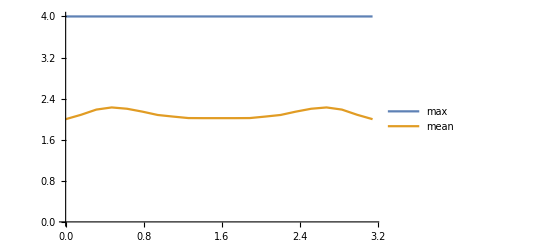

```mathematica
ListLinePlot[{Efibomax,Efibomean},PlotLegends->{"max","mean"}]
```

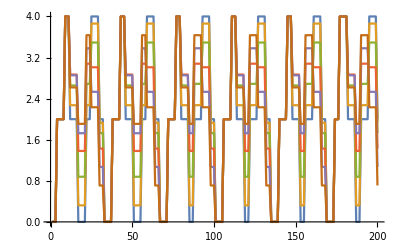

```mathematica
ListLinePlot[Table[Efibon[[n]],{n,1,6}]]
```

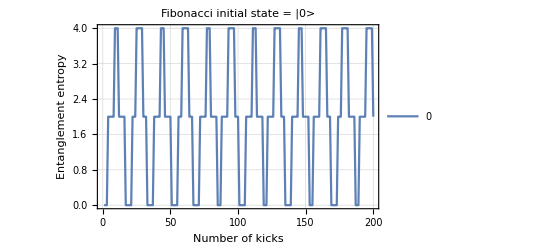

```mathematica
ListLinePlot[Efibon[[1]],PlotTheme->"Detailed",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of kicks],None}},LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]},PlotLabel->"Fibonacci initial state = |0>",PlotLegends->{"0 ","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"}, PlotRange->All]
```

## CC correct dt = pi/8

### data

```mathematica
Ecfib = {-0.000000000000000000*10^+00,1.201752073385713215*10^+00,2.147215261966106681*10^+00,2.980311118227134237*10^+00,2.983473152365783587*10^+00,3.190486506885002793*10^+00,3.003149006367099361*10^+00,3.017739709609570831*10^+00,3.076766905607788427*10^+00,2.044558584668085821*10^+00,9.811705698383846874*10^-01,8.563687064882740119*10^-01,6.355290178348754759*10^-01,1.690341094113216425*10^+00,2.174409358292292538*10^+00,2.790218169034386797*10^+00,2.436667342952632431*10^+00,2.640419545057362427*10^+00,1.998856569814058570*10^+00,1.820018384869941608*10^+00,9.135205081104528224*10^-01,1.200180405610195233*10^+00,1.083139224357154484*10^+00,2.121450980161981192*10^+00,3.237542875706666212*10^+00,3.047887058753243394*10^+00,3.172627538542919012*10^+00,3.109523520517791795*10^+00,2.832613560652265328*10^+00,2.858729262069013899*10^+00,2.028383163789666099*10^+00,1.327057402920753137*10^+00,1.548298811727928659*10^-01,1.333452594532903213*10^+00,2.076116675760072194*10^+00,2.860403466633244740*10^+00,2.757859792436315072*10^+00,2.055371187058770754*10^+00,2.072242922912448826*10^+00,2.628640365268473111*10^+00,1.904649134760731055*10^+00,1.591663927642144039*10^+00,1.025366557636723908*10^+00,1.365097782658955650*10^+00,1.773234001727937326*10^+00,2.357928599236838618*10^+00,2.537213655201788765*10^+00,2.859447592854922338*10^+00,2.466279304323993671*10^+00,2.307101441613417236*10^+00,1.884522569194704289*10^+00,1.682708007415291807*10^+00,1.289616224770216757*10^+00,1.520520927283971702*10^+00,2.117364725993104990*10^+00,2.683616984654770832*10^+00,2.850261025291493056*10^+00,3.234793108316820653*10^+00,2.363704850836698679*10^+00,2.186491583210978362*10^+00,2.893136558667201097*10^+00,2.028988372612034574*10^+00,1.040187580114120935*10^+00,1.322573469155323478*10^+00,1.080705700522831991*10^+00,1.981301186671939440*10^+00,2.512795788366027239*10^+00,2.269663685680165077*10^+00,1.452617728047451484*10^+00,1.424559618020412088*10^+00,1.996218913539946183*10^+00,2.099693142806486890*10^+00,2.248853056019737284*10^+00,1.702708477118580310*10^+00,1.916376543881658012*10^+00,2.414856085578723111*10^+00,2.683657799776372421*10^+00,2.186483150710035517*10^+00,1.362171973655532664*10^+00,1.100466510176957291*10^+00,1.127058257607413516*10^+00,2.124999471853426414*10^+00,2.815180559456886833*10^+00,2.287267845755840412*10^+00,1.998251591624461643*10^+00,2.700516963165546347*10^+00,2.780524793966112185*10^+00,2.350243568868702226*10^+00,1.820443918559447427*10^+00,1.431468517732048085*10^+00,1.336950806993516316*10^+00,1.617698090415109036*10^+00,1.743935755236771135*10^+00,2.052618512408205032*10^+00,2.119737561771326995*10^+00,2.419051382012674445*10^+00,2.729753012482850405*10^+00,2.232458020512198882*10^+00,1.499623048829635152*10^+00,8.156527464377889558*10^-01,1.164192431726162269*10^+00,1.790702892389543832*10^+00,2.190479678382142303*10^+00,2.633388206982167912*10^+00,1.883941299062568131*10^+00,2.092461543806078961*10^+00,3.062586820884543481*10^+00,2.517617612292975426*10^+00,2.277483201305616767*10^+00,1.427223852125760750*10^+00,4.242748231825044791*10^-01,1.509285943791797813*10^+00,2.200993753715117407*10^+00,3.381568172996614940*10^+00,3.450912022454620143*10^+00,3.570436360257925656*10^+00,3.573814314496210010*10^+00,3.397817578946870753*10^+00,3.602264653707589748*10^+00,2.327231054694774315*10^+00,1.555264260726956671*10^+00,1.311039113479078866*10^+00,1.240431326201742346*10^+00,2.087220260614218503*10^+00,2.178407036499735661*10^+00,3.151358861153256363*10^+00,2.466908044602610595*10^+00,2.223832700704372556*10^+00,2.150730602835555505*10^+00,1.893497857492576264*10^+00,8.905434600720395499*10^-01,1.028419514384351086*10^+00,5.427667757378933366*10^-01,1.730269955346078969*10^+00,2.582055939003893741*10^+00,2.747062247087370235*10^+00,2.466209080120945973*10^+00,2.567942929765136384*10^+00,2.315563661485573910*10^+00,2.503412517169889107*10^+00,2.237021212113603941*10^+00,1.429092562885983186*10^+00,4.351162077591403388*10^-01,1.328347418594631790*10^+00,2.187475468065557038*10^+00,2.652706532095469250*10^+00,1.654611844280587940*10^+00,1.524600187082396197*10^+00,1.689408660206973112*10^+00,2.591122770346701465*10^+00,2.308779935690711049*10^+00,2.079479910654824071*10^+00,1.870501850488043960*10^+00,2.617804787979625125*10^+00,2.687949348269766947*10^+00,2.769132013809134207*10^+00,2.535759232836802823*10^+00,1.972467374783944738*10^+00,1.145893342337586773*10^+00,1.920902622756940570*10^+00,1.885122267436554866*10^+00,2.244459411248608038*10^+00,1.455061699918682727*10^+00,1.560301269721981576*10^+00,2.281640914803453324*10^+00,2.579018935240191990*10^+00,2.428802479064668063*10^+00,1.576756104624723154*10^+00,1.703978909859959368*10^+00,1.645394732144924488*10^+00,2.127746900226849647*10^+00,3.418739220912703658*10^+00,2.292544186920078442*10^+00,2.169583090365461597*10^+00,2.921120975877204096*10^+00,2.922101099925504375*10^+00,2.982103238263469791*10^+00,2.491962553955974879*10^+00,1.688999456221347284*10^+00,2.101201101791375869*10^+00,2.330397057538133865*10^+00,2.990732907346493885*10^+00,2.658993747179613010*10^+00,3.204305579691599792*10^+00,3.357932349200097200*10^+00,2.666146374768397109*10^+00,3.018268210746003266*10^+00,2.269497033366265182*10^+00,2.003206546492749318*10^+00,1.467853554061699928*10^+00,1.603176204825331297*10^+00,1.385888871637253050*10^+00,1.594351908382549698*10^+00,2.234370207523581175*10^+00,2.563521362119890235*10^+00,2.589301640622846623*10^+00,2.712860912016265225*10^+00,2.051134245650722221*10^+00,1.694821734834516480*10^+00,1.206850310011225780*10^+00,2.722912528242654327*10^-14,1.201752073385712993*10^+00,2.130597445629470510*10^+00,2.963712956542957411*10^+00,2.956054022331997100*10^+00,3.147520794475251904*10^+00,2.951859664063290367*10^+00,2.978396043217354627*10^+00,3.016722847173458621*10^+00,2.082350249343919657*10^+00,1.062796745691709566*10^+00,9.300784156808608039*10^-01,6.540378287116985767*10^-01,1.670673434295161242*10^+00,2.125847674796547793*10^+00,2.738252851409566979*10^+00,2.465637750555532914*10^+00,2.609007650843539583*10^+00,1.961352122872105586*10^+00,1.837206133208790781*10^+00,1.046854265555713814*10^+00,1.365922504396455794*10^+00,1.338910699524973769*10^+00,2.254634288076496240*10^+00,3.192294679466635365*10^+00,2.987859049419657964*10^+00,3.114155880266737508*10^+00,3.071818449617606195*10^+00,2.750440667387591631*10^+00,2.803597240932230505*10^+00,1.979291351452426628*10^+00,1.383761442323396373*10^+00,2.873497985331403548*10^-01,1.403033879376609283*10^+00,2.055515222762991812*10^+00,2.791542864479734209*10^+00,2.749544095766843554*10^+00,2.181443196178471045*10^+00,2.174520031394803876*10^+00,2.627331765389779861*10^+00,1.905263073569647858*10^+00,1.608429868990294276*10^+00,1.021745205703571191*10^+00,1.384277875513495459*10^+00,1.764547304050367860*10^+00,2.344992462507819120*10^+00,2.482272512469047676*10^+00,2.780864871428805785*10^+00,2.437216319915096907*10^+00,2.324229361226817225*10^+00,1.873760129616112602*10^+00,1.713430674939291354*10^+00,1.288047040281485867*10^+00,1.528559296928861500*10^+00,2.140507924460985922*10^+00,2.754127206296333341*10^+00,2.874982579670536609*10^+00,3.157757954807516754*10^+00,2.334304599713771022*10^+00,2.170815824993101995*10^+00,2.873159953802276956*10^+00,2.134755162990883193*10^+00,1.206039047296308730*10^+00,1.391054046354742280*10^+00,1.115789633983198970*10^+00,1.985959834512552868*10^+00,2.496336924858389317*10^+00,2.337650738871640321*10^+00,1.602545794794269174*10^+00,1.549690978572223710*10^+00,2.122797389004815294*10^+00,2.255322661708362375*10^+00,2.410159074770758636*10^+00,1.859854606930888554*10^+00,1.999177835079698040*10^+00,2.461740931770180385*10^+00,2.681081772567132759*10^+00,2.247350930984620465*10^+00,1.479938299171041916*10^+00,1.291801731723741131*10^+00,1.336257442807335050*10^+00,2.237846519948852198*10^+00,2.808463519484953430*10^+00,2.284738661425272266*10^+00,1.999817097627664353*10^+00,2.659098343297275679*10^+00,2.756156007450015100*10^+00,2.416213674417681201*10^+00,1.860236149370772418*10^+00,1.412998974002122710*10^+00,1.241088245219874597*10^+00,1.595129261222438588*10^+00,1.731927234629050627*10^+00,2.056208574506383169*10^+00,2.065309578540633240*10^+00,2.341618562679410598*10^+00,2.662123484666309992*10^+00,2.243686728660718721*10^+00,1.585771553437537396*10^+00,8.882063300679192697*10^-01,1.179907119578165631*10^+00,1.765014508129896464*10^+00,2.199810574889240922*10^+00,2.678601687738955128*10^+00,1.957273149979442683*10^+00,2.132667756119756231*10^+00,3.038507839583233672*10^+00,2.526149224903571078*10^+00,2.338065278169582761*10^+00,1.644946062644695450*10^+00,7.412272687755061540*10^-01,1.692063615771970841*10^+00,2.271157355291932411*10^+00,3.326526585098633859*10^+00,3.371788629840319018*10^+00,3.543734985288219175*10^+00,3.503897769028183617*10^+00,3.317098186167534823*10^+00,3.529937777189434023*10^+00,2.512946239238770918*10^+00,1.832084020633065080*10^+00,1.556001178243856753*10^+00,1.441780924331450997*10^+00,2.134041510851727441*10^+00,2.215120578933980955*10^+00,3.098410755545033535*10^+00,2.454488623644116796*10^+00,2.175837552387719587*10^+00,2.101084973172953951*10^+00,1.893444477400254788*10^+00,9.704083230938140847*10^-01,1.066906606793524670*10^+00,6.037843057984686457*10^-01,1.747418435484454857*10^+00,2.550962737098321220*10^+00,2.736859435898175263*10^+00,2.460917945611427182*10^+00,2.555378086616687749*10^+00,2.312507905893141036*10^+00,2.505217868985520013*10^+00,2.233010982502456443*10^+00,1.479331582955360824*10^+00,5.272532612619291736*10^-01,1.380843091463932915*10^+00,2.158574853976380936*10^+00,2.649261918987964481*10^+00,1.693878218457052443*10^+00,1.596839003135303248*10^+00,1.733668208326506921*10^+00,2.621687053677528301*10^+00,2.324745182411013023*10^+00,2.082853631798539773*10^+00,1.852671794920277115*10^+00,2.596449726103089883*10^+00,2.688887981460692966*10^+00,2.772662993119791253*10^+00,2.554970603455652522*10^+00,2.046068794488166809*10^+00,1.229760700850471178*10^+00,1.935049147608778108*10^+00,1.919383316397017758*10^+00,2.249649575600829454*10^+00,1.480710997753518221*10^+00,1.536016999234835811*10^+00,2.218048816497526943*10^+00,2.525312069768572698*10^+00,2.410675564384718417*10^+00,1.693967552042315861*10^+00,1.801200480080911603*10^+00,1.711635902683166233*10^+00,2.164540521665780926*10^+00,3.370359369349982259*10^+00,2.307987101514621830*10^+00,2.203881342272550725*10^+00,2.876510770613100565*10^+00,2.903757560387226988*10^+00,2.957926047084742383*10^+00,2.467454628162023322*10^+00,1.661100472134678485*10^+00,2.055693859559523773*10^+00,2.319948523496376147*10^+00,3.000090820059925001*10^+00,2.734375343098981670*10^+00,3.214221086044125819*10^+00,3.284953733776634799*10^+00,2.638763097637353283*10^+00,2.901197689720749651*10^+00,2.191686794324962051*10^+00,1.912957828958338435*10^+00,1.411639804820645994*10^+00,1.517108860356200628*10^+00,1.391519050815813285*10^+00,1.559770364695866274*10^+00,2.225489981998173494*10^+00,2.576377373784306979*10^+00,2.608024259144384960*10^+00,2.685092273149042086*10^+00,2.065176831138363145*10^+00,1.747166711494211544*10^+00,1.296837818392519326*10^+00,-9.610279511444755881*10^-16,1.201752073385714326*10^+00,2.083205861098789136*10^+00,2.913470658476406960*10^+00,2.866985934804621383*10^+00,3.028497442668004247*10^+00,2.801556519787624211*10^+00,2.859725405507548945*10^+00,2.839309843398216682*10^+00,2.156978721153669731*10^+00,1.252645534984635711*10^+00,1.129317256721594109*10^+00,7.663371386017064912*10^-01,1.689793112486697169*10^+00,2.034160744335254734*10^+00,2.608407523354441260*10^+00,2.534309301517926993*10^+00,2.560954840441917568*10^+00,1.922895651238542891*10^+00,1.863615748559771745*10^+00,1.321066421646680755*10^+00,1.750015733929221051*10^+00,1.843647586360119384*10^+00,2.557149464820636098*10^+00,3.080181703895944700*10^+00,2.825768493300073736*10^+00,2.957502982754513177*10^+00,2.951531968371261527*10^+00,2.572467084791825176*10^+00,2.673333795249211775*10^+00,1.905707644456027028*10^+00,1.575811429671396979*10^+00,6.254330962328393806*10^-01,1.603485836606878712*10^+00,2.005820316473958531*10^+00,2.587718464468858670*10^+00,2.725126937489449119*10^+00,2.440113594741311065*10^+00,2.380264312003246729*10^+00,2.622022673773762858*10^+00,1.887284129265768495*10^+00,1.646159084025416774*10^+00,1.042801811528865974*10^+00,1.407606194114390918*10^+00,1.729874875269589829*10^+00,2.250019664479750325*10^+00,2.311043816237245530*10^+00,2.576986444340473525*10^+00,2.376957473119776676*10^+00,2.392912425695194134*10^+00,1.947826554494709095*10^+00,1.829329841814149704*10^+00,1.331692863571612762*10^+00,1.582834099529337735*10^+00,2.191221725452498603*10^+00,2.844161773233864654*10^+00,2.899460232987463915*10^+00,2.976888014426099183*10^+00,2.276919419404970668*10^+00,2.151089425126222476*10^+00,2.840929330980737078*10^+00,2.387626142885637570*10^+00,1.578243115400020713*10^+00,1.578260350308123394*10^+00,1.241680594829047912*10^+00,1.977707885795898290*10^+00,2.418909552240022798*10^+00,2.441673726617875850*10^+00,1.883701925436706670*10^+00,1.814568162939250051*10^+00,2.371116469051862019*10^+00,2.533181138536897414*10^+00,2.675803813949869436*10^+00,2.109749323777644570*10^+00,2.157682056709935292*10^+00,2.518426498825484305*10^+00,2.617046211522595645*10^+00,2.328125793145323641*10^+00,1.738680162932547457*10^+00,1.644307733397649240*10^+00,1.719728944121046377*10^+00,2.474958353811737233*10^+00,2.789095283629079436*10^+00,2.286521757622121065*10^+00,2.020948953489503985*10^+00,2.553736626359741191*10^+00,2.662091755546143190*10^+00,2.529742813513239152*10^+00,1.936509728572435973*10^+00,1.389317769205271169*10^+00,1.087538422205960531*10^+00,1.551838264472659823*10^+00,1.736381680538241934*10^+00,2.100973358703858818*10^+00,1.939542256278393939*10^+00,2.149302260290598010*10^+00,2.488172406159544714*10^+00,2.249246719949444362*10^+00,1.719531603576939904*10^+00,1.034969963409783311*10^+00,1.239226658372079015*10^+00,1.750512481610557058*10^+00,2.213759942741094999*10^+00,2.792456402387467840*10^+00,2.148209658609073536*10^+00,2.251004251194425709*10^+00,2.958499268969944751*10^+00,2.505988067210406456*10^+00,2.407297787972642489*10^+00,2.033554775115257840*10^+00,1.324861035611766491*10^+00,2.065517636534924595*10^+00,2.412753437013423596*10^+00,3.173813399494568088*10^+00,3.152582252208904645*10^+00,3.473141910546395650*10^+00,3.315970916894233955*10^+00,3.088966179897331354*10^+00,3.342012820256672345*10^+00,2.828447986340373532*10^+00,2.328987947693929694*10^+00,1.993077698748109139*10^+00,1.849070266624516679*10^+00,2.242980150385929683*10^+00,2.297966113806837019*10^+00,3.006246862314050361*10^+00,2.426462577133534637*10^+00,2.063785384575661297*10^+00,1.976612692563744389*10^+00,1.917559480710083974*10^+00,1.148994393118885959*10^+00,1.242947916943934583*10^+00,8.067190387197124002*10^-01,1.826758492477644324*10^+00,2.476269352617214370*10^+00,2.703573948581809994*10^+00,2.432166293324986128*10^+00,2.514289846689376162*10^+00,2.296170023473181665*10^+00,2.510434294085258866*10^+00,2.227340843440833495*10^+00,1.584609569312464439*10^+00,7.377139096405137542*10^-01,1.466309412031102433*10^+00,2.070837221991122856*10^+00,2.578158724333001750*10^+00,1.776432889891190303*10^+00,1.735223939084350464*10^+00,1.814880416083359815*10^+00,2.675621298807041359*10^+00,2.352449939602054840*10^+00,2.108895573729565154*10^+00,1.846419763014628401*10^+00,2.553229336726901000*10^+00,2.667240755621981485*10^+00,2.730775039698889906*10^+00,2.540185064164018236*10^+00,2.186628388160721581*10^+00,1.463079510716989162*10^+00,2.026523021162880855*10^+00,2.051066915130465240*10^+00,2.311059432793996393*10^+00,1.596256853062077541*10^+00,1.585093738052238965*10^+00,2.136589003636905737*10^+00,2.435297683053357698*10^+00,2.403144849995885401*10^+00,1.975016108864006359*10^+00,2.003864549126376016*10^+00,1.870672715063577130*10^+00,2.256546070864751119*10^+00,3.244063964735235839*10^+00,2.322707221580385006*10^+00,2.268403895353189537*10^+00,2.736009907381780071*10^+00,2.837418491878429982*10^+00,2.870778932942576134*10^+00,2.401660391672503447*10^+00,1.604432325387538549*10^+00,1.946225787297192200*10^+00,2.307630089024867992*10^+00,3.014456814990166045*10^+00,2.896994275269103358*10^+00,3.242738225494667059*10^+00,3.109779462540434025*10^+00,2.587856042673013057*10^+00,2.645776292531687002*10^+00,2.034572805188567646*10^+00,1.732881893035234988*10^+00,1.331526643392649811*10^+00,1.394481137282381766*10^+00,1.409958750135912986*10^+00,1.514445918744582453*10^+00,2.231462354912694845*10^+00,2.592246417799418445*10^+00,2.628583131607312495*10^+00,2.595634634458818368*10^+00,2.093248695913293655*10^+00,1.839117987251283948*10^+00,1.502547108636824946*10^+00,9.610279511444749964*10^-16,1.201752073385713659*10^+00,2.011928759656730126*10^+00,2.828972940317885154*10^+00,2.715141615275221021*10^+00,2.860738415467841023*10^+00,2.581734205073601629*10^+00,2.677214846491740907*10^+00,2.570712640123304915*10^+00,2.212796637679170342*10^+00,1.481210627576710515*10^+00,1.420425353222136478*10^+00,9.916327930186994433*10^-01,1.786669599517883622*10^+00,2.003591812560728158*10^+00,2.503230577824239855*10^+00,2.613997029150452178*10^+00,2.547413817720876050*10^+00,1.923647838390241338*10^+00,1.869026294502050378*10^+00,1.589097640790392951*10^+00,2.108300626374833175*10^+00,2.311376643660374874*10^+00,2.805817405186922464*10^+00,2.950404080068904200*10^+00,2.602717206878189860*10^+00,2.733438323516914181*10^+00,2.775278809077480702*10^+00,2.354735140982337160*10^+00,2.562206519925217751*10^+00,1.889982124391190066*10^+00,1.818996190027217352*10^+00,1.041073668350559700*10^+00,1.771963385766930354*10^+00,1.873539925115869309*10^+00,2.298496320621720823*10^+00,2.632408052943704391*10^+00,2.721507541474259106*10^+00,2.586987592541980074*10^+00,2.630273097535032800*10^+00,1.874467500163340183*10^+00,1.706200498154742728*10^+00,1.096077614892128071*10^+00,1.420838921246000197*10^+00,1.611339870102398431*10^+00,2.036312260201475599*10^+00,2.043347020778514711*10^+00,2.331247968272118776*10^+00,2.326403241725750526*10^+00,2.508579027500932312*10^+00,2.111626031727799280*10^+00,2.016558774438767632*10^+00,1.456671041046962323*10^+00,1.636351600962610675*10^+00,2.168068164895508687*10^+00,2.788075597344572110*10^+00,2.812693333715843735*10^+00,2.773241368883974101*10^+00,2.237754449379883326*10^+00,2.152241221013872163*10^+00,2.805099105564263340*10^+00,2.626932822590289707*10^+00,1.981261950041738995*10^+00,1.798822006397347240*10^+00,1.395261418340888460*10^+00,1.898169310055572767*10^+00,2.219002209947724680*10^+00,2.431547428188154836*10^+00,2.062021140443483613*10^+00,2.050018089669845445*10^+00,2.580271998733624894*10^+00,2.743922201221421275*10^+00,2.837171112340305612*10^+00,2.286218065961754586*10^+00,2.231795779889845566*10^+00,2.465785800084155266*10^+00,2.386589647474629317*10^+00,2.306630268273441864*10^+00,1.925900968600341656*10^+00,1.991345172293895960*10^+00,2.110502359043096021*10^+00,2.704418894478434865*10^+00,2.772132192112428228*10^+00,2.289556743078867918*10^+00,2.039431931586635383*10^+00,2.425861035770632501*10^+00,2.528339981998961594*10^+00,2.539863234019357208*10^+00,1.947623585898054177*10^+00,1.443677781332044718*10^+00,1.038891244308700390*10^+00,1.592846960030788184*10^+00,1.841605114230272289*10^+00,2.180579432175901999*10^+00,1.863998259489888731*10^+00,1.932794289074917904*10^+00,2.230682511876847407*10^+00,2.120503432830189716*10^+00,1.764800663897551969*10^+00,1.180476032160381994*10^+00,1.315947002235972718*10^+00,1.730462967754168524*10^+00,2.210885054877749667*10^+00,2.884334877723623958*10^+00,2.382884517351392617*10^+00,2.424708681382747422*10^+00,2.810312704129920292*10^+00,2.384504223972874648*10^+00,2.345206139385988653*10^+00,2.314423236614242985*10^+00,1.838204423697360035*10^+00,2.392424734952511400*10^+00,2.482753723143935165*10^+00,2.945476400134415584*10^+00,2.885263989113917127*10^+00,3.347448599281444892*10^+00,3.077457105713627072*10^+00,2.782815996459905961*10^+00,3.106734597109390705*10^+00,3.009217601774654582*10^+00,2.728858809096594840*10^+00,2.368165179052200919*10^+00,2.165929664686085498*10^+00,2.295608962273353093*10^+00,2.384691972841721963*10^+00,2.936265003034487897*10^+00,2.424353949034802724*10^+00,1.958946562454583207*10^+00,1.838988720830477375*10^+00,1.960695165876434887*10^+00,1.378697990471668522*10^+00,1.531425310348328850*10^+00,1.101537835392850440*10^+00,1.944344629207805930*10^+00,2.396019050107585535*10^+00,2.628413321995664909*10^+00,2.382962820084775668*10^+00,2.444597746778033542*10^+00,2.258557902655469185*10^+00,2.516219478907659735*10^+00,2.210706280177077154*10^+00,1.688340617794913845*10^+00,9.133453119869926473*10^-01,1.499348761802883789*10^+00,1.899258536131603226*10^+00,2.441477706633595091*10^+00,1.833803060257775508*10^+00,1.864776524999745888*10^+00,1.907500920101960151*10^+00,2.687564125935997250*10^+00,2.380003193155228125*10^+00,2.196766407443241143*10^+00,1.885607692098160815*10^+00,2.520834019466061893*10^+00,2.576230376374956776*10^+00,2.603910101399506072*10^+00,2.380657899306608538*10^+00,2.249482418446522303*10^+00,1.696890325777912212*10^+00,2.156214016330116223*10^+00,2.262327700576817424*10^+00,2.445067866321439354*10^+00,1.833077062754783659*10^+00,1.799984912766022349*10^+00,2.165892727138456486*10^+00,2.401945214379112237*10^+00,2.427636140459052072*10^+00,2.276937035743527460*10^+00,2.185472774854931188*10^+00,2.005621935532780231*10^+00,2.335353765135967485*10^+00,3.056149493158631270*10^+00,2.280530689177563186*10^+00,2.286208230185293733*10^+00,2.485488030331749254*10^+00,2.695599859483933880*10^+00,2.693324291513579549*10^+00,2.333840413009945713*10^+00,1.530506530458326075*10^+00,1.800507020055690521*10^+00,2.256274906144820402*10^+00,2.998190737849616649*10^+00,3.053974810332111378*10^+00,3.248913636112053194*10^+00,2.910714264312327160*10^+00,2.552548962722167580*10^+00,2.435951140239808410*10^+00,1.971736796957472171*10^+00,1.659311502278336459*10^+00,1.380977954285697251*10^+00,1.353283673589380065*10^+00,1.504761735879709184*10^+00,1.600062900750831352*10^+00,2.318067878202049847*10^+00,2.580192885593463714*10^+00,2.601912201487055931*10^+00,2.454087299137460931*10^+00,2.122877186374809710*10^+00,1.924215507697499605*10^+00,1.764181119453447355*10^+00,4.805139755722374982*10^-16,1.201752073385713881*10^+00,1.926685354281867602*10^+00,2.712859046100795091*10^+00,2.532683220742635299*10^+00,2.683247235337065995*10^+00,2.341866467013092645*10^+00,2.474293663528259746*10^+00,2.328127670255625059*10^+00,2.218641759067745411*10^+00,1.666372915000769783*10^+00,1.659593589385851775*10^+00,1.232788886738718004*10^+00,1.930640170063037342*10^+00,2.086901771129697547*10^+00,2.499347889999905981*10^+00,2.716473997602222301*10^+00,2.611378874233740710*10^+00,2.026401895469546410*10^+00,1.901288001044661113*10^+00,1.781814828715812427*10^+00,2.327754327555552116*10^+00,2.581654627738659169*10^+00,2.934889817102388054*10^+00,2.860546436292453976*10^+00,2.390526691282723881*10^+00,2.498042988077463722*10^+00,2.556060349535162146*10^+00,2.153038827459679005*10^+00,2.499617695478300483*10^+00,1.963202636777348520*10^+00,2.016712759735581173*10^+00,1.414756011533767843*10^+00,1.854562635764952949*10^+00,1.672282768209522041*10^+00,2.051116222725117844*10^+00,2.530291525370213179*10^+00,2.918975262585649322*10^+00,2.762258230812887128*10^+00,2.674166732418085779*10^+00,1.893909100010713109*10^+00,1.782405839362997568*10^+00,1.223348689795763500*10^+00,1.505878358999480193*10^+00,1.561695349578523961*10^+00,1.794208966887450352*10^+00,1.785598450164762818*10^+00,2.129777730243529899*10^+00,2.288624453898148392*10^+00,2.606291515955311500*10^+00,2.304963866301569908*10^+00,2.193774205019499490*10^+00,1.588498457297463196*10^+00,1.618251868753522782*10^+00,2.015357158332074405*10^+00,2.538245477131794381*10^+00,2.584541377484027347*10^+00,2.565201936740006960*10^+00,2.219502177250630481*10^+00,2.141220240550207876*10^+00,2.701605309531757371*10^+00,2.720805062865426560*10^+00,2.222201600780249198*10^+00,1.969772461414246445*10^+00,1.464547240684840546*10^+00,1.701062154452749109*10^+00,1.906992639314861737*10^+00,2.252909664374158627*10^+00,2.059721611826752508*10^+00,2.204033264931078318*10^+00,2.677771591977427867*10^+00,2.831960089942668013*10^+00,2.860349559445396928*10^+00,2.357081695291907586*10^+00,2.166844395112026422*10^+00,2.237389131677755660*10^+00,2.032789415909905362*10^+00,2.162561713766746330*10^+00,2.003876387409697202*10^+00,2.247088797906163116*10^+00,2.385355738023872796*10^+00,2.807041919861230639*10^+00,2.736092325236098244*10^+00,2.290500091034231467*10^+00,2.076010772524999659*10^+00,2.367165087153875636*10^+00,2.394432172094848710*10^+00,2.431055210572663494*10^+00,1.869420086298645423*10^+00,1.523537808266334004*10^+00,1.150893976259709017*10^+00,1.754267104808568511*10^+00,2.040950051548785726*10^+00,2.259262367416503103*10^+00,1.816009743628141493*10^+00,1.734570512624724170*10^+00,1.939995023675501251*10^+00,1.905993253250821695*10^+00,1.732408966448613530*10^+00,1.292957783364922619*10^+00,1.418119347685830922*10^+00,1.725079280902116263*10^+00,2.190125179762974383*10^+00,2.889898903314779943*10^+00,2.567894830646960447*10^+00,2.567783441664514221*10^+00,2.607369544574404507*10^+00,2.135822903878627166*10^+00,2.087869779785767488*10^+00,2.354720020785298296*10^+00,2.109085517079289929*10^+00,2.525761091702663386*10^+00,2.416437275339998081*10^+00,2.672379777411633128*10^+00,2.614184669252537674*10^+00,3.190334793948826686*10^+00,2.878118075645743623*10^+00,2.533411660258443554*10^+00,2.997070207340010839*10^+00,3.022559668756014783*10^+00,2.916678163787172817*10^+00,2.589009965679228920*10^+00,2.358670621024393732*10^+00,2.301682255448806558*10^+00,2.472250346566599255*10^+00,2.878572760708711264*10^+00,2.466835366981524835*10^+00,1.934997227360317096*10^+00,1.765287983713622832*10^+00,1.974569393669386441*10^+00,1.547296500147780751*10^+00,1.740871358948940628*10^+00,1.352847008586208544*10^+00,2.048035238300545124*10^+00,2.338697068745857255*10^+00,2.561637403573063132*10^+00,2.306561618781878931*10^+00,2.358028328185906020*10^+00,2.167294751071828340*10^+00,2.516263786762205079*10^+00,2.171886414687598243*10^+00,1.777047577644998322*10^+00,1.058408278994532603*10^+00,1.479764849087335854*10^+00,1.755207841951917480*10^+00,2.268784383086612344*10^+00,1.901950678047871435*10^+00,2.006208089601520861*10^+00,1.977466683515349377*10^+00,2.649287387515510961*10^+00,2.393598391045495433*10^+00,2.295352517561312311*10^+00,1.976524523111323539*10^+00,2.491972311572794752*10^+00,2.434421123017701749*10^+00,2.426006886039200339*10^+00,2.141776294793875657*10^+00,2.201334228251709213*10^+00,1.850876036864973484*10^+00,2.274232827613682950*10^+00,2.475669103025745166*10^+00,2.610706422868628529*10^+00,2.121014085648824654*10^+00,2.102563113776125814*10^+00,2.310192043914999438*10^+00,2.414497325196411026*10^+00,2.448750978930042344*10^+00,2.430650731720138680*10^+00,2.260033306809625664*10^+00,2.047301687897415512*10^+00,2.325453582945073094*10^+00,2.836567194260124936*10^+00,2.179103669360910267*10^+00,2.227660726439239625*10^+00,2.214641045434401878*10^+00,2.517624524182908718*10^+00,2.428401364410422758*10^+00,2.267994640165228226*10^+00,1.508284353212214324*10^+00,1.708081549941633304*10^+00,2.181873155934787256*10^+00,2.944734857015492757*10^+00,3.097040661340574541*10^+00,3.198547583566690555*10^+00,2.723315986245511411*10^+00,2.516253655340567441*10^+00,2.312588589452850840*10^+00,2.048491332172105217*10^+00,1.715787160231933672*10^+00,1.569839732843311797*10^+00,1.463505958918790872*10^+00,1.685976227767123525*10^+00,1.806859328707980605*10^+00,2.464446726045781855*10^+00,2.613959360500165641*10^+00,2.555679220146334529*10^+00,2.301514362266829039*10^+00,2.196981283257704476*10^+00,2.020801796708808773*10^+00,1.979447537091776343*10^+00,3.203426503814917641*10^-16,1.201752073385713659*10^+00,1.838431230982315867*10^+00,2.560205028005995587*10^+00,2.356003134974381297*10^+00,2.532194726697842402*10^+00,2.186263816890451128*10^+00,2.347260356393090497*10^+00,2.206745015947594979*10^+00,2.232323937927609858*10^+00,1.771095206724525362*10^+00,1.697557128345338562*10^+00,1.372538299438604392*10^+00,2.066147966635217159*10^+00,2.244896271939079035*10^+00,2.581896150935573786*10^+00,2.819069281985543185*10^+00,2.745489215148483542*10^+00,2.236516273184911086*10^+00,1.940891043735480270*10^+00,1.894323936170998257*10^+00,2.387004947557096024*10^+00,2.628558010888469632*10^+00,2.956880297798065271*10^+00,2.848179056268420162*10^+00,2.252678228625071721*10^+00,2.316053233642167974*10^+00,2.403863460663879348*10^+00,2.049817381398894245*10^+00,2.491860146361992712*10^+00,2.077126541365582391*10^+00,2.106562259056363295*10^+00,1.665644820108939994*10^+00,1.882468411202760983*10^+00,1.584280371664449127*10^+00,1.990468889649518847*10^+00,2.502539070621228490*10^+00,3.006685176766226597*10^+00,2.903819928741714573*10^+00,2.742828061961299468*10^+00,2.023661343977253502*10^+00,1.878032841949724308*10^+00,1.447242728740879336*10^+00,1.707150041352442527*10^+00,1.664989021377219380*10^+00,1.706616401780398196*10^+00,1.680354486998457242*10^+00,2.082344311886354493*10^+00,2.320553065338657461*10^+00,2.675746985196444605*10^+00,2.445923759042906820*10^+00,2.284282151610344425*10^+00,1.680449565730865125*10^+00,1.538083983770219376*10^+00,1.752565341714259706*10^+00,2.181138861944335261*10^+00,2.276015299061691088*10^+00,2.395103461726393768*10^+00,2.196555887642554161*10^+00,2.075087411884673827*10^+00,2.486686575136527022*10^+00,2.617808187022635291*10^+00,2.268820976573903803*10^+00,2.044301992667010737*10^+00,1.478609633914414134*10^+00,1.439487973692889167*10^+00,1.544726605345735360*10^+00,1.970464197103179327*10^+00,1.939286588341536000*10^+00,2.306661247944543192*10^+00,2.739475306252853404*10^+00,2.830391682982097201*10^+00,2.840182739388513511*10^+00,2.393166945705386794*10^+00,2.053260608018464328*10^+00,1.949263613956348173*10^+00,1.698303505860883522*10^+00,2.023538281715082210*10^+00,2.031790477853380406*10^+00,2.392800135127319816*10^+00,2.494097816483952901*10^+00,2.796442067543563503*10^+00,2.703404591203248941*10^+00,2.292668614124238502*10^+00,2.098065245156563119*10^+00,2.368046197250436080*10^+00,2.304858329021810537*10^+00,2.244057791108630351*10^+00,1.733382368114632976*10^+00,1.560470761174304277*10^+00,1.309381047701648981*10^+00,1.967093431135936044*10^+00,2.204042496869957457*10^+00,2.274303024463355527*10^+00,1.826411516821989212*10^+00,1.594793700227076005*10^+00,1.711694951267841880*10^+00,1.768371056202493463*10^+00,1.681008711774081288*10^+00,1.404020337406762131*10^+00,1.555816589795444127*10^+00,1.755817600766341746*10^+00,2.164326517697165553*10^+00,2.806798736638575598*10^+00,2.612583863466190870*10^+00,2.616049007211965094*10^+00,2.365853535244189398*10^+00,1.820927784568890928*10^+00,1.709417147184737029*10^+00,2.166602314691794096*10^+00,2.122006946948067352*10^+00,2.463204279851475498*10^+00,2.278309618190190733*10^+00,2.407729190043419898*10^+00,2.403006280118789917*10^+00,3.083874974027192017*10^+00,2.783923481885860696*10^+00,2.442653009900802807*10^+00,2.948732569439448614*10^+00,2.971504122779712542*10^+00,2.936643527886650062*10^+00,2.639945055092804083*10^+00,2.431651592608155443*10^+00,2.343998526409836192*10^+00,2.578212082472520983*10^+00,2.847544049493614615*10^+00,2.523200244375840562*10^+00,2.027267723024978707*10^+00,1.827683062808942882*10^+00,2.007040826959247237*10^+00,1.639840623473727055*10^+00,1.799203409623074013*10^+00,1.477418370931285585*10^+00,2.107125838834195797*10^+00,2.304882204862176653*10^+00,2.479360955065297301*10^+00,2.247491240428750370*10^+00,2.252605669262012889*10^+00,2.037124747844509809*10^+00,2.474136407056210185*10^+00,2.126177416783870289*10^+00,1.866402212135759742*10^+00,1.203462026914728256*10^+00,1.525077502350565384*10^+00,1.799053999365201939*10^+00,2.188030209506889978*10^+00,1.988554349839330548*10^+00,2.160510116018117266*10^+00,2.027148786006407022*10^+00,2.630365469398676215*10^+00,2.463017949714795485*10^+00,2.371364516961993907*10^+00,2.105455308383228363*10^+00,2.473544550136269393*10^+00,2.298500841128737981*10^+00,2.286162747411469631*10^+00,1.972668435945672760*10^+00,2.084376721170449809*10^+00,1.932117201978591048*10^+00,2.351294711627240908*10^+00,2.637307096027684761*10^+00,2.711800834712982944*10^+00,2.354655101600817257*10^+00,2.336386923456559295*10^+00,2.399472327879189404*10^+00,2.409864562005635591*10^+00,2.393391063113480932*10^+00,2.386937286977260264*10^+00,2.209939430940372596*10^+00,1.993595985703373819*10^+00,2.253705138809753095*10^+00,2.629004101023330708*10^+00,2.098915895573489010*10^+00,2.134511243602162711*10^+00,2.025038174988173623*10^+00,2.372849977013658851*10^+00,2.228384669513831184*10^+00,2.243510986324801948*10^+00,1.661707848732335346*10^+00,1.706863510418609842*10^+00,2.136290867679516481*10^+00,2.879580723530805297*10^+00,3.081743747213156137*10^+00,3.113075151319421696*10^+00,2.577724788978317250*10^+00,2.499652254737321222*10^+00,2.279289380509735174*10^+00,2.181363027526249443*10^+00,1.883943197171042527*10^+00,1.823186737761028242*10^+00,1.675751308144282081*10^+00,1.912564083149217664*10^+00,2.096530486654557102*10^+00,2.645495387967777390*10^+00,2.695000221165859688*10^+00,2.541201442932027987*10^+00,2.206420419612666883*10^+00,2.359616398311653818*10^+00,2.139660397450256379*10^+00,2.095120340606040799*10^+00,-9.610279511444755881*10^-16,1.201752073385713659*10^+00,1.738111176542852965*10^+00,2.422693186377240515*10^+00,2.287259436816589275*10^+00,2.424830809702130718*10^+00,2.124362826987056696*10^+00,2.306092016627590890*10^+00,2.209357501934697154*10^+00,2.227299711246215175*10^+00,1.811091888809160722*10^+00,1.572484205642797228*10^+00,1.377058128822466809*10^+00,2.140060631372520561*10^+00,2.369819522348658669*10^+00,2.664100055255030686*10^+00,2.877077143998765685*10^+00,2.912694844606221967*10^+00,2.476379117373747274*10^+00,1.968965127709865204*10^+00,1.929410238355706797*10^+00,2.332393857942434590*10^+00,2.545055032938550177*10^+00,2.930941189466454766*10^+00,2.861047724492382649*10^+00,2.210916602283004018*10^+00,2.230151309579158969*10^+00,2.335154795628143543*10^+00,2.058820017192612539*10^+00,2.550555781441636416*10^+00,2.223466394920914802*10^+00,2.092096756938147450*10^+00,1.787436142947558704*10^+00,1.904678196770545284*10^+00,1.717438747491943474*10^+00,2.230924836927301591*10^+00,2.616403781978627663*10^+00,3.015514795065080023*10^+00,3.013086165256217974*10^+00,2.825543617889442416*10^+00,2.229452889684780281*10^+00,1.964035772518030631*10^+00,1.678338915055213931*10^+00,1.986609071711295638*10^+00,1.946176384241462998*10^+00,1.942307480436134437*10^+00,1.855823569805516771*10^+00,2.201413800823034173*10^+00,2.448604960365982297*10^+00,2.763116996895144339*10^+00,2.500586775661560957*10^+00,2.272958739089085078*10^+00,1.778760806041995712*10^+00,1.464971633133878015*10^+00,1.521338968366644728*10^+00,1.888060961233449575*10^+00,2.017560251630383661*10^+00,2.291541096112072129*10^+00,2.173497840565149719*10^+00,1.950662751144919493*10^+00,2.181052348599346047*10^+00,2.401419272270878036*10^+00,2.162497095876118713*10^+00,2.039697744199819418*10^+00,1.494818105442013101*10^+00,1.199152364977784213*10^+00,1.267826875120378727*10^+00,1.751278126895697174*10^+00,1.817812137272597717*10^+00,2.366775862956375764*10^+00,2.718112065973858460*10^+00,2.769908522413108809*10^+00,2.791759868523231436*10^+00,2.442997292041919621*10^+00,2.014207345066030275*10^+00,1.750703155802428856*10^+00,1.528895530406665149*10^+00,2.022488476812249747*10^+00,2.158702447235363309*10^+00,2.468020481272825251*10^+00,2.488563590172971907*10^+00,2.735428742600392038*10^+00,2.711788390094886481*10^+00,2.298916368151691092*10^+00,2.143877727589672322*10^+00,2.409487803398178141*10^+00,2.276200411662579359*10^+00,2.056078439495492294*10^+00,1.634138998712581392*10^+00,1.576791656119042484*10^+00,1.454364910250639520*10^+00,2.154140095936290855*10^+00,2.269036738883463578*10^+00,2.223562000924044657*10^+00,1.882360759615468115*10^+00,1.553067658291076958*10^+00,1.623457241952908081*10^+00,1.796469521106081491*10^+00,1.672963427435081751*10^+00,1.546299036823192141*10^+00,1.718773189498555398*10^+00,1.833823015951484781*10^+00,2.099669294734914260*10^+00,2.632907975807204259*10^+00,2.502682358217646286*10^+00,2.545666025287943057*10^+00,2.158314203948306975*10^+00,1.517196655188864263*10^+00,1.376876095075963979*10^+00,1.919844144545688192*10^+00,1.973498982771086929*10^+00,2.318062654785457699*10^+00,2.184554665277423702*10^+00,2.212761494775729698*10^+00,2.290153962572204271*10^+00,3.053450108726009304*10^+00,2.760804468942767098*10^+00,2.466298453848729810*10^+00,2.887896389645368433*10^+00,2.959192688603902166*10^+00,2.881682352415895210*10^+00,2.599655797928282830*10^+00,2.429939617619844228*10^+00,2.410132043630844656*10^+00,2.690683428720147763*10^+00,2.828801658023492926*10^+00,2.546227189108056344*10^+00,2.203496636420256394*10^+00,1.998520718751288561*10^+00,2.024588562872185360*10^+00,1.676513762950627928*10^+00,1.720187260458709178*10^+00,1.494068815526871763*10^+00,2.111552814164654013*10^+00,2.269517802151151287*10^+00,2.333744889161432745*10^+00,2.169190965927174197*10^+00,2.139821627174564256*10^+00,1.888379150898884085*10^+00,2.400113882833822654*10^+00,2.125641142153398278*10^+00,1.951567452260664970*10^+00,1.394449167534806300*10^+00,1.725962223525288941*10^+00,2.059521172290802671*10^+00,2.245267077041604331*10^+00,2.143164216885933726*10^+00,2.319450945132808251*10^+00,2.102567891351843077*10^+00,2.671498333146905324*10^+00,2.619247814101710592*10^+00,2.420035484623168642*10^+00,2.264010834822065998*10^+00,2.490520714999487684*10^+00,2.237712651060526525*10^+00,2.289504639501057426*10^+00,2.009273701639234577*10^+00,2.000343790132038446*10^+00,1.966006335202930222*10^+00,2.396296089666929863*10^+00,2.712419444833336080*10^+00,2.686926762008356118*10^+00,2.444144305518156202*10^+00,2.432302128145711340*10^+00,2.388206380099138215*10^+00,2.352355575356591899*10^+00,2.258845127097818484*10^+00,2.181154495594268994*10^+00,2.051391383425307247*10^+00,1.913737816667054226*10^+00,2.150091199438430856*10^+00,2.522460317432893895*10^+00,2.113454382811695176*10^+00,2.104740165484060732*10^+00,1.992741260152752769*10^+00,2.344612226679316791*10^+00,2.179353045908731357*10^+00,2.297444707932227548*10^+00,1.945572807692385053*10^+00,1.799917008219841907*10^+00,2.079143592060822776*10^+00,2.825438193077952409*10^+00,3.068807115067901492*10^+00,3.060952640146724413*10^+00,2.492980711880514288*10^+00,2.528661771162163507*10^+00,2.358691691467530660*10^+00,2.343848191671845882*10^+00,2.096649242745329378*10^+00,2.037081145455311049*10^+00,1.924480712124149395*10^+00,2.155962045223752011*10^+00,2.449123750296253288*10^+00,2.814910493112604328*10^+00,2.828168173455186896*10^+00,2.584546271481107382*10^+00,2.233766221031051380*10^+00,2.593431790774663792*10^+00,2.304670930395896988*10^+00,2.119283545701129867*10^+00,-3.203426503814917641*10^-16,1.201752073385713437*10^+00,1.673065281775372837*10^+00,2.315910204717499532*10^+00,2.321604487641626857*10^+00,2.358606516997199254*10^+00,2.140791796020068194*10^+00,2.342444889578053857*10^+00,2.276510646744585031*10^+00,2.214733606065693028*10^+00,1.810465910602708783*10^+00,1.394538153097562017*10^+00,1.282574723346097123*10^+00,2.161968977987987817*10^+00,2.424834233775030601*10^+00,2.674485303049722873*10^+00,2.873303943834144558*10^+00,3.027399105064664031*10^+00,2.630751499007152105*10^+00,1.949770747940512194*10^+00,1.897843371264538614*10^+00,2.226004681668130480*10^+00,2.396644434341502983*10^+00,2.902054198937551011*10^+00,2.886548743687948448*10^+00,2.244765949543508388*10^+00,2.272814289089566842*10^+00,2.379554076030933718*10^+00,2.195125312790921157*10^+00,2.699264954448460152*10^+00,2.404814803093131559*10^+00,2.001927431186629303*10^+00,1.822403213358299023*10^+00,1.962808486429719945*10^+00,1.940734327337248155*10^+00,2.512293210558164347*10^+00,2.842550603548016142*10^+00,2.997928655492995809*10^+00,3.093004361795983925*10^+00,2.933788803436358172*10^+00,2.466580417388551272*10^+00,1.995727195976889634*10^+00,1.862574045743733420*10^+00,2.291917707263222859*10^+00,2.313736833092392420*10^+00,2.314940477695116794*10^+00,2.220206225128408484*10^+00,2.381140706252337313*10^+00,2.652916808298226847*10^+00,2.867936464754579529*10^+00,2.483595518932943946*10^+00,2.191187794297654534*10^+00,1.932182219927938371*10^+00,1.518485404867958355*10^+00,1.422736654138938572*10^+00,1.803585193070057713*10^+00,1.954494479050932432*10^+00,2.306080537434752387*10^+00,2.177116055718660181*10^+00,1.808149381737161665*10^+00,1.937225406130006489*10^+00,2.162907101943030153*10^+00,2.015535841995409694*10^+00,1.993705752004049092*10^+00,1.582473098114856480*10^+00,1.120832147121825217*10^+00,1.186295574447399748*10^+00,1.674223409164868892*10^+00,1.765997565702256189*10^+00,2.364373012117447992*10^+00,2.617543674112226881*10^+00,2.613976778978232662*10^+00,2.703336787314286394*10^+00,2.495635578375874353*10^+00,2.061952241063520042*10^+00,1.726921360086110191*10^+00,1.607772598952582399*10^+00,2.186899055357206301*10^+00,2.400372683610374924*10^+00,2.511711699429768352*10^+00,2.427254904149704906*10^+00,2.666571813740503671*10^+00,2.771099073731781104*10^+00,2.310229248831143334*10^+00,2.175985792352784998*10^+00,2.461272470341911767*10^+00,2.270064618466630879*10^+00,1.925634007203315567*10^+00,1.649894193439336965*10^+00,1.568193309257958745*10^+00,1.515632889890372148*10^+00,2.246201034027578203*10^+00,2.257463466167837218*10^+00,2.194949384987126884*10^+00,1.998695515341237794*10^+00,1.611207759630400638*10^+00,1.682635390426876487*10^+00,1.959301367223313495*10^+00,1.745815340866644805*10^+00,1.703665055339885992*10^+00,1.892701598630537108*10^+00,1.890542127814324402*10^+00,2.001470076583585556*10^+00,2.465640589861970433*10^+00,2.313036192105768052*10^+00,2.391444965523430000*10^+00,2.042722977660803796*10^+00,1.334800521171203069*10^+00,1.197859885677312386*10^+00,1.712978716724963490*10^+00,1.784807964573053907*10^+00,2.172240540960191701*10^+00,2.194831415302163524*10^+00,2.131286406737999517*10^+00,2.255347835144196900*10^+00,3.051779245567762366*10^+00,2.776428862453421242*10^+00,2.458807756799788358*10^+00,2.829470602883361163*10^+00,3.005099481397867311*10^+00,2.839967816718024007*10^+00,2.505907248606764171*10^+00,2.376781036767008359*10^+00,2.467573239140360641*10^+00,2.752135528860312874*10^+00,2.768665838290679027*10^+00,2.485037777570727968*10^+00,2.337138228302050535*10^+00,2.177667937285147737*10^+00,2.008951575836615433*10^+00,1.692022045939302277*10^+00,1.603130348749548961*10^+00,1.465007455333867670*10^+00,2.097237408919613966*10^+00,2.212225073252343410*10^+00,2.196589362651807598*10^+00,2.078735195413311310*10^+00,2.003908946860997631*10^+00,1.769819930654087381*10^+00,2.318205861490963748*10^+00,2.183395512813731898*10^+00,2.035595918442257179*10^+00,1.620231457777767670*10^+00,2.059810256302140541*10^+00,2.445793316526320815*10^+00,2.389565007623470905*10^+00,2.324229437849138158*10^+00,2.454190735184192729*10^+00,2.191225716621627129*10^+00,2.779567231651158821*10^+00,2.826067848444121289*10^+00,2.445122759677819779*10^+00,2.420475425468451736*10^+00,2.554095263714168063*10^+00,2.305168375812411963*10^+00,2.431236108703441978*10^+00,2.190956410247970609*10^+00,1.972589406682104807*10^+00,1.994610471124762530*10^+00,2.436811520903564343*10^+00,2.708154118217795947*10^+00,2.547376641400282526*10^+00,2.409348926270704627*10^+00,2.449465667457859652*10^+00,2.308681060352460790*10^+00,2.252076454964556440*10^+00,2.109804312458945841*10^+00,1.897826242524116580*10^+00,1.847481554666169146*10^+00,1.848858757016631937*10^+00,2.050205095931626698*10^+00,2.489797345259492367*10^+00,2.263989863540602165*10^+00,2.147459401616528041*10^+00,2.109869883568602944*10^+00,2.410441425478199839*10^+00,2.224418312207334658*10^+00,2.393044137900409041*10^+00,2.298234190787864950*10^+00,1.940133325658959906*10^+00,2.051515854511457349*10^+00,2.795122294432272447*10^+00,3.125591020114160123*10^+00,3.072527346937613757*10^+00,2.509817450142298068*10^+00,2.608184665913388489*10^+00,2.522978729856877322*10^+00,2.502775710867614301*10^+00,2.316842022711689708*10^+00,2.199788486527174403*10^+00,2.155990107440634684*10^+00,2.423776539084742332*10^+00,2.809733484217331601*10^+00,2.966880444792671323*10^+00,3.000196451265768616*10^+00,2.703084016617453678*10^+00,2.354293543863182236*10^+00,2.895398015625662236*10^+00,2.546714255798598892*10^+00,2.103314028340508735*10^+00,-3.203426503814917641*10^-16,1.201752073385713659*10^+00,1.625545790232590937*10^+00,2.231225312126128735*10^+00,2.396225981123556004*10^+00,2.321828752899553372*10^+00,2.191963201992137122*10^+00,2.380771938898363693*10^+00,2.324967440190667922*10^+00,2.194860966891542642*10^+00,1.840411121114233772*10^+00,1.223631307533755708*10^+00,1.177850133207256844*10^+00,2.165712968121932924*10^+00,2.451095304358297255*10^+00,2.659772252110700563*10^+00,2.838164504422827417*10^+00,3.086978652298065118*10^+00,2.694764771775981504*10^+00,1.888112165436323098*10^+00,1.860880297655319371*10^+00,2.094635525557452915*10^+00,2.270604089427812333*10^+00,2.877122789290140759*10^+00,2.909813194332979691*10^+00,2.315377470648539049*10^+00,2.403898551151627316*10^+00,2.462589632747295809*10^+00,2.372386856121400101*10^+00,2.927638882243440932*10^+00,2.554391943536958198*10^+00,1.881069180004053099*10^+00,1.799806137986836418*10^+00,2.025792754594937239*10^+00,2.142059410800080332*10^+00,2.706851307490703462*10^+00,3.094085294794855390*10^+00,2.985987510075969187*10^+00,3.143200835138927118*10^+00,3.048975582056030476*10^+00,2.646901780219971023*10^+00,1.986631266858811307*10^+00,1.974731764507179577*10^+00,2.518883337696447011*10^+00,2.662101462538253305*10^+00,2.662124728558252329*10^+00,2.578422072635213169*10^+00,2.527959695914788529*10^+00,2.852858254466885235*10^+00,2.980997609913043522*10^+00,2.428167328673722203*10^+00,2.079287264987104145*10^+00,2.103878930525063140*10^+00,1.655940495405229695*10^+00,1.514730017023507624*10^+00,1.916710429313291719*10^+00,2.135360768834253076*10^+00,2.393102951801410860*10^+00,2.192394441354895473*10^+00,1.716266138169646460*10^+00,1.772682737369092987*10^+00,1.983344402173806698*10^+00,1.873395009592590199*10^+00,1.957961693794447733*10^+00,1.734893293456963859*10^+00,1.215147917232513697*10^+00,1.289937324164812438*10^+00,1.692295206080617342*10^+00,1.789055168995719480*10^+00,2.334825832545187385*10^+00,2.502236811977794240*10^+00,2.412549906755871110*10^+00,2.609455276164976745*10^+00,2.583440960958537147*10^+00,2.145344665798074146*10^+00,1.839202721666870266*10^+00,1.827952741414414106*10^+00,2.434995361602114272*10^+00,2.692658917832247756*10^+00,2.536001817399009095*10^+00,2.352173470528597488*10^+00,2.620989669492436391*10^+00,2.870718364329569283*10^+00,2.315178542970392606*10^+00,2.190023231569912188*10^+00,2.502313272353171136*10^+00,2.269078853273623242*10^+00,1.860987281151418538*10^+00,1.741834424696243833*10^+00,1.564353817299251492*10^+00,1.542246380832976715*10^+00,2.306252617952893935*10^+00,2.226335147884172638*10^+00,2.167580620156378757*10^+00,2.143685282934722824*10^+00,1.728025778596225415*10^+00,1.839168490243756837*10^+00,2.159900593341979924*10^+00,1.902504990933782780*10^+00,1.845876063347649865*10^+00,2.047796493240135351*10^+00,1.929535859121619845*10^+00,1.885828177078042511*10^+00,2.326525421030089635*10^+00,2.156493294445203102*10^+00,2.221529077620892689*10^+00,2.031437881321144889*10^+00,1.265061049107438107*10^+00,1.200840462496261640*10^+00,1.612466368683464824*10^+00,1.654608479931849896*10^+00,2.080557148713817472*10^+00,2.288405905108952254*10^+00,2.158078724571006912*10^+00,2.286220276311522692*10^+00,3.038882518098368735*10^+00,2.786219081302639733*10^+00,2.431268157848474498*10^+00,2.749161431744085338*10^+00,3.067735112988392743*10^+00,2.825128250228662097*10^+00,2.395972135417898219*10^+00,2.279078136042754998*10^+00,2.447818794138571619*10^+00,2.746830766818419978*10^+00,2.657675819943069673*10^+00,2.369253736707022995*10^+00,2.411814084836942040*10^+00,2.307680886965436162*10^+00,1.974777212087365896*10^+00,1.725936005081698754*10^+00,1.509177796205748434*10^+00,1.437125989030826556*10^+00,2.064785356412133233*10^+00,2.119116321850736284*10^+00,2.026504492792339018*10^+00,2.002644693552575017*10^+00,1.877999350462874029*10^+00,1.731762020062637131*10^+00,2.277197059609569862*10^+00,2.285687643393975677*10^+00,2.096448539442203440*10^+00,1.820401919715106898*10^+00,2.394082312152590042*10^+00,2.819377866030631452*10^+00,2.543294162523129565*10^+00,2.490542336725773076*10^+00,2.564424029849422748*10^+00,2.278458969195524375*10^+00,2.910407434708489838*10^+00,3.023082188501309275*10^+00,2.457414608590404725*10^+00,2.550743348956070911*10^+00,2.651157613879572494*10^+00,2.437974445446589478*10^+00,2.605861214669051851*10^+00,2.400535230059553271*10^+00,1.984551284873896426*10^+00,2.030813355073756377*10^+00,2.491990623671749283*10^+00,2.666573298213341214*10^+00,2.365259711486435101*10^+00,2.306044463970359004*10^+00,2.410822480491602526*10^+00,2.204373660857402939*10^+00,2.178737844217555786*10^+00,1.993573470585514595*10^+00,1.607442374189660850*10^+00,1.619422525656318168*10^+00,1.836687863588940983*10^+00,1.967418822772697418*10^+00,2.452692933744407000*10^+00,2.443045737780086490*10^+00,2.217669621467353913*10^+00,2.264540961592584445*10^+00,2.521275110410681641*10^+00,2.317908560374916327*10^+00,2.472649490287249563*10^+00,2.613345619677847953*10^+00,2.071817939052087443*10^+00,2.032935627554778524*10^+00,2.793714201584102774*10^+00,3.227565100171199575*10^+00,3.129351598212607222*10^+00,2.568940138083700475*10^+00,2.749923376816083120*10^+00,2.739372114209825959*10^+00,2.644771812592129567*10^+00,2.493654956025316061*10^+00,2.310777089931264960*10^+00,2.340714310370811013*10^+00,2.656066522518695905*10^+00,3.147862472024971936*10^+00,3.116333749808569920*10^+00,3.163873051119776569*10^+00,2.891851538030572932*10^+00,2.517104003852811189*10^+00,3.169249919362712831*10^+00,2.819132987193100348*10^+00,2.101590792834813204*10^+00,-9.610279511444755881*10^-16,1.201752073385713437*10^+00,1.597023633820663813*10^+00,2.188076359508577262*10^+00,2.477524969045221681*10^+00,2.303674731632565642*10^+00,2.233692319791094505*10^+00,2.406185133052106906*10^+00,2.340486971187247800*10^+00,2.183523424307433736*10^+00,1.871594610477936849*10^+00,1.130872991237134251*10^+00,1.105894461412006979*10^+00,2.159905166542219757*10^+00,2.464333218239250556*10^+00,2.646209262444270571*10^+00,2.813197316450903429*10^+00,3.126031375581684202*10^+00,2.702845086442107636*10^+00,1.823358339040682230*10^+00,1.831476353797017120*10^+00,2.037174204328411342*10^+00,2.159709022165201553*10^+00,2.867901274254093025*10^+00,2.915220427337325226*10^+00,2.371041785133801483*10^+00,2.508211146106995582*10^+00,2.571367571754338499*10^+00,2.509557896372250241*10^+00,3.093345323127107971*10^+00,2.644877201612215067*10^+00,1.783531569679934314*10^+00,1.772149242404275071*10^+00,2.059718720200386599*10^+00,2.261432703102379094*10^+00,2.813270938770858987*10^+00,3.271514681764146726*10^+00,2.991833576560255725*10^+00,3.149839635718503672*10^+00,3.155841540116337551*10^+00,2.745524789644374408*10^+00,1.952661315401513331*10^+00,2.032514834859150188*10^+00,2.658409337597383182*10^+00,2.889431647295571892*10^+00,2.889661473878056164*10^+00,2.822446875852837600*10^+00,2.627288233306349419*10^+00,2.980452854336827606*10^+00,3.062625515523105690*10^+00,2.375748149736091275*10^+00,1.985831451181379048*10^+00,2.227734518694868271*10^+00,1.794116203943496135*10^+00,1.633203520886373994*10^+00,2.046397155783604482*10^+00,2.331136985066137868*10^+00,2.489398324905429227*10^+00,2.219043325226389918*10^+00,1.659724032282892781*10^+00,1.702385404898014709*10^+00,1.884569208649772953*10^+00,1.778858417097136879*10^+00,1.936276941514219363*10^+00,1.855442166125950809*10^+00,1.343389882107649314*10^+00,1.409250973335541612*10^+00,1.751331750654907315*10^+00,1.829810202625221649*10^+00,2.289887715417667557*10^+00,2.404193439681763689*10^+00,2.255089856585354102*10^+00,2.530761265227100321*10^+00,2.672794261511440617*10^+00,2.222621797716898495*10^+00,1.958591635525718910*10^+00,2.036271245072739156*10^+00,2.637397167408574550*10^+00,2.934007370097981848*10^+00,2.565260913986819435*10^+00,2.290394186144739663*10^+00,2.602619021685148581*10^+00,2.950185792089161207*10^+00,2.330213508008132983*10^+00,2.191467017521832261*10^+00,2.548443880742540024*10^+00,2.252035590576277002*10^+00,1.850798429564677328*10^+00,1.845366430192514340*10^+00,1.565214661410892605*10^+00,1.546047819135838219*10^+00,2.323967713819670156*10^+00,2.219571314596201272*10^+00,2.153108350450136932*10^+00,2.261610603810401354*10^+00,1.841364651309025824*10^+00,2.008103661370067794*10^+00,2.316615578817991850*10^+00,2.052965151349890327*10^+00,1.947994546547592076*10^+00,2.155123380334315275*10^+00,1.962549247616597548*10^+00,1.808908293670610457*10^+00,2.248049707831441424*10^+00,2.065158672162799469*10^+00,2.097988580427897265*10^+00,2.062610436835691008*10^+00,1.261558439823389222*10^+00,1.280406211865110500*10^+00,1.580858166111759111*10^+00,1.596089434552941722*10^+00,2.065400486329462382*10^+00,2.392830354661698689*10^+00,2.190742943552956401*10^+00,2.327848981556966734*10^+00,3.016382515770091199*10^+00,2.765043065780790510*10^+00,2.355694991826599693*10^+00,2.676994075813546203*10^+00,3.111304834563483723*10^+00,2.828339824074283193*10^+00,2.306817755414919624*10^+00,2.165980371129101467*10^+00,2.406161107458429704*10^+00,2.755421040787677356*10^+00,2.534199632685777193*10^+00,2.240275162161607714*10^+00,2.444992813236189555*10^+00,2.371298135400827345*10^+00,1.925334603834301772*10^+00,1.769167262251133632*10^+00,1.454696470907188122*10^+00,1.435365823662863249*10^+00,2.044832686544037159*10^+00,2.051390123137541988*10^+00,1.908959506340726309*10^+00,1.980837487136697606*10^+00,1.799661694285897173*10^+00,1.722685782604700844*10^+00,2.257930353983998994*10^+00,2.379624846403307181*10^+00,2.129711261369477526*10^+00,1.951225593912757628*10^+00,2.634154457301978169*10^+00,3.068205260588152683*10^+00,2.649456245593444947*10^+00,2.604302227638169320*10^+00,2.649388507380452396*10^+00,2.337978818026178462*10^+00,3.012429835386691401*10^+00,3.165476497219532614*10^+00,2.467507198024718296*10^+00,2.619971939056331411*10^+00,2.735714674434567950*10^+00,2.563893724985785827*10^+00,2.744494717791224669*10^+00,2.565578927636578577*10^+00,2.005516197061073314*10^+00,2.075408931165676485*10^+00,2.527475780774738112*10^+00,2.633838560834272258*10^+00,2.239219861348121121*10^+00,2.227760387628213046*10^+00,2.401017658227299290*10^+00,2.130775400734645775*10^+00,2.129568290717572143*10^+00,1.904412868866467878*10^+00,1.384228528510828227*10^+00,1.471071498400069233*10^+00,1.831807757071912235*10^+00,1.894554054004915722*10^+00,2.403476122417769201*10^+00,2.560063468326569502*10^+00,2.283010427533841202*10^+00,2.383275249706909626*10^+00,2.609719661730302676*10^+00,2.370112758340288561*10^+00,2.521944309872437007*10^+00,2.828717181763371613*10^+00,2.161450438482884095*10^+00,2.024950377358968545*10^+00,2.809705113406974597*10^+00,3.329228028193456534*10^+00,3.185148289524690757*10^+00,2.625522479430881795*10^+00,2.897115053646004856*10^+00,2.913620238796571726*10^+00,2.755886381986477396*10^+00,2.623917788498268955*10^+00,2.380305100413907748*10^+00,2.463650759168733551*10^+00,2.843875873695463241*10^+00,3.380076577120645354*10^+00,3.221558116041954634*10^+00,3.287915236063729374*10^+00,3.055232748267691534*10^+00,2.673438563161935733*10^+00,3.363001647483649936*10^+00,3.055177821947705930*10^+00,2.129841193356669216*10^+00,-0.000000000000000000*10^+00,1.201752073385712327*10^+00,1.587563349636247789*10^+00,2.173790848086061267*10^+00,2.519372131369849832*10^+00,2.298187100717196341*10^+00,2.246338982084042701*10^+00,2.414376702301243682*10^+00,2.353440156422215157*10^+00,2.176744782848378801*10^+00,1.886980654362438115*10^+00,1.102625028438169341*10^+00,1.081236266966527637*10^+00,2.149703524198589122*10^+00,2.471875093776314536*10^+00,2.629600008006749423*10^+00,2.815331978604349139*10^+00,3.135726557452675145*10^+00,2.709454073690184206*10^+00,1.795898848113297586*10^+00,1.817065997831025292*10^+00,2.015186448848752310*10^+00,2.130971760823397787*10^+00,2.861597508630453479*10^+00,2.920885047102499854*10^+00,2.391810400249324786*10^+00,2.554319559490490832*10^+00,2.608086989816444046*10^+00,2.573674430649013356*10^+00,3.154272352441842564*10^+00,2.670632040719595146*10^+00,1.738502179109971291*10^+00,1.758678040587990044*10^+00,2.079066661546204120*10^+00,2.299795187768066018*10^+00,2.844111468557610323*10^+00,3.336598272758853234*10^+00,3.001996220114218517*10^+00,3.167428779833372676*10^+00,3.188350873719022260*10^+00,2.776518261591111703*10^+00,1.935195327029266110*10^+00,2.045632027957902110*10^+00,2.704936468043579900*10^+00,2.964079523500000146*10^+00,2.966476285026511839*10^+00,2.903043311686657191*10^+00,2.666641202299437463*10^+00,3.024178057124700558*10^+00,3.097635721223953365*10^+00,2.347292057217854389*10^+00,1.950670913465466949*10^+00,2.271393151677387312*10^+00,1.859928567849710390*10^+00,1.702105163229635343*10^+00,2.102281205857691404*10^+00,2.424892876982543299*10^+00,2.537569094707413431*10^+00,2.243133371027808298*10^+00,1.645409701451680862*10^+00,1.682072826044673786*10^+00,1.861111146708599229*10^+00,1.755798864787333935*10^+00,1.930229663097263293*10^+00,1.902409014175307833*10^+00,1.411534437612612880*10^+00,1.460227715354223132*10^+00,1.774259553868259953*10^+00,1.844661902990174074*10^+00,2.271243642170436061*10^+00,2.373154838482007811*10^+00,2.192417897741906874*10^+00,2.517107851735924218*10^+00,2.719331127577187424*10^+00,2.253951785199754809*10^+00,2.003079096366941148*10^+00,2.113032613551962147*10^+00,2.714513432213031763*10^+00,3.021939983235907068*10^+00,2.579510935240085345*10^+00,2.266323867281036630*10^+00,2.593104092773442115*10^+00,2.981640506509415367*10^+00,2.326966990191353002*10^+00,2.200515190129676224*10^+00,2.559388269904018021*10^+00,2.241038821331853281*10^+00,1.850762177599563074*10^+00,1.887973719693036179*10^+00,1.566116629173188279*10^+00,1.545231540148871430*10^+00,2.327433089015167766*10^+00,2.216901143274671249*10^+00,2.153188297383243022*10^+00,2.316606071579018877*10^+00,1.881490230772349559*10^+00,2.070435874198885529*10^+00,2.375164172218388270*10^+00,2.112848312608174517*10^+00,1.985056601840598400*10^+00,2.204416975596785289*10^+00,1.970476642064298956*10^+00,1.781270007576502223*10^+00,2.225257303150852017*10^+00,2.030504242280981586*10^+00,2.064182231571044301*10^+00,2.076016262868026541*10^+00,1.278271942141548490*10^+00,1.316717676158864814*10^+00,1.576039515827553084*10^+00,1.583082041251314465*10^+00,2.061015550520333584*10^+00,2.457751456354385411*10^+00,2.216504035916502691*10^+00,2.341739086973039008*10^+00,3.005263189553776915*10^+00,2.753402866261315030*10^+00,2.324312824857037718*10^+00,2.657670503678447815*10^+00,3.122051712309008575*10^+00,2.831786468308967297*10^+00,2.272133198148315714*10^+00,2.108315456028597268*10^+00,2.386650950550390782*10^+00,2.754613121766712691*10^+00,2.474478670816471215*10^+00,2.177489854995217744*10^+00,2.448048942966299713*10^+00,2.394301893954541960*10^+00,1.903510023884625424*10^+00,1.789224714346291822*10^+00,1.437107823557778996*10^+00,1.431852236371434106*10^+00,2.032363005275944268*10^+00,2.018541474241801303*10^+00,1.876381129189186758*10^+00,1.985292583300756419*10^+00,1.782109247573432587*10^+00,1.722058065584722852*10^+00,2.249797450268373744*10^+00,2.416952154405698217*10^+00,2.139042052679973605*10^+00,1.991598879197930216*10^+00,2.726634922675034378*10^+00,3.154499767667967802*10^+00,2.682347213006623043*10^+00,2.641383410221801231*10^+00,2.672240504074259171*10^+00,2.358611025113751758*10^+00,3.050435632447677126*10^+00,3.217441559301958964*10^+00,2.482226531972905548*10^+00,2.641470748598990781*10^+00,2.768127858465796010*10^+00,2.608285986310536764*10^+00,2.796474462592081878*10^+00,2.622724796373172129*10^+00,2.008091692619379032*10^+00,2.089171841409113828*10^+00,2.540246749700893591*10^+00,2.615383246748437696*10^+00,2.192576287487668196*10^+00,2.214144444109723775*10^+00,2.391413047584537210*10^+00,2.105481083549219257*10^+00,2.113761109821248763*10^+00,1.876865465288375390*10^+00,1.295858651353626767*10^+00,1.424828337181428761*10^+00,1.839890027695401109*10^+00,1.863901246182017468*10^+00,2.390734857099565680*10^+00,2.601539772061002509*10^+00,2.303513893340215279*10^+00,2.423336358798890089*10^+00,2.653090308831524968*10^+00,2.386348882384396575*10^+00,2.527645824579688227*10^+00,2.902998055560805035*10^+00,2.192875587249317082*10^+00,2.023030206750943361*10^+00,2.819246485257986823*10^+00,3.371488804464953137*10^+00,3.206939100466473569*10^+00,2.658232586382567320*10^+00,2.948308696751038127*10^+00,2.999969162258913080*10^+00,2.794378815023652596*10^+00,2.666798819453002789*10^+00,2.424949223780779484*10^+00,2.512995332644398339*10^+00,2.907849297270919564*10^+00,3.464518307200914915*10^+00,3.260711664006205268*10^+00,3.334418572315947848*10^+00,3.117103856584245047*10^+00,2.749596637374510877*10^+00,3.432551598523733816*10^+00,3.138965336739798495*10^+00,2.139622658421985513*10^+00,-3.203426503814917641*10^-16,1.201752073385713437*10^+00,1.597023633820664035*10^+00,2.188076359508575930*10^+00,2.477524969045220793*10^+00,2.303674731632564310*10^+00,2.233692319791094061*10^+00,2.406185133052107350*10^+00,2.340486971187246468*10^+00,2.183523424307433736*10^+00,1.871594610477938403*10^+00,1.130872991237135583*10^+00,1.105894461412007201*10^+00,2.159905166542219757*10^+00,2.464333218239249224*10^+00,2.646209262444271015*10^+00,2.813197316450902097*10^+00,3.126031375581683314*10^+00,2.702845086442106748*10^+00,1.823358339040681120*10^+00,1.831476353797015122*10^+00,2.037174204328407345*10^+00,2.159709022165195336*10^+00,2.867901274254088140*10^+00,2.915220427337320785*10^+00,2.371041785133799262*10^+00,2.508211146106991141*10^+00,2.571367571754336723*10^+00,2.509557896372248464*10^+00,3.093345323127103086*10^+00,2.644877201612210182*10^+00,1.783531569679930318*10^+00,1.772149242404271741*10^+00,2.059718720200383046*10^+00,2.261432703102375985*10^+00,2.813270938770854102*10^+00,3.271514681764139620*10^+00,2.991833576560248620*10^+00,3.149839635718497011*10^+00,3.155841540116333110*10^+00,2.745524789644369079*10^+00,1.952661315401511111*10^+00,2.032514834859147967*10^+00,2.658409337597376965*10^+00,2.889431647295564787*10^+00,2.889661473878051723*10^+00,2.822446875852833159*10^+00,2.627288233306348531*10^+00,2.980452854336825386*10^+00,3.062625515523099917*10^+00,2.375748149736088610*10^+00,1.985831451181377938*10^+00,2.227734518694863830*10^+00,1.794116203943495691*10^+00,1.633203520886369553*10^+00,2.046397155783599597*10^+00,2.331136985066131651*10^+00,2.489398324905422122*10^+00,2.219043325226384145*10^+00,1.659724032282891892*10^+00,1.702385404898011600*10^+00,1.884569208649770733*10^+00,1.778858417097138656*10^+00,1.936276941514218475*10^+00,1.855442166125947923*10^+00,1.343389882107648425*10^+00,1.409250973335540502*10^+00,1.751331750654904429*10^+00,1.829810202625221649*10^+00,2.289887715417669334*10^+00,2.404193439681764577*10^+00,2.255089856585358099*10^+00,2.530761265227102541*10^+00,2.672794261511441505*10^+00,2.222621797716896719*10^+00,1.958591635525715358*10^+00,2.036271245072733826*10^+00,2.637397167408566556*10^+00,2.934007370097972967*10^+00,2.565260913986814995*10^+00,2.290394186144737887*10^+00,2.602619021685147693*10^+00,2.950185792089159875*10^+00,2.330213508008136536*10^+00,2.191467017521832261*10^+00,2.548443880742538248*10^+00,2.252035590576276114*10^+00,1.850798429564673553*10^+00,1.845366430192508345*10^+00,1.565214661410893049*10^+00,1.546047819135840218*10^+00,2.323967713819668823*10^+00,2.219571314596200828*10^+00,2.153108350450136932*10^+00,2.261610603810398246*10^+00,1.841364651309026712*10^+00,2.008103661370068682*10^+00,2.316615578817989629*10^+00,2.052965151349888551*10^+00,1.947994546547592520*10^+00,2.155123380334311278*10^+00,1.962549247616597325*10^+00,1.808908293670613787*10^+00,2.248049707831441868*10^+00,2.065158672162799469*10^+00,2.097988580427900818*10^+00,2.062610436835688787*10^+00,1.261558439823390110*10^+00,1.280406211865112498*10^+00,1.580858166111762442*10^+00,1.596089434552942832*10^+00,2.065400486329461494*10^+00,2.392830354661692471*10^+00,2.190742943552955069*10^+00,2.327848981556966734*10^+00,3.016382515770092532*10^+00,2.765043065780788289*10^+00,2.355694991826602802*10^+00,2.676994075813544427*10^+00,3.111304834563480171*10^+00,2.828339824074276976*10^+00,2.306817755414917404*10^+00,2.165980371129100135*10^+00,2.406161107458429704*10^+00,2.755421040787678688*10^+00,2.534199632685782078*10^+00,2.240275162161616596*10^+00,2.444992813236195772*10^+00,2.371298135400831786*10^+00,1.925334603834308211*10^+00,1.769167262251133410*10^+00,1.454696470907185457*10^+00,1.435365823662857920*10^+00,2.044832686544037159*10^+00,2.051390123137544652*10^+00,1.908959506340731860*10^+00,1.980837487136694497*10^+00,1.799661694285895619*10^+00,1.722685782604701510*10^+00,2.257930353984000327*10^+00,2.379624846403299632*10^+00,2.129711261369469089*10^+00,1.951225593912749856*10^+00,2.634154457301967511*10^+00,3.068205260588143801*10^+00,2.649456245593441395*10^+00,2.604302227638164435*10^+00,2.649388507380451951*10^+00,2.337978818026178018*10^+00,3.012429835386683852*10^+00,3.165476497219520624*10^+00,2.467507198024716963*10^+00,2.619971939056329635*10^+00,2.735714674434562177*10^+00,2.563893724985777389*10^+00,2.744494717791218896*10^+00,2.565578927636566142*10^+00,2.005516197061067540*10^+00,2.075408931165668047*10^+00,2.527475780774729675*10^+00,2.633838560834273146*10^+00,2.239219861348128227*10^+00,2.227760387628220595*10^+00,2.401017658227293960*10^+00,2.130775400734646219*10^+00,2.129568290717573475*10^+00,1.904412868866470099*10^+00,1.384228528510834222*10^+00,1.471071498400067901*10^+00,1.831807757071902909*10^+00,1.894554054004915944*10^+00,2.403476122417773198*10^+00,2.560063468326566394*10^+00,2.283010427533838982*10^+00,2.383275249706906074*10^+00,2.609719661730302676*10^+00,2.370112758340286341*10^+00,2.521944309872436119*10^+00,2.828717181763362731*10^+00,2.161450438482878322*10^+00,2.024950377358964548*10^+00,2.809705113406971044*10^+00,3.329228028193455202*10^+00,3.185148289524688536*10^+00,2.625522479430876466*10^+00,2.897115053645993754*10^+00,2.913620238796562845*10^+00,2.755886381986478284*10^+00,2.623917788498266290*10^+00,2.380305100413910857*10^+00,2.463650759168735327*10^+00,2.843875873695457912*10^+00,3.380076577120642689*10^+00,3.221558116041954190*10^+00,3.287915236063735147*10^+00,3.055232748267688425*10^+00,2.673438563161927295*10^+00,3.363001647483635725*10^+00,3.055177821947696604*10^+00,2.129841193356670104*10^+00,9.610279511444749964*10^-16,1.201752073385713881*10^+00,1.625545790232589827*10^+00,2.231225312126126070*10^+00,2.396225981123552451*10^+00,2.321828752899550707*10^+00,2.191963201992134014*10^+00,2.380771938898361029*10^+00,2.324967440190667034*10^+00,2.194860966891541310*10^+00,1.840411121114233328*10^+00,1.223631307533757262*10^+00,1.177850133207257954*10^+00,2.165712968121931148*10^+00,2.451095304358297255*10^+00,2.659772252110700563*10^+00,2.838164504422825196*10^+00,3.086978652298062453*10^+00,2.694764771775979728*10^+00,1.888112165436320211*10^+00,1.860880297655313376*10^+00,2.094635525557445810*10^+00,2.270604089427800787*10^+00,2.877122789290130545*10^+00,2.909813194332970365*10^+00,2.315377470648534164*10^+00,2.403898551151621099*10^+00,2.462589632747290036*10^+00,2.372386856121397436*10^+00,2.927638882243434715*10^+00,2.554391943536948872*10^+00,1.881069180004045327*10^+00,1.799806137986830201*10^+00,2.025792754594931466*10^+00,2.142059410800072783*10^+00,2.706851307490693248*10^+00,3.094085294794841623*10^+00,2.985987510075956752*10^+00,3.143200835138916904*10^+00,3.048975582056021594*10^+00,2.646901780219960809*10^+00,1.986631266858808420*10^+00,1.974731764507176468*10^+00,2.518883337696435465*10^+00,2.662101462538243091*10^+00,2.662124728558244779*10^+00,2.578422072635204731*10^+00,2.527959695914784533*10^+00,2.852858254466880794*10^+00,2.980997609913033308*10^+00,2.428167328673715986*10^+00,2.079287264987100592*10^+00,2.103878930525056923*10^+00,1.655940495405228585*10^+00,1.514730017023502961*10^+00,1.916710429313281283*10^+00,2.135360768834242418*10^+00,2.393102951801397538*10^+00,2.192394441354886148*10^+00,1.716266138169642907*10^+00,1.772682737369088324*10^+00,1.983344402173801591*10^+00,1.873395009592588867*10^+00,1.957961693794443514*10^+00,1.734893293456958308*10^+00,1.215147917232511476*10^+00,1.289937324164811328*10^+00,1.692295206080611125*10^+00,1.789055168995718148*10^+00,2.334825832545186941*10^+00,2.502236811977795128*10^+00,2.412549906755873330*10^+00,2.609455276164981186*10^+00,2.583440960958536259*10^+00,2.145344665798074146*10^+00,1.839202721666866269*10^+00,1.827952741414408777*10^+00,2.434995361602100949*10^+00,2.692658917832230880*10^+00,2.536001817399001990*10^+00,2.352173470528595267*10^+00,2.620989669492434615*10^+00,2.870718364329563066*10^+00,2.315178542970394382*10^+00,2.190023231569910411*10^+00,2.502313272353164031*10^+00,2.269078853273619689*10^+00,1.860987281151411210*10^+00,1.741834424696233397*10^+00,1.564353817299251048*10^+00,1.542246380832978714*10^+00,2.306252617952889050*10^+00,2.226335147884172194*10^+00,2.167580620156376980*10^+00,2.143685282934716163*10^+00,1.728025778596227635*10^+00,1.839168490243764387*10^+00,2.159900593341978148*10^+00,1.902504990933779894*10^+00,1.845876063347650087*10^+00,2.047796493240129134*10^+00,1.929535859121620511*10^+00,1.885828177078049395*10^+00,2.326525421030088747*10^+00,2.156493294445201769*10^+00,2.221529077620893577*10^+00,2.031437881321144445*10^+00,1.265061049107442770*10^+00,1.200840462496269856*10^+00,1.612466368683470819*10^+00,1.654608479931852116*10^+00,2.080557148713815696*10^+00,2.288405905108941152*10^+00,2.158078724571004692*10^+00,2.286220276311524469*10^+00,3.038882518098369623*10^+00,2.786219081302634848*10^+00,2.431268157848474942*10^+00,2.749161431744081341*10^+00,3.067735112988382085*10^+00,2.825128250228648330*10^+00,2.395972135417893334*10^+00,2.279078136042753666*10^+00,2.447818794138572507*10^+00,2.746830766818423974*10^+00,2.657675819943079443*10^+00,2.369253736707033653*10^+00,2.411814084836950478*10^+00,2.307680886965445044*10^+00,1.974777212087374112*10^+00,1.725936005081693203*10^+00,1.509177796205743993*10^+00,1.437125989030818562*10^+00,2.064785356412132344*10^+00,2.119116321850737172*10^+00,2.026504492792341683*10^+00,2.002644693552566579*10^+00,1.877999350462872030*10^+00,1.731762020062637353*10^+00,2.277197059609571639*10^+00,2.285687643393963686*10^+00,2.096448539442190118*10^+00,1.820401919715096239*10^+00,2.394082312152576719*10^+00,2.819377866030622570*10^+00,2.543294162523126456*10^+00,2.490542336725765971*10^+00,2.564424029849424969*10^+00,2.278458969195525263*10^+00,2.910407434708483621*10^+00,3.023082188501295953*10^+00,2.457414608590408722*10^+00,2.550743348956071355*10^+00,2.651157613879566277*10^+00,2.437974445446573935*10^+00,2.605861214669036308*10^+00,2.400535230059532843*10^+00,1.984551284873889099*10^+00,2.030813355073744386*10^+00,2.491990623671737293*10^+00,2.666573298213343435*10^+00,2.365259711486452865*10^+00,2.306044463970376768*10^+00,2.410822480491600750*10^+00,2.204373660857406048*10^+00,2.178737844217555786*10^+00,1.993573470585515706*10^+00,1.607442374189666623*10^+00,1.619422525656315948*10^+00,1.836687863588930991*10^+00,1.967418822772695863*10^+00,2.452692933744411441*10^+00,2.443045737780083382*10^+00,2.217669621467350360*10^+00,2.264540961592578228*10^+00,2.521275110410681197*10^+00,2.317908560374909221*10^+00,2.472649490287253560*10^+00,2.613345619677838627*10^+00,2.071817939052081670*10^+00,2.032935627554776747*10^+00,2.793714201584100998*10^+00,3.227565100171201351*10^+00,3.129351598212606334*10^+00,2.568940138083691593*10^+00,2.749923376816068465*10^+00,2.739372114209813525*10^+00,2.644771812592135340*10^+00,2.493654956025315172*10^+00,2.310777089931275619*10^+00,2.340714310370817230*10^+00,2.656066522518698125*10^+00,3.147862472024965719*10^+00,3.116333749808572140*10^+00,3.163873051119787672*10^+00,2.891851538030580482*10^+00,2.517104003852806748*10^+00,3.169249919362695067*10^+00,2.819132987193087470*10^+00,2.101590792834822086*10^+00,4.805139755722374982*10^-16,1.201752073385713437*10^+00,1.673065281775372171*10^+00,2.315910204717496423*10^+00,2.321604487641624193*10^+00,2.358606516997196145*10^+00,2.140791796020065973*10^+00,2.342444889578051193*10^+00,2.276510646744586364*10^+00,2.214733606065692584*10^+00,1.810465910602708783*10^+00,1.394538153097562905*10^+00,1.282574723346097789*10^+00,2.161968977987987817*10^+00,2.424834233775031489*10^+00,2.674485303049723317*10^+00,2.873303943834144114*10^+00,3.027399105064662255*10^+00,2.630751499007149441*10^+00,1.949770747940508642*10^+00,1.897843371264532841*10^+00,2.226004681668121155*10^+00,2.396644434341491881*10^+00,2.902054198937541241*10^+00,2.886548743687940011*10^+00,2.244765949543503059*10^+00,2.272814289089558848*10^+00,2.379554076030930165*10^+00,2.195125312790918937*10^+00,2.699264954448454379*10^+00,2.404814803093122233*10^+00,2.001927431186619977*10^+00,1.822403213358291252*10^+00,1.962808486429712840*10^+00,1.940734327337243048*10^+00,2.512293210558155909*10^+00,2.842550603548003707*10^+00,2.997928655492982930*10^+00,3.093004361795975043*10^+00,2.933788803436351955*10^+00,2.466580417388543278*10^+00,1.995727195976886525*10^+00,1.862574045743729423*10^+00,2.291917707263211312*10^+00,2.313736833092382206*10^+00,2.314940477695109244*10^+00,2.220206225128401822*10^+00,2.381140706252335093*10^+00,2.652916808298225959*10^+00,2.867936464754571535*10^+00,2.483595518932939950*10^+00,2.191187794297652758*10^+00,1.932182219927931266*10^+00,1.518485404867956579*10^+00,1.422736654138934798*10^+00,1.803585193070046833*10^+00,1.954494479050923328*10^+00,2.306080537434739508*10^+00,2.177116055718653076*10^+00,1.808149381737160777*10^+00,1.937225406130003158*10^+00,2.162907101943025268*10^+00,2.015535841995410138*10^+00,1.993705752004050868*10^+00,1.582473098114852261*10^+00,1.120832147121828104*10^+00,1.186295574447400636*10^+00,1.674223409164862675*10^+00,1.765997565702253524*10^+00,2.364373012117447548*10^+00,2.617543674112229546*10^+00,2.613976778978240656*10^+00,2.703336787314294387*10^+00,2.495635578375873465*10^+00,2.061952241063520930*10^+00,1.726921360086107304*10^+00,1.607772598952578402*10^+00,2.186899055357197863*10^+00,2.400372683610363822*10^+00,2.511711699429764799*10^+00,2.427254904149705794*10^+00,2.666571813740505892*10^+00,2.771099073731777551*10^+00,2.310229248831145110*10^+00,2.175985792352784998*10^+00,2.461272470341906438*10^+00,2.270064618466628659*10^+00,1.925634007203307352*10^+00,1.649894193439324530*10^+00,1.568193309257958079*10^+00,1.515632889890374368*10^+00,2.246201034027575538*10^+00,2.257463466167837662*10^+00,2.194949384987123331*10^+00,1.998695515341232909*10^+00,1.611207759630402858*10^+00,1.682635390426885813*10^+00,1.959301367223315271*10^+00,1.745815340866644139*10^+00,1.703665055339887768*10^+00,1.892701598630532889*10^+00,1.890542127814327511*10^+00,2.001470076583596658*10^+00,2.465640589861975762*10^+00,2.313036192105772493*10^+00,2.391444965523434441*10^+00,2.042722977660806016*10^+00,1.334800521171208842*10^+00,1.197859885677323266*10^+00,1.712978716724974815*10^+00,1.784807964573061456*10^+00,2.172240540960191257*10^+00,2.194831415302159972*10^+00,2.131286406737999517*10^+00,2.255347835144201341*10^+00,3.051779245567768140*10^+00,2.776428862453421686*10^+00,2.458807756799794575*10^+00,2.829470602883361163*10^+00,3.005099481397859762*10^+00,2.839967816718014681*10^+00,2.505907248606761506*10^+00,2.376781036767010580*10^+00,2.467573239140363306*10^+00,2.752135528860321312*10^+00,2.768665838290689241*10^+00,2.485037777570741291*10^+00,2.337138228302064302*10^+00,2.177667937285165056*10^+00,2.008951575836628312*10^+00,1.692022045939299613*10^+00,1.603130348749546297*10^+00,1.465007455333860564*10^+00,2.097237408919615298*10^+00,2.212225073252345187*10^+00,2.196589362651811594*10^+00,2.078735195413306869*10^+00,2.003908946860995410*10^+00,1.769819930654088047*10^+00,2.318205861490970410*10^+00,2.183395512813724348*10^+00,2.035595918442241636*10^+00,1.620231457777757900*10^+00,2.059810256302132547*10^+00,2.445793316526312822*10^+00,2.389565007623467796*10^+00,2.324229437849135493*10^+00,2.454190735184199834*10^+00,2.191225716621632458*10^+00,2.779567231651156156*10^+00,2.826067848444107078*10^+00,2.445122759677822888*10^+00,2.420475425468453956*10^+00,2.554095263714160069*10^+00,2.305168375812396420*10^+00,2.431236108703433096*10^+00,2.190956410247950181*10^+00,1.972589406682096591*10^+00,1.994610471124751427*10^+00,2.436811520903547912*10^+00,2.708154118217799500*10^+00,2.547376641400303399*10^+00,2.409348926270725499*10^+00,2.449465667457862761*10^+00,2.308681060352468783*10^+00,2.252076454964564434*10^+00,2.109804312458952946*10^+00,1.897826242524125462*10^+00,1.847481554666169146*10^+00,1.848858757016622167*10^+00,2.050205095931626254*10^+00,2.489797345259498140*10^+00,2.263989863540603942*10^+00,2.147459401616526264*10^+00,2.109869883568596283*10^+00,2.410441425478203392*10^+00,2.224418312207328441*10^+00,2.393044137900413482*10^+00,2.298234190787856956*10^+00,1.940133325658948582*10^+00,2.051515854511450687*10^+00,2.795122294432274224*10^+00,3.125591020114172558*10^+00,3.072527346937619974*10^+00,2.509817450142293183*10^+00,2.608184665913381384*10^+00,2.522978729856873326*10^+00,2.502775710867628511*10^+00,2.316842022711697258*10^+00,2.199788486527196607*10^+00,2.155990107440649783*10^+00,2.423776539084756099*10^+00,2.809733484217341815*10^+00,2.966880444792687310*10^+00,3.000196451265788156*10^+00,2.703084016617469221*10^+00,2.354293543863183569*10^+00,2.895398015625650689*10^+00,2.546714255798598892*10^+00,2.103314028340528274*10^+00,4.805139755722374982*10^-16,1.201752073385713215*10^+00,1.738111176542851632*10^+00,2.422693186377238295*10^+00,2.287259436816585723*10^+00,2.424830809702126722*10^+00,2.124362826987054031*10^+00,2.306092016627586894*10^+00,2.209357501934694490*10^+00,2.227299711246214287*10^+00,1.811091888809160944*10^+00,1.572484205642799227*10^+00,1.377058128822466365*10^+00,2.140060631372519673*10^+00,2.369819522348656449*10^+00,2.664100055255027577*10^+00,2.877077143998763464*10^+00,2.912694844606217970*10^+00,2.476379117373745498*10^+00,1.968965127709861873*10^+00,1.929410238355701024*10^+00,2.332393857942424820*10^+00,2.545055032938539519*10^+00,2.930941189466441887*10^+00,2.861047724492372879*10^+00,2.210916602282996468*10^+00,2.230151309579149199*10^+00,2.335154795628135993*10^+00,2.058820017192607654*10^+00,2.550555781441627978*10^+00,2.223466394920905032*10^+00,2.092096756938139457*10^+00,1.787436142947551154*10^+00,1.904678196770538623*10^+00,1.717438747491939477*10^+00,2.230924836927290933*10^+00,2.616403781978613452*10^+00,3.015514795065068476*10^+00,3.013086165256208204*10^+00,2.825543617889437087*10^+00,2.229452889684771844*10^+00,1.964035772518026413*10^+00,1.678338915055208824*10^+00,1.986609071711284757*10^+00,1.946176384241455004*10^+00,1.942307480436129330*10^+00,1.855823569805510775*10^+00,2.201413800823027955*10^+00,2.448604960365974748*10^+00,2.763116996895131905*10^+00,2.500586775661556960*10^+00,2.272958739089081082*10^+00,1.778760806041992826*10^+00,1.464971633133880236*10^+00,1.521338968366640954*10^+00,1.888060961233436030*10^+00,2.017560251630373003*10^+00,2.291541096112061027*10^+00,2.173497840565145278*10^+00,1.950662751144919937*10^+00,2.181052348599342938*10^+00,2.401419272270870930*10^+00,2.162497095876119158*10^+00,2.039697744199822971*10^+00,1.494818105442010436*10^+00,1.199152364977787100*10^+00,1.267826875120378283*10^+00,1.751278126895692955*10^+00,1.817812137272597495*10^+00,2.366775862956374432*10^+00,2.718112065973858904*10^+00,2.769908522413113694*10^+00,2.791759868523236321*10^+00,2.442997292041918289*10^+00,2.014207345066031607*10^+00,1.750703155802428412*10^+00,1.528895530406662928*10^+00,2.022488476812243974*10^+00,2.158702447235359756*10^+00,2.468020481272824362*10^+00,2.488563590172972795*10^+00,2.735428742600389818*10^+00,2.711788390094876267*10^+00,2.298916368151685319*10^+00,2.143877727589667881*10^+00,2.409487803398168371*10^+00,2.276200411662570477*10^+00,2.056078439495479415*10^+00,1.634138998712568291*10^+00,1.576791656119039597*10^+00,1.454364910250640186*10^+00,2.154140095936284194*10^+00,2.269036738883460469*10^+00,2.223562000924035331*10^+00,1.882360759615461010*10^+00,1.553067658291078068*10^+00,1.623457241952912522*10^+00,1.796469521106085709*10^+00,1.672963427435080197*10^+00,1.546299036823195916*10^+00,1.718773189498549403*10^+00,1.833823015951484559*10^+00,2.099669294734920033*10^+00,2.632907975807202483*10^+00,2.502682358217643177*10^+00,2.545666025287938616*10^+00,2.158314203948305199*10^+00,1.517196655188866927*10^+00,1.376876095075969308*10^+00,1.919844144545694409*10^+00,1.973498982771092924*10^+00,2.318062654785451482*10^+00,2.184554665277416152*10^+00,2.212761494775723037*10^+00,2.290153962572200719*10^+00,3.053450108725999979*10^+00,2.760804468942754664*10^+00,2.466298453848724925*10^+00,2.887896389645355111*10^+00,2.959192688603884847*10^+00,2.881682352415872117*10^+00,2.599655797928270395*10^+00,2.429939617619837566*10^+00,2.410132043630841991*10^+00,2.690683428720147319*10^+00,2.828801658023488486*10^+00,2.546227189108059008*10^+00,2.203496636420266164*10^+00,1.998520718751301661*10^+00,2.024588562872193798*10^+00,1.676513762950625264*10^+00,1.720187260458703182*10^+00,1.494068815526864213*10^+00,2.111552814164648240*10^+00,2.269517802151147734*10^+00,2.333744889161427416*10^+00,2.169190965927161319*10^+00,2.139821627174552710*10^+00,1.888379150898881642*10^+00,2.400113882833821322*10^+00,2.125641142153389396*10^+00,1.951567452260648983*10^+00,1.394449167534800083*10^+00,1.725962223525286054*10^+00,2.059521172290794677*10^+00,2.245267077041593673*10^+00,2.143164216885929285*10^+00,2.319450945132810915*10^+00,2.102567891351847074*10^+00,2.671498333146896886*10^+00,2.619247814101692384*10^+00,2.420035484623165978*10^+00,2.264010834822066887*10^+00,2.490520714999473473*10^+00,2.237712651060501656*10^+00,2.289504639501044991*10^+00,2.009273701639214593*10^+00,2.000343790132028676*10^+00,1.966006335202917121*10^+00,2.396296089666909879*10^+00,2.712419444833331639*10^+00,2.686926762008359226*10^+00,2.444144305518164195*10^+00,2.432302128145712672*10^+00,2.388206380099141768*10^+00,2.352355575356594564*10^+00,2.258845127097819372*10^+00,2.181154495594268106*10^+00,2.051391383425296144*10^+00,1.913737816667049119*10^+00,2.150091199438424638*10^+00,2.522460317432884125*10^+00,2.113454382811693844*10^+00,2.104740165484054515*10^+00,1.992741260152741223*10^+00,2.344612226679309241*10^+00,2.179353045908718034*10^+00,2.297444707932223995*10^+00,1.945572807692378836*10^+00,1.799917008219829473*10^+00,2.079143592060805013*10^+00,2.825438193077935978*10^+00,3.068807115067897495*10^+00,3.060952640146716419*10^+00,2.492980711880503630*10^+00,2.528661771162152849*10^+00,2.358691691467525775*10^+00,2.343848191671859205*10^+00,2.096649242745337816*10^+00,2.037081145455335474*10^+00,1.924480712124165160*10^+00,2.155962045223764001*10^+00,2.449123750296266167*10^+00,2.814910493112607881*10^+00,2.828168173455190448*10^+00,2.584546271481111379*10^+00,2.233766221031058485*10^+00,2.593431790774653578*10^+00,2.304670930395899653*10^+00,2.119283545701147631*10^+00,-9.610279511444755881*10^-16,1.201752073385713437*10^+00,1.838431230982314535*10^+00,2.560205028005994254*10^+00,2.356003134974379076*10^+00,2.532194726697839737*10^+00,2.186263816890450240*10^+00,2.347260356393088276*10^+00,2.206745015947594535*10^+00,2.232323937927609858*10^+00,1.771095206724526694*10^+00,1.697557128345339894*10^+00,1.372538299438604392*10^+00,2.066147966635218047*10^+00,2.244896271939078591*10^+00,2.581896150935575562*10^+00,2.819069281985544073*10^+00,2.745489215148484430*10^+00,2.236516273184912862*10^+00,1.940891043735479826*10^+00,1.894323936170996703*10^+00,2.387004947557091139*10^+00,2.628558010888463414*10^+00,2.956880297798056834*10^+00,2.848179056268411724*10^+00,2.252678228625063728*10^+00,2.316053233642156428*10^+00,2.403863460663873131*10^+00,2.049817381398885807*10^+00,2.491860146361983386*10^+00,2.077126541365574397*10^+00,2.106562259056358410*10^+00,1.665644820108934887*10^+00,1.882468411202756320*10^+00,1.584280371664444687*10^+00,1.990468889649510853*10^+00,2.502539070621217832*10^+00,3.006685176766218159*10^+00,2.903819928741707468*10^+00,2.742828061961296360*10^+00,2.023661343977247284*10^+00,1.878032841949719645*10^+00,1.447242728740874895*10^+00,1.707150041352434533*10^+00,1.664989021377211387*10^+00,1.706616401780393089*10^+00,1.680354486998453245*10^+00,2.082344311886349164*10^+00,2.320553065338651688*10^+00,2.675746985196436611*10^+00,2.445923759042908152*10^+00,2.284282151610343536*10^+00,1.680449565730862460*10^+00,1.538083983770218488*10^+00,1.752565341714252378*10^+00,2.181138861944322382*10^+00,2.276015299061681318*10^+00,2.395103461726382665*10^+00,2.196555887642554161*10^+00,2.075087411884674271*10^+00,2.486686575136525246*10^+00,2.617808187022630850*10^+00,2.268820976573908688*10^+00,2.044301992667018286*10^+00,1.478609633914414134*10^+00,1.439487973692889611*10^+00,1.544726605345734249*10^+00,1.970464197103174442*10^+00,1.939286588341535555*10^+00,2.306661247944542303*10^+00,2.739475306252852960*10^+00,2.830391682982101642*10^+00,2.840182739388517064*10^+00,2.393166945705388127*10^+00,2.053260608018470545*10^+00,1.949263613956348173*10^+00,1.698303505860881524*10^+00,2.023538281715079545*10^+00,2.031790477853382182*10^+00,2.392800135127323813*10^+00,2.494097816483959562*10^+00,2.796442067543561283*10^+00,2.703404591203238727*10^+00,2.292668614124234949*10^+00,2.098065245156559566*10^+00,2.368046197250428531*10^+00,2.304858329021802543*10^+00,2.244057791108619249*10^+00,1.733382368114622762*10^+00,1.560470761174303833*10^+00,1.309381047701654088*10^+00,1.967093431135936044*10^+00,2.204042496869961454*10^+00,2.274303024463350198*10^+00,1.826411516821985881*10^+00,1.594793700227079114*10^+00,1.711694951267844766*10^+00,1.768371056202499014*10^+00,1.681008711774081732*10^+00,1.404020337406771013*10^+00,1.555816589795438798*10^+00,1.755817600766338193*10^+00,2.164326517697165109*10^+00,2.806798736638566272*10^+00,2.612583863466186873*10^+00,2.616049007211963762*10^+00,2.365853535244182293*10^+00,1.820927784568887375*10^+00,1.709417147184733921*10^+00,2.166602314691799425*10^+00,2.122006946948076234*10^+00,2.463204279851471501*10^+00,2.278309618190183183*10^+00,2.407729190043407463*10^+00,2.403006280118781035*10^+00,3.083874974027175142*10^+00,2.783923481885840712*10^+00,2.442653009900788152*10^+00,2.948732569439430407*10^+00,2.971504122779697443*10^+00,2.936643527886634963*10^+00,2.639945055092799198*10^+00,2.431651592608156776*10^+00,2.343998526409837524*10^+00,2.578212082472524092*10^+00,2.847544049493612839*10^+00,2.523200244375849000*10^+00,2.027267723024993806*10^+00,1.827683062808962200*10^+00,2.007040826959254787*10^+00,1.639840623473724612*10^+00,1.799203409623071348*10^+00,1.477418370931281144*10^+00,2.107125838834193132*10^+00,2.304882204862171768*10^+00,2.479360955065288863*10^+00,2.247491240428734827*10^+00,2.252605669261997345*10^+00,2.037124747844503592*10^+00,2.474136407056211961*10^+00,2.126177416783863627*10^+00,1.866402212135747529*10^+00,1.203462026914723815*10^+00,1.525077502350566272*10^+00,1.799053999365193945*10^+00,2.188030209506873547*10^+00,1.988554349839321000*10^+00,2.160510116018117266*10^+00,2.027148786006408798*10^+00,2.630365469398669553*10^+00,2.463017949714785271*10^+00,2.371364516962000124*10^+00,2.105455308383240354*10^+00,2.473544550136263620*10^+00,2.298500841128720218*10^+00,2.286162747411458085*10^+00,1.972668435945659660*10^+00,2.084376721170437818*10^+00,1.932117201978581722*10^+00,2.351294711627225364*10^+00,2.637307096027685205*10^+00,2.711800834712984276*10^+00,2.354655101600827471*10^+00,2.336386923456575726*10^+00,2.399472327879203615*10^+00,2.409864562005641808*10^+00,2.393391063113485373*10^+00,2.386937286977261152*10^+00,2.209939430940359273*10^+00,1.993595985703375817*10^+00,2.253705138809750874*10^+00,2.629004101023320494*10^+00,2.098915895573489898*10^+00,2.134511243602160491*10^+00,2.025038174988161188*10^+00,2.372849977013651301*10^+00,2.228384669513812533*10^+00,2.243510986324795287*10^+00,1.661707848732336235*10^+00,1.706863510418599850*10^+00,2.136290867679500494*10^+00,2.879580723530788866*10^+00,3.081743747213153028*10^+00,3.113075151319418588*10^+00,2.577724788978300374*10^+00,2.499652254737315449*10^+00,2.279289380509724960*10^+00,2.181363027526259213*10^+00,1.883943197171056294*10^+00,1.823186737761061993*10^+00,1.675751308144299845*10^+00,1.912564083149236982*10^+00,2.096530486654575753*10^+00,2.645495387967778278*10^+00,2.695000221165856136*10^+00,2.541201442932023102*10^+00,2.206420419612669548*10^+00,2.359616398311645824*10^+00,2.139660397450269258*10^+00,2.095120340606070108*10^+00,-0.000000000000000000*10^+00,1.201752073385713881*10^+00,1.926685354281866935*10^+00,2.712859046100791538*10^+00,2.532683220742631747*10^+00,2.683247235337059777*10^+00,2.341866467013091757*10^+00,2.474293663528255749*10^+00,2.328127670255624171*10^+00,2.218641759067743635*10^+00,1.666372915000770449*10^+00,1.659593589385852885*10^+00,1.232788886738719114*10^+00,1.930640170063039118*10^+00,2.086901771129698435*10^+00,2.499347889999904204*10^+00,2.716473997602220969*10^+00,2.611378874233740710*10^+00,2.026401895469548187*10^+00,1.901288001044661780*10^+00,1.781814828715810872*10^+00,2.327754327555548564*10^+00,2.581654627738654284*10^+00,2.934889817102380061*10^+00,2.860546436292444206*10^+00,2.390526691282717664*10^+00,2.498042988077450843*10^+00,2.556060349535155041*10^+00,2.153038827459672788*10^+00,2.499617695478293822*10^+00,1.963202636777345855*10^+00,2.016712759735578508*10^+00,1.414756011533766955*10^+00,1.854562635764950951*10^+00,1.672282768209520043*10^+00,2.051116222725114291*10^+00,2.530291525370204297*10^+00,2.918975262585639552*10^+00,2.762258230812880022*10^+00,2.674166732418083114*10^+00,1.893909100010712221*10^+00,1.782405839362994460*10^+00,1.223348689795763278*10^+00,1.505878358999475086*10^+00,1.561695349578520187*10^+00,1.794208966887445467*10^+00,1.785598450164755047*10^+00,2.129777730243520573*10^+00,2.288624453898141731*10^+00,2.606291515955301730*10^+00,2.304963866301567688*10^+00,2.193774205019497714*10^+00,1.588498457297463862*10^+00,1.618251868753520117*10^+00,2.015357158332063747*10^+00,2.538245477131781058*10^+00,2.584541377484014024*10^+00,2.565201936739990529*10^+00,2.219502177250624264*10^+00,2.141220240550202991*10^+00,2.701605309531749821*10^+00,2.720805062865419899*10^+00,2.222201600780253195*10^+00,1.969772461414253772*10^+00,1.464547240684846319*10^+00,1.701062154452747999*10^+00,1.906992639314851301*10^+00,2.252909664374148857*10^+00,2.059721611826748955*10^+00,2.204033264931074321*10^+00,2.677771591977422094*10^+00,2.831960089942661796*10^+00,2.860349559445391598*10^+00,2.357081695291907586*10^+00,2.166844395112033528*10^+00,2.237389131677753440*10^+00,2.032789415909899589*10^+00,2.162561713766741445*10^+00,2.003876387409700754*10^+00,2.247088797906162227*10^+00,2.385355738023877237*10^+00,2.807041919861218204*10^+00,2.736092325236081813*10^+00,2.290500091034221697*10^+00,2.076010772524995218*10^+00,2.367165087153865421*10^+00,2.394432172094834055*10^+00,2.431055210572649727*10^+00,1.869420086298636541*10^+00,1.523537808266338889*10^+00,1.150893976259716567*10^+00,1.754267104808569178*10^+00,2.040950051548784838*10^+00,2.259262367416492001*10^+00,1.816009743628140161*10^+00,1.734570512624725502*10^+00,1.939995023675495922*10^+00,1.905993253250823471*10^+00,1.732408966448613530*10^+00,1.292957783364937052*10^+00,1.418119347685832032*10^+00,1.725079280902114265*10^+00,2.190125179762966390*10^+00,2.889898903314756851*10^+00,2.567894830646947568*10^+00,2.567783441664504451*10^+00,2.607369544574386744*10^+00,2.135822903878617396*10^+00,2.087869779785754609*10^+00,2.354720020785295631*10^+00,2.109085517079292593*10^+00,2.525761091702655836*10^+00,2.416437275339987867*10^+00,2.672379777411611368*10^+00,2.614184669252512805*10^+00,3.190334793948793379*10^+00,2.878118075645712537*10^+00,2.533411660258412468*10^+00,2.997070207339979753*10^+00,3.022559668755993911*10^+00,2.916678163787153277*10^+00,2.589009965679222702*10^+00,2.358670621024392844*10^+00,2.301682255448800341*10^+00,2.472250346566593482*10^+00,2.878572760708692169*10^+00,2.466835366981523947*10^+00,1.934997227360328864*10^+00,1.765287983713641040*10^+00,1.974569393669387329*10^+00,1.547296500147775866*10^+00,1.740871358948940850*10^+00,1.352847008586207656*10^+00,2.048035238300542016*10^+00,2.338697068745844376*10^+00,2.561637403573045813*10^+00,2.306561618781855394*10^+00,2.358028328185884703*10^+00,2.167294751071817238*10^+00,2.516263786762201971*10^+00,2.171886414687588029*10^+00,1.777047577644987886*10^+00,1.058408278994533713*10^+00,1.479764849087334078*10^+00,1.755207841951905490*10^+00,2.268784383086589251*10^+00,1.901950678047853671*10^+00,2.006208089601511091*10^+00,1.977466683515340717*10^+00,2.649287387515491865*10^+00,2.393598391045483442*10^+00,2.295352517561318528*10^+00,1.976524523111338638*10^+00,2.491972311572783649*10^+00,2.434421123017681321*10^+00,2.426006886039183019*10^+00,2.141776294793859226*10^+00,2.201334228251690117*10^+00,1.850876036864961049*10^+00,2.274232827613660746*10^+00,2.475669103025734064*10^+00,2.610706422868616094*10^+00,2.121014085648829095*10^+00,2.102563113776140025*10^+00,2.310192043915002547*10^+00,2.414497325196407473*10^+00,2.448750978930039679*10^+00,2.430650731720136459*10^+00,2.260033306809607012*10^+00,2.047301687897415512*10^+00,2.325453582945060216*10^+00,2.836567194260097402*10^+00,2.179103669360906714*10^+00,2.227660726439232075*10^+00,2.214641045434385891*10^+00,2.517624524182886514*10^+00,2.428401364410400110*10^+00,2.267994640165215348*10^+00,1.508284353212227202*10^+00,1.708081549941632193*10^+00,2.181873155934776154*10^+00,2.944734857015462559*10^+00,3.097040661340554113*10^+00,3.198547583566672792*10^+00,2.723315986245483877*10^+00,2.516253655340552786*10^+00,2.312588589452832188*10^+00,2.048491332172108326*10^+00,1.715787160231942776*10^+00,1.569839732843341107*10^+00,1.463505958918807526*10^+00,1.685976227767130631*10^+00,1.806859328707984602*10^+00,2.464446726045769420*10^+00,2.613959360500144768*10^+00,2.555679220146309216*10^+00,2.301514362266808167*10^+00,2.196981283257691153*10^+00,2.020801796708817211*10^+00,1.979447537091805875*10^+00,-1.281370601525967648*10^-15,1.201752073385713881*10^+00,2.011928759656727461*10^+00,2.828972940317881601*10^+00,2.715141615275217912*10^+00,2.860738415467836582*10^+00,2.581734205073603405*10^+00,2.677214846491738243*10^+00,2.570712640123306691*10^+00,2.212796637679167677*10^+00,1.481210627576708516*10^+00,1.420425353222136255*10^+00,9.916327930187029960*10^-01,1.786669599517884066*10^+00,2.003591812560729046*10^+00,2.503230577824236747*10^+00,2.613997029150450846*10^+00,2.547413817720875162*10^+00,1.923647838390243781*10^+00,1.869026294502049268*10^+00,1.589097640790392063*10^+00,2.108300626374827846*10^+00,2.311376643660368657*10^+00,2.805817405186913138*10^+00,2.950404080068889989*10^+00,2.602717206878180090*10^+00,2.733438323516900859*10^+00,2.775278809077471376*10^+00,2.354735140982328723*10^+00,2.562206519925209758*10^+00,1.889982124391189178*10^+00,1.818996190027215576*10^+00,1.041073668350563253*10^+00,1.771963385766928578*10^+00,1.873539925115863536*10^+00,2.298496320621714162*10^+00,2.632408052943694621*10^+00,2.721507541474250669*10^+00,2.586987592541973857*10^+00,2.630273097535028359*10^+00,1.874467500163338851*10^+00,1.706200498154739398*10^+00,1.096077614892126073*10^+00,1.420838921245995978*10^+00,1.611339870102393990*10^+00,2.036312260201468050*10^+00,2.043347020778505829*10^+00,2.331247968272109894*10^+00,2.326403241725748750*10^+00,2.508579027500926095*10^+00,2.111626031727802388*10^+00,2.016558774438767632*10^+00,1.456671041046962767*10^+00,1.636351600962602904*10^+00,2.168068164895501138*10^+00,2.788075597344556122*10^+00,2.812693333715831301*10^+00,2.773241368883948788*10^+00,2.237754449379874000*10^+00,2.152241221013869943*10^+00,2.805099105564258899*10^+00,2.626932822590284822*10^+00,1.981261950041744990*10^+00,1.798822006397356787*10^+00,1.395261418340902893*10^+00,1.898169310055575210*10^+00,2.219002209947718018*10^+00,2.431547428188145954*10^+00,2.062021140443482281*10^+00,2.050018089669840560*10^+00,2.580271998733616901*10^+00,2.743922201221416390*10^+00,2.837171112340298507*10^+00,2.286218065961750590*10^+00,2.231795779889846898*10^+00,2.465785800084149049*10^+00,2.386589647474618658*10^+00,2.306630268273433870*10^+00,1.925900968600349206*10^+00,1.991345172293901289*10^+00,2.110502359043104459*10^+00,2.704418894478422430*10^+00,2.772132192112410465*10^+00,2.289556743078858148*10^+00,2.039431931586631830*10^+00,2.425861035770622287*10^+00,2.528339981998949604*10^+00,2.539863234019342109*10^+00,1.947623585898045295*10^+00,1.443677781332045829*10^+00,1.038891244308704609*10^+00,1.592846960030785741*10^+00,1.841605114230272067*10^+00,2.180579432175889565*10^+00,1.863998259489887177*10^+00,1.932794289074915017*10^+00,2.230682511876837637*10^+00,2.120503432830187052*10^+00,1.764800663897554189*10^+00,1.180476032160401756*10^+00,1.315947002235973162*10^+00,1.730462967754168302*10^+00,2.210885054877740785*10^+00,2.884334877723594204*10^+00,2.382884517351381515*10^+00,2.424708681382739428*10^+00,2.810312704129895423*10^+00,2.384504223972863546*10^+00,2.345206139385971333*10^+00,2.314423236614244761*10^+00,1.838204423697369139*10^+00,2.392424734952510068*10^+00,2.482753723143923175*10^+00,2.945476400134381390*10^+00,2.885263989113878047*10^+00,3.347448599281399151*10^+00,3.077457105713586660*10^+00,2.782815996459859775*10^+00,3.106734597109353402*10^+00,3.009217601774634154*10^+00,2.728858809096579741*10^+00,2.368165179052202696*10^+00,2.165929664686093492*10^+00,2.295608962273342879*10^+00,2.384691972841716190*10^+00,2.936265003034457699*10^+00,2.424353949034797395*10^+00,1.958946562454595419*10^+00,1.838988720830497359*10^+00,1.960695165876430446*10^+00,1.378697990471664081*10^+00,1.531425310348332625*10^+00,1.101537835392864206*10^+00,1.944344629207806152*10^+00,2.396019050107568660*10^+00,2.628413321995640484*10^+00,2.382962820084749467*10^+00,2.444597746778011782*10^+00,2.258557902655464744*10^+00,2.516219478907658402*10^+00,2.210706280177063388*10^+00,1.688340617794900966*10^+00,9.133453119869954229*10^-01,1.499348761802878016*10^+00,1.899258536131579023*10^+00,2.441477706633558675*10^+00,1.833803060257754414*10^+00,1.864776524999730567*10^+00,1.907500920101946829*10^+00,2.687564125935971937*10^+00,2.380003193155212582*10^+00,2.196766407443247360*10^+00,1.885607692098175692*10^+00,2.520834019466052567*10^+00,2.576230376374931907*10^+00,2.603910101399479871*10^+00,2.380657899306572567*10^+00,2.249482418446493881*10^+00,1.696890325777893782*10^+00,2.156214016330089578*10^+00,2.262327700576806322*10^+00,2.445067866321418038*10^+00,1.833077062754790987*10^+00,1.799984912766038336*10^+00,2.165892727138443163*10^+00,2.401945214379097138*10^+00,2.427636140459042746*10^+00,2.276937035743530569*10^+00,2.185472774854911648*10^+00,2.005621935532776234*10^+00,2.335353765135950166*10^+00,3.056149493158585528*10^+00,2.280530689177547199*10^+00,2.286208230185272416*10^+00,2.485488030331711951*10^+00,2.695599859483895688*10^+00,2.693324291513529367*10^+00,2.333840413009917292*10^+00,1.530506530458333181*10^+00,1.800507020055689855*10^+00,2.256274906144807524*10^+00,2.998190737849571352*10^+00,3.053974810332076295*10^+00,3.248913636112011893*10^+00,2.910714264312273869*10^+00,2.552548962722132497*10^+00,2.435951140239759116*10^+00,1.971736796957458182*10^+00,1.659311502278339567*10^+00,1.380977954285721898*10^+00,1.353283673589382952*10^+00,1.504761735879702522*10^+00,1.600062900750811812*10^+00,2.318067878202012100*10^+00,2.580192885593428631*10^+00,2.601912201487012410*10^+00,2.454087299137409861*10^+00,2.122877186374781733*10^+00,1.924215507697503380*10^+00,1.764181119453483770*10^+00,-6.406853007629837254*10^-16,1.201752073385713215*10^+00,2.083205861098786027*10^+00,2.913470658476406072*10^+00,2.866985934804621383*10^+00,3.028497442668001582*10^+00,2.801556519787626875*10^+00,2.859725405507548057*10^+00,2.839309843398218458*10^+00,2.156978721153667955*10^+00,1.252645534984633935*10^+00,1.129317256721594109*10^+00,7.663371386017095999*10^-01,1.689793112486700277*10^+00,2.034160744335256066*10^+00,2.608407523354438151*10^+00,2.534309301517923885*10^+00,2.560954840441920677*10^+00,1.922895651238551551*10^+00,1.863615748559772411*10^+00,1.321066421646679867*10^+00,1.750015733929215944*10^+00,1.843647586360115165*10^+00,2.557149464820628104*10^+00,3.080181703895925605*10^+00,2.825768493300061301*10^+00,2.957502982754496301*10^+00,2.951531968371250869*10^+00,2.572467084791817626*10^+00,2.673333795249203337*10^+00,1.905707644456027472*10^+00,1.575811429671395647*10^+00,6.254330962328463750*10^-01,1.603485836606878046*10^+00,2.005820316473954534*10^+00,2.587718464468850676*10^+00,2.725126937489436241*10^+00,2.440113594741303515*10^+00,2.380264312003241844*10^+00,2.622022673773757084*10^+00,1.887284129265766719*10^+00,1.646159084025414998*10^+00,1.042801811528865974*10^+00,1.407606194114389364*10^+00,1.729874875269586276*10^+00,2.250019664479745884*10^+00,2.311043816237238424*10^+00,2.576986444340460203*10^+00,2.376957473119774011*10^+00,2.392912425695187473*10^+00,1.947826554494710649*10^+00,1.829329841814150148*10^+00,1.331692863571613428*10^+00,1.582834099529335070*10^+00,2.191221725452493274*10^+00,2.844161773233849111*10^+00,2.899460232987448816*10^+00,2.976888014426069873*10^+00,2.276919419404959122*10^+00,2.151089425126219812*10^+00,2.840929330980731304*10^+00,2.387626142885633129*10^+00,1.578243115400028707*10^+00,1.578260350308129167*10^+00,1.241680594829067008*10^+00,1.977707885795899179*10^+00,2.418909552240014804*10^+00,2.441673726617869633*10^+00,1.883701925436710445*10^+00,1.814568162939246498*10^+00,2.371116469051851361*10^+00,2.533181138536890309*10^+00,2.675803813949859666*10^+00,2.109749323777642349*10^+00,2.157682056709937957*10^+00,2.518426498825478088*10^+00,2.617046211522577881*10^+00,2.328125793145312095*10^+00,1.738680162932556117*10^+00,1.644307733397655902*10^+00,1.719728944121053038*10^+00,2.474958353811725686*10^+00,2.789095283629060784*10^+00,2.286521757622110851*10^+00,2.020948953489501321*10^+00,2.553736626359731421*10^+00,2.662091755546131644*10^+00,2.529742813513228050*10^+00,1.936509728572429534*10^+00,1.389317769205279385*10^+00,1.087538422205967859*10^+00,1.551838264472652273*10^+00,1.736381680538234162*10^+00,2.100973358703844163*10^+00,1.939542256278390608*10^+00,2.149302260290595346*10^+00,2.488172406159531391*10^+00,2.249246719949437257*10^+00,1.719531603576940348*10^+00,1.034969963409809512*10^+00,1.239226658372083012*10^+00,1.750512481610552395*10^+00,2.213759942741075459*10^+00,2.792456402387425207*10^+00,2.148209658609056660*10^+00,2.251004251194403949*10^+00,2.958499268969909668*10^+00,2.505988067210394465*10^+00,2.407297787972622505*10^+00,2.033554775115252067*10^+00,1.324861035611774707*10^+00,2.065517636534918378*10^+00,2.412753437013401836*10^+00,3.173813399494512133*10^+00,3.152582252208851354*10^+00,3.473141910546330813*10^+00,3.315970916894178444*10^+00,3.088966179897270514*10^+00,3.342012820256615946*10^+00,2.828447986340344666*10^+00,2.328987947693910154*10^+00,1.993077698748114024*10^+00,1.849070266624520009*10^+00,2.242980150385915472*10^+00,2.297966113806824140*10^+00,3.006246862313999735*10^+00,2.426462577133519982*10^+00,2.063785384575674176*10^+00,1.976612692563760598*10^+00,1.917559480710071762*10^+00,1.148994393118879742*10^+00,1.242947916943932807*10^+00,8.067190387197373802*10^-01,1.826758492477642548*10^+00,2.476269352617195274*10^+00,2.703573948581765585*10^+00,2.432166293324955042*10^+00,2.514289846689352181*10^+00,2.296170023473182109*10^+00,2.510434294085253093*10^+00,2.227340843440817508*10^+00,1.584609569312457111*10^+00,7.377139096405272989*10^-01,1.466309412031104209*10^+00,2.070837221991097543*10^+00,2.578158724332959117*10^+00,1.776432889891164990*10^+00,1.735223939084331368*10^+00,1.814880416083332726*10^+00,2.675621298806998727*10^+00,2.352449939602032192*10^+00,2.108895573729575368*10^+00,1.846419763014655713*10^+00,2.553229336726894783*10^+00,2.667240755621955284*10^+00,2.730775039698849049*10^+00,2.540185064163970718*10^+00,2.186628388160682057*10^+00,1.463079510716968512*10^+00,2.026523021162843996*10^+00,2.051066915130448365*10^+00,2.311059432793973301*10^+00,1.596256853062089309*10^+00,1.585093738052253176*10^+00,2.136589003636882644*10^+00,2.435297683053328832*10^+00,2.403144849995862309*10^+00,1.975016108864007469*10^+00,2.003864549126348926*10^+00,1.870672715063577574*10^+00,2.256546070864732467*10^+00,3.244063964735173666*10^+00,2.322707221580361026*10^+00,2.268403895353151789*10^+00,2.736009907381714346*10^+00,2.837418491878375804*10^+00,2.870778932942509964*10^+00,2.401660391672471029*10^+00,1.604432325387560532*10^+00,1.946225787297196863*10^+00,2.307630089024852893*10^+00,3.014456814990106537*10^+00,2.896994275269051400*10^+00,3.242738225494609772*10^+00,3.109779462540351425*10^+00,2.587856042672957102*10^+00,2.645776292531619056*10^+00,2.034572805188549438*10^+00,1.732881893035244092*10^+00,1.331526643392684006*10^+00,1.394481137282383987*10^+00,1.409958750135889893*10^+00,1.514445918744539599*10^+00,2.231462354912640222*10^+00,2.592246417799375813*10^+00,2.628583131607254764*10^+00,2.595634634458749090*10^+00,2.093248695913267454*10^+00,1.839117987251293496*10^+00,1.502547108636876683*10^+00,2.690878263204505772*10^-14,1.201752073385713437*10^+00,2.130597445629466513*10^+00,2.963712956542950749*10^+00,2.956054022331990438*10^+00,3.147520794475242134*10^+00,2.951859664063288591*10^+00,2.978396043217348854*10^+00,3.016722847173457289*10^+00,2.082350249343916548*10^+00,1.062796745691712452*10^+00,9.300784156808657999*10^-01,6.540378287117083467*10^-01,1.670673434295160797*10^+00,2.125847674796542908*10^+00,2.738252851409555433*10^+00,2.465637750555525365*10^+00,2.609007650843535586*10^+00,1.961352122872110471*10^+00,1.837206133208786341*10^+00,1.046854265555711816*10^+00,1.365922504396450687*10^+00,1.338910699524970438*10^+00,2.254634288076487358*10^+00,3.192294679466610052*10^+00,2.987859049419638424*10^+00,3.114155880266713528*10^+00,3.071818449617588875*10^+00,2.750440667387576532*10^+00,2.803597240932216295*10^+00,1.979291351452425740*10^+00,1.383761442323394819*10^+00,2.873497985331500693*10^-01,1.403033879376608395*10^+00,2.055515222762986927*10^+00,2.791542864479720887*10^+00,2.749544095766824459*10^+00,2.181443196178459498*10^+00,2.174520031394800768*10^+00,2.627331765389774532*10^+00,1.905263073569646082*10^+00,1.608429868990291389*10^+00,1.021745205703570969*10^+00,1.384277875513494571*10^+00,1.764547304050364085*10^+00,2.344992462507812903*10^+00,2.482272512469037018*10^+00,2.780864871428788909*10^+00,2.437216319915092466*10^+00,2.324229361226810564*10^+00,1.873760129616111048*10^+00,1.713430674939288689*10^+00,1.288047040281488753*10^+00,1.528559296928856170*10^+00,2.140507924460980149*10^+00,2.754127206296315578*10^+00,2.874982579670517957*10^+00,3.157757954807479450*10^+00,2.334304599713755479*10^+00,2.170815824993094889*10^+00,2.873159953802268962*10^+00,2.134755162990877864*10^+00,1.206039047296317390*10^+00,1.391054046354752050*10^+00,1.115789633983221840*10^+00,1.985959834512557531*10^+00,2.496336924858381323*10^+00,2.337650738871630551*10^+00,1.602545794794272505*10^+00,1.549690978572220823*10^+00,2.122797389004803303*10^+00,2.255322661708349496*10^+00,2.410159074770747978*10^+00,1.859854606930890109*10^+00,1.999177835079704924*10^+00,2.461740931770170171*10^+00,2.681081772567114108*10^+00,2.247350930984608475*10^+00,1.479938299171051685*10^+00,1.291801731723749569*10^+00,1.336257442807343709*10^+00,2.237846519948837987*10^+00,2.808463519484924120*10^+00,2.284738661425260275*10^+00,1.999817097627652807*10^+00,2.659098343297258360*10^+00,2.756156007449994227*10^+00,2.416213674417666546*10^+00,1.860236149370765979*10^+00,1.412998974002134478*10^+00,1.241088245219886810*10^+00,1.595129261222430817*10^+00,1.731927234629038415*10^+00,2.056208574506363185*10^+00,2.065309578540622581*10^+00,2.341618562679405713*10^+00,2.662123484666286455*10^+00,2.243686728660708063*10^+00,1.585771553437537174*10^+00,8.882063300679505780*10^-01,1.179907119578175845*10^+00,1.765014508129888471*10^+00,2.199810574889219605*10^+00,2.678601687738904502*10^+00,1.957273149979425364*10^+00,2.132667756119733582*10^+00,3.038507839583193260*10^+00,2.526149224903556867*10^+00,2.338065278169560557*10^+00,1.644946062644689011*10^+00,7.412272687755185885*10^-01,1.692063615771963292*10^+00,2.271157355291908875*10^+00,3.326526585098563693*10^+00,3.371788629840251517*10^+00,3.543734985288140571*10^+00,3.503897769028122777*10^+00,3.317098186167468210*10^+00,3.529937777189368742*10^+00,2.512946239238737167*10^+00,1.832084020633043098*10^+00,1.556001178243866301*10^+00,1.441780924331459657*10^+00,2.134041510851710122*10^+00,2.215120578933965856*10^+00,3.098410755544968698*10^+00,2.454488623644090595*10^+00,2.175837552387729357*10^+00,2.101084973172972159*10^+00,1.893444477400240356*10^+00,9.704083230938080895*10^-01,1.066906606793517343*10^+00,6.037843057984904060*10^-01,1.747418435484447308*10^+00,2.550962737098298572*10^+00,2.736859435898128190*10^+00,2.460917945611392099*10^+00,2.555378086616658884*10^+00,2.312507905893144589*10^+00,2.505217868985511576*10^+00,2.233010982502444008*10^+00,1.479331582955352387*10^+00,5.272532612619509340*10^-01,1.380843091463942018*10^+00,2.158574853976355179*10^+00,2.649261918987904529*10^+00,1.693878218457031348*10^+00,1.596839003135288593*10^+00,1.733668208326478055*10^+00,2.621687053677475454*10^+00,2.324745182410985045*10^+00,2.082853631798542438*10^+00,1.852671794920302428*10^+00,2.596449726103081446*10^+00,2.688887981460660992*10^+00,2.772662993119745956*10^+00,2.554970603455597011*10^+00,2.046068794488121956*10^+00,1.229760700850452748*10^+00,1.935049147608741915*10^+00,1.919383316396997996*10^+00,2.249649575600806806*10^+00,1.480710997753528657*10^+00,1.536016999234850688*10^+00,2.218048816497500741*10^+00,2.525312069768545609*10^+00,2.410675564384691327*10^+00,1.693967552042308977*10^+00,1.801200480080880073*10^+00,1.711635902683166677*10^+00,2.164540521665761830*10^+00,3.370359369349904100*10^+00,2.307987101514592965*10^+00,2.203881342272506316*10^+00,2.876510770613022405*10^+00,2.903757560387165704*10^+00,2.957926047084664667*10^+00,2.467454628161981134*10^+00,1.661100472134696471*10^+00,2.055693859559522441*10^+00,2.319948523496345505*10^+00,3.000090820059851282*10^+00,2.734375343098913280*10^+00,3.214221086044045439*10^+00,3.284953733776533547*10^+00,2.638763097637282229*10^+00,2.901197689720670159*10^+00,2.191686794324941179*10^+00,1.912957828958348649*10^+00,1.411639804820688404*10^+00,1.517108860356200184*10^+00,1.391519050815787306*10^+00,1.559770364695817424*10^+00,2.225489981998109990*10^+00,2.576377373784262126*10^+00,2.608024259144329005*10^+00,2.685092273148968367*10^+00,2.065176831138342273*10^+00,1.747166711494230862*10^+00,1.296837818392576613*10^+00,-0.000000000000000000*10^+00,1.201752073385713437*10^+00,2.147215261966104016*10^+00,2.980311118227131129*10^+00,2.983473152365780479*10^+00,3.190486506884996576*10^+00,3.003149006367100249*10^+00,3.017739709609569054*10^+00,3.076766905607791536*10^+00,2.044558584668082712*10^+00,9.811705698383834662*10^-01,8.563687064882757882*10^-01,6.355290178348841357*10^-01,1.690341094113217757*10^+00,2.174409358292290761*10^+00,2.790218169034375251*10^+00,2.436667342952623549*10^+00,2.640419545057360651*10^+00,1.998856569814063899*10^+00,1.820018384869937389*10^+00,9.135205081104461611*10^-01,1.200180405610186130*10^+00,1.083139224357148045*10^+00,2.121450980161971867*10^+00,3.237542875706637346*10^+00,3.047887058753224743*10^+00,3.172627538542894143*10^+00,3.109523520517775808*10^+00,2.832613560652252893*10^+00,2.858729262069001464*10^+00,2.028383163789665211*10^+00,1.327057402920748475*10^+00,1.548298811728030799*10^-01,1.333452594532898550*10^+00,2.076116675760062869*10^+00,2.860403466633227865*10^+00,2.757859792436287094*10^+00,2.055371187058759652*10^+00,2.072242922912447938*10^+00,2.628640365268466006*10^+00,1.904649134760729279*10^+00,1.591663927642137599*10^+00,1.025366557636721687*10^+00,1.365097782658951875*10^+00,1.773234001727934217*10^+00,2.357928599236834177*10^+00,2.537213655201777662*10^+00,2.859447592854901465*10^+00,2.466279304323987898*10^+00,2.307101441613408355*10^+00,1.884522569194706065*10^+00,1.682708007415290918*10^+00,1.289616224770219421*10^+00,1.520520927283963042*10^+00,2.117364725993096108*10^+00,2.683616984654748627*10^+00,2.850261025291465966*10^+00,3.234793108316774468*10^+00,2.363704850836681359*10^+00,2.186491583210967704*10^+00,2.893136558667187330*10^+00,2.028988372612025248*10^+00,1.040187580114129373*10^+00,1.322573469155335024*10^+00,1.080705700522863300*10^+00,1.981301186671945658*10^+00,2.512795788366013916*10^+00,2.269663685680148646*10^+00,1.452617728047452150*10^+00,1.424559618020406093*10^+00,1.996218913539931528*10^+00,2.099693142806478008*10^+00,2.248853056019723962*10^+00,1.702708477118579422*10^+00,1.916376543881667116*10^+00,2.414856085578712896*10^+00,2.683657799776348885*10^+00,2.186483150710023970*10^+00,1.362171973655539547*10^+00,1.100466510176962398*10^+00,1.127058257607427727*10^+00,2.124999471853411315*10^+00,2.815180559456851750*10^+00,2.287267845755822204*10^+00,1.998251591624448098*10^+00,2.700516963165521034*10^+00,2.780524793966082875*10^+00,2.350243568868685351*10^+00,1.820443918559439878*10^+00,1.431468517732060075*10^+00,1.336950806993526752*10^+00,1.617698090415096823*10^+00,1.743935755236754481*10^+00,2.052618512408181939*10^+00,2.119737561771316781*10^+00,2.419051382012665563*10^+00,2.729753012482821095*10^+00,2.232458020512187780*10^+00,1.499623048829637373*10^+00,8.156527464378315884*10^-01,1.164192431726178256*10^+00,1.790702892389535172*10^+00,2.190479678382115658*10^+00,2.633388206982108848*10^+00,1.883941299062552144*10^+00,2.092461543806058089*10^+00,3.062586820884496408*10^+00,2.517617612292959439*10^+00,2.277483201305588345*10^+00,1.427223852125757864*10^+00,4.242748231825292926*10^-01,1.509285943791793594*10^+00,2.200993753715089873*10^+00,3.381568172996533228*10^+00,3.450912022454536210*10^+00,3.570436360257838171*10^+00,3.573814314496141620*10^+00,3.397817578946796147*10^+00,3.602264653707517361*10^+00,2.327231054694744117*10^+00,1.555264260726936687*10^+00,1.311039113479096407*10^+00,1.240431326201750561*10^+00,2.087220260614205181*10^+00,2.178407036499717009*10^+00,3.151358861153180424*10^+00,2.466908044602579508*10^+00,2.223832700704381438*10^+00,2.150730602835572380*10^+00,1.893497857492556946*10^+00,8.905434600720307792*10^-01,1.028419514384343092*10^+00,5.427667757379220914*10^-01,1.730269955346073196*10^+00,2.582055939003868428*10^+00,2.747062247087321385*10^+00,2.466209080120913555*10^+00,2.567942929765112403*10^+00,2.315563661485585456*10^+00,2.503412517169886442*10^+00,2.237021212113595059*10^+00,1.429092562885972528*10^+00,4.351162077591615995*10^-01,1.328347418594646001*10^+00,2.187475468065535722*10^+00,2.652706532095407965*10^+00,1.654611844280571287*10^+00,1.524600187082381986*10^+00,1.689408660206946244*10^+00,2.591122770346646398*10^+00,2.308779935690679519*10^+00,2.079479910654819186*10^+00,1.870501850488072382*10^+00,2.617804787979616687*10^+00,2.687949348269732752*10^+00,2.769132013809088910*10^+00,2.535759232836745980*10^+00,1.972467374783897442*10^+00,1.145893342337567677*10^+00,1.920902622756897493*10^+00,1.885122267436532661*10^+00,2.244459411248585834*10^+00,1.455061699918688944*10^+00,1.560301269721995787*10^+00,2.281640914803422682*10^+00,2.579018935240164900*10^+00,2.428802479064638753*10^+00,1.576756104624722710*10^+00,1.703978909859929836*10^+00,1.645394732144928041*10^+00,2.127746900226826554*10^+00,3.418739220912619281*10^+00,2.292544186920047800*10^+00,2.169583090365414080*10^+00,2.921120975877121051*10^+00,2.922101099925444867*10^+00,2.982103238263388523*10^+00,2.491962553955929582*10^+00,1.688999456221364159*10^+00,2.101201101791372317*10^+00,2.330397057538102779*10^+00,2.990732907346417946*10^+00,2.658993747179541955*10^+00,3.204305579691514083*10^+00,3.357932349199992395*10^+00,2.666146374768324279*10^+00,3.018268210745918445*10^+00,2.269497033366239425*10^+00,2.003206546492760864*10^+00,1.467853554061748111*10^+00,1.603176204825338846*10^+00,1.385888871637231068*10^+00,1.594351908382495964*10^+00,2.234370207523508789*10^+00,2.563521362119840941*10^+00,2.589301640622787559*10^+00,2.712860912016183512*10^+00,2.051134245650705346*10^+00,1.694821734834546678*10^+00,1.206850310011298610*10^+00};
```

### Plotting

#### plotting

```mathematica
Ecfibon=Table[Drop[Drop[Ecfib,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
Ecfibomax=Table[{0.05*(n-1)*Pi,Max[Ecfibon[[n]]]},{n,1,21}];
```

```mathematica
Ecfibomean=Table[{0.05 (n-1) Pi,Mean[Ecfibon[[n]]]},{n,1,21}]
```

{{0.,2.11047045093522036},{0.15708,2.13129785620862201},{0.314159,2.17146589705977757},{0.471239,2.19722029797069071},{0.628319,2.19644625632749811},{0.785398,2.18676153997376355},{0.942478,2.19343609972400976},{1.09956,2.22508534559503622},{1.25664,2.27033562046610573},{1.41372,2.30883712149824825},{1.5708,2.32444843205622666},{1.72788,2.30883712149824615},{1.88496,2.27033562046610253},{2.04204,2.2250853455950354},{2.19911,2.1934360997240057},{2.35619,2.18676153997376095},{2.51327,2.19644625632749165},{2.67035,2.19722029797068091},{2.82743,2.17146589705976457},{2.98451,2.13129785620860599},{3.14159,2.11047045093520326}}

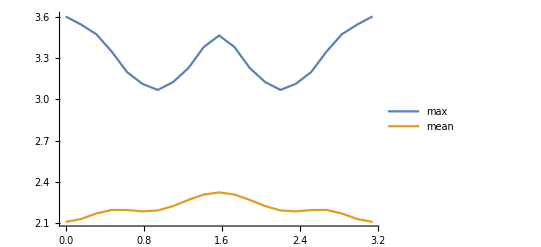

```mathematica
ListLinePlot[{Ecfibomax,Ecfibomean},PlotLegends->{"max","mean"}]
```

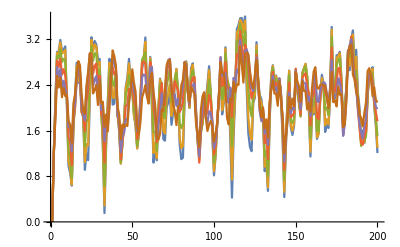

```mathematica
ListLinePlot[Table[Ecfibon[[n]],{n,1,6}]]
```

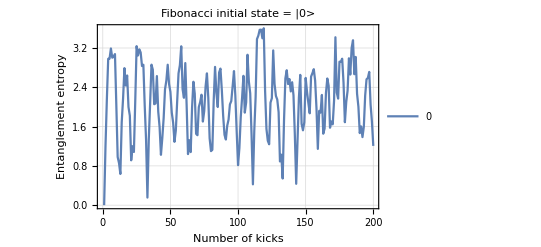

```mathematica
ListLinePlot[Ecfibon[[1]],PlotTheme->"Detailed",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of kicks],None}},LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]},PlotLabel->"Fibonacci initial state = |0>",PlotLegends->{"0 ","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"}, PlotRange->All]
```

## dt = pi/8

#### data

```mathematica
fibo={-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,6.406853007629834296*10^-16,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,2.398404964790533889*10^+00,2.398404964790533445*10^+00,2.398404964790533889*10^+00,2.769031713829398278*10^+00,2.769031713829399166*10^+00,2.769031713829397834*10^+00,2.769031713829399166*10^+00,2.769031713829397390*10^+00,2.714859631909447124*10^+00,2.714859631909447568*10^+00,2.714859631909446680*10^+00,2.714859631909446236*10^+00,2.714859631909447568*10^+00,1.435539529221185884*10^+00,1.435539529221185884*10^+00,1.435539529221185884*10^+00,2.233308640386461263*10^+00,2.233308640386460375*10^+00,2.233308640386461263*10^+00,2.233308640386459931*10^+00,2.233308640386460375*10^+00,7.718119272934458319*10^-01,7.718119272934457209*10^-01,7.718119272934460540*10^-01,1.933919985966690236*10^+00,1.933919985966690014*10^+00,1.933919985966690458*10^+00,1.933919985966690014*10^+00,1.933919985966690458*10^+00,2.902430850435076426*10^+00,2.902430850435076426*10^+00,2.902430850435075982*10^+00,2.902430850435076870*10^+00,2.902430850435075982*10^+00,2.178579989840965681*10^+00,2.178579989840966125*10^+00,2.178579989840965236*10^+00,2.433453312579540562*10^+00,2.433453312579540118*10^+00,2.433453312579541006*10^+00,2.433453312579541006*10^+00,2.433453312579540562*10^+00,1.400990072477376280*10^+00,1.400990072477376502*10^+00,1.400990072477376946*10^+00,1.400990072477376502*10^+00,1.400990072477376724*10^+00,2.679406902378256294*10^+00,2.679406902378256738*10^+00,2.679406902378256738*10^+00,1.722609701733391230*10^+00,1.722609701733390786*10^+00,1.722609701733390786*10^+00,1.722609701733390342*10^+00,1.722609701733390564*10^+00,1.415230676244292329*10^+00,1.415230676244292329*10^+00,1.415230676244292773*10^+00,2.673177896994408442*10^+00,2.673177896994409330*10^+00,2.673177896994408886*10^+00,2.673177896994409330*10^+00,2.673177896994408886*10^+00,1.387353866375292899*10^+00,1.387353866375293121*10^+00,1.387353866375292233*10^+00,1.387353866375292899*10^+00,1.387353866375292899*10^+00,2.575570761327297120*10^+00,2.575570761327297120*10^+00,2.575570761327297120*10^+00,2.218833447415878624*10^+00,2.218833447415879068*10^+00,2.218833447415878624*10^+00,2.218833447415878624*10^+00,2.218833447415878624*10^+00,2.702570864545698281*10^+00,2.702570864545697837*10^+00,2.702570864545697837*10^+00,2.092037360349454200*10^+00,2.092037360349454644*10^+00,2.092037360349453756*10^+00,2.092037360349454644*10^+00,2.092037360349453756*10^+00,4.968739972006004924*10^-01,4.968739972006006589*10^-01,4.968739972006013805*10^-01,4.968739972006012695*10^-01,4.968739972006017691*10^-01,2.198464746884070564*10^+00,2.198464746884069676*10^+00,2.198464746884069676*10^+00,1.826770023126996545*10^+00,1.826770023126996323*10^+00,1.826770023126996545*10^+00,1.826770023126996545*10^+00,1.826770023126995879*10^+00,2.925662522169295343*10^+00,2.925662522169294011*10^+00,2.925662522169294011*10^+00,2.925662522169295343*10^+00,2.925662522169294011*10^+00,2.605726898388110779*10^+00,2.605726898388110335*10^+00,2.605726898388109891*10^+00,2.007194037888695881*10^+00,2.007194037888695881*10^+00,2.007194037888694993*10^+00,2.007194037888695437*10^+00,2.007194037888696325*10^+00,1.999254061534540217*10^+00,1.999254061534540217*10^+00,1.999254061534540217*10^+00,1.844735960542176756*10^-01,1.844735960542176201*10^-01,1.844735960542183140*10^-01,1.844735960542183140*10^-01,1.844735960542190356*10^-01,1.999421107032024025*10^+00,1.999421107032024247*10^+00,1.999421107032024025*10^+00,1.999421107032024025*10^+00,1.999421107032024025*10^+00,2.729826122051325132*10^+00,2.729826122051325132*10^+00,2.729826122051325576*10^+00,2.808173394368998821*10^+00,2.808173394369000597*10^+00,2.808173394368999709*10^+00,2.808173394369001041*10^+00,2.808173394368998821*10^+00,2.483938552184022264*10^+00,2.483938552184024040*10^+00,2.483938552184022708*10^+00,2.483938552184022264*10^+00,2.483938552184022708*10^+00,1.068074537881012365*10^+00,1.068074537881012365*10^+00,1.068074537881012809*10^+00,2.263681771907624984*10^+00,2.263681771907624540*10^+00,2.263681771907624096*10^+00,2.263681771907623208*10^+00,2.263681771907623208*10^+00,1.186696856282440482*10^+00,1.186696856282441370*10^+00,1.186696856282440704*10^+00,1.866997587585890184*10^+00,1.866997587585890628*10^+00,1.866997587585890406*10^+00,1.866997587585890406*10^+00,1.866997587585890406*10^+00,3.002516179531825813*10^+00,3.002516179531826257*10^+00,3.002516179531825813*10^+00,3.002516179531826701*10^+00,3.002516179531826257*10^+00,2.030430245852811399*10^+00,2.030430245852811399*10^+00,2.030430245852811399*10^+00,2.396587026803320253*10^+00,2.396587026803318476*10^+00,2.396587026803318921*10^+00,2.396587026803319809*10^+00,2.396587026803318032*10^+00,1.420291003422199827*10^+00,1.420291003422200049*10^+00,1.420291003422200271*10^+00,2.627186014352999699*10^+00,2.627186014353000587*10^+00,2.627186014352999699*10^+00,2.627186014352999255*10^+00,2.627186014352999699*10^+00,2.017632271969160396*10^+00,2.017632271969159952*10^+00,2.017632271969159952*10^+00,2.017632271969159952*10^+00,2.017632271969159952*10^+00,1.244404953586747409*10^+00,1.244404953586747409*10^+00,1.244404953586747409*10^+00,2.601229457673321921*10^+00,2.601229457673323253*10^+00,2.601229457673321033*10^+00,2.601229457673323253*10^+00,2.601229457673322365*10^+00,1.403902395746287501*10^+00,1.403902395746287279*10^+00,1.403902395746287723*10^+00,1.403902395746287723*10^+00,1.403902395746287279*10^+00,2.754631299512867670*10^+00,2.722912528242654327*10^-14,2.722912528242654327*10^-14,2.786981058318951437*10^-14,1.964767092222882150*10^+00,1.964767092222692524*10^+00,1.964767092222881706*10^+00,1.964767092222692524*10^+00,1.964767092222881484*10^+00,2.355557808075303239*10^+00,2.355557808074924875*10^+00,2.355557808075301907*10^+00,2.744238183133892672*10^+00,2.744238183134097397*10^+00,2.744238183133894005*10^+00,2.744238183134096509*10^+00,2.744238183133893116*10^+00,2.811340969164804360*10^+00,2.811340969164804804*10^+00,2.811340969164803028*10^+00,2.811340969164803916*10^+00,2.811340969164803028*10^+00,1.667726355646765635*10^+00,1.667726355646515168*10^+00,1.667726355646765635*10^+00,2.398681502270941124*10^+00,2.398681502271172494*10^+00,2.398681502270941124*10^+00,2.398681502271172050*10^+00,2.398681502270941124*10^+00,1.071180964015251202*10^+00,1.071180964015251202*10^+00,1.071180964015251869*10^+00,2.172068796354836628*10^+00,2.172068796354837517*10^+00,2.172068796354835740*10^+00,2.172068796354837072*10^+00,2.172068796354837072*10^+00,2.929705051907828484*10^+00,2.929705051907829372*10^+00,2.929705051907827595*10^+00,2.929705051907827595*10^+00,2.929705051907828484*10^+00,2.191760201592816149*10^+00,2.191760201592815704*10^+00,2.191760201592816149*10^+00,2.414372968161971666*10^+00,2.414372968161972111*10^+00,2.414372968161971666*10^+00,2.414372968161972111*10^+00,2.414372968161972111*10^+00,1.302914787423255838*10^+00,1.302914787423208764*10^+00,1.302914787423256282*10^+00,1.302914787423207876*10^+00,1.302914787423256504*10^+00,2.571450518127325502*10^+00,2.571450518127326390*10^+00,2.571450518127326390*10^+00,1.782829949235795963*10^+00,1.782829949235796407*10^+00,1.782829949235797296*10^+00,1.782829949235796185*10^+00,1.782829949235796407*10^+00,1.502596748356646028*10^+00,1.502596748356646250*10^+00,1.502596748356645584*10^+00,2.728027574034667335*10^+00,2.728027574034666447*10^+00,2.728027574034666447*10^+00,2.728027574034666891*10^+00,2.728027574034666447*10^+00,1.646281467842355850*10^+00,1.646281467842355406*10^+00,1.646281467842355406*10^+00,1.646281467842355406*10^+00,1.646281467842356294*10^+00,2.670629339484576370*10^+00,2.670629339485917075*10^+00,2.670629339484575926*10^+00,2.344023947517631878*10^+00,2.344023947517633211*10^+00,2.344023947517632323*10^+00,2.344023947517632767*10^+00,2.344023947517632323*10^+00,2.740456726521928843*10^+00,2.740456726521929731*10^+00,2.740456726521928399*10^+00,2.192067905375465031*10^+00,2.192067905375463699*10^+00,2.192067905375464587*10^+00,2.192067905375463699*10^+00,2.192067905375464587*10^+00,7.207769157003492966*10^-01,7.207769157003487415*10^-01,7.207769157003498517*10^-01,7.207769157003497407*10^-01,7.207769157003504068*10^-01,2.249471107484209753*10^+00,2.249471107484209753*10^+00,2.249471107484208865*10^+00,1.860487923632876850*10^+00,1.860487923633687313*10^+00,1.860487923632877294*10^+00,1.860487923633687313*10^+00,1.860487923632876628*10^+00,2.959122598268967508*10^+00,2.959122598268739690*10^+00,2.959122598268965731*10^+00,2.959122598268739246*10^+00,2.959122598268965731*10^+00,2.628023141174898214*10^+00,2.628023141174896438*10^+00,2.628023141174897326*10^+00,2.060785606042959905*10^+00,2.060785606042959017*10^+00,2.060785606042959017*10^+00,2.060785606042958573*10^+00,2.060785606042958573*10^+00,2.192284566264780743*10^+00,2.192284566264780299*10^+00,2.192284566264779855*10^+00,5.196597729301313251*10^-01,5.196597729300477253*10^-01,5.196597729301321023*10^-01,5.196597729300481694*10^-01,5.196597729301323243*10^-01,2.160692085628609149*10^+00,2.160692085627446524*10^+00,2.160692085628608705*10^+00,2.160692085627446524*10^+00,2.160692085628608261*10^+00,2.822720736582424728*10^+00,2.822720736582423839*10^+00,2.822720736582423395*10^+00,2.834126877292666435*10^+00,2.834126877292667768*10^+00,2.834126877292666435*10^+00,2.834126877292667324*10^+00,2.834126877292665991*10^+00,2.494066153873479852*10^+00,2.494066153873478964*10^+00,2.494066153873479408*10^+00,2.494066153873478964*10^+00,2.494066153873478520*10^+00,1.159182865641100957*10^+00,1.159182865641100735*10^+00,1.159182865641101401*10^+00,2.233597711453046308*10^+00,2.233597711453046308*10^+00,2.233597711453045864*10^+00,2.233597711453046308*10^+00,2.233597711453045420*10^+00,1.180551753963504868*10^+00,1.180551753963336781*10^+00,1.180551753963504868*10^+00,1.936570360722251749*10^+00,1.936570360722251749*10^+00,1.936570360722251971*10^+00,1.936570360722252415*10^+00,1.936570360722251305*10^+00,3.028389995569127358*10^+00,3.028389995569127802*10^+00,3.028389995569127802*10^+00,3.028389995569126469*10^+00,3.028389995569126469*10^+00,2.118639341881799698*10^+00,2.118639341881800586*10^+00,2.118639341881800142*10^+00,2.524206853420360552*10^+00,2.524206853420361440*10^+00,2.524206853420360552*10^+00,2.524206853420360552*10^+00,2.524206853420360552*10^+00,1.641951059357931619*10^+00,1.641951059357931841*10^+00,1.641951059357932285*10^+00,2.722137629490070321*10^+00,2.722137629489799426*10^+00,2.722137629490069433*10^+00,2.722137629489798982*10^+00,2.722137629490069877*10^+00,2.189745459226472679*10^+00,2.189745459226474011*10^+00,2.189745459226472235*10^+00,2.189745459226473123*10^+00,2.189745459226473123*10^+00,1.502278048606580763*10^+00,1.502278048606580985*10^+00,1.502278048606580763*10^+00,2.618193990451177733*10^+00,2.618193990451178621*10^+00,2.618193990451177733*10^+00,2.618193990451179065*10^+00,2.618193990451177733*10^+00,1.509921946340292864*10^+00,1.509921946340292642*10^+00,1.509921946340293086*10^+00,1.509921946340293086*10^+00,1.509921946340292642*10^+00,2.732247317351032656*10^+00,-9.610279511444755881*10^-16,-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,1.863352578568376661*10^+00,1.863352578568376217*10^+00,1.863352578568376217*10^+00,1.863352578568376217*10^+00,1.863352578568376217*10^+00,2.238062942591865223*10^+00,2.238062942591866111*10^+00,2.238062942591866999*10^+00,2.681853118328296315*10^+00,2.681853118328296315*10^+00,2.681853118328296315*10^+00,2.681853118328294983*10^+00,2.681853118328295427*10^+00,2.991904535099853213*10^+00,2.991904535099854101*10^+00,2.991904535099852325*10^+00,2.991904535099852325*10^+00,2.991904535099852325*10^+00,2.075972682423255833*10^+00,2.075972682423255833*10^+00,2.075972682423256277*10^+00,2.598116832876617543*10^+00,2.598116832876617543*10^+00,2.598116832876617988*10^+00,2.598116832876617988*10^+00,2.598116832876616211*10^+00,1.632724986113659682*10^+00,1.632724986113660126*10^+00,1.632724986113659904*10^+00,2.526215665702669977*10^+00,2.526215665702669089*10^+00,2.526215665702669089*10^+00,2.526215665702668201*10^+00,2.526215665702668645*10^+00,2.997437025838656677*10^+00,2.997437025838656233*10^+00,2.997437025838656677*10^+00,2.997437025838656233*10^+00,2.997437025838656233*10^+00,2.263529622832973764*10^+00,2.263529622832973320*10^+00,2.263529622832972876*10^+00,2.377129360274352177*10^+00,2.377129360274351733*10^+00,2.377129360274350844*10^+00,2.377129360274351733*10^+00,2.377129360274352177*10^+00,1.102944359078666725*10^+00,1.102944359078667169*10^+00,1.102944359078666281*10^+00,1.102944359078666725*10^+00,1.102944359078666503*10^+00,2.295754290086529092*10^+00,2.295754290086529981*10^+00,2.295754290086529092*10^+00,1.878608384020150179*10^+00,1.878608384020149735*10^+00,1.878608384020150845*10^+00,1.878608384020149957*10^+00,1.878608384020150623*10^+00,1.722495489776575850*10^+00,1.722495489776575406*10^+00,1.722495489776575850*10^+00,2.801720694928270028*10^+00,2.801720694928270028*10^+00,2.801720694928270028*10^+00,2.801720694928269584*10^+00,2.801720694928269140*10^+00,2.095855057099365037*10^+00,2.095855057099365926*10^+00,2.095855057099365482*10^+00,2.095855057099365482*10^+00,2.095855057099365037*10^+00,2.839216383326274240*10^+00,2.839216383326275128*10^+00,2.839216383326275128*10^+00,2.602915257911883273*10^+00,2.602915257911883273*10^+00,2.602915257911882385*10^+00,2.602915257911883273*10^+00,2.602915257911883273*10^+00,2.791592860933700404*10^+00,2.791592860933700404*10^+00,2.791592860933700848*10^+00,2.401845200890135423*10^+00,2.401845200890134979*10^+00,2.401845200890134535*10^+00,2.401845200890133647*10^+00,2.401845200890134091*10^+00,1.193418560861594147*10^+00,1.193418560861594813*10^+00,1.193418560861595035*10^+00,1.193418560861594591*10^+00,1.193418560861595701*10^+00,2.355302835096012348*10^+00,2.355302835096012348*10^+00,2.355302835096012348*10^+00,1.933735018467723776*10^+00,1.933735018467723110*10^+00,1.933735018467723110*10^+00,1.933735018467724220*10^+00,1.933735018467723332*10^+00,3.018539575534548991*10^+00,3.018539575534548991*10^+00,3.018539575534548547*10^+00,3.018539575534548547*10^+00,3.018539575534548103*10^+00,2.708246931196874208*10^+00,2.708246931196872431*10^+00,2.708246931196873319*10^+00,2.271494167076595794*10^+00,2.271494167076595794*10^+00,2.271494167076595794*10^+00,2.271494167076595794*10^+00,2.271494167076595350*10^+00,2.491918851082456143*10^+00,2.491918851082457476*10^+00,2.491918851082456143*10^+00,1.143353440859383063*10^+00,1.143353440859383507*10^+00,1.143353440859383729*10^+00,1.143353440859383507*10^+00,1.143353440859383507*10^+00,2.372469258848939777*10^+00,2.372469258848940221*10^+00,2.372469258848939333*10^+00,2.372469258848939333*10^+00,2.372469258848938889*10^+00,2.985069434567173108*10^+00,2.985069434567173552*10^+00,2.985069434567173552*10^+00,2.878410937213492726*10^+00,2.878410937213492282*10^+00,2.878410937213493614*10^+00,2.878410937213492726*10^+00,2.878410937213491394*10^+00,2.499239123706881394*10^+00,2.499239123706880505*10^+00,2.499239123706881394*10^+00,2.499239123706880505*10^+00,2.499239123706880061*10^+00,1.366339029791025172*10^+00,1.366339029791026061*10^+00,1.366339029791026061*10^+00,2.172321614084947949*10^+00,2.172321614084947505*10^+00,2.172321614084947949*10^+00,2.172321614084947505*10^+00,2.172321614084946617*10^+00,1.192008163819078259*10^+00,1.192008163819078259*10^+00,1.192008163819078259*10^+00,2.101257912735444044*10^+00,2.101257912735443156*10^+00,2.101257912735443600*10^+00,2.101257912735443156*10^+00,2.101257912735443156*10^+00,3.065799360106860938*10^+00,3.065799360106860494*10^+00,3.065799360106860494*10^+00,3.065799360106860938*10^+00,3.065799360106861382*10^+00,2.342985419880302622*10^+00,2.342985419880303954*10^+00,2.342985419880303954*10^+00,2.800556539688482172*10^+00,2.800556539688481283*10^+00,2.800556539688481283*10^+00,2.800556539688480839*10^+00,2.800556539688480395*10^+00,2.053649992067334562*10^+00,2.053649992067335006*10^+00,2.053649992067335006*10^+00,2.803965697172772220*10^+00,2.803965697172771776*10^+00,2.803965697172772220*10^+00,2.803965697172771776*10^+00,2.803965697172772220*10^+00,2.474157135905149296*10^+00,2.474157135905148852*10^+00,2.474157135905147964*10^+00,2.474157135905149296*10^+00,2.474157135905149296*10^+00,1.944919024685496822*10^+00,1.944919024685497044*10^+00,1.944919024685497044*10^+00,2.669511967040710587*10^+00,2.669511967040710587*10^+00,2.669511967040710587*10^+00,2.669511967040709699*10^+00,2.669511967040709699*10^+00,1.687243357807544752*10^+00,1.687243357807544752*10^+00,1.687243357807544752*10^+00,1.687243357807544086*10^+00,1.687243357807544530*10^+00,2.668605407854387490*10^+00,9.610279511444749964*10^-16,1.121199276335220928*10^-15,1.761884577098203667*10^-15,1.707978246994109162*10^+00,1.707978246994108940*10^+00,1.707978246994109162*10^+00,1.707978246994108718*10^+00,1.707978246994108940*10^+00,2.053926717850639072*10^+00,2.053926717850639072*10^+00,2.053926717850639072*10^+00,2.603498229152985566*10^+00,2.603498229152986010*10^+00,2.603498229152984678*10^+00,2.603498229152985566*10^+00,2.603498229152985566*10^+00,3.125639763649243896*10^+00,3.125639763649243452*10^+00,3.125639763649243896*10^+00,3.125639763649243452*10^+00,3.125639763649242564*10^+00,2.376050243634325376*10^+00,2.376050243634324932*10^+00,2.376050243634324488*10^+00,2.641579586264517943*10^+00,2.641579586264519275*10^+00,2.641579586264517943*10^+00,2.641579586264518387*10^+00,2.641579586264517943*10^+00,2.134583599413069077*10^+00,2.134583599413069077*10^+00,2.134583599413068633*10^+00,2.816933284158666506*10^+00,2.816933284158666950*10^+00,2.816933284158666062*10^+00,2.816933284158666506*10^+00,2.816933284158666506*10^+00,3.056722091243479156*10^+00,3.056722091243479156*10^+00,3.056722091243479156*10^+00,3.056722091243479156*10^+00,3.056722091243478268*10^+00,2.286056092729756184*10^+00,2.286056092729756628*10^+00,2.286056092729756628*10^+00,2.278572194332088685*10^+00,2.278572194332088685*10^+00,2.278572194332089573*10^+00,2.278572194332088685*10^+00,2.278572194332087797*10^+00,9.904075577051055790*10^-01,9.904075577051056900*10^-01,9.904075577051050239*10^-01,9.904075577051058010*10^-01,9.904075577051049128*10^-01,2.000185922753514589*10^+00,2.000185922753514589*10^+00,2.000185922753513701*10^+00,1.930705438124645568*10^+00,1.930705438124646012*10^+00,1.930705438124645346*10^+00,1.930705438124645124*10^+00,1.930705438124645568*10^+00,1.948233473225392309*10^+00,1.948233473225392087*10^+00,1.948233473225391421*10^+00,2.816897899413818074*10^+00,2.816897899413818074*10^+00,2.816897899413818962*10^+00,2.816897899413817630*10^+00,2.816897899413817630*10^+00,2.414266138995131428*10^+00,2.414266138995131428*10^+00,2.414266138995131428*10^+00,2.414266138995130984*10^+00,2.414266138995130984*10^+00,2.903268109365797933*10^+00,2.903268109365797933*10^+00,2.903268109365797933*10^+00,2.830408313579950708*10^+00,2.830408313579949819*10^+00,2.830408313579950708*10^+00,2.830408313579950708*10^+00,2.830408313579950264*10^+00,2.807115355318250405*10^+00,2.807115355318250405*10^+00,2.807115355318249961*10^+00,2.568995254771914372*10^+00,2.568995254771913928*10^+00,2.568995254771913928*10^+00,2.568995254771914372*10^+00,2.568995254771913483*10^+00,1.625545488810949735*10^+00,1.625545488810949957*10^+00,1.625545488810949735*10^+00,1.625545488810949735*10^+00,1.625545488810949513*10^+00,2.402720294259180545*10^+00,2.402720294259180989*10^+00,2.402720294259179656*10^+00,1.979675624905000486*10^+00,1.979675624905000042*10^+00,1.979675624905000486*10^+00,1.979675624905000486*10^+00,1.979675624905000486*10^+00,3.014064764783142891*10^+00,3.014064764783142891*10^+00,3.014064764783142891*10^+00,3.014064764783142891*10^+00,3.014064764783142003*10^+00,2.800113059379726099*10^+00,2.800113059379725211*10^+00,2.800113059379724767*10^+00,2.510538736403434168*10^+00,2.510538736403433724*10^+00,2.510538736403434168*10^+00,2.510538736403433280*10^+00,2.510538736403433280*10^+00,2.660780916184706690*10^+00,2.660780916184706690*10^+00,2.660780916184706246*10^+00,1.684551608570385550*10^+00,1.684551608570385106*10^+00,1.684551608570385106*10^+00,1.684551608570385106*10^+00,1.684551608570385106*10^+00,2.492209445488406949*10^+00,2.492209445488406061*10^+00,2.492209445488406949*10^+00,2.492209445488407393*10^+00,2.492209445488406949*10^+00,3.051810461487153958*10^+00,3.051810461487153070*10^+00,3.051810461487153958*10^+00,2.822098157607241475*10^+00,2.822098157607242808*10^+00,2.822098157607241475*10^+00,2.822098157607241919*10^+00,2.822098157607241031*10^+00,2.507050842182055206*10^+00,2.507050842182055206*10^+00,2.507050842182054318*10^+00,2.507050842182054762*10^+00,2.507050842182054762*10^+00,1.561996613414470492*10^+00,1.561996613414470270*10^+00,1.561996613414470048*10^+00,1.998646120659264724*10^+00,1.998646120659265613*10^+00,1.998646120659265168*10^+00,1.998646120659265391*10^+00,1.998646120659264724*10^+00,1.211814840467603904*10^+00,1.211814840467604348*10^+00,1.211814840467603904*10^+00,2.224937196341052470*10^+00,2.224937196341052470*10^+00,2.224937196341052026*10^+00,2.224937196341052470*10^+00,2.224937196341052026*10^+00,3.034745161374373890*10^+00,3.034745161374373890*10^+00,3.034745161374373001*10^+00,3.034745161374373890*10^+00,3.034745161374373890*10^+00,2.561470151293002928*10^+00,2.561470151293002928*10^+00,2.561470151293002928*10^+00,3.016840765061754137*10^+00,3.016840765061755469*10^+00,3.016840765061753693*10^+00,3.016840765061752805*10^+00,3.016840765061753693*10^+00,2.391407990413985107*10^+00,2.391407990413985107*10^+00,2.391407990413985996*10^+00,2.781112237115839658*10^+00,2.781112237115839658*10^+00,2.781112237115839658*10^+00,2.781112237115838770*10^+00,2.781112237115839214*10^+00,2.663596141664660077*10^+00,2.663596141664660522*10^+00,2.663596141664660522*10^+00,2.663596141664658745*10^+00,2.663596141664660077*10^+00,2.316750927806408455*10^+00,2.316750927806408455*10^+00,2.316750927806408455*10^+00,2.710145769517223968*10^+00,2.710145769517223080*10^+00,2.710145769517223080*10^+00,2.710145769517223080*10^+00,2.710145769517222636*10^+00,1.831300649119434576*10^+00,1.831300649119435908*10^+00,1.831300649119435242*10^+00,1.831300649119434576*10^+00,1.831300649119434798*10^+00,2.551653906758196477*10^+00,4.805139755722374982*10^-16,9.610279511444749964*10^-16,1.281370601525966465*10^-15,1.516990580024020652*10^+00,1.516990580024020652*10^+00,1.516990580024020430*10^+00,1.516990580024020652*10^+00,1.516990580024020430*10^+00,1.878024604037900946*10^+00,1.878024604037901391*10^+00,1.878024604037901613*10^+00,2.511525742351227830*10^+00,2.511525742351228274*10^+00,2.511525742351228274*10^+00,2.511525742351228274*10^+00,2.511525742351228718*10^+00,3.152157196449887344*10^+00,3.152157196449885568*10^+00,3.152157196449886456*10^+00,3.152157196449886456*10^+00,3.152157196449885568*10^+00,2.507489025168846641*10^+00,2.507489025168847085*10^+00,2.507489025168846641*10^+00,2.529218200248950943*10^+00,2.529218200248951387*10^+00,2.529218200248950055*10^+00,2.529218200248950943*10^+00,2.529218200248950943*10^+00,2.432291071226571955*10^+00,2.432291071226571511*10^+00,2.432291071226571511*10^+00,2.926581176779576410*10^+00,2.926581176779576410*10^+00,2.926581176779575078*10^+00,2.926581176779575522*10^+00,2.926581176779575522*10^+00,3.028941037561032168*10^+00,3.028941037561032168*10^+00,3.028941037561031724*10^+00,3.028941037561031724*10^+00,3.028941037561031724*10^+00,2.200355127966229674*10^+00,2.200355127966229674*10^+00,2.200355127966229229*10^+00,2.079797024447526343*10^+00,2.079797024447525899*10^+00,2.079797024447527232*10^+00,2.079797024447525899*10^+00,2.079797024447526343*10^+00,9.971972080410589356*10^-01,9.971972080410590467*10^-01,9.971972080410591577*10^-01,9.971972080410594907*10^-01,9.971972080410593797*10^-01,1.761423552734429743*10^+00,1.761423552734429077*10^+00,1.761423552734429299*10^+00,1.838223221639128990*10^+00,1.838223221639128990*10^+00,1.838223221639128990*10^+00,1.838223221639129212*10^+00,1.838223221639128324*10^+00,2.081839380131909500*10^+00,2.081839380131910389*10^+00,2.081839380131909500*10^+00,2.755063284016546987*10^+00,2.755063284016547431*10^+00,2.755063284016546987*10^+00,2.755063284016546987*10^+00,2.755063284016546987*10^+00,2.510653708869891254*10^+00,2.510653708869891254*10^+00,2.510653708869890366*10^+00,2.510653708869890366*10^+00,2.510653708869890810*10^+00,2.836396490340837406*10^+00,2.836396490340837406*10^+00,2.836396490340836962*10^+00,2.940666757587713231*10^+00,2.940666757587713676*10^+00,2.940666757587713676*10^+00,2.940666757587713676*10^+00,2.940666757587712787*10^+00,2.716972545937984762*10^+00,2.716972545937984762*10^+00,2.716972545937985206*10^+00,2.588303402223620431*10^+00,2.588303402223620431*10^+00,2.588303402223619543*10^+00,2.588303402223619543*10^+00,2.588303402223619543*10^+00,1.867189846081200644*10^+00,1.867189846081200866*10^+00,1.867189846081200422*10^+00,1.867189846081200200*10^+00,1.867189846081200200*10^+00,2.274348848825328506*10^+00,2.274348848825328506*10^+00,2.274348848825328062*10^+00,1.924792583148889680*10^+00,1.924792583148889680*10^+00,1.924792583148889680*10^+00,1.924792583148889680*10^+00,1.924792583148890124*10^+00,2.872647493513358796*10^+00,2.872647493513358796*10^+00,2.872647493513357908*10^+00,2.872647493513358796*10^+00,2.872647493513357908*10^+00,2.797615230721207880*10^+00,2.797615230721207880*10^+00,2.797615230721207880*10^+00,2.659727878287140523*10^+00,2.659727878287140079*10^+00,2.659727878287139191*10^+00,2.659727878287139191*10^+00,2.659727878287139635*10^+00,2.645111356505934985*10^+00,2.645111356505934985*10^+00,2.645111356505934097*10^+00,1.984588295971583705*10^+00,1.984588295971584149*10^+00,1.984588295971583705*10^+00,1.984588295971583705*10^+00,1.984588295971583705*10^+00,2.510740874110380272*10^+00,2.510740874110380272*10^+00,2.510740874110378940*10^+00,2.510740874110379384*10^+00,2.510740874110379828*10^+00,2.973912724061663848*10^+00,2.973912724061663404*10^+00,2.973912724061661628*10^+00,2.661419732851039832*10^+00,2.661419732851039832*10^+00,2.661419732851038944*10^+00,2.661419732851039832*10^+00,2.661419732851038944*10^+00,2.445225881576103433*10^+00,2.445225881576103877*10^+00,2.445225881576104321*10^+00,2.445225881576103877*10^+00,2.445225881576103433*10^+00,1.660987921615986185*10^+00,1.660987921615985741*10^+00,1.660987921615986629*10^+00,1.722604848302064395*10^+00,1.722604848302064617*10^+00,1.722604848302064617*10^+00,1.722604848302064617*10^+00,1.722604848302064617*10^+00,1.195095979564575028*10^+00,1.195095979564575916*10^+00,1.195095979564574806*10^+00,2.245329673183532382*10^+00,2.245329673183531494*10^+00,2.245329673183531050*10^+00,2.245329673183531050*10^+00,2.245329673183531494*10^+00,2.871121713219003446*10^+00,2.871121713219002558*10^+00,2.871121713219001670*10^+00,2.871121713219002558*10^+00,2.871121713219002558*10^+00,2.670058650035445957*10^+00,2.670058650035445957*10^+00,2.670058650035445513*10^+00,3.072056805450017691*10^+00,3.072056805450017247*10^+00,3.072056805450017691*10^+00,3.072056805450017247*10^+00,3.072056805450017247*10^+00,2.563089043525066835*10^+00,2.563089043525066835*10^+00,2.563089043525065946*10^+00,2.661574668701904400*10^+00,2.661574668701904400*10^+00,2.661574668701904400*10^+00,2.661574668701905289*10^+00,2.661574668701904400*10^+00,2.683118259502162317*10^+00,2.683118259502162761*10^+00,2.683118259502161873*10^+00,2.683118259502161873*10^+00,2.683118259502161429*10^+00,2.514521242672969059*10^+00,2.514521242672969059*10^+00,2.514521242672969059*10^+00,2.710266849133281308*10^+00,2.710266849133280864*10^+00,2.710266849133280420*10^+00,2.710266849133279976*10^+00,2.710266849133280864*10^+00,1.880916607762104453*10^+00,1.880916607762105341*10^+00,1.880916607762104453*10^+00,1.880916607762104231*10^+00,1.880916607762104675*10^+00,2.318194402118019859*10^+00,3.203426503814917641*10^-16,-0.000000000000000000*10^+00,8.008566259537291637*10^-16,1.312115125945429339*10^+00,1.312115125945429339*10^+00,1.312115125945429339*10^+00,1.312115125945429117*10^+00,1.312115125945429783*10^+00,1.677534864975295470*10^+00,1.677534864975296358*10^+00,1.677534864975297246*10^+00,2.369657556955556466*10^+00,2.369657556955555577*10^+00,2.369657556955555577*10^+00,2.369657556955556466*10^+00,2.369657556955556466*10^+00,3.020256060352168426*10^+00,3.020256060352168426*10^+00,3.020256060352167538*10^+00,3.020256060352167538*10^+00,3.020256060352166649*10^+00,2.458271301135005249*10^+00,2.458271301135004805*10^+00,2.458271301135003917*10^+00,2.307731872548242080*10^+00,2.307731872548242524*10^+00,2.307731872548242080*10^+00,2.307731872548241636*10^+00,2.307731872548241636*10^+00,2.497532331910384595*10^+00,2.497532331910383263*10^+00,2.497532331910384151*10^+00,2.839951548896357814*10^+00,2.839951548896359146*10^+00,2.839951548896357814*10^+00,2.839951548896357814*10^+00,2.839951548896356925*10^+00,2.843994508297679413*10^+00,2.843994508297678969*10^+00,2.843994508297678081*10^+00,2.843994508297679413*10^+00,2.843994508297677637*10^+00,2.027256535589060160*10^+00,2.027256535589060160*10^+00,2.027256535589060160*10^+00,1.748123928794686588*10^+00,1.748123928794688364*10^+00,1.748123928794687476*10^+00,1.748123928794687032*10^+00,1.748123928794687254*10^+00,9.905528088831498934*10^-01,9.905528088831493383*10^-01,9.905528088831496714*10^-01,9.905528088831494493*10^-01,9.905528088831493383*10^-01,1.568767522915061940*10^+00,1.568767522915061718*10^+00,1.568767522915061274*10^+00,1.662931038207293266*10^+00,1.662931038207292600*10^+00,1.662931038207292600*10^+00,1.662931038207292600*10^+00,1.662931038207292822*10^+00,2.073477662701960877*10^+00,2.073477662701961322*10^+00,2.073477662701960877*10^+00,2.615622346266144760*10^+00,2.615622346266144760*10^+00,2.615622346266145204*10^+00,2.615622346266143872*10^+00,2.615622346266144316*10^+00,2.400588671670145668*10^+00,2.400588671670146113*10^+00,2.400588671670145224*10^+00,2.400588671670144780*10^+00,2.400588671670144780*10^+00,2.652849684634800642*10^+00,2.652849684634800198*10^+00,2.652849684634800642*10^+00,2.869998024899472089*10^+00,2.869998024899472089*10^+00,2.869998024899471645*10^+00,2.869998024899471645*10^+00,2.869998024899470312*10^+00,2.536965506288820116*10^+00,2.536965506288820116*10^+00,2.536965506288819672*10^+00,2.414806813441944477*10^+00,2.414806813441944033*10^+00,2.414806813441943589*10^+00,2.414806813441943589*10^+00,2.414806813441943589*10^+00,1.885533729746636133*10^+00,1.885533729746636578*10^+00,1.885533729746635467*10^+00,1.885533729746635467*10^+00,1.885533729746635689*10^+00,1.968395288285520239*10^+00,1.968395288285520017*10^+00,1.968395288285520461*10^+00,1.765872596966680197*10^+00,1.765872596966679531*10^+00,1.765872596966678865*10^+00,1.765872596966679309*10^+00,1.765872596966679087*10^+00,2.584761283874786653*10^+00,2.584761283874785320*10^+00,2.584761283874785320*10^+00,2.584761283874785320*10^+00,2.584761283874785320*10^+00,2.625831182486529691*10^+00,2.625831182486530135*10^+00,2.625831182486528803*10^+00,2.638941541843781824*10^+00,2.638941541843783156*10^+00,2.638941541843783156*10^+00,2.638941541843782268*10^+00,2.638941541843783156*10^+00,2.486058312497058331*10^+00,2.486058312497057887*10^+00,2.486058312497057443*10^+00,2.028142756565842753*10^+00,2.028142756565842308*10^+00,2.028142756565842753*10^+00,2.028142756565842308*10^+00,2.028142756565842308*10^+00,2.425108612280215237*10^+00,2.425108612280215237*10^+00,2.425108612280215681*10^+00,2.425108612280215237*10^+00,2.425108612280214793*10^+00,2.802276707425690461*10^+00,2.802276707425691349*10^+00,2.802276707425690017*10^+00,2.437970136744053384*10^+00,2.437970136744053384*10^+00,2.437970136744052052*10^+00,2.437970136744051608*10^+00,2.437970136744052052*10^+00,2.260422992398354758*10^+00,2.260422992398354758*10^+00,2.260422992398354314*10^+00,2.260422992398354314*10^+00,2.260422992398353870*10^+00,1.622025424582789643*10^+00,1.622025424582790087*10^+00,1.622025424582789643*10^+00,1.365541881427838611*10^+00,1.365541881427839277*10^+00,1.365541881427839055*10^+00,1.365541881427838833*10^+00,1.365541881427839055*10^+00,1.114524576677264678*10^+00,1.114524576677264900*10^+00,1.114524576677265122*10^+00,2.117097923935545634*10^+00,2.117097923935545634*10^+00,2.117097923935545634*10^+00,2.117097923935546078*10^+00,2.117097923935544745*10^+00,2.580491886639255217*10^+00,2.580491886639254773*10^+00,2.580491886639254773*10^+00,2.580491886639255217*10^+00,2.580491886639254329*10^+00,2.625006695946604740*10^+00,2.625006695946605184*10^+00,2.625006695946604296*10^+00,2.940583063736744052*10^+00,2.940583063736742275*10^+00,2.940583063736743163*10^+00,2.940583063736742275*10^+00,2.940583063736742275*10^+00,2.521448685671513701*10^+00,2.521448685671514589*10^+00,2.521448685671513701*10^+00,2.486800489071548270*10^+00,2.486800489071548270*10^+00,2.486800489071548270*10^+00,2.486800489071548270*10^+00,2.486800489071547382*10^+00,2.545823691826837987*10^+00,2.545823691826837099*10^+00,2.545823691826836210*10^+00,2.545823691826836210*10^+00,2.545823691826837099*10^+00,2.501975293207100215*10^+00,2.501975293207100215*10^+00,2.501975293207099327*10^+00,2.588309607287060832*10^+00,2.588309607287061276*10^+00,2.588309607287059499*10^+00,2.588309607287060832*10^+00,2.588309607287059944*10^+00,1.856005593280616983*10^+00,1.856005593280616539*10^+00,1.856005593280617427*10^+00,1.856005593280617205*10^+00,1.856005593280616317*10^+00,1.984996057786824419*10^+00,-9.610279511444755881*10^-16,-9.610279511444755881*10^-16,-0.000000000000000000*10^+00,1.115222582521595562*10^+00,1.115222582521595562*10^+00,1.115222582521595562*10^+00,1.115222582521595784*10^+00,1.115222582521596006*10^+00,1.489891986783104194*10^+00,1.489891986783104416*10^+00,1.489891986783104194*10^+00,2.167108989211500081*10^+00,2.167108989211500081*10^+00,2.167108989211500969*10^+00,2.167108989211500525*10^+00,2.167108989211500525*10^+00,2.744713410251425678*10^+00,2.744713410251427010*10^+00,2.744713410251427010*10^+00,2.744713410251426566*10^+00,2.744713410251426122*10^+00,2.256659447525551254*10^+00,2.256659447525551254*10^+00,2.256659447525550810*10^+00,2.080429277345415162*10^+00,2.080429277345414718*10^+00,2.080429277345414718*10^+00,2.080429277345414718*10^+00,2.080429277345414274*10^+00,2.358192298704767431*10^+00,2.358192298704766987*10^+00,2.358192298704767875*10^+00,2.590213607472490409*10^+00,2.590213607472489077*10^+00,2.590213607472489965*10^+00,2.590213607472489965*10^+00,2.590213607472489521*10^+00,2.495707233303614547*10^+00,2.495707233303614547*10^+00,2.495707233303614103*10^+00,2.495707233303613659*10^+00,2.495707233303613215*10^+00,1.780463975529721576*10^+00,1.780463975529722020*10^+00,1.780463975529722020*10^+00,1.335179889528439023*10^+00,1.335179889528438801*10^+00,1.335179889528438801*10^+00,1.335179889528438579*10^+00,1.335179889528438801*10^+00,9.013908910937102892*10^-01,9.013908910937108443*10^-01,9.013908910937108443*10^-01,9.013908910937113994*10^-01,9.013908910937110663*10^-01,1.378392807897332428*10^+00,1.378392807897332428*10^+00,1.378392807897332206*10^+00,1.446323300615058871*10^+00,1.446323300615058649*10^+00,1.446323300615058649*10^+00,1.446323300615059315*10^+00,1.446323300615058427*10^+00,1.941005180594027379*10^+00,1.941005180594027602*10^+00,1.941005180594027379*10^+00,2.414294484513165528*10^+00,2.414294484513164640*10^+00,2.414294484513164640*10^+00,2.414294484513165528*10^+00,2.414294484513165084*10^+00,2.184349417323252940*10^+00,2.184349417323252496*10^+00,2.184349417323252496*10^+00,2.184349417323252052*10^+00,2.184349417323252052*10^+00,2.384070749222623853*10^+00,2.384070749222624297*10^+00,2.384070749222622965*10^+00,2.637880883818774613*10^+00,2.637880883818775057*10^+00,2.637880883818774169*10^+00,2.637880883818774169*10^+00,2.637880883818773725*10^+00,2.289396623786283946*10^+00,2.289396623786283946*10^+00,2.289396623786283502*10^+00,2.085623327360666135*10^+00,2.085623327360666579*10^+00,2.085623327360666579*10^+00,2.085623327360665691*10^+00,2.085623327360665691*10^+00,1.719744381628937946*10^+00,1.719744381628938168*10^+00,1.719744381628937724*10^+00,1.719744381628938168*10^+00,1.719744381628937502*10^+00,1.552036966177977817*10^+00,1.552036966177977151*10^+00,1.552036966177977817*10^+00,1.515570493426447118*10^+00,1.515570493426445786*10^+00,1.515570493426446230*10^+00,1.515570493426446674*10^+00,1.515570493426446674*10^+00,2.199238490342880770*10^+00,2.199238490342881214*10^+00,2.199238490342881214*10^+00,2.199238490342880326*10^+00,2.199238490342880770*10^+00,2.324319052856426815*10^+00,2.324319052856425483*10^+00,2.324319052856425483*10^+00,2.449826159730015718*10^+00,2.449826159730016606*10^+00,2.449826159730016162*10^+00,2.449826159730015718*10^+00,2.449826159730015718*10^+00,2.238582626786241647*10^+00,2.238582626786240759*10^+00,2.238582626786241647*10^+00,1.889895461392106846*10^+00,1.889895461392107068*10^+00,1.889895461392106624*10^+00,1.889895461392107290*10^+00,1.889895461392106402*10^+00,2.239101090643890846*10^+00,2.239101090643890402*10^+00,2.239101090643890402*10^+00,2.239101090643890846*10^+00,2.239101090643890402*10^+00,2.544902885964357431*10^+00,2.544902885964357431*10^+00,2.544902885964356543*10^+00,2.153660073343918846*10^+00,2.153660073343917070*10^+00,2.153660073343917070*10^+00,2.153660073343918402*10^+00,2.153660073343917958*10^+00,1.964452062972559476*10^+00,1.964452062972559698*10^+00,1.964452062972559254*10^+00,1.964452062972559698*10^+00,1.964452062972558810*10^+00,1.476288440129198909*10^+00,1.476288440129199131*10^+00,1.476288440129198687*10^+00,1.017604865771126521*10^+00,1.017604865771126077*10^+00,1.017604865771125633*10^+00,1.017604865771126077*10^+00,1.017604865771126077*10^+00,9.723331456521460137*10^-01,9.723331456521461247*10^-01,9.723331456521462357*10^-01,1.886919389869222474*10^+00,1.886919389869223140*10^+00,1.886919389869222918*10^+00,1.886919389869223140*10^+00,1.886919389869222030*10^+00,2.246473777563489982*10^+00,2.246473777563489094*10^+00,2.246473777563489094*10^+00,2.246473777563489538*10^+00,2.246473777563489094*10^+00,2.422889365054444077*10^+00,2.422889365054445410*10^+00,2.422889365054444522*10^+00,2.654184272973961534*10^+00,2.654184272973961090*10^+00,2.654184272973960201*10^+00,2.654184272973960201*10^+00,2.654184272973960201*10^+00,2.305296539173098402*10^+00,2.305296539173098846*10^+00,2.305296539173098846*10^+00,2.252193833418414393*10^+00,2.252193833418414837*10^+00,2.252193833418414837*10^+00,2.252193833418414393*10^+00,2.252193833418414393*10^+00,2.296652141323741070*10^+00,2.296652141323740182*10^+00,2.296652141323740182*10^+00,2.296652141323739738*10^+00,2.296652141323740182*10^+00,2.301378821249422835*10^+00,2.301378821249421947*10^+00,2.301378821249421947*10^+00,2.304915368244870422*10^+00,2.304915368244871310*10^+00,2.304915368244871310*10^+00,2.304915368244871310*10^+00,2.304915368244870422*10^+00,1.753531275348791496*10^+00,1.753531275348791274*10^+00,1.753531275348791052*10^+00,1.753531275348791718*10^+00,1.753531275348791274*10^+00,1.621554952667821903*10^+00,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,3.203426503814917641*10^-16,9.452589891428946345*10^-01,9.452589891428947455*10^-01,9.452589891428946345*10^-01,9.452589891428948565*10^-01,9.452589891428949676*10^-01,1.305103911544365225*10^+00,1.305103911544365225*10^+00,1.305103911544364781*10^+00,1.887993229853868637*10^+00,1.887993229853869082*10^+00,1.887993229853868637*10^+00,1.887993229853869304*10^+00,1.887993229853867971*10^+00,2.375019397043160119*10^+00,2.375019397043161007*10^+00,2.375019397043161895*10^+00,2.375019397043160563*10^+00,2.375019397043161007*10^+00,1.989251388745262972*10^+00,1.989251388745262972*10^+00,1.989251388745262528*10^+00,1.836783510896069282*10^+00,1.836783510896069505*10^+00,1.836783510896069060*10^+00,1.836783510896069060*10^+00,1.836783510896069060*10^+00,2.099518640474415054*10^+00,2.099518640474414610*10^+00,2.099518640474414166*10^+00,2.243849222481477668*10^+00,2.243849222481477668*10^+00,2.243849222481477224*10^+00,2.243849222481477224*10^+00,2.243849222481476335*10^+00,2.038180612107326706*10^+00,2.038180612107327150*10^+00,2.038180612107327594*10^+00,2.038180612107327150*10^+00,2.038180612107326706*10^+00,1.487002278570181080*10^+00,1.487002278570181080*10^+00,1.487002278570181524*10^+00,9.556949016304246980*10^-01,9.556949016304245870*10^-01,9.556949016304242539*10^-01,9.556949016304251421*10^-01,9.556949016304248090*10^-01,7.469822843347955210*10^-01,7.469822843347951880*10^-01,7.469822843347961872*10^-01,7.469822843347957431*10^-01,7.469822843347964092*10^-01,1.199889247117427171*10^+00,1.199889247117426949*10^+00,1.199889247117427615*10^+00,1.225544084283376245*10^+00,1.225544084283376245*10^+00,1.225544084283376467*10^+00,1.225544084283377133*10^+00,1.225544084283376245*10^+00,1.696588908928805317*10^+00,1.696588908928805539*10^+00,1.696588908928805539*10^+00,2.137276846627758964*10^+00,2.137276846627759852*10^+00,2.137276846627758964*10^+00,2.137276846627758964*10^+00,2.137276846627759408*10^+00,1.919118499017000712*10^+00,1.919118499017000268*10^+00,1.919118499016999824*10^+00,1.919118499017000046*10^+00,1.919118499016999380*10^+00,2.064101620065275533*10^+00,2.064101620065276421*10^+00,2.064101620065275533*10^+00,2.285651538219102719*10^+00,2.285651538219103163*10^+00,2.285651538219102274*10^+00,2.285651538219102274*10^+00,2.285651538219102274*10^+00,1.985873213094549783*10^+00,1.985873213094550671*10^+00,1.985873213094550671*10^+00,1.682899115783359489*10^+00,1.682899115783360156*10^+00,1.682899115783359933*10^+00,1.682899115783360156*10^+00,1.682899115783359267*10^+00,1.452864940066514121*10^+00,1.452864940066514565*10^+00,1.452864940066513011*10^+00,1.452864940066513677*10^+00,1.452864940066513455*10^+00,1.180820192543701408*10^+00,1.180820192543700964*10^+00,1.180820192543702074*10^+00,1.225799877421630768*10^+00,1.225799877421631434*10^+00,1.225799877421632100*10^+00,1.225799877421631878*10^+00,1.225799877421631656*10^+00,1.811068792991074705*10^+00,1.811068792991074927*10^+00,1.811068792991075593*10^+00,1.811068792991075149*10^+00,1.811068792991074483*10^+00,1.955697871867704274*10^+00,1.955697871867704274*10^+00,1.955697871867703386*10^+00,2.132044501587886831*10^+00,2.132044501587887275*10^+00,2.132044501587887275*10^+00,2.132044501587886831*10^+00,2.132044501587887719*10^+00,1.950505117267572031*10^+00,1.950505117267572475*10^+00,1.950505117267572475*10^+00,1.627551615868128021*10^+00,1.627551615868128465*10^+00,1.627551615868128021*10^+00,1.627551615868128909*10^+00,1.627551615868128243*10^+00,1.972080466568871593*10^+00,1.972080466568871593*10^+00,1.972080466568872037*10^+00,1.972080466568871593*10^+00,1.972080466568871593*10^+00,2.219535296496975452*10^+00,2.219535296496975896*10^+00,2.219535296496975896*10^+00,1.847296570518293324*10^+00,1.847296570518292436*10^+00,1.847296570518292436*10^+00,1.847296570518291770*10^+00,1.847296570518291992*10^+00,1.593198574868512019*10^+00,1.593198574868512907*10^+00,1.593198574868512907*10^+00,1.593198574868513351*10^+00,1.593198574868513129*10^+00,1.283739814767561604*10^+00,1.283739814767561382*10^+00,1.283739814767560938*10^+00,7.544892394799984636*10^-01,7.544892394799993518*10^-01,7.544892394799989077*10^-01,7.544892394799987967*10^-01,7.544892394799991298*10^-01,8.116023701244410304*10^-01,8.116023701244403643*10^-01,8.116023701244405864*10^-01,1.617764770187563927*10^+00,1.617764770187563705*10^+00,1.617764770187563705*10^+00,1.617764770187563705*10^+00,1.617764770187563705*10^+00,1.895132071000499074*10^+00,1.895132071000499518*10^+00,1.895132071000499963*10^+00,1.895132071000500185*10^+00,1.895132071000499518*10^+00,2.130984167632904658*10^+00,2.130984167632904658*10^+00,2.130984167632902881*10^+00,2.272599509407384311*10^+00,2.272599509407383866*10^+00,2.272599509407383422*10^+00,2.272599509407382978*10^+00,2.272599509407383422*10^+00,1.988598910864171510*10^+00,1.988598910864171287*10^+00,1.988598910864170177*10^+00,1.986189050759441077*10^+00,1.986189050759440633*10^+00,1.986189050759440855*10^+00,1.986189050759439745*10^+00,1.986189050759440855*10^+00,1.977205093693981786*10^+00,1.977205093693981564*10^+00,1.977205093693980897*10^+00,1.977205093693980897*10^+00,1.977205093693980453*10^+00,1.970990608073273531*10^+00,1.970990608073273087*10^+00,1.970990608073272199*10^+00,1.909692072785146078*10^+00,1.909692072785146078*10^+00,1.909692072785145855*10^+00,1.909692072785146300*10^+00,1.909692072785145855*10^+00,1.563457156337010767*10^+00,1.563457156337009879*10^+00,1.563457156337010545*10^+00,1.563457156337010101*10^+00,1.563457156337010323*10^+00,1.283986535321576028*10^+00,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,3.203426503814917641*10^-16,8.161256706433098751*10^-01,8.161256706433095420*10^-01,8.161256706433102082*10^-01,8.161256706433099861*10^-01,8.161256706433102082*10^-01,1.127046266571824829*10^+00,1.127046266571824829*10^+00,1.127046266571825273*10^+00,1.593408379480795833*10^+00,1.593408379480795611*10^+00,1.593408379480795389*10^+00,1.593408379480795833*10^+00,1.593408379480796278*10^+00,1.968601333343314552*10^+00,1.968601333343314108*10^+00,1.968601333343314330*10^+00,1.968601333343314996*10^+00,1.968601333343314774*10^+00,1.691307072812396894*10^+00,1.691307072812396228*10^+00,1.691307072812395562*10^+00,1.590142284152691765*10^+00,1.590142284152691765*10^+00,1.590142284152691765*10^+00,1.590142284152691543*10^+00,1.590142284152691321*10^+00,1.779701023050480835*10^+00,1.779701023050480169*10^+00,1.779701023050480835*10^+00,1.873633872433395187*10^+00,1.873633872433394743*10^+00,1.873633872433394298*10^+00,1.873633872433394076*10^+00,1.873633872433394743*10^+00,1.612060186265400930*10^+00,1.612060186265400930*10^+00,1.612060186265400930*10^+00,1.612060186265400930*10^+00,1.612060186265400485*10^+00,1.209648235635558677*10^+00,1.209648235635558899*10^+00,1.209648235635558233*10^+00,6.723220802314497924*10^-01,6.723220802314500144*10^-01,6.723220802314507916*10^-01,6.723220802314492373*10^-01,6.723220802314502365*10^-01,5.984310401431537363*10^-01,5.984310401431537363*10^-01,5.984310401431536253*10^-01,5.984310401431545134*10^-01,5.984310401431541804*10^-01,1.039500999322193531*10^+00,1.039500999322193531*10^+00,1.039500999322194641*10^+00,1.011647165851546015*10^+00,1.011647165851546237*10^+00,1.011647165851546459*10^+00,1.011647165851546459*10^+00,1.011647165851546237*10^+00,1.436713108476420864*10^+00,1.436713108476420642*10^+00,1.436713108476420198*10^+00,1.824836466081207531*10^+00,1.824836466081207309*10^+00,1.824836466081207309*10^+00,1.824836466081207753*10^+00,1.824836466081207309*10^+00,1.620975249240112603*10^+00,1.620975249240112825*10^+00,1.620975249240113047*10^+00,1.620975249240112603*10^+00,1.620975249240112159*10^+00,1.728087866899952418*10^+00,1.728087866899952640*10^+00,1.728087866899952196*10^+00,1.913408641030638346*10^+00,1.913408641030638790*10^+00,1.913408641030637680*10^+00,1.913408641030638346*10^+00,1.913408641030637902*10^+00,1.677593458842582486*10^+00,1.677593458842583152*10^+00,1.677593458842582486*10^+00,1.304906246976632378*10^+00,1.304906246976632822*10^+00,1.304906246976632378*10^+00,1.304906246976632378*10^+00,1.304906246976632378*10^+00,1.193007504924212814*10^+00,1.193007504924212592*10^+00,1.193007504924212370*10^+00,1.193007504924212370*10^+00,1.193007504924212370*10^+00,9.192814750523469192*10^-01,9.192814750523474743*10^-01,9.192814750523464751*10^-01,9.811548742872311379*10^-01,9.811548742872316931*10^-01,9.811548742872312490*10^-01,9.811548742872311379*10^-01,9.811548742872324702*10^-01,1.477499898108293186*10^+00,1.477499898108294074*10^+00,1.477499898108293408*10^+00,1.477499898108292742*10^+00,1.477499898108292964*10^+00,1.594195750254746802*10^+00,1.594195750254746358*10^+00,1.594195750254745914*10^+00,1.797862699251869145*10^+00,1.797862699251868701*10^+00,1.797862699251868701*10^+00,1.797862699251869145*10^+00,1.797862699251869589*10^+00,1.661730226414210865*10^+00,1.661730226414210643*10^+00,1.661730226414209755*10^+00,1.370202486743122172*10^+00,1.370202486743121950*10^+00,1.370202486743121728*10^+00,1.370202486743122172*10^+00,1.370202486743122172*10^+00,1.679810251463158322*10^+00,1.679810251463158322*10^+00,1.679810251463158544*10^+00,1.679810251463158322*10^+00,1.679810251463158099*10^+00,1.867514920418158475*10^+00,1.867514920418158031*10^+00,1.867514920418158031*10^+00,1.508921309400104827*10^+00,1.508921309400103938*10^+00,1.508921309400103716*10^+00,1.508921309400104382*10^+00,1.508921309400104604*10^+00,1.217278040215585833*10^+00,1.217278040215584944*10^+00,1.217278040215586721*10^+00,1.217278040215585388*10^+00,1.217278040215586055*10^+00,1.074635405857378156*10^+00,1.074635405857378156*10^+00,1.074635405857377712*10^+00,6.112462253107054932*10^-01,6.112462253107062704*10^-01,6.112462253107059373*10^-01,6.112462253107052712*10^-01,6.112462253107056043*10^-01,6.452005202675367146*10^-01,6.452005202675366036*10^-01,6.452005202675374917*10^-01,1.365498374355948119*10^+00,1.365498374355948341*10^+00,1.365498374355948563*10^+00,1.365498374355948563*10^+00,1.365498374355948119*10^+00,1.569561368345673724*10^+00,1.569561368345674390*10^+00,1.569561368345673946*10^+00,1.569561368345674834*10^+00,1.569561368345673724*10^+00,1.789297570323014286*10^+00,1.789297570323014064*10^+00,1.789297570323014064*10^+00,1.879301192546552146*10^+00,1.879301192546551702*10^+00,1.879301192546551702*10^+00,1.879301192546551924*10^+00,1.879301192546551480*10^+00,1.655602788342069864*10^+00,1.655602788342069198*10^+00,1.655602788342069642*10^+00,1.714487768287958014*10^+00,1.714487768287957126*10^+00,1.714487768287956904*10^+00,1.714487768287956904*10^+00,1.714487768287957348*10^+00,1.665458904881299551*10^+00,1.665458904881299107*10^+00,1.665458904881299995*10^+00,1.665458904881298441*10^+00,1.665458904881299329*10^+00,1.621462161990721906*10^+00,1.621462161990721684*10^+00,1.621462161990721462*10^+00,1.535591031977510790*10^+00,1.535591031977510790*10^+00,1.535591031977510790*10^+00,1.535591031977510346*10^+00,1.535591031977510790*10^+00,1.327263678383454604*10^+00,1.327263678383453716*10^+00,1.327263678383453049*10^+00,1.327263678383453938*10^+00,1.327263678383453049*10^+00,1.018559505974773405*10^+00,-9.610279511444755881*10^-16,-6.406853007629837254*10^-16,-0.000000000000000000*10^+00,7.361508591767794707*10^-01,7.361508591767794707*10^-01,7.361508591767794707*10^-01,7.361508591767795817*10^-01,7.361508591767798038*10^-01,9.911229583405192223*10^-01,9.911229583405194443*10^-01,9.911229583405192223*10^-01,1.373405199417505829*10^+00,1.373405199417505163*10^+00,1.373405199417504940*10^+00,1.373405199417505607*10^+00,1.373405199417504940*10^+00,1.677723812113863122*10^+00,1.677723812113862678*10^+00,1.677723812113863122*10^+00,1.677723812113863122*10^+00,1.677723812113863344*10^+00,1.459928848186959005*10^+00,1.459928848186959227*10^+00,1.459928848186959227*10^+00,1.393902820410545029*10^+00,1.393902820410544141*10^+00,1.393902820410545695*10^+00,1.393902820410544807*10^+00,1.393902820410544585*10^+00,1.538455841375986344*10^+00,1.538455841375985456*10^+00,1.538455841375985678*10^+00,1.588159973802680369*10^+00,1.588159973802680591*10^+00,1.588159973802680369*10^+00,1.588159973802680147*10^+00,1.588159973802680369*10^+00,1.303372030949141891*10^+00,1.303372030949141447*10^+00,1.303372030949141669*10^+00,1.303372030949141225*10^+00,1.303372030949142113*10^+00,1.005304183275636642*10^+00,1.005304183275636642*10^+00,1.005304183275636865*10^+00,5.205028365538745261*10^-01,5.205028365538748591*10^-01,5.205028365538745261*10^-01,5.205028365538751922*10^-01,5.205028365538751922*10^-01,5.047214534247203011*10^-01,5.047214534247204121*10^-01,5.047214534247205231*10^-01,5.047214534247204121*10^-01,5.047214534247209672*10^-01,9.264445578758608857*10^-01,9.264445578758614408*10^-01,9.264445578758611077*10^-01,8.630095705657905292*10^-01,8.630095705657900851*10^-01,8.630095705657895300*10^-01,8.630095705657895300*10^-01,8.630095705657903071*10^-01,1.220205463350326314*10^+00,1.220205463350326758*10^+00,1.220205463350326980*10^+00,1.555896356313038575*10^+00,1.555896356313038797*10^+00,1.555896356313038353*10^+00,1.555896356313038797*10^+00,1.555896356313038797*10^+00,1.390431261189815526*10^+00,1.390431261189815526*10^+00,1.390431261189815082*10^+00,1.390431261189815304*10^+00,1.390431261189815526*10^+00,1.463592673279368483*10^+00,1.463592673279368706*10^+00,1.463592673279368039*10^+00,1.601595812895469040*10^+00,1.601595812895468818*10^+00,1.601595812895468374*10^+00,1.601595812895468596*10^+00,1.601595812895469040*10^+00,1.438295133297871953*10^+00,1.438295133297872175*10^+00,1.438295133297871731*10^+00,1.031967905171309541*10^+00,1.031967905171309541*10^+00,1.031967905171309319*10^+00,1.031967905171309541*10^+00,1.031967905171309763*10^+00,9.851481152497147953*10^-01,9.851481152497143512*10^-01,9.851481152497147953*10^-01,9.851481152497145732*10^-01,9.851481152497143512*10^-01,7.799674293031193528*10^-01,7.799674293031197969*10^-01,7.799674293031193528*10^-01,8.043974148419541503*10^-01,8.043974148419540393*10^-01,8.043974148419537062*10^-01,8.043974148419537062*10^-01,8.043974148419542614*10^-01,1.256915407474304303*10^+00,1.256915407474304969*10^+00,1.256915407474305191*10^+00,1.256915407474304747*10^+00,1.256915407474304747*10^+00,1.334383413659584239*10^+00,1.334383413659584683*10^+00,1.334383413659584239*10^+00,1.534563887107129210*10^+00,1.534563887107128988*10^+00,1.534563887107128544*10^+00,1.534563887107128766*10^+00,1.534563887107128322*10^+00,1.431871201125417326*10^+00,1.431871201125417770*10^+00,1.431871201125417326*10^+00,1.173035882666971119*10^+00,1.173035882666970453*10^+00,1.173035882666970231*10^+00,1.173035882666970675*10^+00,1.173035882666970675*10^+00,1.435933331185732964*10^+00,1.435933331185732964*10^+00,1.435933331185732076*10^+00,1.435933331185732520*10^+00,1.435933331185732964*10^+00,1.589746792325885671*10^+00,1.589746792325884339*10^+00,1.589746792325884783*10^+00,1.258224932270133323*10^+00,1.258224932270133989*10^+00,1.258224932270132879*10^+00,1.258224932270133323*10^+00,1.258224932270133545*10^+00,9.590592736863911005*10^-01,9.590592736863912116*10^-01,9.590592736863907675*10^-01,9.590592736863903234*10^-01,9.590592736863912116*10^-01,8.852682306363867104*10^-01,8.852682306363863773*10^-01,8.852682306363865994*10^-01,5.466765302320715225*10^-01,5.466765302320713005*10^-01,5.466765302320714115*10^-01,5.466765302320714115*10^-01,5.466765302320716335*10^-01,5.369631997015631431*10^-01,5.369631997015628100*10^-01,5.369631997015633651*10^-01,1.180656866581177855*10^+00,1.180656866581177189*10^+00,1.180656866581177411*10^+00,1.180656866581177411*10^+00,1.180656866581177855*10^+00,1.348418491184801615*10^+00,1.348418491184801615*10^+00,1.348418491184801615*10^+00,1.348418491184801393*10^+00,1.348418491184801837*10^+00,1.528315346950756437*10^+00,1.528315346950755771*10^+00,1.528315346950755105*10^+00,1.609838713281927403*10^+00,1.609838713281926958*10^+00,1.609838713281927625*10^+00,1.609838713281927403*10^+00,1.609838713281926736*10^+00,1.410748102259197889*10^+00,1.410748102259197889*10^+00,1.410748102259198111*10^+00,1.479667615667546787*10^+00,1.479667615667547009*10^+00,1.479667615667547231*10^+00,1.479667615667545899*10^+00,1.479667615667547009*10^+00,1.426795269723550641*10^+00,1.426795269723551307*10^+00,1.426795269723550419*10^+00,1.426795269723551307*10^+00,1.426795269723550641*10^+00,1.361616538316314573*10^+00,1.361616538316315239*10^+00,1.361616538316316127*10^+00,1.250292044944129044*10^+00,1.250292044944128600*10^+00,1.250292044944129266*10^+00,1.250292044944128600*10^+00,1.250292044944129266*10^+00,1.115869174763408411*10^+00,1.115869174763408411*10^+00,1.115869174763408633*10^+00,1.115869174763408633*10^+00,1.115869174763407745*10^+00,8.396687246025261731*10^-01,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,3.203426503814917641*10^-16,7.091578053305402918*10^-01,7.091578053305405138*10^-01,7.091578053305402918*10^-01,7.091578053305409579*10^-01,7.091578053305409579*10^-01,9.002058088700785055*10^-01,9.002058088700787275*10^-01,9.002058088700788385*10^-01,1.288050949559905956*10^+00,1.288050949559905511*10^+00,1.288050949559905289*10^+00,1.288050949559905956*10^+00,1.288050949559906400*10^+00,1.570701274299102224*10^+00,1.570701274299102668*10^+00,1.570701274299102668*10^+00,1.570701274299103112*10^+00,1.570701274299102224*10^+00,1.368924732527305066*10^+00,1.368924732527305288*10^+00,1.368924732527305288*10^+00,1.313481135080646567*10^+00,1.313481135080646123*10^+00,1.313481135080646567*10^+00,1.313481135080646123*10^+00,1.313481135080646567*10^+00,1.443726904666718491*10^+00,1.443726904666719157*10^+00,1.443726904666718713*10^+00,1.483467121930844179*10^+00,1.483467121930844179*10^+00,1.483467121930844179*10^+00,1.483467121930844179*10^+00,1.483467121930844401*10^+00,1.187154450836530817*10^+00,1.187154450836531261*10^+00,1.187154450836530595*10^+00,1.187154450836531039*10^+00,1.187154450836531927*10^+00,9.249564015359992286*10^-01,9.249564015359990066*10^-01,9.249564015359985625*10^-01,4.792141562259297216*10^-01,4.792141562259306653*10^-01,4.792141562259299992*10^-01,4.792141562259302212*10^-01,4.792141562259307763*10^-01,4.720323028236749208*10^-01,4.720323028236744767*10^-01,4.720323028236751428*10^-01,4.720323028236751983*10^-01,4.720323028236753093*10^-01,8.886190626512177060*10^-01,8.886190626512175950*10^-01,8.886190626512178170*10^-01,8.099009877809704161*10^-01,8.099009877809699720*10^-01,8.099009877809700830*10^-01,8.099009877809700830*10^-01,8.099009877809701941*10^-01,1.131618039828610645*10^+00,1.131618039828610200*10^+00,1.131618039828610200*10^+00,1.463033336658688510*10^+00,1.463033336658687844*10^+00,1.463033336658687844*10^+00,1.463033336658688066*10^+00,1.463033336658687622*10^+00,1.294202334155784451*10^+00,1.294202334155783785*10^+00,1.294202334155784007*10^+00,1.294202334155784007*10^+00,1.294202334155784451*10^+00,1.364904658628813827*10^+00,1.364904658628813827*10^+00,1.364904658628814271*10^+00,1.495157541942828683*10^+00,1.495157541942828461*10^+00,1.495157541942828461*10^+00,1.495157541942828683*10^+00,1.495157541942828683*10^+00,1.343534070405741687*10^+00,1.343534070405741243*10^+00,1.343534070405742131*10^+00,9.411625836986928784*10^-01,9.411625836986929894*10^-01,9.411625836986929894*10^-01,9.411625836986926563*10^-01,9.411625836986931004*10^-01,9.075862129523635247*10^-01,9.075862129523634136*10^-01,9.075862129523633026*10^-01,9.075862129523633026*10^-01,9.075862129523637467*10^-01,7.379189548852032043*10^-01,7.379189548852023162*10^-01,7.379189548852029823*10^-01,7.412996228935440080*10^-01,7.412996228935440080*10^-01,7.412996228935442300*10^-01,7.412996228935444520*10^-01,7.412996228935447851*10^-01,1.188257463355789856*10^+00,1.188257463355788968*10^+00,1.188257463355789412*10^+00,1.188257463355789412*10^+00,1.188257463355789412*10^+00,1.246442534828710258*10^+00,1.246442534828709592*10^+00,1.246442534828710036*10^+00,1.424448521589286809*10^+00,1.424448521589286365*10^+00,1.424448521589286587*10^+00,1.424448521589285921*10^+00,1.424448521589286587*10^+00,1.345256835177226273*10^+00,1.345256835177226051*10^+00,1.345256835177225385*10^+00,1.085278444888878591*10^+00,1.085278444888878591*10^+00,1.085278444888878147*10^+00,1.085278444888878591*10^+00,1.085278444888877702*10^+00,1.345092386431758102*10^+00,1.345092386431758991*10^+00,1.345092386431758991*10^+00,1.345092386431758991*10^+00,1.345092386431758325*10^+00,1.485953768726573809*10^+00,1.485953768726574253*10^+00,1.485953768726573809*10^+00,1.165129132915256438*10^+00,1.165129132915256438*10^+00,1.165129132915255772*10^+00,1.165129132915256660*10^+00,1.165129132915256216*10^+00,8.701855322384819402*10^-01,8.701855322384819402*10^-01,8.701855322384820512*10^-01,8.701855322384814961*10^-01,8.701855322384818292*10^-01,8.251737781314771869*10^-01,8.251737781314768538*10^-01,8.251737781314775200*10^-01,5.272761325743697824*10^-01,5.272761325743693384*10^-01,5.272761325743700045*10^-01,5.272761325743690053*10^-01,5.272761325743702265*10^-01,4.958341074674582072*10^-01,4.958341074674584847*10^-01,4.958341074674584847*10^-01,1.121508508572812257*10^+00,1.121508508572811147*10^+00,1.121508508572812257*10^+00,1.121508508572812035*10^+00,1.121508508572811813*10^+00,1.272002985137183018*10^+00,1.272002985137183018*10^+00,1.272002985137183240*10^+00,1.272002985137182574*10^+00,1.272002985137183018*10^+00,1.431000326547680945*10^+00,1.431000326547680945*10^+00,1.431000326547680501*10^+00,1.506179777184824875*10^+00,1.506179777184824653*10^+00,1.506179777184824209*10^+00,1.506179777184824209*10^+00,1.506179777184824209*10^+00,1.315540820132348410*10^+00,1.315540820132348854*10^+00,1.315540820132348854*10^+00,1.390413821733344824*10^+00,1.390413821733344824*10^+00,1.390413821733344379*10^+00,1.390413821733344157*10^+00,1.390413821733344824*10^+00,1.326518935082261041*10^+00,1.326518935082260819*10^+00,1.326518935082261708*10^+00,1.326518935082261486*10^+00,1.326518935082260819*10^+00,1.263071799859396327*10^+00,1.263071799859395217*10^+00,1.263071799859395439*10^+00,1.154412103903607045*10^+00,1.154412103903607045*10^+00,1.154412103903607045*10^+00,1.154412103903606823*10^+00,1.154412103903606601*10^+00,1.033696572141855174*10^+00,1.033696572141854730*10^+00,1.033696572141854286*10^+00,1.033696572141854730*10^+00,1.033696572141854508*10^+00,7.849184569512956955*10^-01,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,4.805139755722374982*10^-16,7.361508591767793597*10^-01,7.361508591767796927*10^-01,7.361508591767796927*10^-01,7.361508591767793597*10^-01,7.361508591767800258*10^-01,9.911229583405193333*10^-01,9.911229583405191113*10^-01,9.911229583405196664*10^-01,1.373405199417505163*10^+00,1.373405199417505163*10^+00,1.373405199417505385*10^+00,1.373405199417505607*10^+00,1.373405199417504496*10^+00,1.677723812113863122*10^+00,1.677723812113863566*10^+00,1.677723812113862678*10^+00,1.677723812113864010*10^+00,1.677723812113863122*10^+00,1.459928848186959671*10^+00,1.459928848186959005*10^+00,1.459928848186959449*10^+00,1.393902820410544141*10^+00,1.393902820410544363*10^+00,1.393902820410544585*10^+00,1.393902820410544363*10^+00,1.393902820410545029*10^+00,1.538455841375984789*10^+00,1.538455841375985234*10^+00,1.538455841375985456*10^+00,1.588159973802680591*10^+00,1.588159973802680147*10^+00,1.588159973802680147*10^+00,1.588159973802679703*10^+00,1.588159973802679481*10^+00,1.303372030949140115*10^+00,1.303372030949140781*10^+00,1.303372030949141003*10^+00,1.303372030949141003*10^+00,1.303372030949140559*10^+00,1.005304183275636198*10^+00,1.005304183275636198*10^+00,1.005304183275636865*10^+00,5.205028365538738599*10^-01,5.205028365538745261*10^-01,5.205028365538749702*10^-01,5.205028365538747481*10^-01,5.205028365538747481*10^-01,5.047214534247195239*10^-01,5.047214534247190798*10^-01,5.047214534247199680*10^-01,5.047214534247190798*10^-01,5.047214534247199680*10^-01,9.264445578758602196*10^-01,9.264445578758606636*10^-01,9.264445578758606636*10^-01,8.630095705657886418*10^-01,8.630095705657884197*10^-01,8.630095705657891969*10^-01,8.630095705657885308*10^-01,8.630095705657884197*10^-01,1.220205463350325648*10^+00,1.220205463350325870*10^+00,1.220205463350325870*10^+00,1.555896356313037021*10^+00,1.555896356313037021*10^+00,1.555896356313037021*10^+00,1.555896356313037243*10^+00,1.555896356313037243*10^+00,1.390431261189814638*10^+00,1.390431261189814416*10^+00,1.390431261189815082*10^+00,1.390431261189814638*10^+00,1.390431261189814638*10^+00,1.463592673279367151*10^+00,1.463592673279367817*10^+00,1.463592673279366929*10^+00,1.601595812895467708*10^+00,1.601595812895467486*10^+00,1.601595812895467708*10^+00,1.601595812895467486*10^+00,1.601595812895468152*10^+00,1.438295133297870398*10^+00,1.438295133297870176*10^+00,1.438295133297871065*10^+00,1.031967905171308209*10^+00,1.031967905171307986*10^+00,1.031967905171307986*10^+00,1.031967905171308431*10^+00,1.031967905171308431*10^+00,9.851481152497142402*10^-01,9.851481152497139071*10^-01,9.851481152497142402*10^-01,9.851481152497136851*10^-01,9.851481152497137961*10^-01,7.799674293031191308*10^-01,7.799674293031180206*10^-01,7.799674293031187977*10^-01,8.043974148419522630*10^-01,8.043974148419527070*10^-01,8.043974148419527070*10^-01,8.043974148419529291*10^-01,8.043974148419528181*10^-01,1.256915407474303414*10^+00,1.256915407474302970*10^+00,1.256915407474303192*10^+00,1.256915407474303414*10^+00,1.256915407474303192*10^+00,1.334383413659581130*10^+00,1.334383413659581352*10^+00,1.334383413659581352*10^+00,1.534563887107126101*10^+00,1.534563887107126323*10^+00,1.534563887107126545*10^+00,1.534563887107126545*10^+00,1.534563887107126323*10^+00,1.431871201125415549*10^+00,1.431871201125416215*10^+00,1.431871201125415993*10^+00,1.173035882666969343*10^+00,1.173035882666968455*10^+00,1.173035882666968899*10^+00,1.173035882666969787*10^+00,1.173035882666969121*10^+00,1.435933331185731632*10^+00,1.435933331185731188*10^+00,1.435933331185732076*10^+00,1.435933331185731188*10^+00,1.435933331185731188*10^+00,1.589746792325883007*10^+00,1.589746792325882785*10^+00,1.589746792325883007*10^+00,1.258224932270131102*10^+00,1.258224932270130658*10^+00,1.258224932270131546*10^+00,1.258224932270131546*10^+00,1.258224932270131102*10^+00,9.590592736863882140*10^-01,9.590592736863888801*10^-01,9.590592736863887691*10^-01,9.590592736863886580*10^-01,9.590592736863894352*10^-01,8.852682306363852671*10^-01,8.852682306363851561*10^-01,8.852682306363853781*10^-01,5.466765302320709674*10^-01,5.466765302320706343*10^-01,5.466765302320710784*10^-01,5.466765302320710784*10^-01,5.466765302320709674*10^-01,5.369631997015601454*10^-01,5.369631997015608116*10^-01,5.369631997015607006*10^-01,1.180656866581175857*10^+00,1.180656866581176079*10^+00,1.180656866581176079*10^+00,1.180656866581175857*10^+00,1.180656866581175857*10^+00,1.348418491184797396*10^+00,1.348418491184797174*10^+00,1.348418491184797841*10^+00,1.348418491184797396*10^+00,1.348418491184797396*10^+00,1.528315346950752440*10^+00,1.528315346950751552*10^+00,1.528315346950751774*10^+00,1.609838713281924072*10^+00,1.609838713281924960*10^+00,1.609838713281924960*10^+00,1.609838713281924960*10^+00,1.609838713281924960*10^+00,1.410748102259195225*10^+00,1.410748102259195225*10^+00,1.410748102259195225*10^+00,1.479667615667545899*10^+00,1.479667615667545011*10^+00,1.479667615667545233*10^+00,1.479667615667545233*10^+00,1.479667615667545455*10^+00,1.426795269723547310*10^+00,1.426795269723547976*10^+00,1.426795269723547088*10^+00,1.426795269723547532*10^+00,1.426795269723546866*10^+00,1.361616538316310798*10^+00,1.361616538316310576*10^+00,1.361616538316310576*10^+00,1.250292044944125713*10^+00,1.250292044944125713*10^+00,1.250292044944126157*10^+00,1.250292044944125713*10^+00,1.250292044944126157*10^+00,1.115869174763406413*10^+00,1.115869174763405969*10^+00,1.115869174763406191*10^+00,1.115869174763406191*10^+00,1.115869174763406191*10^+00,8.396687246025236195*10^-01,9.610279511444749964*10^-16,1.281370601525966465*10^-15,1.601713251907457933*10^-15,8.161256706433100971*10^-01,8.161256706433102082*10^-01,8.161256706433106523*10^-01,8.161256706433103192*10^-01,8.161256706433108743*10^-01,1.127046266571825495*10^+00,1.127046266571824606*10^+00,1.127046266571825051*10^+00,1.593408379480795611*10^+00,1.593408379480794945*10^+00,1.593408379480795389*10^+00,1.593408379480795389*10^+00,1.593408379480795389*10^+00,1.968601333343314330*10^+00,1.968601333343314552*10^+00,1.968601333343314330*10^+00,1.968601333343313664*10^+00,1.968601333343314108*10^+00,1.691307072812395784*10^+00,1.691307072812395784*10^+00,1.691307072812395562*10^+00,1.590142284152690655*10^+00,1.590142284152691543*10^+00,1.590142284152691099*10^+00,1.590142284152691099*10^+00,1.590142284152691099*10^+00,1.779701023050479725*10^+00,1.779701023050478170*10^+00,1.779701023050479058*10^+00,1.873633872433392966*10^+00,1.873633872433392744*10^+00,1.873633872433392300*10^+00,1.873633872433392522*10^+00,1.873633872433393410*10^+00,1.612060186265399153*10^+00,1.612060186265399597*10^+00,1.612060186265399153*10^+00,1.612060186265399597*10^+00,1.612060186265399153*10^+00,1.209648235635559343*10^+00,1.209648235635559121*10^+00,1.209648235635559121*10^+00,6.723220802314503475*10^-01,6.723220802314513467*10^-01,6.723220802314511246*10^-01,6.723220802314509026*10^-01,6.723220802314511246*10^-01,5.984310401431536253*10^-01,5.984310401431542914*10^-01,5.984310401431547355*10^-01,5.984310401431542914*10^-01,5.984310401431549575*10^-01,1.039500999322194197*10^+00,1.039500999322193975*10^+00,1.039500999322194419*10^+00,1.011647165851544683*10^+00,1.011647165851544239*10^+00,1.011647165851544461*10^+00,1.011647165851544461*10^+00,1.011647165851545349*10^+00,1.436713108476419087*10^+00,1.436713108476418199*10^+00,1.436713108476418865*10^+00,1.824836466081204422*10^+00,1.824836466081204644*10^+00,1.824836466081203756*10^+00,1.824836466081204200*10^+00,1.824836466081204644*10^+00,1.620975249240111715*10^+00,1.620975249240110827*10^+00,1.620975249240110827*10^+00,1.620975249240111271*10^+00,1.620975249240110827*10^+00,1.728087866899949754*10^+00,1.728087866899950420*10^+00,1.728087866899950642*10^+00,1.913408641030635238*10^+00,1.913408641030634572*10^+00,1.913408641030634572*10^+00,1.913408641030635016*10^+00,1.913408641030633461*10^+00,1.677593458842580265*10^+00,1.677593458842580043*10^+00,1.677593458842580265*10^+00,1.304906246976629269*10^+00,1.304906246976629713*10^+00,1.304906246976629491*10^+00,1.304906246976629713*10^+00,1.304906246976629935*10^+00,1.193007504924211482*10^+00,1.193007504924211037*10^+00,1.193007504924211037*10^+00,1.193007504924211259*10^+00,1.193007504924211259*10^+00,9.192814750523469192*10^-01,9.192814750523462530*10^-01,9.192814750523468081*10^-01,9.811548742872288065*10^-01,9.811548742872304718*10^-01,9.811548742872294726*10^-01,9.811548742872298057*10^-01,9.811548742872296947*10^-01,1.477499898108291410*10^+00,1.477499898108291188*10^+00,1.477499898108290299*10^+00,1.477499898108290299*10^+00,1.477499898108291188*10^+00,1.594195750254741917*10^+00,1.594195750254742139*10^+00,1.594195750254741917*10^+00,1.797862699251865148*10^+00,1.797862699251864704*10^+00,1.797862699251864926*10^+00,1.797862699251865148*10^+00,1.797862699251865148*10^+00,1.661730226414205980*10^+00,1.661730226414205980*10^+00,1.661730226414205980*10^+00,1.370202486743118619*10^+00,1.370202486743118842*10^+00,1.370202486743118619*10^+00,1.370202486743118619*10^+00,1.370202486743118842*10^+00,1.679810251463155435*10^+00,1.679810251463155879*10^+00,1.679810251463155657*10^+00,1.679810251463156101*10^+00,1.679810251463155213*10^+00,1.867514920418154034*10^+00,1.867514920418153146*10^+00,1.867514920418154922*10^+00,1.508921309400099053*10^+00,1.508921309400099720*10^+00,1.508921309400099053*10^+00,1.508921309400100608*10^+00,1.508921309400099275*10^+00,1.217278040215581836*10^+00,1.217278040215582280*10^+00,1.217278040215582724*10^+00,1.217278040215582946*10^+00,1.217278040215583168*10^+00,1.074635405857375270*10^+00,1.074635405857374382*10^+00,1.074635405857375714*10^+00,6.112462253107060484*10^-01,6.112462253107049381*10^-01,6.112462253107067145*10^-01,6.112462253107054932*10^-01,6.112462253107053822*10^-01,6.452005202675323847*10^-01,6.452005202675321627*10^-01,6.452005202675321627*10^-01,1.365498374355944122*10^+00,1.365498374355943900*10^+00,1.365498374355944344*10^+00,1.365498374355944566*10^+00,1.365498374355944344*10^+00,1.569561368345667507*10^+00,1.569561368345667507*10^+00,1.569561368345667063*10^+00,1.569561368345666619*10^+00,1.569561368345667063*10^+00,1.789297570323007625*10^+00,1.789297570323007625*10^+00,1.789297570323007402*10^+00,1.879301192546546151*10^+00,1.879301192546546817*10^+00,1.879301192546546151*10^+00,1.879301192546545929*10^+00,1.879301192546546595*10^+00,1.655602788342064979*10^+00,1.655602788342064535*10^+00,1.655602788342064091*10^+00,1.714487768287953129*10^+00,1.714487768287953351*10^+00,1.714487768287953351*10^+00,1.714487768287953351*10^+00,1.714487768287953351*10^+00,1.665458904881292668*10^+00,1.665458904881293112*10^+00,1.665458904881292446*10^+00,1.665458904881292668*10^+00,1.665458904881292446*10^+00,1.621462161990714357*10^+00,1.621462161990714357*10^+00,1.621462161990714579*10^+00,1.535591031977504795*10^+00,1.535591031977504795*10^+00,1.535591031977504350*10^+00,1.535591031977505017*10^+00,1.535591031977505017*10^+00,1.327263678383449053*10^+00,1.327263678383449053*10^+00,1.327263678383447942*10^+00,1.327263678383448386*10^+00,1.327263678383448386*10^+00,1.018559505974771184*10^+00,4.805139755722374982*10^-16,1.601713251907458574*10^-16,8.008566259537291637*10^-16,9.452589891428951896*10^-01,9.452589891428950786*10^-01,9.452589891428950786*10^-01,9.452589891428948565*10^-01,9.452589891428954116*10^-01,1.305103911544363893*10^+00,1.305103911544364115*10^+00,1.305103911544363893*10^+00,1.887993229853867305*10^+00,1.887993229853866861*10^+00,1.887993229853866861*10^+00,1.887993229853867305*10^+00,1.887993229853867305*10^+00,2.375019397043159231*10^+00,2.375019397043158342*10^+00,2.375019397043158342*10^+00,2.375019397043158342*10^+00,2.375019397043158342*10^+00,1.989251388745262528*10^+00,1.989251388745262084*10^+00,1.989251388745262084*10^+00,1.836783510896068394*10^+00,1.836783510896070171*10^+00,1.836783510896068172*10^+00,1.836783510896068838*10^+00,1.836783510896068172*10^+00,2.099518640474413278*10^+00,2.099518640474412834*10^+00,2.099518640474412834*10^+00,2.243849222481475003*10^+00,2.243849222481474559*10^+00,2.243849222481474559*10^+00,2.243849222481474559*10^+00,2.243849222481475447*10^+00,2.038180612107323153*10^+00,2.038180612107324041*10^+00,2.038180612107323597*10^+00,2.038180612107323597*10^+00,2.038180612107323597*10^+00,1.487002278570180636*10^+00,1.487002278570180858*10^+00,1.487002278570180636*10^+00,9.556949016304252531*10^-01,9.556949016304245870*10^-01,9.556949016304249200*10^-01,9.556949016304253641*10^-01,9.556949016304254751*10^-01,7.469822843347954100*10^-01,7.469822843347957431*10^-01,7.469822843347957431*10^-01,7.469822843347959651*10^-01,7.469822843347956320*10^-01,1.199889247117427615*10^+00,1.199889247117426949*10^+00,1.199889247117426727*10^+00,1.225544084283373136*10^+00,1.225544084283372692*10^+00,1.225544084283373580*10^+00,1.225544084283373358*10^+00,1.225544084283372470*10^+00,1.696588908928803541*10^+00,1.696588908928803541*10^+00,1.696588908928803541*10^+00,2.137276846627755855*10^+00,2.137276846627756299*10^+00,2.137276846627755411*10^+00,2.137276846627755411*10^+00,2.137276846627755855*10^+00,1.919118499016997603*10^+00,1.919118499016998047*10^+00,1.919118499016998047*10^+00,1.919118499016998047*10^+00,1.919118499016997381*10^+00,2.064101620065273313*10^+00,2.064101620065273313*10^+00,2.064101620065273313*10^+00,2.285651538219098722*10^+00,2.285651538219097390*10^+00,2.285651538219099166*10^+00,2.285651538219097390*10^+00,2.285651538219097390*10^+00,1.985873213094547785*10^+00,1.985873213094547785*10^+00,1.985873213094546674*10^+00,1.682899115783356159*10^+00,1.682899115783355937*10^+00,1.682899115783356603*10^+00,1.682899115783357269*10^+00,1.682899115783356159*10^+00,1.452864940066513011*10^+00,1.452864940066512345*10^+00,1.452864940066512789*10^+00,1.452864940066512345*10^+00,1.452864940066512567*10^+00,1.180820192543701852*10^+00,1.180820192543700964*10^+00,1.180820192543701630*10^+00,1.225799877421630768*10^+00,1.225799877421630990*10^+00,1.225799877421631434*10^+00,1.225799877421630768*10^+00,1.225799877421630768*10^+00,1.811068792991074261*10^+00,1.811068792991073373*10^+00,1.811068792991073817*10^+00,1.811068792991073595*10^+00,1.811068792991073817*10^+00,1.955697871867700499*10^+00,1.955697871867699833*10^+00,1.955697871867700277*10^+00,2.132044501587884167*10^+00,2.132044501587883278*10^+00,2.132044501587883278*10^+00,2.132044501587883722*10^+00,2.132044501587883278*10^+00,1.950505117267566924*10^+00,1.950505117267567812*10^+00,1.950505117267566479*10^+00,1.627551615868124468*10^+00,1.627551615868124912*10^+00,1.627551615868124468*10^+00,1.627551615868124912*10^+00,1.627551615868124468*10^+00,1.972080466568869594*10^+00,1.972080466568869372*10^+00,1.972080466568869817*10^+00,1.972080466568870261*10^+00,1.972080466568869817*10^+00,2.219535296496970567*10^+00,2.219535296496970123*10^+00,2.219535296496970123*10^+00,1.847296570518287773*10^+00,1.847296570518286440*10^+00,1.847296570518286885*10^+00,1.847296570518286662*10^+00,1.847296570518286662*10^+00,1.593198574868507578*10^+00,1.593198574868507578*10^+00,1.593198574868508022*10^+00,1.593198574868507578*10^+00,1.593198574868507578*10^+00,1.283739814767558940*10^+00,1.283739814767558496*10^+00,1.283739814767558496*10^+00,7.544892394799987967*10^-01,7.544892394799993518*10^-01,7.544892394799996849*10^-01,7.544892394799994628*10^-01,7.544892394799997959*10^-01,8.116023701244359234*10^-01,8.116023701244355903*10^-01,8.116023701244364785*10^-01,1.617764770187561929*10^+00,1.617764770187561929*10^+00,1.617764770187561485*10^+00,1.617764770187561929*10^+00,1.617764770187561485*10^+00,1.895132071000493079*10^+00,1.895132071000493523*10^+00,1.895132071000493967*10^+00,1.895132071000493745*10^+00,1.895132071000493745*10^+00,2.130984167632897996*10^+00,2.130984167632897996*10^+00,2.130984167632897552*10^+00,2.272599509407378093*10^+00,2.272599509407378537*10^+00,2.272599509407377649*10^+00,2.272599509407378537*10^+00,2.272599509407377649*10^+00,1.988598910864165958*10^+00,1.988598910864165958*10^+00,1.988598910864165514*10^+00,1.986189050759437746*10^+00,1.986189050759437746*10^+00,1.986189050759438413*10^+00,1.986189050759437524*10^+00,1.986189050759437746*10^+00,1.977205093693973126*10^+00,1.977205093693973348*10^+00,1.977205093693973126*10^+00,1.977205093693972904*10^+00,1.977205093693972460*10^+00,1.970990608073265538*10^+00,1.970990608073265982*10^+00,1.970990608073265982*10^+00,1.909692072785138750*10^+00,1.909692072785139194*10^+00,1.909692072785139638*10^+00,1.909692072785139416*10^+00,1.909692072785139194*10^+00,1.563457156337004328*10^+00,1.563457156337003440*10^+00,1.563457156337003218*10^+00,1.563457156337003662*10^+00,1.563457156337004328*10^+00,1.283986535321574696*10^+00,4.805139755722374982*10^-16,9.610279511444749964*10^-16,1.441541926716712396*10^-15,1.115222582521596451*10^+00,1.115222582521596228*10^+00,1.115222582521596451*10^+00,1.115222582521596451*10^+00,1.115222582521596451*10^+00,1.489891986783103084*10^+00,1.489891986783103084*10^+00,1.489891986783103528*10^+00,2.167108989211499193*10^+00,2.167108989211499193*10^+00,2.167108989211499193*10^+00,2.167108989211498749*10^+00,2.167108989211498304*10^+00,2.744713410251423014*10^+00,2.744713410251423902*10^+00,2.744713410251422570*10^+00,2.744713410251423014*10^+00,2.744713410251423014*10^+00,2.256659447525549922*10^+00,2.256659447525549922*10^+00,2.256659447525549922*10^+00,2.080429277345413386*10^+00,2.080429277345413386*10^+00,2.080429277345413830*10^+00,2.080429277345413386*10^+00,2.080429277345413830*10^+00,2.358192298704764767*10^+00,2.358192298704764767*10^+00,2.358192298704763434*10^+00,2.590213607472487300*10^+00,2.590213607472486412*10^+00,2.590213607472486856*10^+00,2.590213607472486412*10^+00,2.590213607472486412*10^+00,2.495707233303611439*10^+00,2.495707233303610550*10^+00,2.495707233303610550*10^+00,2.495707233303612327*10^+00,2.495707233303610550*10^+00,1.780463975529721354*10^+00,1.780463975529721576*10^+00,1.780463975529722020*10^+00,1.335179889528439023*10^+00,1.335179889528439023*10^+00,1.335179889528439467*10^+00,1.335179889528439467*10^+00,1.335179889528439912*10^+00,9.013908910937106223*10^-01,9.013908910937105112*10^-01,9.013908910937099561*10^-01,9.013908910937113994*10^-01,9.013908910937104002*10^-01,1.378392807897332650*10^+00,1.378392807897331984*10^+00,1.378392807897333094*10^+00,1.446323300615056429*10^+00,1.446323300615056429*10^+00,1.446323300615057095*10^+00,1.446323300615055540*10^+00,1.446323300615056207*10^+00,1.941005180594026269*10^+00,1.941005180594025159*10^+00,1.941005180594025159*10^+00,2.414294484513161976*10^+00,2.414294484513161976*10^+00,2.414294484513161088*10^+00,2.414294484513161976*10^+00,2.414294484513161532*10^+00,2.184349417323250719*10^+00,2.184349417323250275*10^+00,2.184349417323250275*10^+00,2.184349417323250275*10^+00,2.184349417323249387*10^+00,2.384070749222621188*10^+00,2.384070749222622077*10^+00,2.384070749222622077*10^+00,2.637880883818771061*10^+00,2.637880883818770172*10^+00,2.637880883818770617*10^+00,2.637880883818770617*10^+00,2.637880883818769728*10^+00,2.289396623786280838*10^+00,2.289396623786281282*10^+00,2.289396623786281282*10^+00,2.085623327360662582*10^+00,2.085623327360662138*10^+00,2.085623327360662582*10^+00,2.085623327360661250*10^+00,2.085623327360661694*10^+00,1.719744381628937058*10^+00,1.719744381628937280*10^+00,1.719744381628937058*10^+00,1.719744381628937058*10^+00,1.719744381628937058*10^+00,1.552036966177980704*10^+00,1.552036966177979815*10^+00,1.552036966177979815*10^+00,1.515570493426447118*10^+00,1.515570493426446230*10^+00,1.515570493426446230*10^+00,1.515570493426446230*10^+00,1.515570493426446674*10^+00,2.199238490342882990*10^+00,2.199238490342882546*10^+00,2.199238490342882102*10^+00,2.199238490342882102*10^+00,2.199238490342881214*10^+00,2.324319052856422818*10^+00,2.324319052856422374*10^+00,2.324319052856422374*10^+00,2.449826159730012609*10^+00,2.449826159730012165*10^+00,2.449826159730013053*10^+00,2.449826159730013053*10^+00,2.449826159730012609*10^+00,2.238582626786237206*10^+00,2.238582626786237206*10^+00,2.238582626786237650*10^+00,1.889895461392104181*10^+00,1.889895461392104181*10^+00,1.889895461392104403*10^+00,1.889895461392104181*10^+00,1.889895461392103737*10^+00,2.239101090643888625*10^+00,2.239101090643889957*10^+00,2.239101090643889069*10^+00,2.239101090643888625*10^+00,2.239101090643889069*10^+00,2.544902885964353878*10^+00,2.544902885964353878*10^+00,2.544902885964353878*10^+00,2.153660073343914405*10^+00,2.153660073343914405*10^+00,2.153660073343913961*10^+00,2.153660073343913517*10^+00,2.153660073343913517*10^+00,1.964452062972555257*10^+00,1.964452062972555701*10^+00,1.964452062972555257*10^+00,1.964452062972554591*10^+00,1.964452062972555701*10^+00,1.476288440129196466*10^+00,1.476288440129196466*10^+00,1.476288440129196244*10^+00,1.017604865771128519*10^+00,1.017604865771128297*10^+00,1.017604865771128964*10^+00,1.017604865771128519*10^+00,1.017604865771128519*10^+00,9.723331456521426830*10^-01,9.723331456521420169*10^-01,9.723331456521426830*10^-01,1.886919389869222696*10^+00,1.886919389869222252*10^+00,1.886919389869222918*10^+00,1.886919389869222252*10^+00,1.886919389869222474*10^+00,2.246473777563486873*10^+00,2.246473777563486429*10^+00,2.246473777563485985*10^+00,2.246473777563486429*10^+00,2.246473777563486873*10^+00,2.422889365054439637*10^+00,2.422889365054439192*10^+00,2.422889365054439637*10^+00,2.654184272973957093*10^+00,2.654184272973957093*10^+00,2.654184272973956649*10^+00,2.654184272973956205*10^+00,2.654184272973957093*10^+00,2.305296539173096626*10^+00,2.305296539173096626*10^+00,2.305296539173095738*10^+00,2.252193833418414393*10^+00,2.252193833418415281*10^+00,2.252193833418414837*10^+00,2.252193833418414837*10^+00,2.252193833418414393*10^+00,2.296652141323733076*10^+00,2.296652141323733964*10^+00,2.296652141323733520*10^+00,2.296652141323734853*10^+00,2.296652141323732188*10^+00,2.301378821249416173*10^+00,2.301378821249415729*10^+00,2.301378821249416173*10^+00,2.304915368244865981*10^+00,2.304915368244865981*10^+00,2.304915368244866869*10^+00,2.304915368244866425*10^+00,2.304915368244866425*10^+00,1.753531275348786833*10^+00,1.753531275348787499*10^+00,1.753531275348787055*10^+00,1.753531275348786389*10^+00,1.753531275348787055*10^+00,1.621554952667823235*10^+00,-9.610279511444755881*10^-16,-9.610279511444755881*10^-16,-9.610279511444755881*10^-16,1.312115125945429339*10^+00,1.312115125945429783*10^+00,1.312115125945429561*10^+00,1.312115125945429117*10^+00,1.312115125945429561*10^+00,1.677534864975296358*10^+00,1.677534864975296358*10^+00,1.677534864975295914*10^+00,2.369657556955556021*10^+00,2.369657556955556021*10^+00,2.369657556955556021*10^+00,2.369657556955556021*10^+00,2.369657556955556466*10^+00,3.020256060352168870*10^+00,3.020256060352168426*10^+00,3.020256060352167538*10^+00,3.020256060352168426*10^+00,3.020256060352168426*10^+00,2.458271301135004805*10^+00,2.458271301135005249*10^+00,2.458271301135005249*10^+00,2.307731872548243857*10^+00,2.307731872548242968*10^+00,2.307731872548243857*10^+00,2.307731872548242524*10^+00,2.307731872548242968*10^+00,2.497532331910384151*10^+00,2.497532331910384151*10^+00,2.497532331910384151*10^+00,2.839951548896360034*10^+00,2.839951548896359590*10^+00,2.839951548896361366*10^+00,2.839951548896359590*10^+00,2.839951548896359146*10^+00,2.843994508297680746*10^+00,2.843994508297680301*10^+00,2.843994508297680301*10^+00,2.843994508297680746*10^+00,2.843994508297679413*10^+00,2.027256535589061937*10^+00,2.027256535589061492*10^+00,2.027256535589061048*10^+00,1.748123928794689474*10^+00,1.748123928794689252*10^+00,1.748123928794689030*10^+00,1.748123928794689919*10^+00,1.748123928794689697*10^+00,9.905528088831492273*10^-01,9.905528088831492273*10^-01,9.905528088831487832*10^-01,9.905528088831497824*10^-01,9.905528088831490052*10^-01,1.568767522915065271*10^+00,1.568767522915065049*10^+00,1.568767522915065715*10^+00,1.662931038207293266*10^+00,1.662931038207293932*10^+00,1.662931038207294376*10^+00,1.662931038207293488*10^+00,1.662931038207293932*10^+00,2.073477662701961322*10^+00,2.073477662701961322*10^+00,2.073477662701961322*10^+00,2.615622346266147868*10^+00,2.615622346266148313*10^+00,2.615622346266147424*10^+00,2.615622346266146980*10^+00,2.615622346266146536*10^+00,2.400588671670146113*10^+00,2.400588671670147001*10^+00,2.400588671670146113*10^+00,2.400588671670146113*10^+00,2.400588671670146113*10^+00,2.652849684634803307*10^+00,2.652849684634803307*10^+00,2.652849684634803307*10^+00,2.869998024899474753*10^+00,2.869998024899473421*10^+00,2.869998024899473421*10^+00,2.869998024899473421*10^+00,2.869998024899472977*10^+00,2.536965506288823224*10^+00,2.536965506288824557*10^+00,2.536965506288822780*10^+00,2.414806813441944477*10^+00,2.414806813441944922*10^+00,2.414806813441944477*10^+00,2.414806813441944477*10^+00,2.414806813441943145*10^+00,1.885533729746635689*10^+00,1.885533729746635689*10^+00,1.885533729746635689*10^+00,1.885533729746635245*10^+00,1.885533729746635467*10^+00,1.968395288285525568*10^+00,1.968395288285525568*10^+00,1.968395288285525790*10^+00,1.765872596966682861*10^+00,1.765872596966681751*10^+00,1.765872596966682195*10^+00,1.765872596966682639*10^+00,1.765872596966681973*10^+00,2.584761283874793314*10^+00,2.584761283874794202*10^+00,2.584761283874793314*10^+00,2.584761283874792870*10^+00,2.584761283874793314*10^+00,2.625831182486534132*10^+00,2.625831182486534576*10^+00,2.625831182486533688*10^+00,2.638941541843785377*10^+00,2.638941541843785377*10^+00,2.638941541843784933*10^+00,2.638941541843785377*10^+00,2.638941541843784933*10^+00,2.486058312497061440*10^+00,2.486058312497061884*10^+00,2.486058312497060552*10^+00,2.028142756565841420*10^+00,2.028142756565840976*10^+00,2.028142756565841420*10^+00,2.028142756565841420*10^+00,2.028142756565840976*10^+00,2.425108612280219234*10^+00,2.425108612280219234*10^+00,2.425108612280218789*10^+00,2.425108612280218789*10^+00,2.425108612280219234*10^+00,2.802276707425696234*10^+00,2.802276707425696234*10^+00,2.802276707425694902*10^+00,2.437970136744056937*10^+00,2.437970136744057381*10^+00,2.437970136744056493*10^+00,2.437970136744056049*10^+00,2.437970136744056493*10^+00,2.260422992398355646*10^+00,2.260422992398356090*10^+00,2.260422992398355646*10^+00,2.260422992398355646*10^+00,2.260422992398355646*10^+00,1.622025424582788533*10^+00,1.622025424582788089*10^+00,1.622025424582788311*10^+00,1.365541881427842830*10^+00,1.365541881427842830*10^+00,1.365541881427843052*10^+00,1.365541881427842386*10^+00,1.365541881427843274*10^+00,1.114524576677262235*10^+00,1.114524576677260903*10^+00,1.114524576677262679*10^+00,2.117097923935549186*10^+00,2.117097923935549630*10^+00,2.117097923935548298*10^+00,2.117097923935548298*10^+00,2.117097923935548298*10^+00,2.580491886639259214*10^+00,2.580491886639259214*10^+00,2.580491886639259214*10^+00,2.580491886639259658*10^+00,2.580491886639259214*10^+00,2.625006695946605628*10^+00,2.625006695946605184*10^+00,2.625006695946605184*10^+00,2.940583063736747604*10^+00,2.940583063736748048*10^+00,2.940583063736746716*10^+00,2.940583063736747604*10^+00,2.940583063736746272*10^+00,2.521448685671516365*10^+00,2.521448685671516809*10^+00,2.521448685671516365*10^+00,2.486800489071554487*10^+00,2.486800489071555376*10^+00,2.486800489071554932*10^+00,2.486800489071554487*10^+00,2.486800489071554932*10^+00,2.545823691826839763*10^+00,2.545823691826838875*10^+00,2.545823691826839319*10^+00,2.545823691826838875*10^+00,2.545823691826838431*10^+00,2.501975293207101103*10^+00,2.501975293207101103*10^+00,2.501975293207100215*10^+00,2.588309607287062608*10^+00,2.588309607287063496*10^+00,2.588309607287063940*10^+00,2.588309607287063052*10^+00,2.588309607287062608*10^+00,1.856005593280616761*10^+00,1.856005593280617205*10^+00,1.856005593280616095*10^+00,1.856005593280616761*10^+00,1.856005593280616761*10^+00,1.984996057786833967*10^+00,-0.000000000000000000*10^+00,9.610279511444749964*10^-16,-0.000000000000000000*10^+00,1.516990580024020652*10^+00,1.516990580024020652*10^+00,1.516990580024020874*10^+00,1.516990580024021096*10^+00,1.516990580024020874*10^+00,1.878024604037902279*10^+00,1.878024604037902501*10^+00,1.878024604037902057*10^+00,2.511525742351228274*10^+00,2.511525742351227830*10^+00,2.511525742351228718*10^+00,2.511525742351228274*10^+00,2.511525742351227386*10^+00,3.152157196449887788*10^+00,3.152157196449886900*10^+00,3.152157196449885568*10^+00,3.152157196449886900*10^+00,3.152157196449886012*10^+00,2.507489025168847085*10^+00,2.507489025168847085*10^+00,2.507489025168846641*10^+00,2.529218200248952719*10^+00,2.529218200248952719*10^+00,2.529218200248950943*10^+00,2.529218200248952719*10^+00,2.529218200248951387*10^+00,2.432291071226570622*10^+00,2.432291071226571066*10^+00,2.432291071226571066*10^+00,2.926581176779577742*10^+00,2.926581176779577742*10^+00,2.926581176779577298*10^+00,2.926581176779577298*10^+00,2.926581176779576854*10^+00,3.028941037561033056*10^+00,3.028941037561033944*10^+00,3.028941037561033500*10^+00,3.028941037561033500*10^+00,3.028941037561033500*10^+00,2.200355127966230562*10^+00,2.200355127966230562*10^+00,2.200355127966230562*10^+00,2.079797024447529896*10^+00,2.079797024447529008*10^+00,2.079797024447529008*10^+00,2.079797024447529008*10^+00,2.079797024447528564*10^+00,9.971972080410576034*10^-01,9.971972080410581585*10^-01,9.971972080410582695*10^-01,9.971972080410582695*10^-01,9.971972080410576034*10^-01,1.761423552734435294*10^+00,1.761423552734434628*10^+00,1.761423552734434406*10^+00,1.838223221639131877*10^+00,1.838223221639132543*10^+00,1.838223221639132321*10^+00,1.838223221639132099*10^+00,1.838223221639131655*10^+00,2.081839380131911277*10^+00,2.081839380131910833*10^+00,2.081839380131911277*10^+00,2.755063284016552760*10^+00,2.755063284016551872*10^+00,2.755063284016551872*10^+00,2.755063284016552316*10^+00,2.755063284016551428*10^+00,2.510653708869890366*10^+00,2.510653708869892142*10^+00,2.510653708869890810*10^+00,2.510653708869891254*10^+00,2.510653708869890810*10^+00,2.836396490340842735*10^+00,2.836396490340842735*10^+00,2.836396490340841847*10^+00,2.940666757587717228*10^+00,2.940666757587717228*10^+00,2.940666757587716784*10^+00,2.940666757587717228*10^+00,2.940666757587717228*10^+00,2.716972545937990091*10^+00,2.716972545937990979*10^+00,2.716972545937990535*10^+00,2.588303402223623095*10^+00,2.588303402223622651*10^+00,2.588303402223622207*10^+00,2.588303402223621763*10^+00,2.588303402223622207*10^+00,1.867189846081198645*10^+00,1.867189846081197757*10^+00,1.867189846081197313*10^+00,1.867189846081197535*10^+00,1.867189846081197535*10^+00,2.274348848825334724*10^+00,2.274348848825334279*10^+00,2.274348848825333835*10^+00,1.924792583148893677*10^+00,1.924792583148893232*10^+00,1.924792583148893454*10^+00,1.924792583148893232*10^+00,1.924792583148893010*10^+00,2.872647493513370343*10^+00,2.872647493513370343*10^+00,2.872647493513370343*10^+00,2.872647493513370343*10^+00,2.872647493513370343*10^+00,2.797615230721215873*10^+00,2.797615230721215873*10^+00,2.797615230721214985*10^+00,2.659727878287142744*10^+00,2.659727878287142300*10^+00,2.659727878287142300*10^+00,2.659727878287142300*10^+00,2.659727878287142744*10^+00,2.645111356505941647*10^+00,2.645111356505941202*10^+00,2.645111356505941647*10^+00,1.984588295971579264*10^+00,1.984588295971579486*10^+00,1.984588295971579042*10^+00,1.984588295971579264*10^+00,1.984588295971578820*10^+00,2.510740874110386045*10^+00,2.510740874110385157*10^+00,2.510740874110385157*10^+00,2.510740874110385157*10^+00,2.510740874110385157*10^+00,2.973912724061673174*10^+00,2.973912724061671398*10^+00,2.973912724061671398*10^+00,2.661419732851046938*10^+00,2.661419732851047826*10^+00,2.661419732851047382*10^+00,2.661419732851047382*10^+00,2.661419732851046493*10^+00,2.445225881576106541*10^+00,2.445225881576107430*10^+00,2.445225881576106541*10^+00,2.445225881576106097*10^+00,2.445225881576106541*10^+00,1.660987921615984853*10^+00,1.660987921615984408*10^+00,1.660987921615984630*10^+00,1.722604848302073055*10^+00,1.722604848302073055*10^+00,1.722604848302072611*10^+00,1.722604848302071945*10^+00,1.722604848302072611*10^+00,1.195095979564573252*10^+00,1.195095979564572808*10^+00,1.195095979564573030*10^+00,2.245329673183536379*10^+00,2.245329673183536379*10^+00,2.245329673183536379*10^+00,2.245329673183536379*10^+00,2.245329673183535935*10^+00,2.871121713219014104*10^+00,2.871121713219014104*10^+00,2.871121713219014104*10^+00,2.871121713219014993*10^+00,2.871121713219014993*10^+00,2.670058650035448178*10^+00,2.670058650035446846*10^+00,2.670058650035447290*10^+00,3.072056805450024797*10^+00,3.072056805450025685*10^+00,3.072056805450025685*10^+00,3.072056805450024797*10^+00,3.072056805450024797*10^+00,2.563089043525070387*10^+00,2.563089043525070387*10^+00,2.563089043525069499*10^+00,2.661574668701914170*10^+00,2.661574668701915947*10^+00,2.661574668701914614*10^+00,2.661574668701915503*10^+00,2.661574668701915058*10^+00,2.683118259502170311*10^+00,2.683118259502170311*10^+00,2.683118259502170311*10^+00,2.683118259502168534*10^+00,2.683118259502168534*10^+00,2.514521242672970391*10^+00,2.514521242672969947*10^+00,2.514521242672969503*10^+00,2.710266849133288414*10^+00,2.710266849133289302*10^+00,2.710266849133289302*10^+00,2.710266849133288858*10^+00,2.710266849133288414*10^+00,1.880916607762106008*10^+00,1.880916607762106008*10^+00,1.880916607762105563*10^+00,1.880916607762106230*10^+00,1.880916607762106008*10^+00,2.318194402118036734*10^+00,-1.281370601525967648*10^-15,-6.406853007629837254*10^-16,-1.281370601525967648*10^-15,1.707978246994110050*10^+00,1.707978246994110050*10^+00,1.707978246994110050*10^+00,1.707978246994109828*10^+00,1.707978246994109828*10^+00,2.053926717850639960*10^+00,2.053926717850639516*10^+00,2.053926717850639516*10^+00,2.603498229152988230*10^+00,2.603498229152987786*10^+00,2.603498229152987342*10^+00,2.603498229152986454*10^+00,2.603498229152986454*10^+00,3.125639763649246117*10^+00,3.125639763649246117*10^+00,3.125639763649245229*10^+00,3.125639763649247005*10^+00,3.125639763649246117*10^+00,2.376050243634324044*10^+00,2.376050243634324488*10^+00,2.376050243634324932*10^+00,2.641579586264521495*10^+00,2.641579586264521051*10^+00,2.641579586264520607*10^+00,2.641579586264520607*10^+00,2.641579586264521495*10^+00,2.134583599413067745*10^+00,2.134583599413068633*10^+00,2.134583599413068633*10^+00,2.816933284158668727*10^+00,2.816933284158669615*10^+00,2.816933284158668283*10^+00,2.816933284158668727*10^+00,2.816933284158667838*10^+00,3.056722091243483597*10^+00,3.056722091243482708*10^+00,3.056722091243483153*10^+00,3.056722091243482708*10^+00,3.056722091243483597*10^+00,2.286056092729758404*10^+00,2.286056092729758404*10^+00,2.286056092729757516*10^+00,2.278572194332093570*10^+00,2.278572194332093570*10^+00,2.278572194332093570*10^+00,2.278572194332093570*10^+00,2.278572194332093570*10^+00,9.904075577051024704*10^-01,9.904075577051030255*10^-01,9.904075577051012491*10^-01,9.904075577051021373*10^-01,9.904075577051004720*10^-01,2.000185922753520806*10^+00,2.000185922753520806*10^+00,2.000185922753519918*10^+00,1.930705438124650009*10^+00,1.930705438124651119*10^+00,1.930705438124649787*10^+00,1.930705438124649787*10^+00,1.930705438124650009*10^+00,1.948233473225392309*10^+00,1.948233473225392087*10^+00,1.948233473225392309*10^+00,2.816897899413827844*10^+00,2.816897899413826512*10^+00,2.816897899413826956*10^+00,2.816897899413827400*10^+00,2.816897899413826956*10^+00,2.414266138995131872*10^+00,2.414266138995132316*10^+00,2.414266138995132316*10^+00,2.414266138995132316*10^+00,2.414266138995131428*10^+00,2.903268109365807703*10^+00,2.903268109365807703*10^+00,2.903268109365807703*10^+00,2.830408313579956037*10^+00,2.830408313579955148*10^+00,2.830408313579955148*10^+00,2.830408313579955148*10^+00,2.830408313579954260*10^+00,2.807115355318257066*10^+00,2.807115355318257954*10^+00,2.807115355318257954*10^+00,2.568995254771920145*10^+00,2.568995254771921921*10^+00,2.568995254771921921*10^+00,2.568995254771921921*10^+00,2.568995254771921033*10^+00,1.625545488810944184*10^+00,1.625545488810943962*10^+00,1.625545488810943962*10^+00,1.625545488810943295*10^+00,1.625545488810943073*10^+00,2.402720294259188982*10^+00,2.402720294259188538*10^+00,2.402720294259188538*10^+00,1.979675624905002707*10^+00,1.979675624905004039*10^+00,1.979675624905002929*10^+00,1.979675624905004483*10^+00,1.979675624905002707*10^+00,3.014064764783158434*10^+00,3.014064764783158434*10^+00,3.014064764783157990*10^+00,3.014064764783158434*10^+00,3.014064764783157990*10^+00,2.800113059379734981*10^+00,2.800113059379734981*10^+00,2.800113059379735425*10^+00,2.510538736403436832*10^+00,2.510538736403437277*10^+00,2.510538736403435944*10^+00,2.510538736403437277*10^+00,2.510538736403436388*10^+00,2.660780916184717348*10^+00,2.660780916184717348*10^+00,2.660780916184717348*10^+00,1.684551608570376002*10^+00,1.684551608570375336*10^+00,1.684551608570375114*10^+00,1.684551608570375114*10^+00,1.684551608570375336*10^+00,2.492209445488416275*10^+00,2.492209445488416275*10^+00,2.492209445488415831*10^+00,2.492209445488415831*10^+00,2.492209445488415831*10^+00,3.051810461487168613*10^+00,3.051810461487168613*10^+00,3.051810461487167725*10^+00,2.822098157607255686*10^+00,2.822098157607255686*10^+00,2.822098157607254798*10^+00,2.822098157607254798*10^+00,2.822098157607254798*10^+00,2.507050842182063199*10^+00,2.507050842182063199*10^+00,2.507050842182062311*10^+00,2.507050842182062311*10^+00,2.507050842182062311*10^+00,1.561996613414464274*10^+00,1.561996613414464274*10^+00,1.561996613414464052*10^+00,1.998646120659277603*10^+00,1.998646120659277159*10^+00,1.998646120659276715*10^+00,1.998646120659277825*10^+00,1.998646120659277159*10^+00,1.211814840467600574*10^+00,1.211814840467600130*10^+00,1.211814840467601018*10^+00,2.224937196341058243*10^+00,2.224937196341058243*10^+00,2.224937196341057799*10^+00,2.224937196341057799*10^+00,2.224937196341058243*10^+00,3.034745161374392985*10^+00,3.034745161374392097*10^+00,3.034745161374391209*10^+00,3.034745161374392097*10^+00,3.034745161374392097*10^+00,2.561470151293005593*10^+00,2.561470151293004704*10^+00,2.561470151293005149*10^+00,3.016840765061766572*10^+00,3.016840765061766128*10^+00,3.016840765061766572*10^+00,3.016840765061766128*10^+00,3.016840765061765239*10^+00,2.391407990413987328*10^+00,2.391407990413985996*10^+00,2.391407990413986440*10^+00,2.781112237115854757*10^+00,2.781112237115855645*10^+00,2.781112237115855201*10^+00,2.781112237115855645*10^+00,2.781112237115855201*10^+00,2.663596141664672956*10^+00,2.663596141664672956*10^+00,2.663596141664672956*10^+00,2.663596141664673844*10^+00,2.663596141664672956*10^+00,2.316750927806406679*10^+00,2.316750927806406235*10^+00,2.316750927806406679*10^+00,2.710145769517237291*10^+00,2.710145769517238179*10^+00,2.710145769517236847*10^+00,2.710145769517236847*10^+00,2.710145769517237735*10^+00,1.831300649119434132*10^+00,1.831300649119434132*10^+00,1.831300649119434354*10^+00,1.831300649119434354*10^+00,1.831300649119434354*10^+00,2.551653906758223123*10^+00,-6.406853007629837254*10^-16,-6.406853007629837254*10^-16,-9.610279511444755881*10^-16,1.863352578568376661*10^+00,1.863352578568376217*10^+00,1.863352578568376217*10^+00,1.863352578568376217*10^+00,1.863352578568376439*10^+00,2.238062942591866111*10^+00,2.238062942591866111*10^+00,2.238062942591866111*10^+00,2.681853118328297647*10^+00,2.681853118328297647*10^+00,2.681853118328296759*10^+00,2.681853118328296759*10^+00,2.681853118328296759*10^+00,2.991904535099856322*10^+00,2.991904535099856322*10^+00,2.991904535099855877*10^+00,2.991904535099855877*10^+00,2.991904535099856322*10^+00,2.075972682423254945*10^+00,2.075972682423255833*10^+00,2.075972682423255833*10^+00,2.598116832876621096*10^+00,2.598116832876620652*10^+00,2.598116832876619764*10^+00,2.598116832876620652*10^+00,2.598116832876620208*10^+00,1.632724986113658350*10^+00,1.632724986113658794*10^+00,1.632724986113658350*10^+00,2.526215665702671309*10^+00,2.526215665702671309*10^+00,2.526215665702671309*10^+00,2.526215665702671309*10^+00,2.526215665702671309*10^+00,2.997437025838659785*10^+00,2.997437025838659785*10^+00,2.997437025838660674*10^+00,2.997437025838660674*10^+00,2.997437025838659785*10^+00,2.263529622832972876*10^+00,2.263529622832973320*10^+00,2.263529622832972876*10^+00,2.377129360274357062*10^+00,2.377129360274357062*10^+00,2.377129360274357506*10^+00,2.377129360274357950*10^+00,2.377129360274356618*10^+00,1.102944359078665171*10^+00,1.102944359078664727*10^+00,1.102944359078664283*10^+00,1.102944359078664949*10^+00,1.102944359078663616*10^+00,2.295754290086537530*10^+00,2.295754290086537974*10^+00,2.295754290086537530*10^+00,1.878608384020155952*10^+00,1.878608384020155730*10^+00,1.878608384020156175*10^+00,1.878608384020156397*10^+00,1.878608384020155730*10^+00,1.722495489776574740*10^+00,1.722495489776574962*10^+00,1.722495489776574296*10^+00,2.801720694928279798*10^+00,2.801720694928278910*10^+00,2.801720694928278466*10^+00,2.801720694928278466*10^+00,2.801720694928278910*10^+00,2.095855057099361929*10^+00,2.095855057099361929*10^+00,2.095855057099361929*10^+00,2.095855057099361929*10^+00,2.095855057099361485*10^+00,2.839216383326286675*10^+00,2.839216383326288451*10^+00,2.839216383326287563*10^+00,2.602915257911889935*10^+00,2.602915257911889491*10^+00,2.602915257911889935*10^+00,2.602915257911888602*10^+00,2.602915257911889491*10^+00,2.791592860933711950*10^+00,2.791592860933712839*10^+00,2.791592860933712394*10^+00,2.401845200890141641*10^+00,2.401845200890142085*10^+00,2.401845200890141196*10^+00,2.401845200890141641*10^+00,2.401845200890141641*10^+00,1.193418560861583266*10^+00,1.193418560861583266*10^+00,1.193418560861583488*10^+00,1.193418560861583488*10^+00,1.193418560861583044*10^+00,2.355302835096021674*10^+00,2.355302835096021674*10^+00,2.355302835096021674*10^+00,1.933735018467725553*10^+00,1.933735018467726441*10^+00,1.933735018467725553*10^+00,1.933735018467726663*10^+00,1.933735018467725997*10^+00,3.018539575534570307*10^+00,3.018539575534569863*10^+00,3.018539575534569419*10^+00,3.018539575534568975*10^+00,3.018539575534568087*10^+00,2.708246931196887974*10^+00,2.708246931196887086*10^+00,2.708246931196887530*10^+00,2.271494167076600235*10^+00,2.271494167076598458*10^+00,2.271494167076599791*10^+00,2.271494167076600235*10^+00,2.271494167076599791*10^+00,2.491918851082468578*10^+00,2.491918851082468578*10^+00,2.491918851082468578*10^+00,1.143353440859365744*10^+00,1.143353440859364856*10^+00,1.143353440859365300*10^+00,1.143353440859364856*10^+00,1.143353440859365078*10^+00,2.372469258848949547*10^+00,2.372469258848949547*10^+00,2.372469258848949103*10^+00,2.372469258848949547*10^+00,2.372469258848949103*10^+00,2.985069434567189539*10^+00,2.985069434567189539*10^+00,2.985069434567190427*10^+00,2.878410937213507825*10^+00,2.878410937213507381*10^+00,2.878410937213507825*10^+00,2.878410937213507825*10^+00,2.878410937213508269*10^+00,2.499239123706892052*10^+00,2.499239123706892496*10^+00,2.499239123706892052*10^+00,2.499239123706892052*10^+00,2.499239123706892052*10^+00,1.366339029791015847*10^+00,1.366339029791015403*10^+00,1.366339029791014958*10^+00,2.172321614084965269*10^+00,2.172321614084964381*10^+00,2.172321614084964381*10^+00,2.172321614084964825*10^+00,2.172321614084963493*10^+00,1.192008163819073818*10^+00,1.192008163819073818*10^+00,1.192008163819073374*10^+00,2.101257912735448485*10^+00,2.101257912735448485*10^+00,2.101257912735447597*10^+00,2.101257912735447597*10^+00,2.101257912735448485*10^+00,3.065799360106881366*10^+00,3.065799360106881810*10^+00,3.065799360106882254*10^+00,3.065799360106882254*10^+00,3.065799360106881366*10^+00,2.342985419880301290*10^+00,2.342985419880302622*10^+00,2.342985419880302622*10^+00,2.800556539688494162*10^+00,2.800556539688494162*10^+00,2.800556539688493274*10^+00,2.800556539688493718*10^+00,2.800556539688494162*10^+00,2.053649992067335894*10^+00,2.053649992067335894*10^+00,2.053649992067334118*10^+00,2.803965697172791316*10^+00,2.803965697172791316*10^+00,2.803965697172790428*10^+00,2.803965697172789984*10^+00,2.803965697172790428*10^+00,2.474157135905162619*10^+00,2.474157135905163063*10^+00,2.474157135905162619*10^+00,2.474157135905163063*10^+00,2.474157135905162619*10^+00,1.944919024685487274*10^+00,1.944919024685486830*10^+00,1.944919024685486608*10^+00,2.669511967040729683*10^+00,2.669511967040728795*10^+00,2.669511967040728351*10^+00,2.669511967040729239*10^+00,2.669511967040728351*10^+00,1.687243357807536759*10^+00,1.687243357807537647*10^+00,1.687243357807537203*10^+00,1.687243357807537647*10^+00,1.687243357807537869*10^+00,2.668605407854419465*10^+00,2.690878263204505772*10^-14,2.658843998166357217*10^-14,2.658843998166357217*10^-14,1.964767092222882150*10^+00,1.964767092222692746*10^+00,1.964767092222881706*10^+00,1.964767092222692524*10^+00,1.964767092222881706*10^+00,2.355557808075302351*10^+00,2.355557808074923543*10^+00,2.355557808075301907*10^+00,2.744238183133892672*10^+00,2.744238183134097842*10^+00,2.744238183133894005*10^+00,2.744238183134097842*10^+00,2.744238183133894449*10^+00,2.811340969164807024*10^+00,2.811340969164805248*10^+00,2.811340969164805692*10^+00,2.811340969164804804*10^+00,2.811340969164805692*10^+00,1.667726355646764080*10^+00,1.667726355646513614*10^+00,1.667726355646764080*10^+00,2.398681502270943788*10^+00,2.398681502271174715*10^+00,2.398681502270943788*10^+00,2.398681502271174271*10^+00,2.398681502270943788*10^+00,1.071180964015250536*10^+00,1.071180964015249426*10^+00,1.071180964015249870*10^+00,2.172068796354839293*10^+00,2.172068796354837961*10^+00,2.172068796354838405*10^+00,2.172068796354837517*10^+00,2.172068796354838405*10^+00,2.929705051907832924*10^+00,2.929705051907832924*10^+00,2.929705051907832036*10^+00,2.929705051907832924*10^+00,2.929705051907832924*10^+00,2.191760201592814816*10^+00,2.191760201592815260*10^+00,2.191760201592815260*10^+00,2.414372968161976996*10^+00,2.414372968161976551*10^+00,2.414372968161977440*10^+00,2.414372968161976107*10^+00,2.414372968161976551*10^+00,1.302914787423253618*10^+00,1.302914787423204768*10^+00,1.302914787423252729*10^+00,1.302914787423204990*10^+00,1.302914787423252729*10^+00,2.571450518127333495*10^+00,2.571450518127332607*10^+00,2.571450518127332607*10^+00,1.782829949235800848*10^+00,1.782829949235801958*10^+00,1.782829949235801070*10^+00,1.782829949235801070*10^+00,1.782829949235800626*10^+00,1.502596748356645806*10^+00,1.502596748356645806*10^+00,1.502596748356645584*10^+00,2.728027574034673552*10^+00,2.728027574034673108*10^+00,2.728027574034673997*10^+00,2.728027574034673552*10^+00,2.728027574034671776*10^+00,1.646281467842349411*10^+00,1.646281467842348967*10^+00,1.646281467842348967*10^+00,1.646281467842349189*10^+00,1.646281467842348523*10^+00,2.670629339484589249*10^+00,2.670629339485930842*10^+00,2.670629339484588805*10^+00,2.344023947517635875*10^+00,2.344023947517634987*10^+00,2.344023947517635875*10^+00,2.344023947517634987*10^+00,2.344023947517635431*10^+00,2.740456726521938169*10^+00,2.740456726521938613*10^+00,2.740456726521938169*10^+00,2.192067905375471248*10^+00,2.192067905375472137*10^+00,2.192067905375471693*10^+00,2.192067905375471693*10^+00,2.192067905375471693*10^+00,7.207769157003376392*10^-01,7.207769157003361959*10^-01,7.207769157003365290*10^-01,7.207769157003363070*10^-01,7.207769157003371951*10^-01,2.249471107484217303*10^+00,2.249471107484216859*10^+00,2.249471107484216859*10^+00,1.860487923632875740*10^+00,1.860487923633685758*10^+00,1.860487923632875962*10^+00,1.860487923633686425*10^+00,1.860487923632875740*10^+00,2.959122598268983051*10^+00,2.959122598268756121*10^+00,2.959122598268982607*10^+00,2.959122598268754789*10^+00,2.959122598268982607*10^+00,2.628023141174905764*10^+00,2.628023141174905319*10^+00,2.628023141174906208*10^+00,2.060785606042958129*10^+00,2.060785606042958129*10^+00,2.060785606042958129*10^+00,2.060785606042957241*10^+00,2.060785606042957685*10^+00,2.192284566264788737*10^+00,2.192284566264789625*10^+00,2.192284566264788737*10^+00,5.196597729301141166*10^-01,5.196597729300295176*10^-01,5.196597729301132285*10^-01,5.196597729300302948*10^-01,5.196597729301140056*10^-01,2.160692085628617143*10^+00,2.160692085627454517*10^+00,2.160692085628616699*10^+00,2.160692085627454517*10^+00,2.160692085628616699*10^+00,2.822720736582436718*10^+00,2.822720736582436718*10^+00,2.822720736582437606*10^+00,2.834126877292677982*10^+00,2.834126877292678870*10^+00,2.834126877292679758*10^+00,2.834126877292678870*10^+00,2.834126877292679314*10^+00,2.494066153873490066*10^+00,2.494066153873490066*10^+00,2.494066153873490510*10^+00,2.494066153873490510*10^+00,2.494066153873490066*10^+00,1.159182865641086302*10^+00,1.159182865641085636*10^+00,1.159182865641085858*10^+00,2.233597711453060075*10^+00,2.233597711453060519*10^+00,2.233597711453060075*10^+00,2.233597711453060075*10^+00,2.233597711453059631*10^+00,1.180551753963498207*10^+00,1.180551753963331674*10^+00,1.180551753963497763*10^+00,1.936570360722257744*10^+00,1.936570360722257966*10^+00,1.936570360722257744*10^+00,1.936570360722257300*10^+00,1.936570360722257522*10^+00,3.028389995569145565*10^+00,3.028389995569146897*10^+00,3.028389995569146897*10^+00,3.028389995569146897*10^+00,3.028389995569146897*10^+00,2.118639341881792149*10^+00,2.118639341881793037*10^+00,2.118639341881794369*10^+00,2.524206853420372543*10^+00,2.524206853420372543*10^+00,2.524206853420371655*10^+00,2.524206853420372099*10^+00,2.524206853420372099*10^+00,1.641951059357927623*10^+00,1.641951059357927623*10^+00,1.641951059357927845*10^+00,2.722137629490088528*10^+00,2.722137629489818522*10^+00,2.722137629490089861*10^+00,2.722137629489817634*10^+00,2.722137629490089417*10^+00,2.189745459226485558*10^+00,2.189745459226487334*10^+00,2.189745459226485558*10^+00,2.189745459226486890*10^+00,2.189745459226485558*10^+00,1.502278048606568328*10^+00,1.502278048606567662*10^+00,1.502278048606568550*10^+00,2.618193990451194608*10^+00,2.618193990451194608*10^+00,2.618193990451195052*10^+00,2.618193990451194164*10^+00,2.618193990451194608*10^+00,1.509921946340279764*10^+00,1.509921946340278875*10^+00,1.509921946340279542*10^+00,1.509921946340279764*10^+00,1.509921946340279097*10^+00,2.732247317351061966*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999556*10^+00,2.398404964790533445*10^+00,2.398404964790533889*10^+00,2.398404964790533889*10^+00,2.769031713829398278*10^+00,2.769031713829398278*10^+00,2.769031713829398722*10^+00,2.769031713829398278*10^+00,2.769031713829398278*10^+00,2.714859631909448900*10^+00,2.714859631909448012*10^+00,2.714859631909448456*10^+00,2.714859631909448900*10^+00,2.714859631909448012*10^+00,1.435539529221184107*10^+00,1.435539529221184329*10^+00,1.435539529221184774*10^+00,2.233308640386464816*10^+00,2.233308640386464372*10^+00,2.233308640386463928*10^+00,2.233308640386464816*10^+00,2.233308640386463040*10^+00,7.718119272934439445*10^-01,7.718119272934437225*10^-01,7.718119272934436115*10^-01,1.933919985966692678*10^+00,1.933919985966693122*10^+00,1.933919985966693122*10^+00,1.933919985966692678*10^+00,1.933919985966692234*10^+00,2.902430850435080423*10^+00,2.902430850435081755*10^+00,2.902430850435079979*10^+00,2.902430850435079979*10^+00,2.902430850435079979*10^+00,2.178579989840963904*10^+00,2.178579989840963904*10^+00,2.178579989840966125*10^+00,2.433453312579546335*10^+00,2.433453312579546335*10^+00,2.433453312579545447*10^+00,2.433453312579546779*10^+00,2.433453312579546335*10^+00,1.400990072477374504*10^+00,1.400990072477374504*10^+00,1.400990072477373394*10^+00,1.400990072477374060*10^+00,1.400990072477373616*10^+00,2.679406902378266064*10^+00,2.679406902378266064*10^+00,2.679406902378266064*10^+00,1.722609701733395671*10^+00,1.722609701733395671*10^+00,1.722609701733395671*10^+00,1.722609701733396115*10^+00,1.722609701733395449*10^+00,1.415230676244290997*10^+00,1.415230676244291441*10^+00,1.415230676244290997*10^+00,2.673177896994419989*10^+00,2.673177896994420433*10^+00,2.673177896994419100*10^+00,2.673177896994419989*10^+00,2.673177896994419545*10^+00,1.387353866375284239*10^+00,1.387353866375283129*10^+00,1.387353866375282241*10^+00,1.387353866375283573*10^+00,1.387353866375282241*10^+00,2.575570761327313551*10^+00,2.575570761327313107*10^+00,2.575570761327312663*10^+00,2.218833447415885729*10^+00,2.218833447415883509*10^+00,2.218833447415883509*10^+00,2.218833447415884397*10^+00,2.218833447415883953*10^+00,2.702570864545712936*10^+00,2.702570864545712936*10^+00,2.702570864545712492*10^+00,2.092037360349464414*10^+00,2.092037360349464414*10^+00,2.092037360349463970*10^+00,2.092037360349463970*10^+00,2.092037360349464414*10^+00,4.968739972005833394*10^-01,4.968739972005833394*10^-01,4.968739972005833394*10^-01,4.968739972005833394*10^-01,4.968739972005833394*10^-01,2.198464746884081222*10^+00,2.198464746884082999*10^+00,2.198464746884081222*10^+00,1.826770023126996989*10^+00,1.826770023126996323*10^+00,1.826770023126997877*10^+00,1.826770023126995657*10^+00,1.826770023126998321*10^+00,2.925662522169319768*10^+00,2.925662522169319324*10^+00,2.925662522169319768*10^+00,2.925662522169319768*10^+00,2.925662522169319324*10^+00,2.605726898388126322*10^+00,2.605726898388126767*10^+00,2.605726898388126767*10^+00,2.007194037888699878*10^+00,2.007194037888699878*10^+00,2.007194037888701210*10^+00,2.007194037888701654*10^+00,2.007194037888700322*10^+00,1.999254061534550875*10^+00,1.999254061534551097*10^+00,1.999254061534550875*10^+00,1.844735960541904196*10^-01,1.844735960541904196*10^-01,1.844735960541906694*10^-01,1.844735960541908637*10^-01,1.844735960541906694*10^-01,1.999421107032036460*10^+00,1.999421107032036016*10^+00,1.999421107032036016*10^+00,1.999421107032036238*10^+00,1.999421107032036016*10^+00,2.729826122051346449*10^+00,2.729826122051346449*10^+00,2.729826122051344672*10^+00,2.808173394369019693*10^+00,2.808173394369019249*10^+00,2.808173394369018805*10^+00,2.808173394369019249*10^+00,2.808173394369020137*10^+00,2.483938552184039583*10^+00,2.483938552184038695*10^+00,2.483938552184039583*10^+00,2.483938552184039139*10^+00,2.483938552184038695*10^+00,1.068074537880997044*10^+00,1.068074537880996822*10^+00,1.068074537880996822*10^+00,2.263681771907643192*10^+00,2.263681771907644080*10^+00,2.263681771907643636*10^+00,2.263681771907643192*10^+00,2.263681771907643192*10^+00,1.186696856282435597*10^+00,1.186696856282435597*10^+00,1.186696856282435375*10^+00,1.866997587585896845*10^+00,1.866997587585896845*10^+00,1.866997587585896401*10^+00,1.866997587585896401*10^+00,1.866997587585896401*10^+00,3.002516179531852458*10^+00,3.002516179531851570*10^+00,3.002516179531852902*10^+00,3.002516179531852902*10^+00,3.002516179531851570*10^+00,2.030430245852807847*10^+00,2.030430245852806070*10^+00,2.030430245852806515*10^+00,2.396587026803337572*10^+00,2.396587026803337572*10^+00,2.396587026803338460*10^+00,2.396587026803338460*10^+00,2.396587026803338016*10^+00,1.420291003422199605*10^+00,1.420291003422199383*10^+00,1.420291003422199383*10^+00,2.627186014353029453*10^+00,2.627186014353030341*10^+00,2.627186014353029453*10^+00,2.627186014353029453*10^+00,2.627186014353029897*10^+00,2.017632271969173718*10^+00,2.017632271969174163*10^+00,2.017632271969173718*10^+00,2.017632271969173274*10^+00,2.017632271969173718*10^+00,1.244404953586729201*10^+00,1.244404953586729423*10^+00,1.244404953586729201*10^+00,2.601229457673343237*10^+00,2.601229457673341905*10^+00,2.601229457673342793*10^+00,2.601229457673340573*10^+00,2.601229457673341017*10^+00,1.403902395746273069*10^+00,1.403902395746273291*10^+00,1.403902395746273735*10^+00,1.403902395746273069*10^+00,1.403902395746273291*10^+00,2.754631299512904530*10^+00}
```

{0.,0.,6.4068530076298343×10^-16,1.99999999999999978,1.99999999999999978,1.99999999999999956,1.99999999999999956,1.99999999999999956,2.39840496479053389,2.39840496479053345,2.39840496479053389,2.76903171382939828,2.76903171382939917,2.76903171382939783,2.76903171382939917,2.76903171382939739,2.71485963190944712,2.71485963190944757,2.71485963190944668,2.71485963190944624,2.71485963190944757,1.43553952922118588,1.43553952922118588,1.43553952922118588,2.23330864038646126,2.23330864038646038,2.23330864038646126,2.23330864038645993,2.23330864038646038,0.771811927293445832,0.771811927293445721,0.771811927293446054,1.93391998596669024,1.93391998596669001,1.93391998596669046,1.93391998596669001,1.93391998596669046,2.90243085043507643,2.90243085043507643,2.90243085043507598,2.90243085043507687,2.90243085043507598,2.17857998984096568,2.17857998984096613,2.17857998984096524,2.43345331257954056,2.43345331257954012,2.43345331257954101,2.43345331257954101,2.43345331257954056,1.40099007247737628,1.4009900724773765,1.40099007247737695,1.4009900724773765,1.40099007247737672,2.67940690237825629,2.67940690237825674,2.67940690237825674,1.72260970173339123,1.72260970173339079,1.72260970173339079,1.72260970173339034,1.72260970173339056,1.41523067624429233,1.41523067624429233,1.41523067624429277,2.67317789699440844,2.67317789699440933,2.67317789699440889,2.67317789699440933,2.67317789699440889,1.3873538663752929,1.38735386637529312,1.38735386637529223,1.3873538663752929,1.3873538663752929,2.57557076132729712,2.57557076132729712,2.57557076132729712,2.21883344741587862,2.21883344741587907,2.21883344741587862,2.21883344741587862,2.21883344741587862,2.70257086454569828,2.70257086454569784,2.70257086454569784,2.0920373603494542,2.09203736034945464,2.09203736034945376,2.09203736034945464,2.09203736034945376,0.496873997200600492,0.496873997200600659,0.496873997200601381,0.49687399720060127,0.496873997200601769,2.19846474688407056,2.19846474688406968,2.19846474688406968,1.82677002312699655,1.82677002312699632,1.82677002312699655,1.82677002312699655,1.82677002312699588,2.92566252216929534,2.92566252216929401,2.92566252216929401,2.92566252216929534,2.92566252216929401,2.60572689838811078,2.60572689838811034,2.60572689838810989,2.00719403788869588,2.00719403788869588,2.00719403788869499,2.00719403788869544,2.00719403788869633,1.99925406153454022,1.99925406153454022,1.99925406153454022,0.184473596054217676,0.18447359605421762,0.184473596054218314,0.184473596054218314,0.184473596054219036,1.99942110703202403,1.99942110703202425,1.99942110703202403,1.99942110703202403,1.99942110703202403,2.72982612205132513,2.72982612205132513,2.72982612205132558,2.80817339436899882,2.8081733943690006,2.80817339436899971,2.80817339436900104,2.80817339436899882,2.48393855218402226,2.48393855218402404,2.48393855218402271,2.48393855218402226,2.48393855218402271,1.06807453788101237,1.06807453788101237,1.06807453788101281,2.26368177190762498,2.26368177190762454,2.2636817719076241,2.26368177190762321,2.26368177190762321,1.18669685628244048,1.18669685628244137,1.1866968562824407,1.86699758758589018,1.86699758758589063,1.86699758758589041,1.86699758758589041,1.86699758758589041,3.00251617953182581,3.00251617953182626,3.00251617953182581,3.0025161795318267,3.00251617953182626,2.0304302458528114,2.0304302458528114,2.0304302458528114,2.39658702680332025,2.39658702680331848,2.39658702680331892,2.39658702680331981,2.39658702680331803,1.42029100342219983,1.42029100342220005,1.42029100342220027,2.6271860143529997,2.62718601435300059,2.6271860143529997,2.62718601435299926,2.6271860143529997,2.0176322719691604,2.01763227196915995,2.01763227196915995,2.01763227196915995,2.01763227196915995,1.24440495358674741,1.24440495358674741,1.24440495358674741,2.60122945767332192,2.60122945767332325,2.60122945767332103,2.60122945767332325,2.60122945767332237,1.4039023957462875,1.40390239574628728,1.40390239574628772,1.40390239574628772,1.40390239574628728,2.75463129951286767,2.72291252824265433×10^-14,2.72291252824265433×10^-14,2.78698105831895144×10^-14,1.96476709222288215,1.96476709222269252,1.96476709222288171,1.96476709222269252,1.96476709222288148,2.35555780807530324,2.35555780807492488,2.35555780807530191,2.74423818313389267,2.7442381831340974,2.74423818313389401,2.74423818313409651,2.74423818313389312,2.81134096916480436,2.8113409691648048,2.81134096916480303,2.81134096916480392,2.81134096916480303,1.66772635564676564,1.66772635564651517,1.66772635564676564,2.39868150227094112,2.39868150227117249,2.39868150227094112,2.39868150227117205,2.39868150227094112,1.0711809640152512,1.0711809640152512,1.07118096401525187,2.17206879635483663,2.17206879635483752,2.17206879635483574,2.17206879635483707,2.17206879635483707,2.92970505190782848,2.92970505190782937,2.9297050519078276,2.9297050519078276,2.92970505190782848,2.19176020159281615,2.1917602015928157,2.19176020159281615,2.41437296816197167,2.41437296816197211,2.41437296816197167,2.41437296816197211,2.41437296816197211,1.30291478742325584,1.30291478742320876,1.30291478742325628,1.30291478742320788,1.3029147874232565,2.5714505181273255,2.57145051812732639,2.57145051812732639,1.78282994923579596,1.78282994923579641,1.7828299492357973,1.78282994923579619,1.78282994923579641,1.50259674835664603,1.50259674835664625,1.50259674835664558,2.72802757403466734,2.72802757403466645,2.72802757403466645,2.72802757403466689,2.72802757403466645,1.64628146784235585,1.64628146784235541,1.64628146784235541,1.64628146784235541,1.64628146784235629,2.67062933948457637,2.67062933948591708,2.67062933948457593,2.34402394751763188,2.34402394751763321,2.34402394751763232,2.34402394751763277,2.34402394751763232,2.74045672652192884,2.74045672652192973,2.7404567265219284,2.19206790537546503,2.1920679053754637,2.19206790537546459,2.1920679053754637,2.19206790537546459,0.720776915700349297,0.720776915700348742,0.720776915700349852,0.720776915700349741,0.720776915700350407,2.24947110748420975,2.24947110748420975,2.24947110748420887,1.86048792363287685,1.86048792363368731,1.86048792363287729,1.86048792363368731,1.86048792363287663,2.95912259826896751,2.95912259826873969,2.95912259826896573,2.95912259826873925,2.95912259826896573,2.62802314117489821,2.62802314117489644,2.62802314117489733,2.06078560604295991,2.06078560604295902,2.06078560604295902,2.06078560604295857,2.06078560604295857,2.19228456626478074,2.1922845662647803,2.19228456626477986,0.519659772930131325,0.519659772930047725,0.519659772930132102,0.519659772930048169,0.519659772930132324,2.16069208562860915,2.16069208562744652,2.16069208562860871,2.16069208562744652,2.16069208562860826,2.82272073658242473,2.82272073658242384,2.8227207365824234,2.83412687729266644,2.83412687729266777,2.83412687729266644,2.83412687729266732,2.83412687729266599,2.49406615387347985,2.49406615387347896,2.49406615387347941,2.49406615387347896,2.49406615387347852,1.15918286564110096,1.15918286564110074,1.1591828656411014,2.23359771145304631,2.23359771145304631,2.23359771145304586,2.23359771145304631,2.23359771145304542,1.18055175396350487,1.18055175396333678,1.18055175396350487,1.93657036072225175,1.93657036072225175,1.93657036072225197,1.93657036072225242,1.93657036072225131,3.02838999556912736,3.0283899955691278,3.0283899955691278,3.02838999556912647,3.02838999556912647,2.1186393418817997,2.11863934188180059,2.11863934188180014,2.52420685342036055,2.52420685342036144,2.52420685342036055,2.52420685342036055,2.52420685342036055,1.64195105935793162,1.64195105935793184,1.64195105935793229,2.72213762949007032,2.72213762948979943,2.72213762949006943,2.72213762948979898,2.72213762949006988,2.18974545922647268,2.18974545922647401,2.18974545922647224,2.18974545922647312,2.18974545922647312,1.50227804860658076,1.50227804860658099,1.50227804860658076,2.61819399045117773,2.61819399045117862,2.61819399045117773,2.61819399045117907,2.61819399045117773,1.50992194634029286,1.50992194634029264,1.50992194634029309,1.50992194634029309,1.50992194634029264,2.73224731735103266,-9.61027951144475588×10^-16,-9.61027951144475588×10^-16,-3.20342650381491764×10^-16,1.86335257856837666,1.86335257856837622,1.86335257856837622,1.86335257856837622,1.86335257856837622,2.23806294259186522,2.23806294259186611,2.238062942591867,2.68185311832829632,2.68185311832829632,2.68185311832829632,2.68185311832829498,2.68185311832829543,2.99190453509985321,2.9919045350998541,2.99190453509985233,2.99190453509985233,2.99190453509985233,2.07597268242325583,2.07597268242325583,2.07597268242325628,2.59811683287661754,2.59811683287661754,2.59811683287661799,2.59811683287661799,2.59811683287661621,1.63272498611365968,1.63272498611366013,1.6327249861136599,2.52621566570266998,2.52621566570266909,2.52621566570266909,2.5262156657026682,2.52621566570266865,2.99743702583865668,2.99743702583865623,2.99743702583865668,2.99743702583865623,2.99743702583865623,2.26352962283297376,2.26352962283297332,2.26352962283297288,2.37712936027435218,2.37712936027435173,2.37712936027435084,2.37712936027435173,2.37712936027435218,1.10294435907866673,1.10294435907866717,1.10294435907866628,1.10294435907866673,1.1029443590786665,2.29575429008652909,2.29575429008652998,2.29575429008652909,1.87860838402015018,1.87860838402014974,1.87860838402015085,1.87860838402014996,1.87860838402015062,1.72249548977657585,1.72249548977657541,1.72249548977657585,2.80172069492827003,2.80172069492827003,2.80172069492827003,2.80172069492826958,2.80172069492826914,2.09585505709936504,2.09585505709936593,2.09585505709936548,2.09585505709936548,2.09585505709936504,2.83921638332627424,2.83921638332627513,2.83921638332627513,2.60291525791188327,2.60291525791188327,2.60291525791188239,2.60291525791188327,2.60291525791188327,2.7915928609337004,2.7915928609337004,2.79159286093370085,2.40184520089013542,2.40184520089013498,2.40184520089013454,2.40184520089013365,2.40184520089013409,1.19341856086159415,1.19341856086159481,1.19341856086159504,1.19341856086159459,1.1934185608615957,2.35530283509601235,2.35530283509601235,2.35530283509601235,1.93373501846772378,1.93373501846772311,1.93373501846772311,1.93373501846772422,1.93373501846772333,3.01853957553454899,3.01853957553454899,3.01853957553454855,3.01853957553454855,3.0185395755345481,2.70824693119687421,2.70824693119687243,2.70824693119687332,2.27149416707659579,2.27149416707659579,2.27149416707659579,2.27149416707659579,2.27149416707659535,2.49191885108245614,2.49191885108245748,2.49191885108245614,1.14335344085938306,1.14335344085938351,1.14335344085938373,1.14335344085938351,1.14335344085938351,2.37246925884893978,2.37246925884894022,2.37246925884893933,2.37246925884893933,2.37246925884893889,2.98506943456717311,2.98506943456717355,2.98506943456717355,2.87841093721349273,2.87841093721349228,2.87841093721349361,2.87841093721349273,2.87841093721349139,2.49923912370688139,2.49923912370688051,2.49923912370688139,2.49923912370688051,2.49923912370688006,1.36633902979102517,1.36633902979102606,1.36633902979102606,2.17232161408494795,2.17232161408494751,2.17232161408494795,2.17232161408494751,2.17232161408494662,1.19200816381907826,1.19200816381907826,1.19200816381907826,2.10125791273544404,2.10125791273544316,2.1012579127354436,2.10125791273544316,2.10125791273544316,3.06579936010686094,3.06579936010686049,3.06579936010686049,3.06579936010686094,3.06579936010686138,2.34298541988030262,2.34298541988030395,2.34298541988030395,2.80055653968848217,2.80055653968848128,2.80055653968848128,2.80055653968848084,2.8005565396884804,2.05364999206733456,2.05364999206733501,2.05364999206733501,2.80396569717277222,2.80396569717277178,2.80396569717277222,2.80396569717277178,2.80396569717277222,2.4741571359051493,2.47415713590514885,2.47415713590514796,2.4741571359051493,2.4741571359051493,1.94491902468549682,1.94491902468549704,1.94491902468549704,2.66951196704071059,2.66951196704071059,2.66951196704071059,2.6695119670407097,2.6695119670407097,1.68724335780754475,1.68724335780754475,1.68724335780754475,1.68724335780754409,1.68724335780754453,2.66860540785438749,9.61027951144474996×10^-16,1.12119927633522093×10^-15,1.76188457709820367×10^-15,1.70797824699410916,1.70797824699410894,1.70797824699410916,1.70797824699410872,1.70797824699410894,2.05392671785063907,2.05392671785063907,2.05392671785063907,2.60349822915298557,2.60349822915298601,2.60349822915298468,2.60349822915298557,2.60349822915298557,3.1256397636492439,3.12563976364924345,3.1256397636492439,3.12563976364924345,3.12563976364924256,2.37605024363432538,2.37605024363432493,2.37605024363432449,2.64157958626451794,2.64157958626451928,2.64157958626451794,2.64157958626451839,2.64157958626451794,2.13458359941306908,2.13458359941306908,2.13458359941306863,2.81693328415866651,2.81693328415866695,2.81693328415866606,2.81693328415866651,2.81693328415866651,3.05672209124347916,3.05672209124347916,3.05672209124347916,3.05672209124347916,3.05672209124347827,2.28605609272975618,2.28605609272975663,2.28605609272975663,2.27857219433208869,2.27857219433208869,2.27857219433208957,2.27857219433208869,2.2785721943320878,0.990407557705105579,0.99040755770510569,0.990407557705105024,0.990407557705105801,0.990407557705104913,2.00018592275351459,2.00018592275351459,2.0001859227535137,1.93070543812464557,1.93070543812464601,1.93070543812464535,1.93070543812464512,1.93070543812464557,1.94823347322539231,1.94823347322539209,1.94823347322539142,2.81689789941381807,2.81689789941381807,2.81689789941381896,2.81689789941381763,2.81689789941381763,2.41426613899513143,2.41426613899513143,2.41426613899513143,2.41426613899513098,2.41426613899513098,2.90326810936579793,2.90326810936579793,2.90326810936579793,2.83040831357995071,2.83040831357994982,2.83040831357995071,2.83040831357995071,2.83040831357995026,2.80711535531825041,2.80711535531825041,2.80711535531824996,2.56899525477191437,2.56899525477191393,2.56899525477191393,2.56899525477191437,2.56899525477191348,1.62554548881094974,1.62554548881094996,1.62554548881094974,1.62554548881094974,1.62554548881094951,2.40272029425918055,2.40272029425918099,2.40272029425917966,1.97967562490500049,1.97967562490500004,1.97967562490500049,1.97967562490500049,1.97967562490500049,3.01406476478314289,3.01406476478314289,3.01406476478314289,3.01406476478314289,3.014064764783142,2.8001130593797261,2.80011305937972521,2.80011305937972477,2.51053873640343417,2.51053873640343372,2.51053873640343417,2.51053873640343328,2.51053873640343328,2.66078091618470669,2.66078091618470669,2.66078091618470625,1.68455160857038555,1.68455160857038511,1.68455160857038511,1.68455160857038511,1.68455160857038511,2.49220944548840695,2.49220944548840606,2.49220944548840695,2.49220944548840739,2.49220944548840695,3.05181046148715396,3.05181046148715307,3.05181046148715396,2.82209815760724148,2.82209815760724281,2.82209815760724148,2.82209815760724192,2.82209815760724103,2.50705084218205521,2.50705084218205521,2.50705084218205432,2.50705084218205476,2.50705084218205476,1.56199661341447049,1.56199661341447027,1.56199661341447005,1.99864612065926472,1.99864612065926561,1.99864612065926517,1.99864612065926539,1.99864612065926472,1.2118148404676039,1.21181484046760435,1.2118148404676039,2.22493719634105247,2.22493719634105247,2.22493719634105203,2.22493719634105247,2.22493719634105203,3.03474516137437389,3.03474516137437389,3.034745161374373,3.03474516137437389,3.03474516137437389,2.56147015129300293,2.56147015129300293,2.56147015129300293,3.01684076506175414,3.01684076506175547,3.01684076506175369,3.01684076506175281,3.01684076506175369,2.39140799041398511,2.39140799041398511,2.391407990413986,2.78111223711583966,2.78111223711583966,2.78111223711583966,2.78111223711583877,2.78111223711583921,2.66359614166466008,2.66359614166466052,2.66359614166466052,2.66359614166465875,2.66359614166466008,2.31675092780640846,2.31675092780640846,2.31675092780640846,2.71014576951722397,2.71014576951722308,2.71014576951722308,2.71014576951722308,2.71014576951722264,1.83130064911943458,1.83130064911943591,1.83130064911943524,1.83130064911943458,1.8313006491194348,2.55165390675819648,4.80513975572237498×10^-16,9.61027951144474996×10^-16,1.28137060152596646×10^-15,1.51699058002402065,1.51699058002402065,1.51699058002402043,1.51699058002402065,1.51699058002402043,1.87802460403790095,1.87802460403790139,1.87802460403790161,2.51152574235122783,2.51152574235122827,2.51152574235122827,2.51152574235122827,2.51152574235122872,3.15215719644988734,3.15215719644988557,3.15215719644988646,3.15215719644988646,3.15215719644988557,2.50748902516884664,2.50748902516884709,2.50748902516884664,2.52921820024895094,2.52921820024895139,2.52921820024895006,2.52921820024895094,2.52921820024895094,2.43229107122657196,2.43229107122657151,2.43229107122657151,2.92658117677957641,2.92658117677957641,2.92658117677957508,2.92658117677957552,2.92658117677957552,3.02894103756103217,3.02894103756103217,3.02894103756103172,3.02894103756103172,3.02894103756103172,2.20035512796622967,2.20035512796622967,2.20035512796622923,2.07979702444752634,2.0797970244475259,2.07979702444752723,2.0797970244475259,2.07979702444752634,0.997197208041058936,0.997197208041059047,0.997197208041059158,0.997197208041059491,0.99719720804105938,1.76142355273442974,1.76142355273442908,1.7614235527344293,1.83822322163912899,1.83822322163912899,1.83822322163912899,1.83822322163912921,1.83822322163912832,2.0818393801319095,2.08183938013191039,2.0818393801319095,2.75506328401654699,2.75506328401654743,2.75506328401654699,2.75506328401654699,2.75506328401654699,2.51065370886989125,2.51065370886989125,2.51065370886989037,2.51065370886989037,2.51065370886989081,2.83639649034083741,2.83639649034083741,2.83639649034083696,2.94066675758771323,2.94066675758771368,2.94066675758771368,2.94066675758771368,2.94066675758771279,2.71697254593798476,2.71697254593798476,2.71697254593798521,2.58830340222362043,2.58830340222362043,2.58830340222361954,2.58830340222361954,2.58830340222361954,1.86718984608120064,1.86718984608120087,1.86718984608120042,1.8671898460812002,1.8671898460812002,2.27434884882532851,2.27434884882532851,2.27434884882532806,1.92479258314888968,1.92479258314888968,1.92479258314888968,1.92479258314888968,1.92479258314889012,2.8726474935133588,2.8726474935133588,2.87264749351335791,2.8726474935133588,2.87264749351335791,2.79761523072120788,2.79761523072120788,2.79761523072120788,2.65972787828714052,2.65972787828714008,2.65972787828713919,2.65972787828713919,2.65972787828713964,2.64511135650593499,2.64511135650593499,2.6451113565059341,1.98458829597158371,1.98458829597158415,1.98458829597158371,1.98458829597158371,1.98458829597158371,2.51074087411038027,2.51074087411038027,2.51074087411037894,2.51074087411037938,2.51074087411037983,2.97391272406166385,2.9739127240616634,2.97391272406166163,2.66141973285103983,2.66141973285103983,2.66141973285103894,2.66141973285103983,2.66141973285103894,2.44522588157610343,2.44522588157610388,2.44522588157610432,2.44522588157610388,2.44522588157610343,1.66098792161598619,1.66098792161598574,1.66098792161598663,1.7226048483020644,1.72260484830206462,1.72260484830206462,1.72260484830206462,1.72260484830206462,1.19509597956457503,1.19509597956457592,1.19509597956457481,2.24532967318353238,2.24532967318353149,2.24532967318353105,2.24532967318353105,2.24532967318353149,2.87112171321900345,2.87112171321900256,2.87112171321900167,2.87112171321900256,2.87112171321900256,2.67005865003544596,2.67005865003544596,2.67005865003544551,3.07205680545001769,3.07205680545001725,3.07205680545001769,3.07205680545001725,3.07205680545001725,2.56308904352506684,2.56308904352506684,2.56308904352506595,2.6615746687019044,2.6615746687019044,2.6615746687019044,2.66157466870190529,2.6615746687019044,2.68311825950216232,2.68311825950216276,2.68311825950216187,2.68311825950216187,2.68311825950216143,2.51452124267296906,2.51452124267296906,2.51452124267296906,2.71026684913328131,2.71026684913328086,2.71026684913328042,2.71026684913327998,2.71026684913328086,1.88091660776210445,1.88091660776210534,1.88091660776210445,1.88091660776210423,1.88091660776210468,2.31819440211801986,3.20342650381491764×10^-16,0.,8.00856625953729164×10^-16,1.31211512594542934,1.31211512594542934,1.31211512594542934,1.31211512594542912,1.31211512594542978,1.67753486497529547,1.67753486497529636,1.67753486497529725,2.36965755695555647,2.36965755695555558,2.36965755695555558,2.36965755695555647,2.36965755695555647,3.02025606035216843,3.02025606035216843,3.02025606035216754,3.02025606035216754,3.02025606035216665,2.45827130113500525,2.45827130113500481,2.45827130113500392,2.30773187254824208,2.30773187254824252,2.30773187254824208,2.30773187254824164,2.30773187254824164,2.4975323319103846,2.49753233191038326,2.49753233191038415,2.83995154889635781,2.83995154889635915,2.83995154889635781,2.83995154889635781,2.83995154889635693,2.84399450829767941,2.84399450829767897,2.84399450829767808,2.84399450829767941,2.84399450829767764,2.02725653558906016,2.02725653558906016,2.02725653558906016,1.74812392879468659,1.74812392879468836,1.74812392879468748,1.74812392879468703,1.74812392879468725,0.990552808883149893,0.990552808883149338,0.990552808883149671,0.990552808883149449,0.990552808883149338,1.56876752291506194,1.56876752291506172,1.56876752291506127,1.66293103820729327,1.6629310382072926,1.6629310382072926,1.6629310382072926,1.66293103820729282,2.07347766270196088,2.07347766270196132,2.07347766270196088,2.61562234626614476,2.61562234626614476,2.6156223462661452,2.61562234626614387,2.61562234626614432,2.40058867167014567,2.40058867167014611,2.40058867167014522,2.40058867167014478,2.40058867167014478,2.65284968463480064,2.6528496846348002,2.65284968463480064,2.86999802489947209,2.86999802489947209,2.86999802489947165,2.86999802489947165,2.86999802489947031,2.53696550628882012,2.53696550628882012,2.53696550628881967,2.41480681344194448,2.41480681344194403,2.41480681344194359,2.41480681344194359,2.41480681344194359,1.88553372974663613,1.88553372974663658,1.88553372974663547,1.88553372974663547,1.88553372974663569,1.96839528828552024,1.96839528828552002,1.96839528828552046,1.7658725969666802,1.76587259696667953,1.76587259696667887,1.76587259696667931,1.76587259696667909,2.58476128387478665,2.58476128387478532,2.58476128387478532,2.58476128387478532,2.58476128387478532,2.62583118248652969,2.62583118248653014,2.6258311824865288,2.63894154184378182,2.63894154184378316,2.63894154184378316,2.63894154184378227,2.63894154184378316,2.48605831249705833,2.48605831249705789,2.48605831249705744,2.02814275656584275,2.02814275656584231,2.02814275656584275,2.02814275656584231,2.02814275656584231,2.42510861228021524,2.42510861228021524,2.42510861228021568,2.42510861228021524,2.42510861228021479,2.80227670742569046,2.80227670742569135,2.80227670742569002,2.43797013674405338,2.43797013674405338,2.43797013674405205,2.43797013674405161,2.43797013674405205,2.26042299239835476,2.26042299239835476,2.26042299239835431,2.26042299239835431,2.26042299239835387,1.62202542458278964,1.62202542458279009,1.62202542458278964,1.36554188142783861,1.36554188142783928,1.36554188142783906,1.36554188142783883,1.36554188142783906,1.11452457667726468,1.1145245766772649,1.11452457667726512,2.11709792393554563,2.11709792393554563,2.11709792393554563,2.11709792393554608,2.11709792393554475,2.58049188663925522,2.58049188663925477,2.58049188663925477,2.58049188663925522,2.58049188663925433,2.62500669594660474,2.62500669594660518,2.6250066959466043,2.94058306373674405,2.94058306373674228,2.94058306373674316,2.94058306373674228,2.94058306373674228,2.5214486856715137,2.52144868567151459,2.5214486856715137,2.48680048907154827,2.48680048907154827,2.48680048907154827,2.48680048907154827,2.48680048907154738,2.54582369182683799,2.5458236918268371,2.54582369182683621,2.54582369182683621,2.5458236918268371,2.50197529320710022,2.50197529320710022,2.50197529320709933,2.58830960728706083,2.58830960728706128,2.5883096072870595,2.58830960728706083,2.58830960728705994,1.85600559328061698,1.85600559328061654,1.85600559328061743,1.85600559328061721,1.85600559328061632,1.98499605778682442,-9.61027951144475588×10^-16,-9.61027951144475588×10^-16,0.,1.11522258252159556,1.11522258252159556,1.11522258252159556,1.11522258252159578,1.11522258252159601,1.48989198678310419,1.48989198678310442,1.48989198678310419,2.16710898921150008,2.16710898921150008,2.16710898921150097,2.16710898921150053,2.16710898921150053,2.74471341025142568,2.74471341025142701,2.74471341025142701,2.74471341025142657,2.74471341025142612,2.25665944752555125,2.25665944752555125,2.25665944752555081,2.08042927734541516,2.08042927734541472,2.08042927734541472,2.08042927734541472,2.08042927734541427,2.35819229870476743,2.35819229870476699,2.35819229870476788,2.59021360747249041,2.59021360747248908,2.59021360747248997,2.59021360747248997,2.59021360747248952,2.49570723330361455,2.49570723330361455,2.4957072333036141,2.49570723330361366,2.49570723330361322,1.78046397552972158,1.78046397552972202,1.78046397552972202,1.33517988952843902,1.3351798895284388,1.3351798895284388,1.33517988952843858,1.3351798895284388,0.901390891093710289,0.901390891093710844,0.901390891093710844,0.901390891093711399,0.901390891093711066,1.37839280789733243,1.37839280789733243,1.37839280789733221,1.44632330061505887,1.44632330061505865,1.44632330061505865,1.44632330061505932,1.44632330061505843,1.94100518059402738,1.9410051805940276,1.94100518059402738,2.41429448451316553,2.41429448451316464,2.41429448451316464,2.41429448451316553,2.41429448451316508,2.18434941732325294,2.1843494173232525,2.1843494173232525,2.18434941732325205,2.18434941732325205,2.38407074922262385,2.3840707492226243,2.38407074922262297,2.63788088381877461,2.63788088381877506,2.63788088381877417,2.63788088381877417,2.63788088381877373,2.28939662378628395,2.28939662378628395,2.2893966237862835,2.08562332736066614,2.08562332736066658,2.08562332736066658,2.08562332736066569,2.08562332736066569,1.71974438162893795,1.71974438162893817,1.71974438162893772,1.71974438162893817,1.7197443816289375,1.55203696617797782,1.55203696617797715,1.55203696617797782,1.51557049342644712,1.51557049342644579,1.51557049342644623,1.51557049342644667,1.51557049342644667,2.19923849034288077,2.19923849034288121,2.19923849034288121,2.19923849034288033,2.19923849034288077,2.32431905285642682,2.32431905285642548,2.32431905285642548,2.44982615973001572,2.44982615973001661,2.44982615973001616,2.44982615973001572,2.44982615973001572,2.23858262678624165,2.23858262678624076,2.23858262678624165,1.88989546139210685,1.88989546139210707,1.88989546139210662,1.88989546139210729,1.8898954613921064,2.23910109064389085,2.2391010906438904,2.2391010906438904,2.23910109064389085,2.2391010906438904,2.54490288596435743,2.54490288596435743,2.54490288596435654,2.15366007334391885,2.15366007334391707,2.15366007334391707,2.1536600733439184,2.15366007334391796,1.96445206297255948,1.9644520629725597,1.96445206297255925,1.9644520629725597,1.96445206297255881,1.47628844012919891,1.47628844012919913,1.47628844012919869,1.01760486577112652,1.01760486577112608,1.01760486577112563,1.01760486577112608,1.01760486577112608,0.972333145652146014,0.972333145652146125,0.972333145652146236,1.88691938986922247,1.88691938986922314,1.88691938986922292,1.88691938986922314,1.88691938986922203,2.24647377756348998,2.24647377756348909,2.24647377756348909,2.24647377756348954,2.24647377756348909,2.42288936505444408,2.42288936505444541,2.42288936505444452,2.65418427297396153,2.65418427297396109,2.6541842729739602,2.6541842729739602,2.6541842729739602,2.3052965391730984,2.30529653917309885,2.30529653917309885,2.25219383341841439,2.25219383341841484,2.25219383341841484,2.25219383341841439,2.25219383341841439,2.29665214132374107,2.29665214132374018,2.29665214132374018,2.29665214132373974,2.29665214132374018,2.30137882124942284,2.30137882124942195,2.30137882124942195,2.30491536824487042,2.30491536824487131,2.30491536824487131,2.30491536824487131,2.30491536824487042,1.7535312753487915,1.75353127534879127,1.75353127534879105,1.75353127534879172,1.75353127534879127,1.6215549526678219,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,3.20342650381491764×10^-16,0.945258989142894635,0.945258989142894746,0.945258989142894635,0.945258989142894857,0.945258989142894968,1.30510391154436523,1.30510391154436523,1.30510391154436478,1.88799322985386864,1.88799322985386908,1.88799322985386864,1.8879932298538693,1.88799322985386797,2.37501939704316012,2.37501939704316101,2.3750193970431619,2.37501939704316056,2.37501939704316101,1.98925138874526297,1.98925138874526297,1.98925138874526253,1.83678351089606928,1.83678351089606951,1.83678351089606906,1.83678351089606906,1.83678351089606906,2.09951864047441505,2.09951864047441461,2.09951864047441417,2.24384922248147767,2.24384922248147767,2.24384922248147722,2.24384922248147722,2.24384922248147634,2.03818061210732671,2.03818061210732715,2.03818061210732759,2.03818061210732715,2.03818061210732671,1.48700227857018108,1.48700227857018108,1.48700227857018152,0.955694901630424698,0.955694901630424587,0.955694901630424254,0.955694901630425142,0.955694901630424809,0.746982284334795521,0.746982284334795188,0.746982284334796187,0.746982284334795743,0.746982284334796409,1.19988924711742717,1.19988924711742695,1.19988924711742762,1.22554408428337625,1.22554408428337625,1.22554408428337647,1.22554408428337713,1.22554408428337625,1.69658890892880532,1.69658890892880554,1.69658890892880554,2.13727684662775896,2.13727684662775985,2.13727684662775896,2.13727684662775896,2.13727684662775941,1.91911849901700071,1.91911849901700027,1.91911849901699982,1.91911849901700005,1.91911849901699938,2.06410162006527553,2.06410162006527642,2.06410162006527553,2.28565153821910272,2.28565153821910316,2.28565153821910227,2.28565153821910227,2.28565153821910227,1.98587321309454978,1.98587321309455067,1.98587321309455067,1.68289911578335949,1.68289911578336016,1.68289911578335993,1.68289911578336016,1.68289911578335927,1.45286494006651412,1.45286494006651457,1.45286494006651301,1.45286494006651368,1.45286494006651346,1.18082019254370141,1.18082019254370096,1.18082019254370207,1.22579987742163077,1.22579987742163143,1.2257998774216321,1.22579987742163188,1.22579987742163166,1.81106879299107471,1.81106879299107493,1.81106879299107559,1.81106879299107515,1.81106879299107448,1.95569787186770427,1.95569787186770427,1.95569787186770339,2.13204450158788683,2.13204450158788728,2.13204450158788728,2.13204450158788683,2.13204450158788772,1.95050511726757203,1.95050511726757248,1.95050511726757248,1.62755161586812802,1.62755161586812847,1.62755161586812802,1.62755161586812891,1.62755161586812824,1.97208046656887159,1.97208046656887159,1.97208046656887204,1.97208046656887159,1.97208046656887159,2.21953529649697545,2.2195352964969759,2.2195352964969759,1.84729657051829332,1.84729657051829244,1.84729657051829244,1.84729657051829177,1.84729657051829199,1.59319857486851202,1.59319857486851291,1.59319857486851291,1.59319857486851335,1.59319857486851313,1.2837398147675616,1.28373981476756138,1.28373981476756094,0.754489239479998464,0.754489239479999352,0.754489239479998908,0.754489239479998797,0.75448923947999913,0.81160237012444103,0.811602370124440364,0.811602370124440586,1.61776477018756393,1.61776477018756371,1.61776477018756371,1.61776477018756371,1.61776477018756371,1.89513207100049907,1.89513207100049952,1.89513207100049996,1.89513207100050019,1.89513207100049952,2.13098416763290466,2.13098416763290466,2.13098416763290288,2.27259950940738431,2.27259950940738387,2.27259950940738342,2.27259950940738298,2.27259950940738342,1.98859891086417151,1.98859891086417129,1.98859891086417018,1.98618905075944108,1.98618905075944063,1.98618905075944086,1.98618905075943975,1.98618905075944086,1.97720509369398179,1.97720509369398156,1.9772050936939809,1.9772050936939809,1.97720509369398045,1.97099060807327353,1.97099060807327309,1.9709906080732722,1.90969207278514608,1.90969207278514608,1.90969207278514586,1.9096920727851463,1.90969207278514586,1.56345715633701077,1.56345715633700988,1.56345715633701055,1.5634571563370101,1.56345715633701032,1.28398653532157603,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,3.20342650381491764×10^-16,0.816125670643309875,0.816125670643309542,0.816125670643310208,0.816125670643309986,0.816125670643310208,1.12704626657182483,1.12704626657182483,1.12704626657182527,1.59340837948079583,1.59340837948079561,1.59340837948079539,1.59340837948079583,1.59340837948079628,1.96860133334331455,1.96860133334331411,1.96860133334331433,1.968601333343315,1.96860133334331477,1.69130707281239689,1.69130707281239623,1.69130707281239556,1.59014228415269177,1.59014228415269177,1.59014228415269177,1.59014228415269154,1.59014228415269132,1.77970102305048084,1.77970102305048017,1.77970102305048084,1.87363387243339519,1.87363387243339474,1.8736338724333943,1.87363387243339408,1.87363387243339474,1.61206018626540093,1.61206018626540093,1.61206018626540093,1.61206018626540093,1.61206018626540049,1.20964823563555868,1.2096482356355589,1.20964823563555823,0.672322080231449792,0.672322080231450014,0.672322080231450792,0.672322080231449237,0.672322080231450237,0.598431040143153736,0.598431040143153736,0.598431040143153625,0.598431040143154513,0.59843104014315418,1.03950099932219353,1.03950099932219353,1.03950099932219464,1.01164716585154602,1.01164716585154624,1.01164716585154646,1.01164716585154646,1.01164716585154624,1.43671310847642086,1.43671310847642064,1.4367131084764202,1.82483646608120753,1.82483646608120731,1.82483646608120731,1.82483646608120775,1.82483646608120731,1.6209752492401126,1.62097524924011283,1.62097524924011305,1.6209752492401126,1.62097524924011216,1.72808786689995242,1.72808786689995264,1.7280878668999522,1.91340864103063835,1.91340864103063879,1.91340864103063768,1.91340864103063835,1.9134086410306379,1.67759345884258249,1.67759345884258315,1.67759345884258249,1.30490624697663238,1.30490624697663282,1.30490624697663238,1.30490624697663238,1.30490624697663238,1.19300750492421281,1.19300750492421259,1.19300750492421237,1.19300750492421237,1.19300750492421237,0.919281475052346919,0.919281475052347474,0.919281475052346475,0.981154874287231138,0.981154874287231693,0.981154874287231249,0.981154874287231138,0.98115487428723247,1.47749989810829319,1.47749989810829407,1.47749989810829341,1.47749989810829274,1.47749989810829296,1.5941957502547468,1.59419575025474636,1.59419575025474591,1.79786269925186915,1.7978626992518687,1.7978626992518687,1.79786269925186915,1.79786269925186959,1.66173022641421087,1.66173022641421064,1.66173022641420976,1.37020248674312217,1.37020248674312195,1.37020248674312173,1.37020248674312217,1.37020248674312217,1.67981025146315832,1.67981025146315832,1.67981025146315854,1.67981025146315832,1.6798102514631581,1.86751492041815848,1.86751492041815803,1.86751492041815803,1.50892130940010483,1.50892130940010394,1.50892130940010372,1.50892130940010438,1.5089213094001046,1.21727804021558583,1.21727804021558494,1.21727804021558672,1.21727804021558539,1.21727804021558606,1.07463540585737816,1.07463540585737816,1.07463540585737771,0.611246225310705493,0.61124622531070627,0.611246225310705937,0.611246225310705271,0.611246225310705604,0.645200520267536715,0.645200520267536604,0.645200520267537492,1.36549837435594812,1.36549837435594834,1.36549837435594856,1.36549837435594856,1.36549837435594812,1.56956136834567372,1.56956136834567439,1.56956136834567395,1.56956136834567483,1.56956136834567372,1.78929757032301429,1.78929757032301406,1.78929757032301406,1.87930119254655215,1.8793011925465517,1.8793011925465517,1.87930119254655192,1.87930119254655148,1.65560278834206986,1.6556027883420692,1.65560278834206964,1.71448776828795801,1.71448776828795713,1.7144877682879569,1.7144877682879569,1.71448776828795735,1.66545890488129955,1.66545890488129911,1.6654589048813,1.66545890488129844,1.66545890488129933,1.62146216199072191,1.62146216199072168,1.62146216199072146,1.53559103197751079,1.53559103197751079,1.53559103197751079,1.53559103197751035,1.53559103197751079,1.3272636783834546,1.32726367838345372,1.32726367838345305,1.32726367838345394,1.32726367838345305,1.01855950597477341,-9.61027951144475588×10^-16,-6.40685300762983725×10^-16,0.,0.736150859176779471,0.736150859176779471,0.736150859176779471,0.736150859176779582,0.736150859176779804,0.991122958340519222,0.991122958340519444,0.991122958340519222,1.37340519941750583,1.37340519941750516,1.37340519941750494,1.37340519941750561,1.37340519941750494,1.67772381211386312,1.67772381211386268,1.67772381211386312,1.67772381211386312,1.67772381211386334,1.45992884818695901,1.45992884818695923,1.45992884818695923,1.39390282041054503,1.39390282041054414,1.3939028204105457,1.39390282041054481,1.39390282041054459,1.53845584137598634,1.53845584137598546,1.53845584137598568,1.58815997380268037,1.58815997380268059,1.58815997380268037,1.58815997380268015,1.58815997380268037,1.30337203094914189,1.30337203094914145,1.30337203094914167,1.30337203094914123,1.30337203094914211,1.00530418327563664,1.00530418327563664,1.00530418327563687,0.520502836553874526,0.520502836553874859,0.520502836553874526,0.520502836553875192,0.520502836553875192,0.504721453424720301,0.504721453424720412,0.504721453424720523,0.504721453424720412,0.504721453424720967,0.926444557875860886,0.926444557875861441,0.926444557875861108,0.863009570565790529,0.863009570565790085,0.86300957056578953,0.86300957056578953,0.863009570565790307,1.22020546335032631,1.22020546335032676,1.22020546335032698,1.55589635631303858,1.5558963563130388,1.55589635631303835,1.5558963563130388,1.5558963563130388,1.39043126118981553,1.39043126118981553,1.39043126118981508,1.3904312611898153,1.39043126118981553,1.46359267327936848,1.46359267327936871,1.46359267327936804,1.60159581289546904,1.60159581289546882,1.60159581289546837,1.6015958128954686,1.60159581289546904,1.43829513329787195,1.43829513329787218,1.43829513329787173,1.03196790517130954,1.03196790517130954,1.03196790517130932,1.03196790517130954,1.03196790517130976,0.985148115249714795,0.985148115249714351,0.985148115249714795,0.985148115249714573,0.985148115249714351,0.779967429303119353,0.779967429303119797,0.779967429303119353,0.80439741484195415,0.804397414841954039,0.804397414841953706,0.804397414841953706,0.804397414841954261,1.2569154074743043,1.25691540747430497,1.25691540747430519,1.25691540747430475,1.25691540747430475,1.33438341365958424,1.33438341365958468,1.33438341365958424,1.53456388710712921,1.53456388710712899,1.53456388710712854,1.53456388710712877,1.53456388710712832,1.43187120112541733,1.43187120112541777,1.43187120112541733,1.17303588266697112,1.17303588266697045,1.17303588266697023,1.17303588266697068,1.17303588266697068,1.43593333118573296,1.43593333118573296,1.43593333118573208,1.43593333118573252,1.43593333118573296,1.58974679232588567,1.58974679232588434,1.58974679232588478,1.25822493227013332,1.25822493227013399,1.25822493227013288,1.25822493227013332,1.25822493227013355,0.959059273686391101,0.959059273686391212,0.959059273686390768,0.959059273686390323,0.959059273686391212,0.88526823063638671,0.885268230636386377,0.885268230636386599,0.546676530232071523,0.546676530232071301,0.546676530232071412,0.546676530232071412,0.546676530232071634,0.536963199701563143,0.53696319970156281,0.536963199701563365,1.18065686658117786,1.18065686658117719,1.18065686658117741,1.18065686658117741,1.18065686658117786,1.34841849118480162,1.34841849118480162,1.34841849118480162,1.34841849118480139,1.34841849118480184,1.52831534695075644,1.52831534695075577,1.52831534695075511,1.6098387132819274,1.60983871328192696,1.60983871328192763,1.6098387132819274,1.60983871328192674,1.41074810225919789,1.41074810225919789,1.41074810225919811,1.47966761566754679,1.47966761566754701,1.47966761566754723,1.4796676156675459,1.47966761566754701,1.42679526972355064,1.42679526972355131,1.42679526972355042,1.42679526972355131,1.42679526972355064,1.36161653831631457,1.36161653831631524,1.36161653831631613,1.25029204494412904,1.2502920449441286,1.25029204494412927,1.2502920449441286,1.25029204494412927,1.11586917476340841,1.11586917476340841,1.11586917476340863,1.11586917476340863,1.11586917476340775,0.839668724602526173,0.,0.,3.20342650381491764×10^-16,0.709157805330540292,0.709157805330540514,0.709157805330540292,0.709157805330540958,0.709157805330540958,0.900205808870078506,0.900205808870078728,0.900205808870078839,1.28805094955990596,1.28805094955990551,1.28805094955990529,1.28805094955990596,1.2880509495599064,1.57070127429910222,1.57070127429910267,1.57070127429910267,1.57070127429910311,1.57070127429910222,1.36892473252730507,1.36892473252730529,1.36892473252730529,1.31348113508064657,1.31348113508064612,1.31348113508064657,1.31348113508064612,1.31348113508064657,1.44372690466671849,1.44372690466671916,1.44372690466671871,1.48346712193084418,1.48346712193084418,1.48346712193084418,1.48346712193084418,1.4834671219308444,1.18715445083653082,1.18715445083653126,1.1871544508365306,1.18715445083653104,1.18715445083653193,0.924956401535999229,0.924956401535999007,0.924956401535998563,0.479214156225929722,0.479214156225930665,0.479214156225929999,0.479214156225930221,0.479214156225930776,0.472032302823674921,0.472032302823674477,0.472032302823675143,0.472032302823675198,0.472032302823675309,0.888619062651217706,0.888619062651217595,0.888619062651217817,0.809900987780970416,0.809900987780969972,0.809900987780970083,0.809900987780970083,0.809900987780970194,1.13161803982861065,1.1316180398286102,1.1316180398286102,1.46303333665868851,1.46303333665868784,1.46303333665868784,1.46303333665868807,1.46303333665868762,1.29420233415578445,1.29420233415578379,1.29420233415578401,1.29420233415578401,1.29420233415578445,1.36490465862881383,1.36490465862881383,1.36490465862881427,1.49515754194282868,1.49515754194282846,1.49515754194282846,1.49515754194282868,1.49515754194282868,1.34353407040574169,1.34353407040574124,1.34353407040574213,0.941162583698692878,0.941162583698692989,0.941162583698692989,0.941162583698692656,0.9411625836986931,0.907586212952363525,0.907586212952363414,0.907586212952363303,0.907586212952363303,0.907586212952363747,0.737918954885203204,0.737918954885202316,0.737918954885202982,0.741299622893544008,0.741299622893544008,0.74129962289354423,0.741299622893544452,0.741299622893544785,1.18825746335578986,1.18825746335578897,1.18825746335578941,1.18825746335578941,1.18825746335578941,1.24644253482871026,1.24644253482870959,1.24644253482871004,1.42444852158928681,1.42444852158928637,1.42444852158928659,1.42444852158928592,1.42444852158928659,1.34525683517722627,1.34525683517722605,1.34525683517722539,1.08527844488887859,1.08527844488887859,1.08527844488887815,1.08527844488887859,1.0852784448888777,1.3450923864317581,1.34509238643175899,1.34509238643175899,1.34509238643175899,1.34509238643175833,1.48595376872657381,1.48595376872657425,1.48595376872657381,1.16512913291525644,1.16512913291525644,1.16512913291525577,1.16512913291525666,1.16512913291525622,0.87018553223848194,0.87018553223848194,0.870185532238482051,0.870185532238481496,0.870185532238481829,0.825173778131477187,0.825173778131476854,0.82517377813147752,0.527276132574369782,0.527276132574369338,0.527276132574370005,0.527276132574369005,0.527276132574370227,0.495834107467458207,0.495834107467458485,0.495834107467458485,1.12150850857281226,1.12150850857281115,1.12150850857281226,1.12150850857281204,1.12150850857281181,1.27200298513718302,1.27200298513718302,1.27200298513718324,1.27200298513718257,1.27200298513718302,1.43100032654768095,1.43100032654768095,1.4310003265476805,1.50617977718482488,1.50617977718482465,1.50617977718482421,1.50617977718482421,1.50617977718482421,1.31554082013234841,1.31554082013234885,1.31554082013234885,1.39041382173334482,1.39041382173334482,1.39041382173334438,1.39041382173334416,1.39041382173334482,1.32651893508226104,1.32651893508226082,1.32651893508226171,1.32651893508226149,1.32651893508226082,1.26307179985939633,1.26307179985939522,1.26307179985939544,1.15441210390360705,1.15441210390360705,1.15441210390360705,1.15441210390360682,1.1544121039036066,1.03369657214185517,1.03369657214185473,1.03369657214185429,1.03369657214185473,1.03369657214185451,0.784918456951295696,-3.20342650381491764×10^-16,-3.20342650381491764×10^-16,4.80513975572237498×10^-16,0.73615085917677936,0.736150859176779693,0.736150859176779693,0.73615085917677936,0.736150859176780026,0.991122958340519333,0.991122958340519111,0.991122958340519666,1.37340519941750516,1.37340519941750516,1.37340519941750539,1.37340519941750561,1.3734051994175045,1.67772381211386312,1.67772381211386357,1.67772381211386268,1.67772381211386401,1.67772381211386312,1.45992884818695967,1.45992884818695901,1.45992884818695945,1.39390282041054414,1.39390282041054436,1.39390282041054459,1.39390282041054436,1.39390282041054503,1.53845584137598479,1.53845584137598523,1.53845584137598546,1.58815997380268059,1.58815997380268015,1.58815997380268015,1.5881599738026797,1.58815997380267948,1.30337203094914012,1.30337203094914078,1.303372030949141,1.303372030949141,1.30337203094914056,1.0053041832756362,1.0053041832756362,1.00530418327563687,0.52050283655387386,0.520502836553874526,0.52050283655387497,0.520502836553874748,0.520502836553874748,0.504721453424719524,0.50472145342471908,0.504721453424719968,0.50472145342471908,0.504721453424719968,0.92644455787586022,0.926444557875860664,0.926444557875860664,0.863009570565788642,0.86300957056578842,0.863009570565789197,0.863009570565788531,0.86300957056578842,1.22020546335032565,1.22020546335032587,1.22020546335032587,1.55589635631303702,1.55589635631303702,1.55589635631303702,1.55589635631303724,1.55589635631303724,1.39043126118981464,1.39043126118981442,1.39043126118981508,1.39043126118981464,1.39043126118981464,1.46359267327936715,1.46359267327936782,1.46359267327936693,1.60159581289546771,1.60159581289546749,1.60159581289546771,1.60159581289546749,1.60159581289546815,1.4382951332978704,1.43829513329787018,1.43829513329787107,1.03196790517130821,1.03196790517130799,1.03196790517130799,1.03196790517130843,1.03196790517130843,0.98514811524971424,0.985148115249713907,0.98514811524971424,0.985148115249713685,0.985148115249713796,0.779967429303119131,0.779967429303118021,0.779967429303118798,0.804397414841952263,0.804397414841952707,0.804397414841952707,0.804397414841952929,0.804397414841952818,1.25691540747430341,1.25691540747430297,1.25691540747430319,1.25691540747430341,1.25691540747430319,1.33438341365958113,1.33438341365958135,1.33438341365958135,1.5345638871071261,1.53456388710712632,1.53456388710712655,1.53456388710712655,1.53456388710712632,1.43187120112541555,1.43187120112541622,1.43187120112541599,1.17303588266696934,1.17303588266696846,1.1730358826669689,1.17303588266696979,1.17303588266696912,1.43593333118573163,1.43593333118573119,1.43593333118573208,1.43593333118573119,1.43593333118573119,1.58974679232588301,1.58974679232588279,1.58974679232588301,1.2582249322701311,1.25822493227013066,1.25822493227013155,1.25822493227013155,1.2582249322701311,0.959059273686388214,0.95905927368638888,0.959059273686388769,0.959059273686388658,0.959059273686389435,0.885268230636385267,0.885268230636385156,0.885268230636385378,0.546676530232070967,0.546676530232070634,0.546676530232071078,0.546676530232071078,0.546676530232070967,0.536963199701560145,0.536963199701560812,0.536963199701560701,1.18065686658117586,1.18065686658117608,1.18065686658117608,1.18065686658117586,1.18065686658117586,1.3484184911847974,1.34841849118479717,1.34841849118479784,1.3484184911847974,1.3484184911847974,1.52831534695075244,1.52831534695075155,1.52831534695075177,1.60983871328192407,1.60983871328192496,1.60983871328192496,1.60983871328192496,1.60983871328192496,1.41074810225919523,1.41074810225919523,1.41074810225919523,1.4796676156675459,1.47966761566754501,1.47966761566754523,1.47966761566754523,1.47966761566754546,1.42679526972354731,1.42679526972354798,1.42679526972354709,1.42679526972354753,1.42679526972354687,1.3616165383163108,1.36161653831631058,1.36161653831631058,1.25029204494412571,1.25029204494412571,1.25029204494412616,1.25029204494412571,1.25029204494412616,1.11586917476340641,1.11586917476340597,1.11586917476340619,1.11586917476340619,1.11586917476340619,0.83966872460252362,9.61027951144474996×10^-16,1.28137060152596646×10^-15,1.60171325190745793×10^-15,0.816125670643310097,0.816125670643310208,0.816125670643310652,0.816125670643310319,0.816125670643310874,1.1270462665718255,1.12704626657182461,1.12704626657182505,1.59340837948079561,1.59340837948079495,1.59340837948079539,1.59340837948079539,1.59340837948079539,1.96860133334331433,1.96860133334331455,1.96860133334331433,1.96860133334331366,1.96860133334331411,1.69130707281239578,1.69130707281239578,1.69130707281239556,1.59014228415269066,1.59014228415269154,1.5901422841526911,1.5901422841526911,1.5901422841526911,1.77970102305047973,1.77970102305047817,1.77970102305047906,1.87363387243339297,1.87363387243339274,1.8736338724333923,1.87363387243339252,1.87363387243339341,1.61206018626539915,1.6120601862653996,1.61206018626539915,1.6120601862653996,1.61206018626539915,1.20964823563555934,1.20964823563555912,1.20964823563555912,0.672322080231450348,0.672322080231451347,0.672322080231451125,0.672322080231450903,0.672322080231451125,0.598431040143153625,0.598431040143154291,0.598431040143154736,0.598431040143154291,0.598431040143154958,1.0395009993221942,1.03950099932219398,1.03950099932219442,1.01164716585154468,1.01164716585154424,1.01164716585154446,1.01164716585154446,1.01164716585154535,1.43671310847641909,1.4367131084764182,1.43671310847641887,1.82483646608120442,1.82483646608120464,1.82483646608120376,1.8248364660812042,1.82483646608120464,1.62097524924011172,1.62097524924011083,1.62097524924011083,1.62097524924011127,1.62097524924011083,1.72808786689994975,1.72808786689995042,1.72808786689995064,1.91340864103063524,1.91340864103063457,1.91340864103063457,1.91340864103063502,1.91340864103063346,1.67759345884258027,1.67759345884258004,1.67759345884258027,1.30490624697662927,1.30490624697662971,1.30490624697662949,1.30490624697662971,1.30490624697662994,1.19300750492421148,1.19300750492421104,1.19300750492421104,1.19300750492421126,1.19300750492421126,0.919281475052346919,0.919281475052346253,0.919281475052346808,0.981154874287228807,0.981154874287230472,0.981154874287229473,0.981154874287229806,0.981154874287229695,1.47749989810829141,1.47749989810829119,1.4774998981082903,1.4774998981082903,1.47749989810829119,1.59419575025474192,1.59419575025474214,1.59419575025474192,1.79786269925186515,1.7978626992518647,1.79786269925186493,1.79786269925186515,1.79786269925186515,1.66173022641420598,1.66173022641420598,1.66173022641420598,1.37020248674311862,1.37020248674311884,1.37020248674311862,1.37020248674311862,1.37020248674311884,1.67981025146315544,1.67981025146315588,1.67981025146315566,1.6798102514631561,1.67981025146315521,1.86751492041815403,1.86751492041815315,1.86751492041815492,1.50892130940009905,1.50892130940009972,1.50892130940009905,1.50892130940010061,1.50892130940009928,1.21727804021558184,1.21727804021558228,1.21727804021558272,1.21727804021558295,1.21727804021558317,1.07463540585737527,1.07463540585737438,1.07463540585737571,0.611246225310706048,0.611246225310704938,0.611246225310706715,0.611246225310705493,0.611246225310705382,0.645200520267532385,0.645200520267532163,0.645200520267532163,1.36549837435594412,1.3654983743559439,1.36549837435594434,1.36549837435594457,1.36549837435594434,1.56956136834566751,1.56956136834566751,1.56956136834566706,1.56956136834566662,1.56956136834566706,1.78929757032300763,1.78929757032300763,1.7892975703230074,1.87930119254654615,1.87930119254654682,1.87930119254654615,1.87930119254654593,1.8793011925465466,1.65560278834206498,1.65560278834206454,1.65560278834206409,1.71448776828795313,1.71448776828795335,1.71448776828795335,1.71448776828795335,1.71448776828795335,1.66545890488129267,1.66545890488129311,1.66545890488129245,1.66545890488129267,1.66545890488129245,1.62146216199071436,1.62146216199071436,1.62146216199071458,1.5355910319775048,1.5355910319775048,1.53559103197750435,1.53559103197750502,1.53559103197750502,1.32726367838344905,1.32726367838344905,1.32726367838344794,1.32726367838344839,1.32726367838344839,1.01855950597477118,4.80513975572237498×10^-16,1.60171325190745857×10^-16,8.00856625953729164×10^-16,0.94525898914289519,0.945258989142895079,0.945258989142895079,0.945258989142894857,0.945258989142895412,1.30510391154436389,1.30510391154436412,1.30510391154436389,1.88799322985386731,1.88799322985386686,1.88799322985386686,1.88799322985386731,1.88799322985386731,2.37501939704315923,2.37501939704315834,2.37501939704315834,2.37501939704315834,2.37501939704315834,1.98925138874526253,1.98925138874526208,1.98925138874526208,1.83678351089606839,1.83678351089607017,1.83678351089606817,1.83678351089606884,1.83678351089606817,2.09951864047441328,2.09951864047441283,2.09951864047441283,2.243849222481475,2.24384922248147456,2.24384922248147456,2.24384922248147456,2.24384922248147545,2.03818061210732315,2.03818061210732404,2.0381806121073236,2.0381806121073236,2.0381806121073236,1.48700227857018064,1.48700227857018086,1.48700227857018064,0.955694901630425253,0.955694901630424587,0.95569490163042492,0.955694901630425364,0.955694901630425475,0.74698228433479541,0.746982284334795743,0.746982284334795743,0.746982284334795965,0.746982284334795632,1.19988924711742762,1.19988924711742695,1.19988924711742673,1.22554408428337314,1.22554408428337269,1.22554408428337358,1.22554408428337336,1.22554408428337247,1.69658890892880354,1.69658890892880354,1.69658890892880354,2.13727684662775586,2.1372768466277563,2.13727684662775541,2.13727684662775541,2.13727684662775586,1.9191184990169976,1.91911849901699805,1.91911849901699805,1.91911849901699805,1.91911849901699738,2.06410162006527331,2.06410162006527331,2.06410162006527331,2.28565153821909872,2.28565153821909739,2.28565153821909917,2.28565153821909739,2.28565153821909739,1.98587321309454779,1.98587321309454779,1.98587321309454667,1.68289911578335616,1.68289911578335594,1.6828991157833566,1.68289911578335727,1.68289911578335616,1.45286494006651301,1.45286494006651235,1.45286494006651279,1.45286494006651235,1.45286494006651257,1.18082019254370185,1.18082019254370096,1.18082019254370163,1.22579987742163077,1.22579987742163099,1.22579987742163143,1.22579987742163077,1.22579987742163077,1.81106879299107426,1.81106879299107337,1.81106879299107382,1.8110687929910736,1.81106879299107382,1.9556978718677005,1.95569787186769983,1.95569787186770028,2.13204450158788417,2.13204450158788328,2.13204450158788328,2.13204450158788372,2.13204450158788328,1.95050511726756692,1.95050511726756781,1.95050511726756648,1.62755161586812447,1.62755161586812491,1.62755161586812447,1.62755161586812491,1.62755161586812447,1.97208046656886959,1.97208046656886937,1.97208046656886982,1.97208046656887026,1.97208046656886982,2.21953529649697057,2.21953529649697012,2.21953529649697012,1.84729657051828777,1.84729657051828644,1.84729657051828689,1.84729657051828666,1.84729657051828666,1.59319857486850758,1.59319857486850758,1.59319857486850802,1.59319857486850758,1.59319857486850758,1.28373981476755894,1.2837398147675585,1.2837398147675585,0.754489239479998797,0.754489239479999352,0.754489239479999685,0.754489239479999463,0.754489239479999796,0.811602370124435923,0.81160237012443559,0.811602370124436479,1.61776477018756193,1.61776477018756193,1.61776477018756149,1.61776477018756193,1.61776477018756149,1.89513207100049308,1.89513207100049352,1.89513207100049397,1.89513207100049375,1.89513207100049375,2.130984167632898,2.130984167632898,2.13098416763289755,2.27259950940737809,2.27259950940737854,2.27259950940737765,2.27259950940737854,2.27259950940737765,1.98859891086416596,1.98859891086416596,1.98859891086416551,1.98618905075943775,1.98618905075943775,1.98618905075943841,1.98618905075943752,1.98618905075943775,1.97720509369397313,1.97720509369397335,1.97720509369397313,1.9772050936939729,1.97720509369397246,1.97099060807326554,1.97099060807326598,1.97099060807326598,1.90969207278513875,1.90969207278513919,1.90969207278513964,1.90969207278513942,1.90969207278513919,1.56345715633700433,1.56345715633700344,1.56345715633700322,1.56345715633700366,1.56345715633700433,1.2839865353215747,4.80513975572237498×10^-16,9.61027951144474996×10^-16,1.4415419267167124×10^-15,1.11522258252159645,1.11522258252159623,1.11522258252159645,1.11522258252159645,1.11522258252159645,1.48989198678310308,1.48989198678310308,1.48989198678310353,2.16710898921149919,2.16710898921149919,2.16710898921149919,2.16710898921149875,2.1671089892114983,2.74471341025142301,2.7447134102514239,2.74471341025142257,2.74471341025142301,2.74471341025142301,2.25665944752554992,2.25665944752554992,2.25665944752554992,2.08042927734541339,2.08042927734541339,2.08042927734541383,2.08042927734541339,2.08042927734541383,2.35819229870476477,2.35819229870476477,2.35819229870476343,2.5902136074724873,2.59021360747248641,2.59021360747248686,2.59021360747248641,2.59021360747248641,2.49570723330361144,2.49570723330361055,2.49570723330361055,2.49570723330361233,2.49570723330361055,1.78046397552972135,1.78046397552972158,1.78046397552972202,1.33517988952843902,1.33517988952843902,1.33517988952843947,1.33517988952843947,1.33517988952843991,0.901390891093710622,0.901390891093710511,0.901390891093709956,0.901390891093711399,0.9013908910937104,1.37839280789733265,1.37839280789733198,1.37839280789733309,1.44632330061505643,1.44632330061505643,1.4463233006150571,1.44632330061505554,1.44632330061505621,1.94100518059402627,1.94100518059402516,1.94100518059402516,2.41429448451316198,2.41429448451316198,2.41429448451316109,2.41429448451316198,2.41429448451316153,2.18434941732325072,2.18434941732325028,2.18434941732325028,2.18434941732325028,2.18434941732324939,2.38407074922262119,2.38407074922262208,2.38407074922262208,2.63788088381877106,2.63788088381877017,2.63788088381877062,2.63788088381877062,2.63788088381876973,2.28939662378628084,2.28939662378628128,2.28939662378628128,2.08562332736066258,2.08562332736066214,2.08562332736066258,2.08562332736066125,2.08562332736066169,1.71974438162893706,1.71974438162893728,1.71974438162893706,1.71974438162893706,1.71974438162893706,1.5520369661779807,1.55203696617797982,1.55203696617797982,1.51557049342644712,1.51557049342644623,1.51557049342644623,1.51557049342644623,1.51557049342644667,2.19923849034288299,2.19923849034288255,2.1992384903428821,2.1992384903428821,2.19923849034288121,2.32431905285642282,2.32431905285642237,2.32431905285642237,2.44982615973001261,2.44982615973001217,2.44982615973001305,2.44982615973001305,2.44982615973001261,2.23858262678623721,2.23858262678623721,2.23858262678623765,1.88989546139210418,1.88989546139210418,1.8898954613921044,1.88989546139210418,1.88989546139210374,2.23910109064388863,2.23910109064388996,2.23910109064388907,2.23910109064388863,2.23910109064388907,2.54490288596435388,2.54490288596435388,2.54490288596435388,2.15366007334391441,2.15366007334391441,2.15366007334391396,2.15366007334391352,2.15366007334391352,1.96445206297255526,1.9644520629725557,1.96445206297255526,1.96445206297255459,1.9644520629725557,1.47628844012919647,1.47628844012919647,1.47628844012919624,1.01760486577112852,1.0176048657711283,1.01760486577112896,1.01760486577112852,1.01760486577112852,0.972333145652142683,0.972333145652142017,0.972333145652142683,1.8869193898692227,1.88691938986922225,1.88691938986922292,1.88691938986922225,1.88691938986922247,2.24647377756348687,2.24647377756348643,2.24647377756348599,2.24647377756348643,2.24647377756348687,2.42288936505443964,2.42288936505443919,2.42288936505443964,2.65418427297395709,2.65418427297395709,2.65418427297395665,2.65418427297395621,2.65418427297395709,2.30529653917309663,2.30529653917309663,2.30529653917309574,2.25219383341841439,2.25219383341841528,2.25219383341841484,2.25219383341841484,2.25219383341841439,2.29665214132373308,2.29665214132373396,2.29665214132373352,2.29665214132373485,2.29665214132373219,2.30137882124941617,2.30137882124941573,2.30137882124941617,2.30491536824486598,2.30491536824486598,2.30491536824486687,2.30491536824486643,2.30491536824486643,1.75353127534878683,1.7535312753487875,1.75353127534878706,1.75353127534878639,1.75353127534878706,1.62155495266782324,-9.61027951144475588×10^-16,-9.61027951144475588×10^-16,-9.61027951144475588×10^-16,1.31211512594542934,1.31211512594542978,1.31211512594542956,1.31211512594542912,1.31211512594542956,1.67753486497529636,1.67753486497529636,1.67753486497529591,2.36965755695555602,2.36965755695555602,2.36965755695555602,2.36965755695555602,2.36965755695555647,3.02025606035216887,3.02025606035216843,3.02025606035216754,3.02025606035216843,3.02025606035216843,2.45827130113500481,2.45827130113500525,2.45827130113500525,2.30773187254824386,2.30773187254824297,2.30773187254824386,2.30773187254824252,2.30773187254824297,2.49753233191038415,2.49753233191038415,2.49753233191038415,2.83995154889636003,2.83995154889635959,2.83995154889636137,2.83995154889635959,2.83995154889635915,2.84399450829768075,2.8439945082976803,2.8439945082976803,2.84399450829768075,2.84399450829767941,2.02725653558906194,2.02725653558906149,2.02725653558906105,1.74812392879468947,1.74812392879468925,1.74812392879468903,1.74812392879468992,1.7481239287946897,0.990552808883149227,0.990552808883149227,0.990552808883148783,0.990552808883149782,0.990552808883149005,1.56876752291506527,1.56876752291506505,1.56876752291506572,1.66293103820729327,1.66293103820729393,1.66293103820729438,1.66293103820729349,1.66293103820729393,2.07347766270196132,2.07347766270196132,2.07347766270196132,2.61562234626614787,2.61562234626614831,2.61562234626614742,2.61562234626614698,2.61562234626614654,2.40058867167014611,2.400588671670147,2.40058867167014611,2.40058867167014611,2.40058867167014611,2.65284968463480331,2.65284968463480331,2.65284968463480331,2.86999802489947475,2.86999802489947342,2.86999802489947342,2.86999802489947342,2.86999802489947298,2.53696550628882322,2.53696550628882456,2.53696550628882278,2.41480681344194448,2.41480681344194492,2.41480681344194448,2.41480681344194448,2.41480681344194315,1.88553372974663569,1.88553372974663569,1.88553372974663569,1.88553372974663525,1.88553372974663547,1.96839528828552557,1.96839528828552557,1.96839528828552579,1.76587259696668286,1.76587259696668175,1.7658725969666822,1.76587259696668264,1.76587259696668197,2.58476128387479331,2.5847612838747942,2.58476128387479331,2.58476128387479287,2.58476128387479331,2.62583118248653413,2.62583118248653458,2.62583118248653369,2.63894154184378538,2.63894154184378538,2.63894154184378493,2.63894154184378538,2.63894154184378493,2.48605831249706144,2.48605831249706188,2.48605831249706055,2.02814275656584142,2.02814275656584098,2.02814275656584142,2.02814275656584142,2.02814275656584098,2.42510861228021923,2.42510861228021923,2.42510861228021879,2.42510861228021879,2.42510861228021923,2.80227670742569623,2.80227670742569623,2.8022767074256949,2.43797013674405694,2.43797013674405738,2.43797013674405649,2.43797013674405605,2.43797013674405649,2.26042299239835565,2.26042299239835609,2.26042299239835565,2.26042299239835565,2.26042299239835565,1.62202542458278853,1.62202542458278809,1.62202542458278831,1.36554188142784283,1.36554188142784283,1.36554188142784305,1.36554188142784239,1.36554188142784327,1.11452457667726224,1.1145245766772609,1.11452457667726268,2.11709792393554919,2.11709792393554963,2.1170979239355483,2.1170979239355483,2.1170979239355483,2.58049188663925921,2.58049188663925921,2.58049188663925921,2.58049188663925966,2.58049188663925921,2.62500669594660563,2.62500669594660518,2.62500669594660518,2.9405830637367476,2.94058306373674805,2.94058306373674672,2.9405830637367476,2.94058306373674627,2.52144868567151637,2.52144868567151681,2.52144868567151637,2.48680048907155449,2.48680048907155538,2.48680048907155493,2.48680048907155449,2.48680048907155493,2.54582369182683976,2.54582369182683888,2.54582369182683932,2.54582369182683888,2.54582369182683843,2.5019752932071011,2.5019752932071011,2.50197529320710022,2.58830960728706261,2.5883096072870635,2.58830960728706394,2.58830960728706305,2.58830960728706261,1.85600559328061676,1.85600559328061721,1.8560055932806161,1.85600559328061676,1.85600559328061676,1.98499605778683397,0.,9.61027951144474996×10^-16,0.,1.51699058002402065,1.51699058002402065,1.51699058002402087,1.5169905800240211,1.51699058002402087,1.87802460403790228,1.8780246040379025,1.87802460403790206,2.51152574235122827,2.51152574235122783,2.51152574235122872,2.51152574235122827,2.51152574235122739,3.15215719644988779,3.1521571964498869,3.15215719644988557,3.1521571964498869,3.15215719644988601,2.50748902516884709,2.50748902516884709,2.50748902516884664,2.52921820024895272,2.52921820024895272,2.52921820024895094,2.52921820024895272,2.52921820024895139,2.43229107122657062,2.43229107122657107,2.43229107122657107,2.92658117677957774,2.92658117677957774,2.9265811767795773,2.9265811767795773,2.92658117677957685,3.02894103756103306,3.02894103756103394,3.0289410375610335,3.0289410375610335,3.0289410375610335,2.20035512796623056,2.20035512796623056,2.20035512796623056,2.0797970244475299,2.07979702444752901,2.07979702444752901,2.07979702444752901,2.07979702444752856,0.997197208041057603,0.997197208041058159,0.99719720804105827,0.99719720804105827,0.997197208041057603,1.76142355273443529,1.76142355273443463,1.76142355273443441,1.83822322163913188,1.83822322163913254,1.83822322163913232,1.8382232216391321,1.83822322163913166,2.08183938013191128,2.08183938013191083,2.08183938013191128,2.75506328401655276,2.75506328401655187,2.75506328401655187,2.75506328401655232,2.75506328401655143,2.51065370886989037,2.51065370886989214,2.51065370886989081,2.51065370886989125,2.51065370886989081,2.83639649034084274,2.83639649034084274,2.83639649034084185,2.94066675758771723,2.94066675758771723,2.94066675758771678,2.94066675758771723,2.94066675758771723,2.71697254593799009,2.71697254593799098,2.71697254593799054,2.5883034022236231,2.58830340222362265,2.58830340222362221,2.58830340222362176,2.58830340222362221,1.86718984608119865,1.86718984608119776,1.86718984608119731,1.86718984608119754,1.86718984608119754,2.27434884882533472,2.27434884882533428,2.27434884882533384,1.92479258314889368,1.92479258314889323,1.92479258314889345,1.92479258314889323,1.92479258314889301,2.87264749351337034,2.87264749351337034,2.87264749351337034,2.87264749351337034,2.87264749351337034,2.79761523072121587,2.79761523072121587,2.79761523072121499,2.65972787828714274,2.6597278782871423,2.6597278782871423,2.6597278782871423,2.65972787828714274,2.64511135650594165,2.6451113565059412,2.64511135650594165,1.98458829597157926,1.98458829597157949,1.98458829597157904,1.98458829597157926,1.98458829597157882,2.51074087411038605,2.51074087411038516,2.51074087411038516,2.51074087411038516,2.51074087411038516,2.97391272406167317,2.9739127240616714,2.9739127240616714,2.66141973285104694,2.66141973285104783,2.66141973285104738,2.66141973285104738,2.66141973285104649,2.44522588157610654,2.44522588157610743,2.44522588157610654,2.4452258815761061,2.44522588157610654,1.66098792161598485,1.66098792161598441,1.66098792161598463,1.72260484830207306,1.72260484830207306,1.72260484830207261,1.72260484830207195,1.72260484830207261,1.19509597956457325,1.19509597956457281,1.19509597956457303,2.24532967318353638,2.24532967318353638,2.24532967318353638,2.24532967318353638,2.24532967318353594,2.8711217132190141,2.8711217132190141,2.8711217132190141,2.87112171321901499,2.87112171321901499,2.67005865003544818,2.67005865003544685,2.67005865003544729,3.0720568054500248,3.07205680545002569,3.07205680545002569,3.0720568054500248,3.0720568054500248,2.56308904352507039,2.56308904352507039,2.5630890435250695,2.66157466870191417,2.66157466870191595,2.66157466870191461,2.6615746687019155,2.66157466870191506,2.68311825950217031,2.68311825950217031,2.68311825950217031,2.68311825950216853,2.68311825950216853,2.51452124267297039,2.51452124267296995,2.5145212426729695,2.71026684913328841,2.7102668491332893,2.7102668491332893,2.71026684913328886,2.71026684913328841,1.88091660776210601,1.88091660776210601,1.88091660776210556,1.88091660776210623,1.88091660776210601,2.31819440211803673,-1.28137060152596765×10^-15,-6.40685300762983725×10^-16,-1.28137060152596765×10^-15,1.70797824699411005,1.70797824699411005,1.70797824699411005,1.70797824699410983,1.70797824699410983,2.05392671785063996,2.05392671785063952,2.05392671785063952,2.60349822915298823,2.60349822915298779,2.60349822915298734,2.60349822915298645,2.60349822915298645,3.12563976364924612,3.12563976364924612,3.12563976364924523,3.12563976364924701,3.12563976364924612,2.37605024363432404,2.37605024363432449,2.37605024363432493,2.6415795862645215,2.64157958626452105,2.64157958626452061,2.64157958626452061,2.6415795862645215,2.13458359941306775,2.13458359941306863,2.13458359941306863,2.81693328415866873,2.81693328415866962,2.81693328415866828,2.81693328415866873,2.81693328415866784,3.0567220912434836,3.05672209124348271,3.05672209124348315,3.05672209124348271,3.0567220912434836,2.2860560927297584,2.2860560927297584,2.28605609272975752,2.27857219433209357,2.27857219433209357,2.27857219433209357,2.27857219433209357,2.27857219433209357,0.99040755770510247,0.990407557705103026,0.990407557705101249,0.990407557705102137,0.990407557705100472,2.00018592275352081,2.00018592275352081,2.00018592275351992,1.93070543812465001,1.93070543812465112,1.93070543812464979,1.93070543812464979,1.93070543812465001,1.94823347322539231,1.94823347322539209,1.94823347322539231,2.81689789941382784,2.81689789941382651,2.81689789941382696,2.8168978994138274,2.81689789941382696,2.41426613899513187,2.41426613899513232,2.41426613899513232,2.41426613899513232,2.41426613899513143,2.9032681093658077,2.9032681093658077,2.9032681093658077,2.83040831357995604,2.83040831357995515,2.83040831357995515,2.83040831357995515,2.83040831357995426,2.80711535531825707,2.80711535531825795,2.80711535531825795,2.56899525477192015,2.56899525477192192,2.56899525477192192,2.56899525477192192,2.56899525477192103,1.62554548881094418,1.62554548881094396,1.62554548881094396,1.6255454888109433,1.62554548881094307,2.40272029425918898,2.40272029425918854,2.40272029425918854,1.97967562490500271,1.97967562490500404,1.97967562490500293,1.97967562490500448,1.97967562490500271,3.01406476478315843,3.01406476478315843,3.01406476478315799,3.01406476478315843,3.01406476478315799,2.80011305937973498,2.80011305937973498,2.80011305937973543,2.51053873640343683,2.51053873640343728,2.51053873640343594,2.51053873640343728,2.51053873640343639,2.66078091618471735,2.66078091618471735,2.66078091618471735,1.684551608570376,1.68455160857037534,1.68455160857037511,1.68455160857037511,1.68455160857037534,2.49220944548841628,2.49220944548841628,2.49220944548841583,2.49220944548841583,2.49220944548841583,3.05181046148716861,3.05181046148716861,3.05181046148716773,2.82209815760725569,2.82209815760725569,2.8220981576072548,2.8220981576072548,2.8220981576072548,2.5070508421820632,2.5070508421820632,2.50705084218206231,2.50705084218206231,2.50705084218206231,1.56199661341446427,1.56199661341446427,1.56199661341446405,1.9986461206592776,1.99864612065927716,1.99864612065927672,1.99864612065927783,1.99864612065927716,1.21181484046760057,1.21181484046760013,1.21181484046760102,2.22493719634105824,2.22493719634105824,2.2249371963410578,2.2249371963410578,2.22493719634105824,3.03474516137439299,3.0347451613743921,3.03474516137439121,3.0347451613743921,3.0347451613743921,2.56147015129300559,2.5614701512930047,2.56147015129300515,3.01684076506176657,3.01684076506176613,3.01684076506176657,3.01684076506176613,3.01684076506176524,2.39140799041398733,2.391407990413986,2.39140799041398644,2.78111223711585476,2.78111223711585565,2.7811122371158552,2.78111223711585565,2.7811122371158552,2.66359614166467296,2.66359614166467296,2.66359614166467296,2.66359614166467384,2.66359614166467296,2.31675092780640668,2.31675092780640624,2.31675092780640668,2.71014576951723729,2.71014576951723818,2.71014576951723685,2.71014576951723685,2.71014576951723774,1.83130064911943413,1.83130064911943413,1.83130064911943435,1.83130064911943435,1.83130064911943435,2.55165390675822312,-6.40685300762983725×10^-16,-6.40685300762983725×10^-16,-9.61027951144475588×10^-16,1.86335257856837666,1.86335257856837622,1.86335257856837622,1.86335257856837622,1.86335257856837644,2.23806294259186611,2.23806294259186611,2.23806294259186611,2.68185311832829765,2.68185311832829765,2.68185311832829676,2.68185311832829676,2.68185311832829676,2.99190453509985632,2.99190453509985632,2.99190453509985588,2.99190453509985588,2.99190453509985632,2.07597268242325495,2.07597268242325583,2.07597268242325583,2.5981168328766211,2.59811683287662065,2.59811683287661976,2.59811683287662065,2.59811683287662021,1.63272498611365835,1.63272498611365879,1.63272498611365835,2.52621566570267131,2.52621566570267131,2.52621566570267131,2.52621566570267131,2.52621566570267131,2.99743702583865979,2.99743702583865979,2.99743702583866067,2.99743702583866067,2.99743702583865979,2.26352962283297288,2.26352962283297332,2.26352962283297288,2.37712936027435706,2.37712936027435706,2.37712936027435751,2.37712936027435795,2.37712936027435662,1.10294435907866517,1.10294435907866473,1.10294435907866428,1.10294435907866495,1.10294435907866362,2.29575429008653753,2.29575429008653797,2.29575429008653753,1.87860838402015595,1.87860838402015573,1.87860838402015618,1.8786083840201564,1.87860838402015573,1.72249548977657474,1.72249548977657496,1.7224954897765743,2.8017206949282798,2.80172069492827891,2.80172069492827847,2.80172069492827847,2.80172069492827891,2.09585505709936193,2.09585505709936193,2.09585505709936193,2.09585505709936193,2.09585505709936149,2.83921638332628668,2.83921638332628845,2.83921638332628756,2.60291525791188994,2.60291525791188949,2.60291525791188994,2.6029152579118886,2.60291525791188949,2.79159286093371195,2.79159286093371284,2.79159286093371239,2.40184520089014164,2.40184520089014209,2.4018452008901412,2.40184520089014164,2.40184520089014164,1.19341856086158327,1.19341856086158327,1.19341856086158349,1.19341856086158349,1.19341856086158304,2.35530283509602167,2.35530283509602167,2.35530283509602167,1.93373501846772555,1.93373501846772644,1.93373501846772555,1.93373501846772666,1.933735018467726,3.01853957553457031,3.01853957553456986,3.01853957553456942,3.01853957553456898,3.01853957553456809,2.70824693119688797,2.70824693119688709,2.70824693119688753,2.27149416707660024,2.27149416707659846,2.27149416707659979,2.27149416707660024,2.27149416707659979,2.49191885108246858,2.49191885108246858,2.49191885108246858,1.14335344085936574,1.14335344085936486,1.1433534408593653,1.14335344085936486,1.14335344085936508,2.37246925884894955,2.37246925884894955,2.3724692588489491,2.37246925884894955,2.3724692588489491,2.98506943456718954,2.98506943456718954,2.98506943456719043,2.87841093721350783,2.87841093721350738,2.87841093721350783,2.87841093721350783,2.87841093721350827,2.49923912370689205,2.4992391237068925,2.49923912370689205,2.49923912370689205,2.49923912370689205,1.36633902979101585,1.3663390297910154,1.36633902979101496,2.17232161408496527,2.17232161408496438,2.17232161408496438,2.17232161408496483,2.17232161408496349,1.19200816381907382,1.19200816381907382,1.19200816381907337,2.10125791273544849,2.10125791273544849,2.1012579127354476,2.1012579127354476,2.10125791273544849,3.06579936010688137,3.06579936010688181,3.06579936010688225,3.06579936010688225,3.06579936010688137,2.34298541988030129,2.34298541988030262,2.34298541988030262,2.80055653968849416,2.80055653968849416,2.80055653968849327,2.80055653968849372,2.80055653968849416,2.05364999206733589,2.05364999206733589,2.05364999206733412,2.80396569717279132,2.80396569717279132,2.80396569717279043,2.80396569717278998,2.80396569717279043,2.47415713590516262,2.47415713590516306,2.47415713590516262,2.47415713590516306,2.47415713590516262,1.94491902468548727,1.94491902468548683,1.94491902468548661,2.66951196704072968,2.6695119670407288,2.66951196704072835,2.66951196704072924,2.66951196704072835,1.68724335780753676,1.68724335780753765,1.6872433578075372,1.68724335780753765,1.68724335780753787,2.66860540785441947,2.69087826320450577×10^-14,2.65884399816635722×10^-14,2.65884399816635722×10^-14,1.96476709222288215,1.96476709222269275,1.96476709222288171,1.96476709222269252,1.96476709222288171,2.35555780807530235,2.35555780807492354,2.35555780807530191,2.74423818313389267,2.74423818313409784,2.74423818313389401,2.74423818313409784,2.74423818313389445,2.81134096916480702,2.81134096916480525,2.81134096916480569,2.8113409691648048,2.81134096916480569,1.66772635564676408,1.66772635564651361,1.66772635564676408,2.39868150227094379,2.39868150227117472,2.39868150227094379,2.39868150227117427,2.39868150227094379,1.07118096401525054,1.07118096401524943,1.07118096401524987,2.17206879635483929,2.17206879635483796,2.17206879635483841,2.17206879635483752,2.17206879635483841,2.92970505190783292,2.92970505190783292,2.92970505190783204,2.92970505190783292,2.92970505190783292,2.19176020159281482,2.19176020159281526,2.19176020159281526,2.414372968161977,2.41437296816197655,2.41437296816197744,2.41437296816197611,2.41437296816197655,1.30291478742325362,1.30291478742320477,1.30291478742325273,1.30291478742320499,1.30291478742325273,2.5714505181273335,2.57145051812733261,2.57145051812733261,1.78282994923580085,1.78282994923580196,1.78282994923580107,1.78282994923580107,1.78282994923580063,1.50259674835664581,1.50259674835664581,1.50259674835664558,2.72802757403467355,2.72802757403467311,2.728027574034674,2.72802757403467355,2.72802757403467178,1.64628146784234941,1.64628146784234897,1.64628146784234897,1.64628146784234919,1.64628146784234852,2.67062933948458925,2.67062933948593084,2.67062933948458881,2.34402394751763588,2.34402394751763499,2.34402394751763588,2.34402394751763499,2.34402394751763543,2.74045672652193817,2.74045672652193861,2.74045672652193817,2.19206790537547125,2.19206790537547214,2.19206790537547169,2.19206790537547169,2.19206790537547169,0.720776915700337639,0.720776915700336196,0.720776915700336529,0.720776915700336307,0.720776915700337195,2.2494711074842173,2.24947110748421686,2.24947110748421686,1.86048792363287574,1.86048792363368576,1.86048792363287596,1.86048792363368643,1.86048792363287574,2.95912259826898305,2.95912259826875612,2.95912259826898261,2.95912259826875479,2.95912259826898261,2.62802314117490576,2.62802314117490532,2.62802314117490621,2.06078560604295813,2.06078560604295813,2.06078560604295813,2.06078560604295724,2.06078560604295769,2.19228456626478874,2.19228456626478963,2.19228456626478874,0.519659772930114117,0.519659772930029518,0.519659772930113229,0.519659772930030295,0.519659772930114006,2.16069208562861714,2.16069208562745452,2.1606920856286167,2.16069208562745452,2.1606920856286167,2.82272073658243672,2.82272073658243672,2.82272073658243761,2.83412687729267798,2.83412687729267887,2.83412687729267976,2.83412687729267887,2.83412687729267931,2.49406615387349007,2.49406615387349007,2.49406615387349051,2.49406615387349051,2.49406615387349007,1.1591828656410863,1.15918286564108564,1.15918286564108586,2.23359771145306008,2.23359771145306052,2.23359771145306008,2.23359771145306008,2.23359771145305963,1.18055175396349821,1.18055175396333167,1.18055175396349776,1.93657036072225774,1.93657036072225797,1.93657036072225774,1.9365703607222573,1.93657036072225752,3.02838999556914557,3.0283899955691469,3.0283899955691469,3.0283899955691469,3.0283899955691469,2.11863934188179215,2.11863934188179304,2.11863934188179437,2.52420685342037254,2.52420685342037254,2.52420685342037166,2.5242068534203721,2.5242068534203721,1.64195105935792762,1.64195105935792762,1.64195105935792785,2.72213762949008853,2.72213762948981852,2.72213762949008986,2.72213762948981763,2.72213762949008942,2.18974545922648556,2.18974545922648733,2.18974545922648556,2.18974545922648689,2.18974545922648556,1.50227804860656833,1.50227804860656766,1.50227804860656855,2.61819399045119461,2.61819399045119461,2.61819399045119505,2.61819399045119416,2.61819399045119461,1.50992194634027976,1.50992194634027888,1.50992194634027954,1.50992194634027976,1.5099219463402791,2.73224731735106197,0.,0.,0.,1.99999999999999978,2.,1.99999999999999978,1.99999999999999978,1.99999999999999956,2.39840496479053345,2.39840496479053389,2.39840496479053389,2.76903171382939828,2.76903171382939828,2.76903171382939872,2.76903171382939828,2.76903171382939828,2.7148596319094489,2.71485963190944801,2.71485963190944846,2.7148596319094489,2.71485963190944801,1.43553952922118411,1.43553952922118433,1.43553952922118477,2.23330864038646482,2.23330864038646437,2.23330864038646393,2.23330864038646482,2.23330864038646304,0.771811927293443945,0.771811927293443723,0.771811927293443612,1.93391998596669268,1.93391998596669312,1.93391998596669312,1.93391998596669268,1.93391998596669223,2.90243085043508042,2.90243085043508176,2.90243085043507998,2.90243085043507998,2.90243085043507998,2.1785799898409639,2.1785799898409639,2.17857998984096613,2.43345331257954634,2.43345331257954634,2.43345331257954545,2.43345331257954678,2.43345331257954634,1.4009900724773745,1.4009900724773745,1.40099007247737339,1.40099007247737406,1.40099007247737362,2.67940690237826606,2.67940690237826606,2.67940690237826606,1.72260970173339567,1.72260970173339567,1.72260970173339567,1.72260970173339612,1.72260970173339545,1.415230676244291,1.41523067624429144,1.415230676244291,2.67317789699441999,2.67317789699442043,2.6731778969944191,2.67317789699441999,2.67317789699441955,1.38735386637528424,1.38735386637528313,1.38735386637528224,1.38735386637528357,1.38735386637528224,2.57557076132731355,2.57557076132731311,2.57557076132731266,2.21883344741588573,2.21883344741588351,2.21883344741588351,2.2188334474158844,2.21883344741588395,2.70257086454571294,2.70257086454571294,2.70257086454571249,2.09203736034946441,2.09203736034946441,2.09203736034946397,2.09203736034946397,2.09203736034946441,0.496873997200583339,0.496873997200583339,0.496873997200583339,0.496873997200583339,0.496873997200583339,2.19846474688408122,2.198464746884083,2.19846474688408122,1.82677002312699699,1.82677002312699632,1.82677002312699788,1.82677002312699566,1.82677002312699832,2.92566252216931977,2.92566252216931932,2.92566252216931977,2.92566252216931977,2.92566252216931932,2.60572689838812632,2.60572689838812677,2.60572689838812677,2.00719403788869988,2.00719403788869988,2.00719403788870121,2.00719403788870165,2.00719403788870032,1.99925406153455088,1.9992540615345511,1.99925406153455088,0.18447359605419042,0.18447359605419042,0.184473596054190669,0.184473596054190864,0.184473596054190669,1.99942110703203646,1.99942110703203602,1.99942110703203602,1.99942110703203624,1.99942110703203602,2.72982612205134645,2.72982612205134645,2.72982612205134467,2.80817339436901969,2.80817339436901925,2.80817339436901881,2.80817339436901925,2.80817339436902014,2.48393855218403958,2.4839385521840387,2.48393855218403958,2.48393855218403914,2.4839385521840387,1.06807453788099704,1.06807453788099682,1.06807453788099682,2.26368177190764319,2.26368177190764408,2.26368177190764364,2.26368177190764319,2.26368177190764319,1.1866968562824356,1.1866968562824356,1.18669685628243538,1.86699758758589685,1.86699758758589685,1.8669975875858964,1.8669975875858964,1.8669975875858964,3.00251617953185246,3.00251617953185157,3.0025161795318529,3.0025161795318529,3.00251617953185157,2.03043024585280785,2.03043024585280607,2.03043024585280652,2.39658702680333757,2.39658702680333757,2.39658702680333846,2.39658702680333846,2.39658702680333802,1.42029100342219961,1.42029100342219938,1.42029100342219938,2.62718601435302945,2.62718601435303034,2.62718601435302945,2.62718601435302945,2.6271860143530299,2.01763227196917372,2.01763227196917416,2.01763227196917372,2.01763227196917327,2.01763227196917372,1.2444049535867292,1.24440495358672942,1.2444049535867292,2.60122945767334324,2.60122945767334191,2.60122945767334279,2.60122945767334057,2.60122945767334102,1.40390239574627307,1.40390239574627329,1.40390239574627374,1.40390239574627307,1.40390239574627329,2.75463129951290453}

#### plotting

```mathematica
fibon=Table[Drop[Drop[fibo,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
fibomax=Table[{0.05*(n-1)*Pi,Max[fibon[[n]]]},{n,1,21}]
```

{{0.,3.0025161795318267},{0.15708,3.0283899955691278},{0.314159,3.06579936010686138},{0.471239,3.1256397636492439},{0.628319,3.15215719644988734},{0.785398,3.02025606035216843},{0.942478,2.74471341025142701},{1.09956,2.3750193970431619},{1.25664,1.968601333343315},{1.41372,1.67772381211386334},{1.5708,1.57070127429910311},{1.72788,1.67772381211386401},{1.88496,1.96860133334331455},{2.04204,2.37501939704315923},{2.19911,2.7447134102514239},{2.35619,3.02025606035216887},{2.51327,3.15215719644988779},{2.67035,3.12563976364924701},{2.82743,3.06579936010688225},{2.98451,3.0283899955691469},{3.14159,3.0025161795318529}}

```mathematica
fibomean=Table[{0.05 (n-1) Pi,Mean[fibon[[n]]]},{n,1,21}]
```

{{0.,2.03823359252163076},{0.15708,2.12275320769564776},{0.314159,2.27297415458653972},{0.471239,2.37177410876849254},{0.628319,2.36094997771253199},{0.785398,2.22392139626249251},{0.942478,1.98690929926847696},{1.09956,1.6941841494233505},{1.25664,1.4052366858967559},{1.41372,1.19039011339306081},{1.5708,1.11076488470580873},{1.72788,1.19039011339305938},{1.88496,1.40523668589675327},{2.04204,1.69418414942334756},{2.19911,1.98690929926847484},{2.35619,2.22392139626249457},{2.51327,2.36094997771253553},{2.67035,2.37177410876849778},{2.82743,2.27297415458654509},{2.98451,2.12275320769565134},{3.14159,2.03823359252163642}}

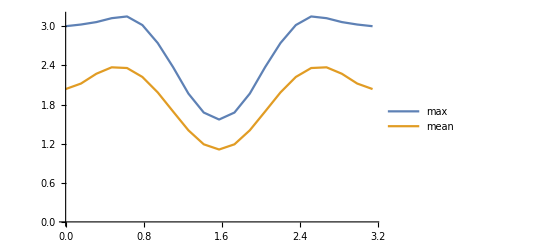

```mathematica
ListLinePlot[{fibomax,fibomean},PlotLegends->{"max","mean"}]
```

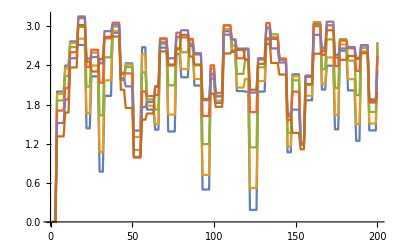

```mathematica
ListLinePlot[Table[fibon[[n]],{n,1,6}]]
```

#### Alternate 4 spin ent entrop

```mathematica
altfibo={-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,6.406853007629834296*10^-16,2.999999999999999556*10^+00,2.999999999999999556*10^+00,2.999999999999999112*10^+00,2.999999999999999112*10^+00,2.999999999999998668*10^+00,1.653878762572430938*10^+00,1.653878762572430938*10^+00,1.653878762572430716*10^+00,1.565321758921604411*10^+00,1.565321758921604411*10^+00,1.565321758921604189*10^+00,1.565321758921604189*10^+00,1.565321758921603967*10^+00,2.426996463741692533*10^+00,2.426996463741692089*10^+00,2.426996463741691645*10^+00,2.426996463741692089*10^+00,2.426996463741692089*10^+00,7.219778530846908682*10^-01,7.219778530846909792*10^-01,7.219778530846910902*10^-01,2.894998244155042588*10^+00,2.894998244155041256*10^+00,2.894998244155041256*10^+00,2.894998244155042144*10^+00,2.894998244155040812*10^+00,2.370609825734571741*10^-01,2.370609825734573128*10^-01,2.370609825734578124*10^-01,2.456847653392595809*10^+00,2.456847653392595365*10^+00,2.456847653392595365*10^+00,2.456847653392595809*10^+00,2.456847653392595365*10^+00,2.555975056967319858*10^+00,2.555975056967319858*10^+00,2.555975056967319858*10^+00,2.555975056967319858*10^+00,2.555975056967319414*10^+00,7.333784714332978183*10^-01,7.333784714332978183*10^-01,7.333784714332982624*10^-01,2.523440563404898640*10^+00,2.523440563404898640*10^+00,2.523440563404898640*10^+00,2.523440563404898640*10^+00,2.523440563404898196*10^+00,4.352460909364846420*10^-01,4.352460909364846420*10^-01,4.352460909364858632*10^-01,4.352460909364858632*10^-01,4.352460909364859742*10^-01,2.888768608110852565*10^+00,2.888768608110852121*10^+00,2.888768608110852121*10^+00,1.505513264675414575*10^+00,1.505513264675414797*10^+00,1.505513264675414797*10^+00,1.505513264675415241*10^+00,1.505513264675415019*10^+00,1.015929733617190633*10^+00,1.015929733617190633*10^+00,1.015929733617191077*10^+00,2.906387996381335714*10^+00,2.906387996381335714*10^+00,2.906387996381335714*10^+00,2.906387996381336158*10^+00,2.906387996381335270*10^+00,5.759458941328453596*10^-01,5.759458941328454706*10^-01,5.759458941328460257*10^-01,5.759458941328460257*10^-01,5.759458941328461368*10^-01,2.593461078758450888*10^+00,2.593461078758451333*10^+00,2.593461078758451777*10^+00,7.735243727889145049*10^-01,7.735243727889145049*10^-01,7.735243727889146159*10^-01,7.735243727889146159*10^-01,7.735243727889147269*10^-01,2.373658940400840134*10^+00,2.373658940400840578*10^+00,2.373658940400840578*10^+00,2.760529485966662477*10^+00,2.760529485966662477*10^+00,2.760529485966662477*10^+00,2.760529485966662477*10^+00,2.760529485966662477*10^+00,4.639597498102449730*10^-02,4.639597498102449730*10^-02,4.639597498102494832*10^-02,4.639597498102498996*10^-02,4.639597498102566997*10^-02,2.923118818799289365*10^+00,2.923118818799289365*10^+00,2.923118818799288476*10^+00,1.013633817945871263*10^+00,1.013633817945871263*10^+00,1.013633817945870819*10^+00,1.013633817945870819*10^+00,1.013633817945870819*10^+00,2.316748166957796506*10^+00,2.316748166957796506*10^+00,2.316748166957796062*10^+00,2.316748166957796062*10^+00,2.316748166957796062*10^+00,1.808548800735010564*10^+00,1.808548800735010786*10^+00,1.808548800735010342*10^+00,1.276161933434055040*10^+00,1.276161933434055040*10^+00,1.276161933434055262*10^+00,1.276161933434055262*10^+00,1.276161933434055484*10^+00,2.952987834508121079*10^+00,2.952987834508121079*10^+00,2.952987834508120635*10^+00,1.195597622668709628*10^-03,1.195597622668709628*10^-03,1.195597622669349741*10^-03,1.195597622669349741*10^-03,1.195597622670149882*10^-03,2.930811437051283441*10^+00,2.930811437051283441*10^+00,2.930811437051283441*10^+00,2.930811437051283441*10^+00,2.930811437051282109*10^+00,1.908101233814250453*10^+00,1.908101233814250453*10^+00,1.908101233814250453*10^+00,1.390185691609066687*10^+00,1.390185691609066909*10^+00,1.390185691609067575*10^+00,1.390185691609067353*10^+00,1.390185691609066909*10^+00,2.499752494997792063*10^+00,2.499752494997792063*10^+00,2.499752494997791619*10^+00,2.499752494997791175*10^+00,2.499752494997791619*10^+00,4.304698816527197103*10^-01,4.304698816527197103*10^-01,4.304698816527202654*10^-01,2.881340079804366905*10^+00,2.881340079804366017*10^+00,2.881340079804366017*10^+00,2.881340079804366461*10^+00,2.881340079804366017*10^+00,5.660448593628852887*10^-01,5.660448593628852887*10^-01,5.660448593628858438*10^-01,2.030950508292457712*10^+00,2.030950508292457712*10^+00,2.030950508292457712*10^+00,2.030950508292457712*10^+00,2.030950508292457712*10^+00,2.647007773642287454*10^+00,2.647007773642287898*10^+00,2.647007773642287454*10^+00,2.647007773642287454*10^+00,2.647007773642287454*10^+00,7.975228113728496382*10^-01,7.975228113728494161*10^-01,7.975228113728499713*10^-01,2.578217720104355237*10^+00,2.578217720104355237*10^+00,2.578217720104354349*10^+00,2.578217720104355681*10^+00,2.578217720104354349*10^+00,3.260441343369473999*10^-01,3.260441343369473999*10^-01,3.260441343369477329*10^-01,2.834266899595274669*10^+00,2.834266899595274669*10^+00,2.834266899595274225*10^+00,2.834266899595273781*10^+00,2.834266899595274225*10^+00,1.998035436826435918*10^+00,1.998035436826436362*10^+00,1.998035436826435918*10^+00,1.998035436826436140*10^+00,1.998035436826435918*10^+00,6.251545636470219325*10^-01,6.251545636470221545*10^-01,6.251545636470223766*10^-01,2.904090364621237708*10^+00,2.904090364621238596*10^+00,2.904090364621238152*10^+00,2.904090364621238152*10^+00,2.904090364621236819*10^+00,7.168453768026272765*10^-01,7.168453768026274986*10^-01,7.168453768026276096*10^-01,7.168453768026279427*10^-01,7.168453768026282757*10^-01,2.681385126538796015*10^+00,2.722912528242654327*10^-14,2.722912528242654327*10^-14,2.786981058318951437*10^-14,2.998724663313188099*10^+00,2.998724663311937100*10^+00,2.998724663313188543*10^+00,2.998724663311937100*10^+00,2.998724663313187655*10^+00,1.752358915133834572*10^+00,1.752358915133822359*10^+00,1.752358915133834572*10^+00,1.778826252950367115*10^+00,1.778826252950179709*10^+00,1.778826252950367115*10^+00,1.778826252950179487*10^+00,1.778826252950366671*10^+00,2.450044033094808782*10^+00,2.450044033094808782*10^+00,2.450044033094808338*10^+00,2.450044033094807894*10^+00,2.450044033094807450*10^+00,1.004923073174350812*10^+00,1.004923073174351034*10^+00,1.004923073174351700*10^+00,2.928752756824847925*10^+00,2.928752756824744008*10^+00,2.928752756824847037*10^+00,2.928752756824744008*10^+00,2.928752756824846148*10^+00,5.756163831610684456*10^-01,5.756163831610680015*10^-01,5.756163831610686676*10^-01,2.454099128123177209*10^+00,2.454099128123176321*10^+00,2.454099128123175877*10^+00,2.454099128123176765*10^+00,2.454099128123176321*10^+00,2.619160311581516076*10^+00,2.619160311581515632*10^+00,2.619160311581515632*10^+00,2.619160311581516076*10^+00,2.619160311581515188*10^+00,9.542317723232546234*10^-01,9.542317723232545124*10^-01,9.542317723232545124*10^-01,2.667908950781290756*10^+00,2.667908950781290311*10^+00,2.667908950781290311*10^+00,2.667908950781290756*10^+00,2.667908950781290311*10^+00,4.534545617599368139*10^-01,4.534545617599393674*10^-01,4.534545617599370360*10^-01,4.534545617599397005*10^-01,4.534545617599377576*10^-01,2.880137060406873672*10^+00,2.880137060406873672*10^+00,2.880137060406873228*10^+00,1.590786248270745329*10^+00,1.590786248270745329*10^+00,1.590786248270745329*10^+00,1.590786248270744885*10^+00,1.590786248270745329*10^+00,1.215424640119454835*10^+00,1.215424640119454835*10^+00,1.215424640119455058*10^+00,2.906656314638647931*10^+00,2.906656314638648819*10^+00,2.906656314638647487*10^+00,2.906656314638647487*10^+00,2.906656314638647487*10^+00,9.361093464075502801*10^-01,9.361093464075501691*10^-01,9.361093464075505022*10^-01,9.361093464075501691*10^-01,9.361093464075511683*10^-01,2.629146730499089646*10^+00,2.629146730499125617*10^+00,2.629146730499088758*10^+00,1.115180274682679329*10^+00,1.115180274682679551*10^+00,1.115180274682679329*10^+00,1.115180274682679551*10^+00,1.115180274682679773*10^+00,2.397117719698595550*10^+00,2.397117719698595550*10^+00,2.397117719698595550*10^+00,2.787274539306727306*10^+00,2.787274539306726862*10^+00,2.787274539306726417*10^+00,2.787274539306726862*10^+00,2.787274539306726862*10^+00,3.046399528917408395*10^-01,3.046399528917411170*10^-01,3.046399528917414501*10^-01,3.046399528917415611*10^-01,3.046399528917421717*10^-01,2.919480822055435354*10^+00,2.919480822055434910*10^+00,2.919480822055434022*10^+00,1.062158262575473966*10^+00,1.062158262575475964*10^+00,1.062158262575474410*10^+00,1.062158262575475964*10^+00,1.062158262575474188*10^+00,2.420561697369352228*10^+00,2.420561697369352228*10^+00,2.420561697369351783*10^+00,2.420561697369352228*10^+00,2.420561697369352228*10^+00,1.875498643463718862*10^+00,1.875498643463719528*10^+00,1.875498643463718640*10^+00,1.466228929068146503*10^+00,1.466228929068146059*10^+00,1.466228929068146281*10^+00,1.466228929068146725*10^+00,1.466228929068147391*10^+00,2.951241737549673338*10^+00,2.951241737549673338*10^+00,2.951241737549672450*10^+00,4.257787615604614606*10^-01,4.257787615604611275*10^-01,4.257787615604619602*10^-01,4.257787615604617937*10^-01,4.257787615604627929*10^-01,2.904151562273789899*10^+00,2.904151562272222709*10^+00,2.904151562273789455*10^+00,2.904151562272222264*10^+00,2.904151562273789899*10^+00,2.037308658420166729*10^+00,2.037308658420165841*10^+00,2.037308658420166285*10^+00,1.500127219074639529*10^+00,1.500127219074640195*10^+00,1.500127219074639529*10^+00,1.500127219074639306*10^+00,1.500127219074639751*10^+00,2.551000507036137677*10^+00,2.551000507036138121*10^+00,2.551000507036137677*10^+00,2.551000507036137677*10^+00,2.551000507036137233*10^+00,5.876355038799244701*10^-01,5.876355038799236929*10^-01,5.876355038799243591*10^-01,2.853006197132912369*10^+00,2.853006197132912369*10^+00,2.853006197132911481*10^+00,2.853006197132911925*10^+00,2.853006197132911481*10^+00,6.054329438192137536*10^-01,6.054329438191391466*10^-01,6.054329438192143087*10^-01,2.164341090076542962*10^+00,2.164341090076542073*10^+00,2.164341090076542073*10^+00,2.164341090076542518*10^+00,2.164341090076542073*10^+00,2.651474965145623308*10^+00,2.651474965145623308*10^+00,2.651474965145622420*10^+00,2.651474965145622420*10^+00,2.651474965145622420*10^+00,1.132157787104565383*10^+00,1.132157787104565605*10^+00,1.132157787104565605*10^+00,2.638620164831105619*10^+00,2.638620164831106063*10^+00,2.638620164831105175*10^+00,2.638620164831105175*10^+00,2.638620164831103843*10^+00,7.207967464733293639*10^-01,7.207967464733291418*10^-01,7.207967464733298080*10^-01,2.797636435857759007*10^+00,2.797636435857755899*10^+00,2.797636435857758563*10^+00,2.797636435857755455*10^+00,2.797636435857757675*10^+00,2.118594304390010397*10^+00,2.118594304390009952*10^+00,2.118594304390010841*10^+00,2.118594304390009952*10^+00,2.118594304390009952*10^+00,7.517629928752144197*10^-01,7.517629928752143087*10^-01,7.517629928752145307*10^-01,2.913599770540062028*10^+00,2.913599770540061584*10^+00,2.913599770540061140*10^+00,2.913599770540061140*10^+00,2.913599770540060696*10^+00,8.867144349484439303*10^-01,8.867144349484434862*10^-01,8.867144349484432642*10^-01,8.867144349484435972*10^-01,8.867144349484434862*10^-01,2.745745224474004154*10^+00,-9.610279511444755881*10^-16,-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,2.981416978993568723*10^+00,2.981416978993569167*10^+00,2.981416978993567835*10^+00,2.981416978993568279*10^+00,2.981416978993567835*10^+00,2.032098565832024306*10^+00,2.032098565832024750*10^+00,2.032098565832024306*10^+00,2.253902263947620277*10^+00,2.253902263947620721*10^+00,2.253902263947620277*10^+00,2.253902263947620277*10^+00,2.253902263947619389*10^+00,2.616603485375484706*10^+00,2.616603485375485594*10^+00,2.616603485375484706*10^+00,2.616603485375485150*10^+00,2.616603485375484706*10^+00,1.608797191196067677*10^+00,1.608797191196068121*10^+00,1.608797191196067677*10^+00,2.964220781648384762*10^+00,2.964220781648384762*10^+00,2.964220781648384317*10^+00,2.964220781648384762*10^+00,2.964220781648384317*10^+00,1.299572736581437127*10^+00,1.299572736581436905*10^+00,1.299572736581437127*10^+00,2.494503586821633423*10^+00,2.494503586821633423*10^+00,2.494503586821632979*10^+00,2.494503586821634311*10^+00,2.494503586821632979*10^+00,2.837513983773304105*10^+00,2.837513983773304105*10^+00,2.837513983773303217*10^+00,2.837513983773304105*10^+00,2.837513983773302328*10^+00,1.431569600622463190*10^+00,1.431569600622463856*10^+00,1.431569600622463412*10^+00,2.921472429720330943*10^+00,2.921472429720330943*10^+00,2.921472429720330943*10^+00,2.921472429720330055*10^+00,2.921472429720330055*10^+00,5.588789635031023995*10^-01,5.588789635031026215*10^-01,5.588789635031026215*10^-01,5.588789635031030656*10^-01,5.588789635031030656*10^-01,2.855391282629190286*10^+00,2.855391282629190730*10^+00,2.855391282629190730*10^+00,1.816817142892695802*10^+00,1.816817142892695802*10^+00,1.816817142892696024*10^+00,1.816817142892696468*10^+00,1.816817142892696024*10^+00,1.702623940755065401*10^+00,1.702623940755066068*10^+00,1.702623940755065624*10^+00,2.990306744670202743*10^+00,2.990306744670201855*10^+00,2.990306744670201411*10^+00,2.990306744670201855*10^+00,2.990306744670202299*10^+00,1.676550775138237803*10^+00,1.676550775138237359*10^+00,1.676550775138237803*10^+00,1.676550775138237803*10^+00,1.676550775138237359*10^+00,2.739876671449426926*10^+00,2.739876671449428258*10^+00,2.739876671449428258*10^+00,1.759937298568111430*10^+00,1.759937298568111208*10^+00,1.759937298568111430*10^+00,1.759937298568111208*10^+00,1.759937298568111208*10^+00,2.518085677107056775*10^+00,2.518085677107056775*10^+00,2.518085677107055886*10^+00,2.940256810949206212*10^+00,2.940256810949205768*10^+00,2.940256810949204880*10^+00,2.940256810949205768*10^+00,2.940256810949204880*10^+00,8.110111209627226536*10^-01,8.110111209627219875*10^-01,8.110111209627228757*10^-01,8.110111209627230977*10^-01,8.110111209627236528*10^-01,2.953913019438129339*10^+00,2.953913019438130672*10^+00,2.953913019438130227*10^+00,1.279978255315876279*10^+00,1.279978255315876279*10^+00,1.279978255315876279*10^+00,1.279978255315876057*10^+00,1.279978255315875835*10^+00,2.692200378572877195*10^+00,2.692200378572876751*10^+00,2.692200378572876307*10^+00,2.692200378572876307*10^+00,2.692200378572875419*10^+00,2.131309069514939480*10^+00,2.131309069514939036*10^+00,2.131309069514939480*10^+00,1.936977903057287342*10^+00,1.936977903057287342*10^+00,1.936977903057287786*10^+00,1.936977903057287786*10^+00,1.936977903057287342*10^+00,2.985717628658114187*10^+00,2.985717628658113743*10^+00,2.985717628658114187*10^+00,1.175335481365910262*10^+00,1.175335481365910040*10^+00,1.175335481365910706*10^+00,1.175335481365910484*10^+00,1.175335481365910928*10^+00,2.892636316284793452*10^+00,2.892636316284793008*10^+00,2.892636316284793452*10^+00,2.892636316284792564*10^+00,2.892636316284793008*10^+00,2.388521169918035092*10^+00,2.388521169918035092*10^+00,2.388521169918035092*10^+00,1.880752853583087969*10^+00,1.880752853583088413*10^+00,1.880752853583088191*10^+00,1.880752853583088635*10^+00,1.880752853583088413*10^+00,2.757393674419683638*10^+00,2.757393674419684082*10^+00,2.757393674419684082*10^+00,2.757393674419684082*10^+00,2.757393674419682306*10^+00,1.035892811939204350*10^+00,1.035892811939204572*10^+00,1.035892811939204128*10^+00,2.792218897777771325*10^+00,2.792218897777771325*10^+00,2.792218897777771325*10^+00,2.792218897777770881*10^+00,2.792218897777770437*10^+00,7.440442194631887718*10^-01,7.440442194631887718*10^-01,7.440442194631891049*10^-01,2.474280426386475273*10^+00,2.474280426386475717*10^+00,2.474280426386475273*10^+00,2.474280426386475717*10^+00,2.474280426386475717*10^+00,2.802852783397160596*10^+00,2.802852783397160596*10^+00,2.802852783397160596*10^+00,2.802852783397160152*10^+00,2.802852783397159708*10^+00,1.811234148227855778*10^+00,1.811234148227855778*10^+00,1.811234148227855112*10^+00,2.819573390068719654*10^+00,2.819573390068719210*10^+00,2.819573390068719654*10^+00,2.819573390068719210*10^+00,2.819573390068719654*10^+00,1.422639521795176609*10^+00,1.422639521795176165*10^+00,1.422639521795176609*10^+00,2.734402121638438654*10^+00,2.734402121638439542*10^+00,2.734402121638438654*10^+00,2.734402121638438210*10^+00,2.734402121638438654*10^+00,2.386945653721139315*10^+00,2.386945653721139315*10^+00,2.386945653721139315*10^+00,2.386945653721139315*10^+00,2.386945653721138427*10^+00,1.185348886338696506*10^+00,1.185348886338696506*10^+00,1.185348886338696506*10^+00,3.047006569608192716*10^+00,3.047006569608193605*10^+00,3.047006569608192272*10^+00,3.047006569608192272*10^+00,3.047006569608190940*10^+00,1.376933447191062587*10^+00,1.376933447191062365*10^+00,1.376933447191062587*10^+00,1.376933447191061921*10^+00,1.376933447191063031*10^+00,2.889527885846791211*10^+00,1.121199276335220928*10^-15,1.121199276335220928*10^-15,1.761884577098203667*10^-15,2.918699367482325613*10^+00,2.918699367482325613*10^+00,2.918699367482325169*10^+00,2.918699367482324725*10^+00,2.918699367482323836*10^+00,2.378172886805837383*10^+00,2.378172886805837383*10^+00,2.378172886805836939*10^+00,2.711235124928573992*10^+00,2.711235124928573104*10^+00,2.711235124928572660*10^+00,2.711235124928572660*10^+00,2.711235124928572215*10^+00,2.844122254746351608*10^+00,2.844122254746350276*10^+00,2.844122254746349832*10^+00,2.844122254746350720*10^+00,2.844122254746349832*10^+00,2.149951084200534268*10^+00,2.149951084200534268*10^+00,2.149951084200534712*10^+00,2.902223055774757920*10^+00,2.902223055774757920*10^+00,2.902223055774757476*10^+00,2.902223055774757476*10^+00,2.902223055774757476*10^+00,1.950647923353097113*10^+00,1.950647923353096891*10^+00,1.950647923353096669*10^+00,2.628626434814760326*10^+00,2.628626434814761659*10^+00,2.628626434814760771*10^+00,2.628626434814760771*10^+00,2.628626434814760771*10^+00,3.078461337815801002*10^+00,3.078461337815801002*10^+00,3.078461337815800558*10^+00,3.078461337815801890*10^+00,3.078461337815801002*10^+00,1.959766857539622986*10^+00,1.959766857539622542*10^+00,1.959766857539622320*10^+00,3.092458303962508648*10^+00,3.092458303962509092*10^+00,3.092458303962509092*10^+00,3.092458303962507316*10^+00,3.092458303962507316*10^+00,7.883573746611659550*10^-01,7.883573746611656219*10^-01,7.883573746611658439*10^-01,7.883573746611669542*10^-01,7.883573746611666211*10^-01,2.809380203008011723*10^+00,2.809380203008012611*10^+00,2.809380203008012167*10^+00,2.179219029580152345*10^+00,2.179219029580151901*10^+00,2.179219029580152345*10^+00,2.179219029580152345*10^+00,2.179219029580151901*10^+00,2.234856885613243360*10^+00,2.234856885613243360*10^+00,2.234856885613243804*10^+00,3.123037102515382912*10^+00,3.123037102515383800*10^+00,3.123037102515382468*10^+00,3.123037102515382912*10^+00,3.123037102515382024*10^+00,2.358278997438400637*10^+00,2.358278997438400193*10^+00,2.358278997438399749*10^+00,2.358278997438400193*10^+00,2.358278997438399749*10^+00,2.838627135826248260*10^+00,2.838627135826249148*10^+00,2.838627135826248704*10^+00,2.378902673452643057*10^+00,2.378902673452642613*10^+00,2.378902673452642169*10^+00,2.378902673452642613*10^+00,2.378902673452642613*10^+00,2.735666000776512785*10^+00,2.735666000776513229*10^+00,2.735666000776513229*10^+00,3.094976227986323103*10^+00,3.094976227986322659*10^+00,3.094976227986321771*10^+00,3.094976227986321771*10^+00,3.094976227986321771*10^+00,1.392744502347183833*10^+00,1.392744502347183166*10^+00,1.392744502347183611*10^+00,1.392744502347183833*10^+00,1.392744502347183611*10^+00,2.954404042802522667*10^+00,2.954404042802522223*10^+00,2.954404042802521335*10^+00,1.602045628638259611*10^+00,1.602045628638259611*10^+00,1.602045628638259167*10^+00,1.602045628638259611*10^+00,1.602045628638259389*10^+00,2.941272221230863515*10^+00,2.941272221230864403*10^+00,2.941272221230863071*10^+00,2.941272221230863959*10^+00,2.941272221230863071*10^+00,2.484296598450129512*10^+00,2.484296598450129956*10^+00,2.484296598450128624*10^+00,2.434293999192151947*10^+00,2.434293999192151503*10^+00,2.434293999192151503*10^+00,2.434293999192151947*10^+00,2.434293999192151059*10^+00,3.015654371386190746*10^+00,3.015654371386190746*10^+00,3.015654371386190746*10^+00,1.847866799741944011*10^+00,1.847866799741944677*10^+00,1.847866799741944233*10^+00,1.847866799741944233*10^+00,1.847866799741944011*10^+00,2.864127170015055679*10^+00,2.864127170015057011*10^+00,2.864127170015055679*10^+00,2.864127170015055679*10^+00,2.864127170015056123*10^+00,2.740996547526568072*10^+00,2.740996547526567628*10^+00,2.740996547526566296*10^+00,2.363715755085830761*10^+00,2.363715755085830317*10^+00,2.363715755085830317*10^+00,2.363715755085831205*10^+00,2.363715755085830761*10^+00,3.001253644952637689*10^+00,3.001253644952637245*10^+00,3.001253644952637689*10^+00,3.001253644952636801*10^+00,3.001253644952637245*10^+00,1.539901123754964019*10^+00,1.539901123754964241*10^+00,1.539901123754964241*10^+00,2.636630286916611610*10^+00,2.636630286916612498*10^+00,2.636630286916611610*10^+00,2.636630286916611610*10^+00,2.636630286916611610*10^+00,9.761531515373425005*10^-01,9.761531515373420564*10^-01,9.761531515373429446*10^-01,2.746683747746254678*10^+00,2.746683747746254234*10^+00,2.746683747746254234*10^+00,2.746683747746254234*10^+00,2.746683747746253790*10^+00,3.019560613969593632*10^+00,3.019560613969593632*10^+00,3.019560613969593188*10^+00,3.019560613969593632*10^+00,3.019560613969592744*10^+00,2.442433714944135303*10^+00,2.442433714944134859*10^+00,2.442433714944134859*10^+00,2.988534553700021856*10^+00,2.988534553700021856*10^+00,2.988534553700021412*10^+00,2.988534553700021412*10^+00,2.988534553700020524*10^+00,2.101473036916216230*10^+00,2.101473036916216230*10^+00,2.101473036916215342*10^+00,2.670926281980388506*10^+00,2.670926281980388062*10^+00,2.670926281980387618*10^+00,2.670926281980388062*10^+00,2.670926281980387618*10^+00,2.623776344618810263*10^+00,2.623776344618811152*10^+00,2.623776344618810707*10^+00,2.623776344618810263*10^+00,2.623776344618810263*10^+00,1.711253802436565108*10^+00,1.711253802436564442*10^+00,1.711253802436564664*10^+00,3.218568795327653387*10^+00,3.218568795327653387*10^+00,3.218568795327652943*10^+00,3.218568795327652943*10^+00,3.218568795327652055*10^+00,1.916866419163227198*10^+00,1.916866419163226976*10^+00,1.916866419163227864*10^+00,1.916866419163227198*10^+00,1.916866419163226976*10^+00,2.976549414362060997*10^+00,4.805139755722374982*10^-16,8.008566259537291637*10^-16,1.281370601525966465*10^-15,2.787556124351334930*10^+00,2.787556124351334930*10^+00,2.787556124351334041*10^+00,2.787556124351334041*10^+00,2.787556124351334041*10^+00,2.622903474035252369*10^+00,2.622903474035252813*10^+00,2.622903474035251925*10^+00,2.981903827271189300*10^+00,2.981903827271189300*10^+00,2.981903827271188412*10^+00,2.981903827271188412*10^+00,2.981903827271187968*10^+00,3.022253686131200823*10^+00,3.022253686131200823*10^+00,3.022253686131200379*10^+00,3.022253686131200379*10^+00,3.022253686131200379*10^+00,2.487184057790557290*10^+00,2.487184057790558178*10^+00,2.487184057790557290*10^+00,2.714462246835274595*10^+00,2.714462246835274151*10^+00,2.714462246835274151*10^+00,2.714462246835273262*10^+00,2.714462246835273262*10^+00,2.397455296103001121*10^+00,2.397455296103000677*10^+00,2.397455296103000233*10^+00,2.761138014488607961*10^+00,2.761138014488607517*10^+00,2.761138014488607961*10^+00,2.761138014488607073*10^+00,2.761138014488607073*10^+00,3.206202020780006379*10^+00,3.206202020780006379*10^+00,3.206202020780005935*10^+00,3.206202020780005491*10^+00,3.206202020780004602*10^+00,2.351153284384461362*10^+00,2.351153284384460918*10^+00,2.351153284384460473*10^+00,3.008457583852617745*10^+00,3.008457583852617745*10^+00,3.008457583852616857*10^+00,3.008457583852616857*10^+00,3.008457583852615080*10^+00,1.021312889350202369*10^+00,1.021312889350202147*10^+00,1.021312889350202591*10^+00,1.021312889350201925*10^+00,1.021312889350201925*10^+00,2.639929082019596418*10^+00,2.639929082019595530*10^+00,2.639929082019595974*10^+00,2.457565383680101689*10^+00,2.457565383680101689*10^+00,2.457565383680101689*10^+00,2.457565383680101689*10^+00,2.457565383680100801*10^+00,2.629534715346799612*10^+00,2.629534715346799612*10^+00,2.629534715346799167*10^+00,3.182309930848564505*10^+00,3.182309930848564061*10^+00,3.182309930848564061*10^+00,3.182309930848564505*10^+00,3.182309930848564505*10^+00,2.742227077011868630*10^+00,2.742227077011868630*10^+00,2.742227077011868186*10^+00,2.742227077011868186*10^+00,2.742227077011867742*10^+00,2.836300619422144287*10^+00,2.836300619422143399*10^+00,2.836300619422143843*10^+00,2.797507044208033200*10^+00,2.797507044208033200*10^+00,2.797507044208033644*10^+00,2.797507044208032756*10^+00,2.797507044208032312*10^+00,2.918519129504693943*10^+00,2.918519129504693943*10^+00,2.918519129504693499*10^+00,3.158339294702063871*10^+00,3.158339294702064759*10^+00,3.158339294702063427*10^+00,3.158339294702063871*10^+00,3.158339294702063871*10^+00,1.863951032204908431*10^+00,1.863951032204908653*10^+00,1.863951032204908209*10^+00,1.863951032204908209*10^+00,1.863951032204908653*10^+00,2.816659495300605442*10^+00,2.816659495300604998*10^+00,2.816659495300604998*10^+00,1.887910187454778121*10^+00,1.887910187454779232*10^+00,1.887910187454778344*10^+00,1.887910187454779010*10^+00,1.887910187454778788*10^+00,3.009826012489625668*10^+00,3.009826012489627001*10^+00,3.009826012489625224*10^+00,3.009826012489625668*10^+00,3.009826012489625668*10^+00,2.775733365163425503*10^+00,2.775733365163426392*10^+00,2.775733365163425947*10^+00,2.763772287133381411*10^+00,2.763772287133381411*10^+00,2.763772287133380523*10^+00,2.763772287133380523*10^+00,2.763772287133380523*10^+00,2.926721688606728211*10^+00,2.926721688606728655*10^+00,2.926721688606727767*10^+00,2.235963499210881444*10^+00,2.235963499210881889*10^+00,2.235963499210881889*10^+00,2.235963499210881000*10^+00,2.235963499210881444*10^+00,2.814350514425416172*10^+00,2.814350514425416172*10^+00,2.814350514425416172*10^+00,2.814350514425416172*10^+00,2.814350514425415728*10^+00,2.907573468106193104*10^+00,2.907573468106193548*10^+00,2.907573468106193104*10^+00,2.752216250343873405*10^+00,2.752216250343873405*10^+00,2.752216250343872517*10^+00,2.752216250343873405*10^+00,2.752216250343872517*10^+00,3.148313453033861009*10^+00,3.148313453033861009*10^+00,3.148313453033860565*10^+00,3.148313453033860565*10^+00,3.148313453033861009*10^+00,1.965480035888089505*10^+00,1.965480035888089727*10^+00,1.965480035888088839*10^+00,2.325168925938704056*10^+00,2.325168925938702724*10^+00,2.325168925938703612*10^+00,2.325168925938702724*10^+00,2.325168925938702724*10^+00,1.180719933207948547*10^+00,1.180719933207948769*10^+00,1.180719933207948991*10^+00,2.910495364756892744*10^+00,2.910495364756891856*10^+00,2.910495364756891412*10^+00,2.910495364756892744*10^+00,2.910495364756890524*10^+00,3.150449027498841481*10^+00,3.150449027498841481*10^+00,3.150449027498841481*10^+00,3.150449027498841037*10^+00,3.150449027498840593*10^+00,2.831106664172661880*10^+00,2.831106664172661880*10^+00,2.831106664172661436*10^+00,3.104302791610387136*10^+00,3.104302791610387580*10^+00,3.104302791610386691*10^+00,3.104302791610386691*10^+00,3.104302791610386691*10^+00,2.508760189704497545*10^+00,2.508760189704497101*10^+00,2.508760189704497101*10^+00,2.576988350462961819*10^+00,2.576988350462961819*10^+00,2.576988350462960931*10^+00,2.576988350462961375*10^+00,2.576988350462960931*10^+00,2.706723115182017914*10^+00,2.706723115182017469*10^+00,2.706723115182017469*10^+00,2.706723115182016581*10^+00,2.706723115182017914*10^+00,2.162904032486415939*10^+00,2.162904032486416384*10^+00,2.162904032486415939*10^+00,3.304486612957659553*10^+00,3.304486612957659553*10^+00,3.304486612957657332*10^+00,3.304486612957659109*10^+00,3.304486612957658220*10^+00,2.378520116291329423*10^+00,2.378520116291330311*10^+00,2.378520116291329423*10^+00,2.378520116291328979*10^+00,2.378520116291328979*10^+00,2.844235963014376978*10^+00,3.203426503814917641*10^-16,-0.000000000000000000*10^+00,6.406853007629834296*10^-16,2.587309775975491277*10^+00,2.587309775975491277*10^+00,2.587309775975490833*10^+00,2.587309775975490833*10^+00,2.587309775975490833*10^+00,2.693259470987999116*10^+00,2.693259470987999116*10^+00,2.693259470987999116*10^+00,3.011307784282109878*10^+00,3.011307784282110767*10^+00,3.011307784282109878*10^+00,3.011307784282110767*10^+00,3.011307784282109878*10^+00,3.045941629743472490*10^+00,3.045941629743473378*10^+00,3.045941629743472490*10^+00,3.045941629743472934*10^+00,3.045941629743473378*10^+00,2.522895322711244059*10^+00,2.522895322711243615*10^+00,2.522895322711243615*10^+00,2.408589727685534143*10^+00,2.408589727685534143*10^+00,2.408589727685535031*10^+00,2.408589727685535031*10^+00,2.408589727685534587*10^+00,2.544291272193395237*10^+00,2.544291272193394349*10^+00,2.544291272193393461*10^+00,2.819707802335923219*10^+00,2.819707802335923663*10^+00,2.819707802335922331*10^+00,2.819707802335922331*10^+00,2.819707802335922331*10^+00,3.143499705688425738*10^+00,3.143499705688426626*10^+00,3.143499705688425294*10^+00,3.143499705688425738*10^+00,3.143499705688424406*10^+00,2.525826712364928284*10^+00,2.525826712364926951*10^+00,2.525826712364927396*10^+00,2.626497258940617918*10^+00,2.626497258940617474*10^+00,2.626497258940617030*10^+00,2.626497258940617030*10^+00,2.626497258940617030*10^+00,1.143242573435589549*10^+00,1.143242573435590881*10^+00,1.143242573435590437*10^+00,1.143242573435590437*10^+00,1.143242573435590437*10^+00,2.431978856870995021*10^+00,2.431978856870995021*10^+00,2.431978856870994576*10^+00,2.574541377158670485*10^+00,2.574541377158669597*10^+00,2.574541377158670041*10^+00,2.574541377158670041*10^+00,2.574541377158670041*10^+00,2.840354282011944065*10^+00,2.840354282011943177*10^+00,2.840354282011943177*10^+00,3.113598287612152848*10^+00,3.113598287612153737*10^+00,3.113598287612153293*10^+00,3.113598287612153293*10^+00,3.113598287612152404*10^+00,2.789030180280628102*10^+00,2.789030180280628546*10^+00,2.789030180280627658*10^+00,2.789030180280627658*10^+00,2.789030180280627658*10^+00,2.694520141118091239*10^+00,2.694520141118090795*10^+00,2.694520141118090351*10^+00,2.961864201206159120*10^+00,2.961864201206159564*10^+00,2.961864201206158231*10^+00,2.961864201206159120*10^+00,2.961864201206158231*10^+00,2.995503486097854218*10^+00,2.995503486097854662*10^+00,2.995503486097853774*10^+00,3.057066242724573613*10^+00,3.057066242724572724*10^+00,3.057066242724573168*10^+00,3.057066242724572724*10^+00,3.057066242724572724*10^+00,2.091151977914329496*10^+00,2.091151977914329940*10^+00,2.091151977914329940*10^+00,2.091151977914329940*10^+00,2.091151977914329496*10^+00,2.448844877347877702*10^+00,2.448844877347876814*10^+00,2.448844877347877258*10^+00,1.965654414691551777*10^+00,1.965654414691551777*10^+00,1.965654414691552221*10^+00,1.965654414691552221*10^+00,1.965654414691551999*10^+00,2.917240837199904568*10^+00,2.917240837199903236*10^+00,2.917240837199902792*10^+00,2.917240837199903236*10^+00,2.917240837199903680*10^+00,2.912385498755047930*10^+00,2.912385498755047042*10^+00,2.912385498755047486*10^+00,2.889370923872242258*10^+00,2.889370923872242258*10^+00,2.889370923872242258*10^+00,2.889370923872242258*10^+00,2.889370923872241370*10^+00,2.727056540969739817*10^+00,2.727056540969739817*10^+00,2.727056540969740261*10^+00,2.308149107461429761*10^+00,2.308149107461429317*10^+00,2.308149107461430205*10^+00,2.308149107461429761*10^+00,2.308149107461429761*10^+00,2.710041993571254970*10^+00,2.710041993571254970*10^+00,2.710041993571254082*10^+00,2.710041993571254082*10^+00,2.710041993571254082*10^+00,2.891370225873985067*10^+00,2.891370225873985067*10^+00,2.891370225873984623*10^+00,2.925095265349025198*10^+00,2.925095265349025198*10^+00,2.925095265349024753*10^+00,2.925095265349024309*10^+00,2.925095265349023421*10^+00,3.111750004194407726*10^+00,3.111750004194407282*10^+00,3.111750004194407282*10^+00,3.111750004194407282*10^+00,3.111750004194406394*10^+00,2.207849786358151434*10^+00,2.207849786358151434*10^+00,2.207849786358150990*10^+00,1.838071926330891337*10^+00,1.838071926330892447*10^+00,1.838071926330892225*10^+00,1.838071926330891115*10^+00,1.838071926330891337*10^+00,1.278461838734437972*10^+00,1.278461838734437972*10^+00,1.278461838734438194*10^+00,2.882117694890054427*10^+00,2.882117694890053095*10^+00,2.882117694890053095*10^+00,2.882117694890053095*10^+00,2.882117694890053095*10^+00,3.092746631076551012*10^+00,3.092746631076550567*10^+00,3.092746631076550123*10^+00,3.092746631076550123*10^+00,3.092746631076551012*10^+00,2.914907733845774729*10^+00,2.914907733845774729*10^+00,2.914907733845773841*10^+00,3.051146110126171429*10^+00,3.051146110126171873*10^+00,3.051146110126171429*10^+00,3.051146110126170985*10^+00,3.051146110126170541*10^+00,2.609237438006373644*10^+00,2.609237438006372756*10^+00,2.609237438006372756*10^+00,2.453898544855592778*10^+00,2.453898544855592334*10^+00,2.453898544855591890*10^+00,2.453898544855591446*10^+00,2.453898544855591002*10^+00,2.606944398236716420*10^+00,2.606944398236716420*10^+00,2.606944398236716420*10^+00,2.606944398236716420*10^+00,2.606944398236716420*10^+00,2.410480994907254093*10^+00,2.410480994907254093*10^+00,2.410480994907254093*10^+00,3.224629744978660728*10^+00,3.224629744978660728*10^+00,3.224629744978660284*10^+00,3.224629744978660284*10^+00,3.224629744978659396*10^+00,2.598354371281260455*10^+00,2.598354371281261344*10^+00,2.598354371281261344*10^+00,2.598354371281260455*10^+00,2.598354371281260011*10^+00,2.479224049589292544*10^+00,-9.610279511444755881*10^-16,-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,2.341986164786201030*10^+00,2.341986164786201030*10^+00,2.341986164786200142*10^+00,2.341986164786201030*10^+00,2.341986164786200586*10^+00,2.551145534378437940*10^+00,2.551145534378438384*10^+00,2.551145534378438384*10^+00,2.841890338961801543*10^+00,2.841890338961800655*10^+00,2.841890338961800211*10^+00,2.841890338961800655*10^+00,2.841890338961800211*10^+00,2.883712111054716143*10^+00,2.883712111054715699*10^+00,2.883712111054715699*10^+00,2.883712111054715255*10^+00,2.883712111054715255*10^+00,2.378111612160870081*10^+00,2.378111612160869637*10^+00,2.378111612160869193*10^+00,2.078379611164754781*10^+00,2.078379611164755669*10^+00,2.078379611164754781*10^+00,2.078379611164754781*10^+00,2.078379611164754337*10^+00,2.458933106327104490*10^+00,2.458933106327104490*10^+00,2.458933106327103602*10^+00,2.734188962403512058*10^+00,2.734188962403512058*10^+00,2.734188962403511169*10^+00,2.734188962403511169*10^+00,2.734188962403510281*10^+00,2.874636414331017686*10^+00,2.874636414331018130*10^+00,2.874636414331018130*10^+00,2.874636414331018130*10^+00,2.874636414331017242*10^+00,2.452694213623219266*10^+00,2.452694213623219266*10^+00,2.452694213623217934*10^+00,2.039104369570181596*10^+00,2.039104369570180264*10^+00,2.039104369570180264*10^+00,2.039104369570180708*10^+00,2.039104369570179820*10^+00,1.094462279687553607*10^+00,1.094462279687553163*10^+00,1.094462279687553163*10^+00,1.094462279687553163*10^+00,1.094462279687553607*10^+00,2.237248941914796507*10^+00,2.237248941914796951*10^+00,2.237248941914796507*10^+00,2.498548003508127113*10^+00,2.498548003508127557*10^+00,2.498548003508127113*10^+00,2.498548003508127557*10^+00,2.498548003508126669*10^+00,2.791426019912759848*10^+00,2.791426019912760736*10^+00,2.791426019912759848*10^+00,2.908879474821564504*10^+00,2.908879474821563615*10^+00,2.908879474821563615*10^+00,2.908879474821563615*10^+00,2.908879474821562727*10^+00,2.580892302182136167*10^+00,2.580892302182135722*10^+00,2.580892302182135722*10^+00,2.580892302182134834*10^+00,2.580892302182134834*10^+00,2.435689648537650687*10^+00,2.435689648537650243*10^+00,2.435689648537651131*10^+00,2.888338183384293600*10^+00,2.888338183384294044*10^+00,2.888338183384293600*10^+00,2.888338183384292712*10^+00,2.888338183384292712*10^+00,2.906392579421186895*10^+00,2.906392579421186895*10^+00,2.906392579421186451*10^+00,2.758748655027622121*10^+00,2.758748655027622121*10^+00,2.758748655027621677*10^+00,2.758748655027621233*10^+00,2.758748655027622121*10^+00,2.091815090440058089*10^+00,2.091815090440056757*10^+00,2.091815090440057645*10^+00,2.091815090440057201*10^+00,2.091815090440057201*10^+00,1.949786540628494880*10^+00,1.949786540628494436*10^+00,1.949786540628493769*10^+00,1.814947413271312815*10^+00,1.814947413271312815*10^+00,1.814947413271312815*10^+00,1.814947413271313037*10^+00,1.814947413271312593*10^+00,2.720961858943375944*10^+00,2.720961858943375944*10^+00,2.720961858943375056*10^+00,2.720961858943374612*10^+00,2.720961858943375056*10^+00,2.814458561271686587*10^+00,2.814458561271686587*10^+00,2.814458561271685699*10^+00,2.822361512837689546*10^+00,2.822361512837689546*10^+00,2.822361512837688213*10^+00,2.822361512837688657*10^+00,2.822361512837688213*10^+00,2.449770528255916346*10^+00,2.449770528255916346*10^+00,2.449770528255915902*10^+00,2.142941437694480200*10^+00,2.142941437694480200*10^+00,2.142941437694480200*10^+00,2.142941437694480200*10^+00,2.142941437694480200*10^+00,2.516795523896766973*10^+00,2.516795523896767417*10^+00,2.516795523896766529*10^+00,2.516795523896766973*10^+00,2.516795523896766085*10^+00,2.738355601984103327*10^+00,2.738355601984102883*10^+00,2.738355601984102883*10^+00,2.837180579064800146*10^+00,2.837180579064799701*10^+00,2.837180579064799701*10^+00,2.837180579064800590*10^+00,2.837180579064799257*10^+00,2.879867316040167768*10^+00,2.879867316040168213*10^+00,2.879867316040168213*10^+00,2.879867316040168213*10^+00,2.879867316040168213*10^+00,2.227637862569813887*10^+00,2.227637862569814331*10^+00,2.227637862569813443*10^+00,1.308699244643677595*10^+00,1.308699244643677373*10^+00,1.308699244643677817*10^+00,1.308699244643677373*10^+00,1.308699244643677151*10^+00,1.244501173899553503*10^+00,1.244501173899553059*10^+00,1.244501173899552837*10^+00,2.739112327890286913*10^+00,2.739112327890287801*10^+00,2.739112327890287801*10^+00,2.739112327890287357*10^+00,2.739112327890286913*10^+00,2.834289952370939503*10^+00,2.834289952370940391*10^+00,2.834289952370938614*10^+00,2.834289952370939503*10^+00,2.834289952370938170*10^+00,2.776130517787003260*10^+00,2.776130517787003260*10^+00,2.776130517787002816*10^+00,2.860911470800243883*10^+00,2.860911470800243883*10^+00,2.860911470800243883*10^+00,2.860911470800244327*10^+00,2.860911470800243883*10^+00,2.458157915600341692*10^+00,2.458157915600341248*10^+00,2.458157915600341692*10^+00,2.314231769399017313*10^+00,2.314231769399017313*10^+00,2.314231769399017757*10^+00,2.314231769399016869*10^+00,2.314231769399017313*10^+00,2.388193233304160223*10^+00,2.388193233304160223*10^+00,2.388193233304160223*10^+00,2.388193233304160223*10^+00,2.388193233304160223*10^+00,2.402501908236589934*10^+00,2.402501908236589045*10^+00,2.402501908236589045*10^+00,2.942529609318387251*10^+00,2.942529609318387251*10^+00,2.942529609318386807*10^+00,2.942529609318387696*10^+00,2.942529609318387251*10^+00,2.565048292804202212*10^+00,2.565048292804203101*10^+00,2.565048292804201324*10^+00,2.565048292804202212*10^+00,2.565048292804201324*10^+00,1.953941770090528385*10^+00,-3.203426503814917641*10^-16,-6.406853007629837254*10^-16,3.203426503814917641*10^-16,2.091405684522765540*10^+00,2.091405684522765540*10^+00,2.091405684522765540*10^+00,2.091405684522765540*10^+00,2.091405684522765540*10^+00,2.238344451623535569*10^+00,2.238344451623534681*10^+00,2.238344451623535125*10^+00,2.513493380930929888*10^+00,2.513493380930929444*10^+00,2.513493380930929444*10^+00,2.513493380930929000*10^+00,2.513493380930928112*10^+00,2.563625601356352313*10^+00,2.563625601356353645*10^+00,2.563625601356353645*10^+00,2.563625601356352313*10^+00,2.563625601356352313*10^+00,2.129560884721700020*10^+00,2.129560884721700464*10^+00,2.129560884721699576*10^+00,1.797586180292073843*10^+00,1.797586180292073621*10^+00,1.797586180292074065*10^+00,1.797586180292074287*10^+00,1.797586180292074065*10^+00,2.218310302478090357*10^+00,2.218310302478090357*10^+00,2.218310302478090357*10^+00,2.500098281458441374*10^+00,2.500098281458440930*10^+00,2.500098281458440930*10^+00,2.500098281458441818*10^+00,2.500098281458441374*10^+00,2.453810217124395621*10^+00,2.453810217124395621*10^+00,2.453810217124395177*10^+00,2.453810217124394732*10^+00,2.453810217124394732*10^+00,2.228629444809790527*10^+00,2.228629444809791416*10^+00,2.228629444809790527*10^+00,1.423552763088208550*10^+00,1.423552763088208550*10^+00,1.423552763088206774*10^+00,1.423552763088209661*10^+00,1.423552763088210549*10^+00,9.325011323333809443*10^-01,9.325011323333811664*10^-01,9.325011323333811664*10^-01,9.325011323333813884*10^-01,9.325011323333816105*10^-01,2.067514786875570998*10^+00,2.067514786875570554*10^+00,2.067514786875570554*10^+00,2.236433488289674365*10^+00,2.236433488289673921*10^+00,2.236433488289673477*10^+00,2.236433488289673477*10^+00,2.236433488289673033*10^+00,2.541359346173958311*10^+00,2.541359346173958755*10^+00,2.541359346173957867*10^+00,2.599507659039260066*10^+00,2.599507659039259622*10^+00,2.599507659039260066*10^+00,2.599507659039259178*10^+00,2.599507659039259622*10^+00,2.242548586515514142*10^+00,2.242548586515514142*10^+00,2.242548586515513254*10^+00,2.242548586515514142*10^+00,2.242548586515513698*10^+00,2.079429426472821696*10^+00,2.079429426472821696*10^+00,2.079429426472820808*10^+00,2.634022906109479756*10^+00,2.634022906109478868*10^+00,2.634022906109479312*10^+00,2.634022906109479756*10^+00,2.634022906109477535*10^+00,2.653668864069278044*10^+00,2.653668864069277600*10^+00,2.653668864069276712*10^+00,2.321661115564256139*10^+00,2.321661115564257027*10^+00,2.321661115564256139*10^+00,2.321661115564256139*10^+00,2.321661115564256139*10^+00,1.927263414842323330*10^+00,1.927263414842322664*10^+00,1.927263414842321110*10^+00,1.927263414842322220*10^+00,1.927263414842322664*10^+00,1.481979738582907213*10^+00,1.481979738582908102*10^+00,1.481979738582907435*10^+00,1.528925304291044673*10^+00,1.528925304291044895*10^+00,1.528925304291044895*10^+00,1.528925304291045117*10^+00,1.528925304291045784*10^+00,2.472311172015415615*10^+00,2.472311172015416059*10^+00,2.472311172015415615*10^+00,2.472311172015416059*10^+00,2.472311172015415170*10^+00,2.509200410430736827*10^+00,2.509200410430736827*10^+00,2.509200410430737271*10^+00,2.570847725945634821*10^+00,2.570847725945635709*10^+00,2.570847725945635709*10^+00,2.570847725945635709*10^+00,2.570847725945635265*10^+00,2.172076028496871203*10^+00,2.172076028496871203*10^+00,2.172076028496871647*10^+00,1.851223791392154094*10^+00,1.851223791392153872*10^+00,1.851223791392153650*10^+00,1.851223791392153650*10^+00,1.851223791392153872*10^+00,2.240873503122502441*10^+00,2.240873503122502886*10^+00,2.240873503122501553*10^+00,2.240873503122502886*10^+00,2.240873503122501997*10^+00,2.489390263508407752*10^+00,2.489390263508407308*10^+00,2.489390263508407308*10^+00,2.547080150731731329*10^+00,2.547080150731731329*10^+00,2.547080150731731329*10^+00,2.547080150731730885*10^+00,2.547080150731730441*10^+00,2.470001087806128925*10^+00,2.470001087806128481*10^+00,2.470001087806128037*10^+00,2.470001087806128037*10^+00,2.470001087806128481*10^+00,2.062441614678241386*10^+00,2.062441614678240942*10^+00,2.062441614678240498*10^+00,9.093991303359976186*10^-01,9.093991303359971745*10^-01,9.093991303359981737*10^-01,9.093991303359972855*10^-01,9.093991303359979517*10^-01,1.116386491626097266*10^+00,1.116386491626096600*10^+00,1.116386491626097266*10^+00,2.542655000798047293*10^+00,2.542655000798048626*10^+00,2.542655000798047293*10^+00,2.542655000798047737*10^+00,2.542655000798047737*10^+00,2.445636287556580690*10^+00,2.445636287556580690*10^+00,2.445636287556580246*10^+00,2.445636287556580690*10^+00,2.445636287556580690*10^+00,2.458313776022724717*10^+00,2.458313776022724273*10^+00,2.458313776022723829*10^+00,2.571592583634980222*10^+00,2.571592583634980667*10^+00,2.571592583634980222*10^+00,2.571592583634979334*10^+00,2.571592583634978890*10^+00,2.149046734654046720*10^+00,2.149046734654046276*10^+00,2.149046734654045832*10^+00,2.126516178077691777*10^+00,2.126516178077692221*10^+00,2.126516178077691777*10^+00,2.126516178077692665*10^+00,2.126516178077692221*10^+00,2.084794042199701103*10^+00,2.084794042199701103*10^+00,2.084794042199700659*10^+00,2.084794042199700659*10^+00,2.084794042199700659*10^+00,2.187821536738318695*10^+00,2.187821536738318695*10^+00,2.187821536738318695*10^+00,2.524629479910240892*10^+00,2.524629479910240448*10^+00,2.524629479910240448*10^+00,2.524629479910240892*10^+00,2.524629479910240448*10^+00,2.340629737696740875*10^+00,2.340629737696741763*10^+00,2.340629737696740431*10^+00,2.340629737696740875*10^+00,2.340629737696740431*10^+00,1.447630969193594686*10^+00,-3.203426503814917641*10^-16,-6.406853007629837254*10^-16,3.203426503814917641*10^-16,1.877982233341431106*10^+00,1.877982233341431328*10^+00,1.877982233341430884*10^+00,1.877982233341431106*10^+00,1.877982233341430884*10^+00,1.882588405754048733*10^+00,1.882588405754049621*10^+00,1.882588405754048955*10^+00,2.118068242758663899*10^+00,2.118068242758663011*10^+00,2.118068242758663455*10^+00,2.118068242758663899*10^+00,2.118068242758663455*10^+00,2.215321868563693730*10^+00,2.215321868563694174*10^+00,2.215321868563693730*10^+00,2.215321868563694618*10^+00,2.215321868563693730*10^+00,1.837707686528976092*10^+00,1.837707686528975870*10^+00,1.837707686528974982*10^+00,1.603190888440549244*10^+00,1.603190888440549022*10^+00,1.603190888440549244*10^+00,1.603190888440549244*10^+00,1.603190888440548356*10^+00,1.912513198383415158*10^+00,1.912513198383413826*10^+00,1.912513198383413826*10^+00,2.166504498997806394*10^+00,2.166504498997807282*10^+00,2.166504498997806838*10^+00,2.166504498997806838*10^+00,2.166504498997806838*10^+00,2.019003493536946081*10^+00,2.019003493536946081*10^+00,2.019003493536946081*10^+00,2.019003493536945637*10^+00,2.019003493536945637*10^+00,1.954999068588024524*10^+00,1.954999068588024747*10^+00,1.954999068588023192*10^+00,9.592423783605524834*10^-01,9.592423783605518173*10^-01,9.592423783605527055*10^-01,9.592423783605521503*10^-01,9.592423783605521503*10^-01,7.384072550297108295*10^-01,7.384072550297104964*10^-01,7.384072550297109405*10^-01,7.384072550297111626*10^-01,7.384072550297113846*10^-01,1.912617497182143023*10^+00,1.912617497182142801*10^+00,1.912617497182143689*10^+00,1.874015016119792598*10^+00,1.874015016119792154*10^+00,1.874015016119792154*10^+00,1.874015016119792154*10^+00,1.874015016119792820*10^+00,2.184860454483442460*10^+00,2.184860454483441572*10^+00,2.184860454483441572*10^+00,2.288386226928150524*10^+00,2.288386226928150524*10^+00,2.288386226928150080*10^+00,2.288386226928150080*10^+00,2.288386226928150080*10^+00,1.879373861374435073*10^+00,1.879373861374434185*10^+00,1.879373861374435517*10^+00,1.879373861374434407*10^+00,1.879373861374435073*10^+00,1.757209429011757251*10^+00,1.757209429011756807*10^+00,1.757209429011756807*10^+00,2.296442906428151964*10^+00,2.296442906428151520*10^+00,2.296442906428151964*10^+00,2.296442906428151076*10^+00,2.296442906428151076*10^+00,2.311147526972429311*10^+00,2.311147526972429755*10^+00,2.311147526972430200*10^+00,1.863434681090832878*10^+00,1.863434681090833767*10^+00,1.863434681090832878*10^+00,1.863434681090833323*10^+00,1.863434681090832878*10^+00,1.690953481855432816*10^+00,1.690953481855432816*10^+00,1.690953481855433038*10^+00,1.690953481855433038*10^+00,1.690953481855433038*10^+00,1.168707530282419693*10^+00,1.168707530282418805*10^+00,1.168707530282419027*10^+00,1.259681092018961390*10^+00,1.259681092018960946*10^+00,1.259681092018960946*10^+00,1.259681092018960724*10^+00,1.259681092018962056*10^+00,2.215824090647181777*10^+00,2.215824090647182221*10^+00,2.215824090647182665*10^+00,2.215824090647181777*10^+00,2.215824090647182665*10^+00,2.088126599539877670*10^+00,2.088126599539877226*10^+00,2.088126599539877226*10^+00,2.231085507359250819*10^+00,2.231085507359251707*10^+00,2.231085507359251263*10^+00,2.231085507359250375*10^+00,2.231085507359251263*10^+00,1.913785636838560400*10^+00,1.913785636838559956*10^+00,1.913785636838560400*10^+00,1.511312688172441021*10^+00,1.511312688172440133*10^+00,1.511312688172440355*10^+00,1.511312688172440355*10^+00,1.511312688172440133*10^+00,1.934826296600095086*10^+00,1.934826296600095308*10^+00,1.934826296600095308*10^+00,1.934826296600095086*10^+00,1.934826296600095308*10^+00,2.198069009047787237*10^+00,2.198069009047787237*10^+00,2.198069009047786793*10^+00,2.185865267497316466*10^+00,2.185865267497317799*10^+00,2.185865267497317355*10^+00,2.185865267497316911*10^+00,2.185865267497317355*10^+00,2.005570554247426251*10^+00,2.005570554247426251*10^+00,2.005570554247426696*10^+00,2.005570554247426696*10^+00,2.005570554247425807*10^+00,1.814702034406216358*10^+00,1.814702034406216358*10^+00,1.814702034406215914*10^+00,7.356599713446109190*10^-01,7.356599713446118072*10^-01,7.356599713446109190*10^-01,7.356599713446113631*10^-01,7.356599713446122513*10^-01,9.499220757685502559*10^-01,9.499220757685509220*10^-01,9.499220757685506999*10^-01,2.292948093325501979*10^+00,2.292948093325502423*10^+00,2.292948093325501979*10^+00,2.292948093325501979*10^+00,2.292948093325501979*10^+00,2.034338956398916931*10^+00,2.034338956398917375*10^+00,2.034338956398917375*10^+00,2.034338956398917375*10^+00,2.034338956398917819*10^+00,2.073633191722314972*10^+00,2.073633191722315416*10^+00,2.073633191722315416*10^+00,2.248195602913505731*10^+00,2.248195602913506619*10^+00,2.248195602913506175*10^+00,2.248195602913505287*10^+00,2.248195602913505731*10^+00,1.778046869508105976*10^+00,1.778046869508105754*10^+00,1.778046869508106864*10^+00,1.880424220626143672*10^+00,1.880424220626144560*10^+00,1.880424220626144116*10^+00,1.880424220626143672*10^+00,1.880424220626143672*10^+00,1.788215079899796667*10^+00,1.788215079899796667*10^+00,1.788215079899796667*10^+00,1.788215079899795779*10^+00,1.788215079899797333*10^+00,1.887168865689161645*10^+00,1.887168865689161201*10^+00,1.887168865689160757*10^+00,2.114705353331580717*10^+00,2.114705353331581161*10^+00,2.114705353331579829*10^+00,2.114705353331580273*10^+00,2.114705353331579829*10^+00,2.036884067466046666*10^+00,2.036884067466046666*10^+00,2.036884067466046666*10^+00,2.036884067466046666*10^+00,2.036884067466047110*10^+00,1.089426244083721684*10^+00,-6.406853007629837254*10^-16,-3.203426503814917641*10^-16,-0.000000000000000000*10^+00,1.735984017267223622*10^+00,1.735984017267223622*10^+00,1.735984017267223845*10^+00,1.735984017267223400*10^+00,1.735984017267223400*10^+00,1.585388507147006409*10^+00,1.585388507147006187*10^+00,1.585388507147006409*10^+00,1.799654850193671773*10^+00,1.799654850193671329*10^+00,1.799654850193671107*10^+00,1.799654850193670663*10^+00,1.799654850193670885*10^+00,1.920236269785954075*10^+00,1.920236269785953409*10^+00,1.920236269785953631*10^+00,1.920236269785953853*10^+00,1.920236269785953187*10^+00,1.591664867768447955*10^+00,1.591664867768447289*10^+00,1.591664867768447955*10^+00,1.432408743514639315*10^+00,1.432408743514640204*10^+00,1.432408743514639538*10^+00,1.432408743514641314*10^+00,1.432408743514639982*10^+00,1.650996719282787462*10^+00,1.650996719282787684*10^+00,1.650996719282787684*10^+00,1.906652996944803391*10^+00,1.906652996944802947*10^+00,1.906652996944803835*10^+00,1.906652996944802947*10^+00,1.906652996944803391*10^+00,1.657624551424333070*10^+00,1.657624551424331960*10^+00,1.657624551424332182*10^+00,1.657624551424330850*10^+00,1.657624551424332626*10^+00,1.731905401730329253*10^+00,1.731905401730329030*10^+00,1.731905401730329030*10^+00,6.758770293092749570*10^-01,6.758770293092750681*10^-01,6.758770293092750681*10^-01,6.758770293092752901*10^-01,6.758770293092759562*10^-01,6.419985061189817932*10^-01,6.419985061189817932*10^-01,6.419985061189814601*10^-01,6.419985061189827924*10^-01,6.419985061189817932*10^-01,1.779196727053078853*10^+00,1.779196727053079519*10^+00,1.779196727053079297*10^+00,1.549401040404530416*10^+00,1.549401040404530194*10^+00,1.549401040404531082*10^+00,1.549401040404530194*10^+00,1.549401040404531305*10^+00,1.868029679175143176*10^+00,1.868029679175142732*10^+00,1.868029679175142732*10^+00,2.046098090587795681*10^+00,2.046098090587796126*10^+00,2.046098090587796570*10^+00,2.046098090587796126*10^+00,2.046098090587795681*10^+00,1.587550380743727896*10^+00,1.587550380743727896*10^+00,1.587550380743728562*10^+00,1.587550380743728784*10^+00,1.587550380743728340*10^+00,1.535516067690754216*10^+00,1.535516067690754660*10^+00,1.535516067690754660*10^+00,2.000475437959676750*10^+00,2.000475437959676306*10^+00,2.000475437959675862*10^+00,2.000475437959675418*10^+00,2.000475437959675418*10^+00,2.033716050980521661*10^+00,2.033716050980522105*10^+00,2.033716050980522549*10^+00,1.485499518421370402*10^+00,1.485499518421370180*10^+00,1.485499518421369958*10^+00,1.485499518421371290*10^+00,1.485499518421370624*10^+00,1.481884321224684387*10^+00,1.481884321224684387*10^+00,1.481884321224683942*10^+00,1.481884321224683720*10^+00,1.481884321224684387*10^+00,1.035253754961476425*10^+00,1.035253754961476647*10^+00,1.035253754961477091*10^+00,1.053017726174406699*10^+00,1.053017726174406921*10^+00,1.053017726174406477*10^+00,1.053017726174407143*10^+00,1.053017726174406477*10^+00,2.012588570155031675*10^+00,2.012588570155032563*10^+00,2.012588570155032563*10^+00,2.012588570155031675*10^+00,2.012588570155031231*10^+00,1.725332204936320224*10^+00,1.725332204936320446*10^+00,1.725332204936319558*10^+00,1.932026921545860754*10^+00,1.932026921545861420*10^+00,1.932026921545861198*10^+00,1.932026921545860754*10^+00,1.932026921545861420*10^+00,1.711147755613696697*10^+00,1.711147755613696697*10^+00,1.711147755613696475*10^+00,1.275412661822622473*10^+00,1.275412661822621141*10^+00,1.275412661822621585*10^+00,1.275412661822622251*10^+00,1.275412661822621585*10^+00,1.684554093855729295*10^+00,1.684554093855728407*10^+00,1.684554093855729295*10^+00,1.684554093855729295*10^+00,1.684554093855728629*10^+00,1.955080715694829774*10^+00,1.955080715694829552*10^+00,1.955080715694829774*10^+00,1.879819308903784680*10^+00,1.879819308903783792*10^+00,1.879819308903784014*10^+00,1.879819308903784236*10^+00,1.879819308903784236*10^+00,1.622312882689901148*10^+00,1.622312882689901148*10^+00,1.622312882689900260*10^+00,1.622312882689901148*10^+00,1.622312882689900704*10^+00,1.629295053615666067*10^+00,1.629295053615666955*10^+00,1.629295053615665623*10^+00,7.428594432930198943*10^-01,7.428594432930213376*10^-01,7.428594432930213376*10^-01,7.428594432930213376*10^-01,7.428594432930208935*10^-01,8.037369064773651761*10^-01,8.037369064773645100*10^-01,8.037369064773645100*10^-01,2.077876321054953124*10^+00,2.077876321054953568*10^+00,2.077876321054953124*10^+00,2.077876321054953124*10^+00,2.077876321054952680*10^+00,1.700624135683606930*10^+00,1.700624135683606930*10^+00,1.700624135683606930*10^+00,1.700624135683606930*10^+00,1.700624135683607152*10^+00,1.739421546889507786*10^+00,1.739421546889507342*10^+00,1.739421546889508230*10^+00,1.985724898107356529*10^+00,1.985724898107356973*10^+00,1.985724898107356307*10^+00,1.985724898107356751*10^+00,1.985724898107356085*10^+00,1.483302773051101031*10^+00,1.483302773051100143*10^+00,1.483302773051100587*10^+00,1.678510341412236873*10^+00,1.678510341412236428*10^+00,1.678510341412235984*10^+00,1.678510341412236428*10^+00,1.678510341412236206*10^+00,1.549486683588608305*10^+00,1.549486683588607860*10^+00,1.549486683588607416*10^+00,1.549486683588606972*10^+00,1.549486683588608082*10^+00,1.616627209494966078*10^+00,1.616627209494966078*10^+00,1.616627209494965633*10^+00,1.804499935889466000*10^+00,1.804499935889466666*10^+00,1.804499935889466444*10^+00,1.804499935889466666*10^+00,1.804499935889466222*10^+00,1.800997478739474023*10^+00,1.800997478739473134*10^+00,1.800997478739473356*10^+00,1.800997478739473356*10^+00,1.800997478739473801*10^+00,9.618075743273880596*10^-01,-0.000000000000000000*10^+00,3.203426503814917641*10^-16,3.203426503814917641*10^-16,1.686361081672270945*10^+00,1.686361081672270723*10^+00,1.686361081672270945*10^+00,1.686361081672271389*10^+00,1.686361081672270945*10^+00,1.447833566860162957*10^+00,1.447833566860162735*10^+00,1.447833566860162735*10^+00,1.673919939337090046*10^+00,1.673919939337088936*10^+00,1.673919939337088936*10^+00,1.673919939337089158*10^+00,1.673919939337088492*10^+00,1.812461946684776892*10^+00,1.812461946684777114*10^+00,1.812461946684777114*10^+00,1.812461946684776670*10^+00,1.812461946684776670*10^+00,1.493314689661151995*10^+00,1.493314689661151995*10^+00,1.493314689661152661*10^+00,1.355779597875444775*10^+00,1.355779597875445663*10^+00,1.355779597875444997*10^+00,1.355779597875445219*10^+00,1.355779597875445663*10^+00,1.546229168966753553*10^+00,1.546229168966754441*10^+00,1.546229168966753997*10^+00,1.802626488011647155*10^+00,1.802626488011648043*10^+00,1.802626488011648043*10^+00,1.802626488011647599*10^+00,1.802626488011646932*10^+00,1.506757637872678135*10^+00,1.506757637872676803*10^+00,1.506757637872677247*10^+00,1.506757637872677691*10^+00,1.506757637872677025*10^+00,1.626465844897910129*10^+00,1.626465844897909241*10^+00,1.626465844897909685*10^+00,6.122851032677322225*10^-01,6.122851032677323335*10^-01,6.122851032677324445*10^-01,6.122851032677322225*10^-01,6.122851032677323335*10^-01,5.919229329218038682*10^-01,5.919229329218037572*10^-01,5.919229329218038682*10^-01,5.919229329218034241*10^-01,5.919229329218037572*10^-01,1.734565426989860937*10^+00,1.734565426989860715*10^+00,1.734565426989860715*10^+00,1.416210582899798842*10^+00,1.416210582899798176*10^+00,1.416210582899799286*10^+00,1.416210582899799064*10^+00,1.416210582899799508*10^+00,1.750312413680926493*10^+00,1.750312413680925827*10^+00,1.750312413680925605*10^+00,1.950860484832445119*10^+00,1.950860484832444675*10^+00,1.950860484832444008*10^+00,1.950860484832444008*10^+00,1.950860484832444008*10^+00,1.454701798377277200*10^+00,1.454701798377277200*10^+00,1.454701798377276534*10^+00,1.454701798377276534*10^+00,1.454701798377277644*10^+00,1.437470944739420053*10^+00,1.437470944739420720*10^+00,1.437470944739420053*10^+00,1.888446128944142099*10^+00,1.888446128944142544*10^+00,1.888446128944142099*10^+00,1.888446128944142322*10^+00,1.888446128944141655*10^+00,1.925671161492613415*10^+00,1.925671161492612971*10^+00,1.925671161492613415*10^+00,1.342458095014919639*10^+00,1.342458095014919639*10^+00,1.342458095014919195*10^+00,1.342458095014920527*10^+00,1.342458095014919417*10^+00,1.405068967921076606*10^+00,1.405068967921077050*10^+00,1.405068967921076828*10^+00,1.405068967921077272*10^+00,1.405068967921077272*10^+00,1.004081104279191949*10^+00,1.004081104279191283*10^+00,1.004081104279191949*10^+00,9.772540830381768462*10^-01,9.772540830381772903*10^-01,9.772540830381768462*10^-01,9.772540830381776233*10^-01,9.772540830381770682*10^-01,1.933399033720432314*10^+00,1.933399033720432758*10^+00,1.933399033720432314*10^+00,1.933399033720432314*10^+00,1.933399033720431870*10^+00,1.567325714193744224*10^+00,1.567325714193743336*10^+00,1.567325714193744002*10^+00,1.811189379872432781*10^+00,1.811189379872432115*10^+00,1.811189379872432337*10^+00,1.811189379872432337*10^+00,1.811189379872432559*10^+00,1.638216730281260247*10^+00,1.638216730281260469*10^+00,1.638216730281260247*10^+00,1.177597045189483271*10^+00,1.177597045189483271*10^+00,1.177597045189482605*10^+00,1.177597045189483049*10^+00,1.177597045189483271*10^+00,1.585728994726419039*10^+00,1.585728994726419261*10^+00,1.585728994726419039*10^+00,1.585728994726418373*10^+00,1.585728994726419261*10^+00,1.859086965200264618*10^+00,1.859086965200264396*10^+00,1.859086965200263952*10^+00,1.761291262894599363*10^+00,1.761291262894598919*10^+00,1.761291262894599807*10^+00,1.761291262894598697*10^+00,1.761291262894599141*10^+00,1.486047338263769557*10^+00,1.486047338263769557*10^+00,1.486047338263770001*10^+00,1.486047338263770001*10^+00,1.486047338263769557*10^+00,1.550299888880659838*10^+00,1.550299888880658949*10^+00,1.550299888880659172*10^+00,7.612624145711224255*10^-01,7.612624145711226475*10^-01,7.612624145711224255*10^-01,7.612624145711224255*10^-01,7.612624145711217594*10^-01,7.434599087303257470*10^-01,7.434599087303261911*10^-01,7.434599087303261911*10^-01,1.991747546416179793*10^+00,1.991747546416179571*10^+00,1.991747546416180015*10^+00,1.991747546416179127*10^+00,1.991747546416179127*10^+00,1.589163748775357154*10^+00,1.589163748775356488*10^+00,1.589163748775356932*10^+00,1.589163748775356488*10^+00,1.589163748775356044*10^+00,1.621250193576806886*10^+00,1.621250193576806442*10^+00,1.621250193576806220*10^+00,1.873929646011015304*10^+00,1.873929646011014860*10^+00,1.873929646011014638*10^+00,1.873929646011014860*10^+00,1.873929646011014416*10^+00,1.354248415907710612*10^+00,1.354248415907710834*10^+00,1.354248415907710612*10^+00,1.592975076638341037*10^+00,1.592975076638339926*10^+00,1.592975076638340814*10^+00,1.592975076638339704*10^+00,1.592975076638340370*10^+00,1.457918472152931244*10^+00,1.457918472152932132*10^+00,1.457918472152931244*10^+00,1.457918472152932132*10^+00,1.457918472152930800*10^+00,1.509367569267406672*10^+00,1.509367569267405784*10^+00,1.509367569267405340*10^+00,1.688676160627936351*10^+00,1.688676160627936351*10^+00,1.688676160627936129*10^+00,1.688676160627936351*10^+00,1.688676160627936351*10^+00,1.711234344380751615*10^+00,1.711234344380751837*10^+00,1.711234344380751615*10^+00,1.711234344380751837*10^+00,1.711234344380750727*10^+00,9.331097878433585180*10^-01,-3.203426503814917641*10^-16,-6.406853007629837254*10^-16,3.203426503814917641*10^-16,1.735984017267224289*10^+00,1.735984017267223622*10^+00,1.735984017267223845*10^+00,1.735984017267223622*10^+00,1.735984017267223845*10^+00,1.585388507147005965*10^+00,1.585388507147005743*10^+00,1.585388507147005743*10^+00,1.799654850193671551*10^+00,1.799654850193671329*10^+00,1.799654850193671551*10^+00,1.799654850193671773*10^+00,1.799654850193671773*10^+00,1.920236269785954741*10^+00,1.920236269785954519*10^+00,1.920236269785953631*10^+00,1.920236269785954297*10^+00,1.920236269785954075*10^+00,1.591664867768448621*10^+00,1.591664867768448399*10^+00,1.591664867768448399*10^+00,1.432408743514640204*10^+00,1.432408743514640204*10^+00,1.432408743514639982*10^+00,1.432408743514640870*10^+00,1.432408743514639538*10^+00,1.650996719282788572*10^+00,1.650996719282787017*10^+00,1.650996719282788350*10^+00,1.906652996944803169*10^+00,1.906652996944803391*10^+00,1.906652996944803391*10^+00,1.906652996944803391*10^+00,1.906652996944803169*10^+00,1.657624551424331738*10^+00,1.657624551424331294*10^+00,1.657624551424331738*10^+00,1.657624551424331294*10^+00,1.657624551424331294*10^+00,1.731905401730328364*10^+00,1.731905401730328364*10^+00,1.731905401730327920*10^+00,6.758770293092756232*10^-01,6.758770293092750681*10^-01,6.758770293092750681*10^-01,6.758770293092757342*10^-01,6.758770293092750681*10^-01,6.419985061189801279*10^-01,6.419985061189804609*10^-01,6.419985061189813491*10^-01,6.419985061189809050*10^-01,6.419985061189816822*10^-01,1.779196727053080185*10^+00,1.779196727053079741*10^+00,1.779196727053080185*10^+00,1.549401040404528862*10^+00,1.549401040404529306*10^+00,1.549401040404528640*10^+00,1.549401040404529084*10^+00,1.549401040404529084*10^+00,1.868029679175142954*10^+00,1.868029679175142510*10^+00,1.868029679175142288*10^+00,2.046098090587795237*10^+00,2.046098090587795237*10^+00,2.046098090587795681*10^+00,2.046098090587795237*10^+00,2.046098090587794793*10^+00,1.587550380743727452*10^+00,1.587550380743727896*10^+00,1.587550380743727008*10^+00,1.587550380743727896*10^+00,1.587550380743727452*10^+00,1.535516067690753772*10^+00,1.535516067690753772*10^+00,1.535516067690754438*10^+00,2.000475437959674085*10^+00,2.000475437959673641*10^+00,2.000475437959673197*10^+00,2.000475437959673641*10^+00,2.000475437959673197*10^+00,2.033716050980520773*10^+00,2.033716050980520773*10^+00,2.033716050980521217*10^+00,1.485499518421368403*10^+00,1.485499518421367293*10^+00,1.485499518421368181*10^+00,1.485499518421368403*10^+00,1.485499518421367737*10^+00,1.481884321224683276*10^+00,1.481884321224683498*10^+00,1.481884321224683942*10^+00,1.481884321224683498*10^+00,1.481884321224683054*10^+00,1.035253754961476869*10^+00,1.035253754961477313*10^+00,1.035253754961477313*10^+00,1.053017726174405588*10^+00,1.053017726174404922*10^+00,1.053017726174404922*10^+00,1.053017726174405588*10^+00,1.053017726174403812*10^+00,2.012588570155032119*10^+00,2.012588570155030787*10^+00,2.012588570155031675*10^+00,2.012588570155031675*10^+00,2.012588570155031231*10^+00,1.725332204936316671*10^+00,1.725332204936316227*10^+00,1.725332204936316671*10^+00,1.932026921545860532*10^+00,1.932026921545859199*10^+00,1.932026921545859421*10^+00,1.932026921545859199*10^+00,1.932026921545859421*10^+00,1.711147755613694699*10^+00,1.711147755613695143*10^+00,1.711147755613694921*10^+00,1.275412661822619143*10^+00,1.275412661822619143*10^+00,1.275412661822618698*10^+00,1.275412661822618698*10^+00,1.275412661822618920*10^+00,1.684554093855729295*10^+00,1.684554093855729739*10^+00,1.684554093855729295*10^+00,1.684554093855729739*10^+00,1.684554093855729073*10^+00,1.955080715694828664*10^+00,1.955080715694828442*10^+00,1.955080715694828886*10^+00,1.879819308903781350*10^+00,1.879819308903782016*10^+00,1.879819308903781794*10^+00,1.879819308903781572*10^+00,1.879819308903781350*10^+00,1.622312882689897817*10^+00,1.622312882689897373*10^+00,1.622312882689897595*10^+00,1.622312882689897151*10^+00,1.622312882689897595*10^+00,1.629295053615664735*10^+00,1.629295053615665179*10^+00,1.629295053615664957*10^+00,7.428594432930218927*10^-01,7.428594432930235580*10^-01,7.428594432930226699*10^-01,7.428594432930234470*10^-01,7.428594432930228919*10^-01,8.037369064773617344*10^-01,8.037369064773608462*10^-01,8.037369064773612903*10^-01,2.077876321054951791*10^+00,2.077876321054951347*10^+00,2.077876321054951347*10^+00,2.077876321054951791*10^+00,2.077876321054950903*10^+00,1.700624135683602933*10^+00,1.700624135683603599*10^+00,1.700624135683603155*10^+00,1.700624135683603377*10^+00,1.700624135683603377*10^+00,1.739421546889504011*10^+00,1.739421546889503789*10^+00,1.739421546889503567*10^+00,1.985724898107353198*10^+00,1.985724898107352310*10^+00,1.985724898107352532*10^+00,1.985724898107352310*10^+00,1.985724898107352532*10^+00,1.483302773051096590*10^+00,1.483302773051096146*10^+00,1.483302773051096590*10^+00,1.678510341412235984*10^+00,1.678510341412236428*10^+00,1.678510341412235762*10^+00,1.678510341412235984*10^+00,1.678510341412235762*10^+00,1.549486683588606084*10^+00,1.549486683588606084*10^+00,1.549486683588605418*10^+00,1.549486683588606528*10^+00,1.549486683588606084*10^+00,1.616627209494962081*10^+00,1.616627209494962747*10^+00,1.616627209494962747*10^+00,1.804499935889464668*10^+00,1.804499935889464890*10^+00,1.804499935889464002*10^+00,1.804499935889464224*10^+00,1.804499935889464002*10^+00,1.800997478739471802*10^+00,1.800997478739471580*10^+00,1.800997478739471136*10^+00,1.800997478739471358*10^+00,1.800997478739471358*10^+00,9.618075743273879485*10^-01,1.281370601525966465*10^-15,1.761884577098203667*10^-15,1.441541926716712396*10^-15,1.877982233341430440*10^+00,1.877982233341430884*10^+00,1.877982233341430662*10^+00,1.877982233341430440*10^+00,1.877982233341430884*10^+00,1.882588405754048289*10^+00,1.882588405754048289*10^+00,1.882588405754048733*10^+00,2.118068242758663011*10^+00,2.118068242758663455*10^+00,2.118068242758662567*10^+00,2.118068242758662123*10^+00,2.118068242758662567*10^+00,2.215321868563693286*10^+00,2.215321868563693286*10^+00,2.215321868563691954*10^+00,2.215321868563692842*10^+00,2.215321868563691954*10^+00,1.837707686528975204*10^+00,1.837707686528975426*10^+00,1.837707686528974982*10^+00,1.603190888440548356*10^+00,1.603190888440547912*10^+00,1.603190888440548134*10^+00,1.603190888440547912*10^+00,1.603190888440547912*10^+00,1.912513198383413604*10^+00,1.912513198383412494*10^+00,1.912513198383412938*10^+00,2.166504498997805950*10^+00,2.166504498997805062*10^+00,2.166504498997805506*10^+00,2.166504498997805062*10^+00,2.166504498997805506*10^+00,2.019003493536943861*10^+00,2.019003493536943417*10^+00,2.019003493536942972*10^+00,2.019003493536943417*10^+00,2.019003493536943861*10^+00,1.954999068588023858*10^+00,1.954999068588023636*10^+00,1.954999068588023858*10^+00,9.592423783605529275*10^-01,9.592423783605522614*10^-01,9.592423783605531495*10^-01,9.592423783605525944*10^-01,9.592423783605525944*10^-01,7.384072550297113846*10^-01,7.384072550297114956*10^-01,7.384072550297111626*10^-01,7.384072550297116067*10^-01,7.384072550297118287*10^-01,1.912617497182143245*10^+00,1.912617497182143023*10^+00,1.912617497182143023*10^+00,1.874015016119789934*10^+00,1.874015016119789045*10^+00,1.874015016119789045*10^+00,1.874015016119788601*10^+00,1.874015016119789045*10^+00,2.184860454483438019*10^+00,2.184860454483438019*10^+00,2.184860454483438019*10^+00,2.288386226928147416*10^+00,2.288386226928147860*10^+00,2.288386226928147860*10^+00,2.288386226928147860*10^+00,2.288386226928147860*10^+00,1.879373861374433297*10^+00,1.879373861374432853*10^+00,1.879373861374432853*10^+00,1.879373861374432853*10^+00,1.879373861374432408*10^+00,1.757209429011755697*10^+00,1.757209429011755475*10^+00,1.757209429011755253*10^+00,2.296442906428147523*10^+00,2.296442906428147523*10^+00,2.296442906428147523*10^+00,2.296442906428147079*10^+00,2.296442906428146191*10^+00,2.311147526972426203*10^+00,2.311147526972426647*10^+00,2.311147526972425759*10^+00,1.863434681090827105*10^+00,1.863434681090827549*10^+00,1.863434681090827549*10^+00,1.863434681090828215*10^+00,1.863434681090827549*10^+00,1.690953481855432594*10^+00,1.690953481855431928*10^+00,1.690953481855432150*10^+00,1.690953481855431484*10^+00,1.690953481855431928*10^+00,1.168707530282421247*10^+00,1.168707530282421025*10^+00,1.168707530282421914*10^+00,1.259681092018958282*10^+00,1.259681092018958726*10^+00,1.259681092018958726*10^+00,1.259681092018958504*10^+00,1.259681092018958726*10^+00,2.215824090647180444*10^+00,2.215824090647180444*10^+00,2.215824090647180444*10^+00,2.215824090647180000*10^+00,2.215824090647180000*10^+00,2.088126599539871453*10^+00,2.088126599539871453*10^+00,2.088126599539871453*10^+00,2.231085507359247266*10^+00,2.231085507359248599*10^+00,2.231085507359248155*10^+00,2.231085507359247266*10^+00,2.231085507359247710*10^+00,1.913785636838554627*10^+00,1.913785636838554405*10^+00,1.913785636838554183*10^+00,1.511312688172436136*10^+00,1.511312688172435470*10^+00,1.511312688172436136*10^+00,1.511312688172435692*10^+00,1.511312688172435914*10^+00,1.934826296600095086*10^+00,1.934826296600094642*10^+00,1.934826296600095086*10^+00,1.934826296600094864*10^+00,1.934826296600094198*10^+00,2.198069009047784128*10^+00,2.198069009047783684*10^+00,2.198069009047783240*10^+00,2.185865267497312026*10^+00,2.185865267497311581*10^+00,2.185865267497311137*10^+00,2.185865267497311581*10^+00,2.185865267497311137*10^+00,2.005570554247420922*10^+00,2.005570554247420478*10^+00,2.005570554247420034*10^+00,2.005570554247420034*10^+00,2.005570554247420034*10^+00,1.814702034406215692*10^+00,1.814702034406215247*10^+00,1.814702034406215692*10^+00,7.356599713446146938*10^-01,7.356599713446141386*10^-01,7.356599713446143607*10^-01,7.356599713446145827*10^-01,7.356599713446143607*10^-01,9.499220757685434835*10^-01,9.499220757685441496*10^-01,9.499220757685441496*10^-01,2.292948093325499315*10^+00,2.292948093325498871*10^+00,2.292948093325498427*10^+00,2.292948093325498427*10^+00,2.292948093325498427*10^+00,2.034338956398908049*10^+00,2.034338956398908493*10^+00,2.034338956398908493*10^+00,2.034338956398908937*10^+00,2.034338956398908493*10^+00,2.073633191722307867*10^+00,2.073633191722306979*10^+00,2.073633191722306979*10^+00,2.248195602913499069*10^+00,2.248195602913499958*10^+00,2.248195602913499069*10^+00,2.248195602913499069*10^+00,2.248195602913498625*10^+00,1.778046869508101313*10^+00,1.778046869508099981*10^+00,1.778046869508100425*10^+00,1.880424220626143228*10^+00,1.880424220626143894*10^+00,1.880424220626143672*10^+00,1.880424220626143006*10^+00,1.880424220626143450*10^+00,1.788215079899791338*10^+00,1.788215079899791782*10^+00,1.788215079899791116*10^+00,1.788215079899790894*10^+00,1.788215079899791560*10^+00,1.887168865689155428*10^+00,1.887168865689155428*10^+00,1.887168865689155650*10^+00,2.114705353331576276*10^+00,2.114705353331576276*10^+00,2.114705353331576276*10^+00,2.114705353331576720*10^+00,2.114705353331576276*10^+00,2.036884067466043113*10^+00,2.036884067466043557*10^+00,2.036884067466043113*10^+00,2.036884067466043113*10^+00,2.036884067466042669*10^+00,1.089426244083719464*10^+00,1.601713251907458574*10^-16,4.805139755722374982*10^-16,1.601713251907458574*10^-16,2.091405684522765096*10^+00,2.091405684522765540*10^+00,2.091405684522764652*10^+00,2.091405684522764652*10^+00,2.091405684522764652*10^+00,2.238344451623532461*10^+00,2.238344451623532905*10^+00,2.238344451623532461*10^+00,2.513493380930927668*10^+00,2.513493380930926779*10^+00,2.513493380930926779*10^+00,2.513493380930926335*10^+00,2.513493380930926779*10^+00,2.563625601356351424*10^+00,2.563625601356350980*10^+00,2.563625601356350536*10^+00,2.563625601356350536*10^+00,2.563625601356350092*10^+00,2.129560884721698688*10^+00,2.129560884721698688*10^+00,2.129560884721698688*10^+00,1.797586180292073177*10^+00,1.797586180292073621*10^+00,1.797586180292072955*10^+00,1.797586180292073177*10^+00,1.797586180292073177*10^+00,2.218310302478088580*10^+00,2.218310302478087692*10^+00,2.218310302478087692*10^+00,2.500098281458439153*10^+00,2.500098281458439153*10^+00,2.500098281458438265*10^+00,2.500098281458438265*10^+00,2.500098281458438265*10^+00,2.453810217124390736*10^+00,2.453810217124390736*10^+00,2.453810217124390736*10^+00,2.453810217124391180*10^+00,2.453810217124390292*10^+00,2.228629444809789639*10^+00,2.228629444809788751*10^+00,2.228629444809788751*10^+00,1.423552763088207884*10^+00,1.423552763088207440*10^+00,1.423552763088207440*10^+00,1.423552763088208106*10^+00,1.423552763088208328*10^+00,9.325011323333807223*10^-01,9.325011323333799451*10^-01,9.325011323333806113*10^-01,9.325011323333808333*10^-01,9.325011323333811664*10^-01,2.067514786875570554*10^+00,2.067514786875570998*10^+00,2.067514786875570110*10^+00,2.236433488289670368*10^+00,2.236433488289670368*10^+00,2.236433488289669036*10^+00,2.236433488289669924*10^+00,2.236433488289669480*10^+00,2.541359346173956535*10^+00,2.541359346173955647*10^+00,2.541359346173955647*10^+00,2.599507659039258289*10^+00,2.599507659039256957*10^+00,2.599507659039257845*10^+00,2.599507659039258289*10^+00,2.599507659039257401*10^+00,2.242548586515512810*10^+00,2.242548586515512365*10^+00,2.242548586515511477*10^+00,2.242548586515511921*10^+00,2.242548586515511921*10^+00,2.079429426472819920*10^+00,2.079429426472819920*10^+00,2.079429426472819920*10^+00,2.634022906109474871*10^+00,2.634022906109474427*10^+00,2.634022906109474871*10^+00,2.634022906109474871*10^+00,2.634022906109473983*10^+00,2.653668864069274047*10^+00,2.653668864069274047*10^+00,2.653668864069274491*10^+00,2.321661115564249478*10^+00,2.321661115564250366*10^+00,2.321661115564249922*10^+00,2.321661115564249922*10^+00,2.321661115564249922*10^+00,1.927263414842321998*10^+00,1.927263414842321776*10^+00,1.927263414842321332*10^+00,1.927263414842321332*10^+00,1.927263414842320888*10^+00,1.481979738582909656*10^+00,1.481979738582909434*10^+00,1.481979738582909656*10^+00,1.528925304291041787*10^+00,1.528925304291041787*10^+00,1.528925304291041343*10^+00,1.528925304291041787*10^+00,1.528925304291042009*10^+00,2.472311172015416059*10^+00,2.472311172015415615*10^+00,2.472311172015415170*10^+00,2.472311172015414726*10^+00,2.472311172015414282*10^+00,2.509200410430730166*10^+00,2.509200410430731942*10^+00,2.509200410430731498*10^+00,2.570847725945633044*10^+00,2.570847725945633044*10^+00,2.570847725945633044*10^+00,2.570847725945632156*10^+00,2.570847725945631712*10^+00,2.172076028496866318*10^+00,2.172076028496865874*10^+00,2.172076028496866318*10^+00,1.851223791392148543*10^+00,1.851223791392147877*10^+00,1.851223791392148321*10^+00,1.851223791392148765*10^+00,1.851223791392147877*10^+00,2.240873503122504662*10^+00,2.240873503122504218*10^+00,2.240873503122504218*10^+00,2.240873503122504218*10^+00,2.240873503122503330*10^+00,2.489390263508405532*10^+00,2.489390263508405976*10^+00,2.489390263508404644*10^+00,2.547080150731726000*10^+00,2.547080150731726444*10^+00,2.547080150731726000*10^+00,2.547080150731726000*10^+00,2.547080150731725556*10^+00,2.470001087806123152*10^+00,2.470001087806122264*10^+00,2.470001087806122708*10^+00,2.470001087806122264*10^+00,2.470001087806122708*10^+00,2.062441614678240942*10^+00,2.062441614678240942*10^+00,2.062441614678241386*10^+00,9.093991303359982847*10^-01,9.093991303359982847*10^-01,9.093991303359992839*10^-01,9.093991303359985068*10^-01,9.093991303359995060*10^-01,1.116386491626089494*10^+00,1.116386491626089494*10^+00,1.116386491626089716*10^+00,2.542655000798047293*10^+00,2.542655000798046849*10^+00,2.542655000798046405*10^+00,2.542655000798045961*10^+00,2.542655000798046849*10^+00,2.445636287556572697*10^+00,2.445636287556572697*10^+00,2.445636287556572697*10^+00,2.445636287556572253*10^+00,2.445636287556572253*10^+00,2.458313776022717612*10^+00,2.458313776022717612*10^+00,2.458313776022717612*10^+00,2.571592583634975782*10^+00,2.571592583634974893*10^+00,2.571592583634974893*10^+00,2.571592583634975782*10^+00,2.571592583634974005*10^+00,2.149046734654040058*10^+00,2.149046734654040947*10^+00,2.149046734654039614*10^+00,2.126516178077693109*10^+00,2.126516178077693553*10^+00,2.126516178077692221*10^+00,2.126516178077693109*10^+00,2.126516178077692665*10^+00,2.084794042199696662*10^+00,2.084794042199695774*10^+00,2.084794042199695774*10^+00,2.084794042199696218*10^+00,2.084794042199695774*10^+00,2.187821536738312922*10^+00,2.187821536738312478*10^+00,2.187821536738312478*10^+00,2.524629479910239560*10^+00,2.524629479910239560*10^+00,2.524629479910238672*10^+00,2.524629479910239560*10^+00,2.524629479910239116*10^+00,2.340629737696739987*10^+00,2.340629737696740431*10^+00,2.340629737696739099*10^+00,2.340629737696739543*10^+00,2.340629737696739099*10^+00,1.447630969193590689*10^+00,1.441541926716712396*10^-15,6.406853007629834296*10^-16,1.441541926716712396*10^-15,2.341986164786199698*10^+00,2.341986164786199698*10^+00,2.341986164786199254*10^+00,2.341986164786199254*10^+00,2.341986164786198810*10^+00,2.551145534378435720*10^+00,2.551145534378436164*10^+00,2.551145534378435276*10^+00,2.841890338961797546*10^+00,2.841890338961798879*10^+00,2.841890338961797546*10^+00,2.841890338961798879*10^+00,2.841890338961797102*10^+00,2.883712111054713034*10^+00,2.883712111054713922*10^+00,2.883712111054712590*10^+00,2.883712111054712590*10^+00,2.883712111054712590*10^+00,2.378111612160867860*10^+00,2.378111612160867860*10^+00,2.378111612160867416*10^+00,2.078379611164753449*10^+00,2.078379611164753893*10^+00,2.078379611164753005*10^+00,2.078379611164753005*10^+00,2.078379611164752561*10^+00,2.458933106327101825*10^+00,2.458933106327100049*10^+00,2.458933106327100493*10^+00,2.734188962403508505*10^+00,2.734188962403507617*10^+00,2.734188962403508505*10^+00,2.734188962403508505*10^+00,2.734188962403508505*10^+00,2.874636414331013690*10^+00,2.874636414331013690*10^+00,2.874636414331013690*10^+00,2.874636414331013690*10^+00,2.874636414331012801*10^+00,2.452694213623217490*10^+00,2.452694213623217045*10^+00,2.452694213623217045*10^+00,2.039104369570179820*10^+00,2.039104369570178932*10^+00,2.039104369570179376*10^+00,2.039104369570179376*10^+00,2.039104369570178932*10^+00,1.094462279687553607*10^+00,1.094462279687553607*10^+00,1.094462279687553607*10^+00,1.094462279687554052*10^+00,1.094462279687553607*10^+00,2.237248941914796507*10^+00,2.237248941914796063*10^+00,2.237248941914796507*10^+00,2.498548003508123116*10^+00,2.498548003508124005*10^+00,2.498548003508123116*10^+00,2.498548003508123116*10^+00,2.498548003508122228*10^+00,2.791426019912757628*10^+00,2.791426019912756740*10^+00,2.791426019912756740*10^+00,2.908879474821560951*10^+00,2.908879474821561395*10^+00,2.908879474821561395*10^+00,2.908879474821560951*10^+00,2.908879474821561395*10^+00,2.580892302182132170*10^+00,2.580892302182133058*10^+00,2.580892302182132170*10^+00,2.580892302182131726*10^+00,2.580892302182131726*10^+00,2.435689648537650687*10^+00,2.435689648537650687*10^+00,2.435689648537651131*10^+00,2.888338183384287827*10^+00,2.888338183384288715*10^+00,2.888338183384288271*10^+00,2.888338183384288271*10^+00,2.888338183384287383*10^+00,2.906392579421181566*10^+00,2.906392579421182010*10^+00,2.906392579421182454*10^+00,2.758748655027617236*10^+00,2.758748655027617680*10^+00,2.758748655027616792*10^+00,2.758748655027616348*10^+00,2.758748655027616348*10^+00,2.091815090440055869*10^+00,2.091815090440056757*10^+00,2.091815090440056313*10^+00,2.091815090440056313*10^+00,2.091815090440055425*10^+00,1.949786540628497100*10^+00,1.949786540628496878*10^+00,1.949786540628496878*10^+00,1.814947413271309040*10^+00,1.814947413271310150*10^+00,1.814947413271309484*10^+00,1.814947413271309262*10^+00,1.814947413271310150*10^+00,2.720961858943376388*10^+00,2.720961858943376832*10^+00,2.720961858943375056*10^+00,2.720961858943376388*10^+00,2.720961858943375500*10^+00,2.814458561271682591*10^+00,2.814458561271682147*10^+00,2.814458561271682147*10^+00,2.822361512837686881*10^+00,2.822361512837686881*10^+00,2.822361512837685993*10^+00,2.822361512837686881*10^+00,2.822361512837686437*10^+00,2.449770528255911906*10^+00,2.449770528255911906*10^+00,2.449770528255911906*10^+00,2.142941437694474871*10^+00,2.142941437694474871*10^+00,2.142941437694474871*10^+00,2.142941437694475315*10^+00,2.142941437694474871*10^+00,2.516795523896771858*10^+00,2.516795523896770526*10^+00,2.516795523896771414*10^+00,2.516795523896771414*10^+00,2.516795523896770526*10^+00,2.738355601984103327*10^+00,2.738355601984102883*10^+00,2.738355601984101995*10^+00,2.837180579064795705*10^+00,2.837180579064795261*10^+00,2.837180579064794816*10^+00,2.837180579064794816*10^+00,2.837180579064794372*10^+00,2.879867316040165104*10^+00,2.879867316040166436*10^+00,2.879867316040165104*10^+00,2.879867316040164216*10^+00,2.879867316040164216*10^+00,2.227637862569813443*10^+00,2.227637862569812999*10^+00,2.227637862569813443*10^+00,1.308699244643677373*10^+00,1.308699244643678039*10^+00,1.308699244643677151*10^+00,1.308699244643678039*10^+00,1.308699244643677817*10^+00,1.244501173899547730*10^+00,1.244501173899547286*10^+00,1.244501173899547730*10^+00,2.739112327890290466*10^+00,2.739112327890289578*10^+00,2.739112327890288690*10^+00,2.739112327890289578*10^+00,2.739112327890288690*10^+00,2.834289952370935506*10^+00,2.834289952370935062*10^+00,2.834289952370935062*10^+00,2.834289952370935062*10^+00,2.834289952370935062*10^+00,2.776130517787000596*10^+00,2.776130517786999263*10^+00,2.776130517786999263*10^+00,2.860911470800243883*10^+00,2.860911470800243883*10^+00,2.860911470800242995*10^+00,2.860911470800242107*10^+00,2.860911470800242995*10^+00,2.458157915600337695*10^+00,2.458157915600338139*10^+00,2.458157915600338139*10^+00,2.314231769399020422*10^+00,2.314231769399020422*10^+00,2.314231769399019534*10^+00,2.314231769399020422*10^+00,2.314231769399020422*10^+00,2.388193233304159779*10^+00,2.388193233304158891*10^+00,2.388193233304158447*10^+00,2.388193233304158447*10^+00,2.388193233304158447*10^+00,2.402501908236585049*10^+00,2.402501908236584605*10^+00,2.402501908236584605*10^+00,2.942529609318389916*10^+00,2.942529609318388584*10^+00,2.942529609318387696*10^+00,2.942529609318389028*10^+00,2.942529609318388140*10^+00,2.565048292804199548*10^+00,2.565048292804199548*10^+00,2.565048292804199548*10^+00,2.565048292804199992*10^+00,2.565048292804199992*10^+00,1.953941770090525720*10^+00,-9.610279511444755881*10^-16,-6.406853007629837254*10^-16,-9.610279511444755881*10^-16,2.587309775975492165*10^+00,2.587309775975491721*10^+00,2.587309775975491277*10^+00,2.587309775975491721*10^+00,2.587309775975490833*10^+00,2.693259470987998228*10^+00,2.693259470987998228*10^+00,2.693259470987999116*10^+00,3.011307784282110767*10^+00,3.011307784282111211*10^+00,3.011307784282109878*10^+00,3.011307784282110767*10^+00,3.011307784282110322*10^+00,3.045941629743474266*10^+00,3.045941629743475154*10^+00,3.045941629743475154*10^+00,3.045941629743475154*10^+00,3.045941629743472934*10^+00,2.522895322711243615*10^+00,2.522895322711244503*10^+00,2.522895322711244503*10^+00,2.408589727685536808*10^+00,2.408589727685536808*10^+00,2.408589727685535919*10^+00,2.408589727685535919*10^+00,2.408589727685535919*10^+00,2.544291272193395237*10^+00,2.544291272193394349*10^+00,2.544291272193394793*10^+00,2.819707802335924107*10^+00,2.819707802335924995*10^+00,2.819707802335923663*10^+00,2.819707802335924107*10^+00,2.819707802335924107*10^+00,3.143499705688427515*10^+00,3.143499705688427515*10^+00,3.143499705688427959*10^+00,3.143499705688427515*10^+00,3.143499705688427071*10^+00,2.525826712364928284*10^+00,2.525826712364928284*10^+00,2.525826712364927396*10^+00,2.626497258940620583*10^+00,2.626497258940619695*10^+00,2.626497258940620583*10^+00,2.626497258940620583*10^+00,2.626497258940619250*10^+00,1.143242573435589993*10^+00,1.143242573435589104*10^+00,1.143242573435589771*10^+00,1.143242573435589771*10^+00,1.143242573435589549*10^+00,2.431978856870999461*10^+00,2.431978856870999905*10^+00,2.431978856870999905*10^+00,2.574541377158671818*10^+00,2.574541377158670930*10^+00,2.574541377158670930*10^+00,2.574541377158670930*10^+00,2.574541377158671374*10^+00,2.840354282011945397*10^+00,2.840354282011945397*10^+00,2.840354282011944509*10^+00,3.113598287612157733*10^+00,3.113598287612158622*10^+00,3.113598287612157733*10^+00,3.113598287612157733*10^+00,3.113598287612157289*10^+00,2.789030180280629434*10^+00,2.789030180280629434*10^+00,2.789030180280628546*10^+00,2.789030180280628990*10^+00,2.789030180280628990*10^+00,2.694520141118096568*10^+00,2.694520141118095680*10^+00,2.694520141118095680*10^+00,2.961864201206160896*10^+00,2.961864201206160452*10^+00,2.961864201206160452*10^+00,2.961864201206160008*10^+00,2.961864201206159120*10^+00,2.995503486097855994*10^+00,2.995503486097855994*10^+00,2.995503486097855106*10^+00,3.057066242724578053*10^+00,3.057066242724577165*10^+00,3.057066242724577165*10^+00,3.057066242724576721*10^+00,3.057066242724576277*10^+00,2.091151977914331273*10^+00,2.091151977914330384*10^+00,2.091151977914330384*10^+00,2.091151977914329940*10^+00,2.091151977914330384*10^+00,2.448844877347885252*10^+00,2.448844877347885252*10^+00,2.448844877347883919*10^+00,1.965654414691549778*10^+00,1.965654414691550889*10^+00,1.965654414691550000*10^+00,1.965654414691550445*10^+00,1.965654414691550445*10^+00,2.917240837199912562*10^+00,2.917240837199912118*10^+00,2.917240837199911674*10^+00,2.917240837199911674*10^+00,2.917240837199911674*10^+00,2.912385498755050595*10^+00,2.912385498755051039*10^+00,2.912385498755050151*10^+00,2.889370923872244479*10^+00,2.889370923872244035*10^+00,2.889370923872243591*10^+00,2.889370923872243591*10^+00,2.889370923872243591*10^+00,2.727056540969743814*10^+00,2.727056540969743814*10^+00,2.727056540969745146*10^+00,2.308149107461428873*10^+00,2.308149107461429317*10^+00,2.308149107461427985*10^+00,2.308149107461428873*10^+00,2.308149107461428429*10^+00,2.710041993571265628*10^+00,2.710041993571265628*10^+00,2.710041993571264740*10^+00,2.710041993571264740*10^+00,2.710041993571264740*10^+00,2.891370225873991728*10^+00,2.891370225873992172*10^+00,2.891370225873991728*10^+00,2.925095265349027862*10^+00,2.925095265349026974*10^+00,2.925095265349026974*10^+00,2.925095265349026974*10^+00,2.925095265349026086*10^+00,3.111750004194411723*10^+00,3.111750004194412167*10^+00,3.111750004194411279*10^+00,3.111750004194412167*10^+00,3.111750004194411723*10^+00,2.207849786358152322*10^+00,2.207849786358152322*10^+00,2.207849786358152322*10^+00,1.838071926330898442*10^+00,1.838071926330898220*10^+00,1.838071926330898442*10^+00,1.838071926330897554*10^+00,1.838071926330897998*10^+00,1.278461838734431311*10^+00,1.278461838734430867*10^+00,1.278461838734430644*10^+00,2.882117694890061976*10^+00,2.882117694890061088*10^+00,2.882117694890061976*10^+00,2.882117694890061532*10^+00,2.882117694890061088*10^+00,3.092746631076559005*10^+00,3.092746631076558117*10^+00,3.092746631076558117*10^+00,3.092746631076557229*10^+00,3.092746631076557673*10^+00,2.914907733845776505*10^+00,2.914907733845776505*10^+00,2.914907733845775617*10^+00,3.051146110126180755*10^+00,3.051146110126180755*10^+00,3.051146110126179867*10^+00,3.051146110126179867*10^+00,3.051146110126178534*10^+00,2.609237438006374532*10^+00,2.609237438006373644*10^+00,2.609237438006374532*10^+00,2.453898544855600328*10^+00,2.453898544855600328*10^+00,2.453898544855600328*10^+00,2.453898544855599884*10^+00,2.453898544855600328*10^+00,2.606944398236724858*10^+00,2.606944398236723082*10^+00,2.606944398236724858*10^+00,2.606944398236723970*10^+00,2.606944398236723082*10^+00,2.410480994907254981*10^+00,2.410480994907254981*10^+00,2.410480994907254093*10^+00,3.224629744978671386*10^+00,3.224629744978672719*10^+00,3.224629744978670942*10^+00,3.224629744978670942*10^+00,3.224629744978670942*10^+00,2.598354371281262232*10^+00,2.598354371281261344*10^+00,2.598354371281261344*10^+00,2.598354371281260455*10^+00,2.598354371281261344*10^+00,2.479224049589303203*10^+00,6.406853007629834296*10^-16,9.610279511444749964*10^-16,6.406853007629834296*10^-16,2.787556124351334930*10^+00,2.787556124351334930*10^+00,2.787556124351334486*10^+00,2.787556124351334486*10^+00,2.787556124351334486*10^+00,2.622903474035251925*10^+00,2.622903474035252813*10^+00,2.622903474035251925*10^+00,2.981903827271188856*10^+00,2.981903827271189744*10^+00,2.981903827271189300*10^+00,2.981903827271188412*10^+00,2.981903827271188412*10^+00,3.022253686131201267*10^+00,3.022253686131202155*10^+00,3.022253686131200823*10^+00,3.022253686131201267*10^+00,3.022253686131200379*10^+00,2.487184057790558178*10^+00,2.487184057790557290*10^+00,2.487184057790557290*10^+00,2.714462246835275039*10^+00,2.714462246835275039*10^+00,2.714462246835275483*10^+00,2.714462246835275039*10^+00,2.714462246835275039*10^+00,2.397455296103000233*10^+00,2.397455296103000677*10^+00,2.397455296102999789*10^+00,2.761138014488608405*10^+00,2.761138014488609294*10^+00,2.761138014488609294*10^+00,2.761138014488607961*10^+00,2.761138014488608405*10^+00,3.206202020780007267*10^+00,3.206202020780007711*10^+00,3.206202020780007267*10^+00,3.206202020780007267*10^+00,3.206202020780007267*10^+00,2.351153284384460029*10^+00,2.351153284384460029*10^+00,2.351153284384460029*10^+00,3.008457583852619965*10^+00,3.008457583852620409*10^+00,3.008457583852619077*10^+00,3.008457583852619077*10^+00,3.008457583852618633*10^+00,1.021312889350201036*10^+00,1.021312889350201036*10^+00,1.021312889350200814*10^+00,1.021312889350201036*10^+00,1.021312889350201258*10^+00,2.639929082019602635*10^+00,2.639929082019602635*10^+00,2.639929082019602191*10^+00,2.457565383680103466*10^+00,2.457565383680103466*10^+00,2.457565383680103022*10^+00,2.457565383680103022*10^+00,2.457565383680103022*10^+00,2.629534715346799167*10^+00,2.629534715346799612*10^+00,2.629534715346799612*10^+00,3.182309930848571611*10^+00,3.182309930848571167*10^+00,3.182309930848570723*10^+00,3.182309930848570723*10^+00,3.182309930848570279*10^+00,2.742227077011868186*10^+00,2.742227077011867298*10^+00,2.742227077011867298*10^+00,2.742227077011867298*10^+00,2.742227077011866410*10^+00,2.836300619422150504*10^+00,2.836300619422150504*10^+00,2.836300619422150948*10^+00,2.797507044208034532*10^+00,2.797507044208034088*10^+00,2.797507044208034088*10^+00,2.797507044208033200*10^+00,2.797507044208033644*10^+00,2.918519129504696608*10^+00,2.918519129504696163*10^+00,2.918519129504696608*10^+00,3.158339294702071420*10^+00,3.158339294702071420*10^+00,3.158339294702070088*10^+00,3.158339294702070532*10^+00,3.158339294702069200*10^+00,1.863951032204905545*10^+00,1.863951032204904656*10^+00,1.863951032204906211*10^+00,1.863951032204904878*10^+00,1.863951032204904656*10^+00,2.816659495300615212*10^+00,2.816659495300614324*10^+00,2.816659495300614768*10^+00,1.887910187454775901*10^+00,1.887910187454775457*10^+00,1.887910187454776123*10^+00,1.887910187454775235*10^+00,1.887910187454775013*10^+00,3.009826012489636327*10^+00,3.009826012489636327*10^+00,3.009826012489636771*10^+00,3.009826012489636327*10^+00,3.009826012489635438*10^+00,2.775733365163430832*10^+00,2.775733365163431277*10^+00,2.775733365163431277*10^+00,2.763772287133381411*10^+00,2.763772287133382299*10^+00,2.763772287133381411*10^+00,2.763772287133380523*10^+00,2.763772287133380523*10^+00,2.926721688606737981*10^+00,2.926721688606737537*10^+00,2.926721688606737093*10^+00,2.235963499210877004*10^+00,2.235963499210877004*10^+00,2.235963499210877004*10^+00,2.235963499210877004*10^+00,2.235963499210877448*10^+00,2.814350514425427718*10^+00,2.814350514425427718*10^+00,2.814350514425427718*10^+00,2.814350514425426830*10^+00,2.814350514425426386*10^+00,2.907573468106202874*10^+00,2.907573468106203762*10^+00,2.907573468106202430*10^+00,2.752216250343874737*10^+00,2.752216250343875181*10^+00,2.752216250343874293*10^+00,2.752216250343874737*10^+00,2.752216250343875625*10^+00,3.148313453033869003*10^+00,3.148313453033868559*10^+00,3.148313453033868115*10^+00,3.148313453033868115*10^+00,3.148313453033868115*10^+00,1.965480035888085508*10^+00,1.965480035888085730*10^+00,1.965480035888085730*10^+00,2.325168925938716935*10^+00,2.325168925938719156*10^+00,2.325168925938718267*10^+00,2.325168925938717823*10^+00,2.325168925938716935*10^+00,1.180719933207941441*10^+00,1.180719933207942107*10^+00,1.180719933207941885*10^+00,2.910495364756902070*10^+00,2.910495364756902514*10^+00,2.910495364756902514*10^+00,2.910495364756901626*10^+00,2.910495364756901182*10^+00,3.150449027498854804*10^+00,3.150449027498854360*10^+00,3.150449027498854804*10^+00,3.150449027498853916*10^+00,3.150449027498853471*10^+00,2.831106664172661880*10^+00,2.831106664172662324*10^+00,2.831106664172661436*10^+00,3.104302791610401790*10^+00,3.104302791610400902*10^+00,3.104302791610400902*10^+00,3.104302791610401790*10^+00,3.104302791610400458*10^+00,2.508760189704495325*10^+00,2.508760189704494881*10^+00,2.508760189704494437*10^+00,2.576988350462973809*10^+00,2.576988350462974253*10^+00,2.576988350462974253*10^+00,2.576988350462972921*10^+00,2.576988350462974253*10^+00,2.706723115182029904*10^+00,2.706723115182030348*10^+00,2.706723115182029460*10^+00,2.706723115182029460*10^+00,2.706723115182029016*10^+00,2.162904032486413719*10^+00,2.162904032486412831*10^+00,2.162904032486412831*10^+00,3.304486612957676428*10^+00,3.304486612957676428*10^+00,3.304486612957675984*10^+00,3.304486612957675096*10^+00,3.304486612957675096*10^+00,2.378520116291324982*10^+00,2.378520116291324982*10^+00,2.378520116291324982*10^+00,2.378520116291324982*10^+00,2.378520116291324982*10^+00,2.844235963014395185*10^+00,-1.281370601525967648*10^-15,-6.406853007629837254*10^-16,-9.610279511444755881*10^-16,2.918699367482326501*10^+00,2.918699367482326945*10^+00,2.918699367482326945*10^+00,2.918699367482326501*10^+00,2.918699367482326501*10^+00,2.378172886805836495*10^+00,2.378172886805836939*10^+00,2.378172886805836495*10^+00,2.711235124928573548*10^+00,2.711235124928573548*10^+00,2.711235124928573104*10^+00,2.711235124928573548*10^+00,2.711235124928572215*10^+00,2.844122254746352496*10^+00,2.844122254746352496*10^+00,2.844122254746352052*10^+00,2.844122254746352052*10^+00,2.844122254746351608*10^+00,2.149951084200532048*10^+00,2.149951084200532492*10^+00,2.149951084200532048*10^+00,2.902223055774762805*10^+00,2.902223055774763694*10^+00,2.902223055774762805*10^+00,2.902223055774761917*10^+00,2.902223055774761917*10^+00,1.950647923353094004*10^+00,1.950647923353094892*10^+00,1.950647923353094226*10^+00,2.628626434814763435*10^+00,2.628626434814763435*10^+00,2.628626434814763435*10^+00,2.628626434814762547*10^+00,2.628626434814762991*10^+00,3.078461337815804999*10^+00,3.078461337815805443*10^+00,3.078461337815804555*10^+00,3.078461337815804999*10^+00,3.078461337815804555*10^+00,1.959766857539620322*10^+00,1.959766857539620100*10^+00,1.959766857539619211*10^+00,3.092458303962514421*10^+00,3.092458303962514421*10^+00,3.092458303962513533*10^+00,3.092458303962514421*10^+00,3.092458303962512201*10^+00,7.883573746611609590*10^-01,7.883573746611602928*10^-01,7.883573746611610700*10^-01,7.883573746611606259*10^-01,7.883573746611607369*10^-01,2.809380203008021937*10^+00,2.809380203008020160*10^+00,2.809380203008020160*10^+00,2.179219029580154121*10^+00,2.179219029580154121*10^+00,2.179219029580153677*10^+00,2.179219029580153233*10^+00,2.179219029580153677*10^+00,2.234856885613242472*10^+00,2.234856885613241584*10^+00,2.234856885613242472*10^+00,3.123037102515392682*10^+00,3.123037102515392682*10^+00,3.123037102515391794*10^+00,3.123037102515392682*10^+00,3.123037102515391350*10^+00,2.358278997438397084*10^+00,2.358278997438397528*10^+00,2.358278997438396196*10^+00,2.358278997438396640*10^+00,2.358278997438396640*10^+00,2.838627135826258474*10^+00,2.838627135826258474*10^+00,2.838627135826257586*10^+00,2.378902673452642613*10^+00,2.378902673452642169*10^+00,2.378902673452641281*10^+00,2.378902673452641725*10^+00,2.378902673452641281*10^+00,2.735666000776516782*10^+00,2.735666000776517670*10^+00,2.735666000776516782*10^+00,3.094976227986333761*10^+00,3.094976227986333761*10^+00,3.094976227986332873*10^+00,3.094976227986331985*10^+00,3.094976227986332873*10^+00,1.392744502347175173*10^+00,1.392744502347175173*10^+00,1.392744502347175173*10^+00,1.392744502347174951*10^+00,1.392744502347174507*10^+00,2.954404042802537766*10^+00,2.954404042802537766*10^+00,2.954404042802536878*10^+00,1.602045628638253838*10^+00,1.602045628638253838*10^+00,1.602045628638253838*10^+00,1.602045628638253394*10^+00,1.602045628638253838*10^+00,2.941272221230876394*10^+00,2.941272221230877282*10^+00,2.941272221230875950*10^+00,2.941272221230876838*10^+00,2.941272221230875505*10^+00,2.484296598450134397*10^+00,2.484296598450135285*10^+00,2.484296598450134397*10^+00,2.434293999192148839*10^+00,2.434293999192147950*10^+00,2.434293999192148394*10^+00,2.434293999192147506*10^+00,2.434293999192147950*10^+00,3.015654371386207178*10^+00,3.015654371386207178*10^+00,3.015654371386207178*10^+00,1.847866799741935573*10^+00,1.847866799741935351*10^+00,1.847866799741935351*10^+00,1.847866799741935129*10^+00,1.847866799741934685*10^+00,2.864127170015072554*10^+00,2.864127170015072110*10^+00,2.864127170015071666*10^+00,2.864127170015072110*10^+00,2.864127170015071666*10^+00,2.740996547526578730*10^+00,2.740996547526579175*10^+00,2.740996547526579175*10^+00,2.363715755085832093*10^+00,2.363715755085832537*10^+00,2.363715755085832093*10^+00,2.363715755085831649*10^+00,2.363715755085832093*10^+00,3.001253644952651012*10^+00,3.001253644952651456*10^+00,3.001253644952650568*10^+00,3.001253644952650568*10^+00,3.001253644952650124*10^+00,1.539901123754951584*10^+00,1.539901123754952028*10^+00,1.539901123754951362*10^+00,2.636630286916636479*10^+00,2.636630286916636479*10^+00,2.636630286916636479*10^+00,2.636630286916636479*10^+00,2.636630286916635146*10^+00,9.761531515373323975*10^-01,9.761531515373322865*10^-01,9.761531515373326195*10^-01,2.746683747746266224*10^+00,2.746683747746265780*10^+00,2.746683747746265336*10^+00,2.746683747746265336*10^+00,2.746683747746264892*10^+00,3.019560613969614948*10^+00,3.019560613969614060*10^+00,3.019560613969614060*10^+00,3.019560613969614060*10^+00,3.019560613969613172*10^+00,2.442433714944129974*10^+00,2.442433714944129530*10^+00,2.442433714944129530*10^+00,2.988534553700041840*10^+00,2.988534553700041840*10^+00,2.988534553700041840*10^+00,2.988534553700041840*10^+00,2.988534553700042284*10^+00,2.101473036916207349*10^+00,2.101473036916207349*10^+00,2.101473036916207793*10^+00,2.670926281980408490*10^+00,2.670926281980408046*10^+00,2.670926281980408046*10^+00,2.670926281980407602*10^+00,2.670926281980408046*10^+00,2.623776344618828915*10^+00,2.623776344618828471*10^+00,2.623776344618828915*10^+00,2.623776344618828471*10^+00,2.623776344618828915*10^+00,1.711253802436555116*10^+00,1.711253802436555782*10^+00,1.711253802436555560*10^+00,3.218568795327679588*10^+00,3.218568795327680920*10^+00,3.218568795327680476*10^+00,3.218568795327680476*10^+00,3.218568795327679144*10^+00,1.916866419163214985*10^+00,1.916866419163214541*10^+00,1.916866419163214319*10^+00,1.916866419163213653*10^+00,1.916866419163214097*10^+00,2.976549414362090751*10^+00,-9.610279511444755881*10^-16,-6.406853007629837254*10^-16,-6.406853007629837254*10^-16,2.981416978993569167*10^+00,2.981416978993569167*10^+00,2.981416978993568723*10^+00,2.981416978993568723*10^+00,2.981416978993568723*10^+00,2.032098565832024750*10^+00,2.032098565832024306*10^+00,2.032098565832023418*10^+00,2.253902263947619833*10^+00,2.253902263947619833*10^+00,2.253902263947619833*10^+00,2.253902263947619389*10^+00,2.253902263947619389*10^+00,2.616603485375487370*10^+00,2.616603485375487814*10^+00,2.616603485375488258*10^+00,2.616603485375486926*10^+00,2.616603485375486926*10^+00,1.608797191196066123*10^+00,1.608797191196065679*10^+00,1.608797191196065901*10^+00,2.964220781648388758*10^+00,2.964220781648388314*10^+00,2.964220781648388314*10^+00,2.964220781648387870*10^+00,2.964220781648386982*10^+00,1.299572736581435350*10^+00,1.299572736581434906*10^+00,1.299572736581434018*10^+00,2.494503586821635199*10^+00,2.494503586821635643*10^+00,2.494503586821635643*10^+00,2.494503586821635643*10^+00,2.494503586821635643*10^+00,2.837513983773308990*10^+00,2.837513983773308990*10^+00,2.837513983773308546*10^+00,2.837513983773308990*10^+00,2.837513983773308990*10^+00,1.431569600622457195*10^+00,1.431569600622458083*10^+00,1.431569600622458083*10^+00,2.921472429720335384*10^+00,2.921472429720336272*10^+00,2.921472429720335828*10^+00,2.921472429720337161*10^+00,2.921472429720335384*10^+00,5.588789635030970704*10^-01,5.588789635030971814*10^-01,5.588789635030977365*10^-01,5.588789635030970704*10^-01,5.588789635030975145*10^-01,2.855391282629200500*10^+00,2.855391282629201388*10^+00,2.855391282629200944*10^+00,1.816817142892698467*10^+00,1.816817142892698467*10^+00,1.816817142892698023*10^+00,1.816817142892698467*10^+00,1.816817142892697579*10^+00,1.702623940755062515*10^+00,1.702623940755062071*10^+00,1.702623940755062293*10^+00,2.990306744670216066*10^+00,2.990306744670215622*10^+00,2.990306744670214734*10^+00,2.990306744670215178*10^+00,2.990306744670214734*10^+00,1.676550775138229810*10^+00,1.676550775138229366*10^+00,1.676550775138229588*10^+00,1.676550775138229810*10^+00,1.676550775138229810*10^+00,2.739876671449438028*10^+00,2.739876671449438916*10^+00,2.739876671449438916*10^+00,1.759937298568109654*10^+00,1.759937298568109876*10^+00,1.759937298568109210*10^+00,1.759937298568110320*10^+00,1.759937298568109210*10^+00,2.518085677107061215*10^+00,2.518085677107061215*10^+00,2.518085677107060771*10^+00,2.940256810949219535*10^+00,2.940256810949219535*10^+00,2.940256810949219535*10^+00,2.940256810949219535*10^+00,2.940256810949219091*10^+00,8.110111209627086648*10^-01,8.110111209627091089*10^-01,8.110111209627081097*10^-01,8.110111209627086648*10^-01,8.110111209627079987*10^-01,2.953913019438151100*10^+00,2.953913019438150656*10^+00,2.953913019438150656*10^+00,1.279978255315868951*10^+00,1.279978255315869395*10^+00,1.279978255315869617*10^+00,1.279978255315869173*10^+00,1.279978255315869617*10^+00,2.692200378572889630*10^+00,2.692200378572890074*10^+00,2.692200378572889630*10^+00,2.692200378572889186*10^+00,2.692200378572889186*10^+00,2.131309069514948806*10^+00,2.131309069514948362*10^+00,2.131309069514948362*10^+00,1.936977903057280903*10^+00,1.936977903057281569*10^+00,1.936977903057280681*10^+00,1.936977903057280237*10^+00,1.936977903057280237*10^+00,2.985717628658138612*10^+00,2.985717628658138612*10^+00,2.985717628658137723*10^+00,1.175335481365892498*10^+00,1.175335481365893386*10^+00,1.175335481365892498*10^+00,1.175335481365891832*10^+00,1.175335481365891832*10^+00,2.892636316284813880*10^+00,2.892636316284815212*10^+00,2.892636316284813880*10^+00,2.892636316284813880*10^+00,2.892636316284812992*10^+00,2.388521169918046638*10^+00,2.388521169918046194*10^+00,2.388521169918045750*10^+00,1.880752853583085304*10^+00,1.880752853583084860*10^+00,1.880752853583085304*10^+00,1.880752853583085749*10^+00,1.880752853583084860*10^+00,2.757393674419704066*10^+00,2.757393674419703178*10^+00,2.757393674419702734*10^+00,2.757393674419703178*10^+00,2.757393674419702734*10^+00,1.035892811939183700*10^+00,1.035892811939183256*10^+00,1.035892811939183700*10^+00,2.792218897777804631*10^+00,2.792218897777805520*10^+00,2.792218897777805076*10^+00,2.792218897777804187*10^+00,2.792218897777804187*10^+00,7.440442194631763373*10^-01,7.440442194631766704*10^-01,7.440442194631761152*10^-01,2.474280426386484155*10^+00,2.474280426386483711*10^+00,2.474280426386483711*10^+00,2.474280426386483711*10^+00,2.474280426386483711*10^+00,2.802852783397188574*10^+00,2.802852783397188574*10^+00,2.802852783397188574*10^+00,2.802852783397188130*10^+00,2.802852783397188574*10^+00,1.811234148227840235*10^+00,1.811234148227840901*10^+00,1.811234148227840457*10^+00,2.819573390068744523*10^+00,2.819573390068743635*10^+00,2.819573390068743635*10^+00,2.819573390068742746*10^+00,2.819573390068743635*10^+00,1.422639521795158402*10^+00,1.422639521795158402*10^+00,1.422639521795157957*10^+00,2.734402121638464411*10^+00,2.734402121638464411*10^+00,2.734402121638464855*10^+00,2.734402121638464855*10^+00,2.734402121638464411*10^+00,2.386945653721159744*10^+00,2.386945653721159744*10^+00,2.386945653721159744*10^+00,2.386945653721159299*10^+00,2.386945653721159299*10^+00,1.185348886338677632*10^+00,1.185348886338677854*10^+00,1.185348886338677632*10^+00,3.047006569608228688*10^+00,3.047006569608228688*10^+00,3.047006569608228688*10^+00,3.047006569608228688*10^+00,3.047006569608228244*10^+00,1.376933447191039050*10^+00,1.376933447191039939*10^+00,1.376933447191039050*10^+00,1.376933447191039717*10^+00,1.376933447191039273*10^+00,2.889527885846828070*10^+00,2.690878263204505772*10^-14,2.658843998166357217*10^-14,2.658843998166357217*10^-14,2.998724663313189431*10^+00,2.998724663311937100*10^+00,2.998724663313188543*10^+00,2.998724663311937100*10^+00,2.998724663313187655*10^+00,1.752358915133833239*10^+00,1.752358915133821249*10^+00,1.752358915133833017*10^+00,1.778826252950366893*10^+00,1.778826252950179043*10^+00,1.778826252950366449*10^+00,1.778826252950178599*10^+00,1.778826252950366227*10^+00,2.450044033094811002*10^+00,2.450044033094811002*10^+00,2.450044033094810558*10^+00,2.450044033094810558*10^+00,2.450044033094810558*10^+00,1.004923073174347703*10^+00,1.004923073174347925*10^+00,1.004923073174347703*10^+00,2.928752756824850145*10^+00,2.928752756824748449*10^+00,2.928752756824849701*10^+00,2.928752756824748005*10^+00,2.928752756824849701*10^+00,5.756163831610647819*10^-01,5.756163831610647819*10^-01,5.756163831610654480*10^-01,2.454099128123177653*10^+00,2.454099128123178541*10^+00,2.454099128123178097*10^+00,2.454099128123178541*10^+00,2.454099128123177653*10^+00,2.619160311581519629*10^+00,2.619160311581520073*10^+00,2.619160311581519629*10^+00,2.619160311581519629*10^+00,2.619160311581519185*10^+00,9.542317723232497384*10^-01,9.542317723232500715*10^-01,9.542317723232498494*10^-01,2.667908950781296529*10^+00,2.667908950781296085*10^+00,2.667908950781295641*10^+00,2.667908950781294308*10^+00,2.667908950781295196*10^+00,4.534545617599299860*10^-01,4.534545617599325396*10^-01,4.534545617599302081*10^-01,4.534545617599330392*10^-01,4.534545617599307077*10^-01,2.880137060406882998*10^+00,2.880137060406883442*10^+00,2.880137060406882554*10^+00,1.590786248270747549*10^+00,1.590786248270746661*10^+00,1.590786248270747105*10^+00,1.590786248270746883*10^+00,1.590786248270746661*10^+00,1.215424640119451727*10^+00,1.215424640119450839*10^+00,1.215424640119451727*10^+00,2.906656314638659033*10^+00,2.906656314638659033*10^+00,2.906656314638659033*10^+00,2.906656314638658589*10^+00,2.906656314638657701*10^+00,9.361093464075407322*10^-01,9.361093464075409543*10^-01,9.361093464075409543*10^-01,9.361093464075402881*10^-01,9.361093464075405102*10^-01,2.629146730499100304*10^+00,2.629146730499136275*10^+00,2.629146730499099860*10^+00,1.115180274682677108*10^+00,1.115180274682677108*10^+00,1.115180274682676886*10^+00,1.115180274682676886*10^+00,1.115180274682676664*10^+00,2.397117719698598659*10^+00,2.397117719698599103*10^+00,2.397117719698598215*10^+00,2.787274539306739740*10^+00,2.787274539306739740*10^+00,2.787274539306739296*10^+00,2.787274539306739296*10^+00,2.787274539306738852*10^+00,3.046399528917280719*10^-01,3.046399528917274613*10^-01,3.046399528917277388*10^-01,3.046399528917279609*10^-01,3.046399528917274058*10^-01,2.919480822055453118*10^+00,2.919480822055453118*10^+00,2.919480822055453118*10^+00,1.062158262575465084*10^+00,1.062158262575467527*10^+00,1.062158262575465084*10^+00,1.062158262575467749*10^+00,1.062158262575464640*10^+00,2.420561697369361998*10^+00,2.420561697369362442*10^+00,2.420561697369361998*10^+00,2.420561697369361553*10^+00,2.420561697369361998*10^+00,1.875498643463728854*10^+00,1.875498643463729076*10^+00,1.875498643463728410*10^+00,1.466228929068134956*10^+00,1.466228929068135178*10^+00,1.466228929068135178*10^+00,1.466228929068135178*10^+00,1.466228929068135178*10^+00,2.951241737549694655*10^+00,2.951241737549694655*10^+00,2.951241737549693767*10^+00,4.257787615604426423*10^-01,4.257787615604424758*10^-01,4.257787615604417542*10^-01,4.257787615604426978*10^-01,4.257787615604419762*10^-01,2.904151562273809439*10^+00,2.904151562272241804*10^+00,2.904151562273808551*10^+00,2.904151562272241804*10^+00,2.904151562273808551*10^+00,2.037308658420174723*10^+00,2.037308658420174723*10^+00,2.037308658420173835*10^+00,1.500127219074635088*10^+00,1.500127219074636198*10^+00,1.500127219074635088*10^+00,1.500127219074635310*10^+00,1.500127219074635310*10^+00,2.551000507036157661*10^+00,2.551000507036158105*10^+00,2.551000507036157661*10^+00,2.551000507036157661*10^+00,2.551000507036157661*10^+00,5.876355038798977137*10^-01,5.876355038798974917*10^-01,5.876355038798972696*10^-01,2.853006197132946120*10^+00,2.853006197132946120*10^+00,2.853006197132945676*10^+00,2.853006197132945232*10^+00,2.853006197132945232*10^+00,6.054329438192017632*10^-01,6.054329438191273782*10^-01,6.054329438192018742*10^-01,2.164341090076547847*10^+00,2.164341090076547403*10^+00,2.164341090076548291*10^+00,2.164341090076547847*10^+00,2.164341090076547403*10^+00,2.651474965145651730*10^+00,2.651474965145651730*10^+00,2.651474965145651730*10^+00,2.651474965145651286*10^+00,2.651474965145650842*10^+00,1.132157787104542956*10^+00,1.132157787104542512*10^+00,1.132157787104542734*10^+00,2.638620164831131376*10^+00,2.638620164831131376*10^+00,2.638620164831131376*10^+00,2.638620164831129600*10^+00,2.638620164831130488*10^+00,7.207967464733052720*10^-01,7.207967464733048280*10^-01,7.207967464733050500*10^-01,2.797636435857787429*10^+00,2.797636435857784321*10^+00,2.797636435857787429*10^+00,2.797636435857783876*10^+00,2.797636435857786985*10^+00,2.118594304390028604*10^+00,2.118594304390028604*10^+00,2.118594304390028160*10^+00,2.118594304390028160*10^+00,2.118594304390027272*10^+00,7.517629928751943247*10^-01,7.517629928751942137*10^-01,7.517629928751943247*10^-01,2.913599770540100664*10^+00,2.913599770540100664*10^+00,2.913599770540100220*10^+00,2.913599770540100220*10^+00,2.913599770540099776*10^+00,8.867144349484137322*10^-01,8.867144349484143984*10^-01,8.867144349484133992*10^-01,8.867144349484146204*10^-01,8.867144349484138433*10^-01,2.745745224474039681*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,2.999999999999999556*10^+00,2.999999999999999556*10^+00,2.999999999999999556*10^+00,2.999999999999999556*10^+00,2.999999999999998668*10^+00,1.653878762572430716*10^+00,1.653878762572430938*10^+00,1.653878762572430494*10^+00,1.565321758921603523*10^+00,1.565321758921604189*10^+00,1.565321758921604189*10^+00,1.565321758921603967*10^+00,1.565321758921603301*10^+00,2.426996463741694310*10^+00,2.426996463741694310*10^+00,2.426996463741693866*10^+00,2.426996463741693866*10^+00,2.426996463741693422*10^+00,7.219778530846883147*10^-01,7.219778530846882036*10^-01,7.219778530846880926*10^-01,2.894998244155045697*10^+00,2.894998244155045697*10^+00,2.894998244155045253*10^+00,2.894998244155045253*10^+00,2.894998244155044809*10^+00,2.370609825734540932*10^-01,2.370609825734540932*10^-01,2.370609825734539267*10^-01,2.456847653392598030*10^+00,2.456847653392598474*10^+00,2.456847653392598474*10^+00,2.456847653392598474*10^+00,2.456847653392598474*10^+00,2.555975056967325187*10^+00,2.555975056967325187*10^+00,2.555975056967325187*10^+00,2.555975056967325187*10^+00,2.555975056967325187*10^+00,7.333784714332919341*10^-01,7.333784714332919341*10^-01,7.333784714332923782*10^-01,2.523440563404904857*10^+00,2.523440563404905301*10^+00,2.523440563404904413*10^+00,2.523440563404904857*10^+00,2.523440563404904413*10^+00,4.352460909364766484*10^-01,4.352460909364766484*10^-01,4.352460909364764263*10^-01,4.352460909364763708*10^-01,4.352460909364769259*10^-01,2.888768608110863667*10^+00,2.888768608110863667*10^+00,2.888768608110862779*10^+00,1.505513264675415908*10^+00,1.505513264675415908*10^+00,1.505513264675415686*10^+00,1.505513264675415686*10^+00,1.505513264675415686*10^+00,1.015929733617185526*10^+00,1.015929733617185526*10^+00,1.015929733617185526*10^+00,2.906387996381352146*10^+00,2.906387996381352146*10^+00,2.906387996381351702*10^+00,2.906387996381351702*10^+00,2.906387996381351702*10^+00,5.759458941328312598*10^-01,5.759458941328313708*10^-01,5.759458941328309267*10^-01,5.759458941328309267*10^-01,5.759458941328310377*10^-01,2.593461078758465987*10^+00,2.593461078758466432*10^+00,2.593461078758465987*10^+00,7.735243727889087317*10^-01,7.735243727889087317*10^-01,7.735243727889082876*10^-01,7.735243727889082876*10^-01,7.735243727889079546*10^-01,2.373658940400847683*10^+00,2.373658940400847683*10^+00,2.373658940400847683*10^+00,2.760529485966680241*10^+00,2.760529485966680241*10^+00,2.760529485966680241*10^+00,2.760529485966680241*10^+00,2.760529485966679797*10^+00,4.639597498100162670*10^-02,4.639597498100145323*10^-02,4.639597498100129364*10^-02,4.639597498100116180*10^-02,4.639597498100145323*10^-02,2.923118818799316010*10^+00,2.923118818799316454*10^+00,2.923118818799316454*10^+00,1.013633817945860827*10^+00,1.013633817945860827*10^+00,1.013633817945861049*10^+00,1.013633817945861049*10^+00,1.013633817945861493*10^+00,2.316748166957810717*10^+00,2.316748166957810717*10^+00,2.316748166957810717*10^+00,2.316748166957810717*10^+00,2.316748166957809829*10^+00,1.808548800735024553*10^+00,1.808548800735024553*10^+00,1.808548800735024553*10^+00,1.276161933434043272*10^+00,1.276161933434043050*10^+00,1.276161933434042828*10^+00,1.276161933434042828*10^+00,1.276161933434043050*10^+00,2.952987834508149945*10^+00,2.952987834508150389*10^+00,2.952987834508149945*10^+00,1.195597622638942424*10^-03,1.195597622638942424*10^-03,1.195597622638942424*10^-03,1.195597622638942424*10^-03,1.195597622639262697*10^-03,2.930811437051312307*10^+00,2.930811437051312307*10^+00,2.930811437051312307*10^+00,2.930811437051312307*10^+00,2.930811437051311863*10^+00,1.908101233814261999*10^+00,1.908101233814261999*10^+00,1.908101233814261555*10^+00,1.390185691609060470*10^+00,1.390185691609060248*10^+00,1.390185691609060026*10^+00,1.390185691609060026*10^+00,1.390185691609059804*10^+00,2.499752494997818708*10^+00,2.499752494997818708*10^+00,2.499752494997817820*10^+00,2.499752494997818708*10^+00,2.499752494997818264*10^+00,4.304698816526894012*10^-01,4.304698816526894012*10^-01,4.304698816526886795*10^-01,2.881340079804406429*10^+00,2.881340079804406429*10^+00,2.881340079804406429*10^+00,2.881340079804406429*10^+00,2.881340079804405541*10^+00,5.660448593628691905*10^-01,5.660448593628691905*10^-01,5.660448593628691905*10^-01,2.030950508292464818*10^+00,2.030950508292464374*10^+00,2.030950508292464818*10^+00,2.030950508292464818*10^+00,2.030950508292464374*10^+00,2.647007773642322981*10^+00,2.647007773642322981*10^+00,2.647007773642322981*10^+00,2.647007773642322537*10^+00,2.647007773642322093*10^+00,7.975228113728192181*10^-01,7.975228113728196622*10^-01,7.975228113728195511*10^-01,2.578217720104385435*10^+00,2.578217720104385879*10^+00,2.578217720104385435*10^+00,2.578217720104384991*10^+00,2.578217720104385435*10^+00,3.260441343369161471*10^-01,3.260441343369162581*10^-01,3.260441343369162581*10^-01,2.834266899595310196*10^+00,2.834266899595310196*10^+00,2.834266899595310196*10^+00,2.834266899595310196*10^+00,2.834266899595310196*10^+00,1.998035436826457678*10^+00,1.998035436826457900*10^+00,1.998035436826457234*10^+00,1.998035436826457234*10^+00,1.998035436826457012*10^+00,6.251545636469955092*10^-01,6.251545636469956202*10^-01,6.251545636469950651*10^-01,2.904090364621283893*10^+00,2.904090364621284337*10^+00,2.904090364621283893*10^+00,2.904090364621283449*10^+00,2.904090364621283449*10^+00,7.168453768025955242*10^-01,7.168453768025957462*10^-01,7.168453768025954131*10^-01,7.168453768025951911*10^-01,7.168453768025951911*10^-01,2.681385126538837316*10^+00};
```

```mathematica
Dimensions[altfibo]
```

{4200}

```mathematica
altfibon=Table[Drop[Drop[altfibo,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
altfibomax=Table[{0.05*(n-1)*Pi,Max[altfibon[[n]]]},{n,1,21}];
```

```mathematica
altfibomean=Table[{0.05 (n-1) Pi,Mean[altfibon[[n]]]},{n,1,21}];
```

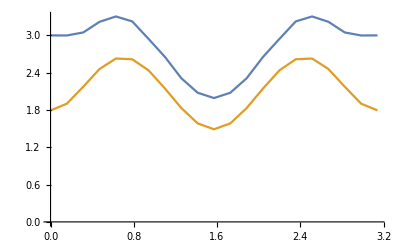

```mathematica
ListLinePlot[{altfibomax,altfibomean}]
```

## dt = pi/8 kick*after

#### data

```mathematica
kacdata={-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,6.406853007629834296*10^-16,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999556*10^+00,1.999999999999999778*10^+00,1.999999999999999556*10^+00,2.398404964790533445*10^+00,2.398404964790533889*10^+00,2.398404964790533445*10^+00,2.769031713829399166*10^+00,2.769031713829398278*10^+00,2.769031713829399166*10^+00,2.769031713829397834*10^+00,2.769031713829396502*10^+00,2.714859631909447568*10^+00,2.714859631909447124*10^+00,2.714859631909446236*10^+00,2.714859631909446680*10^+00,2.714859631909445792*10^+00,1.435539529221185884*10^+00,1.435539529221185884*10^+00,1.435539529221185884*10^+00,2.233308640386460375*10^+00,2.233308640386461263*10^+00,2.233308640386459931*10^+00,2.233308640386461263*10^+00,2.233308640386459931*10^+00,7.718119272934457209*10^-01,7.718119272934458319*10^-01,7.718119272934460540*10^-01,1.933919985966690014*10^+00,1.933919985966690236*10^+00,1.933919985966690014*10^+00,1.933919985966690458*10^+00,1.933919985966690014*10^+00,2.902430850435076426*10^+00,2.902430850435076426*10^+00,2.902430850435076870*10^+00,2.902430850435075982*10^+00,2.902430850435076426*10^+00,2.178579989840966125*10^+00,2.178579989840965681*10^+00,2.178579989840966125*10^+00,2.433453312579540118*10^+00,2.433453312579540562*10^+00,2.433453312579541006*10^+00,2.433453312579541006*10^+00,2.433453312579541006*10^+00,1.400990072477376502*10^+00,1.400990072477376280*10^+00,1.400990072477376502*10^+00,1.400990072477376946*10^+00,1.400990072477376946*10^+00,2.679406902378256738*10^+00,2.679406902378256294*10^+00,2.679406902378256738*10^+00,1.722609701733390786*10^+00,1.722609701733391230*10^+00,1.722609701733390342*10^+00,1.722609701733390786*10^+00,1.722609701733390342*10^+00,1.415230676244292329*10^+00,1.415230676244292329*10^+00,1.415230676244292551*10^+00,2.673177896994409330*10^+00,2.673177896994408442*10^+00,2.673177896994409330*10^+00,2.673177896994408886*10^+00,2.673177896994408442*10^+00,1.387353866375293121*10^+00,1.387353866375292899*10^+00,1.387353866375292899*10^+00,1.387353866375292233*10^+00,1.387353866375293121*10^+00,2.575570761327297120*10^+00,2.575570761327297120*10^+00,2.575570761327296232*10^+00,2.218833447415879068*10^+00,2.218833447415878624*10^+00,2.218833447415878624*10^+00,2.218833447415878624*10^+00,2.218833447415878624*10^+00,2.702570864545697837*10^+00,2.702570864545698281*10^+00,2.702570864545697837*10^+00,2.092037360349454644*10^+00,2.092037360349454200*10^+00,2.092037360349454644*10^+00,2.092037360349453756*10^+00,2.092037360349453756*10^+00,4.968739972006006589*10^-01,4.968739972006004924*10^-01,4.968739972006012695*10^-01,4.968739972006013805*10^-01,4.968739972006018246*10^-01,2.198464746884069676*10^+00,2.198464746884070564*10^+00,2.198464746884071008*10^+00,1.826770023126996323*10^+00,1.826770023126996545*10^+00,1.826770023126996545*10^+00,1.826770023126996545*10^+00,1.826770023126996545*10^+00,2.925662522169294011*10^+00,2.925662522169295343*10^+00,2.925662522169295343*10^+00,2.925662522169294011*10^+00,2.925662522169292679*10^+00,2.605726898388110335*10^+00,2.605726898388110779*10^+00,2.605726898388109447*10^+00,2.007194037888695881*10^+00,2.007194037888695881*10^+00,2.007194037888695437*10^+00,2.007194037888694993*10^+00,2.007194037888695881*10^+00,1.999254061534540217*10^+00,1.999254061534540217*10^+00,1.999254061534540661*10^+00,1.844735960542176201*10^-01,1.844735960542176756*10^-01,1.844735960542183140*10^-01,1.844735960542183140*10^-01,1.844735960542190634*10^-01,1.999421107032024247*10^+00,1.999421107032024025*10^+00,1.999421107032024025*10^+00,1.999421107032024025*10^+00,1.999421107032024025*10^+00,2.729826122051325132*10^+00,2.729826122051325132*10^+00,2.729826122051325576*10^+00,2.808173394369000597*10^+00,2.808173394368998821*10^+00,2.808173394369001041*10^+00,2.808173394368999709*10^+00,2.808173394368999265*10^+00,2.483938552184024040*10^+00,2.483938552184022264*10^+00,2.483938552184022264*10^+00,2.483938552184022708*10^+00,2.483938552184022708*10^+00,1.068074537881012365*10^+00,1.068074537881012365*10^+00,1.068074537881012587*10^+00,2.263681771907624540*10^+00,2.263681771907624984*10^+00,2.263681771907623208*10^+00,2.263681771907624096*10^+00,2.263681771907622764*10^+00,1.186696856282441370*10^+00,1.186696856282440482*10^+00,1.186696856282440926*10^+00,1.866997587585890628*10^+00,1.866997587585890184*10^+00,1.866997587585890406*10^+00,1.866997587585890406*10^+00,1.866997587585890406*10^+00,3.002516179531826257*10^+00,3.002516179531825813*10^+00,3.002516179531826701*10^+00,3.002516179531825813*10^+00,3.002516179531824481*10^+00,2.030430245852811399*10^+00,2.030430245852811399*10^+00,2.030430245852811399*10^+00,2.396587026803318476*10^+00,2.396587026803320253*10^+00,2.396587026803319809*10^+00,2.396587026803318921*10^+00,2.396587026803319365*10^+00,1.420291003422200049*10^+00,1.420291003422199827*10^+00,1.420291003422200271*10^+00,2.627186014353000587*10^+00,2.627186014352999699*10^+00,2.627186014352999255*10^+00,2.627186014352999699*10^+00,2.627186014352999699*10^+00,2.017632271969159952*10^+00,2.017632271969160396*10^+00,2.017632271969159952*10^+00,2.017632271969159952*10^+00,2.017632271969159952*10^+00,1.244404953586747409*10^+00,1.244404953586747409*10^+00,1.244404953586746965*10^+00,2.601229457673323253*10^+00,2.601229457673321921*10^+00,2.601229457673323253*10^+00,2.601229457673321033*10^+00,2.601229457673321477*10^+00,1.403902395746287279*10^+00,1.403902395746287501*10^+00,1.403902395746287723*10^+00,1.403902395746287723*10^+00,1.403902395746287501*10^+00,2.754631299512869447*10^+00,2.722912528242654327*10^-14,2.722912528242654327*10^-14,2.786981058318951437*10^-14,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,1.929680324037556183*10^+00,2.313263142520595839*10^+00,2.313263142517536508*10^+00,2.313263142520595839*10^+00,2.730518948053190176*10^+00,2.730518948053163086*10^+00,2.730518948053190176*10^+00,2.730518948053162198*10^+00,2.730518948053189732*10^+00,2.789036626813685249*10^+00,2.789036626814668018*10^+00,2.789036626813685693*10^+00,2.789036626814668463*10^+00,2.789036626813684805*10^+00,1.701407631308323287*10^+00,1.701407631308547330*10^+00,1.701407631308323509*10^+00,2.412834599386130208*10^+00,2.412834599385490275*10^+00,2.412834599386128875*10^+00,2.412834599385489387*10^+00,2.412834599386128431*10^+00,1.044462586568353668*10^+00,1.044462586568353224*10^+00,1.044462586568354112*10^+00,2.171570832422501596*10^+00,2.171570832422501152*10^+00,2.171570832422501152*10^+00,2.171570832422501596*10^+00,2.171570832422501596*10^+00,2.958942728122235799*10^+00,2.958942728122235799*10^+00,2.958942728122236687*10^+00,2.958942728122235799*10^+00,2.958942728122234911*10^+00,2.246227353048625197*10^+00,2.246227353048626085*10^+00,2.246227353048625197*10^+00,2.453702788819688507*10^+00,2.453702788819688507*10^+00,2.453702788819687619*10^+00,2.453702788819688507*10^+00,2.453702788819688507*10^+00,1.382954891766953409*10^+00,1.382954891766709604*10^+00,1.382954891766953631*10^+00,1.382954891766709160*10^+00,1.382954891766953631*10^+00,2.656917596923880520*10^+00,2.656917596923879632*10^+00,2.656917596923879632*10^+00,1.791855343775019538*10^+00,1.791855343775018650*10^+00,1.791855343775018206*10^+00,1.791855343775018872*10^+00,1.791855343775018206*10^+00,1.502375273674537270*10^+00,1.502375273674537492*10^+00,1.502375273674537270*10^+00,2.699517635325339171*10^+00,2.699517635325339615*10^+00,2.699517635325340503*10^+00,2.699517635325339171*10^+00,2.699517635325339171*10^+00,1.625306518838767644*10^+00,1.625306518838768310*10^+00,1.625306518838768532*10^+00,1.625306518838768755*10^+00,1.625306518838767644*10^+00,2.652243833172416299*10^+00,2.652243833172084120*10^+00,2.652243833172416299*10^+00,2.389742770165299124*10^+00,2.389742770165299568*10^+00,2.389742770165299124*10^+00,2.389742770165300012*10^+00,2.389742770165299568*10^+00,2.775393838154364801*10^+00,2.775393838154363024*10^+00,2.775393838154363912*10^+00,2.138719905872273230*10^+00,2.138719905872273674*10^+00,2.138719905872274119*10^+00,2.138719905872275007*10^+00,2.138719905872274119*10^+00,7.129045717913324864*10^-01,7.129045717913320424*10^-01,7.129045717913327085*10^-01,7.129045717913325975*10^-01,7.129045717913332636*10^-01,2.236821356533949867*10^+00,2.236821356533949867*10^+00,2.236821356533949867*10^+00,1.799161327721169101*10^+00,1.799161327721714887*10^+00,1.799161327721168657*10^+00,1.799161327721715775*10^+00,1.799161327721169323*10^+00,2.920815159437148534*10^+00,2.920815159437149422*10^+00,2.920815159437148534*10^+00,2.920815159437147646*10^+00,2.920815159437147202*10^+00,2.689940339995415819*10^+00,2.689940339995064544*10^+00,2.689940339995416263*10^+00,2.151618801857873464*10^+00,2.151618801857873908*10^+00,2.151618801857874796*10^+00,2.151618801857873908*10^+00,2.151618801857873464*10^+00,2.193753709454867806*10^+00,2.193753709454868250*10^+00,2.193753709454867806*10^+00,4.871754794725694504*10^-01,4.871754794725688953*10^-01,4.871754794725701165*10^-01,4.871754794725700055*10^-01,4.871754794725704496*10^-01,2.161055859966437342*10^+00,2.161055859966411585*10^+00,2.161055859966436454*10^+00,2.161055859966411141*10^+00,2.161055859966436898*10^+00,2.790172936891471167*10^+00,2.790172936891470279*10^+00,2.790172936891470279*10^+00,2.813292509331701385*10^+00,2.813292509331701829*10^+00,2.813292509331700941*10^+00,2.813292509331701829*10^+00,2.813292509331700941*10^+00,2.516080214014136729*10^+00,2.516080214014137617*10^+00,2.516080214014135841*10^+00,2.516080214014136285*10^+00,2.516080214014136285*10^+00,1.164649625002724953*10^+00,1.164649625002724509*10^+00,1.164649625002725175*10^+00,2.228568316746525113*10^+00,2.228568316746524669*10^+00,2.228568316746525113*10^+00,2.228568316746525113*10^+00,2.228568316746524669*10^+00,1.126138747952987629*10^+00,1.126138747952934338*10^+00,1.126138747952987851*10^+00,1.923633082074848399*10^+00,1.923633082074848399*10^+00,1.923633082074847955*10^+00,1.923633082074848843*10^+00,1.923633082074848399*10^+00,2.952682065777427756*10^+00,2.952682065776547127*10^+00,2.952682065777428200*10^+00,2.952682065776548015*10^+00,2.952682065777427312*10^+00,2.069371797098563892*10^+00,2.069371797098563448*10^+00,2.069371797098564336*10^+00,2.532398613989863989*10^+00,2.532398613989864433*10^+00,2.532398613989863101*10^+00,2.532398613989863545*10^+00,2.532398613989863989*10^+00,1.672161577425778756*10^+00,1.672161577425779422*10^+00,1.672161577425779200*10^+00,2.729933439071615009*10^+00,2.729933439071736245*10^+00,2.729933439071615009*10^+00,2.729933439071735801*10^+00,2.729933439071614121*10^+00,2.145098781095581941*10^+00,2.145098781095581941*10^+00,2.145098781095581053*10^+00,2.145098781095581053*10^+00,2.145098781095581941*10^+00,1.492065374416558621*10^+00,1.492065374416559065*10^+00,1.492065374416558399*10^+00,2.629930109922146819*10^+00,2.629930109922146819*10^+00,2.629930109922146819*10^+00,2.629930109922146819*10^+00,2.629930109922145931*10^+00,1.503385562441609924*10^+00,1.503385562441610146*10^+00,1.503385562441610368*10^+00,1.503385562441609702*10^+00,1.503385562441609924*10^+00,2.742106986095483201*10^+00,-9.610279511444755881*10^-16,-9.610279511444755881*10^-16,-3.203426503814917641*10^-16,1.729030204872844978*10^+00,1.729030204872845200*10^+00,1.729030204872845200*10^+00,1.729030204872845200*10^+00,1.729030204872844978*10^+00,2.086752672442497847*10^+00,2.086752672442497847*10^+00,2.086752672442498291*10^+00,2.623295501941305563*10^+00,2.623295501941305563*10^+00,2.623295501941306007*10^+00,2.623295501941305563*10^+00,2.623295501941305119*10^+00,2.951731397072169472*10^+00,2.951731397072169472*10^+00,2.951731397072168583*10^+00,2.951731397072168139*10^+00,2.951731397072169472*10^+00,2.189887390241047171*10^+00,2.189887390241047616*10^+00,2.189887390241046283*10^+00,2.650390234175481474*10^+00,2.650390234175481918*10^+00,2.650390234175481474*10^+00,2.650390234175481474*10^+00,2.650390234175481030*10^+00,1.550539290566950168*10^+00,1.550539290566950390*10^+00,1.550539290566951056*10^+00,2.528197185926182478*10^+00,2.528197185926183366*10^+00,2.528197185926183366*10^+00,2.528197185926182922*10^+00,2.528197185926182033*10^+00,3.082535298242651933*10^+00,3.082535298242651489*10^+00,3.082535298242650157*10^+00,3.082535298242651045*10^+00,3.082535298242651045*10^+00,2.407993177612609781*10^+00,2.407993177612610225*10^+00,2.407993177612609781*10^+00,2.487138340598175734*10^+00,2.487138340598175290*10^+00,2.487138340598175734*10^+00,2.487138340598175734*10^+00,2.487138340598174846*10^+00,1.347143967894838923*10^+00,1.347143967894839145*10^+00,1.347143967894838923*10^+00,1.347143967894838923*10^+00,1.347143967894839145*10^+00,2.575023699064790783*10^+00,2.575023699064790783*10^+00,2.575023699064790339*10^+00,1.916511393596764590*10^+00,1.916511393596764812*10^+00,1.916511393596765256*10^+00,1.916511393596764812*10^+00,1.916511393596765478*10^+00,1.718284573384435632*10^+00,1.718284573384435632*10^+00,1.718284573384436520*10^+00,2.751353602365845141*10^+00,2.751353602365846029*10^+00,2.751353602365845585*10^+00,2.751353602365845585*10^+00,2.751353602365846029*10^+00,2.042597030874220287*10^+00,2.042597030874220732*10^+00,2.042597030874219843*10^+00,2.042597030874219843*10^+00,2.042597030874219843*10^+00,2.772108065906021324*10^+00,2.772108065906020880*10^+00,2.772108065906021324*10^+00,2.714194589100657584*10^+00,2.714194589100658472*10^+00,2.714194589100658028*10^+00,2.714194589100657140*10^+00,2.714194589100657140*10^+00,2.881078275021539792*10^+00,2.881078275021540236*10^+00,2.881078275021538460*10^+00,2.288612210738376174*10^+00,2.288612210738376618*10^+00,2.288612210738375286*10^+00,2.288612210738375730*10^+00,2.288612210738376174*10^+00,1.176111993575198467*10^+00,1.176111993575198689*10^+00,1.176111993575199133*10^+00,1.176111993575198911*10^+00,1.176111993575198911*10^+00,2.301647582195795572*10^+00,2.301647582195795572*10^+00,2.301647582195793795*10^+00,1.739838652441527467*10^+00,1.739838652441527245*10^+00,1.739838652441527467*10^+00,1.739838652441528133*10^+00,1.739838652441527245*10^+00,2.925084784069626131*10^+00,2.925084784069627908*10^+00,2.925084784069625243*10^+00,2.925084784069627020*10^+00,2.925084784069625687*10^+00,2.824194965819665448*10^+00,2.824194965819665892*10^+00,2.824194965819665004*10^+00,2.461754548796920794*10^+00,2.461754548796920350*10^+00,2.461754548796920350*10^+00,2.461754548796919018*10^+00,2.461754548796920350*10^+00,2.526368715890622063*10^+00,2.526368715890622951*10^+00,2.526368715890622063*10^+00,1.057445583616316132*10^+00,1.057445583616316354*10^+00,1.057445583616316354*10^+00,1.057445583616316576*10^+00,1.057445583616317020*10^+00,2.354849403548748832*10^+00,2.354849403548748832*10^+00,2.354849403548747944*10^+00,2.354849403548748832*10^+00,2.354849403548748388*10^+00,2.894078967453284523*10^+00,2.894078967453286300*10^+00,2.894078967453285411*10^+00,2.836579119598638510*10^+00,2.836579119598638066*10^+00,2.836579119598638066*10^+00,2.836579119598638510*10^+00,2.836579119598637622*10^+00,2.573455156098276131*10^+00,2.573455156098274799*10^+00,2.573455156098274799*10^+00,2.573455156098275243*10^+00,2.573455156098274799*10^+00,1.385950649194991779*10^+00,1.385950649194992002*10^+00,1.385950649194992446*10^+00,2.128821029609814897*10^+00,2.128821029609814897*10^+00,2.128821029609814897*10^+00,2.128821029609814452*10^+00,2.128821029609813564*10^+00,1.079555943892589021*10^+00,1.079555943892587910*10^+00,1.079555943892588354*10^+00,2.034578768387317993*10^+00,2.034578768387317549*10^+00,2.034578768387316661*10^+00,2.034578768387317105*10^+00,2.034578768387317549*10^+00,2.835960379197075554*10^+00,2.835960379197075998*10^+00,2.835960379197074666*10^+00,2.835960379197074666*10^+00,2.835960379197075554*10^+00,2.193756783751362960*10^+00,2.193756783751363404*10^+00,2.193756783751362960*10^+00,2.808956479406498286*10^+00,2.808956479406497841*10^+00,2.808956479406497397*10^+00,2.808956479406497841*10^+00,2.808956479406498730*10^+00,2.155329277973505597*10^+00,2.155329277973506041*10^+00,2.155329277973505597*10^+00,2.861155154649887677*10^+00,2.861155154649887677*10^+00,2.861155154649886789*10^+00,2.861155154649886789*10^+00,2.861155154649886789*10^+00,2.410436925248653939*10^+00,2.410436925248653495*10^+00,2.410436925248653939*10^+00,2.410436925248653051*10^+00,2.410436925248652607*10^+00,1.922963075209594308*10^+00,1.922963075209594530*10^+00,1.922963075209594974*10^+00,2.672749011207997238*10^+00,2.672749011207996350*10^+00,2.672749011207995462*10^+00,2.672749011207994574*10^+00,2.672749011207995906*10^+00,1.717772811871536076*10^+00,1.717772811871535854*10^+00,1.717772811871536298*10^+00,1.717772811871536076*10^+00,1.717772811871536520*10^+00,2.716167182513950618*10^+00,9.610279511444749964*10^-16,1.121199276335220928*10^-15,1.761884577098203667*10^-15,1.427593131110274527*10^+00,1.427593131110274527*10^+00,1.427593131110274527*10^+00,1.427593131110274305*10^+00,1.427593131110274527*10^+00,1.785373400151494039*10^+00,1.785373400151494705*10^+00,1.785373400151494483*10^+00,2.496478558615756516*10^+00,2.496478558615756960*10^+00,2.496478558615756960*10^+00,2.496478558615756960*10^+00,2.496478558615756516*10^+00,3.012427033137292653*10^+00,3.012427033137293098*10^+00,3.012427033137292653*10^+00,3.012427033137293542*10^+00,3.012427033137291765*10^+00,2.566584589342637557*10^+00,2.566584589342637557*10^+00,2.566584589342637557*10^+00,2.732484280283312916*10^+00,2.732484280283313804*10^+00,2.732484280283313804*10^+00,2.732484280283313360*10^+00,2.732484280283312916*10^+00,2.014729917315053687*10^+00,2.014729917315054131*10^+00,2.014729917315054131*10^+00,2.765849000025148996*10^+00,2.765849000025148552*10^+00,2.765849000025148552*10^+00,2.765849000025148108*10^+00,2.765849000025147664*10^+00,3.175639767568170235*10^+00,3.175639767568170235*10^+00,3.175639767568170235*10^+00,3.175639767568169347*10^+00,3.175639767568168459*10^+00,2.559382208685735183*10^+00,2.559382208685735183*10^+00,2.559382208685734739*10^+00,2.474311444310002717*10^+00,2.474311444310003161*10^+00,2.474311444310002273*10^+00,2.474311444310002717*10^+00,2.474311444310002273*10^+00,1.310419259506976353*10^+00,1.310419259506976797*10^+00,1.310419259506976797*10^+00,1.310419259506977463*10^+00,1.310419259506976797*10^+00,2.399654622988769859*10^+00,2.399654622988770747*10^+00,2.399654622988770747*10^+00,2.027871783350966073*10^+00,2.027871783350965185*10^+00,2.027871783350965185*10^+00,2.027871783350964741*10^+00,2.027871783350964741*10^+00,1.911162576415265768*10^+00,1.911162576415266212*10^+00,1.911162576415266212*10^+00,2.700704585813535452*10^+00,2.700704585813536340*10^+00,2.700704585813535896*10^+00,2.700704585813535896*10^+00,2.700704585813535452*10^+00,2.375645293376740241*10^+00,2.375645293376739353*10^+00,2.375645293376739353*10^+00,2.375645293376739353*10^+00,2.375645293376739353*10^+00,2.797849965835851105*10^+00,2.797849965835851549*10^+00,2.797849965835850661*10^+00,2.909588163048152154*10^+00,2.909588163048153042*10^+00,2.909588163048153042*10^+00,2.909588163048153042*10^+00,2.909588163048153042*10^+00,2.909468894895655300*10^+00,2.909468894895654856*10^+00,2.909468894895655300*10^+00,2.487840781631440290*10^+00,2.487840781631440290*10^+00,2.487840781631440734*10^+00,2.487840781631440290*10^+00,2.487840781631439402*10^+00,1.603471529935903472*10^+00,1.603471529935902806*10^+00,1.603471529935902806*10^+00,1.603471529935902806*10^+00,1.603471529935902584*10^+00,2.289909391568078156*10^+00,2.289909391568078156*10^+00,2.289909391568077268*10^+00,1.727493880931954662*10^+00,1.727493880931953774*10^+00,1.727493880931953552*10^+00,1.727493880931953329*10^+00,1.727493880931954440*10^+00,2.903909994652856152*10^+00,2.903909994652855264*10^+00,2.903909994652855264*10^+00,2.903909994652854820*10^+00,2.903909994652854820*10^+00,2.902122166294205385*10^+00,2.902122166294206274*10^+00,2.902122166294205385*10^+00,2.728598058714150287*10^+00,2.728598058714150731*10^+00,2.728598058714149843*10^+00,2.728598058714149843*10^+00,2.728598058714148955*10^+00,2.745232565058014274*10^+00,2.745232565058014274*10^+00,2.745232565058013385*10^+00,1.632326672952940871*10^+00,1.632326672952940871*10^+00,1.632326672952941538*10^+00,1.632326672952940871*10^+00,1.632326672952941093*10^+00,2.453767482192703575*10^+00,2.453767482192703575*10^+00,2.453767482192703131*10^+00,2.453767482192702687*10^+00,2.453767482192702687*10^+00,2.899622864070799722*10^+00,2.899622864070798389*10^+00,2.899622864070798833*10^+00,2.845310178048547023*10^+00,2.845310178048547911*10^+00,2.845310178048547023*10^+00,2.845310178048547023*10^+00,2.845310178048547023*10^+00,2.605530285675374813*10^+00,2.605530285675373037*10^+00,2.605530285675373481*10^+00,2.605530285675373481*10^+00,2.605530285675373481*10^+00,1.581052384569976432*10^+00,1.581052384569976432*10^+00,1.581052384569976432*10^+00,2.000913717058828922*10^+00,2.000913717058828922*10^+00,2.000913717058828034*10^+00,2.000913717058828034*10^+00,2.000913717058828478*10^+00,1.079382234459101975*10^+00,1.079382234459101975*10^+00,1.079382234459102419*10^+00,2.053360701768881302*10^+00,2.053360701768881746*10^+00,2.053360701768881302*10^+00,2.053360701768880858*10^+00,2.053360701768880858*10^+00,2.675169804270158380*10^+00,2.675169804270157936*10^+00,2.675169804270157492*10^+00,2.675169804270158380*10^+00,2.675169804270157492*10^+00,2.406951545639988588*10^+00,2.406951545639988588*10^+00,2.406951545639988144*10^+00,2.997824195721144669*10^+00,2.997824195721145113*10^+00,2.997824195721146001*10^+00,2.997824195721145113*10^+00,2.997824195721145113*10^+00,2.556550308035785868*10^+00,2.556550308035785424*10^+00,2.556550308035784980*10^+00,2.876903602891146328*10^+00,2.876903602891146328*10^+00,2.876903602891147660*10^+00,2.876903602891146772*10^+00,2.876903602891146772*10^+00,2.605869883051894931*10^+00,2.605869883051894487*10^+00,2.605869883051895375*10^+00,2.605869883051894931*10^+00,2.605869883051894043*10^+00,2.300617474970763521*10^+00,2.300617474970763521*10^+00,2.300617474970763521*10^+00,2.703941522240321138*10^+00,2.703941522240322470*10^+00,2.703941522240322026*10^+00,2.703941522240321582*10^+00,2.703941522240321138*10^+00,1.950792997469961598*10^+00,1.950792997469962264*10^+00,1.950792997469961820*10^+00,1.950792997469962264*10^+00,1.950792997469961376*10^+00,2.659287123303549549*10^+00,4.805139755722374982*10^-16,9.610279511444749964*10^-16,1.281370601525966465*10^-15,1.070009614893122851*10^+00,1.070009614893122851*10^+00,1.070009614893122851*10^+00,1.070009614893122629*10^+00,1.070009614893122851*10^+00,1.499957157121726725*10^+00,1.499957157121726503*10^+00,1.499957157121726503*10^+00,2.360855972646967782*10^+00,2.360855972646968226*10^+00,2.360855972646967782*10^+00,2.360855972646967782*10^+00,2.360855972646967338*10^+00,2.931801281313386909*10^+00,2.931801281313386021*10^+00,2.931801281313386909*10^+00,2.931801281313386021*10^+00,2.931801281313386465*10^+00,2.718714751413589426*10^+00,2.718714751413589426*10^+00,2.718714751413589426*10^+00,2.667827073000229809*10^+00,2.667827073000230254*10^+00,2.667827073000229365*10^+00,2.667827073000229365*10^+00,2.667827073000230254*10^+00,2.288901111468521599*10^+00,2.288901111468521599*10^+00,2.288901111468521599*10^+00,2.835171511632330166*10^+00,2.835171511632331054*10^+00,2.835171511632330166*10^+00,2.835171511632331054*10^+00,2.835171511632329278*10^+00,3.153499291744437549*10^+00,3.153499291744437105*10^+00,3.153499291744436661*10^+00,3.153499291744437105*10^+00,3.153499291744436217*10^+00,2.591888864643966617*10^+00,2.591888864643967061*10^+00,2.591888864643967505*10^+00,2.345537335228833342*10^+00,2.345537335228833786*10^+00,2.345537335228833342*10^+00,2.345537335228833342*10^+00,2.345537335228833786*10^+00,1.264221768258349421*10^+00,1.264221768258350309*10^+00,1.264221768258349421*10^+00,1.264221768258350309*10^+00,1.264221768258349865*10^+00,2.107022153898951089*10^+00,2.107022153898950645*10^+00,2.107022153898951089*10^+00,2.000547934221074353*10^+00,2.000547934221074353*10^+00,2.000547934221074797*10^+00,2.000547934221075685*10^+00,2.000547934221074353*10^+00,1.985444633424165994*10^+00,1.985444633424165994*10^+00,1.985444633424165772*10^+00,2.538075733149928404*10^+00,2.538075733149928404*10^+00,2.538075733149928404*10^+00,2.538075733149928848*10^+00,2.538075733149927515*10^+00,2.546277234276270285*10^+00,2.546277234276270285*10^+00,2.546277234276269841*10^+00,2.546277234276270285*10^+00,2.546277234276270729*10^+00,2.728717342036386384*10^+00,2.728717342036386384*10^+00,2.728717342036386828*10^+00,2.896302278169399891*10^+00,2.896302278169399891*10^+00,2.896302278169399447*10^+00,2.896302278169399003*10^+00,2.896302278169399003*10^+00,2.838087711159260174*10^+00,2.838087711159260174*10^+00,2.838087711159259729*10^+00,2.604888693009739686*10^+00,2.604888693009740130*10^+00,2.604888693009739242*10^+00,2.604888693009739686*10^+00,2.604888693009739242*10^+00,1.846443747103268418*10^+00,1.846443747103268418*10^+00,1.846443747103268196*10^+00,1.846443747103267974*10^+00,1.846443747103268196*10^+00,2.154133801985363306*10^+00,2.154133801985364194*10^+00,2.154133801985363750*10^+00,1.689850569601155872*10^+00,1.689850569601156760*10^+00,1.689850569601155428*10^+00,1.689850569601156316*10^+00,1.689850569601155428*10^+00,2.743703071180504161*10^+00,2.743703071180504605*10^+00,2.743703071180504605*10^+00,2.743703071180503272*10^+00,2.743703071180503716*10^+00,2.830227532307057370*10^+00,2.830227532307056926*10^+00,2.830227532307056482*10^+00,2.810010986281945122*10^+00,2.810010986281946010*10^+00,2.810010986281944234*10^+00,2.810010986281945122*10^+00,2.810010986281943790*10^+00,2.792714442468017921*10^+00,2.792714442468018365*10^+00,2.792714442468017477*10^+00,2.027482272677010755*10^+00,2.027482272677010755*10^+00,2.027482272677010755*10^+00,2.027482272677010755*10^+00,2.027482272677010755*10^+00,2.400619796179015886*10^+00,2.400619796179014998*10^+00,2.400619796179015886*10^+00,2.400619796179015442*10^+00,2.400619796179015442*10^+00,2.774431505650247765*10^+00,2.774431505650247765*10^+00,2.774431505650247765*10^+00,2.838099398311308530*10^+00,2.838099398311308086*10^+00,2.838099398311308086*10^+00,2.838099398311307642*10^+00,2.838099398311307642*10^+00,2.568747837687174407*10^+00,2.568747837687173963*10^+00,2.568747837687173519*10^+00,2.568747837687173963*10^+00,2.568747837687173075*10^+00,1.642680111409501542*10^+00,1.642680111409501542*10^+00,1.642680111409501320*10^+00,1.841065229454312169*10^+00,1.841065229454312835*10^+00,1.841065229454312613*10^+00,1.841065229454312835*10^+00,1.841065229454312835*10^+00,1.099860629553248925*10^+00,1.099860629553248703*10^+00,1.099860629553247815*10^+00,1.935536662816244702*10^+00,1.935536662816244702*10^+00,1.935536662816244480*10^+00,1.935536662816244480*10^+00,1.935536662816244036*10^+00,2.456292541162976129*10^+00,2.456292541162976129*10^+00,2.456292541162975240*10^+00,2.456292541162975240*10^+00,2.456292541162975240*10^+00,2.546325410981787662*10^+00,2.546325410981786774*10^+00,2.546325410981787662*10^+00,3.025813354290422197*10^+00,3.025813354290422641*10^+00,3.025813354290422197*10^+00,3.025813354290422641*10^+00,3.025813354290421309*10^+00,2.746190623197819924*10^+00,2.746190623197819036*10^+00,2.746190623197818148*10^+00,2.759057609216389206*10^+00,2.759057609216389650*10^+00,2.759057609216389206*10^+00,2.759057609216389206*10^+00,2.759057609216388762*10^+00,2.656298070209301088*10^+00,2.656298070209300199*10^+00,2.656298070209300199*10^+00,2.656298070209300199*10^+00,2.656298070209300199*10^+00,2.515465525204353625*10^+00,2.515465525204354513*10^+00,2.515465525204353625*10^+00,2.681193411067661625*10^+00,2.681193411067661181*10^+00,2.681193411067660293*10^+00,2.681193411067661181*10^+00,2.681193411067661181*10^+00,2.107302641489057216*10^+00,2.107302641489058104*10^+00,2.107302641489058104*10^+00,2.107302641489057660*10^+00,2.107302641489058104*10^+00,2.543235054936579864*10^+00,3.203426503814917641*10^-16,-0.000000000000000000*10^+00,8.008566259537291637*10^-16,7.091578053305405138*10^-01,7.091578053305397367*10^-01,7.091578053305406248*10^-01,7.091578053305399587*10^-01,7.091578053305402918*10^-01,1.263977579813405638*10^+00,1.263977579813406082*10^+00,1.263977579813405860*10^+00,2.197668167360890212*10^+00,2.197668167360890212*10^+00,2.197668167360890656*10^+00,2.197668167360890656*10^+00,2.197668167360889768*10^+00,2.712922859740126036*10^+00,2.712922859740125592*10^+00,2.712922859740126036*10^+00,2.712922859740126480*10^+00,2.712922859740125592*10^+00,2.691891665685864687*10^+00,2.691891665685863799*10^+00,2.691891665685865132*10^+00,2.493219857097726422*10^+00,2.493219857097725978*10^+00,2.493219857097725978*10^+00,2.493219857097725534*10^+00,2.493219857097725534*10^+00,2.327991126339306938*10^+00,2.327991126339306938*10^+00,2.327991126339306494*10^+00,2.722107380663382425*10^+00,2.722107380663383314*10^+00,2.722107380663382425*10^+00,2.722107380663381981*10^+00,2.722107380663381537*10^+00,2.970352838669629847*10^+00,2.970352838669628959*10^+00,2.970352838669629847*10^+00,2.970352838669630291*10^+00,2.970352838669629403*10^+00,2.446172392057674561*10^+00,2.446172392057673672*10^+00,2.446172392057673672*10^+00,2.092111488788941376*10^+00,2.092111488788942264*10^+00,2.092111488788942708*10^+00,2.092111488788941820*10^+00,2.092111488788941376*10^+00,1.145292166638187226*10^+00,1.145292166638187670*10^+00,1.145292166638187004*10^+00,1.145292166638188114*10^+00,1.145292166638187226*10^+00,1.709960154377054398*10^+00,1.709960154377055286*10^+00,1.709960154377053732*10^+00,1.855179544853162721*10^+00,1.855179544853162721*10^+00,1.855179544853163165*10^+00,1.855179544853163165*10^+00,1.855179544853162721*10^+00,1.903232160666294970*10^+00,1.903232160666295192*10^+00,1.903232160666293638*10^+00,2.288799411174159637*10^+00,2.288799411174160525*10^+00,2.288799411174159193*10^+00,2.288799411174159193*10^+00,2.288799411174159193*10^+00,2.537678581702460079*10^+00,2.537678581702460079*10^+00,2.537678581702459191*10^+00,2.537678581702460079*10^+00,2.537678581702460523*10^+00,2.562235124219775173*10^+00,2.562235124219775173*10^+00,2.562235124219774729*10^+00,2.700480317814182740*10^+00,2.700480317814182740*10^+00,2.700480317814182296*10^+00,2.700480317814182740*10^+00,2.700480317814182740*10^+00,2.693626129870437591*10^+00,2.693626129870438035*10^+00,2.693626129870438035*10^+00,2.559652716737784939*10^+00,2.559652716737784495*10^+00,2.559652716737784495*10^+00,2.559652716737783607*10^+00,2.559652716737783162*10^+00,1.872085011627393492*10^+00,1.872085011627393047*10^+00,1.872085011627392825*10^+00,1.872085011627392825*10^+00,1.872085011627392825*10^+00,1.906668056525262722*10^+00,1.906668056525262944*10^+00,1.906668056525262056*10^+00,1.596088382920609838*10^+00,1.596088382920609616*10^+00,1.596088382920610282*10^+00,1.596088382920610060*10^+00,1.596088382920610282*10^+00,2.406101238138755871*10^+00,2.406101238138756315*10^+00,2.406101238138755871*10^+00,2.406101238138756759*10^+00,2.406101238138755871*10^+00,2.608335369099126222*10^+00,2.608335369099125778*10^+00,2.608335369099126666*10^+00,2.697054592014026753*10^+00,2.697054592014027641*10^+00,2.697054592014026753*10^+00,2.697054592014026753*10^+00,2.697054592014025864*10^+00,2.666971404755071884*10^+00,2.666971404755071440*10^+00,2.666971404755071440*10^+00,2.196743258165471779*10^+00,2.196743258165471779*10^+00,2.196743258165471779*10^+00,2.196743258165470891*10^+00,2.196743258165470891*10^+00,2.231037394415198882*10^+00,2.231037394415199326*10^+00,2.231037394415198882*10^+00,2.231037394415198882*10^+00,2.231037394415198438*10^+00,2.537207511667291637*10^+00,2.537207511667291193*10^+00,2.537207511667291193*10^+00,2.737166342939937103*10^+00,2.737166342939937103*10^+00,2.737166342939936214*10^+00,2.737166342939936214*10^+00,2.737166342939936214*10^+00,2.424131030520373375*10^+00,2.424131030520375152*10^+00,2.424131030520373820*10^+00,2.424131030520374264*10^+00,2.424131030520373820*10^+00,1.579834965808476044*10^+00,1.579834965808476266*10^+00,1.579834965808475822*10^+00,1.647197621804001644*10^+00,1.647197621804001200*10^+00,1.647197621804001422*10^+00,1.647197621804001422*10^+00,1.647197621804001200*10^+00,1.070307021802418657*10^+00,1.070307021802418213*10^+00,1.070307021802418657*10^+00,1.670578050947828519*10^+00,1.670578050947828741*10^+00,1.670578050947828963*10^+00,1.670578050947828741*10^+00,1.670578050947829185*10^+00,2.205705824296714912*10^+00,2.205705824296714912*10^+00,2.205705824296713580*10^+00,2.205705824296713580*10^+00,2.205705824296714024*10^+00,2.526045075878352364*10^+00,2.526045075878352364*10^+00,2.526045075878352364*10^+00,2.864297377269812817*10^+00,2.864297377269813705*10^+00,2.864297377269812372*10^+00,2.864297377269812372*10^+00,2.864297377269812372*10^+00,2.709317370949862358*10^+00,2.709317370949862358*10^+00,2.709317370949861914*10^+00,2.565683568614903987*10^+00,2.565683568614903987*10^+00,2.565683568614903098*10^+00,2.565683568614903542*10^+00,2.565683568614903098*10^+00,2.550881589547895789*10^+00,2.550881589547896233*10^+00,2.550881589547896677*10^+00,2.550881589547896233*10^+00,2.550881589547896233*10^+00,2.521155062917695311*10^+00,2.521155062917695311*10^+00,2.521155062917694867*10^+00,2.556001451115192058*10^+00,2.556001451115193390*10^+00,2.556001451115192058*10^+00,2.556001451115192058*10^+00,2.556001451115191614*10^+00,2.128223300412027008*10^+00,2.128223300412027008*10^+00,2.128223300412027008*10^+00,2.128223300412027452*10^+00,2.128223300412026564*10^+00,2.327322375951021538*10^+00,-9.610279511444755881*10^-16,-9.610279511444755881*10^-16,-0.000000000000000000*10^+00,3.871470010700654996*10^-01,3.871470010700658326*10^-01,3.871470010700659992*10^-01,3.871470010700657216*10^-01,3.871470010700657216*10^-01,1.145892345322474970*10^+00,1.145892345322475636*10^+00,1.145892345322475636*10^+00,1.949680243014676684*10^+00,1.949680243014676240*10^+00,1.949680243014676240*10^+00,1.949680243014675574*10^+00,1.949680243014675796*10^+00,2.399256549285693652*10^+00,2.399256549285692763*10^+00,2.399256549285692763*10^+00,2.399256549285691875*10^+00,2.399256549285692763*10^+00,2.523588383257818535*10^+00,2.523588383257818091*10^+00,2.523588383257818535*10^+00,2.239933679857668114*10^+00,2.239933679857666782*10^+00,2.239933679857666338*10^+00,2.239933679857666782*10^+00,2.239933679857666338*10^+00,2.173750699918751472*10^+00,2.173750699918750584*10^+00,2.173750699918750584*10^+00,2.466981089486227408*10^+00,2.466981089486227408*10^+00,2.466981089486226519*10^+00,2.466981089486226519*10^+00,2.466981089486226519*10^+00,2.646941220231686209*10^+00,2.646941220231686209*10^+00,2.646941220231686209*10^+00,2.646941220231686209*10^+00,2.646941220231686209*10^+00,2.170062503075414817*10^+00,2.170062503075413929*10^+00,2.170062503075413929*10^+00,1.748800915521205424*10^+00,1.748800915521204757*10^+00,1.748800915521204757*10^+00,1.748800915521204757*10^+00,1.748800915521204313*10^+00,9.804235909519185554*10^-01,9.804235909519187775*10^-01,9.804235909519187775*10^-01,9.804235909519185554*10^-01,9.804235909519186665*10^-01,1.282044085378725606*10^+00,1.282044085378725828*10^+00,1.282044085378725384*10^+00,1.637337359500873113*10^+00,1.637337359500872003*10^+00,1.637337359500872891*10^+00,1.637337359500873113*10^+00,1.637337359500873113*10^+00,1.704167757600965727*10^+00,1.704167757600965061*10^+00,1.704167757600964617*10^+00,1.999919378539932957*10^+00,1.999919378539932957*10^+00,1.999919378539932069*10^+00,1.999919378539933179*10^+00,1.999919378539933623*10^+00,2.389409093885217938*10^+00,2.389409093885218383*10^+00,2.389409093885218383*10^+00,2.389409093885217938*10^+00,2.389409093885217938*10^+00,2.322131430119906970*10^+00,2.322131430119907414*10^+00,2.322131430119907414*10^+00,2.408503948681621765*10^+00,2.408503948681622653*10^+00,2.408503948681620432*10^+00,2.408503948681621765*10^+00,2.408503948681620876*10^+00,2.471019954848674427*10^+00,2.471019954848674871*10^+00,2.471019954848674871*10^+00,2.341407355351674990*10^+00,2.341407355351674546*10^+00,2.341407355351674546*10^+00,2.341407355351673658*10^+00,2.341407355351673658*10^+00,1.717191059656721919*10^+00,1.717191059656722141*10^+00,1.717191059656721697*10^+00,1.717191059656721919*10^+00,1.717191059656722363*10^+00,1.606594049045700912*10^+00,1.606594049045700467*10^+00,1.606594049045700245*10^+00,1.413601758498692629*10^+00,1.413601758498692629*10^+00,1.413601758498692185*10^+00,1.413601758498692629*10^+00,1.413601758498692629*10^+00,1.930206534998663237*10^+00,1.930206534998664791*10^+00,1.930206534998663237*10^+00,1.930206534998663237*10^+00,1.930206534998663237*10^+00,2.269098700405862257*10^+00,2.269098700405863589*10^+00,2.269098700405862701*10^+00,2.415508768604423651*10^+00,2.415508768604424539*10^+00,2.415508768604424539*10^+00,2.415508768604422762*10^+00,2.415508768604423651*10^+00,2.403711221037573509*10^+00,2.403711221037573509*10^+00,2.403711221037573065*10^+00,2.137646680819051959*10^+00,2.137646680819051959*10^+00,2.137646680819051959*10^+00,2.137646680819051515*10^+00,2.137646680819051070*10^+00,1.978615608078555077*10^+00,1.978615608078554633*10^+00,1.978615608078554189*10^+00,1.978615608078554189*10^+00,1.978615608078553745*10^+00,2.261278536422712371*10^+00,2.261278536422712371*10^+00,2.261278536422712371*10^+00,2.534610293119359259*10^+00,2.534610293119359259*10^+00,2.534610293119358371*10^+00,2.534610293119358815*10^+00,2.534610293119358371*10^+00,2.160332912240768177*10^+00,2.160332912240768177*10^+00,2.160332912240767733*10^+00,2.160332912240768177*10^+00,2.160332912240768177*10^+00,1.453830932104624774*10^+00,1.453830932104625218*10^+00,1.453830932104624551*10^+00,1.425332257533951319*10^+00,1.425332257533951541*10^+00,1.425332257533951097*10^+00,1.425332257533951319*10^+00,1.425332257533950653*10^+00,9.838823108768749437*10^-01,9.838823108768744996*10^-01,9.838823108768754988*10^-01,1.334513824871834009*10^+00,1.334513824871834675*10^+00,1.334513824871833343*10^+00,1.334513824871834231*10^+00,1.334513824871834453*10^+00,1.920019807213778851*10^+00,1.920019807213779073*10^+00,1.920019807213778851*10^+00,1.920019807213778851*10^+00,1.920019807213777963*10^+00,2.334640142890728853*10^+00,2.334640142890729297*10^+00,2.334640142890728853*10^+00,2.560370180474606627*10^+00,2.560370180474606627*10^+00,2.560370180474605739*10^+00,2.560370180474606627*10^+00,2.560370180474605739*10^+00,2.502979996400860774*10^+00,2.502979996400859886*10^+00,2.502979996400859442*10^+00,2.286016505791220510*10^+00,2.286016505791220510*10^+00,2.286016505791219622*10^+00,2.286016505791219622*10^+00,2.286016505791219622*10^+00,2.315887897042649524*10^+00,2.315887897042649080*10^+00,2.315887897042648635*10^+00,2.315887897042648191*10^+00,2.315887897042648191*10^+00,2.324951778671338065*10^+00,2.324951778671337621*10^+00,2.324951778671337621*10^+00,2.290586221501324626*10^+00,2.290586221501324626*10^+00,2.290586221501324182*10^+00,2.290586221501324182*10^+00,2.290586221501323294*10^+00,1.995234351558648811*10^+00,1.995234351558648589*10^+00,1.995234351558648367*10^+00,1.995234351558648145*10^+00,1.995234351558647701*10^+00,2.023304628987495857*10^+00,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,3.203426503814917641*10^-16,1.697508061995226247*10^-01,1.697508061995216255*10^-01,1.697508061995222362*10^-01,1.697508061995219308*10^-01,1.697508061995225970*10^-01,1.017160232634291450*10^+00,1.017160232634291450*10^+00,1.017160232634292560*10^+00,1.612460927587906045*10^+00,1.612460927587906268*10^+00,1.612460927587905601*10^+00,1.612460927587906045*10^+00,1.612460927587905601*10^+00,2.019686259796094951*10^+00,2.019686259796094063*10^+00,2.019686259796094951*10^+00,2.019686259796094507*10^+00,2.019686259796094507*10^+00,2.248238532565581593*10^+00,2.248238532565582037*10^+00,2.248238532565581593*10^+00,1.965690751978943052*10^+00,1.965690751978943052*10^+00,1.965690751978943496*10^+00,1.965690751978943052*10^+00,1.965690751978943496*10^+00,1.905696619500626188*10^+00,1.905696619500625966*10^+00,1.905696619500625522*10^+00,2.144260220701812436*10^+00,2.144260220701811992*10^+00,2.144260220701812436*10^+00,2.144260220701811548*10^+00,2.144260220701811992*10^+00,2.257329741189153083*10^+00,2.257329741189153971*10^+00,2.257329741189153083*10^+00,2.257329741189153971*10^+00,2.257329741189153971*10^+00,1.819777623030164548*10^+00,1.819777623030165215*10^+00,1.819777623030164548*10^+00,1.415300571211357328*10^+00,1.415300571211356662*10^+00,1.415300571211356884*10^+00,1.415300571211356884*10^+00,1.415300571211356662*10^+00,7.855547157141427039*10^-01,7.855547157141431480*10^-01,7.855547157141424819*10^-01,7.855547157141430370*10^-01,7.855547157141434811*10^-01,9.022636708113868087*10^-01,9.022636708113868087*10^-01,9.022636708113873638*10^-01,1.388112898253271998*10^+00,1.388112898253272665*10^+00,1.388112898253271554*10^+00,1.388112898253272220*10^+00,1.388112898253272220*10^+00,1.419988007673845143*10^+00,1.419988007673846031*10^+00,1.419988007673845143*10^+00,1.726116706521062749*10^+00,1.726116706521063193*10^+00,1.726116706521063637*10^+00,1.726116706521063415*10^+00,1.726116706521063637*10^+00,2.128267304028658824*10^+00,2.128267304028659268*10^+00,2.128267304028658380*10^+00,2.128267304028659268*10^+00,2.128267304028658380*10^+00,2.004634391780496294*10^+00,2.004634391780495850*10^+00,2.004634391780494962*10^+00,2.064976064315741766*10^+00,2.064976064315741766*10^+00,2.064976064315741322*10^+00,2.064976064315741766*10^+00,2.064976064315741322*10^+00,2.180979115914796651*10^+00,2.180979115914796651*10^+00,2.180979115914796651*10^+00,2.009623449064767087*10^+00,2.009623449064767531*10^+00,2.009623449064766643*10^+00,2.009623449064766643*10^+00,2.009623449064765310*10^+00,1.469422904739701830*10^+00,1.469422904739701830*10^+00,1.469422904739702940*10^+00,1.469422904739702496*10^+00,1.469422904739702496*10^+00,1.321233058978418473*10^+00,1.321233058978418695*10^+00,1.321233058978418473*10^+00,1.169606275639445858*10^+00,1.169606275639445414*10^+00,1.169606275639445414*10^+00,1.169606275639445192*10^+00,1.169606275639445192*10^+00,1.451730517658312625*10^+00,1.451730517658312625*10^+00,1.451730517658312847*10^+00,1.451730517658311737*10^+00,1.451730517658312181*10^+00,1.880401768409112995*10^+00,1.880401768409112551*10^+00,1.880401768409111884*10^+00,2.040151239837078911*10^+00,2.040151239837078911*10^+00,2.040151239837078023*10^+00,2.040151239837078023*10^+00,2.040151239837078023*10^+00,2.088330233139494396*10^+00,2.088330233139494396*10^+00,2.088330233139495284*10^+00,1.931116489445280138*10^+00,1.931116489445280582*10^+00,1.931116489445281026*10^+00,1.931116489445281026*10^+00,1.931116489445280582*10^+00,1.696055205493161022*10^+00,1.696055205493160800*10^+00,1.696055205493161022*10^+00,1.696055205493160800*10^+00,1.696055205493160800*10^+00,1.966679976420966591*10^+00,1.966679976420966813*10^+00,1.966679976420966369*10^+00,2.215742891983472518*10^+00,2.215742891983472518*10^+00,2.215742891983472962*10^+00,2.215742891983473406*10^+00,2.215742891983472518*10^+00,1.824374533321473812*10^+00,1.824374533321473368*10^+00,1.824374533321472036*10^+00,1.824374533321472924*10^+00,1.824374533321472480*10^+00,1.282610759258335342*10^+00,1.282610759258335564*10^+00,1.282610759258335342*10^+00,1.201496141424264197*10^+00,1.201496141424263087*10^+00,1.201496141424264197*10^+00,1.201496141424262643*10^+00,1.201496141424263753*10^+00,8.332192074826977324*10^-01,8.332192074826982875*10^-01,8.332192074826985095*10^-01,9.986000959908745145*10^-01,9.986000959908754027*10^-01,9.986000959908749586*10^-01,9.986000959908749586*10^-01,9.986000959908752916*10^-01,1.633704991545084528*10^+00,1.633704991545084084*10^+00,1.633704991545084528*10^+00,1.633704991545084528*10^+00,1.633704991545083640*10^+00,2.015168055950965265*10^+00,2.015168055950964821*10^+00,2.015168055950964376*10^+00,2.182474709892679776*10^+00,2.182474709892679776*10^+00,2.182474709892678888*10^+00,2.182474709892679776*10^+00,2.182474709892679776*10^+00,2.189246022286575055*10^+00,2.189246022286575055*10^+00,2.189246022286574611*10^+00,1.955741359208764463*10^+00,1.955741359208764907*10^+00,1.955741359208764241*10^+00,1.955741359208764907*10^+00,1.955741359208764241*10^+00,2.013871762721234582*10^+00,2.013871762721235470*10^+00,2.013871762721235026*10^+00,2.013871762721235914*10^+00,2.013871762721234138*10^+00,2.018507558494754495*10^+00,2.018507558494755383*10^+00,2.018507558494754051*10^+00,1.958103731962200111*10^+00,1.958103731962198779*10^+00,1.958103731962198557*10^+00,1.958103731962199223*10^+00,1.958103731962198335*10^+00,1.746609069072673659*10^+00,1.746609069072673215*10^+00,1.746609069072673881*10^+00,1.746609069072673659*10^+00,1.746609069072673215*10^+00,1.661266298821401310*10^+00,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,3.203426503814917641*10^-16,4.658712630365410140*10^-02,4.658712630365388629*10^-02,4.658712630365399732*10^-02,4.658712630365406671*10^-02,4.658712630365400426*10^-02,8.831980061611381938*10^-01,8.831980061611388599*10^-01,8.831980061611388599*10^-01,1.286352658116071135*10^+00,1.286352658116071357*10^+00,1.286352658116071357*10^+00,1.286352658116071579*10^+00,1.286352658116071357*10^+00,1.657653015972859745*10^+00,1.657653015972859967*10^+00,1.657653015972860189*10^+00,1.657653015972860411*10^+00,1.657653015972859523*10^+00,1.919334398216013149*10^+00,1.919334398216012927*10^+00,1.919334398216012705*10^+00,1.675713471206940142*10^+00,1.675713471206939920*10^+00,1.675713471206939920*10^+00,1.675713471206940364*10^+00,1.675713471206939920*10^+00,1.624242606118644794*10^+00,1.624242606118644572*10^+00,1.624242606118644794*10^+00,1.801508366078163670*10^+00,1.801508366078163226*10^+00,1.801508366078163670*10^+00,1.801508366078162782*10^+00,1.801508366078163004*10^+00,1.878290951752612070*10^+00,1.878290951752612514*10^+00,1.878290951752612514*10^+00,1.878290951752612292*10^+00,1.878290951752612292*10^+00,1.503406364870636391*10^+00,1.503406364870635503*10^+00,1.503406364870636391*10^+00,1.138343527338730787*10^+00,1.138343527338730343*10^+00,1.138343527338730343*10^+00,1.138343527338730565*10^+00,1.138343527338731009*10^+00,6.256430832111302687*10^-01,6.256430832111306017*10^-01,6.256430832111299356*10^-01,6.256430832111304907*10^-01,6.256430832111301577*10^-01,6.324503224235156207*10^-01,6.324503224235158427*10^-01,6.324503224235159538*10^-01,1.150657879816986418*10^+00,1.150657879816986418*10^+00,1.150657879816986862*10^+00,1.150657879816986862*10^+00,1.150657879816987528*10^+00,1.127562741848024963*10^+00,1.127562741848024963*10^+00,1.127562741848024519*10^+00,1.443008005000680161*10^+00,1.443008005000680161*10^+00,1.443008005000679495*10^+00,1.443008005000680827*10^+00,1.443008005000680383*10^+00,1.813869606844206617*10^+00,1.813869606844206173*10^+00,1.813869606844206173*10^+00,1.813869606844206173*10^+00,1.813869606844205951*10^+00,1.658827704640004841*10^+00,1.658827704640005063*10^+00,1.658827704640004841*10^+00,1.719971244868001792*10^+00,1.719971244868001570*10^+00,1.719971244868002680*10^+00,1.719971244868001570*10^+00,1.719971244868001570*10^+00,1.869882652815382240*10^+00,1.869882652815382018*10^+00,1.869882652815381130*10^+00,1.678656934012045410*10^+00,1.678656934012045188*10^+00,1.678656934012045188*10^+00,1.678656934012044744*10^+00,1.678656934012045188*10^+00,1.207676235888624827*10^+00,1.207676235888624383*10^+00,1.207676235888624827*10^+00,1.207676235888624161*10^+00,1.207676235888625271*10^+00,1.093819717108179601*10^+00,1.093819717108179379*10^+00,1.093819717108179379*10^+00,9.474936766001000876*10^-01,9.474936766001000876*10^-01,9.474936766001005317*10^-01,9.474936766001000876*10^-01,9.474936766001007538*10^-01,1.060384747357953295*10^+00,1.060384747357952628*10^+00,1.060384747357952850*10^+00,1.060384747357952850*10^+00,1.060384747357953295*10^+00,1.534869912810099102*10^+00,1.534869912810098658*10^+00,1.534869912810098658*10^+00,1.639539525388858943*10^+00,1.639539525388858943*10^+00,1.639539525388859609*10^+00,1.639539525388858277*10^+00,1.639539525388858943*10^+00,1.770900641719486801*10^+00,1.770900641719486579*10^+00,1.770900641719486579*10^+00,1.650495600368577342*10^+00,1.650495600368577342*10^+00,1.650495600368577565*10^+00,1.650495600368577120*10^+00,1.650495600368577787*10^+00,1.412556271274751030*10^+00,1.412556271274751696*10^+00,1.412556271274751474*10^+00,1.412556271274752140*10^+00,1.412556271274751474*10^+00,1.672506166468822775*10^+00,1.672506166468822775*10^+00,1.672506166468822997*10^+00,1.862094866607993282*10^+00,1.862094866607992838*10^+00,1.862094866607991728*10^+00,1.862094866607992838*10^+00,1.862094866607992838*10^+00,1.494845555630977874*10^+00,1.494845555630978540*10^+00,1.494845555630977429*10^+00,1.494845555630978096*10^+00,1.494845555630978318*10^+00,1.090485953136006714*10^+00,1.090485953136006714*10^+00,1.090485953136007158*10^+00,1.007941887139007786*10^+00,1.007941887139007786*10^+00,1.007941887139007786*10^+00,1.007941887139007564*10^+00,1.007941887139008230*10^+00,6.781581630451827269*10^-01,6.781581630451823939*10^-01,6.781581630451823939*10^-01,7.352145240091555456*10^-01,7.352145240091553235*10^-01,7.352145240091552125*10^-01,7.352145240091553235*10^-01,7.352145240091565448*10^-01,1.396909554434525358*10^+00,1.396909554434524914*10^+00,1.396909554434525358*10^+00,1.396909554434524470*10^+00,1.396909554434524470*10^+00,1.654541944824144517*10^+00,1.654541944824144295*10^+00,1.654541944824145405*10^+00,1.815695890288633763*10^+00,1.815695890288633763*10^+00,1.815695890288633763*10^+00,1.815695890288634207*10^+00,1.815695890288633763*10^+00,1.861098571042969718*10^+00,1.861098571042968608*10^+00,1.861098571042968608*10^+00,1.650824680187195748*10^+00,1.650824680187195082*10^+00,1.650824680187195082*10^+00,1.650824680187195526*10^+00,1.650824680187195970*10^+00,1.711599483107395958*10^+00,1.711599483107397068*10^+00,1.711599483107396846*10^+00,1.711599483107395958*10^+00,1.711599483107397068*10^+00,1.681074568548815762*10^+00,1.681074568548815318*10^+00,1.681074568548814874*10^+00,1.601738396770649553*10^+00,1.601738396770649331*10^+00,1.601738396770648665*10^+00,1.601738396770649553*10^+00,1.601738396770648887*10^+00,1.449418354304992995*10^+00,1.449418354304992995*10^+00,1.449418354304992995*10^+00,1.449418354304992995*10^+00,1.449418354304992551*10^+00,1.343543698397661856*10^+00,-9.610279511444755881*10^-16,-6.406853007629837254*10^-16,-0.000000000000000000*10^+00,4.319582673444741141*10^-04,4.319582673443139774*10^-04,4.319582673454348798*10^-04,4.319582673444741141*10^-04,4.319582673457550990*10^-04,7.602659807804761360*10^-01,7.602659807804766912*10^-01,7.602659807804763581*10^-01,1.034454375752174249*10^+00,1.034454375752173583*10^+00,1.034454375752174915*10^+00,1.034454375752174915*10^+00,1.034454375752173805*10^+00,1.391462761522660463*10^+00,1.391462761522660463*10^+00,1.391462761522659797*10^+00,1.391462761522660019*10^+00,1.391462761522659797*10^+00,1.670283786848855589*10^+00,1.670283786848856034*10^+00,1.670283786848856256*10^+00,1.444152304826775257*10^+00,1.444152304826775257*10^+00,1.444152304826775479*10^+00,1.444152304826775923*10^+00,1.444152304826775257*10^+00,1.401494680828629269*10^+00,1.401494680828629491*10^+00,1.401494680828629491*10^+00,1.541338425621634478*10^+00,1.541338425621633590*10^+00,1.541338425621634034*10^+00,1.541338425621634478*10^+00,1.541338425621634034*10^+00,1.583227809414329279*10^+00,1.583227809414328835*10^+00,1.583227809414328835*10^+00,1.583227809414329279*10^+00,1.583227809414328391*10^+00,1.273806195928893992*10^+00,1.273806195928893770*10^+00,1.273806195928894436*10^+00,9.837315696349115957*10^-01,9.837315696349109295*10^-01,9.837315696349108185*10^-01,9.837315696349108185*10^-01,9.837315696349108185*10^-01,5.142426986293481272*10^-01,5.142426986293476832*10^-01,5.142426986293486824*10^-01,5.142426986293485713*10^-01,5.142426986293489044*10^-01,5.087322144021372283*10^-01,5.087322144021368953*10^-01,5.087322144021377834*10^-01,9.560512600008381767*10^-01,9.560512600008385098*10^-01,9.560512600008381767*10^-01,9.560512600008385098*10^-01,9.560512600008383988*10^-01,8.951153974040733097*10^-01,8.951153974040734207*10^-01,8.951153974040731987*10^-01,1.222374088334136299*10^+00,1.222374088334136299*10^+00,1.222374088334136522*10^+00,1.222374088334135855*10^+00,1.222374088334136522*10^+00,1.560144315048881847*10^+00,1.560144315048881403*10^+00,1.560144315048882291*10^+00,1.560144315048882069*10^+00,1.560144315048882069*10^+00,1.391806895634797092*10^+00,1.391806895634797536*10^+00,1.391806895634797536*10^+00,1.461503546672566989*10^+00,1.461503546672566545*10^+00,1.461503546672565657*10^+00,1.461503546672565657*10^+00,1.461503546672566101*10^+00,1.590221765510908769*10^+00,1.590221765510909213*10^+00,1.590221765510909435*10^+00,1.433763827132933599*10^+00,1.433763827132934265*10^+00,1.433763827132934043*10^+00,1.433763827132933821*10^+00,1.433763827132934043*10^+00,1.007307623235295768*10^+00,1.007307623235295768*10^+00,1.007307623235295546*10^+00,1.007307623235295768*10^+00,1.007307623235296212*10^+00,9.500656810043401901*10^-01,9.500656810043399680*10^-01,9.500656810043397460*10^-01,7.926643805226017969*10^-01,7.926643805226021300*10^-01,7.926643805226019079*10^-01,7.926643805226019079*10^-01,7.926643805226021300*10^-01,8.214664914548168717*10^-01,8.214664914548166497*10^-01,8.214664914548169827*10^-01,8.214664914548167607*10^-01,8.214664914548176489*10^-01,1.280059802689624160*10^+00,1.280059802689625048*10^+00,1.280059802689624604*10^+00,1.350961703601885944*10^+00,1.350961703601885500*10^+00,1.350961703601886388*10^+00,1.350961703601885944*10^+00,1.350961703601886388*10^+00,1.527118003953564784*10^+00,1.527118003953564784*10^+00,1.527118003953565228*10^+00,1.432026592395675424*10^+00,1.432026592395674758*10^+00,1.432026592395674980*10^+00,1.432026592395674758*10^+00,1.432026592395674980*10^+00,1.174942414377052380*10^+00,1.174942414377051936*10^+00,1.174942414377052824*10^+00,1.174942414377052380*10^+00,1.174942414377052380*10^+00,1.433929081470291411*10^+00,1.433929081470291189*10^+00,1.433929081470292299*10^+00,1.586557318037572717*10^+00,1.586557318037572717*10^+00,1.586557318037572273*10^+00,1.586557318037571829*10^+00,1.586557318037572717*10^+00,1.250375726305557045*10^+00,1.250375726305557267*10^+00,1.250375726305557489*10^+00,1.250375726305558377*10^+00,1.250375726305558155*10^+00,9.281835297239739990*10^-01,9.281835297239743321*10^-01,9.281835297239739990*10^-01,8.657577547103854076*10^-01,8.657577547103849636*10^-01,8.657577547103850746*10^-01,8.657577547103848525*10^-01,8.657577547103845195*10^-01,5.685694286385847285*10^-01,5.685694286385853946*10^-01,5.685694286385845064*10^-01,5.560220232328437762*10^-01,5.560220232328435541*10^-01,5.560220232328446643*10^-01,5.560220232328441092*10^-01,5.560220232328443313*10^-01,1.200305323765435528*10^+00,1.200305323765435528*10^+00,1.200305323765435972*10^+00,1.200305323765435306*10^+00,1.200305323765435972*10^+00,1.376103056007350389*10^+00,1.376103056007350833*10^+00,1.376103056007351055*10^+00,1.531243278394788465*10^+00,1.531243278394788243*10^+00,1.531243278394788909*10^+00,1.531243278394788687*10^+00,1.531243278394788909*10^+00,1.603130735267049634*10^+00,1.603130735267049189*10^+00,1.603130735267050078*10^+00,1.409076288678603239*10^+00,1.409076288678603683*10^+00,1.409076288678603239*10^+00,1.409076288678603461*10^+00,1.409076288678603239*10^+00,1.476905860967912210*10^+00,1.476905860967912210*10^+00,1.476905860967911766*10^+00,1.476905860967911099*10^+00,1.476905860967912210*10^+00,1.429451991777918041*10^+00,1.429451991777917819*10^+00,1.429451991777918485*10^+00,1.354393364632695329*10^+00,1.354393364632695995*10^+00,1.354393364632695107*10^+00,1.354393364632695551*10^+00,1.354393364632695329*10^+00,1.232241449478375328*10^+00,1.232241449478375994*10^+00,1.232241449478375772*10^+00,1.232241449478375550*10^+00,1.232241449478375994*10^+00,1.113516235086626338*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,3.203426503814917641*10^-16,2.082227227479694741*10^-15,1.761884577098203667*10^-15,2.082227227479694741*10^-15,2.562741203051931746*10^-15,2.562741203051931746*10^-15,7.091578053305417351*10^-01,7.091578053305417351*10^-01,7.091578053305419571*10^-01,9.002058088700798377*10^-01,9.002058088700799487*10^-01,9.002058088700803928*10^-01,9.002058088700799487*10^-01,9.002058088700802818*10^-01,1.288050949559905511*10^+00,1.288050949559905956*10^+00,1.288050949559905733*10^+00,1.288050949559906400*10^+00,1.288050949559906178*10^+00,1.570701274299102224*10^+00,1.570701274299102224*10^+00,1.570701274299102668*10^+00,1.368924732527305066*10^+00,1.368924732527305288*10^+00,1.368924732527304844*10^+00,1.368924732527304400*10^+00,1.368924732527305288*10^+00,1.313481135080646345*10^+00,1.313481135080645901*10^+00,1.313481135080646567*10^+00,1.443726904666718935*10^+00,1.443726904666718491*10^+00,1.443726904666718491*10^+00,1.443726904666718269*10^+00,1.443726904666719157*10^+00,1.483467121930843513*10^+00,1.483467121930843513*10^+00,1.483467121930843735*10^+00,1.483467121930843291*10^+00,1.483467121930843291*10^+00,1.187154450836531705*10^+00,1.187154450836531927*10^+00,1.187154450836531705*10^+00,9.249564015359992286*10^-01,9.249564015359995617*10^-01,9.249564015359992286*10^-01,9.249564015359998947*10^-01,9.249564015359998947*10^-01,4.792141562259319421*10^-01,4.792141562259322751*10^-01,4.792141562259325527*10^-01,4.792141562259323861*10^-01,4.792141562259323861*10^-01,4.720323028236769192*10^-01,4.720323028236771412*10^-01,4.720323028236768637*10^-01,8.886190626512187052*10^-01,8.886190626512182611*10^-01,8.886190626512181501*10^-01,8.886190626512187052*10^-01,8.886190626512182611*10^-01,8.099009877809713043*10^-01,8.099009877809711933*10^-01,8.099009877809715263*10^-01,1.131618039828610867*10^+00,1.131618039828610645*10^+00,1.131618039828610867*10^+00,1.131618039828610645*10^+00,1.131618039828611089*10^+00,1.463033336658687400*10^+00,1.463033336658687178*10^+00,1.463033336658687178*10^+00,1.463033336658687178*10^+00,1.463033336658687844*10^+00,1.294202334155784229*10^+00,1.294202334155784229*10^+00,1.294202334155784229*10^+00,1.364904658628814271*10^+00,1.364904658628813827*10^+00,1.364904658628814049*10^+00,1.364904658628814493*10^+00,1.364904658628813827*10^+00,1.495157541942829571*10^+00,1.495157541942828905*10^+00,1.495157541942828461*10^+00,1.343534070405740355*10^+00,1.343534070405741021*10^+00,1.343534070405740355*10^+00,1.343534070405741243*10^+00,1.343534070405740799*10^+00,9.411625836986934335*10^-01,9.411625836986931004*10^-01,9.411625836986934335*10^-01,9.411625836986936555*10^-01,9.411625836986932114*10^-01,9.075862129523638577*10^-01,9.075862129523638577*10^-01,9.075862129523637467*10^-01,7.379189548852036484*10^-01,7.379189548852036484*10^-01,7.379189548852039815*10^-01,7.379189548852033154*10^-01,7.379189548852043146*10^-01,7.412996228935454512*10^-01,7.412996228935448961*10^-01,7.412996228935457843*10^-01,7.412996228935456733*10^-01,7.412996228935460064*10^-01,1.188257463355790744*10^+00,1.188257463355790522*10^+00,1.188257463355790300*10^+00,1.246442534828709814*10^+00,1.246442534828710258*10^+00,1.246442534828710480*10^+00,1.246442534828709814*10^+00,1.246442534828710036*10^+00,1.424448521589287253*10^+00,1.424448521589286587*10^+00,1.424448521589286809*10^+00,1.345256835177226717*10^+00,1.345256835177226273*10^+00,1.345256835177225829*10^+00,1.345256835177225829*10^+00,1.345256835177226051*10^+00,1.085278444888879479*10^+00,1.085278444888879035*10^+00,1.085278444888879257*10^+00,1.085278444888878369*10^+00,1.085278444888878813*10^+00,1.345092386431759435*10^+00,1.345092386431758547*10^+00,1.345092386431758325*10^+00,1.485953768726574697*10^+00,1.485953768726573365*10^+00,1.485953768726572921*10^+00,1.485953768726573809*10^+00,1.485953768726573809*10^+00,1.165129132915256438*10^+00,1.165129132915256438*10^+00,1.165129132915257104*10^+00,1.165129132915256882*10^+00,1.165129132915256882*10^+00,8.701855322384827174*10^-01,8.701855322384826064*10^-01,8.701855322384824953*10^-01,8.251737781314778530*10^-01,8.251737781314776310*10^-01,8.251737781314781861*10^-01,8.251737781314780751*10^-01,8.251737781314777420*10^-01,5.272761325743711147*10^-01,5.272761325743711147*10^-01,5.272761325743711147*10^-01,4.958341074674600391*10^-01,4.958341074674600391*10^-01,4.958341074674603166*10^-01,4.958341074674606497*10^-01,4.958341074674603166*10^-01,1.121508508572813145*10^+00,1.121508508572812257*10^+00,1.121508508572812923*10^+00,1.121508508572813367*10^+00,1.121508508572813145*10^+00,1.272002985137183462*10^+00,1.272002985137183906*10^+00,1.272002985137183018*10^+00,1.431000326547680945*10^+00,1.431000326547680945*10^+00,1.431000326547681389*10^+00,1.431000326547680501*10^+00,1.431000326547681389*10^+00,1.506179777184825097*10^+00,1.506179777184824431*10^+00,1.506179777184824431*10^+00,1.315540820132348410*10^+00,1.315540820132348854*10^+00,1.315540820132348188*10^+00,1.315540820132349076*10^+00,1.315540820132349520*10^+00,1.390413821733345268*10^+00,1.390413821733345268*10^+00,1.390413821733344157*10^+00,1.390413821733344824*10^+00,1.390413821733345490*10^+00,1.326518935082261930*10^+00,1.326518935082261486*10^+00,1.326518935082261486*10^+00,1.263071799859396327*10^+00,1.263071799859396549*10^+00,1.263071799859396327*10^+00,1.263071799859396105*10^+00,1.263071799859396993*10^+00,1.154412103903607267*10^+00,1.154412103903607045*10^+00,1.154412103903607267*10^+00,1.154412103903607489*10^+00,1.154412103903607489*10^+00,1.033696572141854952*10^+00,-3.203426503814917641*10^-16,-3.203426503814917641*10^-16,4.805139755722374982*10^-16,4.319582673452747432*10^-04,4.319582673451146065*10^-04,4.319582673454348798*10^-04,4.319582673457550990*10^-04,4.319582673462355089*10^-04,7.602659807804765801*10^-01,7.602659807804762471*10^-01,7.602659807804765801*10^-01,1.034454375752174249*10^+00,1.034454375752174249*10^+00,1.034454375752175359*10^+00,1.034454375752174915*10^+00,1.034454375752175359*10^+00,1.391462761522660463*10^+00,1.391462761522660907*10^+00,1.391462761522660685*10^+00,1.391462761522661351*10^+00,1.391462761522661129*10^+00,1.670283786848855589*10^+00,1.670283786848856700*10^+00,1.670283786848856256*10^+00,1.444152304826776589*10^+00,1.444152304826775701*10^+00,1.444152304826776145*10^+00,1.444152304826775923*10^+00,1.444152304826776145*10^+00,1.401494680828629491*10^+00,1.401494680828629935*10^+00,1.401494680828630379*10^+00,1.541338425621635144*10^+00,1.541338425621635366*10^+00,1.541338425621634700*10^+00,1.541338425621634922*10^+00,1.541338425621634700*10^+00,1.583227809414329279*10^+00,1.583227809414329501*10^+00,1.583227809414329723*10^+00,1.583227809414329501*10^+00,1.583227809414328835*10^+00,1.273806195928895768*10^+00,1.273806195928895324*10^+00,1.273806195928894880*10^+00,9.837315696349122618*10^-01,9.837315696349118177*10^-01,9.837315696349128169*10^-01,9.837315696349121508*10^-01,9.837315696349115957*10^-01,5.142426986293503477*10^-01,5.142426986293490154*10^-01,5.142426986293495705*10^-01,5.142426986293497926*10^-01,5.142426986293503477*10^-01,5.087322144021385606*10^-01,5.087322144021390047*10^-01,5.087322144021388937*10^-01,9.560512600008393980*10^-01,9.560512600008386208*10^-01,9.560512600008389539*10^-01,9.560512600008392869*10^-01,9.560512600008398421*10^-01,8.951153974040745309*10^-01,8.951153974040749750*10^-01,8.951153974040748640*10^-01,1.222374088334138742*10^+00,1.222374088334138520*10^+00,1.222374088334138076*10^+00,1.222374088334138298*10^+00,1.222374088334138298*10^+00,1.560144315048883845*10^+00,1.560144315048883623*10^+00,1.560144315048884067*10^+00,1.560144315048884067*10^+00,1.560144315048883845*10^+00,1.391806895634798868*10^+00,1.391806895634798868*10^+00,1.391806895634798202*10^+00,1.461503546672567655*10^+00,1.461503546672567877*10^+00,1.461503546672568099*10^+00,1.461503546672568099*10^+00,1.461503546672568543*10^+00,1.590221765510911434*10^+00,1.590221765510911434*10^+00,1.590221765510910990*10^+00,1.433763827132936042*10^+00,1.433763827132936042*10^+00,1.433763827132935376*10^+00,1.433763827132936042*10^+00,1.433763827132935820*10^+00,1.007307623235296878*10^+00,1.007307623235297100*10^+00,1.007307623235297545*10^+00,1.007307623235297545*10^+00,1.007307623235297322*10^+00,9.500656810043416334*10^-01,9.500656810043413003*10^-01,9.500656810043415224*10^-01,7.926643805226036843*10^-01,7.926643805226031292*10^-01,7.926643805226036843*10^-01,7.926643805226039063*10^-01,7.926643805226036843*10^-01,8.214664914548187591*10^-01,8.214664914548195362*10^-01,8.214664914548193142*10^-01,8.214664914548195362*10^-01,8.214664914548193142*10^-01,1.280059802689627491*10^+00,1.280059802689626824*10^+00,1.280059802689627269*10^+00,1.350961703601888608*10^+00,1.350961703601889496*10^+00,1.350961703601889274*10^+00,1.350961703601889052*10^+00,1.350961703601889274*10^+00,1.527118003953567449*10^+00,1.527118003953567449*10^+00,1.527118003953567005*10^+00,1.432026592395677866*10^+00,1.432026592395677644*10^+00,1.432026592395677200*10^+00,1.432026592395677644*10^+00,1.432026592395677644*10^+00,1.174942414377054600*10^+00,1.174942414377055044*10^+00,1.174942414377055488*10^+00,1.174942414377055044*10^+00,1.174942414377055266*10^+00,1.433929081470293410*10^+00,1.433929081470293854*10^+00,1.433929081470293188*10^+00,1.586557318037576714*10^+00,1.586557318037575826*10^+00,1.586557318037576048*10^+00,1.586557318037575826*10^+00,1.586557318037576270*10^+00,1.250375726305560820*10^+00,1.250375726305561042*10^+00,1.250375726305561042*10^+00,1.250375726305561042*10^+00,1.250375726305561264*10^+00,9.281835297239765525*10^-01,9.281835297239767746*10^-01,9.281835297239761084*10^-01,8.657577547103871840*10^-01,8.657577547103870730*10^-01,8.657577547103869620*10^-01,8.657577547103867399*10^-01,8.657577547103867399*10^-01,5.685694286385848395*10^-01,5.685694286385851726*10^-01,5.685694286385856167*10^-01,5.560220232328471068*10^-01,5.560220232328469958*10^-01,5.560220232328469958*10^-01,5.560220232328473289*10^-01,5.560220232328475509*10^-01,1.200305323765438414*10^+00,1.200305323765438192*10^+00,1.200305323765437748*10^+00,1.200305323765438192*10^+00,1.200305323765437748*10^+00,1.376103056007355052*10^+00,1.376103056007354830*10^+00,1.376103056007355274*10^+00,1.531243278394792462*10^+00,1.531243278394792240*10^+00,1.531243278394791796*10^+00,1.531243278394791796*10^+00,1.531243278394792462*10^+00,1.603130735267052742*10^+00,1.603130735267053852*10^+00,1.603130735267053186*10^+00,1.409076288678606126*10^+00,1.409076288678606792*10^+00,1.409076288678606792*10^+00,1.409076288678606570*10^+00,1.409076288678605904*10^+00,1.476905860967913764*10^+00,1.476905860967913320*10^+00,1.476905860967913098*10^+00,1.476905860967913542*10^+00,1.476905860967914208*10^+00,1.429451991777923148*10^+00,1.429451991777922260*10^+00,1.429451991777922482*10^+00,1.354393364632701324*10^+00,1.354393364632700436*10^+00,1.354393364632700658*10^+00,1.354393364632701324*10^+00,1.354393364632700436*10^+00,1.232241449478379991*10^+00,1.232241449478379991*10^+00,1.232241449478380213*10^+00,1.232241449478379769*10^+00,1.232241449478380213*10^+00,1.113516235086629669*10^+00,9.610279511444749964*10^-16,1.281370601525966465*10^-15,1.601713251907457933*10^-15,4.658712630365598878*10^-02,4.658712630365592633*10^-02,4.658712630365697410*10^-02,4.658712630365599572*10^-02,4.658712630365730023*10^-02,8.831980061611393040*10^-01,8.831980061611398591*10^-01,8.831980061611397481*10^-01,1.286352658116072467*10^+00,1.286352658116072689*10^+00,1.286352658116073133*10^+00,1.286352658116072911*10^+00,1.286352658116073355*10^+00,1.657653015972860189*10^+00,1.657653015972861077*10^+00,1.657653015972860411*10^+00,1.657653015972860411*10^+00,1.657653015972859967*10^+00,1.919334398216013815*10^+00,1.919334398216013371*10^+00,1.919334398216013149*10^+00,1.675713471206940364*10^+00,1.675713471206940364*10^+00,1.675713471206940142*10^+00,1.675713471206941030*10^+00,1.675713471206940808*10^+00,1.624242606118644794*10^+00,1.624242606118645682*10^+00,1.624242606118645460*10^+00,1.801508366078165224*10^+00,1.801508366078164336*10^+00,1.801508366078164336*10^+00,1.801508366078165224*10^+00,1.801508366078164780*10^+00,1.878290951752613402*10^+00,1.878290951752614291*10^+00,1.878290951752613402*10^+00,1.878290951752613847*10^+00,1.878290951752612958*10^+00,1.503406364870638612*10^+00,1.503406364870638168*10^+00,1.503406364870637724*10^+00,1.138343527338733230*10^+00,1.138343527338732786*10^+00,1.138343527338733230*10^+00,1.138343527338733230*10^+00,1.138343527338733452*10^+00,6.256430832111312679*10^-01,6.256430832111324891*10^-01,6.256430832111318230*10^-01,6.256430832111319340*10^-01,6.256430832111319340*10^-01,6.324503224235180632*10^-01,6.324503224235178411*10^-01,6.324503224235186183*10^-01,1.150657879816987750*10^+00,1.150657879816988194*10^+00,1.150657879816987972*10^+00,1.150657879816987972*10^+00,1.150657879816988194*10^+00,1.127562741848028960*10^+00,1.127562741848028960*10^+00,1.127562741848029404*10^+00,1.443008005000682381*10^+00,1.443008005000681493*10^+00,1.443008005000682159*10^+00,1.443008005000682381*10^+00,1.443008005000682381*10^+00,1.813869606844208171*10^+00,1.813869606844208393*10^+00,1.813869606844208393*10^+00,1.813869606844208837*10^+00,1.813869606844208393*10^+00,1.658827704640006839*10^+00,1.658827704640007061*10^+00,1.658827704640005951*10^+00,1.719971244868003790*10^+00,1.719971244868003790*10^+00,1.719971244868004234*10^+00,1.719971244868003790*10^+00,1.719971244868003790*10^+00,1.869882652815384461*10^+00,1.869882652815384683*10^+00,1.869882652815384905*10^+00,1.678656934012047630*10^+00,1.678656934012047630*10^+00,1.678656934012047630*10^+00,1.678656934012047630*10^+00,1.678656934012047630*10^+00,1.207676235888629268*10^+00,1.207676235888628824*10^+00,1.207676235888628824*10^+00,1.207676235888628824*10^+00,1.207676235888628380*10^+00,1.093819717108183598*10^+00,1.093819717108183820*10^+00,1.093819717108183376*10^+00,9.474936766001027522*10^-01,9.474936766001029742*10^-01,9.474936766001028632*10^-01,9.474936766001036403*10^-01,9.474936766001034183*10^-01,1.060384747357957069*10^+00,1.060384747357957291*10^+00,1.060384747357957291*10^+00,1.060384747357957513*10^+00,1.060384747357957957*10^+00,1.534869912810102432*10^+00,1.534869912810101766*10^+00,1.534869912810102210*10^+00,1.639539525388864050*10^+00,1.639539525388864494*10^+00,1.639539525388864050*10^+00,1.639539525388864050*10^+00,1.639539525388863606*10^+00,1.770900641719490576*10^+00,1.770900641719489910*10^+00,1.770900641719490132*10^+00,1.650495600368581561*10^+00,1.650495600368580895*10^+00,1.650495600368581339*10^+00,1.650495600368581561*10^+00,1.650495600368581783*10^+00,1.412556271274755471*10^+00,1.412556271274756359*10^+00,1.412556271274756581*10^+00,1.412556271274755915*10^+00,1.412556271274756137*10^+00,1.672506166468825217*10^+00,1.672506166468825217*10^+00,1.672506166468824995*10^+00,1.862094866607997279*10^+00,1.862094866607996835*10^+00,1.862094866607995947*10^+00,1.862094866607996835*10^+00,1.862094866607996613*10^+00,1.494845555630983203*10^+00,1.494845555630983203*10^+00,1.494845555630983869*10^+00,1.494845555630983647*10^+00,1.494845555630983647*10^+00,1.090485953136010933*10^+00,1.090485953136011599*10^+00,1.090485953136011155*10^+00,1.007941887139012893*10^+00,1.007941887139013337*10^+00,1.007941887139012671*10^+00,1.007941887139013115*10^+00,1.007941887139013781*10^+00,6.781581630451851694*10^-01,6.781581630451847253*10^-01,6.781581630451856135*10^-01,7.352145240091629841*10^-01,7.352145240091627620*10^-01,7.352145240091627620*10^-01,7.352145240091632061*10^-01,7.352145240091633172*10^-01,1.396909554434529355*10^+00,1.396909554434529577*10^+00,1.396909554434529799*10^+00,1.396909554434529577*10^+00,1.396909554434529799*10^+00,1.654541944824151400*10^+00,1.654541944824151400*10^+00,1.654541944824151845*10^+00,1.815695890288640868*10^+00,1.815695890288640202*10^+00,1.815695890288640868*10^+00,1.815695890288640646*10^+00,1.815695890288640646*10^+00,1.861098571042974603*10^+00,1.861098571042975269*10^+00,1.861098571042973715*10^+00,1.650824680187201299*10^+00,1.650824680187201299*10^+00,1.650824680187200411*10^+00,1.650824680187201299*10^+00,1.650824680187200855*10^+00,1.711599483107399289*10^+00,1.711599483107399067*10^+00,1.711599483107399067*10^+00,1.711599483107399067*10^+00,1.711599483107399955*10^+00,1.681074568548822645*10^+00,1.681074568548822201*10^+00,1.681074568548822423*10^+00,1.601738396770657324*10^+00,1.601738396770656880*10^+00,1.601738396770656436*10^+00,1.601738396770656880*10^+00,1.601738396770656214*10^+00,1.449418354305000101*10^+00,1.449418354304999212*10^+00,1.449418354304999879*10^+00,1.449418354304999879*10^+00,1.449418354305000323*10^+00,1.343543698397668962*10^+00,4.805139755722374982*10^-16,1.601713251907458574*10^-16,8.008566259537291637*10^-16,1.697508061995244566*10^-01,1.697508061995241513*10^-01,1.697508061995246509*10^-01,1.697508061995244844*10^-01,1.697508061995247619*10^-01,1.017160232634292116*10^+00,1.017160232634291894*10^+00,1.017160232634292338*10^+00,1.612460927587905157*10^+00,1.612460927587905601*10^+00,1.612460927587904491*10^+00,1.612460927587905379*10^+00,1.612460927587905157*10^+00,2.019686259796093619*10^+00,2.019686259796094951*10^+00,2.019686259796093619*10^+00,2.019686259796093619*10^+00,2.019686259796094063*10^+00,2.248238532565582037*10^+00,2.248238532565581149*10^+00,2.248238532565582037*10^+00,1.965690751978942830*10^+00,1.965690751978943052*10^+00,1.965690751978943940*10^+00,1.965690751978942608*10^+00,1.965690751978943496*10^+00,1.905696619500625744*10^+00,1.905696619500626632*10^+00,1.905696619500625744*10^+00,2.144260220701812880*10^+00,2.144260220701813324*10^+00,2.144260220701812880*10^+00,2.144260220701812436*10^+00,2.144260220701811992*10^+00,2.257329741189153527*10^+00,2.257329741189154415*10^+00,2.257329741189153971*10^+00,2.257329741189154859*10^+00,2.257329741189153971*10^+00,1.819777623030165659*10^+00,1.819777623030166103*10^+00,1.819777623030166103*10^+00,1.415300571211357550*10^+00,1.415300571211357772*10^+00,1.415300571211357994*10^+00,1.415300571211357550*10^+00,1.415300571211358216*10^+00,7.855547157141439252*10^-01,7.855547157141442582*10^-01,7.855547157141437031*10^-01,7.855547157141447023*10^-01,7.855547157141444803*10^-01,9.022636708113911386*10^-01,9.022636708113912496*10^-01,9.022636708113910275*10^-01,1.388112898253271554*10^+00,1.388112898253271776*10^+00,1.388112898253272220*10^+00,1.388112898253272443*10^+00,1.388112898253272665*10^+00,1.419988007673848029*10^+00,1.419988007673848251*10^+00,1.419988007673847585*10^+00,1.726116706521064748*10^+00,1.726116706521064526*10^+00,1.726116706521064303*10^+00,1.726116706521064748*10^+00,1.726116706521064303*10^+00,2.128267304028660156*10^+00,2.128267304028660600*10^+00,2.128267304028660156*10^+00,2.128267304028660600*10^+00,2.128267304028659712*10^+00,2.004634391780497182*10^+00,2.004634391780497182*10^+00,2.004634391780497182*10^+00,2.064976064315744431*10^+00,2.064976064315743987*10^+00,2.064976064315743542*10^+00,2.064976064315744431*10^+00,2.064976064315743987*10^+00,2.180979115914798872*10^+00,2.180979115914799316*10^+00,2.180979115914799316*10^+00,2.009623449064769751*10^+00,2.009623449064769751*10^+00,2.009623449064768863*10^+00,2.009623449064769307*10^+00,2.009623449064769307*10^+00,1.469422904739706492*10^+00,1.469422904739706048*10^+00,1.469422904739706714*10^+00,1.469422904739706492*10^+00,1.469422904739706492*10^+00,1.321233058978422026*10^+00,1.321233058978421804*10^+00,1.321233058978421582*10^+00,1.169606275639447190*10^+00,1.169606275639447635*10^+00,1.169606275639447635*10^+00,1.169606275639447857*10^+00,1.169606275639447857*10^+00,1.451730517658317954*10^+00,1.451730517658318842*10^+00,1.451730517658318398*10^+00,1.451730517658318620*10^+00,1.451730517658318176*10^+00,1.880401768409116325*10^+00,1.880401768409115215*10^+00,1.880401768409115881*10^+00,2.040151239837083796*10^+00,2.040151239837083796*10^+00,2.040151239837083796*10^+00,2.040151239837083796*10^+00,2.040151239837083352*10^+00,2.088330233139497505*10^+00,2.088330233139497061*10^+00,2.088330233139497949*10^+00,1.931116489445285023*10^+00,1.931116489445284135*10^+00,1.931116489445285023*10^+00,1.931116489445284357*10^+00,1.931116489445285023*10^+00,1.696055205493165019*10^+00,1.696055205493165019*10^+00,1.696055205493164797*10^+00,1.696055205493165463*10^+00,1.696055205493165019*10^+00,1.966679976420967702*10^+00,1.966679976420967702*10^+00,1.966679976420968146*10^+00,2.215742891983478735*10^+00,2.215742891983478735*10^+00,2.215742891983478735*10^+00,2.215742891983478735*10^+00,2.215742891983476959*10^+00,1.824374533321479142*10^+00,1.824374533321478919*10^+00,1.824374533321478253*10^+00,1.824374533321478697*10^+00,1.824374533321477809*10^+00,1.282610759258339783*10^+00,1.282610759258339561*10^+00,1.282610759258340005*10^+00,1.201496141424269970*10^+00,1.201496141424269748*10^+00,1.201496141424269526*10^+00,1.201496141424269526*10^+00,1.201496141424269526*10^+00,8.332192074826999528*10^-01,8.332192074827000638*10^-01,8.332192074827007300*10^-01,9.986000959908831742*10^-01,9.986000959908836183*10^-01,9.986000959908836183*10^-01,9.986000959908839514*10^-01,9.986000959908838404*10^-01,1.633704991545087415*10^+00,1.633704991545087415*10^+00,1.633704991545087415*10^+00,1.633704991545087637*10^+00,1.633704991545087637*10^+00,2.015168055950971038*10^+00,2.015168055950972370*10^+00,2.015168055950971926*10^+00,2.182474709892685993*10^+00,2.182474709892686882*10^+00,2.182474709892685993*10^+00,2.182474709892686882*10^+00,2.182474709892685993*10^+00,2.189246022286579496*10^+00,2.189246022286580384*10^+00,2.189246022286580384*10^+00,1.955741359208770458*10^+00,1.955741359208770236*10^+00,1.955741359208770458*10^+00,1.955741359208770014*10^+00,1.955741359208770014*10^+00,2.013871762721237690*10^+00,2.013871762721237246*10^+00,2.013871762721237690*10^+00,2.013871762721238134*10^+00,2.013871762721238134*10^+00,2.018507558494762488*10^+00,2.018507558494762932*10^+00,2.018507558494762488*10^+00,1.958103731962208105*10^+00,1.958103731962207661*10^+00,1.958103731962208993*10^+00,1.958103731962207661*10^+00,1.958103731962206995*10^+00,1.746609069072680098*10^+00,1.746609069072679876*10^+00,1.746609069072679210*10^+00,1.746609069072679876*10^+00,1.746609069072679432*10^+00,1.661266298821410636*10^+00,4.805139755722374982*10^-16,9.610279511444749964*10^-16,1.441541926716712396*10^-15,3.871470010700684972*10^-01,3.871470010700687747*10^-01,3.871470010700690523*10^-01,3.871470010700690523*10^-01,3.871470010700694409*10^-01,1.145892345322475414*10^+00,1.145892345322476080*10^+00,1.145892345322475858*10^+00,1.949680243014676018*10^+00,1.949680243014675574*10^+00,1.949680243014676684*10^+00,1.949680243014675796*10^+00,1.949680243014676240*10^+00,2.399256549285692319*10^+00,2.399256549285692319*10^+00,2.399256549285691875*10^+00,2.399256549285691875*10^+00,2.399256549285690987*10^+00,2.523588383257816758*10^+00,2.523588383257817647*10^+00,2.523588383257817203*10^+00,2.239933679857666782*10^+00,2.239933679857665894*10^+00,2.239933679857665894*10^+00,2.239933679857665894*10^+00,2.239933679857665449*10^+00,2.173750699918750140*10^+00,2.173750699918749696*10^+00,2.173750699918749696*10^+00,2.466981089486227408*10^+00,2.466981089486226963*10^+00,2.466981089486226963*10^+00,2.466981089486226519*10^+00,2.466981089486226963*10^+00,2.646941220231685765*10^+00,2.646941220231685321*10^+00,2.646941220231684877*10^+00,2.646941220231684433*10^+00,2.646941220231685321*10^+00,2.170062503075415261*10^+00,2.170062503075414817*10^+00,2.170062503075415705*10^+00,1.748800915521206534*10^+00,1.748800915521206090*10^+00,1.748800915521205646*10^+00,1.748800915521206978*10^+00,1.748800915521206978*10^+00,9.804235909519203318*10^-01,9.804235909519196657*10^-01,9.804235909519203318*10^-01,9.804235909519205538*10^-01,9.804235909519198877*10^-01,1.282044085378728715*10^+00,1.282044085378729381*10^+00,1.282044085378728937*10^+00,1.637337359500873557*10^+00,1.637337359500872891*10^+00,1.637337359500873113*10^+00,1.637337359500872447*10^+00,1.637337359500873557*10^+00,1.704167757600967947*10^+00,1.704167757600967503*10^+00,1.704167757600967503*10^+00,1.999919378539933845*10^+00,1.999919378539933845*10^+00,1.999919378539934289*10^+00,1.999919378539934289*10^+00,1.999919378539934289*10^+00,2.389409093885219271*10^+00,2.389409093885218383*10^+00,2.389409093885219271*10^+00,2.389409093885218383*10^+00,2.389409093885219271*10^+00,2.322131430119907858*10^+00,2.322131430119907414*10^+00,2.322131430119907858*10^+00,2.408503948681623541*10^+00,2.408503948681622653*10^+00,2.408503948681623097*10^+00,2.408503948681622653*10^+00,2.408503948681622653*10^+00,2.471019954848677536*10^+00,2.471019954848675759*10^+00,2.471019954848674871*10^+00,2.341407355351676323*10^+00,2.341407355351676323*10^+00,2.341407355351676323*10^+00,2.341407355351675879*10^+00,2.341407355351676323*10^+00,1.717191059656726360*10^+00,1.717191059656725916*10^+00,1.717191059656726360*10^+00,1.717191059656725693*10^+00,1.717191059656725916*10^+00,1.606594049045706463*10^+00,1.606594049045705352*10^+00,1.606594049045705574*10^+00,1.413601758498693517*10^+00,1.413601758498693073*10^+00,1.413601758498693295*10^+00,1.413601758498693295*10^+00,1.413601758498693739*10^+00,1.930206534998671009*10^+00,1.930206534998670564*10^+00,1.930206534998670564*10^+00,1.930206534998671675*10^+00,1.930206534998671231*10^+00,2.269098700405867142*10^+00,2.269098700405866698*10^+00,2.269098700405866698*10^+00,2.415508768604427203*10^+00,2.415508768604428091*10^+00,2.415508768604428091*10^+00,2.415508768604428536*10^+00,2.415508768604428536*10^+00,2.403711221037576173*10^+00,2.403711221037576173*10^+00,2.403711221037575729*10^+00,2.137646680819055511*10^+00,2.137646680819055511*10^+00,2.137646680819054179*10^+00,2.137646680819054623*10^+00,2.137646680819054179*10^+00,1.978615608078559074*10^+00,1.978615608078559074*10^+00,1.978615608078559074*10^+00,1.978615608078558630*10^+00,1.978615608078559074*10^+00,2.261278536422713703*10^+00,2.261278536422714147*10^+00,2.261278536422714147*10^+00,2.534610293119362368*10^+00,2.534610293119363256*10^+00,2.534610293119361479*10^+00,2.534610293119362368*10^+00,2.534610293119362368*10^+00,2.160332912240773950*10^+00,2.160332912240774395*10^+00,2.160332912240773950*10^+00,2.160332912240774395*10^+00,2.160332912240773950*10^+00,1.453830932104628326*10^+00,1.453830932104628104*10^+00,1.453830932104628104*10^+00,1.425332257533958202*10^+00,1.425332257533957758*10^+00,1.425332257533958202*10^+00,1.425332257533958202*10^+00,1.425332257533958202*10^+00,9.838823108768774972*10^-01,9.838823108768774972*10^-01,9.838823108768766090*10^-01,1.334513824871845333*10^+00,1.334513824871845333*10^+00,1.334513824871845333*10^+00,1.334513824871845555*10^+00,1.334513824871844889*10^+00,1.920019807213784180*10^+00,1.920019807213784180*10^+00,1.920019807213783958*10^+00,1.920019807213783958*10^+00,1.920019807213784180*10^+00,2.334640142890733294*10^+00,2.334640142890733294*10^+00,2.334640142890732406*10^+00,2.560370180474612845*10^+00,2.560370180474613289*10^+00,2.560370180474611068*10^+00,2.560370180474611956*10^+00,2.560370180474612400*10^+00,2.502979996400864771*10^+00,2.502979996400865215*10^+00,2.502979996400862994*10^+00,2.286016505791224063*10^+00,2.286016505791224063*10^+00,2.286016505791224063*10^+00,2.286016505791225395*10^+00,2.286016505791224063*10^+00,2.315887897042650856*10^+00,2.315887897042650856*10^+00,2.315887897042651744*10^+00,2.315887897042651744*10^+00,2.315887897042650856*10^+00,2.324951778671343394*10^+00,2.324951778671343838*10^+00,2.324951778671344282*10^+00,2.290586221501332176*10^+00,2.290586221501333064*10^+00,2.290586221501332176*10^+00,2.290586221501332176*10^+00,2.290586221501332176*10^+00,1.995234351558652142*10^+00,1.995234351558652364*10^+00,1.995234351558651920*10^+00,1.995234351558651920*10^+00,1.995234351558651698*10^+00,2.023304628987505627*10^+00,-9.610279511444755881*10^-16,-9.610279511444755881*10^-16,-9.610279511444755881*10^-16,7.091578053305408469*10^-01,7.091578053305409579*10^-01,7.091578053305408469*10^-01,7.091578053305414020*10^-01,7.091578053305411800*10^-01,1.263977579813404972*10^+00,1.263977579813405416*10^+00,1.263977579813405194*10^+00,2.197668167360891545*10^+00,2.197668167360891545*10^+00,2.197668167360891545*10^+00,2.197668167360891545*10^+00,2.197668167360891101*10^+00,2.712922859740127812*10^+00,2.712922859740126480*10^+00,2.712922859740126924*10^+00,2.712922859740126480*10^+00,2.712922859740126036*10^+00,2.691891665685865576*10^+00,2.691891665685864687*10^+00,2.691891665685865576*10^+00,2.493219857097727754*10^+00,2.493219857097726866*10^+00,2.493219857097726866*10^+00,2.493219857097727310*10^+00,2.493219857097726422*10^+00,2.327991126339307826*10^+00,2.327991126339308270*10^+00,2.327991126339307382*10^+00,2.722107380663385534*10^+00,2.722107380663385978*10^+00,2.722107380663385534*10^+00,2.722107380663385534*10^+00,2.722107380663385090*10^+00,2.970352838669632511*10^+00,2.970352838669632956*10^+00,2.970352838669632067*10^+00,2.970352838669632956*10^+00,2.970352838669632956*10^+00,2.446172392057677225*10^+00,2.446172392057676337*10^+00,2.446172392057676781*10^+00,2.092111488788945373*10^+00,2.092111488788945373*10^+00,2.092111488788945817*10^+00,2.092111488788944929*10^+00,2.092111488788945373*10^+00,1.145292166638187670*10^+00,1.145292166638187892*10^+00,1.145292166638187892*10^+00,1.145292166638188114*10^+00,1.145292166638187448*10^+00,1.709960154377060837*10^+00,1.709960154377060171*10^+00,1.709960154377061281*10^+00,1.855179544853165829*10^+00,1.855179544853165829*10^+00,1.855179544853165607*10^+00,1.855179544853165385*10^+00,1.855179544853165163*10^+00,1.903232160666298078*10^+00,1.903232160666298300*10^+00,1.903232160666298078*10^+00,2.288799411174163190*10^+00,2.288799411174163634*10^+00,2.288799411174164966*10^+00,2.288799411174164522*10^+00,2.288799411174163190*10^+00,2.537678581702462743*10^+00,2.537678581702461855*10^+00,2.537678581702463187*10^+00,2.537678581702461855*10^+00,2.537678581702462743*10^+00,2.562235124219780502*10^+00,2.562235124219779170*10^+00,2.562235124219779614*10^+00,2.700480317814188957*10^+00,2.700480317814189846*10^+00,2.700480317814188957*10^+00,2.700480317814189402*10^+00,2.700480317814188069*10^+00,2.693626129870441588*10^+00,2.693626129870441588*10^+00,2.693626129870441588*10^+00,2.559652716737788936*10^+00,2.559652716737788491*10^+00,2.559652716737788491*10^+00,2.559652716737788491*10^+00,2.559652716737788936*10^+00,1.872085011627396822*10^+00,1.872085011627396600*10^+00,1.872085011627396822*10^+00,1.872085011627397044*10^+00,1.872085011627396600*10^+00,1.906668056525266497*10^+00,1.906668056525267829*10^+00,1.906668056525268051*10^+00,1.596088382920611393*10^+00,1.596088382920611837*10^+00,1.596088382920611171*10^+00,1.596088382920611393*10^+00,1.596088382920611171*10^+00,2.406101238138767862*10^+00,2.406101238138767862*10^+00,2.406101238138768306*10^+00,2.406101238138768306*10^+00,2.406101238138766529*10^+00,2.608335369099133771*10^+00,2.608335369099134216*10^+00,2.608335369099134216*10^+00,2.697054592014033858*10^+00,2.697054592014034746*10^+00,2.697054592014034302*10^+00,2.697054592014033858*10^+00,2.697054592014033414*10^+00,2.666971404755078101*10^+00,2.666971404755078989*10^+00,2.666971404755078545*10^+00,2.196743258165474444*10^+00,2.196743258165474444*10^+00,2.196743258165473556*10^+00,2.196743258165474000*10^+00,2.196743258165474000*10^+00,2.231037394415205988*10^+00,2.231037394415205988*10^+00,2.231037394415205988*10^+00,2.231037394415205988*10^+00,2.231037394415205544*10^+00,2.537207511667298299*10^+00,2.537207511667297855*10^+00,2.537207511667297410*10^+00,2.737166342939945096*10^+00,2.737166342939945096*10^+00,2.737166342939945096*10^+00,2.737166342939945984*10^+00,2.737166342939944652*10^+00,2.424131030520382257*10^+00,2.424131030520382701*10^+00,2.424131030520382257*10^+00,2.424131030520382701*10^+00,2.424131030520382257*10^+00,1.579834965808478930*10^+00,1.579834965808478930*10^+00,1.579834965808478486*10^+00,1.647197621804008971*10^+00,1.647197621804009859*10^+00,1.647197621804008527*10^+00,1.647197621804009193*10^+00,1.647197621804009415*10^+00,1.070307021802419545*10^+00,1.070307021802419101*10^+00,1.070307021802419545*10^+00,1.670578050947840287*10^+00,1.670578050947840065*10^+00,1.670578050947840065*10^+00,1.670578050947840065*10^+00,1.670578050947839621*10^+00,2.205705824296723794*10^+00,2.205705824296723794*10^+00,2.205705824296722461*10^+00,2.205705824296722461*10^+00,2.205705824296722906*10^+00,2.526045075878356361*10^+00,2.526045075878356805*10^+00,2.526045075878356361*10^+00,2.864297377269824807*10^+00,2.864297377269823919*10^+00,2.864297377269823475*10^+00,2.864297377269823475*10^+00,2.864297377269823031*10^+00,2.709317370949871240*10^+00,2.709317370949870352*10^+00,2.709317370949870352*10^+00,2.565683568614913757*10^+00,2.565683568614914201*10^+00,2.565683568614913757*10^+00,2.565683568614913757*10^+00,2.565683568614913757*10^+00,2.550881589547905559*10^+00,2.550881589547906003*10^+00,2.550881589547904671*10^+00,2.550881589547905115*10^+00,2.550881589547905115*10^+00,2.521155062917704193*10^+00,2.521155062917704637*10^+00,2.521155062917703749*10^+00,2.556001451115204492*10^+00,2.556001451115204937*10^+00,2.556001451115204048*10^+00,2.556001451115204492*10^+00,2.556001451115203160*10^+00,2.128223300412031005*10^+00,2.128223300412031005*10^+00,2.128223300412030561*10^+00,2.128223300412030117*10^+00,2.128223300412030561*10^+00,2.327322375951036637*10^+00,-0.000000000000000000*10^+00,9.610279511444749964*10^-16,-0.000000000000000000*10^+00,1.070009614893123295*10^+00,1.070009614893123295*10^+00,1.070009614893123739*10^+00,1.070009614893123739*10^+00,1.070009614893123961*10^+00,1.499957157121726503*10^+00,1.499957157121727169*10^+00,1.499957157121727835*10^+00,2.360855972646969114*10^+00,2.360855972646969114*10^+00,2.360855972646968670*10^+00,2.360855972646968670*10^+00,2.360855972646968670*10^+00,2.931801281313387797*10^+00,2.931801281313387797*10^+00,2.931801281313387353*10^+00,2.931801281313387797*10^+00,2.931801281313386909*10^+00,2.718714751413590314*10^+00,2.718714751413589426*10^+00,2.718714751413589426*10^+00,2.667827073000231142*10^+00,2.667827073000231142*10^+00,2.667827073000231142*10^+00,2.667827073000230698*10^+00,2.667827073000230254*10^+00,2.288901111468522043*10^+00,2.288901111468521599*10^+00,2.288901111468521599*10^+00,2.835171511632331942*10^+00,2.835171511632331942*10^+00,2.835171511632331942*10^+00,2.835171511632331498*10^+00,2.835171511632331054*10^+00,3.153499291744439770*10^+00,3.153499291744439770*10^+00,3.153499291744438437*10^+00,3.153499291744438437*10^+00,3.153499291744438437*10^+00,2.591888864643969725*10^+00,2.591888864643969725*10^+00,2.591888864643969281*10^+00,2.345537335228836451*10^+00,2.345537335228836895*10^+00,2.345537335228836895*10^+00,2.345537335228836451*10^+00,2.345537335228836895*10^+00,1.264221768258350087*10^+00,1.264221768258350531*10^+00,1.264221768258349865*10^+00,1.264221768258350309*10^+00,1.264221768258350975*10^+00,2.107022153898958194*10^+00,2.107022153898957750*10^+00,2.107022153898957750*10^+00,2.000547934221078794*10^+00,2.000547934221080126*10^+00,2.000547934221079238*10^+00,2.000547934221078794*10^+00,2.000547934221079238*10^+00,1.985444633424169103*10^+00,1.985444633424169325*10^+00,1.985444633424168881*10^+00,2.538075733149933733*10^+00,2.538075733149933733*10^+00,2.538075733149933289*10^+00,2.538075733149933733*10^+00,2.538075733149932844*10^+00,2.546277234276271173*10^+00,2.546277234276270729*10^+00,2.546277234276272061*10^+00,2.546277234276271173*10^+00,2.546277234276271173*10^+00,2.728717342036392601*10^+00,2.728717342036393045*10^+00,2.728717342036392157*10^+00,2.896302278169406108*10^+00,2.896302278169407440*10^+00,2.896302278169406108*10^+00,2.896302278169406552*10^+00,2.896302278169405664*10^+00,2.838087711159267723*10^+00,2.838087711159267279*10^+00,2.838087711159266391*10^+00,2.604888693009745015*10^+00,2.604888693009744571*10^+00,2.604888693009743683*10^+00,2.604888693009744127*10^+00,2.604888693009744127*10^+00,1.846443747103268196*10^+00,1.846443747103268862*10^+00,1.846443747103267974*10^+00,1.846443747103268196*10^+00,1.846443747103267974*10^+00,2.154133801985371299*10^+00,2.154133801985370855*10^+00,2.154133801985370855*10^+00,1.689850569601156760*10^+00,1.689850569601157204*10^+00,1.689850569601157204*10^+00,1.689850569601157204*10^+00,1.689850569601156760*10^+00,2.743703071180517039*10^+00,2.743703071180517039*10^+00,2.743703071180517483*10^+00,2.743703071180518371*10^+00,2.743703071180517483*10^+00,2.830227532307068028*10^+00,2.830227532307068472*10^+00,2.830227532307068028*10^+00,2.810010986281953116*10^+00,2.810010986281952228*10^+00,2.810010986281952228*10^+00,2.810010986281951340*10^+00,2.810010986281951340*10^+00,2.792714442468027691*10^+00,2.792714442468027691*10^+00,2.792714442468027691*10^+00,2.027482272677009423*10^+00,2.027482272677009867*10^+00,2.027482272677008979*10^+00,2.027482272677009423*10^+00,2.027482272677008979*10^+00,2.400619796179022547*10^+00,2.400619796179022103*10^+00,2.400619796179022103*10^+00,2.400619796179022103*10^+00,2.400619796179022103*10^+00,2.774431505650256646*10^+00,2.774431505650257535*10^+00,2.774431505650256646*10^+00,2.838099398311317412*10^+00,2.838099398311316968*10^+00,2.838099398311316968*10^+00,2.838099398311316968*10^+00,2.838099398311316968*10^+00,2.568747837687182844*10^+00,2.568747837687182844*10^+00,2.568747837687182400*10^+00,2.568747837687181956*10^+00,2.568747837687181068*10^+00,1.642680111409501986*10^+00,1.642680111409501986*10^+00,1.642680111409502208*10^+00,1.841065229454324825*10^+00,1.841065229454324159*10^+00,1.841065229454323715*10^+00,1.841065229454323937*10^+00,1.841065229454323937*10^+00,1.099860629553249147*10^+00,1.099860629553248481*10^+00,1.099860629553248925*10^+00,1.935536662816254694*10^+00,1.935536662816255138*10^+00,1.935536662816255138*10^+00,1.935536662816255360*10^+00,1.935536662816254472*10^+00,2.456292541162987675*10^+00,2.456292541162987675*10^+00,2.456292541162988563*10^+00,2.456292541162988119*10^+00,2.456292541162987231*10^+00,2.546325410981788107*10^+00,2.546325410981787218*10^+00,2.546325410981787662*10^+00,3.025813354290434631*10^+00,3.025813354290433743*10^+00,3.025813354290432855*10^+00,3.025813354290432855*10^+00,3.025813354290431967*10^+00,2.746190623197827474*10^+00,2.746190623197827030*10^+00,2.746190623197827030*10^+00,2.759057609216398088*10^+00,2.759057609216398088*10^+00,2.759057609216398532*10^+00,2.759057609216397644*10^+00,2.759057609216398088*10^+00,2.656298070209312190*10^+00,2.656298070209311302*10^+00,2.656298070209311746*10^+00,2.656298070209311302*10^+00,2.656298070209310858*10^+00,2.515465525204356290*10^+00,2.515465525204356290*10^+00,2.515465525204355401*10^+00,2.681193411067674059*10^+00,2.681193411067674504*10^+00,2.681193411067674059*10^+00,2.681193411067673615*10^+00,2.681193411067672727*10^+00,2.107302641489058104*10^+00,2.107302641489058548*10^+00,2.107302641489057660*10^+00,2.107302641489057216*10^+00,2.107302641489058104*10^+00,2.543235054936600292*10^+00,-1.281370601525967648*10^-15,-6.406853007629837254*10^-16,-1.281370601525967648*10^-15,1.427593131110276081*10^+00,1.427593131110275415*10^+00,1.427593131110276081*10^+00,1.427593131110275415*10^+00,1.427593131110275859*10^+00,1.785373400151496481*10^+00,1.785373400151495815*10^+00,1.785373400151495371*10^+00,2.496478558615758736*10^+00,2.496478558615758292*10^+00,2.496478558615757848*10^+00,2.496478558615758292*10^+00,2.496478558615757848*10^+00,3.012427033137295318*10^+00,3.012427033137296206*10^+00,3.012427033137295762*10^+00,3.012427033137296206*10^+00,3.012427033137294874*10^+00,2.566584589342636669*10^+00,2.566584589342636669*10^+00,2.566584589342637557*10^+00,2.732484280283318689*10^+00,2.732484280283317801*10^+00,2.732484280283317357*10^+00,2.732484280283316913*10^+00,2.732484280283317357*10^+00,2.014729917315052354*10^+00,2.014729917315051910*10^+00,2.014729917315051910*10^+00,2.765849000025151216*10^+00,2.765849000025151661*10^+00,2.765849000025150772*10^+00,2.765849000025151216*10^+00,2.765849000025150772*10^+00,3.175639767568173344*10^+00,3.175639767568172900*10^+00,3.175639767568173788*10^+00,3.175639767568172012*10^+00,3.175639767568172012*10^+00,2.559382208685736959*10^+00,2.559382208685734739*10^+00,2.559382208685735627*10^+00,2.474311444310007602*10^+00,2.474311444310007602*10^+00,2.474311444310008934*10^+00,2.474311444310007602*10^+00,2.474311444310007602*10^+00,1.310419259506975465*10^+00,1.310419259506975909*10^+00,1.310419259506976131*10^+00,1.310419259506975687*10^+00,1.310419259506975465*10^+00,2.399654622988779629*10^+00,2.399654622988781405*10^+00,2.399654622988779185*10^+00,2.027871783350968737*10^+00,2.027871783350969626*10^+00,2.027871783350969181*10^+00,2.027871783350969626*10^+00,2.027871783350969181*10^+00,1.911162576415267322*10^+00,1.911162576415267100*10^+00,1.911162576415266656*10^+00,2.700704585813545222*10^+00,2.700704585813544334*10^+00,2.700704585813544334*10^+00,2.700704585813544778*10^+00,2.700704585813543446*10^+00,2.375645293376738909*10^+00,2.375645293376738465*10^+00,2.375645293376738021*10^+00,2.375645293376738909*10^+00,2.375645293376738465*10^+00,2.797849965835860875*10^+00,2.797849965835859987*10^+00,2.797849965835859098*10^+00,2.909588163048159259*10^+00,2.909588163048159259*10^+00,2.909588163048158815*10^+00,2.909588163048159259*10^+00,2.909588163048159259*10^+00,2.909468894895665070*10^+00,2.909468894895665514*10^+00,2.909468894895664626*10^+00,2.487840781631445175*10^+00,2.487840781631445619*10^+00,2.487840781631444731*10^+00,2.487840781631445175*10^+00,2.487840781631444287*10^+00,1.603471529935896367*10^+00,1.603471529935895923*10^+00,1.603471529935896145*10^+00,1.603471529935896145*10^+00,1.603471529935896145*10^+00,2.289909391568087038*10^+00,2.289909391568087038*10^+00,2.289909391568086594*10^+00,1.727493880931952663*10^+00,1.727493880931953107*10^+00,1.727493880931953107*10^+00,1.727493880931952885*10^+00,1.727493880931952441*10^+00,2.903909994652872584*10^+00,2.903909994652871696*10^+00,2.903909994652871251*10^+00,2.903909994652871251*10^+00,2.903909994652870363*10^+00,2.902122166294218708*10^+00,2.902122166294219152*10^+00,2.902122166294218708*10^+00,2.728598058714157837*10^+00,2.728598058714158725*10^+00,2.728598058714158725*10^+00,2.728598058714157837*10^+00,2.728598058714158281*10^+00,2.745232565058025820*10^+00,2.745232565058026708*10^+00,2.745232565058025820*10^+00,1.632326672952928881*10^+00,1.632326672952929769*10^+00,1.632326672952928881*10^+00,1.632326672952927993*10^+00,1.632326672952928659*10^+00,2.453767482192712457*10^+00,2.453767482192712901*10^+00,2.453767482192713345*10^+00,2.453767482192712457*10^+00,2.453767482192712901*10^+00,2.899622864070814821*10^+00,2.899622864070813932*10^+00,2.899622864070813932*10^+00,2.845310178048560346*10^+00,2.845310178048561234*10^+00,2.845310178048560346*10^+00,2.845310178048561234*10^+00,2.845310178048560346*10^+00,2.605530285675387248*10^+00,2.605530285675387248*10^+00,2.605530285675387692*10^+00,2.605530285675387248*10^+00,2.605530285675387248*10^+00,1.581052384569971103*10^+00,1.581052384569971325*10^+00,1.581052384569970659*10^+00,2.000913717058843133*10^+00,2.000913717058843133*10^+00,2.000913717058843577*10^+00,2.000913717058843133*10^+00,2.000913717058843133*10^+00,1.079382234459097756*10^+00,1.079382234459097534*10^+00,1.079382234459096868*10^+00,2.053360701768891516*10^+00,2.053360701768891516*10^+00,2.053360701768891960*10^+00,2.053360701768891516*10^+00,2.053360701768891072*10^+00,2.675169804270176144*10^+00,2.675169804270177032*10^+00,2.675169804270176144*10^+00,2.675169804270176144*10^+00,2.675169804270175256*10^+00,2.406951545639984591*10^+00,2.406951545639985479*10^+00,2.406951545639985923*10^+00,2.997824195721161100*10^+00,2.997824195721160212*10^+00,2.997824195721160656*10^+00,2.997824195721160212*10^+00,2.997824195721159768*10^+00,2.556550308035789421*10^+00,2.556550308035788532*10^+00,2.556550308035788532*10^+00,2.876903602891164091*10^+00,2.876903602891165868*10^+00,2.876903602891163203*10^+00,2.876903602891164091*10^+00,2.876903602891164091*10^+00,2.605869883051908253*10^+00,2.605869883051908253*10^+00,2.605869883051907809*10^+00,2.605869883051908253*10^+00,2.605869883051906921*10^+00,2.300617474970762188*10^+00,2.300617474970762188*10^+00,2.300617474970761744*10^+00,2.703941522240338458*10^+00,2.703941522240338458*10^+00,2.703941522240338458*10^+00,2.703941522240338458*10^+00,2.703941522240338458*10^+00,1.950792997469954937*10^+00,1.950792997469955603*10^+00,1.950792997469955381*10^+00,1.950792997469954937*10^+00,1.950792997469955159*10^+00,2.659287123303575306*10^+00,-6.406853007629837254*10^-16,-6.406853007629837254*10^-16,-9.610279511444755881*10^-16,1.729030204872845422*10^+00,1.729030204872845422*10^+00,1.729030204872845644*10^+00,1.729030204872845422*10^+00,1.729030204872845200*10^+00,2.086752672442498291*10^+00,2.086752672442498291*10^+00,2.086752672442498291*10^+00,2.623295501941306451*10^+00,2.623295501941306007*10^+00,2.623295501941306007*10^+00,2.623295501941307784*10^+00,2.623295501941304231*10^+00,2.951731397072170804*10^+00,2.951731397072170360*10^+00,2.951731397072170360*10^+00,2.951731397072170360*10^+00,2.951731397072169472*10^+00,2.189887390241046727*10^+00,2.189887390241046283*10^+00,2.189887390241046727*10^+00,2.650390234175483695*10^+00,2.650390234175483251*10^+00,2.650390234175482806*10^+00,2.650390234175483695*10^+00,2.650390234175483251*10^+00,1.550539290566949946*10^+00,1.550539290566949724*10^+00,1.550539290566949280*10^+00,2.528197185926185586*10^+00,2.528197185926186030*10^+00,2.528197185926185142*10^+00,2.528197185926185142*10^+00,2.528197185926184254*10^+00,3.082535298242654598*10^+00,3.082535298242654154*10^+00,3.082535298242654154*10^+00,3.082535298242654598*10^+00,3.082535298242654154*10^+00,2.407993177612609337*10^+00,2.407993177612608893*10^+00,2.407993177612609337*10^+00,2.487138340598180619*10^+00,2.487138340598181951*10^+00,2.487138340598181507*10^+00,2.487138340598181507*10^+00,2.487138340598181507*10^+00,1.347143967894838479*10^+00,1.347143967894840033*10^+00,1.347143967894838035*10^+00,1.347143967894836258*10^+00,1.347143967894837369*10^+00,2.575023699064800109*10^+00,2.575023699064798777*10^+00,2.575023699064799665*10^+00,1.916511393596771251*10^+00,1.916511393596771029*10^+00,1.916511393596771029*10^+00,1.916511393596770141*10^+00,1.916511393596770363*10^+00,1.718284573384435632*10^+00,1.718284573384435410*10^+00,1.718284573384436076*10^+00,2.751353602365853135*10^+00,2.751353602365853135*10^+00,2.751353602365853135*10^+00,2.751353602365853135*10^+00,2.751353602365853135*10^+00,2.042597030874215847*10^+00,2.042597030874215847*10^+00,2.042597030874215847*10^+00,2.042597030874215847*10^+00,2.042597030874215402*10^+00,2.772108065906032870*10^+00,2.772108065906031982*10^+00,2.772108065906031982*10^+00,2.714194589100662469*10^+00,2.714194589100663357*10^+00,2.714194589100663357*10^+00,2.714194589100663801*10^+00,2.714194589100663357*10^+00,2.881078275021549118*10^+00,2.881078275021549118*10^+00,2.881078275021548230*10^+00,2.288612210738381947*10^+00,2.288612210738381059*10^+00,2.288612210738380615*10^+00,2.288612210738380615*10^+00,2.288612210738380615*10^+00,1.176111993575189363*10^+00,1.176111993575188253*10^+00,1.176111993575190029*10^+00,1.176111993575188919*10^+00,1.176111993575190029*10^+00,2.301647582195801789*10^+00,2.301647582195802677*10^+00,2.301647582195802233*10^+00,1.739838652441526357*10^+00,1.739838652441525690*10^+00,1.739838652441527023*10^+00,1.739838652441525246*10^+00,1.739838652441525690*10^+00,2.925084784069642563*10^+00,2.925084784069641231*10^+00,2.925084784069640342*10^+00,2.925084784069642119*10^+00,2.925084784069641231*10^+00,2.824194965819676106*10^+00,2.824194965819675662*10^+00,2.824194965819675662*10^+00,2.461754548796924347*10^+00,2.461754548796924791*10^+00,2.461754548796924791*10^+00,2.461754548796926123*10^+00,2.461754548796925235*10^+00,2.526368715890631833*10^+00,2.526368715890630945*10^+00,2.526368715890630945*10^+00,1.057445583616299700*10^+00,1.057445583616299700*10^+00,1.057445583616298812*10^+00,1.057445583616299478*10^+00,1.057445583616299256*10^+00,2.354849403548757270*10^+00,2.354849403548756825*10^+00,2.354849403548757270*10^+00,2.354849403548757270*10^+00,2.354849403548756825*10^+00,2.894078967453298734*10^+00,2.894078967453299178*10^+00,2.894078967453298734*10^+00,2.836579119598649612*10^+00,2.836579119598649612*10^+00,2.836579119598649612*10^+00,2.836579119598649612*10^+00,2.836579119598649612*10^+00,2.573455156098286789*10^+00,2.573455156098287233*10^+00,2.573455156098285901*10^+00,2.573455156098285457*10^+00,2.573455156098286789*10^+00,1.385950649194981565*10^+00,1.385950649194981565*10^+00,1.385950649194982454*10^+00,2.128821029609829552*10^+00,2.128821029609829996*10^+00,2.128821029609829107*10^+00,2.128821029609829996*10^+00,2.128821029609829107*10^+00,1.079555943892583691*10^+00,1.079555943892584580*10^+00,1.079555943892583914*10^+00,2.034578768387322434*10^+00,2.034578768387322878*10^+00,2.034578768387321990*10^+00,2.034578768387321990*10^+00,2.034578768387321990*10^+00,2.835960379197092873*10^+00,2.835960379197092429*10^+00,2.835960379197091985*10^+00,2.835960379197092429*10^+00,2.835960379197091541*10^+00,2.193756783751357631*10^+00,2.193756783751358075*10^+00,2.193756783751358519*10^+00,2.808956479406511164*10^+00,2.808956479406509832*10^+00,2.808956479406510720*10^+00,2.808956479406510720*10^+00,2.808956479406508500*10^+00,2.155329277973505597*10^+00,2.155329277973506485*10^+00,2.155329277973504709*10^+00,2.861155154649902332*10^+00,2.861155154649902332*10^+00,2.861155154649902332*10^+00,2.861155154649902332*10^+00,2.861155154649901000*10^+00,2.410436925248664597*10^+00,2.410436925248665041*10^+00,2.410436925248665485*10^+00,2.410436925248665041*10^+00,2.410436925248664153*10^+00,1.922963075209584094*10^+00,1.922963075209584760*10^+00,1.922963075209583428*10^+00,2.672749011208011005*10^+00,2.672749011208011449*10^+00,2.672749011208010561*10^+00,2.672749011208011005*10^+00,2.672749011208011449*10^+00,1.717772811871526084*10^+00,1.717772811871525418*10^+00,1.717772811871525640*10^+00,1.717772811871526084*10^+00,1.717772811871526306*10^+00,2.716167182513978151*10^+00,2.690878263204505772*10^-14,2.658843998166357217*10^-14,2.658843998166357217*10^-14,1.929680324037556627*10^+00,1.929680324037556627*10^+00,1.929680324037556183*10^+00,1.929680324037556627*10^+00,1.929680324037556183*10^+00,2.313263142520594950*10^+00,2.313263142517536952*10^+00,2.313263142520595839*10^+00,2.730518948053191952*10^+00,2.730518948053162642*10^+00,2.730518948053190620*10^+00,2.730518948053163086*10^+00,2.730518948053190176*10^+00,2.789036626813686581*10^+00,2.789036626814668907*10^+00,2.789036626813687025*10^+00,2.789036626814668907*10^+00,2.789036626813687025*10^+00,1.701407631308321511*10^+00,1.701407631308546664*10^+00,1.701407631308321511*10^+00,2.412834599386133316*10^+00,2.412834599385492496*10^+00,2.412834599386131540*10^+00,2.412834599385492051*10^+00,2.412834599386131984*10^+00,1.044462586568352336*10^+00,1.044462586568351892*10^+00,1.044462586568351670*10^+00,2.171570832422504260*10^+00,2.171570832422504260*10^+00,2.171570832422503816*10^+00,2.171570832422503816*10^+00,2.171570832422504260*10^+00,2.958942728122239796*10^+00,2.958942728122239796*10^+00,2.958942728122240240*10^+00,2.958942728122239796*10^+00,2.958942728122239352*10^+00,2.246227353048623865*10^+00,2.246227353048622533*10^+00,2.246227353048623421*10^+00,2.453702788819693392*10^+00,2.453702788819693392*10^+00,2.453702788819693836*10^+00,2.453702788819693836*10^+00,2.453702788819693836*10^+00,1.382954891766951633*10^+00,1.382954891766706940*10^+00,1.382954891766951411*10^+00,1.382954891766706496*10^+00,1.382954891766952299*10^+00,2.656917596923889846*10^+00,2.656917596923889846*10^+00,2.656917596923889846*10^+00,1.791855343775023757*10^+00,1.791855343775023979*10^+00,1.791855343775024423*10^+00,1.791855343775023979*10^+00,1.791855343775024423*10^+00,1.502375273674535716*10^+00,1.502375273674535494*10^+00,1.502375273674535494*10^+00,2.699517635325349385*10^+00,2.699517635325348053*10^+00,2.699517635325348053*10^+00,2.699517635325347609*10^+00,2.699517635325347609*10^+00,1.625306518838758985*10^+00,1.625306518838759651*10^+00,1.625306518838759207*10^+00,1.625306518838759207*10^+00,1.625306518838758540*10^+00,2.652243833172428733*10^+00,2.652243833172096554*10^+00,2.652243833172430065*10^+00,2.389742770165305341*10^+00,2.389742770165304897*10^+00,2.389742770165305341*10^+00,2.389742770165304453*10^+00,2.389742770165304453*10^+00,2.775393838154375459*10^+00,2.775393838154376347*10^+00,2.775393838154375903*10^+00,2.138719905872281668*10^+00,2.138719905872282112*10^+00,2.138719905872281224*10^+00,2.138719905872281224*10^+00,2.138719905872281668*10^+00,7.129045717913160551*10^-01,7.129045717913172764*10^-01,7.129045717913163882*10^-01,7.129045717913167213*10^-01,7.129045717913169433*10^-01,2.236821356533959637*10^+00,2.236821356533960081*10^+00,2.236821356533958749*10^+00,1.799161327721167547*10^+00,1.799161327721715109*10^+00,1.799161327721167769*10^+00,1.799161327721713777*10^+00,1.799161327721167103*10^+00,2.920815159437168962*10^+00,2.920815159437166297*10^+00,2.920815159437167186*10^+00,2.920815159437167186*10^+00,2.920815159437166741*10^+00,2.689940339995428698*10^+00,2.689940339995077423*10^+00,2.689940339995427809*10^+00,2.151618801857877461*10^+00,2.151618801857877905*10^+00,2.151618801857877461*10^+00,2.151618801857877461*10^+00,2.151618801857878349*10^+00,2.193753709454878909*10^+00,2.193753709454878909*10^+00,2.193753709454878464*10^+00,4.871754794725449700*10^-01,4.871754794725449700*10^-01,4.871754794725466353*10^-01,4.871754794725456361*10^-01,4.871754794725458582*10^-01,2.161055859966448001*10^+00,2.161055859966422688*10^+00,2.161055859966448445*10^+00,2.161055859966422243*10^+00,2.161055859966447557*10^+00,2.790172936891486710*10^+00,2.790172936891488487*10^+00,2.790172936891486710*10^+00,2.813292509331716040*10^+00,2.813292509331716040*10^+00,2.813292509331714708*10^+00,2.813292509331716484*10^+00,2.813292509331714708*10^+00,2.516080214014150052*10^+00,2.516080214014149607*10^+00,2.516080214014150940*10^+00,2.516080214014150052*10^+00,2.516080214014149163*10^+00,1.164649625002706523*10^+00,1.164649625002706523*10^+00,1.164649625002706745*10^+00,2.228568316746542877*10^+00,2.228568316746542877*10^+00,2.228568316746542877*10^+00,2.228568316746542433*10^+00,2.228568316746541988*10^+00,1.126138747952982744*10^+00,1.126138747952929453*10^+00,1.126138747952983188*10^+00,1.923633082074854173*10^+00,1.923633082074854617*10^+00,1.923633082074854617*10^+00,1.923633082074854173*10^+00,1.923633082074854617*10^+00,2.952682065777451292*10^+00,2.952682065776571108*10^+00,2.952682065777451736*10^+00,2.952682065776571108*10^+00,2.952682065777450848*10^+00,2.069371797098555898*10^+00,2.069371797098557231*10^+00,2.069371797098556343*10^+00,2.532398613989881753*10^+00,2.532398613989881753*10^+00,2.532398613989880864*10^+00,2.532398613989881309*10^+00,2.532398613989880420*10^+00,1.672161577425776535*10^+00,1.672161577425776757*10^+00,1.672161577425775203*10^+00,2.729933439071637213*10^+00,2.729933439071758894*10^+00,2.729933439071637657*10^+00,2.729933439071758894*10^+00,2.729933439071638102*10^+00,2.145098781095595264*10^+00,2.145098781095596596*10^+00,2.145098781095595708*10^+00,2.145098781095595708*10^+00,2.145098781095595264*10^+00,1.492065374416543744*10^+00,1.492065374416543078*10^+00,1.492065374416543078*10^+00,2.629930109922164583*10^+00,2.629930109922165027*10^+00,2.629930109922165027*10^+00,2.629930109922164583*10^+00,2.629930109922164583*10^+00,1.503385562441594603*10^+00,1.503385562441594381*10^+00,1.503385562441594603*10^+00,1.503385562441593937*10^+00,1.503385562441593937*10^+00,2.742106986095517396*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,-0.000000000000000000*10^+00,2.000000000000000000*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999778*10^+00,1.999999999999999556*10^+00,2.398404964790533889*10^+00,2.398404964790533445*10^+00,2.398404964790533445*10^+00,2.769031713829398278*10^+00,2.769031713829398278*10^+00,2.769031713829398278*10^+00,2.769031713829398722*10^+00,2.769031713829398278*10^+00,2.714859631909448012*10^+00,2.714859631909448900*10^+00,2.714859631909448900*10^+00,2.714859631909448456*10^+00,2.714859631909449345*10^+00,1.435539529221184329*10^+00,1.435539529221184107*10^+00,1.435539529221184774*10^+00,2.233308640386464372*10^+00,2.233308640386464816*10^+00,2.233308640386464816*10^+00,2.233308640386463928*10^+00,2.233308640386463040*10^+00,7.718119272934437225*10^-01,7.718119272934439445*10^-01,7.718119272934437225*10^-01,1.933919985966693122*10^+00,1.933919985966692678*10^+00,1.933919985966692678*10^+00,1.933919985966693122*10^+00,1.933919985966692678*10^+00,2.902430850435081755*10^+00,2.902430850435080423*10^+00,2.902430850435079979*10^+00,2.902430850435079979*10^+00,2.902430850435080867*10^+00,2.178579989840963904*10^+00,2.178579989840963904*10^+00,2.178579989840964792*10^+00,2.433453312579546335*10^+00,2.433453312579546335*10^+00,2.433453312579546779*10^+00,2.433453312579545447*10^+00,2.433453312579546335*10^+00,1.400990072477374504*10^+00,1.400990072477374504*10^+00,1.400990072477374060*10^+00,1.400990072477373394*10^+00,1.400990072477373172*10^+00,2.679406902378266064*10^+00,2.679406902378266064*10^+00,2.679406902378267397*10^+00,1.722609701733395671*10^+00,1.722609701733395671*10^+00,1.722609701733396115*10^+00,1.722609701733395671*10^+00,1.722609701733395893*10^+00,1.415230676244291441*10^+00,1.415230676244290997*10^+00,1.415230676244290997*10^+00,2.673177896994420433*10^+00,2.673177896994419989*10^+00,2.673177896994419989*10^+00,2.673177896994419100*10^+00,2.673177896994418656*10^+00,1.387353866375283129*10^+00,1.387353866375284239*10^+00,1.387353866375283573*10^+00,1.387353866375282241*10^+00,1.387353866375283129*10^+00,2.575570761327313107*10^+00,2.575570761327313551*10^+00,2.575570761327313551*10^+00,2.218833447415883509*10^+00,2.218833447415885729*10^+00,2.218833447415884397*10^+00,2.218833447415883509*10^+00,2.218833447415884397*10^+00,2.702570864545712936*10^+00,2.702570864545712936*10^+00,2.702570864545712936*10^+00,2.092037360349464414*10^+00,2.092037360349464414*10^+00,2.092037360349463970*10^+00,2.092037360349463970*10^+00,2.092037360349463526*10^+00,4.968739972005833394*10^-01,4.968739972005833394*10^-01,4.968739972005833394*10^-01,4.968739972005833394*10^-01,4.968739972005833394*10^-01,2.198464746884082999*10^+00,2.198464746884081222*10^+00,2.198464746884082111*10^+00,1.826770023126996323*10^+00,1.826770023126996989*10^+00,1.826770023126995657*10^+00,1.826770023126997877*10^+00,1.826770023126997877*10^+00,2.925662522169319324*10^+00,2.925662522169319768*10^+00,2.925662522169319768*10^+00,2.925662522169319768*10^+00,2.925662522169317548*10^+00,2.605726898388126767*10^+00,2.605726898388127655*10^+00,2.605726898388126322*10^+00,2.007194037888699878*10^+00,2.007194037888699878*10^+00,2.007194037888701654*10^+00,2.007194037888701210*10^+00,2.007194037888700766*10^+00,1.999254061534551097*10^+00,1.999254061534550875*10^+00,1.999254061534550653*10^+00,1.844735960541904196*10^-01,1.844735960541904196*10^-01,1.844735960541908637*10^-01,1.844735960541906694*10^-01,1.844735960541908359*10^-01,1.999421107032036016*10^+00,1.999421107032036460*10^+00,1.999421107032036238*10^+00,1.999421107032036016*10^+00,1.999421107032036016*10^+00,2.729826122051346449*10^+00,2.729826122051346449*10^+00,2.729826122051346893*10^+00,2.808173394369019249*10^+00,2.808173394369019693*10^+00,2.808173394369019249*10^+00,2.808173394369018805*10^+00,2.808173394369018361*10^+00,2.483938552184038695*10^+00,2.483938552184039583*10^+00,2.483938552184039139*10^+00,2.483938552184039583*10^+00,2.483938552184039139*10^+00,1.068074537880996822*10^+00,1.068074537880997044*10^+00,1.068074537880996377*10^+00,2.263681771907644080*10^+00,2.263681771907643192*10^+00,2.263681771907643192*10^+00,2.263681771907643636*10^+00,2.263681771907643636*10^+00,1.186696856282435597*10^+00,1.186696856282435597*10^+00,1.186696856282435375*10^+00,1.866997587585896845*10^+00,1.866997587585896845*10^+00,1.866997587585896401*10^+00,1.866997587585896401*10^+00,1.866997587585896401*10^+00,3.002516179531851570*10^+00,3.002516179531852458*10^+00,3.002516179531852902*10^+00,3.002516179531852902*10^+00,3.002516179531851570*10^+00,2.030430245852806070*10^+00,2.030430245852807847*10^+00,2.030430245852803850*10^+00,2.396587026803337572*10^+00,2.396587026803337572*10^+00,2.396587026803338460*10^+00,2.396587026803338460*10^+00,2.396587026803335796*10^+00,1.420291003422199383*10^+00,1.420291003422199605*10^+00,1.420291003422198939*10^+00,2.627186014353030341*10^+00,2.627186014353029453*10^+00,2.627186014353029453*10^+00,2.627186014353029453*10^+00,2.627186014353029453*10^+00,2.017632271969174163*10^+00,2.017632271969173718*10^+00,2.017632271969173274*10^+00,2.017632271969173718*10^+00,2.017632271969172830*10^+00,1.244404953586729423*10^+00,1.244404953586729201*10^+00,1.244404953586729201*10^+00,2.601229457673341905*10^+00,2.601229457673343237*10^+00,2.601229457673340573*10^+00,2.601229457673342793*10^+00,2.601229457673341905*10^+00,1.403902395746273291*10^+00,1.403902395746273069*10^+00,1.403902395746273069*10^+00,1.403902395746273735*10^+00,1.403902395746273957*10^+00,2.754631299512903642*10^+00};
```

#### plotting

```mathematica
kacfibon=Table[Drop[Drop[kacdata,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
kacfibomax=Table[{0.05*(n-1)*Pi,Max[kacfibon[[n]]]},{n,1,21}]
```

{{0.,3.0025161795318267},{0.15708,2.95894272812223669},{0.314159,3.08253529824265193},{0.471239,3.17563976756817024},{0.628319,3.15349929174443755},{0.785398,2.97035283866963029},{0.942478,2.64694122023168621},{1.09956,2.25732974118915397},{1.25664,1.91933439821601315},{1.41372,1.67028378684885626},{1.5708,1.57070127429910267},{1.72788,1.6702837868488567},{1.88496,1.91933439821601382},{2.04204,2.25732974118915486},{2.19911,2.64694122023168577},{2.35619,2.97035283866963296},{2.51327,3.15349929174443977},{2.67035,3.17563976756817379},{2.82743,3.0825352982426546},{2.98451,2.95894272812224024},{3.14159,3.0025161795318529}}

```mathematica
kacfibomean=Table[{0.05 (n-1) Pi,Mean[kacfibon[[n]]]},{n,1,21}]
```

{{0.,2.03823359252163075},{0.15708,2.12067398093537517},{0.314159,2.26827055146497789},{0.471239,2.36543208200483875},{0.628319,2.35069094790033775},{0.785398,2.21085051374928855},{0.942478,1.96940629774019018},{1.09956,1.674116662421548},{1.25664,1.38458025302598117},{1.41372,1.168620817959756},{1.5708,1.08909982923895731},{1.72788,1.16862081795975804},{1.88496,1.38458025302598464},{2.04204,1.67411666242155124},{2.19911,1.96940629774019314},{2.35619,2.21085051374929369},{2.51327,2.35069094790034287},{2.67035,2.36543208200484443},{2.82743,2.26827055146498202},{2.98451,2.12067398093537968},{3.14159,2.03823359252163641}}

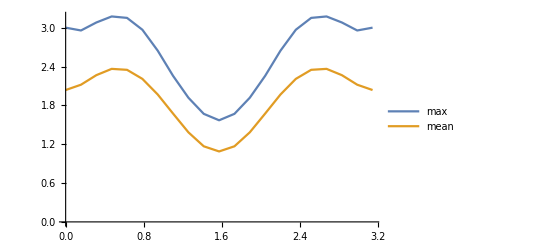

```mathematica
ListLinePlot[{kacfibomax,kacfibomean},PlotLegends->{"max","mean"}]
```

```mathematica
ListLinePlot[Table[wfibon[[n]],{n,1,6}]]
```

Part::partd: Part specification wfibon⟦1⟧ is longer than depth of object.

Part::partd: Part specification wfibon⟦2⟧ is longer than depth of object.

Part::partd: Part specification wfibon⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

## dt = pi/16

#### 4+4

#### data

```mathematica
fibo16={-0.000000000000000000*10^+00,1.201752073385712993*10^+00,2.000198957751610607*10^+00,2.987210844025257384*10^+00,2.537134727895763220*10^+00,2.334369911771120076*10^+00,2.174288814349339738*10^+00,2.319458782853296430*10^+00,3.365700043202264347*10^+00,2.817157742316335867*10^+00,3.386677019081711482*10^+00,2.395083971947598034*10^+00,1.604683651961297475*10^+00,1.922371128385191641*10^+00,2.583175962449891561*10^+00,3.050714353634844223*10^+00,2.293627088256829705*10^+00,1.569037282711958303*10^+00,8.319931616876948821*10^-01,1.230165130626886816*10^+00,2.026133734046985158*10^+00,3.000587322469599805*10^+00,2.565407387537330219*10^+00,2.132615494368687692*10^+00,2.315417741179853550*10^+00,2.483266517230342973*10^+00,2.482132376614984537*10^+00,1.943443593847042905*10^+00,1.820609045210279220*10^+00,1.869530799515727981*10^+00,1.555834460907301153*10^+00,1.389695542942665174*10^+00,2.179841241530914075*10^+00,2.527755627006337047*10^+00,2.502822983831402226*10^+00,2.127764264152110840*10^+00,1.508638560623239089*10^+00,2.245699591086149471*10^+00,3.032377514578838973*10^+00,2.351339684425035603*10^+00,1.742669859570043167*10^+00,1.451265151356788685*10^+00,2.340477467192345173*10^+00,2.506442363589549416*10^+00,2.278913818236230071*10^+00,2.890844585805230071*10^+00,2.728449313151817268*10^+00,2.913724062627201405*10^+00,2.394256417006406679*10^+00,1.763107623082506237*10^+00,1.984005887722674721*10^+00,2.942238823531937442*10^+00,2.504256605022423088*10^+00,2.094042293648713748*10^+00,2.048702759259216855*10^+00,1.577091366092373326*10^+00,2.110283827222847464*10^+00,2.702397643454252929*10^+00,2.670660466767476482*10^+00,2.260654406173459474*10^+00,2.474119316480094977*10^+00,2.612580126996217889*10^+00,2.118050043004098715*10^+00,2.740327229791384767*10^+00,2.733485421025810158*10^+00,2.354416465898297783*10^+00,1.761978321347905885*10^+00,1.740017432148681653*10^+00,2.362744676342216632*10^+00,2.293162553353095490*10^+00,2.966650800079215333*10^+00,2.178548066317119947*10^+00,2.382669168773468904*10^+00,2.971853258619510996*10^+00,2.164277923128760328*10^+00,2.215665284915181665*10^+00,2.108134839351471612*10^+00,1.995953329579939650*10^+00,1.969864294985960829*10^+00,2.204562093453498406*10^+00,2.271518657965604593*10^+00,2.405587858713018612*10^+00,1.997593679703249858*10^+00,2.132944756424056010*10^+00,1.565611976500628888*10^+00,1.382352352031388287*10^+00,1.578745157384216835*10^+00,1.626416245617466672*10^+00,1.966274390244721726*10^+00,2.557157187547217880*10^+00,2.096575546181924654*10^+00,1.852694146990290225*10^+00,2.870154181714910990*10^+00,2.508629346875209443*10^+00,2.817924076940894640*10^+00,2.230817269481579324*10^+00,2.402454250536490310*10^+00,1.956018502444384577*10^+00,2.540465272658755325*10^+00,3.019712839059045972*10^+00,2.855522188965139208*10^+00,3.190408470470257996*10^+00,2.456260147047705011*10^+00,2.352890588933153282*10^+00,2.541561468286009706*10^+00,2.504387534819271455*10^+00,2.049641984942062845*10^+00,1.791551800566735020*10^+00,2.333287231588285326*10^+00,2.420521136829493436*10^+00,9.570646552357648940*10^-01,1.742395578690791869*10^+00,1.904720666102819315*10^+00,2.568870933435127846*10^+00,2.328702059474981212*10^+00,1.923489165235777509*10^+00,2.355015115415322047*10^+00,2.763631913509468685*10^+00,3.344131155667347866*10^+00,2.576532878708491126*10^+00,2.883218836383244721*10^+00,2.574159198356362310*10^+00,1.844800181381573534*10^+00,2.597497669918069185*10^+00,2.476588613928222049*10^+00,2.439771659109277735*10^+00,2.393265287137970709*10^+00,2.221299411213466080*10^+00,1.848068915234168941*10^+00,1.881706861863317259*10^+00,1.900242747028110912*10^+00,2.764340512213992351*10^+00,1.940523156647991021*10^+00,1.487150895571521581*10^+00,2.512667952623502732*10^+00,2.889782584496393358*10^+00,2.862769130853714650*10^+00,2.070759236789877278*10^+00,1.508248815026730805*10^+00,1.837300901715093637*10^+00,2.561771390999833642*10^+00,2.047705353430023134*10^+00,1.892444450781171739*10^+00,1.561044635658610735*10^+00,2.273844492621601709*10^+00,2.145762546407736782*10^+00,2.060826366505090323*10^+00,3.291575577822030141*10^+00,2.628824025094350869*10^+00,2.233464111240575090*10^+00,1.907255121344224591*10^+00,1.268219910055500055*10^+00,2.401601920073595409*10^+00,3.213465941101183443*10^+00,2.533050309565014757*10^+00,2.005686634158110326*10^+00,2.859994217616998124*10^+00,2.801127229344377412*10^+00,2.624679444210795687*10^+00,3.057455307255460664*10^+00,2.382944640613769760*10^+00,2.594935346550174327*10^+00,1.926736013418617777*10^+00,1.955404224214790432*10^+00,2.753339839721222315*10^+00,2.267702688881014339*10^+00,2.483339059532389204*10^+00,1.791923344196896251*10^+00,2.322880538580380794*10^+00,2.635942846213023660*10^+00,2.306608924765292556*10^+00,2.867587955288443347*10^+00,2.569915385968035260*10^+00,1.662244481126557538*10^+00,1.845625441208392559*10^+00,2.309469621937571215*10^+00,2.989076418828772841*10^+00,2.681072882690080927*10^+00,3.433223724596458304*10^+00,2.648854505593220665*10^+00,2.670201046532990397*10^+00,2.821686858062121050*10^+00,2.566165706810720870*10^+00,3.215458245891965383*10^+00,2.470075114870184052*10^+00,2.285430310622458272*10^+00,2.041977848278403673*10^+00,1.679369947194784274*10^+00,1.148170080004975446*10^+00,2.192271348547624399*10^+00,2.877801850468781453*10^+00,2.207724291054646848*10^+00,2.214206433690641518*10^+00,2.060497201385596888*10^+00,2.171012368864210007*10^+00,2.955201680323892077*10^+00,2.498604480370767877*10^+00,2.188587458520258267*10^+00,1.923458625836304448*10^+00,1.852456763650081717*10^+00,2.722912528242654327*10^-14,1.195312078330093009*10^+00,1.961027159368288864*10^+00,2.923445790277579004*10^+00,2.520721062010767177*10^+00,2.316922573587435252*10^+00,2.208737161624412693*10^+00,2.369302390591159657*10^+00,3.321885626673863001*10^+00,2.886904673420104039*10^+00,3.417426679385370480*10^+00,2.482744171465253391*10^+00,1.686922615833902572*10^+00,1.920863568820445177*10^+00,2.569742559599561105*10^+00,2.938355921793629033*10^+00,2.254186222481751045*10^+00,1.558067288379239246*10^+00,8.538770162655104912*10^-01,1.244215240547243084*10^+00,2.042949634851045637*10^+00,2.951212531773151682*10^+00,2.558672994197153550*10^+00,2.158064758366935454*10^+00,2.342110965034713388*10^+00,2.529165567697275296*10^+00,2.521798227630204003*10^+00,2.031645358767725007*10^+00,1.913097045504284832*10^+00,1.963942760900094564*10^+00,1.661823169342353301*10^+00,1.465859565127019426*10^+00,2.194074351434561976*10^+00,2.491305644396303975*10^+00,2.477398287172635438*10^+00,2.162959899950357645*10^+00,1.627706739624319887*10^+00,2.370916963018598889*10^+00,3.082664156288737800*10^+00,2.468249838722085698*10^+00,1.923965685457375674*10^+00,1.722687609410160192*10^+00,2.547262110824397574*10^+00,2.580408044657944266*10^+00,2.366905127897890093*10^+00,2.862250788861335771*10^+00,2.713039588941658309*10^+00,2.889983079057508952*10^+00,2.363449215914905199*10^+00,1.786375943931071353*10^+00,2.042122183158053161*10^+00,2.901821137373204351*10^+00,2.557144123867778340*10^+00,2.180724457335207145*10^+00,2.242886132306628255*10^+00,1.820138984580361718*10^+00,2.309646141079638060*10^+00,2.818992157858438041*10^+00,2.769929527902740940*10^+00,2.321654180717577898*10^+00,2.486458383043706366*10^+00,2.623209805222113999*10^+00,2.113691071579760994*10^+00,2.735959150357128777*10^+00,2.775975204833247112*10^+00,2.457362392822000974*10^+00,1.918338806176991485*10^+00,1.857661457819671735*10^+00,2.383465396813231330*10^+00,2.302421197700204925*10^+00,2.875455028620519826*10^+00,2.157889230416373927*10^+00,2.322728064624209665*10^+00,2.899453592726398909*10^+00,2.131131298459687962*10^+00,2.234727938287233151*10^+00,2.249097210936839453*10^+00,2.186790476416250684*10^+00,2.142711489603157382*10^+00,2.298454775922834870*10^+00,2.306165385013762226*10^+00,2.353391747109994991*10^+00,1.983925502444908728*10^+00,2.105149448697833048*10^+00,1.609294620724858405*10^+00,1.473367310344312120*10^+00,1.626078044314118287*10^+00,1.718899853907983388*10^+00,2.081991326874438109*10^+00,2.574207775560397593*10^+00,2.125465521962373927*10^+00,1.884548819976039180*10^+00,2.832193178349690754*10^+00,2.581470451500063046*10^+00,2.882756623658075057*10^+00,2.361669933760643048*10^+00,2.565180500407830522*10^+00,2.117234254318858255*10^+00,2.652686966000797231*10^+00,3.012254469686256098*10^+00,2.879608682899168492*10^+00,3.171707483183011433*10^+00,2.535717792914207180*10^+00,2.468395814498132168*10^+00,2.629558061672207181*10^+00,2.630133788140050832*10^+00,2.184068767963832425*10^+00,1.969714444695842559*10^+00,2.456012486124756755*10^+00,2.498143871388666781*10^+00,1.124118059366469025*10^+00,1.878049679229477853*10^+00,2.040873784856991779*10^+00,2.595258984686975801*10^+00,2.383704781777213899*10^+00,2.009834108963981514*10^+00,2.378747630939785918*10^+00,2.839395094249715257*10^+00,3.325580478506546367*10^+00,2.617006127922375303*10^+00,2.925457151688108492*10^+00,2.631906975186315112*10^+00,1.936040234873887655*10^+00,2.594407748799177682*10^+00,2.511282402389824142*10^+00,2.440123927623169653*10^+00,2.396297914933263939*10^+00,2.214720568824092517*10^+00,1.911463159958993074*10^+00,1.966291037033534916*10^+00,2.029950494960984564*10^+00,2.872695317673076065*10^+00,2.150157731395744065*10^+00,1.785483553739743101*10^+00,2.505148490406519990*10^+00,2.796357336375252522*10^+00,2.762899176162187942*10^+00,2.033434759180428042*10^+00,1.491217023051224055*10^+00,1.890222168913573420*10^+00,2.567085145579021344*10^+00,2.074822121158371946*10^+00,1.904325671603682046*10^+00,1.689845878173569682*10^+00,2.381375882490665674*10^+00,2.321098685198809797*10^+00,2.233378327079667880*10^+00,3.287275905684941435*10^+00,2.660016218003104171*10^+00,2.324792770876735304*10^+00,2.072334375975551701*10^+00,1.413636603377583345*10^+00,2.439981039997576318*10^+00,3.098471577082007933*10^+00,2.515854962940816897*10^+00,2.069835786708501324*10^+00,2.901653131098505867*10^+00,2.770114390604797361*10^+00,2.599763589783333551*10^+00,3.007148698966755962*10^+00,2.413894100394306186*10^+00,2.604036994221128332*10^+00,1.992886959948425130*10^+00,1.971630499225534017*10^+00,2.769641498551656422*10^+00,2.406219192120077732*10^+00,2.599822159634886276*10^+00,1.962049322168545773*10^+00,2.464028969875188047*10^+00,2.741818064006292133*10^+00,2.425639965466290793*10^+00,2.864469246488039467*10^+00,2.553260340770937553*10^+00,1.648214121976305346*10^+00,1.834688666574183280*10^+00,2.305028940588196296*10^+00,2.995308062993164544*10^+00,2.726989897949352759*10^+00,3.398020548490926718*10^+00,2.697114333500195471*10^+00,2.754748122105373120*10^+00,2.907665338038135427*10^+00,2.694098172849847650*10^+00,3.264826207159694071*10^+00,2.579387311397947080*10^+00,2.395376147962066327*10^+00,2.194452130961026093*10^+00,1.877378412564458365*10^+00,1.400059496938792947*10^+00,2.350962702081524469*10^+00,2.906363252571946276*10^+00,2.340821349510637361*10^+00,2.340481024941032828*10^+00,2.177203443339621014*10^+00,2.253302706518657494*10^+00,2.983221703234926192*10^+00,2.535585608619496334*10^+00,2.261570064383826129*10^+00,2.119986445075280113*10^+00,2.020009236201437464*10^+00,-9.610279511444755881*10^-16,1.176674520860375051*10^+00,1.834137670477184123*10^+00,2.748129169167257135*10^+00,2.463952915674791910*10^+00,2.282283081584223439*10^+00,2.207517022632039527*10^+00,2.401550344833871087*10^+00,3.209133969133386444*10^+00,3.021885722692622345*10^+00,3.452884806712487098*10^+00,2.589091484128999809*10^+00,1.823758193716868536*10^+00,2.005540530109662267*10^+00,2.562479418525886565*10^+00,2.685320039407569137*10^+00,2.182225533208080215*10^+00,1.590335306883273514*10^+00,9.939054993744238509*10^-01,1.359623734481982815*10^+00,2.112315129843144845*10^+00,2.830655564199702212*10^+00,2.538176135022321311*10^+00,2.188492366481993301*10^+00,2.371243122139206516*10^+00,2.599007237704554552*10^+00,2.610929611943668682*10^+00,2.228732685411051850*10^+00,2.103942973779748371*10^+00,2.205666848584546980*10^+00,1.885737870274265537*10^+00,1.706209975655633926*10^+00,2.248356829244261057*10^+00,2.406058584854307014*10^+00,2.433828116609503045*10^+00,2.175592003273852271*10^+00,1.820407396907496977*10^+00,2.591960040000856225*10^+00,3.172263699107237489*10^+00,2.700373074827522757*10^+00,2.318783239872118429*10^+00,2.243157468863041792*10^+00,2.843098177485535949*10^+00,2.635820671510507029*10^+00,2.455791874575657729*10^+00,2.823436382032428416*10^+00,2.652052997347502217*10^+00,2.815118169081402666*10^+00,2.270720478744863158*10^+00,1.822838468095873576*10^+00,2.175763898374912131*10^+00,2.849895351121407572*10^+00,2.673306102464191092*10^+00,2.390194537144057385*10^+00,2.552893622037307964*10^+00,2.216676115141662073*10^+00,2.623109193112106219*10^+00,2.991208818175781659*10^+00,2.950419805542807250*10^+00,2.427149158669807516*10^+00,2.472980262243168248*10^+00,2.593961378157344733*10^+00,2.085437210011521270*10^+00,2.721461475626800297*10^+00,2.877618211817460470*10^+00,2.675682675440314906*10^+00,2.227438465321411432*10^+00,2.130877307253039366*10^+00,2.409922547938627702*10^+00,2.304674142815732463*10^+00,2.639828651830720130*10^+00,2.086871506740349158*10^+00,2.151118369880614001*10^+00,2.705365087353244657*10^+00,2.045767413082169028*10^+00,2.262657272386449314*10^+00,2.578074861080427826*10^+00,2.604767356684660307*10^+00,2.469705002999695420*10^+00,2.435830018991653745*10^+00,2.357362758360567856*10^+00,2.269759613400503806*10^+00,1.991627435565216153*10^+00,2.006881948873059596*10^+00,1.647714233107957726*10^+00,1.662522918631716085*10^+00,1.729297998021360527*10^+00,1.892951302510629707*10^+00,2.300280037242201647*10^+00,2.622275346090674475*10^+00,2.173589434077686899*10^+00,2.005822154943561753*10^+00,2.833554910136732108*10^+00,2.694412183932483718*10^+00,2.977417488137399815*10^+00,2.568461567216866914*10^+00,2.828339006740743233*10^+00,2.373671371265761998*10^+00,2.804193593699658926*10^+00,3.005374178161329901*10^+00,2.938548735081632390*10^+00,3.136424470143273080*10^+00,2.713598878787021551*10^+00,2.719837508693712547*10^+00,2.731833331068879822*10^+00,2.842300765389742967*10^+00,2.461522891642019317*10^+00,2.311943880295038056*10^+00,2.662062186276775044*10^+00,2.569197351632765969*10^+00,1.446685189349912193*10^+00,2.114904537802711371*10^+00,2.309728418971551456*10^+00,2.634092844829252655*10^+00,2.508017779985099338*10^+00,2.220458277109076839*10^+00,2.461979162046874059*10^+00,2.930849486043735297*10^+00,3.303281900522401227*10^+00,2.756025747098435286*10^+00,3.028076628494303701*10^+00,2.693592819705430852*10^+00,2.088114194609660412*10^+00,2.531911427369098799*10^+00,2.580209845936916935*10^+00,2.458778532668399297*10^+00,2.435115616681656103*10^+00,2.238698820181218352*10^+00,2.046293067560802648*10^+00,2.122430352531566200*10^+00,2.247717405218363940*10^+00,3.021750897098596234*10^+00,2.516720313062601466*10^+00,2.284806698740067255*10^+00,2.501370060391516770*10^+00,2.595806592586329398*10^+00,2.523719840915790602*10^+00,1.943011853533150424*10^+00,1.420501361295337439*10^+00,1.975698161688851151*10^+00,2.552604428445871321*10^+00,2.135962672816787311*10^+00,1.930705869664084862*10^+00,1.961303701546458722*10^+00,2.624978296341407891*10^+00,2.589325035656704355*10^+00,2.517948558149033733*10^+00,3.263737715982077070*10^+00,2.681783567358893006*10^+00,2.499696200681202019*10^+00,2.312006255788592313*10^+00,1.641830579206048135*10^+00,2.446900324745100441*10^+00,2.811271565413994367*10^+00,2.400644064676892953*10^+00,2.215170572048082764*10^+00,2.968956538180361093*10^+00,2.659475749144364798*10^+00,2.525422157446017835*10^+00,2.889835481350027990*10^+00,2.476997658925175205*10^+00,2.643797379255736324*10^+00,2.113721959172876197*10^+00,2.011613327261703610*10^+00,2.815012887010230003*10^+00,2.657383091297460531*10^+00,2.767274187697583265*10^+00,2.243561331092536193*10^+00,2.780799363894395970*10^+00,2.897118289425557602*10^+00,2.587519186784233316*10^+00,2.841384758364525531*10^+00,2.513991837906067950*10^+00,1.663305810460161460*10^+00,1.863975813058907693*10^+00,2.347290719550014337*10^+00,3.014562961014502385*10^+00,2.800668586219669631*10^+00,3.314024592558258764*10^+00,2.768532058587814149*10^+00,2.869094910482212768*10^+00,3.029563966298339128*10^+00,2.846488785103416408*10^+00,3.288099857463682607*10^+00,2.671257044787982426*10^+00,2.590345631688720118*10^+00,2.538568220116370178*10^+00,2.276912387380687353*10^+00,1.863712821116505935*10^+00,2.619859305797189730*10^+00,2.920520717014222445*10^+00,2.585004881773997010*10^+00,2.578796473048057258*10^+00,2.379849665225101329*10^+00,2.402725230020164027*10^+00,3.007591984533408258*10^+00,2.601673978549856159*10^+00,2.463495498742194201*10^+00,2.475657500477929318*10^+00,2.334430640743584640*10^+00,9.610279511444749964*10^-16,1.147801670652606409*10^+00,1.686335839172630635*10^+00,2.495807678372575111*10^+00,2.405181201216390896*10^+00,2.226036601276748961*10^+00,2.131133538040549613*10^+00,2.384368599064186967*10^+00,3.106937359997004489*10^+00,3.154353626608048966*10^+00,3.397092328309871068*10^+00,2.598487418628302237*10^+00,1.909291408487948871*10^+00,2.149962091587264812*10^+00,2.590880709730253528*10^+00,2.506424401805664726*10^+00,2.155896720148493095*10^+00,1.759601802378124358*10^+00,1.307529150758036884*10^+00,1.612210305715563674*10^+00,2.266867559457265813*10^+00,2.690965110362508295*10^+00,2.491474623651249054*10^+00,2.171054195274468857*10^+00,2.358768369800048781*10^+00,2.672743382810444324*10^+00,2.698245235876118642*10^+00,2.406283571128341237*10^+00,2.281103355426390422*10^+00,2.462601576649556367*10^+00,2.213709029273763562*10^+00,2.069442345586929743*10^+00,2.344800388583433648*10^+00,2.319727587964709681*10^+00,2.378010150208823337*10^+00,2.076724296356160515*10^+00,1.896792409960143422*10^+00,2.748560831932747917*10^+00,3.186090993652145542*10^+00,2.904082972770785531*10^+00,2.665231068340239595*10^+00,2.712113083804957192*10^+00,3.011385178042496946*10^+00,2.647608114005201241*10^+00,2.488830842022981216*10^+00,2.853781602778709292*10^+00,2.595614731031965938*10^+00,2.687018596783524060*10^+00,2.188105799675682306*10^+00,1.909820134519429224*10^+00,2.317189792109683566*10^+00,2.815644301309531805*10^+00,2.820583076154935753*10^+00,2.559677200049573997*10^+00,2.751302389052036279*10^+00,2.497565051795834989*10^+00,2.845090414478864904*10^+00,3.097324375049029133*10^+00,2.982463591284927773*10^+00,2.414582249872926578*10^+00,2.357960886172090209*10^+00,2.490059509613494981*10^+00,2.000109219122621518*10^+00,2.715508135468246653*10^+00,2.982739971855018268*10^+00,2.898288098161243997*10^+00,2.453026417369124967*10^+00,2.363599379645660026*10^+00,2.398605605423874465*10^+00,2.275507918456582068*10^+00,2.335588065394906820*10^+00,1.912274002376222137*10^+00,1.898595993032744289*10^+00,2.458229783656266765*10^+00,1.952778996301244074*10^+00,2.286893601951551780*10^+00,2.871428963418382274*10^+00,2.972063699712329754*10^+00,2.719283656211322509*10^+00,2.507832989403638635*10^+00,2.423447576142979898*10^+00,2.281266879064056674*10^+00,2.042777188998976534*10^+00,1.878614527144982116*10^+00,1.675357889100264508*10^+00,1.834764944958398480*10^+00,1.820757344959452517*10^+00,2.061343062123114134*10^+00,2.471430536346679752*10^+00,2.661607203163911528*10^+00,2.256675393233955607*10^+00,2.171496605045526440*10^+00,2.879778585774969368*10^+00,2.790468070345194285*10^+00,3.009883854769841882*10^+00,2.688033343080221904*10^+00,2.960430393106719293*10^+00,2.598199817048499671*10^+00,2.890676200174898902*10^+00,2.904375057771258373*10^+00,2.997173347276687494*10^+00,3.112879295924878331*10^+00,2.919177425582112129*10^+00,2.980341348096792409*10^+00,2.816387339508184429*10^+00,2.974789868749508237*10^+00,2.637248951651078421*10^+00,2.511294182453911006*10^+00,2.717560813111256746*10^+00,2.538098785317105310*10^+00,1.710128889246217199*10^+00,2.293992981074894466*10^+00,2.509120474405957424*10^+00,2.631406542648044411*10^+00,2.605705149999149928*10^+00,2.454561698342820897*10^+00,2.558629940004013559*10^+00,2.909557698690973915*10^+00,3.146300356183104441*10^+00,2.889606013511354821*10^+00,3.108934569141484694*10^+00,2.707213076710530242*10^+00,2.179633710030490334*10^+00,2.437650742323991260*10^+00,2.623667479527490354*10^+00,2.472587116617604330*10^+00,2.548436728809717167*10^+00,2.273860399726347570*10^+00,2.166688309730839812*10^+00,2.217979538155424812*10^+00,2.392341648801742160*10^+00,3.032037482501159786*10^+00,2.741488541269069490*10^+00,2.660662745868387358*10^+00,2.518401509923901216*10^+00,2.436229506992221516*10^+00,2.306799508394980158*10^+00,1.873155994441200400*10^+00,1.388105180991794363*10^+00,2.063466130503892160*10^+00,2.446617165688934392*10^+00,2.151879219349217554*10^+00,1.875204981874548427*10^+00,2.177512056730244172*10^+00,2.843866806922382917*10^+00,2.774311939656614712*10^+00,2.741201586484946606*10^+00,3.186667831804010032*10^+00,2.664377128086909075*10^+00,2.658918945905130116*10^+00,2.452969694774457032*10^+00,1.765330132203143609*10^+00,2.376326647822296856*10^+00,2.448344467285097803*10^+00,2.169235593856036814*10^+00,2.327663468416838466*10^+00,2.947931254163762560*10^+00,2.475401944116754294*10^+00,2.384413500695893084*10^+00,2.771083406074950517*10^+00,2.587427891776501898*10^+00,2.675375544865800315*10^+00,2.287085684877444347*10^+00,2.041774678136230037*10^+00,2.839897008862300787*10^+00,2.887174446369270342*10^+00,2.843668738524350648*10^+00,2.410420084345424208*10^+00,2.969045096379017590*10^+00,2.926587661918313987*10^+00,2.647637898181482541*10^+00,2.772220125894752307*10^+00,2.470834528895518911*10^+00,1.794698683202788025*10^+00,2.037882012390227704*10^+00,2.456115072890121098*10^+00,3.028595276119448787*10^+00,2.833145566976852159*10^+00,3.160662928654144999*10^+00,2.757114822205958049*10^+00,2.849129748119771488*10^+00,3.084476790222739240*10^+00,2.879626550722672818*10^+00,3.177582749249793004*10^+00,2.665675671527479640*10^+00,2.761103817716621389*10^+00,2.854511585503369808*10^+00,2.695630867866170899*10^+00,2.322050525265566101*10^+00,2.791733836662442236*10^+00,2.866629055739749354*10^+00,2.786244921727546675*10^+00,2.718158010645265854*10^+00,2.520367237563968743*10^+00,2.511406979410931495*10^+00,2.967643188678414479*10^+00,2.631111745145515712*10^+00,2.668943758691408874*10^+00,2.771408370304883739*10^+00,2.558413346666800425*10^+00,4.805139755722374982*10^-16,1.111694603785813751*10^+00,1.526972652390372831*10^+00,2.247783056914256061*10^+00,2.349396426046307607*10^+00,2.161600468445844747*10^+00,2.016385255474829830*10^+00,2.385157677747101079*10^+00,3.079514932411011152*10^+00,3.205512102231182325*10^+00,3.229363253411190016*10^+00,2.479736343670738918*10^+00,1.891870185025379403*10^+00,2.331596726397076935*10^+00,2.645088603143233907*10^+00,2.496828015672523549*10^+00,2.243189766295302423*10^+00,2.074020295912419432*10^+00,1.720072282064966762*10^+00,2.015123801346410115*10^+00,2.470457187990969139*10^+00,2.582462163322399640*10^+00,2.436160745670632899*10^+00,2.090352370786257019*10^+00,2.289259747409297496*10^+00,2.715112460853051246*10^+00,2.777919975289451671*10^+00,2.537585187835098122*10^+00,2.440489828008612694*10^+00,2.702284228219152595*10^+00,2.583348463667699324*10^+00,2.482580283734222348*10^+00,2.468581193680858377*10^+00,2.269821135780015098*10^+00,2.269863938463048569*10^+00,1.874794172680238180*10^+00,1.809136220136801532*10^+00,2.770877397587474977*10^+00,3.123953662213034832*10^+00,3.057315832399916999*10^+00,2.899791134802123693*10^+00,2.972794483500737606*10^+00,3.066945460145683811*10^+00,2.683313531548463970*10^+00,2.508707645988476287*10^+00,2.961582769442815621*10^+00,2.586788539338658044*10^+00,2.525998138581865060*10^+00,2.190469918556014584*10^+00,2.029694958313618347*10^+00,2.428199420747706228*10^+00,2.819603510060490148*10^+00,2.883364179642237790*10^+00,2.589924707050812902*10^+00,2.768846353655944004*10^+00,2.641078400059623910*10^+00,2.939239784174215053*10^+00,3.087088106510644803*10^+00,2.871039118776150367*10^+00,2.266049812197629798*10^+00,2.167274544325230590*10^+00,2.351335187654704839*10^+00,1.862962117124499661*10^+00,2.697000678279155572*10^+00,3.031022045487663519*10^+00,3.002022485081771386*10^+00,2.568219509608538509*10^+00,2.467609838503292519*10^+00,2.365866278401078659*10^+00,2.285459152333126021*10^+00,2.114443249072846420*10^+00,1.689627444117050237*10^+00,1.643116613223278621*10^+00,2.205911627025212596*10^+00,1.821226590339368512*10^+00,2.292463474727310935*10^+00,3.064782421684302260*10^+00,3.162616584783319862*10^+00,2.771751878441282901*10^+00,2.472364806801495618*10^+00,2.430578681975261279*10^+00,2.356143708933428726*10^+00,2.155446924948701160*10^+00,1.795203356452770516*10^+00,1.663849202387247317*10^+00,1.974759712754583063*10^+00,1.892349652842779451*10^+00,2.205837962960926824*10^+00,2.575837074158441542*10^+00,2.667602556248150236*10^+00,2.356214441905470913*10^+00,2.322140065230851924*10^+00,2.930412082085418035*10^+00,2.952321526508707272*10^+00,3.001594412972470316*10^+00,2.695552999897736779*10^+00,2.948861948955089574*10^+00,2.768454754215107450*10^+00,2.926161508272199896*10^+00,2.781600399828884296*10^+00,3.030853895550934318*10^+00,3.105556383921932895*10^+00,3.075640160230638465*10^+00,3.158431398413992675*10^+00,2.897566510608040602*10^+00,3.027623766822939544*10^+00,2.683826086417604007*10^+00,2.492047575333922627*10^+00,2.607198108161400629*10^+00,2.431531095479994242*10^+00,1.817320226250618731*10^+00,2.353951250070275059*10^+00,2.579152599352880770*10^+00,2.645747934243275257*10^+00,2.704584853265484146*10^+00,2.685180843006120810*10^+00,2.656842445133949404*10^+00,2.855415860064199229*10^+00,2.916718486184171510*10^+00,2.915675524344181646*10^+00,3.133825507184495596*10^+00,2.632693760448304943*10^+00,2.163986641947559519*10^+00,2.386111672057975142*10^+00,2.653291082063768513*10^+00,2.448313285796889005*10^+00,2.692523164199892793*10^+00,2.356421019223007285*10^+00,2.278452222856226062*10^+00,2.260840770476197914*10^+00,2.402392210343929690*10^+00,2.894988282286305115*10^+00,2.770468376870127702*10^+00,2.794890747502002171*10^+00,2.468954896075050254*10^+00,2.349079064720805743*10^+00,2.236815230746675986*10^+00,1.973794219918207027*10^+00,1.539593177948471725*10^+00,2.137237386494220903*10^+00,2.354082668674810197*10^+00,2.150825441453924292*10^+00,1.814059195267904379*10^+00,2.305209593311968508*10^+00,2.973459971634040411*10^+00,2.870314471967900793*10^+00,2.848480826532656884*10^+00,3.057274273638638462*10^+00,2.596274306530586440*10^+00,2.761848706891870009*10^+00,2.479967381935394233*10^+00,1.795432971643837750*10^+00,2.256522809454144074*10^+00,2.077139208934810188*10^+00,1.951306801079734088*10^+00,2.419516117803055977*10^+00,2.804713504288308457*10^+00,2.258837716525426309*10^+00,2.247434603525936936*10^+00,2.651604780689862384*10^+00,2.655932592846329321*10^+00,2.685068080787070599*10^+00,2.477503643399360023*10^+00,2.106988201883012390*10^+00,2.849301292642341110*10^+00,3.035898433026133603*10^+00,2.806447808574787928*10^+00,2.404546641977460375*10^+00,2.933985132099874882*10^+00,2.748857101764768274*10^+00,2.567725531409695172*10^+00,2.613099934768625676*10^+00,2.435814830783706864*10^+00,2.047245476232937733*10^+00,2.269782569569859909*10^+00,2.600992396756752534*10^+00,3.022405772962248438*10^+00,2.819091586418065454*10^+00,2.965753320788181213*10^+00,2.663645148698766452*10^+00,2.707066094298132164*10^+00,3.028695945981527693*10^+00,2.816002220646153020*10^+00,2.956807858982673842*10^+00,2.609693588889671290*10^+00,2.873741814353091506*10^+00,3.050388807602026020*10^+00,3.010083251721691333*10^+00,2.676552582678376702*10^+00,2.867970342642274240*10^+00,2.795709620700485676*10^+00,2.916444000757285604*10^+00,2.762183298363067863*10^+00,2.601171587432276056*10^+00,2.616364167427252418*10^+00,2.882946718116999207*10^+00,2.660863436552779238*10^+00,2.821522182517728794*10^+00,2.908508239144554253*10^+00,2.636390135253796174*10^+00,3.203426503814917641*10^-16,1.072035540455029690*10^+00,1.388362084094110216*10^+00,2.034895008397227478*10^+00,2.343177805352885112*10^+00,2.130249035525134449*10^+00,1.961531190220920706*10^+00,2.426848418372746341*10^+00,3.073922875973516433*10^+00,3.219342325874053667*10^+00,3.009331722292168720*10^+00,2.223796733219004729*10^+00,1.773282400890609178*10^+00,2.423095289588774293*10^+00,2.683390402788373041*10^+00,2.607174831226202638*10^+00,2.400408670041874970*10^+00,2.448706376401029061*10^+00,2.145756840190586878*10^+00,2.404917864719929632*10^+00,2.689711257212573869*10^+00,2.483510538619789099*10^+00,2.374911366959239878*10^+00,2.018094312803903279*10^+00,2.217203469145916817*10^+00,2.763502048150660251*10^+00,2.844951144579803248*10^+00,2.633425019407202416*10^+00,2.578416091713602754*10^+00,2.859342174652967472*10^+00,2.896702886603332416*10^+00,2.820197670375962584*10^+00,2.557608392093755345*10^+00,2.222398869409287325*10^+00,2.122981439557297012*10^+00,1.722723867289556621*10^+00,1.644919916150709982*10^+00,2.704391537164470893*10^+00,3.046289346481740878*10^+00,3.167386962187831667*10^+00,3.026238454468877404*10^+00,3.029928032969197993*10^+00,3.060840603277126259*10^+00,2.772163091898277365*10^+00,2.626147727802357501*10^+00,3.096132502381852447*10^+00,2.665788729663075785*10^+00,2.407773018066963200*10^+00,2.278698759778240213*10^+00,2.142911499304776868*10^+00,2.458160797146395460*10^+00,2.773181600925405110*10^+00,2.837815593710760975*10^+00,2.517097615680053746*10^+00,2.639510272255901846*10^+00,2.692726579126761610*10^+00,2.976307667995446327*10^+00,3.042186187704305933*10^+00,2.760833392614815640*10^+00,2.154734089952955678*10^+00,2.066709536111069667*10^+00,2.222345966813029872*10^+00,1.687747192117911910*10^+00,2.667989512228928550*10^+00,3.020723499912048915*10^+00,3.010671448412714835*10^+00,2.595632881723833663*10^+00,2.479048237139899857*10^+00,2.347279684057234750*10^+00,2.398503272159492106*10^+00,2.087217097109764552*10^+00,1.524107575152514826*10^+00,1.501981783198494291*10^+00,1.981720486150607030*10^+00,1.695861266579309579*10^+00,2.233530820154040697*10^+00,3.134014677879465971*10^+00,3.196030023352456340*10^+00,2.695352486293491889*10^+00,2.376515915702304582*10^+00,2.378338399007547288*10^+00,2.366720219642528544*10^+00,2.228138872803251402*10^+00,1.748489592076079013*10^+00,1.650395070787721741*10^+00,2.075634227500207096*10^+00,1.947564037539005533*10^+00,2.364482470676723569*10^+00,2.651121165324874518*10^+00,2.629501846458956571*10^+00,2.420088223663758864*10^+00,2.400850190841832266*10^+00,2.970568591216607324*10^+00,3.123792165164221757*10^+00,2.967897296810832586*10^+00,2.675361584080619526*10^+00,2.878647601040174919*10^+00,2.850641601192149821*10^+00,2.949963100714223074*10^+00,2.717465805710702398*10^+00,3.029401889083628063*10^+00,3.096969979617414381*10^+00,3.151472978965307092*10^+00,3.248904101846770143*10^+00,2.996465174162378897*10^+00,3.040597409480780833*10^+00,2.631762361617652424*10^+00,2.339804153383179930*10^+00,2.440044814523848249*10^+00,2.343217965701947847*10^+00,1.829233504015576939*10^+00,2.367088127825198285*10^+00,2.597985487856652398*10^+00,2.707861843440953820*10^+00,2.857335559192295094*10^+00,2.909528477955240611*10^+00,2.750708669009696461*10^+00,2.821838348993336076*10^+00,2.759168061412768935*10^+00,2.885345022932538139*10^+00,3.136711276129772852*10^+00,2.509634349322594105*10^+00,2.086725468473764167*10^+00,2.382440844205085728*10^+00,2.708954906329243961*10^+00,2.424765478642280314*10^+00,2.776804280574288519*10^+00,2.446716391481312591*10^+00,2.393898167688388146*10^+00,2.306932964468068281*10^+00,2.365209865827563984*10^+00,2.683318512849618642*10^+00,2.675109994254561752*10^+00,2.701746420870012599*10^+00,2.378088757940067133*10^+00,2.312677297569390777*10^+00,2.312267174326634755*10^+00,2.229195498194102232*10^+00,1.940195609185139114*10^+00,2.228388084155874971*10^+00,2.369483672345057634*10^+00,2.189468534202213323*10^+00,1.871056730842426852*10^+00,2.425198978898214897*10^+00,3.008218324865801208*10^+00,2.885413809663273987*10^+00,2.892524550326004640*10^+00,2.937767468282840966*10^+00,2.529806014549492943*10^+00,2.836975878223883640*10^+00,2.487015289628419890*10^+00,1.824483311064956981*10^+00,2.161106955378807370*10^+00,1.856593354526306694*10^+00,1.858955029706202300*10^+00,2.526392806444378358*10^+00,2.646055221541637081*10^+00,2.065418630415338352*10^+00,2.157884282429212153*10^+00,2.557708536318991310*10^+00,2.656978156846333317*10^+00,2.660024932688332733*10^+00,2.599545565668600844*10^+00,2.201680646121320972*10^+00,2.807407089544332379*10^+00,3.118373911296687950*10^+00,2.743778657561096512*10^+00,2.272219334244923949*10^+00,2.715928525085558931*10^+00,2.401513972254471607*10^+00,2.392347558019624287*10^+00,2.402027160206359646*10^+00,2.418275271567619455*10^+00,2.296348752317301400*10^+00,2.510167081011890566*10^+00,2.719380222097190991*10^+00,3.004321288200567874*10^+00,2.787020233376354739*10^+00,2.793862446578510905*10^+00,2.543826198516053960*10^+00,2.533948735559425014*10^+00,2.939768295184594926*10^+00,2.768301126090225495*10^+00,2.717518444995795424*10^+00,2.563433716109402738*10^+00,2.926466684479094749*10^+00,3.100909012659360808*10^+00,3.154383485816581345*10^+00,2.859386424192101650*10^+00,2.857356125027633365*10^+00,2.822033927903518702*10^+00,3.011375114534446507*10^+00,2.781893058759560500*10^+00,2.661444562879653475*10^+00,2.728627660789852527*10^+00,2.796544566331041537*10^+00,2.703218695724112663*10^+00,2.913140148118187334*10^+00,2.906785565749889777*10^+00,2.564511354598263626*10^+00,-9.610279511444755881*10^-16,1.032770618721203792*10^+00,1.293748139265726405*10^+00,1.932252702485782292*10^+00,2.405455109984919737*10^+00,2.160381211197866858*10^+00,1.997717567925207049*10^+00,2.496507646958924909*10^+00,3.053363262994492899*10^+00,3.193108481183988712*10^+00,2.780596366528925945*10^+00,1.912391955147041633*10^+00,1.645474829523102978*10^+00,2.429323172164808753*10^+00,2.654437261719368113*10^+00,2.681079478500748792*10^+00,2.586195031746472139*10^+00,2.789858451905429249*10^+00,2.453406840195908156*10^+00,2.647629245712137980*10^+00,2.844422035641252844*10^+00,2.401174182237121535*10^+00,2.320860391562442615*10^+00,2.014410074458809596*10^+00,2.180784356039182192*10^+00,2.802649325260718527*10^+00,2.953907957044593857*10^+00,2.689385457550388825*10^+00,2.661939459473969372*10^+00,2.951626879518765900*10^+00,3.072876479849258047*10^+00,3.032975497715554525*10^+00,2.639913767917120069*10^+00,2.189715188890394515*10^+00,2.057024544108352337*10^+00,1.718619008722905850*10^+00,1.541669310056811293*10^+00,2.599743317047976454*10^+00,3.016165683523517771*10^+00,3.230065534655710557*10^+00,3.041510478515917271*10^+00,2.980021203840824029*10^+00,3.083060227633192873*10^+00,2.896443214055311799*10^+00,2.799014895110474299*10^+00,3.196949958159489569*10^+00,2.793615591683026977*10^+00,2.325100340391687670*10^+00,2.406995537427260246*10^+00,2.217339512387820122*10^+00,2.388101455922880145*10^+00,2.684320210722892952*10^+00,2.704350453271014310*10^+00,2.396679351712546424*10^+00,2.492432832311802571*10^+00,2.719906437594131976*10^+00,2.992061125132537747*10^+00,3.028199714061488024*10^+00,2.765897866825200779*10^+00,2.215645145839840069*10^+00,2.118594729422958345*10^+00,2.097065227644821839*10^+00,1.554480440156406074*10^+00,2.658248337370332948*10^+00,3.015305274010576131*10^+00,2.980589128547691313*10^+00,2.618012652012301267*10^+00,2.445371060038791011*10^+00,2.357296968307140084*10^+00,2.580924508689084185*10^+00,2.192541739815357715*10^+00,1.514067773608206657*10^+00,1.525702341356711234*10^+00,1.833411099069512495*10^+00,1.610160613493622606*10^+00,2.149023397431075733*10^+00,3.083524271150246854*10^+00,3.131191431753834742*10^+00,2.585238593134168372*10^+00,2.270469275904430262*10^+00,2.295666349813151541*10^+00,2.299314994234873843*10^+00,2.232592195681593061*10^+00,1.746545100168951592*10^+00,1.625131034436042565*10^+00,2.134788554540110184*10^+00,1.972853229891108562*10^+00,2.454039195505891335*10^+00,2.680659944023489505*10^+00,2.585688689615881053*10^+00,2.430734840068524250*10^+00,2.373406707684422745*10^+00,2.926891177992271054*10^+00,3.239260555276421538*10^+00,2.944366412731876714*10^+00,2.622105157701598799*10^+00,2.761106683395706085*10^+00,2.894064742123374501*10^+00,2.984292635195723964*10^+00,2.772829957098157383*10^+00,2.985719724556762156*10^+00,3.044429541587948762*10^+00,3.159837393572183295*10^+00,3.255443354506313725*10^+00,3.030476570062338393*10^+00,3.037646439414744659*10^+00,2.609157736651931625*10^+00,2.233243531832268758*10^+00,2.359947618957953797*10^+00,2.338133495255421579*10^+00,1.881624717813018099*10^+00,2.396895806178434896*10^+00,2.623662334959388609*10^+00,2.790411430452345076*10^+00,3.041384402472755877*10^+00,3.099062999229236670*10^+00,2.832001852389173457*10^+00,2.828986308128900617*10^+00,2.699188673320121801*10^+00,2.902694689632215663*10^+00,3.126122855860459460*10^+00,2.415760692730790637*10^+00,2.015427076296614217*10^+00,2.494684342117095888*10^+00,2.785308584283741062*10^+00,2.428023565124624916*10^+00,2.793337487269081265*10^+00,2.470008118638389316*10^+00,2.464834831503011525*10^+00,2.366121481485162992*10^+00,2.351996689156281128*10^+00,2.510266408581812492*10^+00,2.525704503133735290*10^+00,2.508678707911475847*10^+00,2.294519342323743771*10^+00,2.370351253032000116*10^+00,2.495425439037474380*10^+00,2.554087285570926902*10^+00,2.371567922280435337*10^+00,2.323520748860953944*10^+00,2.443709175204217043*10^+00,2.293821798092547937*10^+00,2.079449529487873871*10^+00,2.602873246143804220*10^+00,2.952210060306522443*10^+00,2.857793692670565378*10^+00,2.916663995809364529*10^+00,2.852598612349149576*10^+00,2.521857049299909725*10^+00,2.907408533322521471*10^+00,2.539621331455140574*10^+00,1.905422774114490236*10^+00,2.175955341207317595*10^+00,1.857557226312043896*10^+00,1.908189804684107038*10^+00,2.622353223186520754*10^+00,2.517941483049736640*10^+00,1.890475366847342631*10^+00,2.113293254037658553*10^+00,2.505576063942221765*10^+00,2.578261153081231605*10^+00,2.575945611566283322*10^+00,2.636022466104567030*10^+00,2.253629034182619062*10^+00,2.731792494383846748*10^+00,3.147216362111457499*10^+00,2.714662073598632652*10^+00,2.150608948175071866*10^+00,2.455736209412242133*10^+00,2.033515581836091268*10^+00,2.200441467472713963*10^+00,2.178321274127708040*10^+00,2.374682993235118111*10^+00,2.495512666273880242*10^+00,2.670793580461504391*10^+00,2.793788903419847536*10^+00,2.988082693336341578*10^+00,2.749930004772239034*10^+00,2.671910377718624829*10^+00,2.469427404860180530*10^+00,2.415238953105016240*10^+00,2.895753209270736317*10^+00,2.818182483645060632*10^+00,2.594298465539647047*10^+00,2.531276398087823232*10^+00,2.908150637643645453*10^+00,3.038210497683222044*10^+00,3.134374507723875602*10^+00,2.881956258602612397*10^+00,2.829251943667436819*10^+00,2.896491838345547354*10^+00,3.058192651673768303*10^+00,2.871753467665955739*10^+00,2.740703084433703474*10^+00,2.832735329669521462*10^+00,2.739707647714233918*10^+00,2.751918674413172283*10^+00,2.958255715393624197*10^+00,2.901398788402570705*10^+00,2.446069637882902992*10^+00,-3.203426503814917641*10^-16,9.976957394252441436*10^-01,1.252748346064308960*10^+00,1.942921826474598657*10^+00,2.500870163279383718*10^+00,2.225329150723737826*10^+00,2.086100901649110995*10^+00,2.552047531375376543*10^+00,2.982151100730511040*10^+00,3.104497331974132024*10^+00,2.579579738443605663*10^+00,1.636505795921059603*10^+00,1.510453574199319249*10^+00,2.329001407813660940*10^+00,2.546504403484213697*10^+00,2.676800235045681209*10^+00,2.765364931227926260*10^+00,3.025039680542970899*10^+00,2.634820740223557500*10^+00,2.737890919369287079*10^+00,2.927585530568420413*10^+00,2.344534707064365175*10^+00,2.285964080416670985*10^+00,2.080274730868609812*10^+00,2.202491238072953550*10^+00,2.816223963858782930*10^+00,3.039810541094499108*10^+00,2.681442084279980431*10^+00,2.682374810400153908*10^+00,2.976830065481520293*10^+00,3.106320993139982445*10^+00,3.096574761984413282*10^+00,2.705851900547192379*10^+00,2.184705337096693345*10^+00,2.026014838595548095*10^+00,1.806843850198709189*10^+00,1.534305541343502943*10^+00,2.489110079439892154*10^+00,2.978216025145842938*10^+00,3.220232516442627091*10^+00,2.982415015762529986*10^+00,2.847304061330507174*10^+00,3.090677997894061946*10^+00,3.011906736959120590*10^+00,2.940431798337181046*10^+00,3.202943506620560044*10^+00,2.863635053134940822*10^+00,2.315543709964916097*10^+00,2.468779620423561472*10^+00,2.223772846799243474*10^+00,2.246927152551400741*10^+00,2.566485712455100821*10^+00,2.594997055117569396*10^+00,2.290765728160516712*10^+00,2.399632268385105238*10^+00,2.762000233317182474*10^+00,3.029059536720662305*10^+00,3.023650512940916357*10^+00,2.761589793519790170*10^+00,2.332986096440825996*10^+00,2.222446525774208759*10^+00,2.015081003533976567*10^+00,1.492490629041853589*10^+00,2.648086232787677297*10^+00,3.008663602357907418*10^+00,2.945484242904627958*10^+00,2.660829383663712910*10^+00,2.423344396592287175*10^+00,2.416295280489845876*10^+00,2.795914778211131768*10^+00,2.319294359649047621*10^+00,1.585465708353837044*10^+00,1.650858477791100176*10^+00,1.774178226370005440*10^+00,1.578050263370035955*10^+00,2.109308245766887246*10^+00,2.940028590276086984*10^+00,3.044513041972387590*10^+00,2.541801707539376842*10^+00,2.223579815918079294*10^+00,2.277431877147960471*10^+00,2.272155378224235633*10^+00,2.217487116877444375*10^+00,1.774317524915561384*10^+00,1.611114902123161441*10^+00,2.169595485957766634*10^+00,1.971847825963026768*10^+00,2.466676961009975244*10^+00,2.652637560290298069*10^+00,2.509949709794603745*10^+00,2.403194833293032406*10^+00,2.293052803803393935*10^+00,2.834921159763697851*10^+00,3.270279925221788453*10^+00,2.895989059919559239*10^+00,2.546486173222604066*10^+00,2.672550428107239195*10^+00,2.914208808132209505*10^+00,3.071485560919043678*10^+00,2.878672949901187827*10^+00,2.914146543905112630*10^+00,2.989425394041089312*10^+00,3.147562013821715521*10^+00,3.190276576381524620*10^+00,2.995580268192577833*10^+00,3.016431003698473390*10^+00,2.664681433542492872*10^+00,2.260790862484360897*10^+00,2.408337257307999746*10^+00,2.397099827499081126*10^+00,2.019121547941339578*10^+00,2.440393161228449959*10^+00,2.674907216197482285*10^+00,2.854335924154653537*10^+00,3.199024497095650510*10^+00,3.236844834857068420*10^+00,2.900492615620700931*10^+00,2.887216486360727252*10^+00,2.753110711684420231*10^+00,2.951522278999074267*10^+00,3.060805374842649584*10^+00,2.373410317281578585*10^+00,2.002542537554733215*10^+00,2.659727828780501735*10^+00,2.913842885474526856*10^+00,2.484604825440400511*10^+00,2.795844100115075115*10^+00,2.505694160293915118*10^+00,2.546493535024831889*10^+00,2.456675336236886942*10^+00,2.396590804647401818*10^+00,2.398177898030556143*10^+00,2.425686067272191604*10^+00,2.351266863523513884*10^+00,2.288039756183224860*10^+00,2.487290234440826531*10^+00,2.745069925563902835*10^+00,2.842820797251213172*10^+00,2.736616851534486194*10^+00,2.377470224357360440*10^+00,2.530955944320083972*10^+00,2.403275422531906180*10^+00,2.304764778029519512*10^+00,2.733126148117300147*10^+00,2.829481638498782203*10^+00,2.809949407612672534*10^+00,2.940339949214801685*10^+00,2.836756263686043056*10^+00,2.607319375041677656*10^+00,2.977456626940186535*10^+00,2.626174624980704309*10^+00,2.010411582037682443*10^+00,2.313055957011415309*10^+00,2.019011473423395042*10^+00,2.054027099348168406*10^+00,2.707146809654374486*10^+00,2.447616413672055735*10^+00,1.774554907073841115*10^+00,2.107937788626050413*10^+00,2.437123909834742808*10^+00,2.412829385308989938*10^+00,2.435741888286372170*10^+00,2.589759449544827508*10^+00,2.246795792990512464*10^+00,2.623411406158653314*10^+00,3.126911249158952799*10^+00,2.756277783941065262*10^+00,2.157467150807542033*10^+00,2.286954515459598269*10^+00,1.795620343238041317*10^+00,2.053393082049379093*10^+00,2.069751459645007952*10^+00,2.297621608278449745*10^+00,2.589009040621238267*10^+00,2.757361933547646249*10^+00,2.809701308909795081*10^+00,2.969878280307546969*10^+00,2.705035559335358553*10^+00,2.568179707778979193*10^+00,2.416957373927690611*10^+00,2.363425597195304206*10^+00,2.868738765533471735*10^+00,2.939872386600709930*10^+00,2.560478368914843372*10^+00,2.497322576147642081*10^+00,2.867696580056410038*10^+00,2.919522048377506174*10^+00,3.014416512174084684*10^+00,2.820052649704705150*10^+00,2.801597494136027322*10^+00,2.962523560918370436*10^+00,3.038750485656485534*10^+00,2.955874867621511637*10^+00,2.819452672611690858*10^+00,2.907127519212792777*10^+00,2.754548173505794395*10^+00,2.789244433356428576*10^+00,2.970541732245442823*10^+00,2.927572760610237523*10^+00,2.359176458235851648*10^+00,-3.203426503814917641*10^-16,9.700993667845282387*10^-01,1.262510754372805577*10^+00,2.020911279809751271*10^+00,2.587001760721791221*10^+00,2.324103595273935952*10^+00,2.217916648924055156*10^+00,2.574487549955243537*10^+00,2.866684804961604272*10^+00,2.974783750606502686*10^+00,2.414725125564613162*10^+00,1.438789968837398403*10^+00,1.402298721001151049*10^+00,2.178070746009823200*10^+00,2.420703435360453515*10^+00,2.643947265677615732*10^+00,2.902487224664303422*10^+00,3.158943922727898812*10^+00,2.685519091464391828*10^+00,2.695424345912464936*10^+00,2.933991311970272076*10^+00,2.331312224147287449*10^+00,2.278524245255018954*10^+00,2.218387444371992867*10^+00,2.203377747128379749*10^+00,2.760791459203008280*10^+00,3.054643629080243450*10^+00,2.610186474999238726*10^+00,2.626694948710591504*10^+00,2.964331818641321004*10^+00,3.008950738932801627*10^+00,3.037819121227647745*10^+00,2.752237348701278563*10^+00,2.181196098563104702*10^+00,2.003295488720862050*10^+00,1.889059592234864748*10^+00,1.578544033785259870*10^+00,2.394384266073089407*10^+00,2.934671005619492234*10^+00,3.139729676487808430*10^+00,2.887242382744131142*10^+00,2.720029726314711738*10^+00,3.090017140614343738*10^+00,3.055006095191314053*10^+00,2.990700450467928206*10^+00,3.097671012244654243*10^+00,2.842743633707982553*10^+00,2.288778568652899637*10^+00,2.464912494297089474*10^+00,2.156665007636268339*10^+00,2.106886112409286138*10^+00,2.520898630616599245*10^+00,2.529443992024935195*10^+00,2.253443697867425488*10^+00,2.415354773976412961*10^+00,2.802831828063062858*10^+00,3.081178622710330828*10^+00,3.032123572680499812*10^+00,2.694151153098993223*10^+00,2.394009281070196060*10^+00,2.337378030191603173*10^+00,2.023178045396579083*10^+00,1.533627610834049637*10^+00,2.646655886567891525*10^+00,3.003793896191963242*10^+00,2.917181544920774527*10^+00,2.739935643161077294*10^+00,2.436970845191318791*10^+00,2.500501852177386297*10^+00,2.972553707486861096*10^+00,2.406324212095424464*10^+00,1.648435976897251853*10^+00,1.768544718905011415*10^+00,1.783181995773553297*10^+00,1.604413983730571314*10^+00,2.108929371362305627*10^+00,2.787105898764562273*10^+00,2.975874012035597982*10^+00,2.558893306548149393*10^+00,2.262514435521958855*10^+00,2.318556651487507558*10^+00,2.344109627478270674*10^+00,2.262241394191659705*10^+00,1.769430851279297112*10^+00,1.639352819998266986*10^+00,2.211877674506148139*10^+00,1.970861095131761109*10^+00,2.436530374606328042*10^+00,2.641214824268201866*10^+00,2.461027630509065478*10^+00,2.411462935910782868*10^+00,2.254261649021767067*10^+00,2.716011329443750455*10^+00,3.235647569113852651*10^+00,2.844361275308236792*10^+00,2.503096004864089341*10^+00,2.593604909823803872*10^+00,2.880994738381720488*10^+00,3.136546289597590409*10^+00,2.970409168370319986*10^+00,2.828012257301679711*10^+00,2.886073431034350989*10^+00,3.147971041922655644*10^+00,3.066926624932129641*10^+00,2.898228112680430346*10^+00,2.977996534331259326*10^+00,2.748032574550582030*10^+00,2.341704217976733560*10^+00,2.469934675989433170*10^+00,2.446574972790255043*10^+00,2.142527491776640591*10^+00,2.460744102477192552*10^+00,2.728307561897246991*10^+00,2.869660044052730008*10^+00,3.260407181777965846*10^+00,3.287050430824964398*10^+00,2.953895832553022682*10^+00,2.952322563348692697*10^+00,2.807679018878960875*10^+00,2.931595921424050122*10^+00,2.901811982778612187*10^+00,2.344727015782387625*10^+00,2.058609065539408700*10^+00,2.829435025867204079*10^+00,3.027975977001105434*10^+00,2.629163701910968598*10^+00,2.807936591954410588*10^+00,2.577520112962774057*10^+00,2.650143231100733576*10^+00,2.546834312987084736*10^+00,2.513300577033040106*10^+00,2.366285433675959560*10^+00,2.360017060898220720*10^+00,2.309249076710055526*10^+00,2.334403426473772303*10^+00,2.644293706444905467*10^+00,2.940293294816664460*10^+00,3.050890801522994966*10^+00,2.962567942062670046*10^+00,2.402463661342312928*10^+00,2.542272988556057989*10^+00,2.462019785691112350*10^+00,2.443320349196083097*10^+00,2.785198610951933773*10^+00,2.725903780270413357*10^+00,2.761347871640146501*10^+00,2.978617324388483034*10^+00,2.887554527311219310*10^+00,2.722686828700501938*10^+00,3.022838904119967474*10^+00,2.726897585220638298*10^+00,2.154783335230554542*10^+00,2.474192200546109888*10^+00,2.199800940078948219*10^+00,2.177125690462901275*10^+00,2.751980892582909899*10^+00,2.441500592148017734*10^+00,1.759042894094848375*10^+00,2.126880173676031660*10^+00,2.367467051806735778*10^+00,2.250673189916145844*10^+00,2.334737765254798258*10^+00,2.492226275073123887*10^+00,2.204021693744431243*10^+00,2.534913496057482174*10^+00,3.092681322498709307*10^+00,2.840186210609022321*10^+00,2.208018927760256656*10^+00,2.258942453088088165*10^+00,1.746422785208459949*10^+00,2.000386590604322112*10^+00,2.067388224202673541*10^+00,2.209424326605974542*10^+00,2.637122503783987160*10^+00,2.810701794266212250*10^+00,2.758639983323039502*10^+00,2.923993809101227637*10^+00,2.654308598465640490*10^+00,2.488538549575986636*10^+00,2.369914571801047920*10^+00,2.374563272872932895*10^+00,2.854466435001802971*10^+00,3.030579619140015168*10^+00,2.602913709928390329*10^+00,2.470921321691546879*10^+00,2.789931605940244363*10^+00,2.796070851869404628*10^+00,2.865401843845365004*10^+00,2.728305012274868435*10^+00,2.759376145629357069*10^+00,2.975483812560757002*10^+00,2.963828462200513769*10^+00,2.965800587025418267*10^+00,2.871019722199557034*10^+00,2.927620456519011150*10^+00,2.868232584067634150*10^+00,2.811745551916214669*10^+00,2.938954821476202461*10^+00,2.945368970810862574*10^+00,2.376047025361325726*10^+00,-9.610279511444755881*10^-16,9.524950064513013626*10^-01,1.312910089804165015*10^+00,2.132371088525440328*10^+00,2.640897294776515025*10^+00,2.418102303568663736*10^+00,2.334577482627673284*10^+00,2.571306460004757710*10^+00,2.745849602272281142*10^+00,2.846715792321020899*10^+00,2.288905356285782844*10^+00,1.328392378721224398*10^+00,1.331144856160377588*10^+00,2.013880243998799724*10^+00,2.319553205639047988*10^+00,2.607488038301845723*10^+00,3.009959362145872230*10^+00,3.207014212610180603*10^+00,2.675186558876556653*10^+00,2.617599251796025150*10^+00,2.874213004949129679*10^+00,2.359852222910560737*10^+00,2.340046836337195124*10^+00,2.387104243584555530*10^+00,2.153786607231242378*10^+00,2.608399755236090023*10^+00,2.940901969126844762*10^+00,2.489373425116793825*10^+00,2.528248317631988762*10^+00,2.913850525542233338*10^+00,2.858555248610436195*10^+00,2.877719911320741009*10^+00,2.710877331480576302*10^+00,2.149312535569208649*10^+00,1.964860903616496346*10^+00,1.924511406882953857*10^+00,1.659748893768209888*10^+00,2.344659711354700082*10^+00,2.855841656730925049*10^+00,3.019920560863657677*10^+00,2.812323017671789493*10^+00,2.634031986956278715*10^+00,3.036450112657186562*10^+00,3.033352700410685721*10^+00,2.922651670182851547*10^+00,2.902926878722003501*10^+00,2.750232409605029460*10^+00,2.255957359119094452*10^+00,2.394911353367749296*10^+00,2.077108774775919375*10^+00,2.058751218744815592*10^+00,2.555376693889677586*10^+00,2.574156180031956342*10^+00,2.304172406616862290*10^+00,2.469395189881284036*10^+00,2.830294281381480648*10^+00,3.123572875058242548*10^+00,3.075013604991731597*10^+00,2.608210704784041933*10^+00,2.437643719673906695*10^+00,2.443405697887817141*10^+00,2.097858836382418879*10^+00,1.687427103893513580*10^+00,2.639209283045675036*10^+00,2.974154140663782364*10^+00,2.873355443769824547*10^+00,2.813072683650124972*10^+00,2.468370097459777757*10^+00,2.581846293108738699*10^+00,3.068001291126831731*10^+00,2.477063993823384269*10^+00,1.697281866555308882*10^+00,1.838594978962802662*10^+00,1.822899907071029002*10^+00,1.645299462805548174*10^+00,2.151706645382801764*10^+00,2.646440540819286369*10^+00,2.892929082524236417*10^+00,2.614016223027791241*10^+00,2.355904725152071499*10^+00,2.397054405289591905*10^+00,2.443125454183489698*10^+00,2.364353915285540175*10^+00,1.804107662825786607*10^+00,1.752190877284478532*10^+00,2.290503742972548107*10^+00,1.981823342119117370*10^+00,2.417124156644367083*10^+00,2.674732902200728901*10^+00,2.486528175646068206*10^+00,2.467556867316359259*10^+00,2.308261148699505494*10^+00,2.613993227353571314*10^+00,3.158808410825281854*10^+00,2.823711924555230013*10^+00,2.499002898498206449*10^+00,2.507012783923655341*10^+00,2.758337272188699618*10^+00,3.133408814550231014*10^+00,3.002643857142739847*10^+00,2.720303601832841700*10^+00,2.796564655421375445*10^+00,3.079919142163113133*10^+00,2.901334353140107236*10^+00,2.748969907323951745*10^+00,2.956450072805266949*10^+00,2.803715858569269415*10^+00,2.398788903922298932*10^+00,2.460306167020063217*10^+00,2.406574933728268917*10^+00,2.182340957979107099*10^+00,2.460697387622152732*10^+00,2.778553550588423349*10^+00,2.845388821479130304*10^+00,3.204325099558530177*10^+00,3.223136320690019208*10^+00,2.956832005657366036*10^+00,2.993282159167042433*10^+00,2.847200021618519372*10^+00,2.801554515947690671*10^+00,2.678642533732107811*10^+00,2.285867324004509094*10^+00,2.106458474422961302*10^+00,2.913842019800806593*10^+00,3.090315045632962221*10^+00,2.783370358677622391*10^+00,2.859624471293178427*10^+00,2.664728873846705426*10^+00,2.730967095731441141*10^+00,2.621364699076656368*10^+00,2.600195884424237214*10^+00,2.362035403908252729*10^+00,2.336679700167620499*10^+00,2.344803896406467913*10^+00,2.393536722652600091*10^+00,2.755027515261823989*10^+00,3.012270745717043674*10^+00,3.095883014424324564*10^+00,3.028984004776523520*10^+00,2.432155571845614261*10^+00,2.532476134451435268*10^+00,2.447569240726190642*10^+00,2.464678471320506326*10^+00,2.721721816424579554*10^+00,2.638969002914905548*10^+00,2.744602096337951824*10^+00,2.988867113170984524*10^+00,2.932670273256183791*10^+00,2.800428342273808546*10^+00,2.993087362890038072*10^+00,2.791625239486263510*10^+00,2.326521905726364192*10^+00,2.578907836828289390*10^+00,2.325824145701788304*10^+00,2.183452974481148168*10^+00,2.723756032924842252*10^+00,2.522082623070665441*10^+00,1.836717229646544158*10^+00,2.164588362706342917*10^+00,2.320823807583418663*10^+00,2.151554592955093437*10^+00,2.328284141425927434*10^+00,2.427022578549419052*10^+00,2.179441227361176292*10^+00,2.489276817796189256*10^+00,3.051407834607402059*10^+00,2.920132676336264499*10^+00,2.283227569618902386*10^+00,2.281384425885434997*10^+00,1.838774701733425943*10^+00,2.084993324227475853*10^+00,2.162354682250936744*10^+00,2.109595708539670156*10^+00,2.634331797640904860*10^+00,2.849670046081604902*10^+00,2.675661699407574368*10^+00,2.828712968926117455*10^+00,2.607660022661093979*10^+00,2.405899283036048608*10^+00,2.315065251338784158*10^+00,2.424130554772212953*10^+00,2.848405598323579202*10^+00,3.069167619032298955*10^+00,2.644883515414002240*10^+00,2.450227647033830891*10^+00,2.742012953971113109*10^+00,2.703371027125918147*10^+00,2.767413447305247853*10^+00,2.661552512401600179*10^+00,2.720010064695684626*10^+00,2.923397156977774358*10^+00,2.816688605828248981*10^+00,2.921659568181709687*10^+00,2.887050928651459625*10^+00,2.883763517338517435*10^+00,2.973091108449906983*10^+00,2.807622753917290215*10^+00,2.865911684489069078*10^+00,2.899046627640488705*10^+00,2.474736314855490171*10^+00,-0.000000000000000000*10^+00,9.464497769390000093*10^-01,1.391545311334441815*10^+00,2.247784228053248512*10^+00,2.655312812083884033*10^+00,2.495482324592205980*10^+00,2.440498781339866419*10^+00,2.576562908620577463*10^+00,2.693935117600928741*10^+00,2.746752327757718604*10^+00,2.209481989031676363*10^+00,1.270917385342636541*10^+00,1.286229523112223605*10^+00,1.856919173138843693*10^+00,2.270428295090653581*10^+00,2.621535804130939340*10^+00,3.067873045031210832*10^+00,3.168865461669421180*10^+00,2.607610111495926475*10^+00,2.526818704524065318*10^+00,2.760732016193107263*10^+00,2.439875490697430926*10^+00,2.434033646779867333*10^+00,2.530188219522374382*10^+00,2.088263724552128053*10^+00,2.411385229752974535*10^+00,2.706223604997310073*10^+00,2.340920162927229597*10^+00,2.443168891846072555*10^+00,2.814443562025807033*10^+00,2.660296960470658778*10^+00,2.646576830570676275*10^+00,2.554549304514917019*10^+00,2.122433326072167503*10^+00,1.923328108691685578*10^+00,1.934776706085913345*10^+00,1.789329973366842630*10^+00,2.365609394085304906*10^+00,2.777685976714250771*10^+00,2.907843252369016973*10^+00,2.808009034407735971*10^+00,2.569492611068278975*10^+00,2.973419914116300689*10^+00,2.938140928239156846*10^+00,2.748514687844962445*10^+00,2.670208938097606843*10^+00,2.613069174873185574*10^+00,2.216893282918701580*10^+00,2.296818879853534057*10^+00,2.005014175922945174*10^+00,2.117067191460434206*10^+00,2.663038983485330746*10^+00,2.693930824554972681*10^+00,2.420715792641558561*10^+00,2.516194982145776304*10^+00,2.828447754771500122*10^+00,3.139051781213199721*10^+00,3.152217878190134215*10^+00,2.568878460843606160*10^+00,2.513119292504515379*10^+00,2.556153252022393740*10^+00,2.222569977249718942*10^+00,1.932116676938605559*10^+00,2.608352792739097037*10^+00,2.863393424309276902*10^+00,2.808735477521585366*10^+00,2.847803740488914492*10^+00,2.523793769981245827*10^+00,2.639752383619020204*10^+00,3.052371565935104059*10^+00,2.532892542406824266*10^+00,1.748098577497471773*10^+00,1.827592281382941941*10^+00,1.854177122790313437*10^+00,1.685215227984345088*10^+00,2.144852057353387131*10^+00,2.478985549816249190*10^+00,2.777755272608265269*10^+00,2.666325221519189714*10^+00,2.433125978436310621*10^+00,2.460387586475299759*10^+00,2.530326564017520763*10^+00,2.486978777324751810*10^+00,1.940102488582250428*10^+00,1.931110081372652054*10^+00,2.383983952296792275*10^+00,2.026784583566047182*10^+00,2.413462807855327963*10^+00,2.746964422578686005*10^+00,2.609844357317168573*10^+00,2.573933576608868457*10^+00,2.446291839000996671*10^+00,2.572058574157139343*10^+00,3.092442906706844852*10^+00,2.844342219420703533*10^+00,2.527046885628351447*10^+00,2.393924254530104712*10^+00,2.547646152934275321*10^+00,3.060102858447914631*10^+00,2.967263977779689199*10^+00,2.633584750221708681*10^+00,2.741465704236122569*10^+00,2.961268977187271112*10^+00,2.707268919557361819*10^+00,2.595828361376327997*10^+00,2.972146186712028904*10^+00,2.788853178379357090*10^+00,2.379332574033994341*10^+00,2.357251487285486835*10^+00,2.247690264868853038*10^+00,2.110888842703482204*10^+00,2.422800632138849330*10^+00,2.817537201327208418*10^+00,2.768387845092199040*10^+00,3.037746975922167358*10^+00,3.047782017586402326*10^+00,2.899284392030926583*10^+00,2.972955753986875393*10^+00,2.802506891028787361*10^+00,2.615293950234000686*10^+00,2.445946354913397958*10^+00,2.182006092674435571*10^+00,2.125092689855963002*10^+00,2.883540849555744856*10^+00,3.072204936411787379*10^+00,2.923501784811260773*10^+00,2.927254920856944942*10^+00,2.707453962762108812*10^+00,2.743145916662540262*10^+00,2.656055740763686224*10^+00,2.634491066899800948*10^+00,2.355953124250514730*10^+00,2.343733663213285023*10^+00,2.407462493643192758*10^+00,2.383587406713589818*10^+00,2.731981912937180290*10^+00,2.917832454568324962*10^+00,2.946044320613365297*10^+00,2.964706100017879375*10^+00,2.439659258998705837*10^+00,2.489732711414402111*10^+00,2.355048419570213714*10^+00,2.367754441469139159*10^+00,2.548064593403934985*10^+00,2.597587693203825765*10^+00,2.772920292849679669*10^+00,2.994758557279911582*10^+00,2.930716737963867224*10^+00,2.794410423250562658*10^+00,2.868212191132345268*10^+00,2.811837653637426993*10^+00,2.470859209285545255*10^+00,2.605357656979935488*10^+00,2.327492620458524453*10^+00,2.042485569230113818*10^+00,2.581934204664265042*10^+00,2.552979152251110051*10^+00,1.924216751350050769*10^+00,2.207293263925643068*10^+00,2.307544232388468064*10^+00,2.222880005372905199*10^+00,2.456867134359526972*10^+00,2.424458569624576398*10^+00,2.230857608595183006*10^+00,2.477603456022772654*10^+00,2.996993349700746379*10^+00,2.953079072092015700*10^+00,2.393920800124648807*10^+00,2.380813413157281122*10^+00,2.005492780384750873*10^+00,2.184090173333513629*10^+00,2.293880257344628859*10^+00,2.071408205567202288*10^+00,2.616043467633147213*10^+00,2.906151447203468408*10^+00,2.636416747752408529*10^+00,2.683948784602883109*10^+00,2.570866660758063027*10^+00,2.352726686656940736*10^+00,2.287378758852769423*10^+00,2.492175311929235360*10^+00,2.858056556945728133*10^+00,3.064585627046923832*10^+00,2.670630943514609612*10^+00,2.428242489408265037*10^+00,2.692728671910408877*10^+00,2.672240207372694076*10^+00,2.717782259596251748*10^+00,2.646815314467570346*10^+00,2.643542642317477931*10^+00,2.805046527276385593*10^+00,2.657619362529370921*10^+00,2.867441779601851870*10^+00,2.903357702910056126*10^+00,2.836843004261793588*10^+00,3.009674582889888317*10^+00,2.775338890516737766*10^+00,2.758435571925415886*10^+00,2.796654278717476849*10^+00,2.609783208375259012*10^+00,-3.203426503814917641*10^-16,9.524950064513014736*10^-01,1.486213594600608090*10^+00,2.350867763371309316*10^+00,2.663072331236209678*10^+00,2.546227275615097874*10^+00,2.525408517558921151*10^+00,2.598512811696382041*10^+00,2.733542949306077219*10^+00,2.720310007191611312*10^+00,2.198863169384703831*10^+00,1.259644572257163420*10^+00,1.241024322442703554*10^+00,1.701568332759793689*10^+00,2.264673327174062223*10^+00,2.647421458431534980*10^+00,3.043113371645932652*10^+00,3.027768347230224144*10^+00,2.465700359927621932*10^+00,2.413138152627740229*10^+00,2.609512978015705364*10^+00,2.527954713128953479*10^+00,2.540251566092759816*10^+00,2.658917048720032650*10^+00,2.011061092673849693*10^+00,2.216355996697160879*10^+00,2.391922511668211460*10^+00,2.195462102720406872*10^+00,2.389943548354735103*10^+00,2.669492084145414612*10^+00,2.437965137270344584*10^+00,2.360241509155237338*10^+00,2.329992765867655358*10^+00,2.110329703720656536*10^+00,1.927717679695678532*10^+00,1.986715869913411092*10^+00,2.021253120012634685*10^+00,2.429250782905107986*10^+00,2.707204894283630647*10^+00,2.805646255960994040*10^+00,2.842877960400931769*10^+00,2.567379777555634401*10^+00,2.911265311060281302*10^+00,2.796229703116132725*10^+00,2.511303061115379265*10^+00,2.426958320587196738*10^+00,2.473985032096435166*10^+00,2.210591267105655344*10^+00,2.157041992524163732*10^+00,1.943434004376332291*10^+00,2.268753437503078008*10^+00,2.828052583054239566*10^+00,2.855144954826951409*10^+00,2.544050270652157941*10^+00,2.536940375495132294*10^+00,2.795479324792382592*10^+00,3.116609685056990209*10^+00,3.242876411170064976*10^+00,2.588855951206010531*10^+00,2.631020907193043268*10^+00,2.649130227601143694*10^+00,2.397473154033887610*10^+00,2.194537283317816279*10^+00,2.576452147537897197*10^+00,2.712577602104384589*10^+00,2.733696236029497850*10^+00,2.819805712364899630*10^+00,2.554530820226862620*10^+00,2.652264740728411674*10^+00,2.930689793669921883*10^+00,2.555544628098102677*10^+00,1.791528036114094613*10^+00,1.763580775469882456*10^+00,1.868702270113692165*10^+00,1.729258085394148381*10^+00,2.087590487782653437*10^+00,2.355108033553819258*10^+00,2.669192496155927685*10^+00,2.729287118006062052*10^+00,2.489549294856368888*10^+00,2.518236189600754571*10^+00,2.573792166464536901*10^+00,2.611741646549061269*10^+00,2.102972114149315175*10^+00,2.141044277405377727*10^+00,2.507877102652021684*10^+00,2.050612276069402551*10^+00,2.388697950085138189*10^+00,2.829432943876300843*10^+00,2.795785275801778269*10^+00,2.698245291728009754*10^+00,2.607269284985363811*10^+00,2.602926840150386223*10^+00,3.033727813104919235*10^+00,2.886029114162479203*10^+00,2.616502847205893989*10^+00,2.266828492636963954*10^+00,2.330565738811416931*10^+00,2.955640216505442730*10^+00,2.947947139342909306*10^+00,2.565488805948781259*10^+00,2.768229804022745100*10^+00,2.824259289678458629*10^+00,2.556848370551913607*10^+00,2.474469078446404957*10^+00,3.021987588473703745*10^+00,2.758314314461126404*10^+00,2.317922644619002881*10^+00,2.198064883302556005*10^+00,2.007963748494428824*10^+00,1.999127964828580239*10^+00,2.421352048644699106*10^+00,2.843449427586408618*10^+00,2.695084691701477908*10^+00,2.808528710356747560*10^+00,2.806101540136806349*10^+00,2.824494167273987166*10^+00,2.885786002499302505*10^+00,2.682351326468748631*10^+00,2.421680660292217624*10^+00,2.251038344022830096*10^+00,2.074275261217320754*10^+00,2.124731697696463861*10^+00,2.742176086858643114*10^+00,2.990956020294246898*10^+00,2.998545475809712535*10^+00,2.977607493165004726*10^+00,2.714801077714017019*10^+00,2.667782734683604939*10^+00,2.641847678589934745*10^+00,2.619706384405561028*10^+00,2.355614949278646897*10^+00,2.394777748478652768*10^+00,2.475657436024110147*10^+00,2.286438292307494180*10^+00,2.572180488359730788*10^+00,2.658016625351177442*10^+00,2.667786182670179862*10^+00,2.773235202290074586*10^+00,2.398708252021137799*10^+00,2.427004211629854247*10^+00,2.184432004195508537*10^+00,2.158899629062488668*10^+00,2.285816293940930777*10^+00,2.590135315079587386*10^+00,2.848468995656840974*10^+00,3.023379527578510917*10^+00,2.859321470632606221*10^+00,2.718915568592984222*10^+00,2.713166255994331255*10^+00,2.807392748982794117*10^+00,2.585139888602830283*10^+00,2.565835867664773673*10^+00,2.235717815063861025*10^+00,1.763860520723171454*10^+00,2.319422081949391146*10^+00,2.520121317320490828*10^+00,1.980964755410340228*10^+00,2.193907834978549243*10^+00,2.329550880406009217*10^+00,2.396245956561514845*10^+00,2.676589740586748256*10^+00,2.528377141250173210*10^+00,2.359813627412457482*10^+00,2.476122235205715505*10^+00,2.910455895704257223*10^+00,2.915010278067003746*10^+00,2.515659423500265834*10^+00,2.529190993991952574*10^+00,2.231120122552636253*10^+00,2.307969867656385343*10^+00,2.422413679478248927*10^+00,2.066890889527009278*10^+00,2.594741375842460229*10^+00,2.965569633400197525*10^+00,2.648559850569276453*10^+00,2.552341689643307099*10^+00,2.539352683963526314*10^+00,2.289497460649578375*10^+00,2.261383994317550883*10^+00,2.539230849977063276*10^+00,2.919560538200140165*10^+00,3.037009787919092929*10^+00,2.684707206145334091*10^+00,2.424305066491178273*10^+00,2.651837331102940176*10^+00,2.692913093281109838*10^+00,2.730013373107505359*10^+00,2.676508767591543325*10^+00,2.578230268138535397*10^+00,2.665183123740144655*10^+00,2.484473139899515459*10^+00,2.838388825502264456*10^+00,2.903345989855310005*10^+00,2.769894434283910911*10^+00,2.958972189787869134*10^+00,2.723830917676619556*10^+00,2.678914042091573133*10^+00,2.658464745744304913*10^+00,2.771319298773887496*10^+00,9.610279511444749964*10^-16,9.700993667845284607*10^-01,1.585824272535329982*10^+00,2.458816180806149720*10^+00,2.670925179081486966*10^+00,2.594364244376258455*10^+00,2.567869013329610262*10^+00,2.648863292285561943*10^+00,2.839549220593743595*10^+00,2.756055807081341236*10^+00,2.267778519536487014*10^+00,1.277305368093933691*10^+00,1.190772843246965085*10^+00,1.537223366152127957*10^+00,2.266863479514949375*10^+00,2.678146986164259502*10^+00,2.909908681153358767*10^+00,2.779010965527276777*10^+00,2.272187907971300547*10^+00,2.287843510677864511*10^+00,2.436546366700376609*10^+00,2.603317181342965192*10^+00,2.626717984326048860*10^+00,2.731766936705848359*10^+00,1.970387531611138776*10^+00,2.062755226528199870*10^+00,2.092529067934115528*10^+00,2.099546548830326209*10^+00,2.384129700953149023*10^+00,2.503822621017029793*10^+00,2.213846027736352529*10^+00,2.026080112381106968*10^+00,2.118047624405767326*10^+00,2.130401404472647808*10^+00,2.022769230974989618*10^+00,2.152254656122420506*10^+00,2.322681490369080670*10^+00,2.527074321608520968*10^+00,2.663483552686005673*10^+00,2.727316551426694602*10^+00,2.900413559065512903*10^+00,2.633783968523249808*10^+00,2.814668863392178810*10^+00,2.656000525960973135*10^+00,2.264921209393742085*10^+00,2.195633732841639318*10^+00,2.358689146763696787*10^+00,2.205991953356147839*10^+00,2.023343224573656673*10^+00,1.875605300003169384*10^+00,2.437793816788764278*10^+00,2.995791815943321001*10^+00,2.979539132060806672*10^+00,2.678310990389442647*10^+00,2.580927015364068211*10^+00,2.746525715323910877*10^+00,3.062099000415191785*10^+00,3.322313867251407871*10^+00,2.670243306593425459*10^+00,2.780101236034457912*10^+00,2.739759179071626249*10^+00,2.601254880061450780*10^+00,2.425622739529654126*10^+00,2.572096227413676051*10^+00,2.634907002614173877*10^+00,2.702272234552005159*10^+00,2.764149859577620383*10^+00,2.568053200574355710*10^+00,2.600999312167823430*10^+00,2.735853696746073815*10^+00,2.508257293527584864*10^+00,1.826833804659575344*10^+00,1.750033860720092704*10^+00,1.933223300679580481*10^+00,1.756789134155714027*10^+00,1.990064969540711770*10^+00,2.311078157977948244*10^+00,2.627764928720252691*10^+00,2.838803554965572573*10^+00,2.541270783106666986*10^+00,2.554231086520407423*10^+00,2.577032757870104884*10^+00,2.705760928476053095*10^+00,2.294038166067625895*10^+00,2.375993487875085464*10^+00,2.571127222751312225*10^+00,2.020611466050653782*10^+00,2.328439544607534550*10^+00,2.858705026516696002*10^+00,2.959383066853422228*10^+00,2.786345219214994451*10^+00,2.735078497473086845*10^+00,2.687149818882118346*10^+00,2.958763900761198329*10^+00,2.926842585662891238*10^+00,2.734744934846444320*10^+00,2.187452911704121483*10^+00,2.165749450008763510*10^+00,2.856525428950746015*10^+00,2.933160658362439666*10^+00,2.576172843676007407*10^+00,2.869631120718793227*10^+00,2.673157046403516368*10^+00,2.459477598749781446*10^+00,2.424646707014828539*10^+00,3.082121586768553634*10^+00,2.733251228985226433*10^+00,2.277381564761844501*10^+00,2.073436868368682351*10^+00,1.819459169865149439*10^+00,1.933037456465868775*10^+00,2.409973306846842078*10^+00,2.846230325011164908*10^+00,2.634633965968630420*10^+00,2.587162359059845151*10^+00,2.608670262082704916*10^+00,2.772337501921908753*10^+00,2.785538641698098061*10^+00,2.517161995524080709*10^+00,2.246967542991602507*10^+00,2.152014451551013785*10^+00,2.040606890274294649*10^+00,2.157644910047071818*10^+00,2.566757588062373863*10^+00,2.855986216792940624*10^+00,3.020399134333918045*10^+00,2.997307549180041164*10^+00,2.676532826122559605*10^+00,2.570970150010728705*10^+00,2.584712636586958823*10^+00,2.548892588979803087*10^+00,2.371631033205855221*10^+00,2.465581832247084826*10^+00,2.530989090845635836*10^+00,2.179125541700548396*10^+00,2.334913161570964846*10^+00,2.347277207697043178*10^+00,2.353937065872397927*10^+00,2.515491149497471213*10^+00,2.346319255272963034*10^+00,2.356535138685444508*10^+00,1.971708040928430661*10^+00,1.879235302806484764*10^+00,1.953588203178687976*10^+00,2.570396056905910331*10^+00,2.939458832232885843*10^+00,3.059839190547119614*10^+00,2.777066379577783461*10^+00,2.636364103319156715*10^+00,2.608672065018737385*10^+00,2.836798627748293278*10^+00,2.684259443757196717*10^+00,2.500059660320513633*10^+00,2.114137717493266067*10^+00,1.480306699114301683*10^+00,2.011145345589382405*10^+00,2.436683991013763873*10^+00,1.998053940758618197*10^+00,2.112015198247027215*10^+00,2.325009061014148948*10^+00,2.604021347409168019*10^+00,2.911185205791231301*10^+00,2.692777114253928517*10^+00,2.497588179960560595*10^+00,2.500845108064016831*10^+00,2.809451450197999023*10^+00,2.859121455327918060*10^+00,2.639126678316565666*10^+00,2.740415126080346653*10^+00,2.424481704576146868*10^+00,2.424690246455489806*10^+00,2.524097231158110688*10^+00,2.071272699328483569*10^+00,2.559527209982726426*10^+00,2.998925298664780748*10^+00,2.691131337942055168*10^+00,2.456698332290852438*10^+00,2.508056344643023294*10^+00,2.310370366103618789*10^+00,2.271944207000390570*10^+00,2.550674090965814322*10^+00,2.966068570940443294*10^+00,2.976395866841790472*10^+00,2.655573010932919864*10^+00,2.413548742244851830*10^+00,2.624598715100518120*10^+00,2.736736952270509171*10^+00,2.759313291398914458*10^+00,2.715798629620781224*10^+00,2.491570431567102339*10^+00,2.505477051322433368*10^+00,2.313161119346442085*10^+00,2.809081634918696224*10^+00,2.902278059834211277*10^+00,2.665014064734161359*10^+00,2.878145674581519042*10^+00,2.662706713874321007*10^+00,2.658972175160004614*10^+00,2.572674567391692868*10^+00,2.932231836686503001*10^+00,4.805139755722374982*10^-16,9.976957394252445877*10^-01,1.681103967225175966*10^+00,2.580070615278122315*10^+00,2.694089159423667112*10^+00,2.628068232724725561*10^+00,2.582846829460912375*10^+00,2.697892652331482566*10^+00,2.974038513847430121*10^+00,2.816097180713811099*10^+00,2.379626358707219946*10^+00,1.347266624075302399*10^+00,1.190757287299976541*10^+00,1.385522573095020693*10^+00,2.264228326927801405*10^+00,2.654595628753253500*10^+00,2.646538343852795627*10^+00,2.460736921685140466*10^+00,1.985881472921614321*10^+00,2.109394871929695103*10^+00,2.255360656425550836*10^+00,2.611670210716595886*10^+00,2.670493440447538891*10^+00,2.749638017362822318*10^+00,1.997161915926522369*10^+00,2.043556274693337560*10^+00,1.922427115237557160*10^+00,2.072072089810787165*10^+00,2.429583475639631729*10^+00,2.391962846195914594*10^+00,2.033079212031514427*10^+00,1.736229810251726846*10^+00,1.969236359717187579*10^+00,2.194015434655275154*10^+00,2.170435328545185616*10^+00,2.421888579093689486*10^+00,2.636859870063632538*10^+00,2.641946210138667261*10^+00,2.636038780499458944*10^+00,2.687800672957263437*10^+00,2.968713386022660661*10^+00,2.715555736534522868*10^+00,2.773893608547840728*10^+00,2.549167392296496804*10^+00,2.090774327615666728*10^+00,2.048748805971072340*10^+00,2.301817050525455155*10^+00,2.223707183567256163*10^+00,1.933562334617867418*10^+00,1.813434480736922927*10^+00,2.540654293261462193*10^+00,3.115924050162288239*10^+00,3.062699920777263607*10^+00,2.824077708987506430*10^+00,2.657271420047222499*10^+00,2.693719291289952800*10^+00,2.989784328521202461*10^+00,3.365273181566320382*10^+00,2.778910227002210576*10^+00,2.920884054480006320*10^+00,2.862213116564862325*10^+00,2.805789905038117205*10^+00,2.592395943280041415*10^+00,2.629887998375698643*10^+00,2.660757307281089279*10^+00,2.700101027955238209*10^+00,2.720982622011512753*10^+00,2.571302105448540765*10^+00,2.532435084049759144*10^+00,2.519753668559427950*10^+00,2.422625445477970096*10^+00,1.881463878358754060*10^+00,1.827594097263907091*10^+00,2.030567841163751108*10^+00,1.789917539742591934*10^+00,1.885072162145057018*10^+00,2.346994255460737921*10^+00,2.669840056787136540*10^+00,2.965871920931597128*10^+00,2.588764295503277690*10^+00,2.535752150148738782*10^+00,2.532549162353276540*10^+00,2.769977088460310988*10^+00,2.474710255422016392*10^+00,2.563007739562570109*10^+00,2.585152462888787195*10^+00,1.954726013204073354*10^+00,2.217901045869265619*10^+00,2.848493538341790199*10^+00,3.033972155670052739*10^+00,2.758098309037352092*10^+00,2.770124991840885009*10^+00,2.778832572323122641*10^+00,2.901789008773644873*10^+00,2.954032838703796848*10^+00,2.841247934023415134*10^+00,2.203240801355329292*10^+00,2.103510475616347630*10^+00,2.823454325829637845*10^+00,2.944996845286566689*10^+00,2.703715182321285493*10^+00,3.009786254515858683*10^+00,2.528552038215912567*10^+00,2.432771434700194746*10^+00,2.442839535864907319*10^+00,3.135592885474758784*10^+00,2.760638592151568815*10^+00,2.354615673434317991*10^+00,2.096340962496686444*10^+00,1.811933594486523358*10^+00,1.982654846025339257*10^+00,2.424354683613765271*10^+00,2.845169273874686322*10^+00,2.662329820649325551*10^+00,2.452913669222916315*10^+00,2.550435776551760902*10^+00,2.745103361181344681*10^+00,2.739511901926605653*10^+00,2.436492785994753607*10^+00,2.146202744392319950*10^+00,2.155711928874919359*10^+00,2.168783127971491087*10^+00,2.243480909720742655*10^+00,2.447185381314581409*10^+00,2.700618360382447403*10^+00,3.007069829978168851*10^+00,2.990938309273339701*10^+00,2.665066220949828590*10^+00,2.482411586018851146*10^+00,2.509561303562562351*10^+00,2.474462520753430095*10^+00,2.474033109723578594*10^+00,2.567010639297729213*10^+00,2.611710389699278156*10^+00,2.180220291750477379*10^+00,2.156708551477747982*10^+00,2.091686517837096027*10^+00,2.102701026723467592*10^+00,2.228726660461595177*10^+00,2.250115214718762413*10^+00,2.275301433611502944*10^+00,1.759922982006035364*10^+00,1.552061234405238022*10^+00,1.583358999524930422*10^+00,2.538610826567037293*10^+00,3.052061452386271689*10^+00,3.084734552802070873*10^+00,2.751031783118525809*10^+00,2.595639532773690750*10^+00,2.623232526263976627*10^+00,2.892091200514339988*10^+00,2.753040390841106966*10^+00,2.474981219397221821*10^+00,2.059390974578306110*10^+00,1.331363267555122132*10^+00,1.806213096327978995*10^+00,2.384707822379206199*10^+00,1.989827743486504819*10^+00,2.029903359699028798*10^+00,2.309287106936645628*10^+00,2.756022216092901989*10^+00,3.114580794556724541*10^+00,2.841779745792133660*10^+00,2.584956572539442110*10^+00,2.521306280058498217*10^+00,2.648807203041579683*10^+00,2.756453012775179623*10^+00,2.761777288866974267*10^+00,2.927913183284819088*10^+00,2.575407753150199319*10^+00,2.515931298926150639*10^+00,2.562298490399605111*10^+00,2.073172463879036531*10^+00,2.528406655968204575*10^+00,2.976362232990651613*10^+00,2.758056421021504612*10^+00,2.414071155736023933*10^+00,2.482488787800964491*10^+00,2.349781084654509300*10^+00,2.296866888440697085*10^+00,2.563537593052926056*10^+00,3.009618892311335614*10^+00,2.935565466776084875*10^+00,2.642754477604316143*10^+00,2.411588245065007907*10^+00,2.630451444328946398*10^+00,2.827698360064112570*10^+00,2.784089614266478385*10^+00,2.717688063594689840*10^+00,2.437678684234680482*10^+00,2.374545666241014263*10^+00,2.162493566101029607*10^+00,2.781023190297993608*10^+00,2.871725741342879168*10^+00,2.519050356493691467*10^+00,2.771537796892118877*10^+00,2.593431730598288354*10^+00,2.689615858623769284*10^+00,2.599720853476144011*10^+00,3.058236504272005885*10^+00,4.805139755722374982*10^-16,1.032770618721204237*10^+00,1.765376479751286753*10^+00,2.682809233002793725*10^+00,2.717621752930304169*10^+00,2.633188362872088462*10^+00,2.550011777227894960*10^+00,2.728960825173631033*10^+00,3.102652423870993825*10^+00,2.895203449557607556*10^+00,2.545005435841206420*10^+00,1.518086309072982809*10^+00,1.276655223106199832*10^+00,1.321618987912337229*10^+00,2.244559606125477114*10^+00,2.606417875271069384*10^+00,2.338915410952792762*10^+00,2.155140710693364881*10^+00,1.671403864131252748*10^+00,1.872751650582232585*10^+00,2.068973442488250214*10^+00,2.563983399046284362*10^+00,2.650997580753587712*10^+00,2.722257091519239669*10^+00,2.116623940491745515*10^+00,2.123938193667131991*10^+00,1.924976141686717712*10^+00,2.111037377853783426*10^+00,2.514954178927265804*10^+00,2.364984118433152815*10^+00,1.890905533368867797*10^+00,1.518606164532045222*10^+00,1.883355205050003756*10^+00,2.273955821487921636*10^+00,2.352661441456240343*10^+00,2.680826173065154361*10^+00,2.876112150858316951*10^+00,2.748125284502195953*10^+00,2.690410948105474986*10^+00,2.726036649630057873*10^+00,3.019321131369287148*10^+00,2.784130482070358958*10^+00,2.759322238063982802*10^+00,2.527965916040733063*10^+00,2.025116015216363863*10^+00,2.066741245888623624*10^+00,2.353735549057581977*10^+00,2.301179539583439571*10^+00,1.946177866324581895*10^+00,1.769507130685150420*10^+00,2.551704155705456945*10^+00,3.169404030573643283*10^+00,3.099503554041914022*10^+00,2.959079099850951522*10^+00,2.741970485767140087*10^+00,2.652223331626954561*10^+00,2.918536670844355640*10^+00,3.357850117525159384*10^+00,2.917678620153167479*10^+00,3.031229633903597787*10^+00,2.990099804830077090*10^+00,2.997010070130741166*10^+00,2.674521594007703396*10^+00,2.688980825927083984*10^+00,2.770862465457323065*10^+00,2.704458748844143390*10^+00,2.692351117394850668*10^+00,2.579745264686573059*10^+00,2.468718939611503682*10^+00,2.377740914658068583*10^+00,2.325679628883195349*10^+00,1.971167167657192021*10^+00,1.980969252881863873*10^+00,2.227600752312336230*10^+00,1.830877542138281244*10^+00,1.758294356012729986*10^+00,2.414643635987787640*10^+00,2.765853982467219918*10^+00,3.043248626499303278*10^+00,2.644908707842903883*10^+00,2.452359125248481320*10^+00,2.470759683213362035*10^+00,2.815239545478297245*10^+00,2.637837797350199409*10^+00,2.670880813596276493*10^+00,2.575033313648313005*10^+00,1.896159914631885268*10^+00,2.083279581076029618*10^+00,2.783611535108008628*10^+00,3.010688329135947860*10^+00,2.637399481569978832*10^+00,2.698607648641791812*10^+00,2.860012624640365875*10^+00,2.876406024897549152*10^+00,2.973423936042848936*10^+00,2.939071718871741901*10^+00,2.377500199894324595*10^+00,2.164474978010181516*10^+00,2.845665425881393595*10^+00,2.998302265485358387*10^+00,2.834446519070190185*10^+00,3.138185647297450309*10^+00,2.525203853472203441*10^+00,2.488917732485214529*10^+00,2.510228355918882048*10^+00,3.153730681309049988*10^+00,2.799635882458466618*10^+00,2.502349939199135953*10^+00,2.277154761010792949*10^+00,2.026901002640871141*10^+00,2.110866466359629712*10^+00,2.443808286300188648*10^+00,2.847499953425314256*10^+00,2.771773690773284393*10^+00,2.458435305948150962*10^+00,2.620164228083662561*10^+00,2.747305895350336868*10^+00,2.746331068064753911*10^+00,2.515264079561268851*10^+00,2.197394540695324583*10^+00,2.268312922887308236*10^+00,2.375634052066370572*10^+00,2.353035829110347255*10^+00,2.395416107051624444*10^+00,2.548657957666333296*10^+00,2.972995599477717299*10^+00,2.957464878947088316*10^+00,2.685424493308324223*10^+00,2.443864497494143695*10^+00,2.454171100324028298*10^+00,2.399633047316946044*10^+00,2.640203977635494859*10^+00,2.733258448582038813*10^+00,2.741117933408169449*10^+00,2.321248492062810698*10^+00,2.098781823982984740*10^+00,2.023314626946246975*10^+00,2.014503076374048796*10^+00,1.961851622314888521*10^+00,2.173207589481812363*10^+00,2.226974470933709149*10^+00,1.599571766893289393*10^+00,1.304236519780996639*10^+00,1.315408957258766609*10^+00,2.486076898114885747*10^+00,3.113525619573930037*10^+00,3.058490263312797719*10^+00,2.827412181537098945*10^+00,2.616440024100950001*10^+00,2.718433241209690099*10^+00,2.966083204207770052*10^+00,2.770088235083027595*10^+00,2.493126147779928026*10^+00,2.164426694007910879*10^+00,1.423979527973435966*10^+00,1.819868897831935506*10^+00,2.414164548069062555*10^+00,2.013376026605355751*10^+00,1.962317981654971177*10^+00,2.313764656499101235*10^+00,2.806470964871427221*10^+00,3.197673374653474898*10^+00,2.898106890484239972*10^+00,2.566657643664750132*10^+00,2.542642660326769555*10^+00,2.477808949478618850*10^+00,2.638373431827803373*10^+00,2.841019036579790935*10^+00,3.077690226483067448*10^+00,2.636746713810515175*10^+00,2.539482578648431854*10^+00,2.555802433762720760*10^+00,2.061925836907357201*10^+00,2.456148428754719060*10^+00,2.856620170881498666*10^+00,2.767149145190328063*10^+00,2.391857640644833971*10^+00,2.470834093515217766*10^+00,2.419687887955459527*10^+00,2.400568442175768258*10^+00,2.652192799886896601*10^+00,3.055863428301874851*10^+00,2.915632442919997125*10^+00,2.674471935962809965*10^+00,2.444759457475029318*10^+00,2.657330310433946963*10^+00,2.921758245434164625*10^+00,2.783877174707888980*10^+00,2.629702545850034046*10^+00,2.398936638259740572*10^+00,2.341428932961197695*10^+00,2.080888783066370262*10^+00,2.719604958263735384*10^+00,2.811086313213638554*10^+00,2.387068334598033470*10^+00,2.684325440799035345*10^+00,2.532175824842489931*10^+00,2.740633179351929627*10^+00,2.653135108649212093*10^+00,3.102279136458077069*10^+00,-9.610279511444755881*10^-16,1.072035540455029246*10^+00,1.834990699012072568*10^+00,2.775102909393986739*10^+00,2.725102129542007923*10^+00,2.637842542701859916*10^+00,2.495085728023956673*10^+00,2.723155872984409420*10^+00,3.203693600930499930*10^+00,2.997470649824943489*10^+00,2.761678692904869781*10^+00,1.779842359446135225*10^+00,1.420287194961210142*10^+00,1.399520351826720521*10^+00,2.236446708132421080*10^+00,2.590909976517725255*10^+00,2.150719266206710056*10^+00,1.971384572554053749*10^+00,1.396136371681123034*10^+00,1.638953528551766015*10^+00,1.923183829312428816*10^+00,2.485922669997929102*10^+00,2.592140169167210573*10^+00,2.649140865720336357*10^+00,2.283666505312702100*10^+00,2.284161929658848234*10^+00,2.090682790892851806*10^+00,2.204700124024466135*10^+00,2.598248620553235799*10^+00,2.378449891050232523*10^+00,1.811069177086117143*10^+00,1.407534887875920404*10^+00,1.832638572120331766*10^+00,2.311154900694639025*10^+00,2.480385598470960851*10^+00,2.831462331733025195*10^+00,2.951669267731420021*10^+00,2.801908652517711928*10^+00,2.795775144762485453*10^+00,2.766516450767622537*10^+00,3.028713437092997118*10^+00,2.782552737714226954*10^+00,2.785405085454602414*10^+00,2.552090105496349182*10^+00,2.081755703843548577*10^+00,2.207218349756179698*10^+00,2.489899402695526565*10^+00,2.416976084425736637*10^+00,2.029935990759937248*10^+00,1.794744574533831294*10^+00,2.511050775382029254*10^+00,3.159775020833158532*10^+00,3.081471111818855579*10^+00,2.995921543081507377*10^+00,2.778906534041567511*10^+00,2.609696826341302511*10^+00,2.858608449415917185*10^+00,3.303050589176625529*10^+00,3.057807147874528120*10^+00,3.086335069128576691*10^+00,3.080007690671116460*10^+00,3.134293621582687539*10^+00,2.675291563379150528*10^+00,2.766729912217720688*10^+00,2.849596419519529800*10^+00,2.744896381518468598*10^+00,2.658122732082234485*10^+00,2.576459281164753978*10^+00,2.424282578707479985*10^+00,2.341024305765092794*10^+00,2.297021954778253328*10^+00,2.080416967823979668*10^+00,2.176966546297996352*10^+00,2.458161461323852048*10^+00,1.905646776698657341*10^+00,1.720751131418027491*10^+00,2.475881155926234811*10^+00,2.828759722132528687*10^+00,3.022830018314038192*10^+00,2.657920121843803329*10^+00,2.335797213089574775*10^+00,2.404379639405731961*10^+00,2.798701391063321608*10^+00,2.747389703298514618*10^+00,2.669518804383545163*10^+00,2.549477903711164117*10^+00,1.873835675891711183*10^+00,1.972831090184018032*10^+00,2.701582525891059294*10^+00,2.944059885182674474*10^+00,2.490500366531416265*10^+00,2.545205326463364504*10^+00,2.942241862904818372*10^+00,2.936750004475212616*10^+00,3.033536691014535158*10^+00,3.048622824796341391*10^+00,2.665592714170091693*10^+00,2.306967211898696579*10^+00,2.891227060419787609*10^+00,3.095600106665591156*10^+00,2.967254893037993391*10^+00,3.230564489813970486*10^+00,2.647388070756721667*10^+00,2.634604198318430957*10^+00,2.575749859450973567*10^+00,3.127382059731422359*10^+00,2.825720504779156261*10^+00,2.668097276745033053*10^+00,2.572830137885713242*10^+00,2.343731493300387214*10^+00,2.206134380339535017*10^+00,2.463964395076751579*10^+00,2.815425460627008825*10^+00,2.925392766684837387*10^+00,2.556827181413388939*10^+00,2.724797540263500295*10^+00,2.737231036708497545*10^+00,2.793689331205483128*10^+00,2.748582614391659185*10^+00,2.412230825350678121*10^+00,2.468369120297200237*10^+00,2.586147600782831013*10^+00,2.424068662669405239*10^+00,2.390111754877801253*10^+00,2.438383407141023973*10^+00,2.914367983267451834*10^+00,2.901415755520079909*10^+00,2.702000128978395033*10^+00,2.426838285562980868*10^+00,2.420406536022923660*10^+00,2.350537794168708672*10^+00,2.839665288197972703*10^+00,2.874034587545843067*10^+00,2.837224870063536741*10^+00,2.539184107203125151*10^+00,2.203486750451584708*10^+00,2.132410961599211063*10^+00,1.990335774378247047*10^+00,1.775671839588468970*10^+00,2.119421667492294770*10^+00,2.223903944525486676*10^+00,1.544636076858115104*10^+00,1.262014787868462884*10^+00,1.269247628165428798*10^+00,2.486779886721783406*10^+00,3.122368974223085125*10^+00,2.980719020692965238*10^+00,2.959324429430018277*10^+00,2.637539847094729328*10^+00,2.790002864369481195*10^+00,2.951130648590391203*10^+00,2.674730396413080413*10^+00,2.543346208776819939*10^+00,2.365011964145716572*10^+00,1.743847330748847124*10^+00,2.024162219907322147*10^+00,2.537785304226189087*10^+00,2.093959177933860882*10^+00,1.965419538280340994*10^+00,2.356466990081154567*10^+00,2.765199556044748430*10^+00,3.169577197984236427*10^+00,2.828647562479118527*10^+00,2.442648959169900991*10^+00,2.515618130033814737*10^+00,2.290440298769111926*10^+00,2.553808754024329719*10^+00,2.858428092188959990*10^+00,3.124578503928104656*10^+00,2.640298970916686194*10^+00,2.483078688407088119*10^+00,2.576539778059332431*10^+00,2.088145629511230617*10^+00,2.329681047821433815*10^+00,2.642445351374216322*10^+00,2.666634413311514518*10^+00,2.350897088829466242*10^+00,2.466510156440485435*10^+00,2.541064833303722903*10^+00,2.523072433922677327*10^+00,2.847435545580383476*10^+00,3.098648943726455052*10^+00,2.938770234316892882*10^+00,2.809149510486360413*10^+00,2.568990553997683168*10^+00,2.713950179109144045*10^+00,2.987458858083838820*10^+00,2.733504222255818572*10^+00,2.450826456559834110*10^+00,2.399280722298508195*10^+00,2.429430886904009324*10^+00,2.109222025127994726*10^+00,2.645799783462383648*10^+00,2.741737378083295429*10^+00,2.315818244837462903*10^+00,2.667290453429451702*10^+00,2.516914199958799170*10^+00,2.809401568400500704*10^+00,2.681886935428896113*10^+00,3.005608952770559394*10^+00,-0.000000000000000000*10^+00,1.111694603785813307*10^+00,1.889039913563469897*10^+00,2.850215041120065074*10^+00,2.727079268728035188*10^+00,2.619021892266050422*10^+00,2.421072224685017371*10^+00,2.682770303069804463*10^+00,3.276592177041216303*10^+00,3.102688617110820335*10^+00,3.019145193794213977*10^+00,2.051651588379545199*10^+00,1.568544619168358523*10^+00,1.553192655289118651*10^+00,2.276708456991043406*10^+00,2.657183981332364553*10^+00,2.139168546896558887*10^+00,1.862523453177798105*10^+00,1.212400681290798143*10^+00,1.442706387664838052*10^+00,1.812534392499431046*10^+00,2.448130805763785389*10^+00,2.515220355638395855*10^+00,2.553382334122594965*10^+00,2.393881722615740504*10^+00,2.424919887517880568*10^+00,2.272903850671035286*10^+00,2.282257612130042634*10^+00,2.609006327763062849*10^+00,2.383315797477636444*10^+00,1.743572664309284148*10^+00,1.318672059648615447*10^+00,1.869186811013854976*10^+00,2.352696391000293374*10^+00,2.549350047499669980*10^+00,2.807544892508167855*10^+00,2.825121306920804098*10^+00,2.794504505693023777*10^+00,2.913636029593847709*10^+00,2.769133056724099262*10^+00,2.892522632648558911*10^+00,2.670223177927963043*10^+00,2.802912078881362401*10^+00,2.617382048335409106*10^+00,2.214459014117373226*10^+00,2.419156836449840142*10^+00,2.623634957442755322*10^+00,2.568946134391559166*10^+00,2.138959518948414740*10^+00,1.856894145461105428*10^+00,2.435846195490500854*10^+00,3.117765092221782997*10^+00,3.029676659643704362*10^+00,2.927868033635959488*10^+00,2.733222078971317970*10^+00,2.513229743932806404*10^+00,2.792785644082348639*10^+00,3.216208223940949296*10^+00,3.137860600216178852*10^+00,3.040481686733520483*10^+00,3.090571536566137922*10^+00,3.176156579619863862*10^+00,2.618524907543314573*10^+00,2.805285248212110005*10^+00,2.871192893776773225*10^+00,2.712166295368848346*10^+00,2.560567443270943322*10^+00,2.541030239955896608*10^+00,2.428062246778523114*10^+00,2.421831703431973182*10^+00,2.419368118308392823*10^+00,2.203648449655830177*10^+00,2.339484610282245303*10^+00,2.703515420623900489*10^+00,2.010018956727193551*10^+00,1.805465503684058115*10^+00,2.490420492002774822*10^+00,2.807290482737987425*10^+00,2.899643776520899330*10^+00,2.637570585886876096*10^+00,2.317027863001122068*10^+00,2.407995421878457609*10^+00,2.724091035584062848*10^+00,2.765484496971509998*10^+00,2.544720684956507828*10^+00,2.440249137785940547*10^+00,1.879256585474204044*10^+00,1.903608864749335439*10^+00,2.598631739991331902*10^+00,2.871931888530016685*10^+00,2.386159621756564597*10^+00,2.336233418564737097*10^+00,3.000376981094314388*10^+00,3.024806296908116643*10^+00,3.158903339470476634*10^+00,3.105326769412444676*10^+00,2.946181622250941601*10^+00,2.436970882858403797*10^+00,2.924052534858682328*10^+00,3.180810361796944985*10^+00,3.032195320425407292*10^+00,3.285237230104692152*10^+00,2.818210579119304171*10^+00,2.761756654317921278*10^+00,2.649705089470423935*10^+00,3.069766142320462077*10^+00,2.837380414312630883*10^+00,2.746626496055852407*10^+00,2.841523618263386730*10^+00,2.621356471791866039*10^+00,2.149670568623406997*10^+00,2.447689056991181999*10^+00,2.715009009852446198*10^+00,3.018788294501339564*10^+00,2.673130015776141732*10^+00,2.763172689084175460*10^+00,2.738722216288923317*10^+00,2.851917225413379331*10^+00,3.075082119837624361*10^+00,2.675782122292795329*10^+00,2.698929837753392569*10^+00,2.734773699316816575*10^+00,2.403067703407762323*10^+00,2.420257832245436003*10^+00,2.444094141968516709*10^+00,2.814451974389727162*10^+00,2.817925491188617571*10^+00,2.699577537119764781*10^+00,2.396776594965451590*10^+00,2.402820675860735999*10^+00,2.312017772367666701*10^+00,2.991380583764723156*10^+00,2.904584783316161545*10^+00,2.807960562371467184*10^+00,2.701481088734535962*10^+00,2.369738789209656638*10^+00,2.307254308587829428*10^+00,1.990446069760337444*10^+00,1.615537602619448787*10^+00,2.059554214240623793*10^+00,2.273861538633045409*10^+00,1.671502437537117469*10^+00,1.457607334938689991*10^+00,1.465698181474347495*10^+00,2.577478293429714462*10^+00,3.029659389619344001*10^+00,2.863976257167562878*10^+00,3.056916882972787519*10^+00,2.620924686449148222*10^+00,2.784102055555346400*10^+00,2.771311199303254647*10^+00,2.445645006285967593*10^+00,2.560054172787569637*10^+00,2.617099274187923541*10^+00,2.120139918189730910*10^+00,2.247141322941726749*10^+00,2.706567915489097587*10^+00,2.238167873370652927*10^+00,2.071105521150475415*10^+00,2.455937816817844954*10^+00,2.701436082609790734*10^+00,3.054077465135533132*10^+00,2.644398509061354652*10^+00,2.245006684450932433*10^+00,2.518910054427001555*10^+00,2.272765667599990103*10^+00,2.552927533918486258*10^+00,2.795539088393363514*10^+00,3.056227544706171528*10^+00,2.585810191579639206*10^+00,2.431752550121545120*10^+00,2.649518753051231634*10^+00,2.210820380828690812*10^+00,2.188894903614407639*10^+00,2.362947019735027077*10^+00,2.479762295185782062*10^+00,2.342331565437131502*10^+00,2.519587905671857975*10^+00,2.734212332186774841*10^+00,2.647713387676498442*10^+00,3.048078376489547381*10^+00,3.140430067385087565*10^+00,2.993212238167247463*10^+00,3.046714669444659407*10^+00,2.714131295952647349*10^+00,2.775165438868526735*10^+00,2.949503306870203012*10^+00,2.579736548627202808*10^+00,2.186345026729695995*10^+00,2.443852669351420204*10^+00,2.627340699021325943*10^+00,2.248750734474992186*10^+00,2.597844238126518324*10^+00,2.673823558814698131*10^+00,2.316579289927294116*10^+00,2.751084523318444663*10^+00,2.577163133667884409*10^+00,2.813756301672818871*10^+00,2.614560331315646469*10^+00,2.777859349738052153*10^+00,-1.281370601525967648*10^-15,1.147801670652606632*10^+00,1.949735017156937200*10^+00,2.917967832635325109*10^+00,2.709653214469484261*10^+00,2.552894010715926143*10^+00,2.331097799984481522*10^+00,2.585838884164898488*10^+00,3.329311385168942650*10^+00,3.149145338418176010*10^+00,3.246795971434393469*10^+00,2.262315080488535468*10^+00,1.637641525654001340*10^+00,1.684683215218703900*10^+00,2.340268014010665532*10^+00,2.765776088646303421*10^+00,2.213486140619614684*10^+00,1.807175657297187543*10^+00,1.068985860915087516*10^+00,1.343248087215337172*10^+00,1.823224461934050300*10^+00,2.559193772240056397*10^+00,2.471253872292409781*10^+00,2.427548671982684425*10^+00,2.408423361123046114*10^+00,2.502965829456365032*10^+00,2.412282120531132890*10^+00,2.288929926107445834*10^+00,2.484729470465961931*10^+00,2.318070853492349315*10^+00,1.688378974026492507*10^+00,1.350868037373908592*10^+00,1.997678323573185644*10^+00,2.429937559857545892*10^+00,2.588421847188847380*10^+00,2.661398826026719178*10^+00,2.518596593020214325*10^+00,2.703617616829125048*10^+00,2.988617753659978504*10^+00,2.722846283351053387*10^+00,2.630597181302378740*10^+00,2.417950891260260082*10^+00,2.741936987751566246*10^+00,2.695131830824179620*10^+00,2.372347231571918957*10^+00,2.609192151366239720*10^+00,2.703282696268956009*10^+00,2.706554313818323898*10^+00,2.230350076525925651*10^+00,1.897719685062388750*10^+00,2.322376719915511867*10^+00,3.080700348875546446*10^+00,2.923760644314590262*10^+00,2.748962663199641110*10^+00,2.603867860573225279*10^+00,2.328663479533515712*10^+00,2.690344034591237943*10^+00,3.106495123379066747*10^+00,3.074855352434194611*10^+00,2.880892705621716399*10^+00,2.998044630794263199*10^+00,3.122433080299251262*10^+00,2.515784469029914483*10^+00,2.826789118434187564*10^+00,2.844849981092880231*10^+00,2.634107902687717662*10^+00,2.375727091417379810*10^+00,2.417470949430341243*10^+00,2.460048766850697621*10^+00,2.511632414502663835*10^+00,2.644848798146251845*10^+00,2.270291028718443016*10^+00,2.411432674847966418*10^+00,2.887910779830848540*10^+00,2.119177730918340163*10^+00,1.979150425684471637*10^+00,2.433108404618938181*10^+00,2.672940783898421380*10^+00,2.692627833978021634*10^+00,2.585687773409605317*10^+00,2.356285243129401685*10^+00,2.471158885203605493*10^+00,2.576686580036586349*10^+00,2.677958567143279289*10^+00,2.303541211721744641*10^+00,2.224957075789522509*10^+00,1.871576724053184426*10^+00,1.858212450714080921*10^+00,2.441933004553200615*10^+00,2.766025663839331905*10^+00,2.291536254948657980*10^+00,2.139537919715982284*10^+00,2.999300628867570762*10^+00,3.037594250770285331*10^+00,3.199897681807870597*10^+00,3.059901948441049235*10^+00,3.050387943386298595*10^+00,2.464281990063862615*10^+00,2.918249677012386911*10^+00,3.211974115173318989*10^+00,3.059250376769616864*10^+00,3.301062997273985111*10^+00,2.911060987762057461*10^+00,2.819630789258527503*10^+00,2.725502526161254657*10^+00,2.984288270934338350*10^+00,2.750186008440521412*10^+00,2.651183357585578104*10^+00,2.928952243726499649*10^+00,2.730603311428508206*10^+00,1.909448501834419387*10^+00,2.315242972609970806*10^+00,2.542641305609882885*10^+00,2.995621599040351857*10^+00,2.700417414804532346*10^+00,2.657962848980488957*10^+00,2.682048520906184397*10^+00,2.898231007981143303*10^+00,3.364915069402158121*10^+00,2.869976767179277743*10^+00,2.905607988076755355*10^+00,2.783877118800219819*10^+00,2.278592770471685292*10^+00,2.470964613269259758*10^+00,2.492016249290156971*10^+00,2.682980783996141483*10^+00,2.664544968797787128*10^+00,2.630028927053778443*10^+00,2.328379291575015664*10^+00,2.352834984315864020*10^+00,2.287532720153637289*10^+00,3.042638615673660230*10^+00,2.791135345901206932*10^+00,2.586692339981035538*10^+00,2.749293457192742984*10^+00,2.547005290009029199*10^+00,2.477080811687330630*10^+00,1.982076474326628368*10^+00,1.468810567292021307*10^+00,1.981208214278511237*10^+00,2.363282617023263033*10^+00,1.882599358134853462*10^+00,1.745887709261684684*10^+00,1.700442757250102854*10^+00,2.668190563461897202*10^+00,2.850365271641882359*10^+00,2.710963205147073563*10^+00,3.127379049551162637*10^+00,2.586411810877023321*10^+00,2.670767417875754113*10^+00,2.486795139254316389*10^+00,2.083604007728261820*10^+00,2.531020377913024255*10^+00,2.837520746572607333*10^+00,2.420516375103381357*10^+00,2.368409576797106730*10^+00,2.835316947526625775*10^+00,2.441642701888416145*10^+00,2.263100434129607041*10^+00,2.601806207361426093*10^+00,2.607071516697684110*10^+00,2.899355240547209167*10^+00,2.389489152947100958*10^+00,2.065108245515227203*10^+00,2.605054280518409815*10^+00,2.356542358775782997*10^+00,2.602042452608356982*10^+00,2.601051366963505362*10^+00,2.891930424566584890*10^+00,2.533078357961497051*10^+00,2.420011906384870848*10^+00,2.753417526729459386*10^+00,2.375449612900334628*10^+00,2.010265802831860960*10^+00,2.110918528895627588*10^+00,2.330637442946195570*10^+00,2.436908245146225394*10^+00,2.603797019728220086*10^+00,2.974184385998434266*10^+00,2.757549324136122859*10^+00,3.133705890913617509*10^+00,3.125956994394972099*10^+00,3.001205995571338825*10^+00,3.245311273436212396*10^+00,2.809567154514566845*10^+00,2.792632547864841275*10^+00,2.775499296672271576*10^+00,2.334907674249165233*10^+00,1.918738254797902165*10^+00,2.515840866564318379*10^+00,2.840094539093419801*10^+00,2.404166342744801010*10^+00,2.615134078417145957*10^+00,2.593924781622921394*10^+00,2.366411747640873031*10^+00,2.864990112454241622*10^+00,2.636717820446361049*10^+00,2.730635754602064313*10^+00,2.456265293803798766*10^+00,2.465716220998525721*10^+00,-6.406853007629837254*10^-16,1.176674520860374606*10^+00,1.978281215120924141*10^+00,2.957635656871707930*10^+00,2.645642908501221413*10^+00,2.467661510882353859*10^+00,2.269937197639479542*10^+00,2.482592522552907521*10^+00,3.379168704910060939*10^+00,3.076014715918244935*10^+00,3.369032895483428547*10^+00,2.371254509805822863*10^+00,1.640990050285106472*10^+00,1.796914890437607548*10^+00,2.429252533806736558*10^+00,2.875647436749863672*10^+00,2.265856094299572909*10^+00,1.707643012327782372*10^+00,9.529694003062512131*10^-01,1.303139701055054278*10^+00,1.924067725166390241*10^+00,2.758825193861880631*10^+00,2.491850392556042681*10^+00,2.294173121864503173*10^+00,2.367494561681475318*10^+00,2.507880422149514565*10^+00,2.476655362067169186*10^+00,2.176384280064940224*10^+00,2.232170987353681468*10^+00,2.137018836213155026*10^+00,1.632392082303802949*10^+00,1.404267741189779262*10^+00,2.129059754435430385*10^+00,2.502572499304466902*10^+00,2.574882611641367003*10^+00,2.442053583503557057*10^+00,2.103815507406605168*10^+00,2.540492790782591825*10^+00,3.018887280149102459*10^+00,2.597156819502443703*10^+00,2.258645918119051910*10^+00,2.052045095382742268*10^+00,2.626795163650756493*10^+00,2.689197863674351652*10^+00,2.436044922298297166*10^+00,2.763573869001948680*10^+00,2.733725426564362238*10^+00,2.817642919269431001*10^+00,2.316164974637096030*10^+00,1.870161963573234276*10^+00,2.188704691458708940*10^+00,3.026305307302834535*10^+00,2.763221873356682234*10^+00,2.489759723924312329*10^+00,2.402606053837022415*10^+00,2.057102096741348252*10^+00,2.513379216055785736*10^+00,2.958730685366749213*10^+00,2.901504298149390593*10^+00,2.634327934098627644*10^+00,2.798280025701386897*10^+00,2.964773756578435560*10^+00,2.368005605476125375*10^+00,2.821229876810884996*10^+00,2.823487477083507002*10^+00,2.537703192048507361*10^+00,2.105585620344798237*10^+00,2.173282709965786541*10^+00,2.458120967185019268*10^+00,2.504718982357999391*10^+00,2.851614566890675828*10^+00,2.256469259874188893*10^+00,2.414792847334187975*10^+00,2.975989088416894024*10^+00,2.190933031487733995*10^+00,2.134305304573492990*10^+00,2.297815763698808134*10^+00,2.423886962201880380*10^+00,2.423003849104169216*10^+00,2.471458068569991617*10^+00,2.378784265748155047*10^+00,2.519470940307817486*10^+00,2.358205614752830748*10^+00,2.470757571091521498*10^+00,1.987838223751105637*10^+00,1.895092616866432822*10^+00,1.785944226622496744*10^+00,1.768975308216454323*10^+00,2.262812417373686102*10^+00,2.667131766080180544*10^+00,2.206586350491821502*10^+00,2.006750925135574626*10^+00,2.947161759296855976*10^+00,2.904846211528218980*10^+00,3.106737082234143799*10^+00,2.825071997018183012*10^+00,2.920161665502468473*10^+00,2.352261845186951916*10^+00,2.831845831710853911*10^+00,3.162009388801379828*10^+00,2.995997102771743581*10^+00,3.274216108061595243*10^+00,2.838734849899055668*10^+00,2.741184249415926200*10^+00,2.738208882169984815*10^+00,2.841618010490212676*10^+00,2.528243057120667103*10^+00,2.371015421424058189*10^+00,2.810819421172928045*10^+00,2.653811323715126846*10^+00,1.523425091329911663*10^+00,2.089175178420346946*10^+00,2.269693690785671070*10^+00,2.836483126676722311*10^+00,2.604066050810130317*10^+00,2.404304888259674478*10^+00,2.555285479855807118*10^+00,2.892229036303513467*10^+00,3.478166865394251239*10^+00,2.863222991063361977*10^+00,2.983158077817677167*10^+00,2.761022456308323214*10^+00,2.114555684361086652*10^+00,2.529985102075960945*10^+00,2.533171136287311942*10^+00,2.568211428350414494*10^+00,2.519375465477721399*10^+00,2.474455135876286960*10^+00,2.158239310973980807*10^+00,2.193220021940310183*10^+00,2.189899580514456101*10^+00,2.978398056694980589*10^+00,2.515635061008861140*10^+00,2.181657406476416483*10^+00,2.677601397363697622*10^+00,2.703844590010409998*10^+00,2.640049480718144270*10^+00,1.968427532121487467*10^+00,1.417067475429227619*10^+00,1.919123102729337393*10^+00,2.462663831153716565*10^+00,2.017908214572271319*10^+00,1.903883876130134434*10^+00,1.751856913779653357*10^+00,2.591884566915341637*10^+00,2.611875348660811724*10^+00,2.481999880384859747*10^+00,3.197213019344611773*10^+00,2.587872296583426213*10^+00,2.493603995381422855*10^+00,2.183032719686125223*10^+00,1.691599532322578758*10^+00,2.473963885665662499*10^+00,3.024209089300726294*10^+00,2.553279695755517054*10^+00,2.301209311137330182*10^+00,2.874723361665392662*10^+00,2.620058681363955699*10^+00,2.446091360589457864*10^+00,2.795920069144175013*10^+00,2.498585407883411769*10^+00,2.755727297097238626*10^+00,2.127344540836233033*10^+00,1.967815486334877573*10^+00,2.667506408925889083*10^+00,2.409772836770699644*10^+00,2.630292625982083798*10^+00,2.303024148127079229*10^+00,2.644243525902695513*10^+00,2.546125037217419340*10^+00,2.375388956516783168*10^+00,2.821312770655628022*10^+00,2.505090057500927614*10^+00,1.850283530344289051*10^+00,1.917652923148610355*10^+00,2.261264755445680841*10^+00,2.671084691535910327*10^+00,2.672040397410483159*10^+00,3.185815755875170296*10^+00,2.769084099623876583*10^+00,3.043453656710777722*10^+00,3.042150851249322940*10^+00,2.890493836059300214*10^+00,3.324208951166326198*10^+00,2.767724806751273192*10^+00,2.679976387759780199*10^+00,2.486952264637054988*10^+00,2.076154631491394120*10^+00,1.649964304864418363*10^+00,2.478651686057779635*10^+00,2.941185230673079687*10^+00,2.430514792892928710*10^+00,2.530611525905414716*10^+00,2.433959998007634518*10^+00,2.380544415613973896*10^+00,2.949468604651343639*10^+00,2.621663618874211288*10^+00,2.536464207056189135*10^+00,2.246829956847270715*10^+00,2.156778824913883064*10^+00,2.690878263204505772*10^-14,1.195312078330092787*10^+00,1.994797385797038469*10^+00,2.980101529692563922*10^+00,2.572615876073876873*10^+00,2.373643267078377583*10^+00,2.197543279470389965*10^+00,2.356025729579131145*10^+00,3.377524728833241507*10^+00,2.890751823011187938*10^+00,3.394236100904829634*10^+00,2.405065591233505273*10^+00,1.613453040683894280*10^+00,1.876150924094361905*10^+00,2.531053943406463613*10^+00,2.993968820930612562*10^+00,2.287961696138412826*10^+00,1.610115107176170568*10^+00,8.645492251336270861*10^-01,1.261436805479439816*10^+00,2.001269882340440454*10^+00,2.934896615976526846*10^+00,2.543461330386818542*10^+00,2.186167464531254545*10^+00,2.332629134773563262*10^+00,2.481171518000631515*10^+00,2.486210167400162874*10^+00,2.017908487110857685*10^+00,1.951579470446428877*10^+00,1.947325718971858244*10^+00,1.571772190609206366*10^+00,1.405707083950198388*10^+00,2.179112202333542747*10^+00,2.528314361292299139*10^+00,2.517880267088712376*10^+00,2.225415804127500063*10^+00,1.701971835347762196*10^+00,2.347918965432457927*10^+00,3.028109638653880609*10^+00,2.442623607173073363*10^+00,1.885103424691515706*10^+00,1.666464729989612259*10^+00,2.458017721927999055*10^+00,2.595237335832317083*10^+00,2.371827267159916985*10^+00,2.850599017739138930*10^+00,2.724070842346804078*10^+00,2.880424573097038810*10^+00,2.377731334225134052*10^+00,1.802219446920807933*10^+00,2.053296315035997299*10^+00,2.970838537107955979*10^+00,2.578569358336236128*10^+00,2.211271335738937971*10^+00,2.166495531671914776*10^+00,1.748708920916805631*10^+00,2.283498383360597295*10^+00,2.793495736296316867*10^+00,2.725490759422098286*10^+00,2.373763437771506446*10^+00,2.583842454173957304*10^+00,2.744558483121816383*10^+00,2.206970929005753757*10^+00,2.774341238471449866*10^+00,2.770718017814219891*10^+00,2.429017337894405770*10^+00,1.862832574531521068*10^+00,1.884901632085172141*10^+00,2.403819007872843194*10^+00,2.379897740384663507*10^+00,2.937244542720801377*10^+00,2.197353668470063859*10^+00,2.397352157737081768*10^+00,2.986593204100525867*10^+00,2.182966344375564027*10^+00,2.196019842839570302*10^+00,2.152606186676799371*10^+00,2.138379371146458041*10^+00,2.125858375078730766*10^+00,2.308926052132465934*10^+00,2.328482325477082782*10^+00,2.460370729949106217*10^+00,2.114451737402353704*10^+00,2.237884962733292404*10^+00,1.687892763688086273*10^+00,1.536888453366886065*10^+00,1.645771493718728218*10^+00,1.685981383338554851*10^+00,2.065377626757813445*10^+00,2.589262843161314720*10^+00,2.117051813685026040*10^+00,1.895638267979254499*10^+00,2.880676806681032431*10^+00,2.666060158872244124*10^+00,2.926969943367979887*10^+00,2.468786656634791132*10^+00,2.614676725228972209*10^+00,2.114378875853145434*10^+00,2.653386416481963384*10^+00,3.070646436351489150*10^+00,2.904702215528569553*10^+00,3.216608924569946737*10^+00,2.636308516505041499*10^+00,2.522404509815125984*10^+00,2.641328216557170983*10^+00,2.638607882877270328*10^+00,2.215656827118532846*10^+00,2.002745858399513690*10^+00,2.529985121150625016*10^+00,2.494196964168864383*10^+00,1.141855599899086915*10^+00,1.866585845110369624*10^+00,2.011501423667088506*10^+00,2.663610894589848677*10^+00,2.423586665084448200*10^+00,2.095304922577161832*10^+00,2.414433437361121815*10^+00,2.817767049414254377*10^+00,3.391222720885147091*10^+00,2.686816039734218453*10^+00,2.913080803663539164*10^+00,2.646879516533921617*10^+00,1.939590197104851921*10^+00,2.580754759138025101*10^+00,2.508773939519400198*10^+00,2.470605569319368477*10^+00,2.424565365372286063*10^+00,2.296944980184154161*10^+00,1.953264408921422390*10^+00,1.985428661866951883*10^+00,2.007840943742769113*10^+00,2.843762203535422195*10^+00,2.164715634240414577*10^+00,1.729957790120196126*10^+00,2.568966455371065827*10^+00,2.836388201914334939*10^+00,2.795776070095425059*10^+00,2.026751712669946137*10^+00,1.463197401652687635*10^+00,1.851793000076682683*10^+00,2.524137460491099105*10^+00,2.059541818779280220*10^+00,1.916036294332178702*10^+00,1.632438790149624008*10^+00,2.400725836344381747*10^+00,2.312051772515959946*10^+00,2.207146927465865272*10^+00,3.260123047407493146*10^+00,2.614755595467549210*10^+00,2.323301664753798068*10^+00,1.977139067687739171*10^+00,1.379124560899079865*10^+00,2.416620907738156632*10^+00,3.161071316497805928*10^+00,2.549203006759114931*10^+00,2.119047122895685753*10^+00,2.863781692506526255*10^+00,2.755905303560009401*10^+00,2.577598656583672376*10^+00,2.983278266810384771*10^+00,2.415648841879538544*10^+00,2.636448614560430670*10^+00,1.974140362304180885*10^+00,1.946729030833387109*10^+00,2.723900575456848827*10^+00,2.323920940141977809*10^+00,2.558306969536314313*10^+00,1.971939217476290196*10^+00,2.431457384082454709*10^+00,2.605763547833059413*10^+00,2.342317692989610567*10^+00,2.858863233675706272*10^+00,2.566335772936537474*10^+00,1.716904209954813298*10^+00,1.837749712945912606*10^+00,2.289768976842885717*10^+00,2.900143494251707033*10^+00,2.678315444905163822*10^+00,3.351140141446684595*10^+00,2.709531080450186202*10^+00,2.813981854612342737*10^+00,2.898483491884177976*10^+00,2.691981653329519553*10^+00,3.273303072996673890*10^+00,2.601276244282651362*10^+00,2.453214225252724479*10^+00,2.175862770198685681*10^+00,1.820317490289149465*10^+00,1.336132076626215248*10^+00,2.305289588571814541*10^+00,2.917997139631949288*10^+00,2.312913427360803187*10^+00,2.352694855062320123*10^+00,2.212229238620595062*10^+00,2.255926293962084550*10^+00,2.964797710353596294*10^+00,2.549232591506825685*10^+00,2.302465649884176457*10^+00,2.045608898457997871*10^+00,1.912066067479555764*10^+00,-0.000000000000000000*10^+00,1.201752073385711883*10^+00,2.000198957751610163*10^+00,2.987210844025255163*10^+00,2.537134727895763220*10^+00,2.334369911771120965*10^+00,2.174288814349339738*10^+00,2.319458782853299095*10^+00,3.365700043202275449*10^+00,2.817157742316342528*10^+00,3.386677019081717255*10^+00,2.395083971947598034*10^+00,1.604683651961297919*10^+00,1.922371128385191863*10^+00,2.583175962449897778*10^+00,3.050714353634849552*10^+00,2.293627088256831481*10^+00,1.569037282711956749*10^+00,8.319931616876843350*10^-01,1.230165130626882819*10^+00,2.026133734046986046*10^+00,3.000587322469611795*10^+00,2.565407387537335993*10^+00,2.132615494368693465*10^+00,2.315417741179855327*10^+00,2.483266517230346526*10^+00,2.482132376614984981*10^+00,1.943443593847040685*10^+00,1.820609045210267896*10^+00,1.869530799515727981*10^+00,1.555834460907301153*10^+00,1.389695542942659401*10^+00,2.179841241530923845*10^+00,2.527755627006348149*10^+00,2.502822983831409775*10^+00,2.127764264152117946*10^+00,1.508638560623247304*10^+00,2.245699591086160574*10^+00,3.032377514578854960*10^+00,2.351339684425041376*10^+00,1.742669859570048496*10^+00,1.451265151356794458*10^+00,2.340477467192354055*10^+00,2.506442363589552080*10^+00,2.278913818236225630*10^+00,2.890844585805238065*10^+00,2.728449313151824374*10^+00,2.913724062627212064*10^+00,2.394256417006418225*10^+00,1.763107623082515785*10^+00,1.984005887722677386*10^+00,2.942238823531953429*10^+00,2.504256605022432414*10^+00,2.094042293648719522*10^+00,2.048702759259223516*10^+00,1.577091366092375990*10^+00,2.110283827222858122*10^+00,2.702397643454271581*10^+00,2.670660466767493801*10^+00,2.260654406173471465*10^+00,2.474119316480095865*10^+00,2.612580126996226770*10^+00,2.118050043004098715*10^+00,2.740327229791386099*10^+00,2.733485421025822593*10^+00,2.354416465898313326*10^+00,1.761978321347918541*10^+00,1.740017432148709853*10^+00,2.362744676342231731*10^+00,2.293162553353108368*10^+00,2.966650800079224659*10^+00,2.178548066317120835*10^+00,2.382669168773468016*10^+00,2.971853258619526539*10^+00,2.164277923128777203*10^+00,2.215665284915195432*10^+00,2.108134839351482270*10^+00,1.995953329579965629*10^+00,1.969864294985979036*10^+00,2.204562093453506399*10^+00,2.271518657965604593*10^+00,2.405587858713003957*10^+00,1.997593679703235203*10^+00,2.132944756424056454*10^+00,1.565611976500635105*10^+00,1.382352352031400500*10^+00,1.578745157384226161*10^+00,1.626416245617469336*10^+00,1.966274390244740378*10^+00,2.557157187547248967*10^+00,2.096575546181926875*10^+00,1.852694146990290003*10^+00,2.870154181714937636*10^+00,2.508629346875226318*10^+00,2.817924076940920397*10^+00,2.230817269481605969*10^+00,2.402454250536523617*10^+00,1.956018502444401674*10^+00,2.540465272658776641*10^+00,3.019712839059061515*10^+00,2.855522188965173846*10^+00,3.190408470470298852*10^+00,2.456260147047725440*10^+00,2.352890588933177263*10^+00,2.541561468286032355*10^+00,2.504387534819296768*10^+00,2.049641984942076167*10^+00,1.791551800566751229*10^+00,2.333287231588308419*10^+00,2.420521136829505870*10^+00,9.570646552357398029*10^-01,1.742395578690798086*10^+00,1.904720666102836857*10^+00,2.568870933435154047*10^+00,2.328702059474989650*10^+00,1.923489165235777065*10^+00,2.355015115415326932*10^+00,2.763631913509507321*10^+00,3.344131155667402489*10^+00,2.576532878708541752*10^+00,2.883218836383306449*10^+00,2.574159198356368528*10^+00,1.844800181381570647*10^+00,2.597497669918089613*10^+00,2.476588613928245142*10^+00,2.439771659109307489*10^+00,2.393265287137980479*10^+00,2.221299411213460751*10^+00,1.848068915234163168*10^+00,1.881706861863321922*10^+00,1.900242747028134005*10^+00,2.764340512214044310*10^+00,1.940523156648022551*10^+00,1.487150895571534015*10^+00,2.512667952623522716*10^+00,2.889782584496431550*10^+00,2.862769130853731081*10^+00,2.070759236789880831*10^+00,1.508248815026703493*10^+00,1.837300901715084089*10^+00,2.561771390999841636*10^+00,2.047705353430025355*10^+00,1.892444450781181065*10^+00,1.561044635658623392*10^+00,2.273844492621623470*10^+00,2.145762546407764759*10^+00,2.060826366505119189*10^+00,3.291575577822078102*10^+00,2.628824025094381955*10^+00,2.233464111240610173*10^+00,1.907255121344231474*10^+00,1.268219910055476074*10^+00,2.401601920073610952*10^+00,3.213465941101210088*10^+00,2.533050309565036518*10^+00,2.005686634158098336*10^+00,2.859994217617015000*10^+00,2.801127229344419600*10^+00,2.624679444210827661*10^+00,3.057455307255522392*10^+00,2.382944640613791076*10^+00,2.594935346550196531*10^+00,1.926736013418615112*10^+00,1.955404224214790876*10^+00,2.753339839721251181*10^+00,2.267702688881013007*10^+00,2.483339059532366555*10^+00,1.791923344196867163*10^+00,2.322880538580386123*10^+00,2.635942846213061852*10^+00,2.306608924765313429*10^+00,2.867587955288477097*10^+00,2.569915385968055688*10^+00,1.662244481126550211*10^+00,1.845625441208369466*10^+00,2.309469621937577433*10^+00,2.989076418828839010*10^+00,2.681072882690128445*10^+00,3.433223724596518256*10^+00,2.648854505593257969*10^+00,2.670201046533029920*10^+00,2.821686858062146364*10^+00,2.566165706810728864*10^+00,3.215458245891970712*10^+00,2.470075114870168065*10^+00,2.285430310622420969*10^+00,2.041977848278416996*10^+00,1.679369947194802037*10^+00,1.148170080004989657*10^+00,2.192271348547630172*10^+00,2.877801850468795664*10^+00,2.207724291054660171*10^+00,2.214206433690633968*10^+00,2.060497201385621757*10^+00,2.171012368864249531*10^+00,2.955201680323954250*10^+00,2.498604480370792746*10^+00,2.188587458520283580*10^+00,1.923458625836347080*10^+00,1.852456763650119687*10^+00};
```

```mathematica
Dimensions[fibo16]
```

{4200}

#### plotting

```mathematica
fibo16n=Table[Drop[Drop[fibo16,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
fibo16max=Table[{0.05*(n-1)*Pi,Max[fibo16n[[n]]]},{n,1,21}];
```

```mathematica
fibo16mean=Table[{0.05 (n-1) Pi,Mean[Drop[fibo16n[[n]],20]]},{n,1,21}];
```

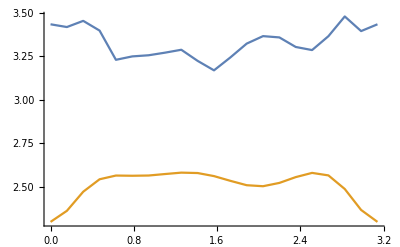

```mathematica
ListLinePlot[{fibo16max,fibo16mean}]
```

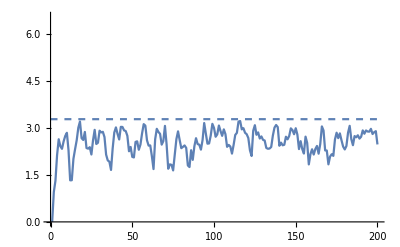

```mathematica
Show[Plot[0*x+c/.{c->3.281937853012085},{x,0,200},PlotStyle->Dashed],ListLinePlot[fibo16n[[10]]]]
```

## dt = pi/32

#### data

```mathematica
fibo32={-0.000000000000000000*10^+00,1.783237203716265151*10^+00,3.182047635131918017*10^+00,2.786261322049267353*10^+00,1.709500059728747745*10^+00,1.141181760580191717*10^+00,2.257576956705447557*10^+00,3.308199346626300663*10^+00,2.483882067408824668*10^+00,1.766898676851285765*10^+00,1.225305234852103631*10^+00,2.013337544092612674*10^+00,2.646797933266201053*10^+00,2.211518400924101790*10^+00,2.287995760277847790*10^+00,1.416897564057507442*10^+00,1.620822884402356001*10^+00,2.493132326213851613*10^+00,2.326906065621400010*10^+00,2.527535986337223317*10^+00,1.903802547042714011*10^+00,1.284568541656263774*10^+00,1.867609120145417467*10^+00,2.279937707650244505*10^+00,3.234153555910284972*10^+00,2.227009704198227968*10^+00,1.112871037882227299*10^+00,1.559403675620334884*10^+00,2.596363425598222197*10^+00,3.059533134872128191*10^+00,1.933881999193080681*10^+00,3.852543872869030883*10^-01,2.164947531179810980*10^+00,3.740176445132295413*10^+00,2.445785862643979236*10^+00,1.250245238389681823*10^+00,1.056648039603180766*10^+00,1.794031787861201765*10^+00,2.438720955300365922*10^+00,2.644602494393771597*10^+00,2.257634798533197262*10^+00,1.178409000604983436*10^+00,1.873242973476327844*10^+00,3.289856817765162145*10^+00,2.387707139531514589*10^+00,1.491344878844528044*10^+00,2.286212317645631931*10^+00,2.288408941346085079*10^+00,2.507199235049068164*10^+00,2.281434627548895477*10^+00,1.966335319922489111*10^+00,1.909273695718245456*10^+00,1.302513121432026466*10^+00,2.480250454675241301*10^+00,3.057842849447903522*10^+00,2.223704990365444889*10^+00,2.120601879733922779*10^+00,1.812947591901505229*10^+00,2.024237563653909167*10^+00,2.608726888789807852*10^+00,2.814727086229917852*10^+00,1.936283451996181348*10^+00,1.534817531985079864*10^+00,2.297529084828487722*10^+00,3.075021536039805881*10^+00,2.628793171271637252*10^+00,1.791057789815894807*10^+00,2.104022941711924499*10^+00,2.425431798479661172*10^+00,3.138886976157245545*10^+00,2.594552098181373001*10^+00,1.667630168486987419*10^+00,1.908666192183947841*10^+00,2.345356206429839663*10^+00,3.284495680095924186*10^+00,2.685311063678147647*10^+00,1.735381187810938641*10^+00,2.058893989641262134*10^+00,2.087517700979475421*10^+00,2.740831568121600448*10^+00,2.160132660679053185*10^+00,1.681509384705885735*10^+00,2.040397522063707836*10^+00,1.967756229888225850*10^+00,2.493230309050534554*10^+00,2.940966417695030977*10^+00,2.265180823255871889*10^+00,2.023922825635301237*10^+00,2.151760668224109274*10^+00,2.245812079463209709*10^+00,2.301306187234796852*10^+00,2.281016790013071116*10^+00,1.472946757675304141*10^+00,1.151928164427939549*10^+00,2.095854778002724128*10^+00,3.572703186733607872*10^+00,2.496041666065275777*10^+00,1.225701937263121932*10^+00,2.116244077370244447*10^+00,2.687860027601480795*10^+00,2.623307528807520939*10^+00,1.968248236698442399*10^+00,9.813008357887047506*10^-01,2.136935959557461295*10^+00,2.914954096198624445*10^+00,2.397242339457357208*10^+00,1.792427842015462680*10^+00,1.340070723143297338*10^+00,2.445558966182859173*10^+00,3.223669773198129196*10^+00,2.186138237187521760*10^+00,1.850834550164005998*10^+00,2.098561332523848133*10^+00,2.088503454610525889*10^+00,1.985043859967134727*10^+00,2.342525129013826923*10^+00,2.583467777778116314*10^+00,1.919269204433217135*10^+00,1.957418246027755604*10^+00,2.326998642973046039*10^+00,2.288556180667066897*10^+00,2.503447036951058191*10^+00,2.513465626767839911*10^+00,2.213280023348434433*10^+00,2.575500103775302918*10^+00,2.582361141228743051*10^+00,2.405210901692769632*10^+00,2.437250108879557953*10^+00,1.668542527464410563*10^+00,2.429600990356044043*10^+00,3.008968845074452059*10^+00,2.215085363785557426*10^+00,1.731158390725949348*10^+00,1.473288949580967122*10^+00,2.302689587201215193*10^+00,3.143002059343764198*10^+00,2.332267697929774286*10^+00,1.549644999750561025*10^+00,1.717701539772361619*10^+00,2.825375295397931197*10^+00,2.700131951312275014*10^+00,2.163415172308670975*10^+00,1.804424400623972691*10^+00,2.334757842511315573*10^+00,2.629162402064173065*10^+00,2.366510757115527053*10^+00,1.999312075283814938*10^+00,2.365828958188837650*10^+00,1.777299155303141642*10^+00,1.740810268420174722*10^+00,2.351689633031473825*10^+00,2.539602048729406647*10^+00,2.187758862503636159*10^+00,2.502909061165031090*10^+00,2.280562721632847456*10^+00,2.720941054831969019*10^+00,2.798636077302695035*10^+00,2.090658426312515417*10^+00,1.990467704202823374*10^+00,2.242998634255307877*10^+00,2.285235502540807317*10^+00,2.317989505958126362*10^+00,2.575939269671613463*10^+00,2.537534475716981763*10^+00,2.386111905799258359*10^+00,2.945687805948753457*10^+00,2.895641054374867185*10^+00,2.173710230131284504*10^+00,1.562317881135105280*10^+00,1.838898963426338407*10^+00,2.394763092414356809*10^+00,3.193683520822941713*10^+00,1.984581574042817653*10^+00,1.480352837756481632*10^+00,1.995963982934052527*10^+00,2.431780238917585546*10^+00,2.769508628145707085*10^+00,2.481015290934501571*10^+00,1.344305981216371126*10^+00,2.076606126213425885*10^+00,2.386117620447044008*10^+00,2.529321988187785308*10^+00,2.278761665129820368*10^+00,2.072939664756908051*10^+00,2.271774573868375668*10^+00,2.570565294567581649*10^+00,2.164289788136257275*10^+00,2.497337569032529458*10^+00,1.891369075703969393*10^+00,1.864419613011348398*10^+00,2.068197428681112893*10^+00,2.145848268571129314*10^+00,2.879324837635446777*10^+00,2.120446870039469189*10^+00,1.267195470119040435*10^+00,1.860773162231439404*10^+00,2.671614184102728995*10^+00,3.318099993839411788*10^+00,2.023871023489136611*10^+00,8.524718918275897561*10^-01,2.722912528242654327*10^-14,1.780820731443532701*10^+00,3.172709821302190036*10^+00,2.835105060145899358*10^+00,1.926198493852980143*10^+00,1.390238582125548961*10^+00,2.384054761790580290*10^+00,3.318683073492179947*10^+00,2.483001491344271727*10^+00,1.822226320557438495*10^+00,1.277712047570988441*10^+00,2.043407633757857944*10^+00,2.693691370632468995*10^+00,2.342545748346103629*10^+00,2.414658224856800928*10^+00,1.680447561187576433*10^+00,1.872670972486894847*10^+00,2.635972656018314098*10^+00,2.402159312036589611*10^+00,2.504928242999015620*10^+00,1.932728821610252945*10^+00,1.390617882913860903*10^+00,1.935612715488078894*10^+00,2.319838170233364139*10^+00,3.226274331228190739*10^+00,2.370288609651640677*10^+00,1.330373831800693685*10^+00,1.727832077824565271*10^+00,2.614051594646460863*10^+00,3.020325499270593017*10^+00,1.939127905525416917*10^+00,4.432506658010928469*10^-01,2.148721735511341713*10^+00,3.645571720362609902*10^+00,2.573644760700481982*10^+00,1.487381127650897916*10^+00,1.269438058278894887*10^+00,1.943037907633089034*10^+00,2.530517826876339527*10^+00,2.673563782602709882*10^+00,2.209632944146764810*10^+00,1.134827735288745698*10^+00,1.838521170341393951*10^+00,3.261113287235534397*10^+00,2.462052437552948447*10^+00,1.637458102747318067*10^+00,2.383277943868800985*10^+00,2.406623429133467607*10^+00,2.533486744409887859*10^+00,2.283479161509378130*10^+00,2.024790687919661991*10^+00,1.957908592475811060*10^+00,1.453931688153114798*10^+00,2.559819541869758464*10^+00,3.006352010940398500*10^+00,2.241199339595123519*10^+00,2.209254752426261792*10^+00,1.892440916909465809*10^+00,2.048232176695131912*10^+00,2.613322055973863023*10^+00,2.860912802953357925*10^+00,2.140768241920233628*10^+00,1.830646374126206011*10^+00,2.454184603428876787*10^+00,3.105325215214227441*10^+00,2.654709098178122950*10^+00,1.882627491080563598*10^+00,2.210862899762248368*10^+00,2.522685225134356557*10^+00,3.177872328840716243*10^+00,2.729678501104801924*10^+00,1.888878082537260861*10^+00,2.133056357809593795*10^+00,2.544778060154595067*10^+00,3.345509732149463122*10^+00,2.794324317400161295*10^+00,1.938081325421237455*10^+00,2.224586388549585791*10^+00,2.271500893268445065*10^+00,2.801160098473085558*10^+00,2.225660126329542354*10^+00,1.825810347657467414*10^+00,2.150940812336486818*10^+00,2.042914536375787016*10^+00,2.513786099975214405*10^+00,2.870699260960701604*10^+00,2.263017946484709775*10^+00,2.095142142831527110*10^+00,2.227985315811814804*10^+00,2.278981967205193637*10^+00,2.318977897893026441*10^+00,2.363614470229658870*10^+00,1.628991504410796320*10^+00,1.234138763853514842*10^+00,2.120563423515488655*10^+00,3.471057772013577125*10^+00,2.552815099213201044*10^+00,1.397188320388840888*10^+00,2.178925908697709968*10^+00,2.665708249955532239*10^+00,2.606919715654518743*10^+00,2.144830269326322369*10^+00,1.189469985955316833*10^+00,2.269947743250164685*10^+00,2.970967290384695314*10^+00,2.496670200565166198*10^+00,1.965433471627253237*10^+00,1.547449375831012164*10^+00,2.584957147608204053*10^+00,3.201179279381657139*10^+00,2.207319003676863289*10^+00,1.923981894449774410*10^+00,2.049444168895178553*10^+00,2.046938221522367041*10^+00,1.963381317281694738*10^+00,2.342425111905011015*10^+00,2.597676200727931484*10^+00,2.046755488280091129*10^+00,2.143965709504232819*10^+00,2.454653722382347691*10^+00,2.296566608110626184*10^+00,2.449753951667800855*10^+00,2.515912700138640545*10^+00,2.301691757176107522*10^+00,2.626430678541249897*10^+00,2.642549553317345534*10^+00,2.487241334974657381*10^+00,2.528396533404213109*10^+00,1.784076913657484109*10^+00,2.443488361946133391*10^+00,2.924582554167866721*10^+00,2.238685734310204900*10^+00,1.897087344457315528*10^+00,1.742103973669252959*10^+00,2.403895801413052702*10^+00,3.086271083898950440*10^+00,2.312953587586092929*10^+00,1.599941781578986699*10^+00,1.780602384509502922*10^+00,2.819859765310797961*10^+00,2.689841559665000936*10^+00,2.253744008649472885*10^+00,1.958656873813870103*10^+00,2.496653811051999572*10^+00,2.765010912176718350*10^+00,2.510377142748015711*10^+00,2.157560092801930729*10^+00,2.344303600334244564*10^+00,1.833298373706268247*10^+00,1.836235434860824078*10^+00,2.409758767607150798*10^+00,2.625876426725785695*10^+00,2.351076997254774703*10^+00,2.642117562058348135*10^+00,2.449459786490427948*10^+00,2.747471322533557192*10^+00,2.786387220106868678*10^+00,2.215454564836556450*10^+00,2.132775312766550968*10^+00,2.402946106586802522*10^+00,2.467610174878550389*10^+00,2.445861671939876025*10^+00,2.652195978938624243*10^+00,2.613663148280719106*10^+00,2.443434734671087849*10^+00,2.932148286473974075*10^+00,2.887782776335144685*10^+00,2.327630491952789704*10^+00,1.793518311890657912*10^+00,1.941788802713054318*10^+00,2.423174869951192800*10^+00,3.126698133689569392*10^+00,2.046756690047907945*10^+00,1.574353802791670143*10^+00,2.121749420340026671*10^+00,2.559625567848982985*10^+00,2.882194601385367427*10^+00,2.527234978048508829*10^+00,1.408434273892673616*10^+00,2.120164913682556662*10^+00,2.429003497908584386*10^+00,2.544408173350159341*10^+00,2.295346380413909593*10^+00,2.095761460517040486*10^+00,2.396464858200118009*10^+00,2.685292349226627628*10^+00,2.308235945505664688*10^+00,2.511689050147090541*10^+00,1.914768876093237759*10^+00,1.885087697885529323*10^+00,2.121937376667323516*10^+00,2.176652063502877432*10^+00,2.874491535013898424*10^+00,2.257947821457973347*10^+00,1.481767971358304958*10^+00,2.021853109652794522*10^+00,2.696326357428771914*10^+00,3.276415605684820598*10^+00,2.112101967616511367*10^+00,1.042231697953753811*10^+00,-9.610279511444755881*10^-16,1.773812292304951299*10^+00,3.146865446041712033*10^+00,2.933335135967372498*10^+00,2.278340139887657934*10^+00,1.871654910994268617*10^+00,2.603141084811645634*10^+00,3.271010617374064289*10^+00,2.487997468708311732*10^+00,1.910648229626478622*10^+00,1.420138089925560010*10^+00,2.120366585026518980*10^+00,2.753570617141566590*10^+00,2.549965092872058747*10^+00,2.543018735717543333*10^+00,2.052255060033898459*10^+00,2.286045367756731839*10^+00,2.864823977159557167*10^+00,2.531011079581590995*10^+00,2.467170715938316494*10^+00,1.994974895185334995*10^+00,1.669675560816902049*10^+00,2.151460034141917443*10^+00,2.410397180221594660*10^+00,3.179388219849589969*10^+00,2.611067769914883208*10^+00,1.803532032706771426*10^+00,2.012260263385378778*10^+00,2.624454591002786774*10^+00,2.929928261465304828*10^+00,1.936995247566386080*10^+00,6.728797452646763100*10^-01,2.115572037191748578*10^+00,3.402157410499797585*10^+00,2.786126695457643798*10^+00,1.913757140714761551*10^+00,1.650919392809937936*10^+00,2.199897931802746509*10^+00,2.695011505368122506*10^+00,2.736628366287783720*10^+00,2.123920155221173278*10^+00,1.048516301647597126*10^+00,1.742327703556219021*10^+00,3.162729790994633916*10^+00,2.606193112160610337*10^+00,1.933284143617729267*10^+00,2.567496900174940144*10^+00,2.616429625924310720*10^+00,2.561068339976979136*10^+00,2.295300681747180604*10^+00,2.153754459934888121*10^+00,1.993250125940404516*10^+00,1.731979368145851517*10^+00,2.701479575545720380*10^+00,2.917799116797292758*10^+00,2.279050157743983451*10^+00,2.391163557752390645*10^+00,2.115857090108336891*10^+00,2.158050897534409707*10^+00,2.566797846800723981*10^+00,2.892054923745664752*10^+00,2.479429385111628914*10^+00,2.365866922547113393*10^+00,2.622018084888318334*10^+00,3.117353474673739910*10^+00,2.734503522903493966*10^+00,2.122529634441459478*10^+00,2.434636698989655734*10^+00,2.700994270242457862*10^+00,3.191756850548618907*10^+00,2.887074921725356624*10^+00,2.269257279244558667*10^+00,2.502101092233828705*10^+00,2.847984817527945633*10^+00,3.401859370168278218*10^+00,2.969408991526818919*10^+00,2.292334775289379234*10^+00,2.506695358657772932*10^+00,2.542933543003941477*10^+00,2.885172888313317863*10^+00,2.356778149800700994*10^+00,2.078829061231058262*10^+00,2.388337840364968656*10^+00,2.197349725211514393*10^+00,2.544458155177500736*10^+00,2.690262371998627167*10^+00,2.217754482262682458*10^+00,2.244515278152795723*10^+00,2.383776440789178608*10^+00,2.342045675454726528*10^+00,2.343947294890354360*10^+00,2.563922072995459267*10^+00,1.945050607258729691*10^+00,1.494058649297485442*10^+00,2.163412497533023782*10^+00,3.238118540898817788*10^+00,2.676497291915970855*10^+00,1.773755476439809131*10^+00,2.295273256114904292*10^+00,2.578341780088169166*10^+00,2.582325058927022798*10^+00,2.456073400602123424*10^+00,1.625934995776588288*10^+00,2.466252414855474306*10^+00,3.018222241263113670*10^+00,2.654108109993713605*10^+00,2.275281458893924746*10^+00,1.954604595035553727*10^+00,2.838031930537561198*10^+00,3.192115213980241339*10^+00,2.287167171226766271*10^+00,2.116192157106309590*10^+00,1.923167409159575181*10^+00,1.937826149711626700*10^+00,1.897724111717396189*10^+00,2.351101704906898515*10^+00,2.674493428161441422*10^+00,2.282379987923877529*10^+00,2.473163537626382524*10^+00,2.718910571002395304*10^+00,2.346197778442384418*10^+00,2.322442335724450135*10^+00,2.500781750262677239*10^+00,2.501864994897224470*10^+00,2.696203769608080059*10^+00,2.692266901596521933*10^+00,2.609841655188400722*10^+00,2.693907661759300076*10^+00,2.055752686572464683*10^+00,2.487215605491293058*10^+00,2.707342123602366701*10^+00,2.243391289678414058*10^+00,2.185532408438562335*10^+00,2.269576100699967736*10^+00,2.580285638881357979*10^+00,2.979145994778089168*10^+00,2.312628134326176088*10^+00,1.787783654380401765*10^+00,2.008448087069123478*10^+00,2.781838497363046336*10^+00,2.634581652933960960*10^+00,2.376827647979676605*10^+00,2.275521662759056873*10^+00,2.796434337698672667*10^+00,2.992100091194567657*10^+00,2.819461571500753827*10^+00,2.403692767289804078*10^+00,2.230200215414156251*10^+00,1.925328433581864340*10^+00,1.997887269773292784*10^+00,2.533313115659901804*10^+00,2.820459146648511606*10^+00,2.552155514273783510*10^+00,2.822544365064905580*10^+00,2.748073555856344719*10^+00,2.754010012160607701*10^+00,2.704342012176504717*10^+00,2.409127041541947012*10^+00,2.407754430825372882*10^+00,2.694594049125481838*10^+00,2.782874059780954923*10^+00,2.675342195010794732*10^+00,2.819089734262123947*10^+00,2.723696306816952184*10^+00,2.573223030160348923*10^+00,2.870693642132937207*10^+00,2.900022745026506144*10^+00,2.611943473147370298*10^+00,2.218199337274058713*10^+00,2.169673968447336954*10^+00,2.492140848537278242*10^+00,2.949884444079436285*10^+00,2.209537347364353366*10^+00,1.813352153692751045*10^+00,2.360868851809506896*10^+00,2.810654058580476899*10^+00,3.109055253465839996*10^+00,2.613158715643042918*10^+00,1.564084722136420025*10^+00,2.225275502335391842*10^+00,2.549096629658628377*10^+00,2.569066881140721570*10^+00,2.272080833311421078*10^+00,2.195100352525257037*10^+00,2.635572607994204120*10^+00,2.914462906066920489*10^+00,2.537737388167571773*10^+00,2.575655916780307919*10^+00,1.994872011308394422*10^+00,1.927808255157384298*10^+00,2.241971610038646645*10^+00,2.241148480964114231*10^+00,2.859340567696468050*10^+00,2.461134049490090181*10^+00,1.862134928536443024*10^+00,2.278701801533790317*10^+00,2.718576313194932759*10^+00,3.156880940189630724*10^+00,2.345471513734027624*10^+00,1.446754451625542170*10^+00,9.610279511444749964*10^-16,1.762909576435358838*10^+00,3.110216771039668426*10^+00,2.964206070944964466*10^+00,2.598728771841002150*10^+00,2.367483312844433474*10^+00,2.716319331645354662*10^+00,3.078968365321971046*10^+00,2.444526656653879471*10^+00,1.944990395146791284*10^+00,1.516470821140137648*10^+00,2.164174383335283114*10^+00,2.789003806472906799*10^+00,2.677151472061665594*10^+00,2.576692514071876161*10^+00,2.309402774814872217*10^+00,2.609884359716679203*10^+00,2.979137570690815195*10^+00,2.633700338337701119*10^+00,2.491436597340690007*10^+00,2.073602784864545079*10^+00,1.920912463286859273*10^+00,2.409092413184103165*10^+00,2.534900326373236368*10^+00,3.056543597714139970*10^+00,2.792404183068128543*10^+00,2.178932596762753526*10^+00,2.236464008552953686*10^+00,2.660644032314088303*10^+00,2.837171217232579146*10^+00,1.964614669605902364*10^+00,1.017952764996722159*10^+00,2.128126321173312796*10^+00,3.098494255317026713*10^+00,2.888316277044805869*10^+00,2.276794167984903527*10^+00,1.991650589322303766*10^+00,2.397751219712912274*10^+00,2.788061725176067984*10^+00,2.783539910232428305*10^+00,2.097670932372139418*10^+00,9.892971988744740930*10^-01,1.660416047611128043*10^+00,2.992393970027426242*10^+00,2.705023950052386716*10^+00,2.222104449092600298*10^+00,2.706921124108438104*10^+00,2.779005382007690095*10^+00,2.589703207722937606*10^+00,2.355267836176797580*10^+00,2.257249235346558525*10^+00,1.922927209538610294*10^+00,1.885536324390680640*10^+00,2.829512252123954408*10^+00,2.967957108885302286*10^+00,2.351309910563743166*10^+00,2.622582217513041769*10^+00,2.395904988437520977*10^+00,2.302347094677905215*10^+00,2.480964611602742842*10^+00,2.768023622153972241*10^+00,2.700917857294031332*10^+00,2.839228723826873413*10^+00,2.679885445203390670*10^+00,3.024140395306710527*10^+00,2.811655209258772103*10^+00,2.433625022346570521*10^+00,2.677165771586483167*10^+00,2.791686872766699690*10^+00,3.032660269057282143*10^+00,2.913232483179882149*10^+00,2.573968732135798909*10^+00,2.754632207895418183*10^+00,2.997791084923366434*10^+00,3.340607766006000734*10^+00,3.095143063475441991*10^+00,2.578403238494582084*10^+00,2.646192860295642379*10^+00,2.688992309480648046*10^+00,2.865532220934260188*10^+00,2.445332422334252520*10^+00,2.316480021452959726*10^+00,2.586903450646647062*10^+00,2.322466809783136910*10^+00,2.543653678338523516*10^+00,2.474979761846289428*10^+00,2.154591109508730007*10^+00,2.413303877893491656*10^+00,2.534390771932309327*10^+00,2.357470456837674533*10^+00,2.380782454243673296*10^+00,2.788356366430607913*10^+00,2.272737487585941185*10^+00,1.769007607793425141*10^+00,2.204376967137496202*10^+00,3.029114355265000835*10^+00,2.802438002060994915*10^+00,2.112083112568908128*10^+00,2.372967233614199145*10^+00,2.492576578037005053*10^+00,2.576620985891918014*10^+00,2.722057595971796751*10^+00,2.094245718212566665*10^+00,2.576642569249978365*10^+00,2.928539322038339776*10^+00,2.711055789087704060*10^+00,2.565000951719034639*10^+00,2.349400871867927787*10^+00,3.071092673836114617*10^+00,3.164812849284697194*10^+00,2.388190235002847217*10^+00,2.423135927151242708*10^+00,1.840895046417540648*10^+00,1.767436651398972991*10^+00,1.782678453710937472*10^+00,2.372483881127459782*10^+00,2.787855780936883132*10^+00,2.460404732529422045*10^+00,2.727426000749638924*10^+00,2.952471427502332268*10^+00,2.442331862961607314*10^+00,2.292076717974989020*10^+00,2.492641439611691823*10^+00,2.626991107069514442*10^+00,2.738512192143217394*10^+00,2.704682969280367999*10^+00,2.679316028645169823*10^+00,2.809954305296513688*10^+00,2.334813790157387992*10^+00,2.522277574358308350*10^+00,2.449811791827697149*10^+00,2.130277876350236799*10^+00,2.377332543614396609*10^+00,2.705704117911599038*10^+00,2.791497338111134763*10^+00,2.941029592959032879*10^+00,2.379874709761862661*10^+00,2.095887083704619513*10^+00,2.338087906700315965*10^+00,2.664262366229761536*10^+00,2.485126485557315412*10^+00,2.464173911877799661*10^+00,2.631856484471822633*10^+00,3.063180566919363468*10^+00,3.123605429708296466*10^+00,3.062298402452362733*10^+00,2.588194337565705716*10^+00,2.003453886550233154*10^+00,1.930425390259784102*10^+00,2.116140815795136909*10^+00,2.601002012399709518*10^+00,2.970589576409772725*10^+00,2.644370289449796019*10^+00,2.916152921960803113*10^+00,2.967595490481032883*10^+00,2.743689461348750580*10^+00,2.609432856048826466*10^+00,2.522905550700439647*10^+00,2.602676083987863986*10^+00,2.905178736526777605*10^+00,2.987612961177191107*10^+00,2.821461464991497969*10^+00,2.914495423052733791*10^+00,2.788830388555526785*10^+00,2.723671631565213858*10^+00,2.781185033932409567*10^+00,2.870129073931556363*10^+00,2.821912272113267228*10^+00,2.577537366224353477*10^+00,2.337553711107287047*10^+00,2.523811637946910658*10^+00,2.777569173370456834*10^+00,2.376091867314003458*10^+00,2.107366685176701893*10^+00,2.577875728799611466*10^+00,3.010416803503159322*10^+00,3.267171962032907384*10^+00,2.652775468201040709*10^+00,1.705243826775532101*10^+00,2.349677956350193053*10^+00,2.725744905808889396*10^+00,2.569131183770167137*10^+00,2.258275669181533107*10^+00,2.344629471050626801*10^+00,2.815375604508786544*10^+00,3.029864471496882317*10^+00,2.663404277383606189*10^+00,2.637105052050505716*10^+00,2.061511249146485092*10^+00,1.963564549782921720*10^+00,2.369539906440018218*10^+00,2.315267706527663449*10^+00,2.790870194214523536*10^+00,2.492296410432607523*10^+00,2.128982006371364477*10^+00,2.476242156819592477*10^+00,2.707325389421750828*10^+00,2.999746070889176774*10^+00,2.580475712842899227*10^+00,1.870144534741645881*10^+00,4.805139755722374982*10^-16,1.749194328010244437*10^+00,3.070008517655494096*10^+00,2.924735042266668472*10^+00,2.812010769827548717*10^+00,2.764431300673264147*10^+00,2.719339241468443191*10^+00,2.778690962761696248*10^+00,2.394874012975277022*10^+00,1.907927112736361286*10^+00,1.554007984658449359*10^+00,2.216582180097942611*10^+00,2.817306564125209967*10^+00,2.741391168419567315*10^+00,2.562556285441112358*10^+00,2.450933222701659808*10^+00,2.759815226901165541*10^+00,2.932040226553812357*10^+00,2.679139784225194276*10^+00,2.574236893356252942*10^+00,2.211200812103417235*10^+00,2.100101685562275389*10^+00,2.646316450683568799*10^+00,2.668609458864910522*10^+00,2.912200469547658876*10^+00,2.838588105383802240*10^+00,2.389147571520583657*10^+00,2.367377386280278273*10^+00,2.736117801452975229*10^+00,2.770176881812196346*10^+00,1.990361284552031984*10^+00,1.422258047258625480*10^+00,2.254888376226312552*10^+00,2.866942252551880621*10^+00,2.860632795228095659*10^+00,2.495603311670745228*10^+00,2.266374964222140242*10^+00,2.507263221483569282*10^+00,2.778849625440531490*10^+00,2.790930193385852132*10^+00,2.146109398570845705*10^+00,9.893174373764290763*10^-01,1.627992061653291689*10^+00,2.798676623629885007*10^+00,2.717445368083228452*10^+00,2.450591236024663999*10^+00,2.775242647358024062*10^+00,2.805686469522219895*10^+00,2.581113548692544946*10^+00,2.513023783976979786*10^+00,2.325657816921191667*10^+00,1.753204937799664798*10^+00,1.904558869973009827*10^+00,2.920892023533170789*10^+00,3.140268588399936611*10^+00,2.449850367737265167*10^+00,2.787217462934070245*10^+00,2.657693588477984648*10^+00,2.413408316307744439*10^+00,2.376059568199355265*10^+00,2.547600517112546648*10^+00,2.747745025525813123*10^+00,3.176612048536862076*10^+00,2.653996963048224078*10^+00,2.896408742625393717*10^+00,2.898883249353441105*10^+00,2.720709040706971393*10^+00,2.867875419770710366*10^+00,2.752130090732813450*10^+00,2.761782519773239741*10^+00,2.812806266328859106*10^+00,2.756660746487440861*10^+00,2.933134829332027849*10^+00,2.952476884104436206*10^+00,3.190892532983401253*10^+00,3.143203220503435258*10^+00,2.769358918169733563*10^+00,2.661342184878769057*10^+00,2.700210724449522814*10^+00,2.718029383003557786*10^+00,2.418726912734001644*10^+00,2.493680889161467906*10^+00,2.697518233595426640*10^+00,2.377237317565317642*10^+00,2.564095997638252911*10^+00,2.406910918601298910*10^+00,2.206037178571812252*10^+00,2.542376242807488751*10^+00,2.583062299291450703*10^+00,2.288949352327625419*10^+00,2.402357824501025529*10^+00,2.951340784573143861*10^+00,2.501773525589129576*10^+00,2.015791864607264561*10^+00,2.287737563313585021*10^+00,2.931623165610129256*10^+00,2.887207691628160156*10^+00,2.319768416869452121*10^+00,2.369111889102454072*10^+00,2.482269192837875060*10^+00,2.643763081532314096*10^+00,2.912743613054828984*10^+00,2.442163501460199448*10^+00,2.654633263026042300*10^+00,2.738102891104284176*10^+00,2.661373152575890355*10^+00,2.731708621925979852*10^+00,2.663342837970228860*10^+00,3.217746423951026724*10^+00,3.067427416447326305*10^+00,2.462451532557470291*10^+00,2.792577005245043154*10^+00,1.907580223940389175*10^+00,1.565720704264395913*10^+00,1.653838301831377366*10^+00,2.385512996909219030*10^+00,2.890075977869345891*10^+00,2.559833070676302391*10^+00,2.837178740929109821*10^+00,3.048563780678762214*10^+00,2.543642832414616084*10^+00,2.395500129909531761*10^+00,2.471950331837640569*10^+00,2.633336793494755135*10^+00,2.715725768125172301*10^+00,2.713297525207263750*10^+00,2.761272115040589004*10^+00,2.844529959078769821*10^+00,2.505617126604762213*10^+00,2.560436458749314248*10^+00,2.252942091057889229*10^+00,1.974744534615856972*10^+00,2.485038763933925310*10^+00,2.974601731642346536*10^+00,3.030787760092344296*10^+00,2.928999543353094204*10^+00,2.429220468135984135*10^+00,2.366681211992028633*10^+00,2.621425042663811045*10^+00,2.512803433284878096*10^+00,2.277414083035346426*10^+00,2.532753121618659620*10^+00,2.925344054663389315*10^+00,3.183220369646888592*10^+00,3.094514266451543705*10^+00,3.164835353596240353*10^+00,2.678358013307922114*10^+00,1.844211724094955596*10^+00,1.884492221103399423*10^+00,2.149462881456003949*10^+00,2.597503915583885714*10^+00,2.993049566723502863*10^+00,2.680888057326375584*10^+00,2.928757405442185657*10^+00,3.030094334539603196*10^+00,2.722737747705351818*10^+00,2.596118977343412570*10^+00,2.570831472771504700*10^+00,2.667869792020357345*10^+00,2.990155277064481254*10^+00,2.998799563863586926*10^+00,2.808651139251330697*10^+00,2.872190211065475562*10^+00,2.818951437530661241*10^+00,2.878504805737781780*10^+00,2.754022122077378842*10^+00,2.861770957716448294*10^+00,2.932763253131345227*10^+00,2.731385830348729726*10^+00,2.382698107190700298*10^+00,2.485544376967340874*10^+00,2.660972283860845167*10^+00,2.531272130345583626*10^+00,2.400176546752853746*10^+00,2.746442628422457233*10^+00,3.135240590736076527*10^+00,3.270619983582614410*10^+00,2.564687858077844496*10^+00,1.766614129823176782*10^+00,2.455927398097940362*10^+00,2.873346870710958179*10^+00,2.576222322002554854*10^+00,2.390955457406320761*10^+00,2.581172225580299795*10^+00,2.897906743465563650*10^+00,2.913499092306917948*10^+00,2.618047007913683277*10^+00,2.663854433489209583*10^+00,2.113908211508612300*10^+00,2.005899764706623234*10^+00,2.468754237729889667*10^+00,2.401850682562975514*10^+00,2.703674573580441720*10^+00,2.349784181601585864*10^+00,2.225015640445750620*10^+00,2.566482418429254064*10^+00,2.671232317592429073*10^+00,2.875173506244189880*10^+00,2.756201218306910672*10^+00,2.175288481975747423*10^+00,3.203426503814917641*10^-16,1.734020978688510350*10^+00,3.032858342315564393*10^+00,2.836614527198626057*10^+00,2.937201754597188685*10^+00,3.026251592941645363*10^+00,2.712589263154553176*10^+00,2.565877282962624406*10^+00,2.364998559023870683*10^+00,1.832949296075068180*10^+00,1.567372798058609185*10^+00,2.332996696948675286*10^+00,2.925498850478271073*10^+00,2.778601053058816994*10^+00,2.605023664866815913*10^+00,2.561916526699950403*10^+00,2.778109214625391843*10^+00,2.809847553612482951*10^+00,2.693121875451451874*10^+00,2.707944483190116713*10^+00,2.401091309268812868*10^+00,2.267232833366713329*10^+00,2.822774987535538571*10^+00,2.744725810982039604*10^+00,2.779831219248359631*10^+00,2.796666154112248392*10^+00,2.484586244809515510*10^+00,2.445797167286771767*10^+00,2.841869503402878472*10^+00,2.751612620614678928*10^+00,1.970704952250192710*10^+00,1.764657952370953797*10^+00,2.456908443113230422*10^+00,2.760215188106470041*10^+00,2.773522039346989043*10^+00,2.589250339859920036*10^+00,2.461054879948177287*10^+00,2.551736096805787390*10^+00,2.695553879746709569*10^+00,2.783837099557049388*10^+00,2.234244015124654759*10^+00,1.062839671422308951*10^+00,1.645655646654507809*10^+00,2.654957495777043430*10^+00,2.714071940265305294*10^+00,2.605412065690830836*10^+00,2.805875669521116667*10^+00,2.728231755406730130*10^+00,2.584232215997493753*10^+00,2.720328029480548082*10^+00,2.447222109790367917*10^+00,1.732109135117311460*10^+00,1.869895664450610617*10^+00,2.966365658993081134*10^+00,3.285402377638753091*10^+00,2.587096293323085661*10^+00,2.881343483267004402*10^+00,2.813522962673856931*10^+00,2.509492187382734052*10^+00,2.363346981929686397*10^+00,2.362558775729159954*10^+00,2.692391211166603959*10^+00,3.307293097421441619*10^+00,2.580946108892589130*10^+00,2.768012158183927873*10^+00,3.009878425203195373*10^+00,2.932366745299363586*10^+00,2.982304229244753913*10^+00,2.659412431217038630*10^+00,2.499531756992566578*10^+00,2.674700927467243528*10^+00,2.847117478972221338*10^+00,3.068025388605422066*10^+00,2.858339938046016826*10^+00,3.022352874232325348*10^+00,3.126386817803758156*10^+00,2.876473076023563280*10^+00,2.663726837294522642*10^+00,2.661355488151472493*10^+00,2.491816981567145373*10^+00,2.296632341445715042*10^+00,2.638242159171606538*10^+00,2.769351455090984349*10^+00,2.362974186713096447*10^+00,2.606306113140736791*10^+00,2.548997860637605584*10^+00,2.401294822477066937*10^+00,2.601732515361019349*10^+00,2.525112891912495883*10^+00,2.218240608729125540*10^+00,2.480289194191656943*10^+00,3.071557272050717380*10^+00,2.678702969596214789*10^+00,2.217193469005044992*10^+00,2.401733037598027920*10^+00,2.907640714877255395*10^+00,2.893093403661654683*10^+00,2.342721863924677628*10^+00,2.287983709146332423*10^+00,2.530112662066416274*10^+00,2.788814837721238060*10^+00,3.026412272453928853*10^+00,2.666567924326247230*10^+00,2.785328927234738128*10^+00,2.578869594148391009*10^+00,2.556207215499634700*10^+00,2.793421425935584512*10^+00,2.843838042468336713*10^+00,3.284737517640518245*10^+00,2.892052915527798529*10^+00,2.521251360158866639*10^+00,3.128308222953083639*10^+00,2.152699699702112834*10^+00,1.422428046401844171*10^+00,1.536162608718817157*10^+00,2.382606234272767409*10^+00,2.946419379976512154*10^+00,2.618274372862326782*10^+00,2.865264059825748610*10^+00,3.033258282449430077*10^+00,2.697509559952734115*10^+00,2.659055003085411872*10^+00,2.530814256066970636*10^+00,2.578569581350131035*10^+00,2.666938907376414036*10^+00,2.766135743763525667*10^+00,2.876805043649703908*10^+00,2.838145289338912747*10^+00,2.558988694365984529*10^+00,2.571918606764183490*10^+00,2.215048141790785241*10^+00,1.993711288718056585*10^+00,2.572952741055048786*10^+00,3.117678088361911737*10^+00,3.237730258923044335*10^+00,2.895315892722390760*10^+00,2.400460946055897882*10^+00,2.539708240022323871*10^+00,2.819964288205709213*10^+00,2.434987102183090002*10^+00,2.172727062805695386*10^+00,2.638463063309248291*10^+00,3.121097241893347363*10^+00,3.165555082575983725*10^+00,2.952839453887958321*10^+00,3.179114287955426832*10^+00,2.705960456569488581*10^+00,1.890070639513415696*10^+00,1.918370006907863523*10^+00,2.153752403665977866*10^+00,2.514344592487000263*10^+00,2.864454925780178574*10^+00,2.725415146912184561*10^+00,2.935497146019055759*10^+00,2.982112923210405775*10^+00,2.737429085239683424*10^+00,2.690303802278099177*10^+00,2.620587788231180770*10^+00,2.654318628398402602*10^+00,2.980768212225826996*10^+00,2.884769638779346224*10^+00,2.725509154460056482*10^+00,2.795913862977175590*10^+00,2.860236572029564162*10^+00,3.028604623784715955*10^+00,2.828131442090799474*10^+00,2.936333771760496703*10^+00,2.986783071846079274*10^+00,2.662104350174910650*10^+00,2.326132355753784520*10^+00,2.430929923342689758*10^+00,2.598740186035405131*10^+00,2.707454426936493519*10^+00,2.694873760052726830*10^+00,2.877795474801368769*10^+00,3.214946882590524524*10^+00,3.145169994192777096*10^+00,2.374388922596349261*10^+00,1.748921278523145606*10^+00,2.550340163345844680*10^+00,3.031348534240571269*10^+00,2.662157177888769599*10^+00,2.589657671161171848*10^+00,2.872500079300746911*10^+00,2.923246061529229500*10^+00,2.707078842956667231*10^+00,2.481093442274932226*10^+00,2.668583441129747325*10^+00,2.158672426088293683*10^+00,2.077148042487228619*10^+00,2.547035829584471056*10^+00,2.497351544572514292*10^+00,2.626691285630341710*10^+00,2.144794903801258368*10^+00,2.195202116801699521*10^+00,2.558495213103870292*10^+00,2.672831976385357855*10^+00,2.882689725771382605*10^+00,2.870350150058599503*10^+00,2.330298326877053405*10^+00,-9.610279511444755881*10^-16,1.718879513406898818*10^+00,3.003369065777209634*10^+00,2.737073379958705477*10^+00,2.977654108899853380*10^+00,3.162390715890235793*10^+00,2.767371389707247165*10^+00,2.523180063676485840*10^+00,2.376587299749026716*10^+00,1.807990548786092333*10^+00,1.566539743993275113*10^+00,2.470457376607910760*10^+00,3.073081199053945944*10^+00,2.840053341598336445*10^+00,2.627878130046363392*10^+00,2.632244401492220387*10^+00,2.765124753849542039*10^+00,2.720817415603477230*10^+00,2.706181507700616162*10^+00,2.800674182525801914*10^+00,2.575216958522219102*10^+00,2.440018652187835979*10^+00,2.919021316011134459*10^+00,2.771815827367198892*10^+00,2.681480641975135804*10^+00,2.757519521668082341*10^+00,2.536746388149490272*10^+00,2.520355410260744833*10^+00,2.984858431565966086*10^+00,2.754309920241148735*10^+00,1.940933314581632096*10^+00,2.002767586662040689*10^+00,2.652985940469572146*10^+00,2.765582089442315095*10^+00,2.705853125740218967*10^+00,2.613569215414252689*10^+00,2.593928436295960704*10^+00,2.556021703254610422*10^+00,2.615135197811257139*10^+00,2.817233439331672251*10^+00,2.308047590862584375*10^+00,1.177389473420551669*10^+00,1.715366220903697947*10^+00,2.589676564705602591*10^+00,2.742696920378570713*10^+00,2.722875301423054673*10^+00,2.827820114106274652*10^+00,2.653196477026783739*10^+00,2.637032592045503332*10^+00,2.957175431425494772*10^+00,2.645358417773670645*10^+00,1.887866862862510597*10^+00,1.913301450941879533*10^+00,2.936797818659745207*10^+00,3.335221767841405782*10^+00,2.734263088438377842*10^+00,2.887361606213390886*10^+00,2.850180269347422524*10^+00,2.604463625521747261*10^+00,2.472075138449601805*10^+00,2.335633338095512102*10^+00,2.713744533285392890*10^+00,3.280691534223556527*10^+00,2.519467159266504552*10^+00,2.748910515320192260*10^+00,3.132705690662333176*10^+00,3.059536920592713649*10^+00,2.994555252174071924*10^+00,2.603846078283769572*10^+00,2.378625104702733584*10^+00,2.617010837240368648*10^+00,2.901276951995593212*10^+00,3.153989186189823712*10^+00,2.781246306035226823*10^+00,2.931774751748764452*10^+00,3.077788721758071500*10^+00,2.906838779370854997*10^+00,2.734924924727288431*10^+00,2.666626873683136445*10^+00,2.263467115618302383*10^+00,2.146978488491029680*10^+00,2.746709972627219276*10^+00,2.803747367315492234*10^+00,2.311373569486256496*10^+00,2.672202494816576124*10^+00,2.768566313784458277*10^+00,2.675485442149937665*10^+00,2.597106272498524770*10^+00,2.416071832582102452*10^+00,2.239791280199096679*10^+00,2.637567608016763376*10^+00,3.173316172703807059*10^+00,2.859394153492602619*10^+00,2.388815168638398934*10^+00,2.487356670799666158*10^+00,2.898359412988597672*10^+00,2.822609061782966222*10^+00,2.266026048540390470*10^+00,2.215858279336969439*10^+00,2.645822159983818533*10^+00,2.988414260866282479*10^+00,3.077683967132425202*10^+00,2.779756284682154188*10^+00,2.882787031690233093*10^+00,2.553890607258293421*10^+00,2.489545849875603345*10^+00,2.763001178071181396*10^+00,2.979183681069510925*10^+00,3.304604593918994748*10^+00,2.711800559033823887*10^+00,2.594890292317563407*10^+00,3.377859066482002071*10^+00,2.475750056688784007*10^+00,1.419014357149597672*10^+00,1.457232739764186213*10^+00,2.336478036764798816*10^+00,2.960355905368341034*10^+00,2.692684912820676235*10^+00,2.901166135109638500*10^+00,2.971373332218058216*10^+00,2.817154573457925082*10^+00,2.962918758660940455*10^+00,2.648118624459509185*10^+00,2.501228228737092163*10^+00,2.595327762146206751*10^+00,2.846178061652953062*10^+00,2.967705065962394695*10^+00,2.839577383464945370*10^+00,2.556817630267279817*10^+00,2.575755993839552005*10^+00,2.355858926840866729*10^+00,2.210505567074728006*10^+00,2.679513460969884520*10^+00,3.199578449195823460*10^+00,3.343504264186179409*10^+00,2.856444392847746538*10^+00,2.305955350390660019*10^+00,2.607763274764790751*10^+00,2.973143526348402954*10^+00,2.499968479050665326*10^+00,2.207187765361130705*10^+00,2.788456293602152858*10^+00,3.207181670272855722*10^+00,3.052310086777826115*10^+00,2.796956764120051009*10^+00,3.124837243685233190*10^+00,2.714355949416111358*10^+00,2.042973089062639414*10^+00,2.066024384373536193*10^+00,2.185146178658120331*10^+00,2.396416598465820780*10^+00,2.658909234762611096*10^+00,2.782081402129696457*10^+00,2.947031791520075661*10^+00,2.901906791583677592*10^+00,2.785625673528048019*10^+00,2.861075790677258812*10^+00,2.698919579186118245*10^+00,2.591833178083033484*10^+00,2.956972768776302996*10^+00,2.785493830155591599*10^+00,2.683527561752547363*10^+00,2.775161270360610111*10^+00,2.938957405705114656*10^+00,3.176138492447268646*10^+00,2.971643710282492634*10^+00,3.064560994992528098*10^+00,2.994352664285654164*10^+00,2.474110902399128342*10^+00,2.223984883805072421*10^+00,2.405865824807845055*10^+00,2.616905639343371170*10^+00,2.929911958451921095*10^+00,2.910620467856396054*10^+00,2.947890872979812116*10^+00,3.264096777586180664*10^+00,2.983242206942003261*10^+00,2.167203875858889628*10^+00,1.681222542716251933*10^+00,2.649427871601285567*10^+00,3.273882826515325029*10^+00,2.803863025665235931*10^+00,2.798113919358179214*10^+00,3.095591413118098600*10^+00,2.903366202229201498*10^+00,2.509991196636111699*10^+00,2.391557618337035951*10^+00,2.646304867403678873*10^+00,2.187940054832060444*10^+00,2.164217806282114687*10^+00,2.637655762725689801*10^+00,2.597130786589710194*10^+00,2.540080612309720376*10^+00,2.028427319877640578*10^+00,2.132070072379284031*10^+00,2.491060284951977621*10^+00,2.684636737146547159*10^+00,2.966104984081143314*10^+00,2.938930317170066697*10^+00,2.397056585712162402*10^+00,-3.203426503814917641*10^-16,1.705247740374219223*10^+00,2.983871378699319621*10^+00,2.730830117006604496*10^+00,2.992246127268713529*10^+00,3.212881302187997168*10^+00,2.856651753955985473*10^+00,2.668080675110847455*10^+00,2.424440479743759536*10^+00,1.819110658982292517*10^+00,1.585327107821596471*10^+00,2.562228369212295576*10^+00,3.155861277257054454*10^+00,2.868286643497319321*10^+00,2.639506184788233067*10^+00,2.633809685591852023*10^+00,2.735220267203899880*10^+00,2.702607589189719217*10^+00,2.749485569816055630*10^+00,2.836278566299413217*10^+00,2.654122033351831611*10^+00,2.595686113043649268*10^+00,2.947108184024548549*10^+00,2.784644228372272323*10^+00,2.644442507125449815*10^+00,2.754674550988676973*10^+00,2.600399249055484585*10^+00,2.605015217063272104*10^+00,3.120128008108600692*10^+00,2.756931414157260285*10^+00,1.922268878867424036*10^+00,2.151836476730110803*10^+00,2.795627486048084087*10^+00,2.819404285431482027*10^+00,2.677152306859841513*10^+00,2.638494336514878302*10^+00,2.663531337790564724*10^+00,2.539175706526641818*10^+00,2.581074137111558198*10^+00,2.868539991659734945*10^+00,2.341853695470572649*10^+00,1.295774490301775383*10^+00,1.817835550163568126*10^+00,2.599859962328450624*10^+00,2.810466582183093642*10^+00,2.755758851258261810*10^+00,2.879957445945603212*10^+00,2.682232522824719023*10^+00,2.728564168563507586*10^+00,3.154027806774600151*10^+00,2.862234871491580179*10^+00,2.114490237315328258*10^+00,1.998892619064667198*10^+00,2.843666012995926806*10^+00,3.297168416579559391*10^+00,2.833601554150447566*10^+00,2.827910320508615349*10^+00,2.823008647119483072*10^+00,2.676819220934587129*10^+00,2.619488129988869041*10^+00,2.462627977487179987*10^+00,2.741088249498023988*10^+00,3.156256682821229731*10^+00,2.453090112323209837*10^+00,2.777981653880857937*10^+00,3.224442299517589205*10^+00,3.100981101284811192*10^+00,2.933833076580828703*10^+00,2.633966633011734171*10^+00,2.455099943425628872*10^+00,2.646093507392839772*10^+00,2.934698231686371450*10^+00,3.155786180009858111*10^+00,2.737058855751460573*10^+00,2.948103717022561021*10^+00,3.035335761113751474*10^+00,2.893763312299741486*10^+00,2.852693161866823424*10^+00,2.707878519645363191*10^+00,2.123139115349566008*10^+00,2.072380060457564621*10^+00,2.811750238417200176*10^+00,2.783952404329260055*10^+00,2.285111030287204414*10^+00,2.735432074362474264*10^+00,2.987235791964980347*10^+00,2.870346305792391473*10^+00,2.535755989831574020*10^+00,2.315721755096205037*10^+00,2.338916563560930584*10^+00,2.846922047828498226*10^+00,3.283910322587350716*10^+00,3.006225748255880070*10^+00,2.509743794305769882*10^+00,2.541528169838578322*10^+00,2.888479310656542953*10^+00,2.729350109294283566*10^+00,2.180107156279615044*10^+00,2.223626992621039911*10^+00,2.797323449426672326*10^+00,3.128768082987575916*10^+00,3.066122193583600719*10^+00,2.828045196689985108*10^+00,2.952218309485218573*10^+00,2.647109621130320889*10^+00,2.492522563868012409*10^+00,2.731826140244433709*10^+00,3.094732280252654011*10^+00,3.299679057755100064*10^+00,2.629418812955102158*10^+00,2.687915519687560373*10^+00,3.504796911197862741*10^+00,2.715897832622335972*10^+00,1.478333116016465443*10^+00,1.405138153920882704*10^+00,2.270004830864022161*10^+00,2.953422043402811337*10^+00,2.776513613714656881*10^+00,2.962850041480886709*10^+00,2.926669018546596668*10^+00,2.911902068524548692*10^+00,3.198737871806124122*10^+00,2.773850402105397350*10^+00,2.451294878522558118*10^+00,2.560355032913681939*10^+00,2.959244755222336209*10^+00,3.036840614873633548*10^+00,2.853137916370139582*10^+00,2.574682657830954735*10^+00,2.548822029542037626*10^+00,2.569958923328321099*10^+00,2.487526552832122206*10^+00,2.777958753667615799*10^+00,3.187191974629548064*10^+00,3.349115988676010236*10^+00,2.824629225333082694*10^+00,2.238426636327080832*10^+00,2.613834511028034768*10^+00,3.096117022633889881*10^+00,2.653476687469010997*10^+00,2.349956994523935805*10^+00,2.906581654187998964*10^+00,3.178065278623629641*10^+00,2.898229431324137462*10^+00,2.725984736079970272*10^+00,3.064770843904552233*10^+00,2.722867182789663332*10^+00,2.236655254928335612*10^+00,2.273728332428956556*10^+00,2.251558239427713382*10^+00,2.283122430966108229*10^+00,2.494416522343613440*10^+00,2.821840943518433065*10^+00,2.957715093753617186*10^+00,2.847094212272893721*10^+00,2.880940454496695224*10^+00,3.045292394341492237*10^+00,2.745227878531807164*10^+00,2.497258953829400774*10^+00,2.937663558737626524*10^+00,2.750562048328155651*10^+00,2.626007857309490934*10^+00,2.872935522143806875*10^+00,3.009051521521617367*10^+00,3.254154106308861483*10^+00,3.097121231998682056*10^+00,3.187733695014444368*10^+00,2.987110500294400062*10^+00,2.300285106985068051*10^+00,2.174059321459022698*10^+00,2.399233995128961627*10^+00,2.633775155824011005*10^+00,3.122689180414746080*10^+00,3.053383766133762833*10^+00,2.973267492295864844*10^+00,3.291913975510265544*10^+00,2.878985784865437658*10^+00,2.030303466605498652*10^+00,1.657202916287018102*10^+00,2.796479586615264967*10^+00,3.497231043722746069*10^+00,2.937396628849321178*10^+00,2.931113917312406780*10^+00,3.193314395435348896*10^+00,2.889542910429419464*10^+00,2.424322686178915554*10^+00,2.382740262314623436*10^+00,2.579668562910201857*10^+00,2.188595985637545205*10^+00,2.234151707124957920*10^+00,2.716523791644500641*10^+00,2.700904637616781567*10^+00,2.440764220458425449*10^+00,2.006110293279740997*10^+00,2.092595839019663728*10^+00,2.441709759469855356*10^+00,2.707955192613293871*10^+00,3.075169071565181600*10^+00,2.976587974092524291*10^+00,2.413656166133180569*10^+00,-3.203426503814917641*10^-16,1.694448209547767981*10^+00,2.974947645742884283*10^+00,2.774399283596682864*10^+00,3.011261696681903022*10^+00,3.204385924627509930*10^+00,2.913640503450535935*10^+00,2.866103521768245788*10^+00,2.453579165617524538*10^+00,1.834785969930211813*10^+00,1.657703152264073276*10^+00,2.621508941848622154*10^+00,3.203226414023245816*10^+00,2.877134065098006843*10^+00,2.612616731585265306*10^+00,2.608791135727829502*10^+00,2.754840998180326128*10^+00,2.761465040011057859*10^+00,2.792825762302747705*10^+00,2.777422339760545089*10^+00,2.622980321628188616*10^+00,2.683722249329212328*10^+00,2.985961397140795892*10^+00,2.837964178299892115*10^+00,2.697012196717035959*10^+00,2.802290650460342647*10^+00,2.669038609423453945*10^+00,2.661946954836341472*10^+00,3.171898983199839428*10^+00,2.744042285822142713*10^+00,1.914984830653110759*10^+00,2.238752154103659464*10^+00,2.871997019651257865*10^+00,2.891326191915195576*10^+00,2.698853819042291047*10^+00,2.671389443914484740*10^+00,2.690951779550586398*10^+00,2.552377427814009891*10^+00,2.637817958608671187*10^+00,2.919640470383434661*10^+00,2.344997614392458907*10^+00,1.416329883585281779*10^+00,1.918165704387774673*10^+00,2.649354079075096458*10^+00,2.848140851444243005*10^+00,2.711692479601822026*10^+00,2.923030418384357176*10^+00,2.737609614670413638*10^+00,2.795203297272041532*10^+00,3.255384797144972087*10^+00,2.996861306085126131*10^+00,2.258548142570550255*10^+00,2.060003618427242777*10^+00,2.772007084660643272*10^+00,3.223492320726814686*10^+00,2.893005800137404826*10^+00,2.750032187398944394*10^+00,2.750079418940170495*10^+00,2.697629966589473405*10^+00,2.716686829113996282*10^+00,2.562525125562816086*10^+00,2.734324352349316367*10^+00,2.995172220173083488*10^+00,2.433445457685655455*10^+00,2.804368066629791656*10^+00,3.293929158020302062*10^+00,3.061191969093365106*10^+00,2.855989021167071762*10^+00,2.685161535705471447*10^+00,2.570242010094256901*10^+00,2.709495645857396440*10^+00,2.879243749766517091*10^+00,3.084616112523310694*10^+00,2.741785213361267459*10^+00,2.995170213021544292*10^+00,3.016779724660028528*10^+00,2.911761243360786899*10^+00,2.964913181240328210*10^+00,2.765068235522172735*10^+00,2.105026652459948355*10^+00,2.092729365279370146*10^+00,2.840780927878434614*10^+00,2.777496700541977948*10^+00,2.309646560445061780*10^+00,2.777643202596635330*10^+00,3.110957982351671092*10^+00,2.921830519631940959*10^+00,2.450977362641254764*10^+00,2.266513713004090214*10^+00,2.430260067831754522*10^+00,2.977644897492070175*10^+00,3.330298594443271476*10^+00,3.098171997391166776*10^+00,2.580220802058308838*10^+00,2.602453767105006754*10^+00,2.901027220963983133*10^+00,2.671235021390295117*10^+00,2.119606314764820088*10^+00,2.248818032637393216*10^+00,2.872448987442225210*10^+00,3.149367344780987121*10^+00,3.003812847580520362*10^+00,2.850876608772534127*10^+00,2.998306996517464018*10^+00,2.763054946767749431*10^+00,2.519613608460058884*10^+00,2.710807258699379219*10^+00,3.157294869064648957*10^+00,3.264005353356186134*10^+00,2.687306800628758818*10^+00,2.744537544598307566*10^+00,3.497002623220302198*10^+00,2.834371905827402838*10^+00,1.545902432653040615*10^+00,1.398267553614183978*10^+00,2.216274698537844756*10^+00,2.948307679683499938*10^+00,2.871646465668821868*10^+00,3.011112660690477671*10^+00,2.907745239154063466*10^+00,2.974337325949108379*10^+00,3.307717022387801631*10^+00,2.848354451356509554*10^+00,2.421336469392251001*10^+00,2.544423065537618545*10^+00,3.036653517195329499*10^+00,3.088790922513517945*10^+00,2.878381776753737853*10^+00,2.604958782020330599*10^+00,2.562873086153337532*10^+00,2.790709729367527814*10^+00,2.660547618210913345*10^+00,2.791500666183214019*10^+00,3.078800458511285143*10^+00,3.284650138196730573*10^+00,2.820014080636401577*10^+00,2.260971813517272722*10^+00,2.632752721584969091*10^+00,3.199347055639794046*10^+00,2.734833566062448984*10^+00,2.484043701072721433*10^+00,2.939039421171109723*10^+00,3.068404558635950963*10^+00,2.817023445463758158*10^+00,2.785023152746254560*10^+00,3.018957177641314438*10^+00,2.741762982688389361*10^+00,2.402394241505684036*10^+00,2.435182582484903158*10^+00,2.315868668142572862*10^+00,2.230596291281257137*10^+00,2.434726749944636115*10^+00,2.864883271227638861*10^+00,2.952483679810959494*10^+00,2.834818616649307454*10^+00,3.014621287133989913*10^+00,3.177290456027931587*10^+00,2.740648065357474739*10^+00,2.425917788540412179*10^+00,2.909857789917575488*10^+00,2.719440409534648051*10^+00,2.523510943759373237*10^+00,2.976551669722093063*10^+00,3.050530009287768518*10^+00,3.247332687980449162*10^+00,3.158387833589040739*10^+00,3.257072538288544372*10^+00,2.955417091506324034*10^+00,2.251137152113072748*10^+00,2.243428971559176421*10^+00,2.460304986792831272*10^+00,2.664229729472188613*10^+00,3.168813372474274193*10^+00,3.089605742563934054*10^+00,2.973183753796876161*10^+00,3.280517106384045700*10^+00,2.862317426911165974*10^+00,1.989355818332573467*10^+00,1.757915983670676141*10^+00,2.890684819467614020*10^+00,3.580399442908591023*10^+00,2.997021177673941050*10^+00,2.962106184845232359*10^+00,3.180040213414224048*10^+00,2.893254505282151445*10^+00,2.447345820944675232*10^+00,2.416585582461809878*10^+00,2.509319607781316464*10^+00,2.163890821810467546*10^+00,2.274325981781628592*10^+00,2.780050559169704449*10^+00,2.783195729654086126*10^+00,2.390419317674602695*10^+00,2.063071181402401866*10^+00,2.078575870253604574*10^+00,2.385239181304934064*10^+00,2.740685969679272027*10^+00,3.144087211939170068*10^+00,2.987215665704136658*10^+00,2.405964897284972537*10^+00,-9.610279511444755881*10^-16,1.687523251923938261*10^+00,2.976107111250668957*10^+00,2.843637307750554122*10^+00,3.033742638646899525*10^+00,3.134833682056492155*10^+00,2.923521079646981935*10^+00,2.894038794145077365*10^+00,2.387866000165205449*10^+00,1.845568808872395383*10^+00,1.749408101658608494*10^+00,2.687225100077858642*10^+00,3.247532299424672697*10^+00,2.859287721051167352*10^+00,2.571548108880017391*10^+00,2.583236779978965725*10^+00,2.806723199217331821*10^+00,2.837289869895045946*10^+00,2.782037029152170327*10^+00,2.648997512489833728*10^+00,2.498271762935374340*10^+00,2.694183212132777783*10^+00,3.029302278031256179*10^+00,2.895285511815607116*10^+00,2.812209991075556914*10^+00,2.837193914553837182*10^+00,2.713464657593508189*10^+00,2.645730135308165920*10^+00,3.092466339868042979*10^+00,2.653595256215752762*10^+00,1.912368432667118423*10^+00,2.280368058505095163*10^+00,2.909456310251701261*10^+00,2.943688844628406631*10^+00,2.717121108428631082*10^+00,2.700155808179108163*10^+00,2.711985337893356274*10^+00,2.590758840678186292*10^+00,2.693253857975603793*10^+00,2.936216976193445127*10^+00,2.341257426734670410*10^+00,1.507430696222612276*10^+00,1.982945993931313877*10^+00,2.688703129633567279*10^+00,2.821524813394398201*10^+00,2.659978449588042526*10^+00,2.940763731256961222*10^+00,2.764714548229068036*10^+00,2.759910408843369467*10^+00,3.224474634792424244*10^+00,2.994987517374624986*10^+00,2.249918044070707612*10^+00,2.047679254971937812*10^+00,2.712559309374714900*10^+00,3.154517817830841508*10^+00,2.914020981764782192*10^+00,2.738454484182382576*10^+00,2.660811643719983355*10^+00,2.641042192776279940*10^+00,2.716870270424499800*10^+00,2.555206465511349556*10^+00,2.665021426420024486*10^+00,2.865481822239184240*10^+00,2.464416581997683320*10^+00,2.835080744108455342*10^+00,3.319005715663504219*10^+00,2.955813028428774025*10^+00,2.761219118907245473*10^+00,2.728588204265693040*10^+00,2.652059399525078298*10^+00,2.710960711768177767*10^+00,2.785418382412554017*10^+00,2.987051208087319498*10^+00,2.765989073815408261*10^+00,3.025403511130102530*10^+00,3.021072613380388461*10^+00,2.922305284143015935*10^+00,3.065100006696235280*10^+00,2.833145345589014763*10^+00,2.160607686212272949*10^+00,2.156203486693483828*10^+00,2.831201937123997592*10^+00,2.804747771258077282*10^+00,2.397752597358959736*10^+00,2.822731544864998554*10^+00,3.140365711151607453*10^+00,2.842000017559574765*10^+00,2.304409767496302663*10^+00,2.232855747700434268*10^+00,2.451894598828292082*10^+00,2.972935465466583160*10^+00,3.259400738548881460*10^+00,3.067774374189768505*10^+00,2.589433388507640821*10^+00,2.689015079188826096*10^+00,2.946913475700110308*10^+00,2.662106788955005854*10^+00,2.091618810608525614*10^+00,2.259164984661590658*10^+00,2.831840460676087190*10^+00,3.029582211955964777*10^+00,2.920924088499397442*10^+00,2.830910157516649317*10^+00,3.022492447639434587*10^+00,2.840833584877973994*10^+00,2.521911524039517349*10^+00,2.689318126820457788*10^+00,3.151965900435766521*10^+00,3.197734504484166962*10^+00,2.774029682788359708*10^+00,2.708168742229269732*10^+00,3.364421349503483150*10^+00,2.815326316680502483*10^+00,1.619708141744076624*10^+00,1.427434771421527193*10^+00,2.198656285415393263*10^+00,2.960675691395509901*10^+00,2.943166733421327841*10^+00,2.978177474804649449*10^+00,2.914500069043640451*10^+00,3.005028833644870279*10^+00,3.265811181745688074*10^+00,2.826688082010835323*10^+00,2.368566141685772841*10^+00,2.537277312381521099*10^+00,3.058999169771928983*10^+00,3.108895657898421483*10^+00,2.935150343085109359*10^+00,2.642672447753676046*10^+00,2.657868927713181506*10^+00,2.903166923865088123*10^+00,2.645345231707088463*10^+00,2.698914378029345862*10^+00,2.870836175696780401*10^+00,3.174222654611725147*10^+00,2.834124530522037944*10^+00,2.416282872673016779*10^+00,2.655916260180776867*10^+00,3.220435505471467064*10^+00,2.767782310948167179*10^+00,2.512925396124904953*10^+00,2.841115193323046295*10^+00,2.912407440336366893*10^+00,2.789916991128163382*10^+00,2.879656151507553830*10^+00,2.997824571461905396*10^+00,2.755335941540458133*10^+00,2.522969026116369307*10^+00,2.511121464887621002*10^+00,2.402416519161178154*10^+00,2.262296845315609595*10^+00,2.491371921672455247*10^+00,2.910157243326445986*10^+00,2.901819345080026036*10^+00,2.859847551728448956*10^+00,3.133652351727277185*10^+00,3.193088043718069535*10^+00,2.675950280569157513*10^+00,2.374588599473033579*10^+00,2.876086054722899465*10^+00,2.693327181326176323*10^+00,2.493897577283525901*10^+00,3.019638905507317617*10^+00,3.031259305977326068*10^+00,3.190997280669016334*10^+00,3.129782700803965589*10^+00,3.241712318979557139*10^+00,2.886150946913561555*10^+00,2.296592029184624462*10^+00,2.393740279050180497*10^+00,2.550295272067916397*10^+00,2.697594234788784462*10^+00,3.091261808122203636*10^+00,3.012520461821109663*10^+00,2.942765564036168069*10^+00,3.204843193841477866*10^+00,2.875897710589737866*10^+00,2.035566643139835374*10^+00,1.921544698845363053*10^+00,2.902448110822692051*10^+00,3.500494155291324905*10^+00,2.962111181721656550*10^+00,2.895192274859105019*10^+00,3.102251461329438520*10^+00,2.890872248040686543*10^+00,2.484480854230670666*10^+00,2.415603764839016954*10^+00,2.441324344283442471*10^+00,2.127479092543868244*10^+00,2.306740323323464459*10^+00,2.823037392000131263*10^+00,2.857728264013799091*10^+00,2.443787938307619534*10^+00,2.150436855934945157*10^+00,2.103798302602311043*10^+00,2.345626162634989242*10^+00,2.743332968829363061*10^+00,3.143276475795798941*10^+00,2.970611368201526492*10^+00,2.396118745237862946*10^+00,-0.000000000000000000*10^+00,1.685138667475129637*10^+00,2.986211328181593405*10^+00,2.919494925164914712*10^+00,3.051701824735784996*10^+00,3.045909383339212795*10^+00,2.869259418039873388*10^+00,2.724890046017637513*10^+00,2.206541942113547705*10^+00,1.808392399507099846*10^+00,1.846436321049380158*10^+00,2.775315338096659978*10^+00,3.314499256157195539*10^+00,2.826468767890510936*10^+00,2.528732394460554644*10^+00,2.595173356006971410*10^+00,2.911389011739328403*10^+00,2.848296973503761542*10^+00,2.655105802605096876*10^+00,2.461569164274728383*10^+00,2.293993499126604885*10^+00,2.602438125993841833*10^+00,3.054986481403288323*10^+00,2.972994745957129759*10^+00,2.894321991326167520*10^+00,2.830553197931013010*10^+00,2.677461665934401935*10^+00,2.498023190541831529*10^+00,2.857096604220408231*10^+00,2.482929315148633798*10^+00,1.873694577020766472*10^+00,2.281372470794287732*10^+00,2.921155550792746247*10^+00,2.970202930889019211*10^+00,2.682418700119566068*10^+00,2.714121900888820438*10^+00,2.714202058028894804*10^+00,2.690602503755855412*10^+00,2.735642086836922893*10^+00,2.912015439334579181*10^+00,2.347865966227904444*10^+00,1.587418008650152812*10^+00,2.016221075328098689*10^+00,2.702440936313160513*10^+00,2.746315643009920038*10^+00,2.611214962180516963*10^+00,2.934695019306354347*10^+00,2.735027986024201496*10^+00,2.609729488591884916*10^+00,3.046931449506772971*10^+00,2.856145737842518795*10^+00,2.083870002327842919*10^+00,1.968575562599291784*10^+00,2.662928641661627349*10^+00,3.095301857649994659*10^+00,2.899209073215140542*10^+00,2.785113354517553930*10^+00,2.557520181216994537*10^+00,2.490476566822457105*10^+00,2.649552733137073623*10^+00,2.413530964274120727*10^+00,2.538194860989869017*10^+00,2.780589675727116905*10^+00,2.530341145399830793*10^+00,2.851743477846718111*10^+00,3.279233684953978933*10^+00,2.837440710537366684*10^+00,2.716091934958317022*10^+00,2.798471370725257756*10^+00,2.696984991611357962*10^+00,2.708510628624164696*10^+00,2.659862004260276525*10^+00,2.916830236011374033*10^+00,2.825217045325671528*10^+00,3.038530422486675597*10^+00,3.039311543516287628*10^+00,2.928986820883026976*10^+00,3.146692037861965829*10^+00,2.902665893414428933*10^+00,2.244141583075330626*10^+00,2.221496721221212667*10^+00,2.771325484107528769*10^+00,2.839174686844696538*10^+00,2.539465129806262933*10^+00,2.854302753920387126*10^+00,3.066236951546403855*10^+00,2.656446550429675035*10^+00,2.172800210867668724*10^+00,2.234259392760304941*10^+00,2.359727112737904253*10^+00,2.798091088736026855*10^+00,3.049826802817046989*10^+00,2.918015303743689337*10^+00,2.545910077433874985*10^+00,2.802488237161176343*10^+00,2.993031001156470250*10^+00,2.656905018313247879*10^+00,2.092673053304690889*10^+00,2.256381376444803522*10^+00,2.688883126060382267*10^+00,2.775909854371152896*10^+00,2.801197340642777256*10^+00,2.772005299786462373*10^+00,3.034522035834011255*10^+00,2.868049953023807497*10^+00,2.478104307139061380*10^+00,2.651203925537847450*10^+00,3.101691576587469523*10^+00,3.154097987774030720*10^+00,2.847055408328755810*10^+00,2.604530955215492050*10^+00,3.136567930067320820*10^+00,2.658604302194025770*10^+00,1.697433331193359152*10^+00,1.515634465359744443*10^+00,2.220275576153424968*10^+00,2.994665356848124294*10^+00,2.929466930806056801*10^+00,2.856109707504040252*10^+00,2.940793715604743674*10^+00,3.000206775376293766*10^+00,3.091613864434028081*10^+00,2.695386692431492648*10^+00,2.254901875820354729*10^+00,2.508637738916159599*10^+00,3.012293280170849297*10^+00,3.076118577111490282*10^+00,3.005477808429918074*10^+00,2.656132412189858183*10^+00,2.833313725761230639*10^+00,2.926202906279304017*10^+00,2.431329916554558324*10^+00,2.547307845561217921*10^+00,2.604261742830920934*10^+00,3.026814702148507674*10^+00,2.869216121390564034*10^+00,2.619323771399839185*10^+00,2.671483444488052417*10^+00,3.154602744381524104*10^+00,2.721139671042980268*10^+00,2.426065116610946149*10^+00,2.635286328763254637*10^+00,2.717289202277279436*10^+00,2.769241858746934071*10^+00,2.938609443787012943*10^+00,2.984009598292379550*10^+00,2.757868356662123599*10^+00,2.559900598118340032*10^+00,2.482553400251113374*10^+00,2.441185491499986426*10^+00,2.382024388719326868*10^+00,2.654771552954402036*10^+00,2.893734050159057603*10^+00,2.827349201325719541*10^+00,2.896546789816413003*10^+00,3.182069761322458668*10^+00,3.077512310369362680*10^+00,2.570639497979203547*10^+00,2.351800213740812051*10^+00,2.882318972353103081*10^+00,2.775254177914001197*10^+00,2.589796996356331871*10^+00,2.997889707407584758*10^+00,2.942759216428810998*10^+00,3.108063756081678175*10^+00,3.052153248530390606*10^+00,3.126886371005014986*10^+00,2.746706619263188376*10^+00,2.384765224275929629*10^+00,2.578671636859162675*10^+00,2.649035178091381226*10^+00,2.752488185576479118*10^+00,2.906129976451405472*10^+00,2.845340458483204049*10^+00,2.884571353693029305*10^+00,3.059513585431424154*10^+00,2.878769058872592268*10^+00,2.146225823709607017*10^+00,2.106086989271030774*10^+00,2.855130342446698499*10^+00,3.325278544498861955*10^+00,2.865889335928198278*10^+00,2.796820256191518084*10^+00,2.971427246400505151*10^+00,2.856381685471636178*10^+00,2.485582594847210558*10^+00,2.321985370591994169*10^+00,2.371086532515273682*10^+00,2.088949157572264959*10^+00,2.323149163465952238*10^+00,2.839751358557177419*10^+00,2.917755644715259944*10^+00,2.591932763297030373*10^+00,2.285009050698183497*10^+00,2.116252367643044696*10^+00,2.270106404406194933*10^+00,2.717438837115182082*10^+00,3.109465610868304530*10^+00,2.926891030447492881*10^+00,2.366865195522065424*10^+00,-3.203426503814917641*10^-16,1.687523251923938483*10^+00,3.003649771569113724*10^+00,2.957773036272489442*10^+00,3.056987524933215017*10^+00,2.959727360693288123*10^+00,2.777403057928027330*10^+00,2.447849034950069669*10^+00,1.966424920594658010*10^+00,1.745879270262723271*10^+00,1.964962034993116502*10^+00,2.864388116027475117*10^+00,3.372294346980140745*10^+00,2.773836623767727438*10^+00,2.488726886577476982*10^+00,2.614841602239597940*10^+00,3.072590341261098423*10^+00,2.821623656234421240*10^+00,2.457058310288142700*10^+00,2.231883842463460166*10^+00,2.010689063524901066*10^+00,2.461378414455530184*10^+00,3.055012874862176098*10^+00,3.019758195576814241*10^+00,2.933734581524882312*10^+00,2.807560351358173723*10^+00,2.588935934023380625*10^+00,2.241027405226339475*10^+00,2.534759356264514096*10^+00,2.264495016965210272*10^+00,1.800530813988993728*10^+00,2.243785449138297583*10^+00,2.908256754972328828*10^+00,2.962018692622149896*10^+00,2.626859968044085836*10^+00,2.686535821368932098*10^+00,2.689930292468961426*10^+00,2.796282786810979637*10^+00,2.821928574342335239*10^+00,2.895367346688803689*10^+00,2.375536824262220570*10^+00,1.615715262501450145*10^+00,2.039696328666256608*10^+00,2.673977531456253942*10^+00,2.619699920902210710*10^+00,2.515640146862999416*10^+00,2.932611009042629391*10^+00,2.688350994255424897*10^+00,2.416821727367654216*10^+00,2.803701179125779763*10^+00,2.631627532310743867*10^+00,1.820864748166548086*10^+00,1.876937899972926482*10^+00,2.621606504351811306*10^+00,3.022179398854265564*10^+00,2.812052354992471415*10^+00,2.833386012070536530*10^+00,2.483188962308829240*10^+00,2.347298477513350079*10^+00,2.575348813706532347*10^+00,2.230530892115070607*10^+00,2.373504416390325833*10^+00,2.722769165614838727*10^+00,2.614510222198466849*10^+00,2.876098325875377615*10^+00,3.167810621254922854*10^+00,2.722228033274906256*10^+00,2.739535022031034384*10^+00,2.926629202981402944*10^+00,2.761478959710148118*10^+00,2.676059050869333600*10^+00,2.532164000500461754*10^+00,2.887369583859515476*10^+00,2.889737297783103287*10^+00,3.042591382170696690*10^+00,3.047263491573237726*10^+00,2.967977420614525741*10^+00,3.158983999769291895*10^+00,2.907671865436977310*10^+00,2.305434371715932684*10^+00,2.261972259109001016*10^+00,2.671828524422695139*10^+00,2.859804383850182319*10^+00,2.655749278091960264*10^+00,2.856421992156325196*10^+00,2.936825746931489789*10^+00,2.401743690943150433*10^+00,2.070706078481745038*10^+00,2.290481712248625179*10^+00,2.237055412742476435*10^+00,2.574382522914210547*10^+00,2.763513982058443119*10^+00,2.733518789135232829*10^+00,2.485375226268715210*10^+00,2.889993531622076617*10^+00,3.010245918813954535*10^+00,2.605949584811512842*10^+00,2.115687706051226247*10^+00,2.319139051417986153*10^+00,2.523461059818133734*10^+00,2.477919365921593897*10^+00,2.680057524651736856*10^+00,2.675810283293405867*10^+00,3.035446340191265691*10^+00,2.822782489360236458*10^+00,2.367631023771995302*10^+00,2.638185600552590770*10^+00,3.046436950399794341*10^+00,3.166808329359190655*10^+00,2.871514755196559410*10^+00,2.450804783940745857*10^+00,2.854697436706832736*10^+00,2.433800966113835340*10^+00,1.766601414324528108*10^+00,1.607450314266310132*10^+00,2.269728995765580848*10^+00,3.040069642083924606*10^+00,2.857972323656867264*10^+00,2.675022579436575398*10^+00,2.976734613309076849*10^+00,2.921711061030074497*10^+00,2.830964695764871308*10^+00,2.527734474469521597*10^+00,2.132734787810766530*10^+00,2.453781109139141048*10^+00,2.899466958745392287*10^+00,2.999470029451831277*10^+00,3.036483897896022910*10^+00,2.618494180501494739*10^+00,3.046169678281435367*10^+00,2.856129525823900117*10^+00,2.070291182939770103*10^+00,2.298513379080008079*10^+00,2.309192224305358199*10^+00,2.856412116705369542*10^+00,2.935487737085956450*10^+00,2.837075784173125559*10^+00,2.657995123484523603*10^+00,3.014445501072534839*10^+00,2.613642368082162548*10^+00,2.254774289188799408*10^+00,2.367609104827310684*10^+00,2.481469279959014340*10^+00,2.736007710286304739*10^+00,2.970615144450804213*10^+00,2.982144447399619480*10^+00,2.731174164547926608*10^+00,2.517013249611599779*10^+00,2.382730620776975616*10^+00,2.457291281787012949*10^+00,2.528901782946335608*10^+00,2.860865723493408730*10^+00,2.826782863605771468*10^+00,2.737886631773516655*10^+00,2.897106385690001673*10^+00,3.149442522348158136*10^+00,2.860826746799100206*10^+00,2.457081912824436554*10^+00,2.352958523574185890*10^+00,2.956914331181997202*10^+00,2.930806756900271814*10^+00,2.794442577910663417*10^+00,2.972539830292411089*10^+00,2.811544815433218325*10^+00,2.982784446755111674*10^+00,2.924530510704693498*10^+00,2.920715735413017100*10^+00,2.582324539887406623*10^+00,2.468653647564133635*10^+00,2.752649936327025593*10^+00,2.738235191152763370*10^+00,2.758351211869460418*10^+00,2.668425102398459536*10^+00,2.591749870511164122*10^+00,2.786589369558453377*10^+00,2.866518976217699688*10^+00,2.821471665575081111*10^+00,2.282465222690730489*10^+00,2.276666767675441960*10^+00,2.809733056787442784*10^+00,3.124481698919009176*10^+00,2.736956967636485771*10^+00,2.657607898219901621*10^+00,2.821174340534043701*10^+00,2.810142798503633799*10^+00,2.431601723654805092*10^+00,2.193052209646252138*10^+00,2.308603390910981101*10^+00,2.053672257931271616*10^+00,2.336452230297971333*10^+00,2.877398849379344536*10^+00,2.957228234443699755*10^+00,2.796437270603409075*10^+00,2.450749470331226032*10^+00,2.097547310646206142*10^+00,2.232378143197566001*10^+00,2.643597972110110828*10^+00,3.026479791603412739*10^+00,2.857836778332580430*10^+00,2.342429439179231299*10^+00,9.610279511444749964*10^-16,1.694448209547767981*10^+00,3.026466155095318467*10^+00,2.946255760795562395*10^+00,3.021400357585681817*10^+00,2.896827993531681855*10^+00,2.693292370857273355*10^+00,2.189441439300299219*10^+00,1.721507040971671065*10^+00,1.713129370256434081*10^+00,2.118355604137972747*10^+00,2.926205875092512620*10^+00,3.381863988579388192*10^+00,2.712133649115164857*10^+00,2.475403746708074060*10^+00,2.583657666388569751*10^+00,3.220909352659755420*10^+00,2.781783938778990883*10^+00,2.252005090912092555*10^+00,1.990342356014243475*10^+00,1.698159671915513647*10^+00,2.311517884675891921*10^+00,3.066651100540930042*10^+00,3.037796742903007274*10^+00,2.916324938196263705*10^+00,2.802060026572877227*10^+00,2.471812744403104833*10^+00,2.026243498606502769*10^+00,2.192706245945762689*10^+00,2.057578261038394363*10^+00,1.723056938517025349*10^+00,2.171524157413991407*10^+00,2.865608104836457226*10^+00,2.909584889321385148*10^+00,2.562186128236067617*10^+00,2.632112130461845112*10^+00,2.620134515302497746*10^+00,2.896113741927095031*10^+00,2.926785102647500025*10^+00,2.908227376077537230*10^+00,2.428015559435595438*10^+00,1.629422923603943918*10^+00,2.001464273894588253*10^+00,2.615506595850192628*10^+00,2.480620858843461285*10^+00,2.442960252040564217*10^+00,2.945880249794065264*10^+00,2.703767519917800399*10^+00,2.341122736891124934*10^+00,2.569744433646235393*10^+00,2.400542359244400181*10^+00,1.642335535822830206*10^+00,1.764257825070926211*10^+00,2.547225936523244805*10^+00,2.900865605849795692*10^+00,2.676946034250618833*10^+00,2.838736947113875697*10^+00,2.420769927469641480*10^+00,2.261438662461160654*10^+00,2.570227295388319178*10^+00,2.068604618116621996*10^+00,2.224714292511309477*10^+00,2.667152244064156186*10^+00,2.696879863367004582*10^+00,2.904630875574327753*10^+00,2.995581375051013850*10^+00,2.577822795379614007*10^+00,2.759048827517940339*10^+00,3.056285258626841639*10^+00,2.816044262270613441*10^+00,2.629027932344203400*10^+00,2.410210894505500079*10^+00,2.860588677272581926*10^+00,2.958529838826354119*10^+00,3.077436034947155896*10^+00,3.054621165637057878*10^+00,2.998405237915670263*10^+00,3.114195789124983182*10^+00,2.805430146132463776*10^+00,2.339813496257535874*10^+00,2.321844194966242725*10^+00,2.593063212098879688*10^+00,2.883078582942740997*10^+00,2.731971865215919948*10^+00,2.826253806472022401*10^+00,2.733709319971461493*10^+00,2.042265702276195860*10^+00,1.966758494170163019*10^+00,2.296156067059410333*10^+00,2.162808452727957853*10^+00,2.365421665846207944*10^+00,2.475958123388670717*10^+00,2.533492384695017030*10^+00,2.450121873800295447*10^+00,2.957746593010120328*10^+00,2.950012299981302988*10^+00,2.472824316271054812*10^+00,2.115062939197575265*10^+00,2.434808555818268605*10^+00,2.394498785735617918*10^+00,2.235531788212704374*10^+00,2.614161580332706958*10^+00,2.604207900852010482*10^+00,3.007017470694937966*10^+00,2.721671323169128520*10^+00,2.251408395889230363*10^+00,2.627571384722440229*10^+00,2.980113811691420089*10^+00,3.188721962514494468*10^+00,2.866743863122404701*10^+00,2.274882905319194570*10^+00,2.599769134772587975*10^+00,2.178498031877747820*10^+00,1.803406690932567003*10^+00,1.721008956008871493*10^+00,2.324836779829134947*10^+00,3.074287395342622631*10^+00,2.759067030340251581*10^+00,2.551620143413871222*10^+00,2.998246265356867113*10^+00,2.770658955421534841*10^+00,2.573717475642270269*10^+00,2.374206748886413365*10^+00,2.027361916397787400*10^+00,2.398245556083636210*10^+00,2.772456696796970821*10^+00,2.900284818868693826*10^+00,3.003449407640762736*10^+00,2.554808772182370458*10^+00,3.231309943770104720*10^+00,2.760894184518583927*10^+00,1.772441253616729107*10^+00,2.044696002875836083*10^+00,2.078333610760702221*10^+00,2.686266213314195017*10^+00,2.990386075940864696*10^+00,2.988325651289867935*10^+00,2.591929633895239782*10^+00,2.824950350067346960*10^+00,2.479705144810739892*10^+00,2.139319474049682590*10^+00,2.139009742593371399*10^+00,2.287189926512071203*10^+00,2.727444157268156477*10^+00,3.009027027894724426*10^+00,2.984313225542546189*10^+00,2.694086973374473892*10^+00,2.412662352422076939*10^+00,2.264800128861566897*10^+00,2.467113274686822066*10^+00,2.654646465735243321*10^+00,3.049678734791706702*10^+00,2.680400249982848759*10^+00,2.626754563893077155*10^+00,2.893376621466194898*10^+00,3.063605313349454295*10^+00,2.589210938515766447*10^+00,2.313820338452421410*10^+00,2.372490899006580722*10^+00,3.004543630798300224*10^+00,3.082855296444851678*10^+00,2.964273240696562617*10^+00,2.958710359828383929*10^+00,2.684358907511361192*10^+00,2.868890299785781028*10^+00,2.781973603236496118*10^+00,2.641984002005041354*10^+00,2.372808261938254670*10^+00,2.553744904714457586*10^+00,2.886816401847149827*10^+00,2.824232501565326903*10^+00,2.728518650110471899*10^+00,2.423192209452744716*10^+00,2.336106636760033162*10^+00,2.672211709804081181*10^+00,2.698038397209205463*10^+00,2.726513551479381015*10^+00,2.412121570441931873*10^+00,2.390441522622614112*10^+00,2.743043945122486171*10^+00,2.909694547728965297*10^+00,2.612427221405366762*10^+00,2.539326086217470024*10^+00,2.670402269530566919*10^+00,2.752278751730014239*10^+00,2.393210510295772142*10^+00,2.090516751549174046*10^+00,2.256308333514521980*10^+00,2.031459144027189634*10^+00,2.322191857101605805*10^+00,2.906524044699436260*10^+00,2.980510668085818438*10^+00,2.976339750391828964*10^+00,2.582759420063774236*10^+00,2.065397375756834908*10^+00,2.211721990247398573*10^+00,2.571558756696641801*10^+00,2.910908235217971374*10^+00,2.757230542635504822*10^+00,2.320276123172814398*10^+00,4.805139755722374982*10^-16,1.705247740374219667*10^+00,3.052557279674614321*10^+00,2.940643315800179902*10^+00,2.944414307798475239*10^+00,2.832364400541003580*10^+00,2.644842000949490846*10^+00,2.035916297470279357*10^+00,1.589865314455926049*10^+00,1.807509051575737491*10^+00,2.268746238875791743*10^+00,2.949948021088609096*10^+00,3.335695390588756304*10^+00,2.674393151893253773*10^+00,2.507073370450422001*10^+00,2.512671277095650968*10^+00,3.269747778309657349*10^+00,2.794539498235211195*10^+00,2.136293385503527986*10^+00,1.812668625910077047*10^+00,1.450677359065458472*10^+00,2.216905304515350839*10^+00,3.068922583852148556*10^+00,3.027126255877829131*10^+00,2.892454323149839190*10^+00,2.779972541090240501*10^+00,2.407229165310212249*10^+00,1.973713215778175600*10^+00,2.007527004772589940*10^+00,1.919280291209083389*10^+00,1.683091912890285702*10^+00,2.067322423482023108*10^+00,2.783221402822528834*10^+00,2.861188405502756105*10^+00,2.506011864495235386*10^+00,2.554179688720153329*10^+00,2.493731803035140526*10^+00,2.919929407582708247*10^+00,3.045387550320318493*10^+00,2.978755741576384342*10^+00,2.489446702837831982*10^+00,1.588918344299218743*10^+00,1.917402194203940535*10^+00,2.547541537928018407*10^+00,2.367787051496769823*10^+00,2.331239296309395304*10^+00,2.923557124909851090*10^+00,2.764529592070591235*10^+00,2.406162131116788672*10^+00,2.409610024268060702*10^+00,2.250570800814798211*10^+00,1.621308311752948761*10^+00,1.757047226668355666*10^+00,2.465801685089226591*10^+00,2.721526481466621572*10^+00,2.455000072580908022*10^+00,2.749133305739432043*10^+00,2.363650349097567549*10^+00,2.306653461554569962*10^+00,2.656734569828318016*10^+00,2.064545977427362011*10^+00,2.200628476349426599*10^+00,2.615447017851443956*10^+00,2.756993092127057565*10^+00,2.938852483784327507*10^+00,2.811863331598873028*10^+00,2.418341590897982396*10^+00,2.732032725963416286*10^+00,3.103449189716974921*10^+00,2.867750754523084922*10^+00,2.585407208141090152*10^+00,2.295968867948547043*10^+00,2.813147363110818144*10^+00,3.001189776819503052*10^+00,3.139437824565356028*10^+00,3.050440407569041668*10^+00,3.004906308730427966*10^+00,3.010836422453140759*10^+00,2.602187260012150283*10^+00,2.382427843616239826*10^+00,2.447142129357722240*10^+00,2.530566221816833217*10^+00,2.903416215770008968*10^+00,2.766315283690833571*10^+00,2.748282366731958248*10^+00,2.499398979939635002*10^+00,1.669892828400718621*10^+00,1.793852626814792073*10^+00,2.253455785000936462*10^+00,2.153969925802632801*10^+00,2.275955495969349762*10^+00,2.243942558853838865*10^+00,2.403696408403748208*10^+00,2.454153696967162901*10^+00,2.925750334295372568*10^+00,2.773491341212836581*10^+00,2.296712787424814550*10^+00,2.066673346239894293*10^+00,2.528572369079914228*10^+00,2.373194930967631233*10^+00,2.193671434548547516*10^+00,2.613306787606059611*10^+00,2.593780875790256957*10^+00,2.980128376365848375*10^+00,2.629512341868313285*10^+00,2.165052430290829388*10^+00,2.623339111601634244*10^+00,2.878648858614235362*10^+00,3.187840425681730316*10^+00,2.878526436487410134*10^+00,2.141836437617976596*10^+00,2.423162716437325059*10^+00,1.962006318264057914*10^+00,1.790202556459612460*10^+00,1.815726037758578215*10^+00,2.362436985787883970*10^+00,3.072156887265951486*10^+00,2.636418347753392677*10^+00,2.483031338055738946*10^+00,3.066144406820292989*10^+00,2.614571988852048889*10^+00,2.347957171757279582*10^+00,2.264443942813963773*10^+00,1.985048460124604341*10^+00,2.401700520273254202*10^+00,2.702594238102962620*10^+00,2.826995237145936812*10^+00,2.986695022390807086*10^+00,2.512865339455583324*10^+00,3.347845708857417613*10^+00,2.654185690275093101*10^+00,1.646640485484507144*10^+00,1.908692617848129824*10^+00,1.963947993731511854*10^+00,2.582289998611139836*10^+00,3.020115727193340760*10^+00,3.021733554330125138*10^+00,2.466436702735701925*10^+00,2.647410542950884071*10^+00,2.366292221273071483*10^+00,2.087851960810973129*10^+00,1.999907545766199002*10^+00,2.208810209265022362*10^+00,2.768680263308379796*10^+00,3.084820653414197977*10^+00,2.974995696781863153*10^+00,2.670911910935004574*10^+00,2.280487283710238788*10^+00,2.170514363483311282*10^+00,2.466755756747632589*10^+00,2.762560150273739801*10^+00,3.166966058347241209*10^+00,2.504324196464545516*10^+00,2.523480336387303513*10^+00,2.887376989021079421*10^+00,2.990156608344711309*10^+00,2.351729620170173174*10^+00,2.167194514008814021*10^+00,2.387990986266156579*10^+00,3.015480151917157681*10^+00,3.163196306389882473*10^+00,3.060510870850167819*10^+00,2.910622774024464565*10^+00,2.586721618513319942*10^+00,2.776371806390503849*10^+00,2.661103177293271838*10^+00,2.373452618119138879*10^+00,2.157031335856800514*10^+00,2.609891520347877414*10^+00,2.986247056702004965*10^+00,2.904376455569781967*10^+00,2.727786096953799255*10^+00,2.229065430335513298*10^+00,2.175145220603285523*10^+00,2.601058961079139920*10^+00,2.595869249707681181*10^+00,2.648421618725568472*10^+00,2.516032526534342395*10^+00,2.415091966354152575*10^+00,2.654095561411912385*10^+00,2.713731369633534563*10^+00,2.514836409271485440*10^+00,2.467656085362933460*10^+00,2.577266058273201210*10^+00,2.725966913687650539*10^+00,2.427452282452452259*10^+00,2.095663586404917567*10^+00,2.252492620569257920*10^+00,2.031446899392480798*10^+00,2.314286475465055837*10^+00,2.925201854181581407*10^+00,2.983669340458548369*10^+00,3.087089530164479623*10^+00,2.628097635592105075*10^+00,2.047225199919494365*10^+00,2.220166844327810640*10^+00,2.514781905880467239*10^+00,2.790928925305974140*10^+00,2.677929964027638832*10^+00,2.321159940343200390*10^+00,4.805139755722374982*10^-16,1.718879513406899040*10^+00,3.079896077127453058*10^+00,2.969441438890860763*10^+00,2.886436176292721534*10^+00,2.736019702986264512*10^+00,2.629242767424940119*10^+00,2.062040044351876489*10^+00,1.624032148166099754*10^+00,1.982761693153276106*10^+00,2.382836670656703681*10^+00,2.909958831621316300*10^+00,3.259898893096018213*10^+00,2.725896903106787672*10^+00,2.555811481503281968*10^+00,2.401682040382449479*10^+00,3.208331691534909158*10^+00,2.912169301630419760*10^+00,2.184500859849314747*10^+00,1.811489855036073626*10^+00,1.403664740423679946*10^+00,2.226911675159524151*10^+00,2.979732747942386517*10^+00,2.950514389172267826*10^+00,2.820328530208864315*10^+00,2.739411787819085564*10^+00,2.435484046149531512*10^+00,2.106983522435065481*10^+00,2.058963895124917620*10^+00,1.943701531662008319*10^+00,1.687824916185794111*10^+00,1.917496862316676376*10^+00,2.650040110524368941*10^+00,2.814862287902254678*10^+00,2.498285071919267963*10^+00,2.476104886942668060*10^+00,2.347902201860865290*10^+00,2.871256871360605700*10^+00,3.114342122063818330*10^+00,3.078537497862571470*10^+00,2.518569378842974160*10^+00,1.491079714658958721*10^+00,1.802709231322858097*10^+00,2.512617219460482332*10^+00,2.355016662723709242*10^+00,2.234917599943546662*10^+00,2.858496740315638274*10^+00,2.860858871573322748*10^+00,2.542833254447586455*10^+00,2.321708925797416612*10^+00,2.186723934428368654*10^+00,1.751473902155896045*10^+00,1.870784297158756271*10^+00,2.437593254463077841*10^+00,2.528554627858266457*10^+00,2.212010566298375114*10^+00,2.592729403166809998*10^+00,2.345040214524735322*10^+00,2.423345483671130562*10^+00,2.769518103440202772*10^+00,2.194265320279372933*10^+00,2.329935566584613760*10^+00,2.610248381887769309*10^+00,2.817796036923566838*10^+00,2.962625249825019846*10^+00,2.680648395430407227*10^+00,2.318216471242604548*10^+00,2.682404706342409462*10^+00,3.081732695318990523*10^+00,2.964843661814109854*10^+00,2.605717971828978019*10^+00,2.220727659685867827*10^+00,2.761892052063936731*10^+00,3.012769465404606883*10^+00,3.281924573162293690*10^+00,3.074229986305902163*10^+00,2.951084048507085722*10^+00,2.884992421385689898*10^+00,2.406156900205545845*10^+00,2.439770034780321062*10^+00,2.591875253891771536*10^+00,2.513191408423669504*10^+00,2.921739266897311893*10^+00,2.775171315181346188*10^+00,2.659387894695945498*10^+00,2.302444585450774905*10^+00,1.328914702290197480*10^+00,1.579649642446828484*10^+00,2.193359302858168824*10^+00,2.228657885708671405*10^+00,2.323773577786567124*10^+00,2.114830253643318336*10^+00,2.355755524512060717*10^+00,2.465367797363533064*10^+00,2.779032324620590355*10^+00,2.521404935074386344*10^+00,2.081764972344975817*10^+00,1.961350018971544706*10^+00,2.564676383412328065*10^+00,2.479902881405289250*10^+00,2.322586777946376468*10^+00,2.672020026998730646*10^+00,2.604290785453162282*10^+00,2.962211872907526189*10^+00,2.589306916746632492*10^+00,2.175253451915208469*10^+00,2.633078017792686243*10^+00,2.759703770873566775*10^+00,3.201913522502048082*10^+00,2.943139296010468975*10^+00,2.124933068688662274*10^+00,2.326980078693325016*10^+00,1.763907507047495216*10^+00,1.734895974167708577*10^+00,1.872979330019299837*10^+00,2.373014950678475898*10^+00,3.020553142426550153*10^+00,2.503707989325823835*10^+00,2.482392846789754248*10^+00,3.151216336177387500*10^+00,2.505407544666192088*10^+00,2.175604517412637051*10^+00,2.220568569115668467*10^+00,2.032489529911345905*10^+00,2.461249416468264783*10^+00,2.668115738635252310*10^+00,2.821259042166508024*10^+00,2.963158355362098817*10^+00,2.503065746487604493*10^+00,3.369316196878525016*10^+00,2.592354841701371537*10^+00,1.758946288654544610*10^+00,1.983243707665291122*10^+00,1.982466559951694629*10^+00,2.542402726566146853*10^+00,2.991190940802570530*10^+00,2.940789660087563817*10^+00,2.343358476391163236*10^+00,2.500847662648784997*10^+00,2.345590157040024604*10^+00,2.184451980238425683*10^+00,2.021572159599121399*10^+00,2.265429346189453685*10^+00,2.806955934645863238*10^+00,3.185819265800454936*10^+00,2.976987498399489951*10^+00,2.675192432850361790*10^+00,2.192715419081916917*10^+00,2.167470079932432903*10^+00,2.491717008441004744*10^+00,2.830098988414818884*10^+00,3.197026842248233525*10^+00,2.358709653894213609*10^+00,2.418346267085139889*10^+00,2.879614519408736140*10^+00,2.948124213015374639*10^+00,2.226936688907013018*10^+00,2.056107496122860034*10^+00,2.389996726120352299*10^+00,2.987377567720185922*10^+00,3.195879432291052424*10^+00,3.082117973950252221*10^+00,2.836657338779080106*10^+00,2.528331242796839629*10^+00,2.740508531473941023*10^+00,2.602622682597625303*10^+00,2.193018729717928661*10^+00,2.020346604793577860*10^+00,2.634177311184735970*10^+00,3.052169055945182841*10^+00,2.957298637419369491*10^+00,2.760369232083836000*10^+00,2.164788270923941660*10^+00,2.134328733614810236*10^+00,2.589852781370994617*10^+00,2.565694338788978346*10^+00,2.661569970385384121*10^+00,2.602916034679431334*10^+00,2.354577482610344052*10^+00,2.548778600533194716*10^+00,2.593790672626562266*10^+00,2.498163379825108166*10^+00,2.456759646762706417*10^+00,2.525115001937471515*10^+00,2.755248929155560411*10^+00,2.553485022990970688*10^+00,2.228282407070167892*10^+00,2.302785197418000696*10^+00,2.047034099191215706*10^+00,2.280243828960240915*10^+00,2.909492491345001319*10^+00,2.961831507149642828*10^+00,3.103764503442702605*10^+00,2.604147062576250615*10^+00,2.118044234137584692*10^+00,2.254757568977326709*10^+00,2.475510926471916395*10^+00,2.697510645975511601*10^+00,2.618732258556816461*10^+00,2.352129345262758520*10^+00,-9.610279511444755881*10^-16,1.734020978688511017*10^+00,3.106666840054442602*10^+00,3.028424421905105302*10^+00,2.842792728643810385*10^+00,2.574679571188154714*10^+00,2.599045416924830931*10^+00,2.258087324883251590*10^+00,1.860942260662898917*10^+00,2.114340716370025852*10^+00,2.373418477208606880*10^+00,2.802303085819835449*10^+00,3.190276086166121239*10^+00,2.808616727700310900*10^+00,2.567217781628767348*10^+00,2.244641378379004681*10^+00,3.084387641279247916*10^+00,3.081006251693427345*10^+00,2.394540957676413395*10^+00,1.971574984955767551*10^+00,1.566422060626586399*10^+00,2.291180569249226195*10^+00,2.766539360371374379*10^+00,2.760446901049820934*10^+00,2.774008138789847866*10^+00,2.715525766033865640*10^+00,2.469937430256664790*10^+00,2.335034575804896040*10^+00,2.284692612030311487*10^+00,2.107237624194413073*10^+00,1.763023509003168954*10^+00,1.708595378669463649*10^+00,2.466692478690537094*10^+00,2.841376320381280074*10^+00,2.565841215782827867*10^+00,2.410202067371068235*10^+00,2.199698439419915719*10^+00,2.758106296207924135*10^+00,3.111494756074600687*10^+00,3.161853198646676688*10^+00,2.480547866510398158*10^+00,1.330155358891900175*10^+00,1.685287160128970285*10^+00,2.570536463579404352*10^+00,2.449496731628515001*10^+00,2.139438485697795045*10^+00,2.741524891285880727*10^+00,2.930485593371080277*10^+00,2.676982164844828205*10^+00,2.281432742156975557*10^+00,2.138750212031281350*10^+00,1.986578950781447084*10^+00,2.068070470015431539*10^+00,2.547521203301013504*10^+00,2.465833027934202448*10^+00,2.069605879976979868*10^+00,2.433870122971451888*10^+00,2.310757517236976533*10^+00,2.499474924213455296*10^+00,2.844916929654770943*10^+00,2.443742008802414212*10^+00,2.546774735632494568*10^+00,2.603359734891400379*10^+00,2.851236516892526662*10^+00,2.998089146840963615*10^+00,2.646154180129842715*10^+00,2.283289159265732948*10^+00,2.619612746371462020*10^+00,2.995557637514481897*10^+00,3.068285590002268748*10^+00,2.715119177976163201*10^+00,2.225768246629457270*10^+00,2.665630306104981528*10^+00,2.996006492846461366*10^+00,3.462487876440017320*10^+00,3.111261681387508027*10^+00,2.836662799824861025*10^+00,2.747711278832795312*10^+00,2.292363350282384360*10^+00,2.540502423188645942*10^+00,2.691871961658164114*10^+00,2.473551200507093206*10^+00,2.911585119912005304*10^+00,2.763561943452917280*10^+00,2.647852554562995842*10^+00,2.204275539094642689*10^+00,1.186070173652640225*10^+00,1.517183878856466883*10^+00,2.190781436805965487*10^+00,2.355419791492392889*10^+00,2.380561857507599299*10^+00,2.097067060486041079*10^+00,2.391227111637113545*10^+00,2.446104720132004307*10^+00,2.623463748404671669*10^+00,2.378180667976350637*10^+00,1.958249949565341153*10^+00,1.847194122552654916*10^+00,2.540545384883909463*10^+00,2.596214164107496281*10^+00,2.507881813090953038*10^+00,2.737262912519593527*10^+00,2.575562607402065218*10^+00,2.935229679329974140*10^+00,2.636308062484088666*10^+00,2.295741114036382591*10^+00,2.647739314414007339*10^+00,2.597924612680098555*10^+00,3.198167911288797072*10^+00,3.050400587021289134*10^+00,2.220577303188419283*10^+00,2.314066059717094781*10^+00,1.587947766742608291*10^+00,1.682147295147109478*10^+00,1.900335024259815819*10^+00,2.364939314932513970*10^+00,2.927524885048498948*10^+00,2.409434171337738739*10^+00,2.489634603334102358*10^+00,3.227740400366747586*10^+00,2.493165660005640660*10^+00,2.085272849624433711*10^+00,2.275470176183013837*10^+00,2.146839169100031697*10^+00,2.560442563514521819*10^+00,2.663311302147744808*10^+00,2.826687043485510031*10^+00,2.918811275285756679*10^+00,2.453361892477582185*10^+00,3.298759709741649893*10^+00,2.623132492335473742*10^+00,1.991418367102507414*10^+00,2.187001232441403431*10^+00,2.079033003485024622*10^+00,2.560705884355555462*10^+00,2.929902611682314806*10^+00,2.763756453799122159*10^+00,2.231466511933208885*10^+00,2.384368329154816557*10^+00,2.410764820765112670*10^+00,2.392058968069892266*10^+00,2.180365822620529137*10^+00,2.394876843877777439*10^+00,2.824252951238710008*10^+00,3.248347819374131973*10^+00,3.008037823763864971*10^+00,2.680960168371866459*10^+00,2.179204067411611767*10^+00,2.216361297470887948*10^+00,2.513389899727462407*10^+00,2.864344731393532406*10^+00,3.152942557422548919*10^+00,2.351838088751175171*10^+00,2.427784684071349730*10^+00,2.876341221811524740*10^+00,2.941414879136221128*10^+00,2.252633694456563695*10^+00,2.098086786454281150*10^+00,2.395796091030585551*10^+00,2.912110572122444729*10^+00,3.203459525217854154*10^+00,3.033080731712953337*10^+00,2.787275498638201121*10^+00,2.570817040003261944*10^+00,2.740720264631953729*10^+00,2.612705412316548070*10^+00,2.200537868191263513*10^+00,2.038492746990482551*10^+00,2.608043616374897677*10^+00,2.993444384055917951*10^+00,2.955157727138232104*10^+00,2.853586374340028264*10^+00,2.236674596558847927*10^+00,2.186776244900580757*10^+00,2.646810095042535504*10^+00,2.639095828569441693*10^+00,2.778646663988993737*10^+00,2.642685859206338694*10^+00,2.198792151728330424*10^+00,2.468572650000532498*10^+00,2.555306229136180107*10^+00,2.539998856912657033*10^+00,2.518949143277325220*10^+00,2.514707465878029957*10^+00,2.838530508992209711*10^+00,2.726006282710356832*10^+00,2.414167321706440550*10^+00,2.383589734997347609*10^+00,2.050625671259760363*10^+00,2.212330814803370238*10^+00,2.822052837556514593*10^+00,2.909199720116858678*10^+00,3.071286344254874567*10^+00,2.593656647476092481*10^+00,2.225848022045498809*10^+00,2.300281511552028757*10^+00,2.475322156733602785*10^+00,2.679002443213848395*10^+00,2.585739890461511870*10^+00,2.345684171829306663*10^+00,-0.000000000000000000*10^+00,1.749194328010245325*10^+00,3.131273119191858356*10^+00,3.061898454357480759*10^+00,2.755091932465433935*10^+00,2.345163896864894237*10^+00,2.567120818423244355*10^+00,2.583595620106189816*10^+00,2.121510141565224661*10^+00,2.144201722617622430*10^+00,2.196146963592833679*10^+00,2.627312220171644785*10^+00,3.114198695751055013*10^+00,2.864926343882582938*10^+00,2.538491076442912497*10^+00,2.129180448564525818*10^+00,2.946051440733286508*10^+00,3.194024589197634878*10^+00,2.636266333746539736*10^+00,2.184441468447479995*10^+00,1.804581011588758610*10^+00,2.270936445194183584*10^+00,2.504446503903300592*10^+00,2.511522316859155168*10^+00,2.825826762601066022*10^+00,2.741907756232644822*10^+00,2.398081625181085474*10^+00,2.463297537035030960*10^+00,2.511828808115536660*10^+00,2.389028089775540042*10^+00,1.856233264473578837*10^+00,1.435302681557436788*10^+00,2.304005252883144284*10^+00,2.955038683728863802*10^+00,2.651979686165230277*10^+00,2.304891137261773526*10^+00,2.052417395019237034*10^+00,2.597457355095172726*10^+00,3.039474359431780126*10^+00,3.169955393850528047*10^+00,2.349850912062491748*10^+00,1.166157602118413017*10^+00,1.630219327082519598*10^+00,2.725775828201662421*10^+00,2.591060381734221263*10^+00,2.069850882762665378*10^+00,2.645403661780533877*10^+00,2.932851293263607939*10^+00,2.755018370498910407*10^+00,2.280657213690864271*10^+00,2.093106619865365392*10^+00,2.184593886833759768*10^+00,2.195689204997021360*10^+00,2.709786767532013307*10^+00,2.575715674676647637*10^+00,2.045139302795973890*10^+00,2.360694479035931437*10^+00,2.244071115311169429*10^+00,2.490676379622067671*10^+00,2.854760726037701701*10^+00,2.720874672574182807*10^+00,2.734845871911903092*10^+00,2.546756038603847028*10^+00,2.899111388860827088*10^+00,3.067084038237793298*10^+00,2.683689488591815664*10^+00,2.278983159955584092*10^+00,2.551084230584539370*10^+00,2.857136038364946451*10^+00,3.156954052942623878*10^+00,2.829883088542961556*10^+00,2.269746048995604948*10^+00,2.533685432779199775*10^+00,2.967150705450033676*10^+00,3.627107338213356069*10^+00,3.124329246708316798*10^+00,2.646667294103950852*10^+00,2.670123234719830929*10^+00,2.327278652105078560*10^+00,2.668928395816355881*10^+00,2.702861636466580730*10^+00,2.380899648506274335*10^+00,2.830862062141133784*10^+00,2.713349691984919598*10^+00,2.672350191052864421*10^+00,2.284080866737744575*10^+00,1.362141092089257377*10^+00,1.665916450253496439*10^+00,2.271900666855758644*10^+00,2.469265362011555887*10^+00,2.379529926066667578*10^+00,2.183556130464896050*10^+00,2.379296379679252560*10^+00,2.322498291187784503*10^+00,2.476024875954844440*10^+00,2.518520701238204040*10^+00,1.992950223433174628*10^+00,1.743263814051785987*10^+00,2.457905636243388869*10^+00,2.664565332861990932*10^+00,2.621775112605259750*10^+00,2.748323364531531698*10^+00,2.404271966994052434*10^+00,2.860394603395591151*10^+00,2.781513855938620772*10^+00,2.505362669361083316*10^+00,2.586392909747107893*10^+00,2.373227109713072380*10^+00,3.153275913572735067*10^+00,3.167081748290535348*10^+00,2.380209861834691409*10^+00,2.316837176706818546*10^+00,1.508610518311622073*10^+00,1.694751457470103251*10^+00,1.930572959498726204*10^+00,2.342941107622050101*10^+00,2.817130478469419774*10^+00,2.343432355915780807*10^+00,2.516773229361322972*10^+00,3.245288249557599425*10^+00,2.515681238661546804*10^+00,2.119345084888803576*10^+00,2.395000906787974060*10^+00,2.290650226439808534*10^+00,2.643143439565175612*10^+00,2.704575890278157146*10^+00,2.822783247559366604*10^+00,2.851186189563790663*10^+00,2.362751439850306223*10^+00,3.168983085137393019*10^+00,2.684330937843406595*10^+00,2.225239414885146427*10^+00,2.351384009223274951*10^+00,2.161813335268330860*10^+00,2.610189475671563564*10^+00,2.852040782288014054*10^+00,2.545913019655789089*10^+00,2.174425029687457211*10^+00,2.287770763482202430*10^+00,2.518757855293366710*10^+00,2.615113914422186436*10^+00,2.403029707394489733*10^+00,2.468593166036729514*10^+00,2.801367238794569392*10^+00,3.245858069776841326*10^+00,3.026367881011941208*10^+00,2.660773892735253110*10^+00,2.238198658774143368*10^+00,2.265711500397117106*10^+00,2.469942125280100598*10^+00,2.841064712162996830*10^+00,3.054339923767463993*10^+00,2.427544696616366959*10^+00,2.553298345888388443*10^+00,2.871630803299745072*10^+00,2.957067724572537415*10^+00,2.435927520302638705*10^+00,2.224049751108333250*10^+00,2.407638439787473050*10^+00,2.778492044440282083*10^+00,3.131025445626802295*10^+00,2.921930749259147753*10^+00,2.806644635489373929*10^+00,2.656768529786988076*10^+00,2.741259316114251554*10^+00,2.701326630917974647*10^+00,2.429648801739848096*10^+00,2.172042451340492342*10^+00,2.519136398169281588*10^+00,2.796081292487859749*10^+00,2.855838401360429213*10^+00,2.981556718274196438*10^+00,2.345085374893860486*10^+00,2.201084081642869172*10^+00,2.696250998172051716*10^+00,2.755703328324405899*10^+00,2.953402343220023596*10^+00,2.615653513072804692*10^+00,1.963273615786365056*10^+00,2.385220244936282263*10^+00,2.544767964280551187*10^+00,2.638739528068692053*10^+00,2.614880666573089929*10^+00,2.517141104384089001*10^+00,2.908466513052665903*10^+00,2.887924439989868919*10^+00,2.542535692169584749*10^+00,2.426336969435920476*10^+00,2.001833444279073060*10^+00,2.114881196920378237*10^+00,2.683799824115768118*10^+00,2.807255226725010377*10^+00,3.023112326399814975*10^+00,2.594815402855662700*10^+00,2.276835301302208681*10^+00,2.322039996482002877*10^+00,2.510659577406550991*10^+00,2.752510138407397111*10^+00,2.539551400164051564*10^+00,2.255369366215959293*10^+00,-1.281370601525967648*10^-15,1.762909576435359504*10^+00,3.152282519593940346*10^+00,3.065830936507923710*10^+00,2.617200384737935703*10^+00,2.062761790801324491*10^+00,2.556494592852136094*10^+00,2.964612905166494894*10^+00,2.329802975381352503*10^+00,2.036877102000965500*10^+00,1.875609413239714307*10^+00,2.421009274642093700*10^+00,2.995394692712102014*10^+00,2.822852003789428910*10^+00,2.536708715965279026*10^+00,2.072573380436559809*10^+00,2.717930693115216734*10^+00,3.151779867552074066*10^+00,2.733602711011436703*10^+00,2.374072356023164243*10^+00,1.952752038361251108*10^+00,2.093232175891436952*10^+00,2.262389248974538525*10^+00,2.344732948396021754*10^+00,2.960267343224117109*10^+00,2.700885760232119903*10^+00,2.154425616064108873*10^+00,2.391551969462672567*10^+00,2.652750273691625971*10^+00,2.668877155037949755*10^+00,1.926176328975584884*10^+00,1.079295642369633601*10^+00,2.201748933885094850*10^+00,3.181665662743967005*10^+00,2.690428543324053567*10^+00,2.095968148125806785*10^+00,1.872862822431841323*10^+00,2.405755973961670069*10^+00,2.930478412271059874*10^+00,3.095133068734793103*10^+00,2.211242093543941856*10^+00,1.055087734305610203*10^+00,1.646279448453469518*10^+00,2.941987014655017330*10^+00,2.672034739028254613*10^+00,1.972258034699669871*10^+00,2.547943514532618359*10^+00,2.854765974606771728*10^+00,2.767984672092339338*10^+00,2.319501370170541588*10^+00,2.082674551950558950*10^+00,2.252038510756558587*10^+00,2.134770482131544078*10^+00,2.810997631473123981*10^+00,2.767583830330544004*10^+00,2.124779619291643051*10^+00,2.316969995500904655*10^+00,2.155247139360309205*10^+00,2.406289988986477724*10^+00,2.821882175832981510*10^+00,2.891296254633060947*10^+00,2.725227092369250315*10^+00,2.384439583213921576*10^+00,2.884277443428910015*10^+00,3.163201223388854899*10^+00,2.691829271101887411*10^+00,2.209251390080445354*10^+00,2.472467797750657059*10^+00,2.746049622216478525*10^+00,3.205193962761183180*10^+00,2.876069283054575543*10^+00,2.220481826340684250*10^+00,2.408072123473828707*10^+00,2.902978266633674309*10^+00,3.694048406585714872*10^+00,3.106070632905387985*10^+00,2.429438530214466763*10^+00,2.606146765829942424*10^+00,2.435247669853244812*10^+00,2.786015693536241677*10^+00,2.587259964798234613*10^+00,2.215313139377894203*10^+00,2.652974907431340679*10^+00,2.549560755596677275*10^+00,2.685718771822607653*10^+00,2.478048420129645990*10^+00,1.728960791197562852*10^+00,1.898331288646778692*10^+00,2.395888545713250828*10^+00,2.503931755635263379*10^+00,2.357259131196753010*10^+00,2.302250054348595754*10^+00,2.227383080283561689*10^+00,2.055927135602319655*10^+00,2.367372942191491081*10^+00,2.841585574308583162*10^+00,2.178298707100482012*10^+00,1.632613163747060891*10^+00,2.316160846561154063*10^+00,2.640844896967271538*10^+00,2.664167084840622479*10^+00,2.631629749344588376*10^+00,2.080298719572095223*10^+00,2.712051609481449077*10^+00,2.958149940482177609*10^+00,2.658504759462919864*10^+00,2.429598083082468829*10^+00,2.088131307554489169*10^+00,3.005877002706617951*10^+00,3.250778662804878927*10^+00,2.488029455426051584*10^+00,2.289012550070335994*10^+00,1.626863115301012463*10^+00,1.790818700510862449*10^+00,1.939650085881988506*10^+00,2.335877031329895104*10^+00,2.708576686038284276*10^+00,2.289343473984225774*10^+00,2.497135438967263532*10^+00,3.137651155637893652*10^+00,2.547501296598761122*10^+00,2.268233721629446809*10^+00,2.527931178074323881*10^+00,2.399266714889923602*10^+00,2.696902329817591148*10^+00,2.748501484010766660*10^+00,2.786875000171995964*10^+00,2.762596561530914929*10^+00,2.237093281783127274*10^+00,2.996289715952817900*10^+00,2.804254300067409833*10^+00,2.368293429085140289*10^+00,2.350054794520444634*10^+00,2.114034320484465823*10^+00,2.605662309885953931*10^+00,2.841712201761116496*10^+00,2.386762802800111327*10^+00,2.078448761088785179*10^+00,2.168555745697125836*10^+00,2.656599190964557433*10^+00,2.766143943400526162*10^+00,2.518520281795856075*10^+00,2.409858763563803130*10^+00,2.730681123443237546*10^+00,3.154928125767959113*10^+00,2.955428838270796277*10^+00,2.549327435848133927*10^+00,2.339969574421163934*10^+00,2.241723634418439914*10^+00,2.313368289696967395*10^+00,2.744792304133589322*10^+00,2.911173870804336428*10^+00,2.515337969101573812*10^+00,2.691639288839540178*10^+00,2.830745887888761914*10^+00,2.976550878927441079*10^+00,2.675406161460603283*10^+00,2.338201164135952137*10^+00,2.364387053314391807*10^+00,2.595267256071575712*10^+00,2.941574950779248798*10^+00,2.772586118176793679*10^+00,2.813915170819942357*10^+00,2.719973207530218762*10^+00,2.693712557930447282*10^+00,2.837374478953686108*10^+00,2.702853938992573646*10^+00,2.328415795562503998*10^+00,2.323511818261444706*10^+00,2.490856226921512651*10^+00,2.689728562430052428*10^+00,3.069294423159727003*10^+00,2.370903396191042845*10^+00,2.111153446261448074*10^+00,2.653631782332721567*10^+00,2.824311138847731772*10^+00,3.065230112174766486*10^+00,2.534787315660922857*10^+00,1.702939305938538705*10^+00,2.303790117254767011*10^+00,2.504866294189016962*10^+00,2.718851637060769377*10^+00,2.662409506085341881*10^+00,2.481500707377802151*10^+00,2.904277145681534833*10^+00,2.970845056647023252*10^+00,2.540570178827282533*10^+00,2.411534570372631858*10^+00,1.926405313692482135*10^+00,1.986928783642083474*10^+00,2.507799003068628352*10^+00,2.655126503322779108*10^+00,2.988291276106370020*10^+00,2.573892317354165016*10^+00,2.174307282578855638*10^+00,2.287538568025226926*10^+00,2.574064536646163859*10^+00,2.892291252800157864*10^+00,2.455475395997054111*10^+00,2.019397505118164737*10^+00,-6.406853007629837254*10^-16,1.773812292304951743*10^+00,3.168407301226059403*10^+00,2.998790549386435078*10^+00,2.334409807809308735*10^+00,1.746940698176625784*10^+00,2.511320698132439855*10^+00,3.228173356525896764*10^+00,2.431673143454704089*10^+00,1.895450963409947676*10^+00,1.535130174598778874*10^+00,2.201088419328701473*10^+00,2.841040637558934101*10^+00,2.647492557070221242*10^+00,2.496978942993165251*10^+00,1.929231296205231594*10^+00,2.351246230360833689*10^+00,2.936746717430883447*10^+00,2.647026230975243699*10^+00,2.479733878651620316*10^+00,1.985116100304416431*10^+00,1.773094774404701868*10^+00,2.056456615235784824*10^+00,2.287862167060642271*10^+00,3.114859910851236258*10^+00,2.560904199305835682*10^+00,1.762848902020784481*10^+00,2.129695374584070322*10^+00,2.685506535198106448*10^+00,2.888099076443116253*10^+00,1.952220534902096905*10^+00,7.280330160838750508*10^-01,2.170311370523372752*10^+00,3.446484909693566578*10^+00,2.661980657319226395*10^+00,1.791981990593705776*10^+00,1.590392624362169327*10^+00,2.202820166669404944*10^+00,2.755445823272637540*10^+00,2.929522142861451073*10^+00,2.159665844539301105*10^+00,1.066517813453522479*10^+00,1.723160186254265369*10^+00,3.132484813295773662*10^+00,2.592842418133544324*10^+00,1.819967803155739139*10^+00,2.454339490734487761*10^+00,2.672536277740791277*10^+00,2.707507401589540841*10^+00,2.349157391518886584*10^+00,2.047647292746973768*10^+00,2.152885445226246475*10^+00,1.843213338750138375*10^+00,2.753622439489730400*10^+00,2.941475547524056822*10^+00,2.185869915179122547*10^+00,2.252235927812957783*10^+00,2.022118339726826086*10^+00,2.256062639793502189*10^+00,2.757355270238713185*10^+00,2.910994050588783910*10^+00,2.484497117369387276*10^+00,2.114670432926311072*10^+00,2.747726987037488300*10^+00,3.176506979670584929*10^+00,2.656248975847658400*10^+00,2.069043380827675804*10^+00,2.355106267686556620*10^+00,2.629813894821339204*10^+00,3.199935609709098294*10^+00,2.810944633409732774*10^+00,2.060829722118955321*10^+00,2.277896943761190673*10^+00,2.757465503412332986*10^+00,3.603657079926431805*10^+00,2.987513553782549458*10^+00,2.193461822297225527*10^+00,2.474030979288979637*10^+00,2.417132996038485526*10^+00,2.836004513868775501*10^+00,2.403377386244635705*10^+00,2.008233146920012313*10^+00,2.402859010360610448*10^+00,2.303558710233051254*10^+00,2.633092868175376022*10^+00,2.709993099698260188*10^+00,2.049722957022351633*10^+00,2.034300193707603288*10^+00,2.386178144529349510*10^+00,2.427633907206812047*10^+00,2.348655910317499540*10^+00,2.340101031528930342*10^+00,1.934261218708137609*10^+00,1.680381100032013242*10^+00,2.249522138489019607*10^+00,3.198443348682840970*10^+00,2.375638957408841456*10^+00,1.481783933727509828*10^+00,2.199338998376420218*10^+00,2.634117625260933071*10^+00,2.658004434681827455*10^+00,2.403504530593693289*10^+00,1.633779908792072799*10^+00,2.501446057096958775*10^+00,3.042534896932221677*10^+00,2.672493193600553152*10^+00,2.196117415009785301*10^+00,1.793202339153387781*10^+00,2.779767168366153562*10^+00,3.264730531233821065*10^+00,2.455346287459731602*10^+00,2.183784029197346044*10^+00,1.841773408392863853*10^+00,1.923357001496226459*10^+00,1.966391320745635607*10^+00,2.323727693385875259*10^+00,2.632936129934088765*10^+00,2.169076694726087329*10^+00,2.345258461684045503*10^+00,2.870707932091020709*10^+00,2.503672472445793051*10^+00,2.430248124715648217*10^+00,2.586022804231194350*10^+00,2.381421058233716970*10^+00,2.678145443775656442*10^+00,2.734947579814551055*10^+00,2.681087554275962681*10^+00,2.649767984701469459*10^+00,2.044696926440243256*10^+00,2.807587951882553945*10^+00,2.921796210741255617*10^+00,2.364879286841587103*10^+00,2.160622054513131829*10^+00,1.903321698537867590*10^+00,2.521663103032873110*10^+00,2.924754111313482952*10^+00,2.318939761413430389*10^+00,1.898974620544769287*10^+00,2.022985950203258998*10^+00,2.762081164262855548*10^+00,2.811422986840947491*10^+00,2.461630515222090310*10^+00,2.208737571736596905*10^+00,2.594553991102024337*10^+00,2.970044177053443146*10^+00,2.750320333869780143*10^+00,2.357198198678402967*10^+00,2.404770265668107143*10^+00,2.106552656294407910*10^+00,2.079135032983790321*10^+00,2.588943132788654289*10^+00,2.729853647962685148*10^+00,2.493119047169025659*10^+00,2.719575952232504257*10^+00,2.672922551391927470*10^+00,2.924356079462226532*10^+00,2.817490350589401338*10^+00,2.332620215846616496*10^+00,2.257278728901769504*10^+00,2.416800696594255893*10^+00,2.655538671014426644*10^+00,2.600343923186304806*10^+00,2.769332884346931145*10^+00,2.714491722260762963*10^+00,2.593613530328217287*10^+00,2.935661195779284416*10^+00,2.896848933987921981*10^+00,2.381099579829670798*10^+00,2.038608606121545819*10^+00,2.169170645227874061*10^+00,2.520853552432384515*10^+00,3.128615274488238729*10^+00,2.273425000274397867*10^+00,1.878343248080356576*10^+00,2.475623620538360825*10^+00,2.751055757214011077*10^+00,3.029671418439816133*10^+00,2.447992776346556987*10^+00,1.478775503480900033*10^+00,2.193951715952874970*10^+00,2.434189562219640557*10^+00,2.714192801746197148*10^+00,2.596760657178800891*10^+00,2.363799842124684414*10^+00,2.747321661361331824*10^+00,2.882457257559948527*10^+00,2.411235509622835949*10^+00,2.396721534363861483*10^+00,1.871284610919711877*10^+00,1.874002228032695561*10^+00,2.317349213980516964*10^+00,2.455059301753228063*10^+00,2.952983139039985439*10^+00,2.463056146941784874*10^+00,1.884627876174714611*10^+00,2.152867917528745956*10^+00,2.643634023696301405*10^+00,3.080550549348817224*10^+00,2.309320039120988266*10^+00,1.610024866816705202*10^+00,2.690878263204505772*10^-14,1.780820731443533589*10^+00,3.178572455675860109*10^+00,2.858865104638402599*10^+00,1.955425934593917336*10^+00,1.368078772760546791*10^+00,2.363902980501987994*10^+00,3.310499074457659230*10^+00,2.469371263624230206*10^+00,1.796831478499785861*10^+00,1.283475615974607908*10^+00,2.057351947665678971*10^+00,2.707186520485334480*10^+00,2.373405333882451451*10^+00,2.378051520419508957*10^+00,1.632628944884302324*10^+00,1.887734989428293098*10^+00,2.649738255454328506*10^+00,2.444619857925169448*10^+00,2.512762524160133459*10^+00,1.938636953966482945*10^+00,1.432218427374471359*10^+00,1.915410735868786185*10^+00,2.273267169562681822*10^+00,3.214230531247077138*10^+00,2.348673660266793917*10^+00,1.334199432213905245*10^+00,1.759923711751468334*10^+00,2.640761256503631138*10^+00,3.016553720625464674*10^+00,1.948342272221407878*10^+00,4.674599214859754825*10^-01,2.167260408587902809*10^+00,3.658706269089936569*10^+00,2.529261880186382871*10^+00,1.438866646268319949*10^+00,1.249305900893689314*10^+00,1.949250326516553500*10^+00,2.546182261306372041*10^+00,2.741498340010466883*10^+00,2.215345379287438909*10^+00,1.134675783304922358*10^+00,1.841621614565433163*10^+00,3.251492372268362629*10^+00,2.462275951075401093*10^+00,1.615500701695062435*10^+00,2.344692699406087932*10^+00,2.419602076847377159*10^+00,2.582953841775839976*10^+00,2.316244756284100426*10^+00,2.002431418646438477*10^+00,1.988176295015129380*10^+00,1.466717641073376432*10^+00,2.578213191421621531*10^+00,3.027639268395648120*10^+00,2.219136217362684960*10^+00,2.169870660783967509*10^+00,1.878702113555234199*10^+00,2.094662690286777540*10^+00,2.661117172635759864*10^+00,2.855171571266251540*10^+00,2.119936173477167340*10^+00,1.763370396713577204*10^+00,2.500185117736921647*10^+00,3.128398995714862352*10^+00,2.631264951505226435*10^+00,1.893133716901197028*10^+00,2.206411298003840393*10^+00,2.512562557989174383*10^+00,3.162288495544559819*10^+00,2.678484485872129728*10^+00,1.827468881522491762*10^+00,2.064273870664590671*10^+00,2.527399136231032184*10^+00,3.402197700468873265*10^+00,2.803028161858631684*10^+00,1.903551223279708271*10^+00,2.231902038995710491*10^+00,2.237720102839034553*10^+00,2.779177638037029219*10^+00,2.228731668568075364*10^+00,1.804064152153406209*10^+00,2.155721492190289190*10^+00,2.056442328270558839*10^+00,2.534987149100007997*10^+00,2.883237773554882644*10^+00,2.224028612728444987*10^+00,2.054597166095878169*10^+00,2.240166559329445750*10^+00,2.307980062396601362*10^+00,2.315850995247792365*10^+00,2.320576839382879619*10^+00,1.619420249572342208*10^+00,1.313273827965071749*10^+00,2.146367049607544431*10^+00,3.470447672205955403*10^+00,2.480872595784765267*10^+00,1.307318034335511969*10^+00,2.123036206726452768*10^+00,2.661124727636338783*10^+00,2.638345953100144747*10^+00,2.128560375244700431*10^+00,1.200415314036120229*10^+00,2.262151308790091520*10^+00,2.982638969084050906*10^+00,2.517803937130810965*10^+00,1.925900119954593093*10^+00,1.483194675721780875*10^+00,2.566031430921712708*10^+00,3.243321986186165073*10^+00,2.299900359670840722*10^+00,1.986531424161243287*10^+00,2.024638638173204885*10^+00,2.045251269365150115*10^+00,1.979528258727736745*10^+00,2.337201875773561532*10^+00,2.593082205098981685*10^+00,2.009622966671592348*10^+00,2.107352874515521002*10^+00,2.514026409475610180*10^+00,2.363297984882412273*10^+00,2.504519090895862110*10^+00,2.558582573270519411*10^+00,2.269243407665737955*10^+00,2.607385841407781513*10^+00,2.646207479669964613*10^+00,2.506318340340860207*10^+00,2.520460709744868133*10^+00,1.820939503422782879*10^+00,2.547852224082912009*10^+00,2.991414269706700768*10^+00,2.264349434778130998*10^+00,1.891005106122101376*10^+00,1.620660724622570603*10^+00,2.381490766244186652*10^+00,3.073430966335665815*10^+00,2.318932565086116337*10^+00,1.673137895378846718*10^+00,1.833591334478815726*10^+00,2.812833211528766419*10^+00,2.756662752045904607*10^+00,2.279660029633814311*10^+00,1.937151421332732104*10^+00,2.422733823076875570*10^+00,2.747196357450282456*10^+00,2.495637552893763100*10^+00,2.121240325099688295*10^+00,2.399095085872243516*10^+00,1.900506166758765936*10^+00,1.832801476163229193*10^+00,2.426506105479298014*10^+00,2.593944634510169767*10^+00,2.325185049874498144*10^+00,2.598093441074376564*10^+00,2.435003188203597624*10^+00,2.801685858381467220*10^+00,2.822312714045870141*10^+00,2.188267621564063958*10^+00,2.097116640472627136*10^+00,2.282888137075983259*10^+00,2.391283008288969114*10^+00,2.410361794980962369*10^+00,2.657807461808543881*10^+00,2.616253459813567606*10^+00,2.456240429013782922*10^+00,2.959342704773111343*10^+00,2.920777107264461492*10^+00,2.274366854407780192*10^+00,1.721454989155800641*10^+00,1.921833791659566026*10^+00,2.421781750528415156*10^+00,3.171816154528709575*10^+00,2.101195445863189182*10^+00,1.606074773375796738*10^+00,2.181695552712481057*10^+00,2.550979055369432480*10^+00,2.870415056691748568*10^+00,2.463991787095512365*10^+00,1.360992932739550465*10^+00,2.110460329753619302*10^+00,2.384579047774087357*10^+00,2.597710731358580105*10^+00,2.410686858527084198*10^+00,2.182525894547747036*10^+00,2.465083748152442578*10^+00,2.679059488528390265*10^+00,2.225812883685684529*10^+00,2.448997067004079042*10^+00,1.871658337042597431*10^+00,1.835814302431195255*10^+00,2.144852793785478440*10^+00,2.219293169932652354*10^+00,2.905131795844167808*10^+00,2.245117955893657147*10^+00,1.480827363525496487*10^+00,1.965806273232925339*10^+00,2.665289718634956451*10^+00,3.246708750216291239*10^+00,2.118299462080714513*10^+00,1.103804974195195632*10^+00,-0.000000000000000000*10^+00,1.783237203716265817*10^+00,3.182047635131915353*10^+00,2.786261322049262024*10^+00,1.709500059728747523*10^+00,1.141181760580194604*10^+00,2.257576956705445337*10^+00,3.308199346626299331*10^+00,2.483882067408820671*10^+00,1.766898676851279992*10^+00,1.225305234852103631*10^+00,2.013337544092609566*10^+00,2.646797933266194836*10^+00,2.211518400924100902*10^+00,2.287995760277850898*10^+00,1.416897564057508996*10^+00,1.620822884402356001*10^+00,2.493132326213856054*10^+00,2.326906065621396014*10^+00,2.527535986337212215*10^+00,1.903802547042715121*10^+00,1.284568541656271545*10^+00,1.867609120145410806*10^+00,2.279937707650241396*10^+00,3.234153555910290301*10^+00,2.227009704198224860*10^+00,1.112871037882225300*10^+00,1.559403675620329111*10^+00,2.596363425598217756*10^+00,3.059533134872128635*10^+00,1.933881999193084456*10^+00,3.852543872869119701*10^-01,2.164947531179810092*10^+00,3.740176445132285643*10^+00,2.445785862643969022*10^+00,1.250245238389680491*10^+00,1.056648039603186762*10^+00,1.794031787861200655*10^+00,2.438720955300353932*10^+00,2.644602494393775149*10^+00,2.257634798533202591*10^+00,1.178409000604988766*10^+00,1.873242973476328732*10^+00,3.289856817765159924*10^+00,2.387707139531506151*10^+00,1.491344878844516053*10^+00,2.286212317645627934*10^+00,2.288408941346078862*10^+00,2.507199235049066832*10^+00,2.281434627548888816*10^+00,1.966335319922479119*10^+00,1.909273695718244346*10^+00,1.302513121432033794*10^+00,2.480250454675236860*10^+00,3.057842849447885758*10^+00,2.223704990365436007*10^+00,2.120601879733925443*10^+00,1.812947591901505895*10^+00,2.024237563653899841*10^+00,2.608726888789794973*10^+00,2.814727086229917408*10^+00,1.936283451996179794*10^+00,1.534817531985073868*10^+00,2.297529084828474844*10^+00,3.075021536039792114*10^+00,2.628793171271619045*10^+00,1.791057789815886370*10^+00,2.104022941711918726*10^+00,2.425431798479664280*10^+00,3.138886976157238884*10^+00,2.594552098181364119*10^+00,1.667630168486983866*10^+00,1.908666192183948951*10^+00,2.345356206429833001*10^+00,3.284495680095908199*10^+00,2.685311063678129440*10^+00,1.735381187810931536*10^+00,2.058893989641251920*10^+00,2.087517700979476754*10^+00,2.740831568121593342*10^+00,2.160132660679048744*10^+00,1.681509384705888177*10^+00,2.040397522063704727*10^+00,1.967756229888221853*10^+00,2.493230309050528781*10^+00,2.940966417695018098*10^+00,2.265180823255858122*10^+00,2.023922825635293243*10^+00,2.151760668224111495*10^+00,2.245812079463206601*10^+00,2.301306187234787526*10^+00,2.281016790013064899*10^+00,1.472946757675304807*10^+00,1.151928164427937995*10^+00,2.095854778002716579*10^+00,3.572703186733602543*10^+00,2.496041666065274445*10^+00,1.225701937263136365*10^+00,2.116244077370251553*10^+00,2.687860027601481683*10^+00,2.623307528807507172*10^+00,1.968248236698441289*10^+00,9.813008357887055277*10^-01,2.136935959557459519*10^+00,2.914954096198627553*10^+00,2.397242339457346993*10^+00,1.792427842015452466*10^+00,1.340070723143292231*10^+00,2.445558966182855176*10^+00,3.223669773198128308*10^+00,2.186138237187515543*10^+00,1.850834550164012660*10^+00,2.098561332523859235*10^+00,2.088503454610535215*10^+00,1.985043859967129842*10^+00,2.342525129013820706*10^+00,2.583467777778118091*10^+00,1.919269204433215803*10^+00,1.957418246027764042*10^+00,2.326998642973055809*10^+00,2.288556180667062456*10^+00,2.503447036951037319*10^+00,2.513465626767840355*10^+00,2.213280023348463743*10^+00,2.575500103775306915*10^+00,2.582361141228727952*10^+00,2.405210901692762526*10^+00,2.437250108879574828*10^+00,1.668542527464426772*10^+00,2.429600990356046264*10^+00,3.008968845074444953*10^+00,2.215085363785551653*10^+00,1.731158390725949348*10^+00,1.473288949580990659*10^+00,2.302689587201208976*10^+00,3.143002059343734444*10^+00,2.332267697929772954*10^+00,1.549644999750564134*10^+00,1.717701539772369390*10^+00,2.825375295397940967*10^+00,2.700131951312276346*10^+00,2.163415172308669199*10^+00,1.804424400623964475*10^+00,2.334757842511323123*10^+00,2.629162402064186832*10^+00,2.366510757115504404*10^+00,1.999312075283805612*10^+00,2.365828958188846531*10^+00,1.777299155303128542*10^+00,1.740810268420182272*10^+00,2.351689633031480042*10^+00,2.539602048729393768*10^+00,2.187758862503636603*10^+00,2.502909061165037308*10^+00,2.280562721632866996*10^+00,2.720941054831953032*10^+00,2.798636077302668834*10^+00,2.090658426312516305*10^+00,1.990467704202823818*10^+00,2.242998634255326529*10^+00,2.285235502540792218*10^+00,2.317989505958102825*10^+00,2.575939269671623677*10^+00,2.537534475716988425*10^+00,2.386111905799268129*10^+00,2.945687805948753901*10^+00,2.895641054374848089*10^+00,2.173710230131288501*10^+00,1.562317881135114384*10^+00,1.838898963426329747*10^+00,2.394763092414353256*10^+00,3.193683520822963473*10^+00,1.984581574042828755*10^+00,1.480352837756486295*10^+00,1.995963982934058301*10^+00,2.431780238917597536*10^+00,2.769508628145686657*10^+00,2.481015290934478479*10^+00,1.344305981216373347*10^+00,2.076606126213438319*10^+00,2.386117620447057774*10^+00,2.529321988187781756*10^+00,2.278761665129811043*10^+00,2.072939664756915157*10^+00,2.271774573868379221*10^+00,2.570565294567605186*10^+00,2.164289788136240400*10^+00,2.497337569032490379*10^+00,1.891369075703975167*10^+00,1.864419613011368160*10^+00,2.068197428681097794*10^+00,2.145848268571131534*10^+00,2.879324837635464096*10^+00,2.120446870039474963*10^+00,1.267195470119053091*10^+00,1.860773162231457611*10^+00,2.671614184102725442*10^+00,3.318099993839371820*10^+00,2.023871023489126397*10^+00,8.524718918276166235*10^-01};
```

#### plotting

#### plotting

```mathematica
fibo32n=Table[Drop[Drop[fibo32,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
fibo32max=Table[{0.05*(n-1)*Pi,Max[fibo32n[[n]]]},{n,1,21}];
```

```mathematica
fibo32mean=Table[{0.05 (n-1) Pi,Mean[Drop[fibo32n[[n]],20]]},{n,1,21}];
```

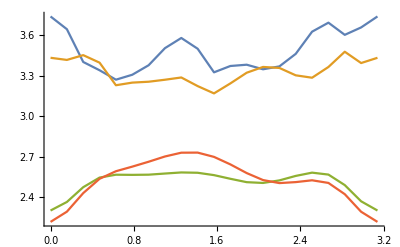

```mathematica
ListLinePlot[{fibo32max,fibo16max,fibo16mean,fibo32mean}]
```

## dt = pi/64

#### data

```mathematica
fibo64={-0.000000000000000000*10^+00,1.944736965868449907*10^+00,3.762244868916226448*10^+00,2.204201990766113006*10^+00,8.238380057061704953*10^-01,1.764473774344278212*10^+00,2.853052865097005952*10^+00,2.940194055518620786*10^+00,1.698618755718522166*10^+00,1.569512586602722859*10^+00,2.383215227402363467*10^+00,3.163693753436537470*10^+00,2.117679555485073362*10^+00,1.578504924631856543*10^+00,2.285008926935086837*10^+00,2.808996410282684320*10^+00,1.988097930656096857*10^+00,1.906636286763105259*10^+00,2.751453117865854114*10^+00,2.212676922196261664*10^+00,2.303213267557048471*10^+00,2.314327849465691589*10^+00,1.877662018991572923*10^+00,2.024190810535107410*10^+00,2.914863017139817103*10^+00,2.683523260698761792*10^+00,1.489385200369585993*10^+00,1.856437112906506037*10^+00,2.468566366799775924*10^+00,2.331319052988716667*10^+00,2.091989716547247635*10^+00,2.039530068655048822*10^+00,1.879038790235332490*10^+00,1.525941339451892587*10^+00,2.094674274466354014*10^+00,3.016904437336188405*10^+00,2.205887764447929555*10^+00,1.425771288791239266*10^+00,2.247060994404286305*10^+00,2.934473591034851836*10^+00,2.199625854458575169*10^+00,9.966365132528416382*10^-01,2.034908938334662132*10^+00,3.405236042007710573*10^+00,2.255638246701402672*10^+00,7.304213394951991623*10^-01,1.782802517305737577*10^+00,3.117290296087064316*10^+00,2.473363989205366487*10^+00,1.101845982741443741*10^+00,1.952884916763095502*10^+00,3.420263404492911441*10^+00,2.375414074078828097*10^+00,1.071338291074148241*10^+00,1.278685243016595807*10^+00,2.598278347337351413*10^+00,2.583595491869899341*10^+00,1.766696952801067422*10^+00,1.560931501889288864*10^+00,2.204440188272594359*10^+00,2.040945066322078283*10^+00,2.488115016551533998*10^+00,2.274005334645773146*10^+00,2.088967530080339863*10^+00,2.132074978263839959*10^+00,2.430100093929640437*10^+00,2.031521662861574207*10^+00,2.285055423886096282*10^+00,2.915110196844806989*10^+00,1.928803858996506859*10^+00,1.769463160821099112*10^+00,2.564270179013143469*10^+00,2.238174042827759891*10^+00,1.436788428351921665*10^+00,2.230203593089660874*10^+00,3.113874105606190490*10^+00,2.238825619674369438*10^+00,1.499060526800917392*10^+00,2.160349693834197282*10^+00,2.878684385533868628*10^+00,2.190122931484554947*10^+00,2.041321014228678621*10^+00,1.666268714746657054*10^+00,2.027062427815007783*10^+00,2.962150608991552136*10^+00,2.244261335042760042*10^+00,1.021724946594679828*10^+00,1.994490827246700793*10^+00,3.494231379269618465*10^+00,2.428800546646537217*10^+00,1.136762509176882707*10^+00,2.001421988099970850*10^+00,3.047874128936384874*10^+00,2.164227658804814602*10^+00,1.630552826295224467*10^+00,1.661345870755239984*10^+00,2.164482308224024543*10^+00,2.998489647333433261*10^+00,2.019420258382909061*10^+00,1.117727828018136194*10^+00,2.313478121832160284*10^+00,3.502691140522427027*10^+00,2.281985007121683395*10^+00,1.026290368573359979*10^+00,2.158219204651071976*10^+00,2.969875027643508858*10^+00,1.942242430937272779*10^+00,1.453297803167302282*10^+00,2.123400229957163710*10^+00,2.293813876142356101*10^+00,2.556864274232120593*10^+00,2.104251483037834713*10^+00,1.864138238725313812*10^+00,2.580114280362806767*10^+00,2.961839825244633406*10^+00,2.397842386704224005*10^+00,1.886776234978320144*10^+00,2.349067356142234608*10^+00,2.302458961880314625*10^+00,1.576582556552857950*10^+00,1.755962821264589246*10^+00,2.604076359736124058*10^+00,2.199934160422800655*10^+00,9.561775992746944786*10^-01,1.880498999776464064*10^+00,3.416063521275070958*10^+00,2.307623892362909324*10^+00,1.009815187826487159*10^+00,2.154286469686547800*10^+00,3.413934746935235243*10^+00,2.359129862697298297*10^+00,1.274790841516206807*10^+00,1.959104786872524206*10^+00,3.132736532328429746*10^+00,2.220926668311661079*10^+00,1.524024426289138034*10^+00,1.672826088966680835*10^+00,2.667486275160654507*10^+00,2.842617310125592933*10^+00,1.872608057770041912*10^+00,1.764246541973058857*10^+00,2.994435850586836256*10^+00,2.616498688452680188*10^+00,1.542252575096301204*10^+00,1.434664580166795655*10^+00,2.268230036664891092*10^+00,2.127130988281602519*10^+00,2.120413348523273900*10^+00,2.065354868990854520*10^+00,2.098491107997247695*10^+00,2.354736270046518420*10^+00,2.804316478786892386*10^+00,2.294177524222603459*10^+00,1.726928823265124091*10^+00,2.407446384552966112*10^+00,2.753415527261593887*10^+00,2.109566346392740321*10^+00,1.846094675820797892*10^+00,2.453514542196549186*10^+00,2.081085800908372807*10^+00,2.070438063512707760*10^+00,2.514619995488364346*10^+00,2.630331725214433369*10^+00,2.395018085119114737*10^+00,2.265094841747216314*10^+00,2.412865516266037513*10^+00,2.195689568662893443*10^+00,2.193565291725408262*10^+00,1.668656712130718089*10^+00,1.599647822027373767*10^+00,2.006045170684837231*10^+00,2.665679030852614595*10^+00,1.432303963714639972*10^+00,1.253106275768440581*10^+00,2.604159014698412378*10^+00,3.047960731211222463*10^+00,1.857054072325887262*10^+00,1.463861258900517992*10^+00,2.720643449294108063*10^+00,3.090153057260813352*10^+00,1.877766656182136007*10^+00,1.171329639553799096*10^+00,2.325640036434565072*10^+00,2.605280011314119459*10^+00,2.292445480855901607*10^+00,1.403632929924446548*10^+00,2.100748995111398010*10^+00,2.753215889997943311*10^+00,2.600495840204267939*10^+00,1.666849612367276023*10^+00,2.129443525106375912*10^+00,2.675607223282653102*10^+00,2.225121400462175991*10^+00,1.611195098983985607*10^+00,1.899818291385117153*10^+00,2.173141715107094640*10^+00,1.646246251866976706*10^+00,2.098439774440743477*10^+00,2.475429306952149577*10^+00,1.933807545735411582*10^+00,2.722912528242654327*10^-14,1.944075957452446879*10^+00,3.760578595068302388*10^+00,2.398141530353142592*10^+00,1.114346608157920970*10^+00,1.996723361609282765*10^+00,2.985080221950267010*10^+00,2.922587054293577236*10^+00,1.718059104369620727*10^+00,1.656216633137068905*10^+00,2.429134712902785598*10^+00,3.192648064769707528*10^+00,2.298527875991871916*10^+00,1.783478984009917223*10^+00,2.405419258602326860*10^+00,2.793471581960512928*10^+00,2.010070031280169367*10^+00,1.960531832681610354*10^+00,2.735669234085963630*10^+00,2.266382596815703643*10^+00,2.401639276213244134*10^+00,2.393305250346533519*10^+00,2.017673140543180477*10^+00,2.160317104212662098*10^+00,2.918715094464911175*10^+00,2.670430297004855014*10^+00,1.556552713942541466*10^+00,1.940949680644057818*10^+00,2.572739266339204356*10^+00,2.390136424284245109*10^+00,2.101086144470830419*10^+00,2.046461999519018526*10^+00,1.943889519762843188*10^+00,1.628422448106229492*10^+00,2.132456233115491706*10^+00,3.023906012046210012*10^+00,2.386219353539071442*10^+00,1.633364827757872950*10^+00,2.314506531162712211*10^+00,2.867125532883886052*10^+00,2.304753013239631443*10^+00,1.288775941684642046*10^+00,2.155665114558245943*10^+00,3.417108096415792939*10^+00,2.371953198097975335*10^+00,9.701344462740282282*10^-01,1.911516919315357832*10^+00,3.178669163518852425*10^+00,2.636272519039436268*10^+00,1.396066157752892334*10^+00,2.127920570242459952*10^+00,3.416872011622444028*10^+00,2.381281903022642421*10^+00,1.165392285187677901*10^+00,1.374362958674655744*10^+00,2.578675343365823824*10^+00,2.602864925757951031*10^+00,1.891176857585644244*10^+00,1.765875233860827453*10^+00,2.316803170846715609*10^+00,2.127136084881068534*10^+00,2.497790753933734731*10^+00,2.220195526436672395*10^+00,2.123444858712161043*10^+00,2.191137065672900341*10^+00,2.534100347407430398*10^+00,2.255052985327512971*10^+00,2.522664329317342080*10^+00,3.008734077181388411*10^+00,2.061061776292965941*10^+00,1.838950079902447854*10^+00,2.610360045154627606*10^+00,2.372934616318731482*10^+00,1.661059459549288686*10^+00,2.424372112576851368*10^+00,3.087462269657768044*10^+00,2.270270895424002955*10^+00,1.675677240278916180*10^+00,2.220750383116281590*10^+00,2.817629028651234435*10^+00,2.257395526798455787*10^+00,2.228162976060032552*10^+00,1.866758120905096741*10^+00,2.130672608724511363*10^+00,2.952014254082222955*10^+00,2.369742921172200756*10^+00,1.228358193238528351*10^+00,2.036536965785066045*10^+00,3.375291573027863201*10^+00,2.510006001383560115*10^+00,1.354333417715905874*10^+00,2.155545486611806005*10^+00,3.039126146280840324*10^+00,2.271224202537365677*10^+00,1.793578788081088726*10^+00,1.726382315030914993*10^+00,2.187740425485858342*10^+00,3.001224949723364066*10^+00,2.217067476608411525*10^+00,1.377668488699924643*10^+00,2.445343475765524133*10^+00,3.467449914473087258*10^+00,2.333204698395394683*10^+00,1.150377700888089993*10^+00,2.173161771148857113*10^+00,2.940493578214320003*10^+00,2.020640535143541250*10^+00,1.607364149551658183*10^+00,2.194050592245553766*10^+00,2.414844194368393815*10^+00,2.656588532839169403*10^+00,2.186115093663109299*10^+00,2.023864816586431026*10^+00,2.662585494911398953*10^+00,3.013331436883300629*10^+00,2.423553264924305228*10^+00,1.927720804533203935*10^+00,2.446157821963421686*10^+00,2.438308444179889456*10^+00,1.766576408681275190*10^+00,1.926060681473049208*10^+00,2.769737355820721447*10^+00,2.396982370165724685*10^+00,1.217393605217591768*10^+00,2.055036779295722482*10^+00,3.405033306904002188*10^+00,2.450251091453876651*10^+00,1.305010272056922993*10^+00,2.316674792986262776*10^+00,3.367581325577736706*10^+00,2.544986425092029325*10^+00,1.552103635021396144*10^+00,2.093418692345922594*10^+00,3.119184958005741137*10^+00,2.336150957867292988*10^+00,1.746805000290883703*10^+00,1.890186257979035611*10^+00,2.795966319337776618*10^+00,2.894531814162879080*10^+00,2.034596134311030813*10^+00,1.862203386965299856*10^+00,2.943607097575447362*10^+00,2.623502159933847722*10^+00,1.696833332186507670*10^+00,1.662550638600194475*10^+00,2.407626328113963599*10^+00,2.332702237173757354*10^+00,2.262466330849541407*10^+00,2.149360709988897167*10^+00,2.104607918205551265*10^+00,2.380266140315487000*10^+00,2.825622805189123454*10^+00,2.358702256315868606*10^+00,1.888628116092786691*10^+00,2.556614931674062063*10^+00,2.895396777713756364*10^+00,2.220381647242825718*10^+00,1.961061057984087030*10^+00,2.574005751418419585*10^+00,2.272216750496297344*10^+00,2.220193729232885715*10^+00,2.549003559118097950*10^+00,2.669738725867531137*10^+00,2.500344404297004886*10^+00,2.382248236195814606*10^+00,2.402193729127753752*10^+00,2.204909028396180304*10^+00,2.254181654967764903*10^+00,1.805344271541725831*10^+00,1.628548099662147308*10^+00,1.985032510064365319*10^+00,2.636964916952997395*10^+00,1.585376388975132667*10^+00,1.395013548882844123*10^+00,2.672225930492285517*10^+00,3.096859420745384561*10^+00,2.052519077056965902*10^+00,1.618878233069293016*10^+00,2.697319541334628479*10^+00,3.029143021176887274*10^+00,1.995798431321421207*10^+00,1.346411326803894859*10^+00,2.422087381780240189*10^+00,2.666123829460386396*10^+00,2.373004475121525569*10^+00,1.618546688181176307*10^+00,2.251651079808143940*10^+00,2.895010882104943395*10^+00,2.678998748151085074*10^+00,1.818255938672894256*10^+00,2.180220997871444855*10^+00,2.697718752474965953*10^+00,2.312941192993606343*10^+00,1.788267358904811255*10^+00,2.035765051832272299*10^+00,2.211465112211040029*10^+00,1.776444685109349830*10^+00,2.243755682137988927*10^+00,2.523240078712739365*10^+00,2.081004259361654896*10^+00,-9.610279511444755881*10^-16,1.942157932817172972*10^+00,3.755844165009176283*10^+00,2.703713608808736790*10^+00,1.569988093556567765*10^+00,2.396505287242256976*10^+00,3.183339044317819777*10^+00,2.863066269979464007*10^+00,1.764944158269833974*10^+00,1.883518236677919955*10^+00,2.587182567700804903*10^+00,3.184997115250450594*10^+00,2.546231968484219177*10^+00,2.157737612337044641*10^+00,2.597225781218995166*10^+00,2.746108834266606458*10^+00,2.073341847040211405*10^+00,2.074552875466371127*10^+00,2.693341633157688708*10^+00,2.338869676327585356*10^+00,2.566896212300182611*10^+00,2.547796962804276255*10^+00,2.216806787277578739*10^+00,2.405193967935326693*10^+00,2.922503881622265709*10^+00,2.687510095231786522*10^+00,1.762653309722939099*10^+00,2.134118348524851605*10^+00,2.789198632699521507*10^+00,2.480178731306418527*10^+00,2.091208399975870158*10^+00,2.095139794694516056*10^+00,2.115538638305871633*10^+00,1.882142591940402010*10^+00,2.216492317671069134*10^+00,3.003810907105978867*10^+00,2.740608388867912026*10^+00,2.033066681359019690*10^+00,2.321883519213475022*10^+00,2.692141472778291078*10^+00,2.517281289127574873*10^+00,1.833095759824677096*10^+00,2.377452574837823018*10^+00,3.359471302560075312*10^+00,2.587840624587547822*10^+00,1.436065665607429542*10^+00,2.109266038977787971*10^+00,3.216094137120355079*10^+00,2.895387061748947222*10^+00,1.920286844681273086*10^+00,2.473882892839847969*10^+00,3.383948375061402558*10^+00,2.380577060765400876*10^+00,1.383725907450003012*10^+00,1.558790336073785587*10^+00,2.542705219041948794*10^+00,2.618656777627486498*10^+00,2.166232120269355743*10^+00,2.188478657859621368*10^+00,2.521786844070227129*10^+00,2.239233145395486346*10^+00,2.525746211253447004*10^+00,2.129460198824519424*10^+00,2.203078929473297531*10^+00,2.292483554254228562*10^+00,2.728537301913072532*10^+00,2.644634200439240246*10^+00,2.837520529344472742*10^+00,3.115611413663022855*10^+00,2.299643991305503565*10^+00,1.965703072252293460*10^+00,2.661987113098077895*10^+00,2.596643488024231505*10^+00,2.079978908000922999*10^+00,2.751073899241261778*10^+00,2.998307102559770509*10^+00,2.320573125526279590*10^+00,2.041632140131365958*10^+00,2.348785796680068039*10^+00,2.648787016894215363*10^+00,2.359743654390263679*10^+00,2.564909603841714070*10^+00,2.291101314376023268*10^+00,2.287553926482309485*10^+00,2.886672889758933991*10^+00,2.623598382386698180*10^+00,1.710239891288433789*10^+00,2.136722559365880514*10^+00,3.082434042591918555*10^+00,2.608601361459649048*10^+00,1.801010405783618484*10^+00,2.435531587628384731*10^+00,2.982657027427640717*10^+00,2.451986247364077443*10^+00,2.146399244975067955*10^+00,1.905901483806290653*10^+00,2.241013932495449446*10^+00,2.957431564761747733*10^+00,2.515677581558619202*10^+00,1.834419422439502956*10^+00,2.639634061271365795*10^+00,3.389561287935635825*10^+00,2.472210675384557632*10^+00,1.501358931860454105*10^+00,2.231498823861303826*10^+00,2.844462201944497615*10^+00,2.165037751603160920*10^+00,1.899199630319769572*10^+00,2.336763659077905064*10^+00,2.656644255020850665*10^+00,2.829500908878261889*10^+00,2.352033863310898365*10^+00,2.287772289649972368*10^+00,2.809402262614797419*10^+00,3.081870283823895385*10^+00,2.479557673666221262*10^+00,2.021199897947438817*10^+00,2.653219253031016134*10^+00,2.685615392648299071*10^+00,2.081081632599270925*10^+00,2.171446415993275814*10^+00,2.979170360227877179*10^+00,2.690282525957356619*10^+00,1.675625199079442851*10^+00,2.338257443208956232*10^+00,3.348802477732427896*10^+00,2.722769669870281461*10^+00,1.866046575995458756*10^+00,2.606837060171141474*10^+00,3.281559215975854649*10^+00,2.846511425643400539*10^+00,2.014556463868816039*10^+00,2.310818228752195669*10^+00,3.059966388790553715*10^+00,2.589474759734586407*10^+00,2.177439467963713682*10^+00,2.201692322418005610*10^+00,2.959912954133072649*10^+00,2.948003597393813902*10^+00,2.305422186489344050*10^+00,2.026331094497534568*10^+00,2.837648670130282991*10^+00,2.630125705822720761*10^+00,1.992818622294602937*10^+00,2.103635966935509582*10^+00,2.664078558234507899*10^+00,2.610453731363967300*10^+00,2.451294407150470978*10^+00,2.265235020912117037*10^+00,2.124667409908661764*10^+00,2.439221592313002063*10^+00,2.870905554309756802*10^+00,2.478997242164846071*10^+00,2.153197816903957840*10^+00,2.740266486333085449*10^+00,3.067116109728258433*10^+00,2.383533401465965706*10^+00,2.115722316226233080*10^+00,2.757547373986127148*10^+00,2.641608598859980894*10^+00,2.498359623116930273*10^+00,2.577133358732096369*10^+00,2.681334975402277720*10^+00,2.691183827730152966*10^+00,2.587307403452939969*10^+00,2.389339251029233502*10^+00,2.207655826744173488*10^+00,2.446214893178445315*10^+00,2.051381951418381533*10^+00,1.666804687087771075*10^+00,1.925894798147552267*10^+00,2.572946454264276372*10^+00,1.891514185988949492*10^+00,1.703904006433555995*10^+00,2.746292836289718764*10^+00,3.166265724525440639*10^+00,2.406189974284477895*10^+00,1.959458187063690238*10^+00,2.611762332786319529*10^+00,2.893712900615801331*10^+00,2.253093667370455577*10^+00,1.744907003650451482*10^+00,2.576145146038180123*10^+00,2.738435223449008582*10^+00,2.514344804938121847*10^+00,1.974679743122548681*10^+00,2.440886725903439469*10^+00,3.050179794192344307*10^+00,2.828797180087100127*10^+00,2.124037384215272439*10^+00,2.321045821810779231*10^+00,2.699356161515967578*10^+00,2.454033412672800729*10^+00,2.157140297411464847*10^+00,2.279026310360105612*10^+00,2.288398489632888833*10^+00,2.022360734228010770*10^+00,2.536862924886424953*10^+00,2.661882753954281089*10^+00,2.304052269652396401*10^+00,9.610279511444749964*10^-16,1.939171418525549306*10^+00,3.748758557037221273*10^+00,2.870377128908926601*10^+00,1.992383862843533748*10^+00,2.802380196782992883*10^+00,3.247396127469528437*10^+00,2.669292881663290373*10^+00,1.813352811775537310*10^+00,2.134648047584988273*10^+00,2.712653789216014744*10^+00,3.081959738684139083*10^+00,2.736035223812743222*10^+00,2.503366862113786784*10^+00,2.662306397446396744*10^+00,2.666865149621915343*10^+00,2.172898263636875882*10^+00,2.218210127554194777*10^+00,2.587734867466708444*10^+00,2.369413401272120190*10^+00,2.658719529199968790*10^+00,2.667228450638705617*10^+00,2.297663838240775469*10^+00,2.543357006115471108*10^+00,2.899916277927910180*10^+00,2.682979948780995549*10^+00,1.959198340740489153*10^+00,2.331501624512401616*10^+00,2.962510363782422385*10^+00,2.545470308535126680*10^+00,2.016407124008777529*10^+00,2.160992565672084087*10^+00,2.317683944895413628*10^+00,2.128462342553443243*10^+00,2.265100096360002091*10^+00,2.944183287383374648*10^+00,3.013030800309783430*10^+00,2.332384002020880587*10^+00,2.227243345327365454*10^+00,2.486448634110840050*10^+00,2.703155380856751222*10^+00,2.315658137336863209*10^+00,2.537345937879550206*10^+00,3.170669283890782175*10^+00,2.742462554867028501*10^+00,1.864505754038817686*10^+00,2.238072323548670362*10^+00,3.101501688899801934*10^+00,3.054450650064080452*10^+00,2.407280562086242970*10^+00,2.813951555232831581*10^+00,3.289425779848586195*10^+00,2.331961128510560144*10^+00,1.630016960159906825*10^+00,1.808835798049383436*10^+00,2.504560006925417248*10^+00,2.613069442418825883*10^+00,2.398498360820207065*10^+00,2.636746384926921039*10^+00,2.681309626910048038*10^+00,2.275576069735983697*10^+00,2.506025680225905106*10^+00,2.166976986581393927*10^+00,2.252254797543440379*10^+00,2.358126586783699352*10^+00,2.864855205710645336*10^+00,2.958664592142025818*10^+00,3.012633121464928898*10^+00,3.066130373059073655*10^+00,2.500574158744659936*10^+00,2.187739089393726744*10^+00,2.684570260616263582*10^+00,2.694410045950603738*10^+00,2.439221276135293603*10^+00,2.978752755787343887*10^+00,2.821982328605453283*10^+00,2.305081443810326647*10^+00,2.364327289314765324*10^+00,2.466693761348499159*10^+00,2.439508456277137416*10^+00,2.386087355652851905*10^+00,2.842031080588523828*10^+00,2.663993710946374271*10^+00,2.357625927760323759*10^+00,2.763576502346798414*10^+00,2.879431587853502617*10^+00,2.181162124573451599*10^+00,2.158719114762029267*10^+00,2.760464587332764896*10^+00,2.599651976675714238*10^+00,2.176675137978665298*10^+00,2.645421393174402613*10^+00,2.882266745695353904*10^+00,2.615541962170536028*10^+00,2.568787924415567581*10^+00,2.144226543609767166*10^+00,2.242086629144661725*10^+00,2.788960226824203303*10^+00,2.660225505615128938*10^+00,2.285501943031019945*10^+00,2.740708993153925466*10^+00,3.273886797347347777*10^+00,2.614716272308845291*10^+00,1.942488009407464800*10^+00,2.350553229304017666*10^+00,2.664666545345404813*10^+00,2.151865247993113073*10^+00,2.159911619498069868*10^+00,2.497188906877468195*10^+00,2.786424667337188854*10^+00,2.932122584026811030*10^+00,2.551304437460331087*10^+00,2.523032142402978018*10^+00,2.842144290178437949*10^+00,3.028734442267140281*10^+00,2.515832130281191681*10^+00,2.183284127474586001*10^+00,2.834221096052509381*10^+00,2.886307701634709844*10^+00,2.358689307670394530*10^+00,2.364831219220008940*10^+00,3.060031547273608155*10^+00,2.814967110915815862*10^+00,1.983031650403759505*10^+00,2.463033039660216694*10^+00,3.223282102129984228*10^+00,2.945086345301237696*10^+00,2.387065737212360261*10^+00,2.844861383033922220*10^+00,3.165273813051241891*10^+00,2.959548519504742181*10^+00,2.335031005760818346*10^+00,2.379430845134201000*10^+00,2.932442749695975071*10^+00,2.793558380819368914*10^+00,2.558259738475112677*10^+00,2.443454389131557214*10^+00,3.040390232281005911*10^+00,2.902838572876204282*10^+00,2.464848924795299823*10^+00,2.147376556171526563*10^+00,2.768395662376740063*10^+00,2.683111538997462020*10^+00,2.239194164782491114*10^+00,2.480963029922124807*10^+00,2.859443404084237361*10^+00,2.738718391016022657*10^+00,2.502422494038095913*10^+00,2.356925582289739474*10^+00,2.174735766120840186*10^+00,2.474182738878332621*10^+00,2.899365407559669983*10^+00,2.622981407099208795*10^+00,2.347576441969333239*10^+00,2.806533810414631791*10^+00,3.049654728757284605*10^+00,2.455566144122665051*10^+00,2.245217340912448289*10^+00,2.869475762544960951*10^+00,2.917406896835847974*10^+00,2.703765504705138323*10^+00,2.554067506442013524*10^+00,2.621252150104331324*10^+00,2.752787372780148623*10^+00,2.727124250585366561*10^+00,2.377568794913419659*10^+00,2.244485849042602954*10^+00,2.631417230191598122*10^+00,2.300656404218754059*10^+00,1.700212165667049691*10^+00,1.865190496344926174*10^+00,2.485875019825549259*10^+00,2.202063069206043000*10^+00,2.006935149097880622*10^+00,2.750149199827583324*10^+00,3.162689789076952529*10^+00,2.672698728477270080*10^+00,2.217219145648243739*10^+00,2.487207086346919116*10^+00,2.774291545993435193*10^+00,2.533645819440829783*10^+00,2.160166622969292849*10^+00,2.665580290644205874*10^+00,2.747033904183008524*10^+00,2.568227799829650770*10^+00,2.282504261794960243*10^+00,2.535915102896619366*10^+00,3.044606746001004893*10^+00,2.933723635766819715*10^+00,2.421566886381353534*10^+00,2.472741404544485100*10^+00,2.678450785410335655*10^+00,2.587422274881867601*10^+00,2.493784435944227162*10^+00,2.444164740441185035*10^+00,2.303838341517856936*10^+00,2.214024754720777199*10^+00,2.794853592637085438*10^+00,2.809016224707784559*10^+00,2.438023198918622292*10^+00,4.805139755722374982*10^-16,1.935409717537414975*10^+00,3.740302007903821835*10^+00,2.890702644856077086*10^+00,2.277800445078900005*10^+00,3.147197909132719573*10^+00,3.147045524235202230*10^+00,2.409448792848273513*10^+00,1.839000021468696344*10^+00,2.355895534923374335*10^+00,2.760193912604404609*10^+00,2.877393638528134012*10^+00,2.850117503655588802*10^+00,2.800741776766397795*10^+00,2.632088129052365666*10^+00,2.532471525013237468*10^+00,2.295997972411450760*10^+00,2.318310790845909519*10^+00,2.431017935100523442*10^+00,2.347921431341673859*10^+00,2.699170758481466148*10^+00,2.769289979358220410*10^+00,2.298823103315573047*10^+00,2.555987106457605407*10^+00,2.805126196868953592*10^+00,2.523688993704071848*10^+00,1.990548461948059789*10^+00,2.444593267942108294*10^+00,3.030920323309841180*10^+00,2.549117295201329458*10^+00,1.994436183785148753*10^+00,2.285472273465614546*10^+00,2.525319335702196799*10^+00,2.233430463931310062*10^+00,2.256629553885705519*10^+00,2.871731417101987649*10^+00,3.132852562379886852*10^+00,2.486969475674617236*10^+00,2.114666334219548194*10^+00,2.425951040289156424*10^+00,2.824947170015894571*10^+00,2.536037019300160011*10^+00,2.570777171879778056*10^+00,2.995432439459911667*10^+00,2.767398655321027245*10^+00,2.123749139474689684*10^+00,2.342703746610612647*10^+00,2.910524501281721577*10^+00,3.081150971053309373*10^+00,2.716588814920739559*10^+00,3.034754764287902695*10^+00,3.141786384172196467*10^+00,2.207467411970733373*10^+00,1.826805166272974290*10^+00,2.105573520621946582*10^+00,2.511807270601706499*10^+00,2.608780977902318110*10^+00,2.566937149642285476*10^+00,2.951486794841810646*10^+00,2.730216289337347835*10^+00,2.163177459794681123*10^+00,2.445726018950382219*10^+00,2.355575358823269738*10^+00,2.352661137749342046*10^+00,2.357715065391301046*10^+00,2.911068423785460269*10^+00,3.147520959182328326*10^+00,3.033641476645767998*10^+00,2.856407915346488302*10^+00,2.639753463905487152*10^+00,2.458724595595207507*10^+00,2.705946584716392600*10^+00,2.632688906032671916*10^+00,2.660127599152940281*10^+00,3.029079422002385780*10^+00,2.657786902376703342*10^+00,2.259644397792293091*10^+00,2.565441217400618257*10^+00,2.567337323435600283*10^+00,2.284828565604005046*10^+00,2.327683247144153089*10^+00,2.984442461520917966*10^+00,2.887610447599205710*10^+00,2.338865924984636635*10^+00,2.663293977573013116*10^+00,3.066193722202310568*10^+00,2.512578085902918978*10^+00,2.168850534419753728*10^+00,2.413102741863800915*10^+00,2.500014853914097390*10^+00,2.406958377178101127*10^+00,2.774551665694238611*10^+00,2.872403406604183029*10^+00,2.713856294216319576*10^+00,2.891506669562605936*10^+00,2.405603843727797120*10^+00,2.190951931226398308*10^+00,2.536055065154757315*10^+00,2.611448303018732986*10^+00,2.636134066222091565*10^+00,2.812397887123543327*10^+00,3.082168341853301907*10^+00,2.723901218330460505*10^+00,2.373878837948893317*10^+00,2.457872070297262290*10^+00,2.389341284302953561*10^+00,1.987756122645512935*10^+00,2.371471484872390789*10^+00,2.741017957164988417*10^+00,2.803409927506471000*10^+00,2.914891418535503487*10^+00,2.792648384716548193*10^+00,2.752331125632831998*10^+00,2.721061879703139397*10^+00,2.817288344625861640*10^+00,2.517406533683393732*10^+00,2.404739298987148111*10^+00,2.933760290269893378*10^+00,2.977310981270829604*10^+00,2.538480030969838985*10^+00,2.579150566012796020*10^+00,3.008151958277681892*10^+00,2.702902066083387567*10^+00,2.045229777594918197*10^+00,2.398822271124851024*10^+00,3.056533986782655088*10^+00,3.109023305952570482*10^+00,2.729992994398460660*10^+00,2.965728997592952609*10^+00,3.024983655650623326*10^+00,2.861528010736512417*10^+00,2.381772288418501304*10^+00,2.305869961505040422*10^+00,2.782740816251784377*10^+00,2.919614674071151939*10^+00,2.776490126054147911*10^+00,2.576401296639252436*10^+00,3.048462794505184981*10^+00,2.777321052211053409*10^+00,2.482905099053893672*10^+00,2.207254609189569727*10^+00,2.785054446664004590*10^+00,2.806152434301190990*10^+00,2.389512571070229185*10^+00,2.726779939781518003*10^+00,2.954823716226016472*10^+00,2.713985805160052944*10^+00,2.434382522957832862*10^+00,2.398356813829516820*10^+00,2.220380691589799671*10^+00,2.497936181327633953*10^+00,2.877126503554573667*10^+00,2.749756764911729601*10^+00,2.570580492885984558*10^+00,2.752355094087261200*10^+00,2.843641827423680546*10^+00,2.414266590492696096*10^+00,2.366704806817558460*10^+00,2.914306603261127115*10^+00,3.025079137904085780*10^+00,2.781391174177376691*10^+00,2.573348556740788773*10^+00,2.563641538035403400*10^+00,2.688897633733226211*10^+00,2.723967168851398668*10^+00,2.378180489309272616*10^+00,2.346358087735380682*10^+00,2.806708052546676768*10^+00,2.477144842482005949*10^+00,1.818087594781575111*10^+00,1.932536830855167587*10^+00,2.479731771267670304*10^+00,2.459371966061586701*10^+00,2.200802858312881582*10^+00,2.690417695242150575*10^+00,3.096639214189861544*10^+00,2.791217204884934411*10^+00,2.352284754740623818*10^+00,2.396223225730417461*10^+00,2.723603190739796176*10^+00,2.778648502770836526*10^+00,2.448008509510089858*10^+00,2.676709105865282101*10^+00,2.734114705620999342*10^+00,2.555337227468739592*10^+00,2.435621260039663838*10^+00,2.613310711792128593*10^+00,2.928638719912558308*10^+00,2.932939210327486723*10^+00,2.598956617926225121*10^+00,2.555231271253703529*10^+00,2.617638902316254956*10^+00,2.636965727315150332*10^+00,2.714558473063965138*10^+00,2.549509240002399757*10^+00,2.296713945749825569*10^+00,2.304177207416147066*10^+00,2.893061544689832232*10^+00,2.861526004570791759*10^+00,2.492779227438344680*10^+00,3.203426503814917641*10^-16,1.931241832255828683*10^+00,3.731505757544155255*10^+00,2.771302440985453863*10^+00,2.431838206617038534*10^+00,3.415024801281139055*10^+00,3.012769472694899253*10^+00,2.138637591832098117*10^+00,1.848980611451437106*10^+00,2.472026574372277352*10^+00,2.708325592264103854*10^+00,2.611554868062956114*10^+00,2.912379972830964725*10^+00,3.047051068225276715*10^+00,2.589822429540424409*10^+00,2.412793411604425842*10^+00,2.415848098326301763*10^+00,2.354639983233557388*10^+00,2.276151747371962131*10^+00,2.355972394873259823*10^+00,2.755956808424325111*10^+00,2.880924352473003047*10^+00,2.373664917759899851*10^+00,2.523661951682010240*10^+00,2.594520679413959474*10^+00,2.164586093125408617*10^+00,1.788629400702462124*10^+00,2.438603109116226797*10^+00,3.032026964695632376*10^+00,2.582078652939463037*10^+00,2.172166491310023595*10^+00,2.480250510620502169*10^+00,2.648639646221801147*10^+00,2.151726192093733836*10^+00,2.133316928111797850*10^+00,2.806449669987334694*10^+00,3.108110574026583084*10^+00,2.517486796675066696*10^+00,2.139625786272264740*10^+00,2.586326180874720215*10^+00,2.891397522503007522*10^+00,2.462566777953658637*10^+00,2.478656863141721622*10^+00,2.852039466970789583*10^+00,2.700529910310960791*10^+00,2.224721364895535736*10^+00,2.446849828682302164*10^+00,2.859161527951098236*10^+00,3.015574750902717316*10^+00,2.814745943058604816*10^+00,3.107382104334419193*10^+00,2.974436646607500734*10^+00,2.013086061374288249*10^+00,1.941504919900810755*10^+00,2.397015004843829900*10^+00,2.628801466429942835*10^+00,2.570804112661193574*10^+00,2.650868689830866209*10^+00,3.083260201280884516*10^+00,2.668325246971208209*10^+00,1.973713947746202679*10^+00,2.356942294323732590*10^+00,2.619794035402603249*10^+00,2.515447754670379066*10^+00,2.326556161993814875*10^+00,2.899119607347123928*10^+00,3.200652731096686132*10^+00,2.942998130691856673*10^+00,2.597872957310884079*10^+00,2.717871867705198063*10^+00,2.745636622758631518*10^+00,2.768552795191770333*10^+00,2.514290967079739314*10^+00,2.779026121846470687*10^+00,2.998008660952113047*10^+00,2.537673980057479017*10^+00,2.233220913796433393*10^+00,2.663471218786008343*10^+00,2.629488554803357747*10^+00,2.225824637094878433*10^+00,2.285766823295727779*10^+00,2.999783828187635670*10^+00,2.974519032646377958*10^+00,2.298630883662675206*10^+00,2.681760107937028792*10^+00,3.196193697973223280*10^+00,2.622689014131622365*10^+00,2.106874411648737233*10^+00,2.191633538700006323*10^+00,2.393265534448956622*10^+00,2.543351946507725447*10^+00,2.866912879149148718*10^+00,2.936702952737836547*10^+00,2.788090427081162392*10^+00,3.065992926088262571*10^+00,2.616125059969538924*10^+00,2.154321250795612652*10^+00,2.271094405540183381*10^+00,2.472104709625623897*10^+00,2.813615225212880766*10^+00,2.910500002517159679*10^+00,2.880196106447580728*10^+00,2.729423102001493184*10^+00,2.689670421283862911*10^+00,2.540816855857833900*10^+00,2.120562701498299063*10^+00,1.802725323025352822*10^+00,2.546211273019537202*10^+00,3.079241932163355067*10^+00,2.702572169286358683*10^+00,2.787416195763750437*10^+00,2.994291832770944239*10^+00,2.923549270080033846*10^+00,2.522363174218830384*10^+00,2.522718920906295459*10^+00,2.568327818099591653*10^+00,2.698036497315018156*10^+00,2.963719658561747572*10^+00,2.961627243163068357*10^+00,2.670678561299381748*10^+00,2.768839002840270513*10^+00,2.977554745120446711*10^+00,2.449142312075212047*10^+00,1.913477819549469716*10^+00,2.252918032956014560*10^+00,2.941463465227541096*10^+00,3.212106146660124839*10^+00,2.873432800812345533*10^+00,2.993845846892673634*10^+00,2.929477829552733059*10^+00,2.626148372965909861*10^+00,2.198295150027472999*10^+00,2.173460083301123724*10^+00,2.720511418834965944*10^+00,3.042823115990763050*10^+00,2.826765223546573225*10^+00,2.620258849324831552*10^+00,3.120139596384878367*10^+00,2.687244957138790191*10^+00,2.419348067711504680*10^+00,2.221980168680669276*10^+00,2.859379889566669775*10^+00,2.927435302126548677*10^+00,2.481201363570766816*10^+00,2.827828640209430588*10^+00,3.009980203678566557*10^+00,2.640042889201918541*10^+00,2.378076988370387834*10^+00,2.429103344155049804*10^+00,2.268318029314075446*10^+00,2.475826212360016765*10^+00,2.796330665370887480*10^+00,2.807308398431882068*10^+00,2.801856028378961305*10^+00,2.698070799786346896*10^+00,2.584521569841454536*10^+00,2.334943655324132283*10^+00,2.472199920048215205*10^+00,2.978132759011162811*10^+00,2.998444259907958820*10^+00,2.782404150207469229*10^+00,2.703282089646396713*10^+00,2.576520998451544919*10^+00,2.570273856372494947*10^+00,2.587188217314914329*10^+00,2.395804430156251108*10^+00,2.528017067466609813*10^+00,2.958082400390976474*10^+00,2.648402789726019613*10^+00,1.990517205205613260*10^+00,2.117956706137074097*10^+00,2.555530023246865845*10^+00,2.600635682640118240*10^+00,2.269717107250227350*10^+00,2.646350326785445350*10^+00,3.048107310279636106*10^+00,2.821451256230615989*10^+00,2.365318443682399518*10^+00,2.365952032012202277*10^+00,2.746046171764222166*10^+00,2.906978421485841402*10^+00,2.591043590753939974*10^+00,2.629205720949814307*10^+00,2.709963908895185014*10^+00,2.545808265068119525*10^+00,2.492920434503089311*10^+00,2.680441059352909328*10^+00,2.846581603986569675*10^+00,2.857246156326147091*10^+00,2.594693388793958722*10^+00,2.507390154119883530*10^+00,2.556514863158600104*10^+00,2.690274072716049680*10^+00,2.818684370832741592*10^+00,2.642844048275948765*10^+00,2.339955740923049365*10^+00,2.374684557186936829*10^+00,2.833076584831998979*10^+00,2.774434611674539308*10^+00,2.536076238748846912*10^+00,-9.610279511444755881*10^-16,1.927076045491425083*10^+00,3.723297770398680928*10^+00,2.618349224790431862*10^+00,2.508799286520545291*10^+00,3.585807925807628305*10^+00,2.908490285134757602*10^+00,1.944793887417166633*10^+00,1.880661870774518629*10^+00,2.518300380814953776*10^+00,2.585616099837134918*10^+00,2.423060639481662726*10^+00,2.962578291405039810*10^+00,3.223500702284509245*10^+00,2.671558166125431288*10^+00,2.403186910876863092*10^+00,2.523659200599303265*10^+00,2.366644373118481859*10^+00,2.211905818006656865*10^+00,2.428778927636521701*10^+00,2.835171633270975544*10^+00,2.989118035111120175*10^+00,2.542414194394983173*10^+00,2.533610049033065081*10^+00,2.337505847192927089*10^+00,1.753530392572850261*10^+00,1.450628910628856572*10^+00,2.348485271413873310*10^+00,3.051928291922187508*10^+00,2.631741206979541836*10^+00,2.419501408789035857*10^+00,2.741769241929709722*10^+00,2.689658120857120416*10^+00,1.964032090593261337*10^+00,1.929489149162255224*10^+00,2.745879428742870942*10^+00,3.089677959346277092*10^+00,2.493715157529816651*10^+00,2.294429772069055851*10^+00,2.922405920055845208*10^+00,2.875227474050946253*10^+00,2.208231355984167088*10^+00,2.249904256445367512*10^+00,2.725348664628036932*10^+00,2.609808043822223311*10^+00,2.263219214551039471*10^+00,2.559014354105730860*10^+00,2.955915288655778017*10^+00,2.910500589685415029*10^+00,2.760197136599297885*10^+00,3.042620238776520658*10^+00,2.833033186968578754*10^+00,1.853888798210359568*10^+00,1.984718256854583585*10^+00,2.638837918070911837*10^+00,2.790565811969549337*10^+00,2.505433912309393385*10^+00,2.675553113394899984*10^+00,3.068168460728960323*10^+00,2.540977288851926641*10^+00,1.800772046241450264*10^+00,2.285968010481837620*10^+00,2.883625240437690529*10^+00,2.715456160502773830*10^+00,2.285108512806815817*10^+00,2.855890545355530108*10^+00,3.188468736009406168*10^+00,2.790011881118841242*10^+00,2.363633585341094800*10^+00,2.786801234557520601*10^+00,2.969930537654062341*10^+00,2.810751311227903670*10^+00,2.434157387065614131*10^+00,2.851737468491812866*10^+00,2.929978600901085528*10^+00,2.469364586062436473*10^+00,2.312244918649550396*10^+00,2.703790441497050168*10^+00,2.632792518586463792*10^+00,2.213524865106859973*10^+00,2.359900843793899305*10^+00,2.967442027201969701*10^+00,3.013714174355323294*10^+00,2.341354051667757119*10^+00,2.855455135890099694*10^+00,3.281766024228084611*10^+00,2.541192675042734717*10^+00,1.960429342110273421*10^+00,2.122087682496645922*10^+00,2.376283315665713047*10^+00,2.640538240988061780*10^+00,2.913840469555557533*10^+00,3.016210543144692835*10^+00,2.908672734887542077*10^+00,3.118302463997066898*10^+00,2.722203641030707555*10^+00,2.213367260564046646*10^+00,2.137967854970128201*10^+00,2.394514899048043155*10^+00,2.830700636617480725*10^+00,2.994826652408717926*10^+00,2.727101960990893303*10^+00,2.670464263564090945*10^+00,2.846986073957432861*10^+00,2.612230133609683591*10^+00,1.904323180507357938*10^+00,1.748316480517064120*10^+00,2.685493537251375962*10^+00,3.310575578914427997*10^+00,2.543275807331651261*10^+00,2.607287424251986785*10^+00,3.147361715530354598*10^+00,2.978275758793097250*10^+00,2.344944645782971460*10^+00,2.280073166883542779*10^+00,2.703856649235330867*10^+00,3.038002582926749628*10^+00,3.002377588577413547*10^+00,2.880111184792967460*10^+00,2.719060542605051367*10^+00,2.910266533307326320*10^+00,3.014048661217107572*10^+00,2.246731295555205676*10^+00,1.744996777525235521*10^+00,2.136499693653556964*10^+00,2.829406421130846283*10^+00,3.275547804483823544*10^+00,2.908361687890099301*10^+00,2.946427152448869435*10^+00,2.885356542454726281*10^+00,2.390179102020451918*10^+00,1.902439436261262440*10^+00,1.990334683515169845*10^+00,2.686225029974329992*10^+00,3.207485728392784452*10^+00,2.773572711014973713*10^+00,2.590610534745750648*10^+00,3.295041205980530297*10^+00,2.755589354074317932*10^+00,2.331704781554907235*10^+00,2.214324665397183090*10^+00,2.952575582034048907*10^+00,3.039295311519547127*10^+00,2.539372422615614688*10^+00,2.837014515743453202*10^+00,3.063303415887296488*10^+00,2.680379147298550091*10^+00,2.428648722264723059*10^+00,2.460565656497865739*10^+00,2.303437969370028870*10^+00,2.406291882100629831*10^+00,2.671065687939973010*10^+00,2.850766352920538260*10^+00,3.014154765314669415*10^+00,2.714278642947826725*10^+00,2.371969941525068126*10^+00,2.246705979112475049*10^+00,2.537637556918143300*10^+00,3.069648167544503536*10^+00,2.919776052512295994*10^+00,2.775211689028219020*10^+00,2.888614044968163874*10^+00,2.608563675146016170*10^+00,2.418275097673729057*10^+00,2.467163572842258290*10^+00,2.430285808721557750*10^+00,2.745599285523733890*10^+00,3.092579389045421845*10^+00,2.799588169466034948*10^+00,2.204434275044008906*10^+00,2.302909985617044075*10^+00,2.631776218727661210*10^+00,2.631470924398382039*10^+00,2.255153354892830642*10^+00,2.660223650792952643*10^+00,3.039175703113850879*10^+00,2.871026018641105182*10^+00,2.348581872054178898*10^+00,2.353653812490815067*10^+00,2.773692479037353831*10^+00,2.896087418000433011*10^+00,2.601429048363879559*10^+00,2.584712957511127396*10^+00,2.753909160229307762*10^+00,2.673104972290972547*10^+00,2.559052208486390256*10^+00,2.732960657599898813*10^+00,2.832450336011611558*10^+00,2.748335443320273797*10^+00,2.424573845617255419*10^+00,2.336946692759954036*10^+00,2.553687763336472294*10^+00,2.768590994646227266*10^+00,2.877405234129577050*10^+00,2.778596224655381253*10^+00,2.489786462392949318*10^+00,2.457160584858489649*10^+00,2.734911274932487757*10^+00,2.631079349713937532*10^+00,2.573740992521375226*10^+00,-3.203426503814917641*10^-16,1.923319838500688661*10^+00,3.716432694514564705*10^+00,2.496405377803252001*10^+00,2.524328558909481046*10^+00,3.658409660702892197*10^+00,2.969459866229373635*10^+00,1.924304364870702999*10^+00,1.936216054855632862*10^+00,2.547623767642853920*10^+00,2.486298076059807904*10^+00,2.330418153122950642*10^+00,3.000817654638973320*10^+00,3.294693407341122260*10^+00,2.848501842090426450*10^+00,2.581487306420546357*10^+00,2.593210953217010672*10^+00,2.374482287611613174*10^+00,2.287473510415037659*10^+00,2.545046940644568156*10^+00,2.944734001570622262*10^+00,3.067537269042525327*10^+00,2.706999323956237546*10^+00,2.556102435341793377*10^+00,2.121784302472174311*10^+00,1.461955188812312345*10^+00,1.192220489817279905*10^+00,2.240964656894531171*10^+00,3.094538001649184800*10^+00,2.709232258361722323*10^+00,2.631555144786069000*10^+00,2.910762361572006185*10^+00,2.631134577943357922*10^+00,1.781899639807249525*10^+00,1.764974170311218060*10^+00,2.714754548822295277*10^+00,3.194841721217935859*10^+00,2.479295743606006575*10^+00,2.459208306030106872*10^+00,3.208243328731044564*10^+00,2.783028527603281788*10^+00,1.886952900017393686*10^+00,1.978902211858219573*10^+00,2.602651286003362152*10^+00,2.599735015351858802*10^+00,2.316754683146878158*10^+00,2.651274351614432589*10^+00,3.064505781903654746*10^+00,2.838941397338260675*10^+00,2.636212538821116613*10^+00,2.884017926433283918*10^+00,2.716996184331398112*10^+00,1.777199587330303254*10^+00,2.006365879717649126*10^+00,2.791361367826173723*10^+00,2.932074914275812461*10^+00,2.472957144302108112*10^+00,2.673798643871629022*10^+00,2.990358585412379977*10^+00,2.440110992527538158*10^+00,1.693570178043970031*10^+00,2.267311423210750299*10^+00,3.083400754813927058*10^+00,2.846431765549341186*10^+00,2.252482159366164804*10^+00,2.839952383131474356*10^+00,3.148249338367746120*10^+00,2.647966795189356848*10^+00,2.238735122458760163*10^+00,2.864719065701446077*10^+00,3.142210976413332357*10^+00,2.830692785560638303*10^+00,2.410358098786594461*10^+00,2.909516784460465910*10^+00,2.854930132712851787*10^+00,2.438810698822990730*10^+00,2.415173519461605967*10^+00,2.738286313569179953*10^+00,2.605580761824796809*10^+00,2.259088873791176511*10^+00,2.478599280226989610*10^+00,2.945798199512660531*10^+00,3.025823667395565408*10^+00,2.447684771788191327*10^+00,3.046327058091164552*10^+00,3.295627986417939415*10^+00,2.354696698887603468*10^+00,1.780034976953486447*10^+00,2.127463303994394650*10^+00,2.466521244213440323*10^+00,2.713511802206610923*10^+00,2.931101709312556647*10^+00,3.048464272474482151*10^+00,3.043582412042899144*10^+00,3.099444147867118193*10^+00,2.792099434586693185*10^+00,2.303044394595444189*10^+00,2.187952769985940016*10^+00,2.408398961162473650*10^+00,2.748355344514928245*10^+00,3.015040529534960712*10^+00,2.717140667139390509*10^+00,2.599902610586065421*10^+00,2.901435866019050014*10^+00,2.703353795600076381*10^+00,1.865680614726582309*10^+00,1.784941722888404581*10^+00,2.746718027177298183*10^+00,3.385434470880329894*10^+00,2.463078881220738037*10^+00,2.471751314836517111*10^+00,3.229879390529809768*10^+00,2.976925707058211579*10^+00,2.280987650086956808*10^+00,2.214457396713830573*10^+00,2.856462581675807577*10^+00,3.277069516296853280*10^+00,3.036237224318035999*10^+00,2.776249163679083143*10^+00,2.750995385048668140*10^+00,3.009331184787908509*10^+00,3.085008862348969316*10^+00,2.241135210739961803*10^+00,1.732059130096878619*10^+00,2.096695993858850304*10^+00,2.755792994940604146*10^+00,3.284913959881827772*10^+00,2.881642633774440743*10^+00,2.864822912163943691*10^+00,2.860010826301888631*10^+00,2.215615232206922691*10^+00,1.611722175549740177*10^+00,1.768453332910467468*10^+00,2.644611379151533992*10^+00,3.422418987994379602*10^+00,2.686593442268465193*10^+00,2.522874561165414420*10^+00,3.440370876511975595*10^+00,2.905010602626553862*10^+00,2.265020676295648183*10^+00,2.178797585109101931*10^+00,2.999494657000679965*10^+00,3.142367450150742592*10^+00,2.610914374053623810*10^+00,2.836544693926173810*10^+00,3.104541724866161978*10^+00,2.834116615593586186*10^+00,2.585995641219486885*10^+00,2.502161860711940466*10^+00,2.303785040690051744*10^+00,2.333655392285562957*10^+00,2.546069377897879349*10^+00,2.953390665032089135*10^+00,3.172818529971194401*10^+00,2.753659612897536135*10^+00,2.261169547671878277*10^+00,2.189875850587567285*10^+00,2.584123977093360391*10^+00,3.123323642266612410*10^+00,2.857723618708327251*10^+00,2.788068681683760985*10^+00,3.018152553749263944*10^+00,2.550817440252522328*10^+00,2.318583776879441061*10^+00,2.388974521098965464*10^+00,2.498294579431342477*10^+00,2.946851262664274440*10^+00,3.200200616625937133*10^+00,2.927367305598371328*10^+00,2.412133490512202716*10^+00,2.430357565288805866*10^+00,2.670638351773115815*10^+00,2.575376298813216280*10^+00,2.228650340313744760*10^+00,2.739737661987743156*10^+00,3.093526965074976154*10^+00,2.976998413103770780*10^+00,2.375324588939441650*10^+00,2.339009393414499538*10^+00,2.772022244966473536*10^+00,2.801097717565517620*10^+00,2.565943026558915374*10^+00,2.593116658014214870*10^+00,2.817152868772655250*10^+00,2.888078045743357691*10^+00,2.644381120005668162*10^+00,2.774547726144550808*10^+00,2.897086143496923061*10^+00,2.633056377367822609*10^+00,2.166769190848869986*10^+00,2.160047701353708938*10^+00,2.607212778617336912*10^+00,2.933756773799250706*10^+00,2.959646834467852816*10^+00,2.863486700971538568*10^+00,2.627731418974719624*10^+00,2.551110931896693579*10^+00,2.682216667290028500*10^+00,2.546702689372358108*10^+00,2.621535224771043726*10^+00,-3.203426503814917641*10^-16,1.920340115179490104*10^+00,3.711478557718126403*10^+00,2.453638206563437230*10^+00,2.517058766777331869*10^+00,3.664941826566382232*10^+00,3.094174884901411460*10^+00,2.026797709242073253*10^+00,1.978848149425531666*10^+00,2.610078625270715325*10^+00,2.462701307722098498*10^+00,2.340341172768176214*10^+00,3.022202787774986188*10^+00,3.318964072903429319*10^+00,2.996991082151427399*10^+00,2.715450618208727906*10^+00,2.607567223749128082*10^+00,2.390745933757250086*10^+00,2.401605726439114186*10^+00,2.668580353915869452*10^+00,3.021561746306158369*10^+00,3.119077113600631002*10^+00,2.813205970700897840*10^+00,2.595133427881824772*10^+00,2.036423854477525719*10^+00,1.418601693977296296*10^+00,1.209593638807040739*10^+00,2.262884906771397198*10^+00,3.124230003163976477*10^+00,2.780760215607556152*10^+00,2.770639367831304156*10^+00,2.935449947577859930*10^+00,2.498679007369871918*10^+00,1.714378972767465426*10^+00,1.730023243075646588*10^+00,2.743565199900808604*10^+00,3.287314699064772139*10^+00,2.505716446193255287*10^+00,2.593266006980233573*10^+00,3.301544980706818677*10^+00,2.689399492209491704*10^+00,1.684621527742645286*10^+00,1.793310196184519700*10^+00,2.525195457353871298*10^+00,2.654624631018950520*10^+00,2.381219829036862023*10^+00,2.731293700625711196*10^+00,3.103606547546370109*10^+00,2.785690344769916393*10^+00,2.518427783265748232*10^+00,2.715536124331955570*10^+00,2.604451584472998515*10^+00,1.795786770036360558*10^+00,2.056297617102787356*10^+00,2.843779326394604734*10^+00,2.962202937010711246*10^+00,2.494078959225249470*10^+00,2.692546145896947518*10^+00,2.917896527918180993*10^+00,2.391347065933225213*10^+00,1.691298010266440555*10^+00,2.294801342037406044*10^+00,3.181414323156687818*10^+00,2.897277838045104303*10^+00,2.282031390714669428*10^+00,2.865014337137066658*10^+00,3.120973497390699514*10^+00,2.566179350233151801*10^+00,2.220162382840736637*10^+00,2.933939822021999877*10^+00,3.245002211967623840*10^+00,2.820589909170430953*10^+00,2.401092750608166071*10^+00,2.904499850201627709*10^+00,2.789389317309566074*10^+00,2.421963231596436561*10^+00,2.490531373361018375*10^+00,2.777212167846404789*10^+00,2.608098952849797314*10^+00,2.356359003543651021*10^+00,2.620741269984112609*10^+00,2.925404550576784946*10^+00,3.027105200003639585*10^+00,2.547601215234736927*10^+00,3.146718609073607009*10^+00,3.250461912768405348*10^+00,2.194949199344208957*10^+00,1.697575105288235298*10^+00,2.172900211082436694*10^+00,2.510066119685920860*10^+00,2.708696928878851828*10^+00,2.899509898553641829*10^+00,3.037985208941987647*10^+00,3.144202697275375158*10^+00,3.073404370782510053*10^+00,2.835945093781692794*10^+00,2.405893872645280318*10^+00,2.299327109213860520*10^+00,2.452290779519976649*10^+00,2.642808782451538718*10^+00,2.964462410609512766*10^+00,2.785281544956180966*10^+00,2.595191332196610023*10^+00,2.927539558151345922*10^+00,2.853434832161282131*10^+00,1.951365757115393729*10^+00,1.865960507014526648*10^+00,2.725264476052776885*10^+00,3.320089191962746433*10^+00,2.500346447995182686*10^+00,2.475433576934503943*10^+00,3.249374961403754369*10^+00,2.967532219679357208*10^+00,2.347528999928597759*10^+00,2.265487845780717269*10^+00,2.905101337496932778*10^+00,3.334507134394553596*10^+00,3.072071013612482027*10^+00,2.728121147576843430*10^+00,2.745676436021537103*10^+00,3.056623600633468385*10^+00,3.159545896775288298*10^+00,2.369362342814138156*10^+00,1.838689183994449694*10^+00,2.181619857449781374*10^+00,2.773177909798296703*10^+00,3.246849111436428625*10^+00,2.850526492739853257*10^+00,2.849609045705673971*10^+00,2.895721398252049994*10^+00,2.152101518311455575*10^+00,1.436725700406200623*10^+00,1.606008754834908681*10^+00,2.613173875286317394*10^+00,3.547637347094277249*10^+00,2.579080013327700982*10^+00,2.512503836563233506*10^+00,3.505016845589314478*10^+00,3.017393849635428893*10^+00,2.218883823061474914*10^+00,2.148705511561334269*10^+00,3.014220096703744023*10^+00,3.211632770058220121*10^+00,2.686430590954680397*10^+00,2.865469226042828943*10^+00,3.141204449209296090*10^+00,2.975586800463355885*10^+00,2.728840349517348329*10^+00,2.522382747803884939*10^+00,2.272257789444436682*10^+00,2.249248046850083949*10^+00,2.465252609641979120*10^+00,3.034045720397243961*10^+00,3.270184830486992489*10^+00,2.821366654875335556*10^+00,2.285917017999466783*10^+00,2.192337353445355852*10^+00,2.603695121199171680*10^+00,3.132688919547133910*10^+00,2.844949683960370734*10^+00,2.836696645490253132*10^+00,3.068743958965676200*10^+00,2.470252812902256956*10^+00,2.308119372820285786*10^+00,2.349236011914844546*10^+00,2.537485104508784950*10^+00,3.036481787779147901*10^+00,3.225361018616573094*10^+00,2.980446898387244303*10^+00,2.530019166785999918*10^+00,2.477447477763510708*10^+00,2.648900403658380753*10^+00,2.463393199117375865*10^+00,2.224370744739729400*10^+00,2.818870048352721369*10^+00,3.198098881942056604*10^+00,3.059905882850975090*10^+00,2.427591040956434298*10^+00,2.416599131287993973*10^+00,2.756573632172400146*10^+00,2.688136694099071633*10^+00,2.523427473430739809*10^+00,2.649821055517816770*10^+00,2.895124848830043174*10^+00,3.057251618376219504*10^+00,2.748337944155422985*10^+00,2.788890499611909490*10^+00,2.924181700833631048*10^+00,2.488745204306557213*10^+00,1.967608112045055258*10^+00,2.067028615272488157*10^+00,2.656386529118965889*10^+00,3.051165907903474750*10^+00,2.988575857764351085*10^+00,2.918660004685970755*10^+00,2.675762347415923781*10^+00,2.576531649914981070*10^+00,2.663407603010974789*10^+00,2.571637766955328530*10^+00,2.679861346837292047*10^+00,-9.610279511444755881*10^-16,1.918427584567784505*10^+00,3.708816387850179641*10^+00,2.469109796841466142*10^+00,2.509836894324469103*10^+00,3.641663856814349565*10^+00,3.178395388723735504*10^+00,2.087648667763067678*10^+00,1.972384528985130725*10^+00,2.668858162506215770*10^+00,2.551358243312720653*10^+00,2.413231452853533465*10^+00,3.017623411120720522*10^+00,3.321698182103705932*10^+00,3.014944972423123204*10^+00,2.691123014088204535*10^+00,2.498769745449193280*10^+00,2.401581267548180687*10^+00,2.498334331732757096*10^+00,2.730892136122734293*10^+00,3.023920104925989616*10^+00,3.134685506057196314*10^+00,2.851759008183617272*10^+00,2.547827723550433188*10^+00,2.033226887139415684*10^+00,1.602851828475470697*10^+00,1.486767832163261360*10^+00,2.420943988899921351*10^+00,3.107996209346262084*10^+00,2.836485367464252505*10^+00,2.826624670147359186*10^+00,2.789157965092363245*10^+00,2.314480739245899699*10^+00,1.742928894193371159*10^+00,1.865027268337688726*10^+00,2.794244300506147027*10^+00,3.316501424987089219*10^+00,2.583356543435074038*10^+00,2.685903819860324226*10^+00,3.175306808545302228*10^+00,2.581820060200900713*10^+00,1.709414804138857491*10^+00,1.841483820971794083*10^+00,2.551306922399126265*10^+00,2.687921471570301257*10^+00,2.463816928057807498*10^+00,2.811373637971324335*10^+00,3.087452475191567736*10^+00,2.765164047064988750*10^+00,2.445532619237117178*10^+00,2.603782678704494202*10^+00,2.514384466343594138*10^+00,1.881336402373293248*10^+00,2.115956570178134211*10^+00,2.806333232471002415*10^+00,2.905209859765000679*10^+00,2.507964498884118321*10^+00,2.675162810292522675*10^+00,2.838334130410555822*10^+00,2.362642085192157904*10^+00,1.766793171260540918*10^+00,2.321397651744918189*10^+00,3.141077443787223533*10^+00,2.874583969729030297*10^+00,2.304647816893241608*10^+00,2.875332615221744437*10^+00,3.111374821351766684*10^+00,2.554693518139426800*10^+00,2.260597285029254166*10^+00,2.906438463146551410*10^+00,3.239319921914960432*10^+00,2.812035037839212936*10^+00,2.426662939406602160*10^+00,2.854799963901186732*10^+00,2.762242239372472596*10^+00,2.391393219141409787*10^+00,2.500455202745630157*10^+00,2.796463539768660134*10^+00,2.684167065870362023*10^+00,2.447286401497081876*10^+00,2.667213403620170897*10^+00,2.884627350957947645*10^+00,3.007694262525862250*10^+00,2.603206032241113466*10^+00,3.099809797468188410*10^+00,3.182236531364750931*10^+00,2.214891295917817526*10^+00,1.811274614876792421*10^+00,2.246275646346786559*10^+00,2.460315186521748299*10^+00,2.613322286267921513*10^+00,2.827891506464124571*10^+00,2.999984388988210515*10^+00,3.149697909949461305*10^+00,3.063018192013335028*10^+00,2.879415256552731339*10^+00,2.482395979093893423*10^+00,2.380086105639448224*10^+00,2.468680297435189352*10^+00,2.574302746383623219*10^+00,2.870264816184366019*10^+00,2.874107911838215124*10^+00,2.682080658338226176*10^+00,2.955831522995627569*10^+00,2.991008509372369062*10^+00,2.095239171952375745*10^+00,1.923038685095574518*10^+00,2.635464269265283210*10^+00,3.154901381021091744*10^+00,2.597287879284476464*10^+00,2.585317244439280238*10^+00,3.203735448125458962*10^+00,2.973117203435562406*10^+00,2.488300645599101024*10^+00,2.329574620653036110*10^+00,2.763253687829922978*10^+00,3.158775963413094523*10^+00,3.064165236060420572*10^+00,2.772230831959127784*10^+00,2.684373936738076338*10^+00,3.052665393693790641*10^+00,3.212180781237357063*10^+00,2.511028221983615083*10^+00,1.963382498803961873*10^+00,2.295285557935959453*10^+00,2.857905045283132939*10^+00,3.180406474627333058*10^+00,2.801386246749098419*10^+00,2.885242479334397814*10^+00,2.957912545750811084*10^+00,2.289617952318742322*10^+00,1.494490921101639058*10^+00,1.616172210982167234*10^+00,2.654944827359266846*10^+00,3.519941544689804580*10^+00,2.497424378158561442*10^+00,2.536057588825844533*10^+00,3.465279793663742502*10^+00,3.026962610590975711*10^+00,2.180315542100126347*10^+00,2.130415236012161984*10^+00,2.982383216765489564*10^+00,3.193949601173334152*10^+00,2.711237691280737661*10^+00,2.867957695840241961*10^+00,3.170579515791722258*10^+00,3.038554122803841295*10^+00,2.746933470728308180*10^+00,2.479984572591320102*10^+00,2.211937764225104797*10^+00,2.183049227570983852*10^+00,2.462397955172356934*10^+00,3.019633823390375227*10^+00,3.246891402090470002*10^+00,2.884182036220222844*10^+00,2.380300062167125752*10^+00,2.224753652896430456*10^+00,2.597841064859602866*10^+00,3.107169259232536174*10^+00,2.882318002318903005*10^+00,2.856669884185359720*10^+00,3.056032114770218744*10^+00,2.447566024496759418*10^+00,2.332526944527028245*10^+00,2.290688639177939301*10^+00,2.492052213707819153*10^+00,2.965998929541721285*10^+00,3.128543614586048349*10^+00,2.936077745382768889*10^+00,2.539020693249419480*10^+00,2.470734523866175980*10^+00,2.568427540573750445*10^+00,2.317425854940337260*10^+00,2.235463224894250533*10^+00,2.874107556585879131*10^+00,3.228917142975759713*10^+00,3.059764549030794534*10^+00,2.496181062255525163*10^+00,2.566087646339526351*10^+00,2.743905554965061278*10^+00,2.602708279907399280*10^+00,2.515872565234509750*10^+00,2.717075421012068226*10^+00,2.914421065336004091*10^+00,3.034500118570210514*10^+00,2.798016508237230582*10^+00,2.842295215730747948*10^+00,2.888813266806239177*10^+00,2.387199730939802311*10^+00,1.914323758114940155*10^+00,2.134713521040409567*10^+00,2.685084931183593149*10^+00,3.026874309941072205*10^+00,2.972932975968172187*10^+00,2.919140171076425094*10^+00,2.620240918978439915*10^+00,2.502628226421559354*10^+00,2.622575949162994746*10^+00,2.648521814196286517*10^+00,2.732069581987338402*10^+00,-0.000000000000000000*10^+00,1.917768674685137675*10^+00,3.708629775132358475*10^+00,2.492772999676839518*10^+00,2.497767609375290743*10^+00,3.607846588786619790*10^+00,3.163430408913420866*10^+00,1.992167693756593305*10^+00,1.856019317435451788*10^+00,2.664381420077356566*10^+00,2.734026928275566259*10^+00,2.530244821165509084*10^+00,2.980804705266540733*10^+00,3.284552318203886045*10^+00,2.881026163330010714*10^+00,2.470234111140812150*10^+00,2.305058331224729695*10^+00,2.377182765847873913*10^+00,2.565734969867193627*10^+00,2.726367908041542165*10^+00,2.951927746417772003*10^+00,3.110168759434515096*10^+00,2.807391841494426998*10^+00,2.415061254385331591*10^+00,2.052697470835024518*10^+00,1.849871284944883065*10^+00,1.898796403490055740*10^+00,2.627993358830963189*10^+00,3.068344752421642063*10^+00,2.879606095512494690*10^+00,2.786993593219093235*10^+00,2.477794565192413145*10^+00,2.063692155313725962*10^+00,1.815012978176848923*10^+00,2.124910147533021654*10^+00,2.855894060666249512*10^+00,3.276160704311398053*10^+00,2.737088211605747556*10^+00,2.718929898114415877*10^+00,2.850453372583548362*10^+00,2.479930563069971505*10^+00,1.898682132927461019*10^+00,2.129026996740949862*10^+00,2.652136729590913067*10^+00,2.656299381566523010*10^+00,2.543176715256705744*10^+00,2.873715377819730854*10^+00,3.023064146963866161*10^+00,2.746311726619202087*10^+00,2.426066220985308775*10^+00,2.555876694086974155*10^+00,2.430362351693608591*10^+00,1.981557114540298148*10^+00,2.207797473569266256*10^+00,2.722097504078082597*10^+00,2.781271971357344164*10^+00,2.487620423440294992*10^+00,2.659958705088425468*10^+00,2.749776890816252983*10^+00,2.336708519460698241*10^+00,1.860887794557144259*10^+00,2.324241962734619360*10^+00,2.997910233796865054*10^+00,2.786524685883924324*10^+00,2.341493820528820713*10^+00,2.844494635774634794*10^+00,3.082728795064160199*10^+00,2.634413133783389149*10^+00,2.342173543234975952*10^+00,2.804167043350612509*10^+00,3.131426301049638372*10^+00,2.811589839379986966*10^+00,2.426301018113537822*10^+00,2.755177652817029088*10^+00,2.779350817925027251*10^+00,2.409511309496579212*10^+00,2.470224876361086341*10^+00,2.788567400173100008*10^+00,2.823925856449531757*10^+00,2.548410460210120299*10^+00,2.597873913179313821*10^+00,2.791959951156996578*10^+00,2.947168306122446069*10^+00,2.582807035718552413*10^+00,2.935659646002541479*10^+00,3.095885180659626812*10^+00,2.380983390659947574*10^+00,2.098455778707203123*10^+00,2.369697423497814537*10^+00,2.307872636014227208*10^+00,2.421693616899363022*10^+00,2.705902257492283081*10^+00,2.967456446125121605*10^+00,3.064064643234357899*10^+00,3.075958981652592072*10^+00,2.921408105915710873*10^+00,2.526482225419349081*10^+00,2.397970998693921274*10^+00,2.475435986641050246*10^+00,2.529862285529150157*10^+00,2.779538079893403513*10^+00,2.932454292582138855*10^+00,2.759423880754561242*10^+00,2.969713199406522008*10^+00,3.112702174212432560*10^+00,2.219984858970533548*10^+00,1.910740171054292613*10^+00,2.466933977008144208*10^+00,2.915083480546341921*10^+00,2.705713618690240629*10^+00,2.744139678036961794*10^+00,3.095721707233859643*10^+00,2.941124742618479893*10^+00,2.698165568535129566*10^+00,2.382468040085534255*10^+00,2.456235246093522839*10^+00,2.761083199010803124*10^+00,2.996763240790058624*10^+00,2.894178216304667650*10^+00,2.566340067566288852*10^+00,2.964066337673755491*10^+00,3.247241372407795090*10^+00,2.596247767914068749*10^+00,2.040734859485554331*10^+00,2.383132132552419069*10^+00,2.919285878422657632*10^+00,3.086871762684533671*10^+00,2.724446921529563692*10^+00,2.980956806065352183*10^+00,3.099258973643200132*10^+00,2.497203579861077660*10^+00,1.721163109279962411*10^+00,1.847973022392538134*10^+00,2.754967329139497156*10^+00,3.329421339982423067*10^+00,2.419759114041347470*10^+00,2.603001779038170760*10^+00,3.343484336481114205*10^+00,2.928455867821493364*10^+00,2.134975984083417266*10^+00,2.130473842019207087*10^+00,2.923321028051851123*10^+00,3.071439684452494046*10^+00,2.671939338335164837*10^+00,2.835750299217868697*10^+00,3.174642554824035567*10^+00,3.014915105933564377*10^+00,2.635710308901026089*10^+00,2.356043884902204955*10^+00,2.097978925758619440*10^+00,2.149971773724872026*10^+00,2.544351973263887068*10^+00,2.885721379928141594*10^+00,3.101360574063256603*10^+00,2.921095853405938136*10^+00,2.507163241964391887*10^+00,2.246625396812417463*10^+00,2.526700370613991886*10^+00,3.064181327059480875*10^+00,2.944669418853143927*10^+00,2.841441161295027218*10^+00,2.992415931753315217*10^+00,2.502204596490569699*10^+00,2.401742470213217295*10^+00,2.235583890047032174*10^+00,2.332343524317432859*10^+00,2.728986757584158873*10^+00,2.913344218482808223*10^+00,2.794824448283352858*10^+00,2.429316604238541455*10^+00,2.382560736496337928*10^+00,2.449465839127942246*10^+00,2.141588014316206934*10^+00,2.217190538581357284*10^+00,2.904337291300433499*10^+00,3.170955387429859051*10^+00,2.946221770589469990*10^+00,2.574396126925216244*10^+00,2.753523705992425796*10^+00,2.730709785426374658*10^+00,2.539067089077427397*10^+00,2.529068513929470186*10^+00,2.801041056842882071*10^+00,2.851955649996074982*10^+00,2.833065156940224760*10^+00,2.837919044087865217*10^+00,2.940512209956277712*10^+00,2.827391712228952247*10^+00,2.351076288019996685*10^+00,2.039271182072343702*10^+00,2.333729087174307715*10^+00,2.721705613041125460*10^+00,2.855293952893980247*10^+00,2.906476708782575358*10^+00,2.869960756514458478*10^+00,2.474872475161902674*10^+00,2.343986698929612977*10^+00,2.585230913340056613*10^+00,2.732074188007993065*10^+00,2.726899981183206645*10^+00,-3.203426503814917641*10^-16,1.918427584567784283*10^+00,3.710890824822281164*10^+00,2.471885841274708007*10^+00,2.476615229612135316*10^+00,3.567931286510444888*10^+00,3.045600550786580207*10^+00,1.772890499851623058*10^+00,1.660829352055726238*10^+00,2.628569778378262889*10^+00,2.964143721916970176*10^+00,2.639514856030994672*10^+00,2.904545855465110016*10^+00,3.225975879398153889*10^+00,2.685714394846058006*10^+00,2.124787972435134620*10^+00,2.017888833183185682*10^+00,2.319929388015865790*10^+00,2.631799765738581875*10^+00,2.664374319756917853*10^+00,2.823247260913534618*10^+00,3.056014777441625974*10^+00,2.670465166864028461*10^+00,2.231386294209067866*10^+00,2.061115022056237756*10^+00,2.117061660760579223*10^+00,2.307413751904665133*10^+00,2.776232261167229431*10^+00,3.018255939362958884*10^+00,2.915213597870399020*10^+00,2.655391787386208957*10^+00,2.043539249455780471*10^+00,1.751398249630762294*10^+00,1.923645411446794462*10^+00,2.478598418063350906*10^+00,2.906605462191914846*10^+00,3.177558643747934397*10^+00,2.907799909846304764*10^+00,2.680297212388067507*10^+00,2.381077382224460415*10^+00,2.311240028984997696*10^+00,2.150576437421701126*10^+00,2.528965974607249922*10^+00,2.718990012426810043*10^+00,2.589122179237334898*10^+00,2.606820418626520475*10^+00,2.910573743003576297*10^+00,2.929925746810437825*10^+00,2.697390334626784458*10^+00,2.431630673162157308*10^+00,2.541164694726836704*10^+00,2.406198199799260973*10^+00,2.077647812846040054*10^+00,2.275133112649450950*10^+00,2.587629043812651908*10^+00,2.616634519242359680*10^+00,2.421504260384129914*10^+00,2.598864473547030762*10^+00,2.644529763687458512*10^+00,2.316334404275071090*10^+00,2.005579413761872765*10^+00,2.337358680520310372*10^+00,2.789018624411419456*10^+00,2.646506142328469036*10^+00,2.368771273206276007*10^+00,2.833830866690347783*10^+00,3.061138146588872289*10^+00,2.769942050684856216*10^+00,2.474722713773957139*10^+00,2.623795983233226714*10^+00,2.936208455836178732*10^+00,2.795753636263920150*10^+00,2.410452874860007810*10^+00,2.637502560425180498*10^+00,2.832684290777983893*10^+00,2.447201232905802826*10^+00,2.371307332889898589*10^+00,2.761285708444020770*10^+00,2.982630202392429375*10^+00,2.646913755900983212*10^+00,2.498117936540255712*10^+00,2.680935617856924580*10^+00,2.824956525633906868*10^+00,2.465401224401342795*10^+00,2.713568853876268783*10^+00,3.024544658486269633*10^+00,2.595175753569134436*10^+00,2.479972990641508890*10^+00,2.513207290062458021*10^+00,2.102710215344539613*10^+00,2.198036753988872327*10^+00,2.577013338528435948*10^+00,2.892550895074634809*10^+00,2.855542895395108527*10^+00,3.022258022303649483*10^+00,2.943431918113459833*10^+00,2.546834385430877923*10^+00,2.393761443916158527*10^+00,2.450124622509543659*10^+00,2.493116636309196554*10^+00,2.733305124959056087*10^+00,3.006730702020586676*10^+00,2.830909788972612695*10^+00,2.962582846517153534*10^+00,3.196915438335163451*10^+00,2.336142739252088596*10^+00,1.896282450633319794*10^+00,2.255310380308858775*10^+00,2.603052264946189354*10^+00,2.792632417459717686*10^+00,2.973271798127663512*10^+00,2.942317329042899665*10^+00,2.842862136653004246*10^+00,2.925298418953257595*10^+00,2.401561566147395688*10^+00,2.026731058983494815*10^+00,2.206257323978369822*10^+00,2.862783900106076640*10^+00,3.031612729590071442*10^+00,2.423458565151043853*10^+00,2.844255008542535990*10^+00,3.272471602890914877*10^+00,2.634837717632848797*10^+00,2.091246725182871913*10^+00,2.468224695067230634*10^+00,2.933387008176760791*10^+00,2.953601849545631097*10^+00,2.665812098348625980*10^+00,3.092391420735584262*10^+00,3.233743201947733681*10^+00,2.667272417963086895*10^+00,1.960152426964215211*10^+00,2.184130630023287001*10^+00,2.874031396968110386*10^+00,3.044994647135857324*10^+00,2.340327829470782106*10^+00,2.673312831522989264*10^+00,3.214672672826333955*10^+00,2.768049691361218478*10^+00,2.074765533057687517*10^+00,2.167309410827297889*10^+00,2.849878445729019827*10^+00,2.883449032691417724*10^+00,2.583816610735735431*10^+00,2.802276038359122978*10^+00,3.160298596600026322*10^+00,2.914989684637838252*10^+00,2.402098784939322496*10^+00,2.166658252976048971*10^+00,1.985536498187389753*10^+00,2.156736567940030991*10^+00,2.679098879592646032*10^+00,2.676558760005218751*10^+00,2.886351545977960953*10^+00,2.951757574217206859*10^+00,2.616433753466965051*10^+00,2.248694587036625059*10^+00,2.464843832185382055*10^+00,3.017153003737579109*10^+00,3.012868631681206111*10^+00,2.819856854459621864*10^+00,2.908115824752566692*10^+00,2.527117036098197378*10^+00,2.529425194545548372*10^+00,2.238050505501410381*10^+00,2.164282448681598581*10^+00,2.375461448132833553*10^+00,2.612889259488148319*10^+00,2.604957512939807263*10^+00,2.248457907710947890*10^+00,2.234987433157154424*10^+00,2.260973348172258923*10^+00,1.947951159832460588*10^+00,2.163561611942048657*10^+00,2.909860356767869138*10^+00,3.010065284465110569*10^+00,2.744170812548031080*10^+00,2.697817263818708788*10^+00,2.897248807031521878*10^+00,2.653541099079898213*10^+00,2.434347996682186377*10^+00,2.532036201411240750*10^+00,2.906317320287056916*10^+00,2.735589129747451498*10^+00,2.532085568998911462*10^+00,2.828385994319688734*10^+00,3.044187484795035648*10^+00,2.785742597798799292*10^+00,2.321178605187200095*10^+00,2.267203235825219654*10^+00,2.591646985964699113*10^+00,2.745741871519780553*10^+00,2.598438854729312908*10^+00,2.815993373803984845*10^+00,2.780738629371583670*10^+00,2.279057660683136088*10^+00,2.149656270252422452*10^+00,2.593730935512588598*10^+00,2.849602355295378864*10^+00,2.642498288067845813*10^+00,9.610279511444749964*10^-16,1.920340115179489660*10^+00,3.715360707359212089*10^+00,2.438954518640942926*10^+00,2.448217007746162466*10^+00,3.513485930847041416*10^+00,2.875597488304277860*10^+00,1.543205496954927813*10^+00,1.485960622284626442*10^+00,2.568401236191488302*10^+00,3.187913157137214792*10^+00,2.740391499689881272*10^+00,2.795753309499180883*10^+00,3.150491668009564705*10^+00,2.481871212079108435*10^+00,1.759254053333416001*10^+00,1.697148422892311270*10^+00,2.206047362620699115*10^+00,2.726179456210183538*10^+00,2.577608419423744746*10^+00,2.688956650539449544*10^+00,2.997784111040927346*10^+00,2.526583556447043577*10^+00,2.044289614480638395*10^+00,2.099031658972458469*10^+00,2.391474668647548985*10^+00,2.627959824300682534*10^+00,2.816971134652252573*10^+00,2.994922554079389787*10^+00,2.947003448276984905*10^+00,2.431874728636584049*10^+00,1.553195543985699034*10^+00,1.442679152963862732*10^+00,2.022670899218942164*10^+00,2.799591378086399907*10^+00,2.905025693875960879*10^+00,3.026303595624946219*10^+00,3.068490543660674863*10^+00,2.587702474813140530*10^+00,1.910072894607630634*10^+00,2.069656561868583378*10^+00,2.333008806581601480*10^+00,2.892784704260617179*10^+00,2.702052555058409578*10^+00,2.464821740432776132*10^+00,2.605286769050286111*10^+00,2.900849091509190902*10^+00,2.845867387605588661*10^+00,2.604006639853383653*10^+00,2.407785778310961966*10^+00,2.548711423377428176*10^+00,2.442565278045458754*10^+00,2.178875107041579717*10^+00,2.305120551589570077*10^+00,2.424481604500790421*10^+00,2.420429592587869827*10^+00,2.289386409771279940*10^+00,2.480864414987386191*10^+00,2.562400376371132271*10^+00,2.325492957784470960*10^+00,2.168950689860653647*10^+00,2.412708032368310995*10^+00,2.549552785356515194*10^+00,2.450870555082934832*10^+00,2.348283535342428507*10^+00,2.830015553258796057*10^+00,3.044336161371473448*10^+00,2.886530617525902009*10^+00,2.637489475652132320*10^+00,2.462071054640247780*10^+00,2.728237408083371118*10^+00,2.761224320501765916*10^+00,2.406136033125335416*10^+00,2.519866113482267522*10^+00,2.884057865821958444*10^+00,2.484517696646555418*10^+00,2.214006637655819176*10^+00,2.736044921551519238*10^+00,3.149804204687521647*10^+00,2.734010572937261685*10^+00,2.391124849366804472*10^+00,2.569903250610114931*10^+00,2.707209094747398126*10^+00,2.337165708313677648*10^+00,2.506356321816794352*10^+00,2.934926825489333702*10^+00,2.765831779118464784*10^+00,2.836044619105205999*10^+00,2.621680661702795234*10^+00,1.924140998478975906*10^+00,1.969849211132194799*10^+00,2.448130528336849743*10^+00,2.808264557768807457*10^+00,2.589131382235480672*10^+00,2.886392618069572258*10^+00,2.915655547809786086*10^+00,2.562312136167325782*10^+00,2.410683501742235890*10^+00,2.434326866633830910*10^+00,2.390766161931992428*10^+00,2.673078289572811350*10^+00,3.106912495437884836*10^+00,2.892788641463925003*10^+00,2.888259645176129986*10^+00,3.223279496421160850*10^+00,2.438068130713888948*10^+00,1.943437144947722128*10^+00,2.057999589574341037*10^+00,2.281965230134746392*10^+00,2.828527887447219058*10^+00,3.184101298691018211*10^+00,2.793090347064971724*10^+00,2.671414532979444978*10^+00,3.109719795088122130*10^+00,2.419343058605961438*10^+00,1.624415275430642680*10^+00,1.661605923438984167*10^+00,2.691485962056220149*10^+00,3.140508324194468681*10^+00,2.295104859987297186*10^+00,2.722364418809047226*10^+00,3.258579476874139846*10^+00,2.639080353656172218*10^+00,2.166671779778256202*10^+00,2.568791497439395055*10^+00,2.916335569634382896*10^+00,2.819552088759827768*10^+00,2.607242886548320371*10^+00,3.189754021294366915*10^+00,3.328651895230746227*10^+00,2.697136260529834573*10^+00,2.104873524997167511*10^+00,2.504055417204013700*10^+00,2.954173202931983155*10^+00,2.778994434698978555*10^+00,2.254223824553761357*10^+00,2.723457313080159814*10^+00,3.113019522848049725*10^+00,2.574531463491964711*10^+00,1.997858256336367377*10^+00,2.209860684633659034*10^+00,2.800962027090856399*10^+00,2.767122576668400669*10^+00,2.510315341193036787*10^+00,2.764935795793151740*10^+00,3.172245080402990691*10^+00,2.780855530029556100*10^+00,2.142273170449723541*10^+00,1.994276395684861480*10^+00,1.892174173838472306*10^+00,2.200372795617301591*10^+00,2.841346531449838952*10^+00,2.518227863829505697*10^+00,2.686190382057959791*10^+00,2.969457153681857697*10^+00,2.706255463376637138*10^+00,2.268976353488034725*10^+00,2.368790378743339087*10^+00,2.955017306487605744*10^+00,3.058136901923195428*10^+00,2.836493350904648381*10^+00,2.818760060126380917*10^+00,2.489322055616962182*10^+00,2.643187927267664605*10^+00,2.280223265747422623*10^+00,2.031737117684401461*10^+00,2.037283470174226174*10^+00,2.327242815611248794*10^+00,2.408566511047676606*10^+00,2.054631726545839143*10^+00,2.011018620778930011*10^+00,1.976479612564202792*10^+00,1.720649625452823184*10^+00,2.119923090720328140*10^+00,2.904922083350935047*10^+00,2.800622990497821707*10^+00,2.534993232657785089*10^+00,2.866800831870563115*10^+00,2.925019818034864105*10^+00,2.469324992563814103*10^+00,2.243656661764299898*10^+00,2.478535270402109081*10^+00,2.996897481517792450*10^+00,2.613025154520347115*10^+00,2.261001479539033632*10^+00,2.822206767413259598*10^+00,3.109185736995037974*10^+00,2.704498309729058469*10^+00,2.267234766705749749*10^+00,2.430127834372143525*10^+00,2.823108080621059557*10^+00,2.768291012784020566*10^+00,2.395548743963513250*10^+00,2.720471297881110750*10^+00,2.700555113619989900*10^+00,2.085548656983080562*10^+00,2.002425967528664419*10^+00,2.603323020709417790*10^+00,2.962476762567508359*10^+00,2.514850356867852188*10^+00,4.805139755722374982*10^-16,1.923319838500688217*10^+00,3.721613968599083666*10^+00,2.444181317146795873*10^+00,2.437313227450097486*10^+00,3.429747667442100578*10^+00,2.760105945482385525*10^+00,1.474313618578700469*10^+00,1.445673504488099059*10^+00,2.516734056458158619*10^+00,3.330726978952536665*10^+00,2.815239234729642437*10^+00,2.696513064652086733*10^+00,3.071553301537751857*10^+00,2.338339919657823174*10^+00,1.489089921979495745*10^+00,1.430550365507620381*10^+00,2.070650211165865340*10^+00,2.841607026545216907*10^+00,2.516824985933346692*10^+00,2.612986318161536481*10^+00,2.960262273959305190*10^+00,2.363520948785302167*10^+00,1.904053261607262959*10^+00,2.171964149866627114*10^+00,2.645521719989044396*10^+00,2.810914393914724752*10^+00,2.756040439609388937*10^+00,2.974844478400665349*10^+00,2.978293807502373713*10^+00,2.190151693567010227*10^+00,1.124902207171263990*10^+00,1.179537579744535103*10^+00,2.074901177794054696*10^+00,2.972684236217205012*10^+00,2.880857208094135924*10^+00,2.849177118826439870*10^+00,3.155235093952775127*10^+00,2.536191288822931877*10^+00,1.544061133115863349*10^+00,1.803030884823267677*10^+00,2.416653457581753539*10^+00,3.154041298136252891*10^+00,2.651037460082810604*10^+00,2.336720185372885172*10^+00,2.545508528445260765*10^+00,2.887003095905669614*10^+00,2.795270455848988256*10^+00,2.490978005369603121*10^+00,2.351488421709929888*10^+00,2.557173542078436057*10^+00,2.540499533409856348*10^+00,2.292527169290095923*10^+00,2.297072644180949030*10^+00,2.278193297156214658*10^+00,2.214069948146212496*10^+00,2.100005435285158484*10^+00,2.344678698550565432*10^+00,2.513076331131290697*10^+00,2.342035774810018900*10^+00,2.318899306785346504*10^+00,2.534786981079522050*10^+00,2.338191128863860158*10^+00,2.198459272213827198*10^+00,2.297360182115298688*10^+00,2.846152422682904248*10^+00,3.075999524747623060*10^+00,2.920335577823593542*10^+00,2.815721696296647814*10^+00,2.398278174977267696*10^+00,2.554710490128724309*10^+00,2.706375488929435136*10^+00,2.407445445954159879*10^+00,2.457847069556149844*10^+00,2.922235856609372462*10^+00,2.505832837467452556*10^+00,2.048817790482632795*10^+00,2.690715235760039015*10^+00,3.252259114627804149*10^+00,2.798914385705401742*10^+00,2.337433119414584759*10^+00,2.496367373866589467*10^+00,2.621268604528243618*10^+00,2.271913875771408797*10^+00,2.383490802635573225*10^+00,2.839145200241858902*10^+00,2.842090382333680942*10^+00,3.043810464454081988*10^+00,2.695025102354144941*10^+00,1.888639170216770857*10^+00,1.818932487618505345*10^+00,2.352107004908404964*10^+00,2.671985952200328640*10^+00,2.412160854426940837*10^+00,2.717909171439569782*10^+00,2.826913503393567506*10^+00,2.580032455548248560*10^+00,2.512113092434734796*10^+00,2.508929123015558371*10^+00,2.247840813050556275*10^+00,2.623392003923212368*10^+00,3.207397237955673663*10^+00,2.911299630965140661*10^+00,2.742203220655281104*10^+00,3.166624212545728234*10^+00,2.546580938041101305*10^+00,2.085991361134813538*10^+00,1.944453475958752176*10^+00,2.005415292665539972*10^+00,2.792294740700767441*10^+00,3.329922475860540132*10^+00,2.651638942977395441*10^+00,2.443027864705056285*10^+00,3.187439930934001353*10^+00,2.466884567785854632*10^+00,1.414537526809167112*10^+00,1.341886141042428982*10^+00,2.549503533055749394*10^+00,3.188950678915948522*10^+00,2.283700739941757263*10^+00,2.613424107148830444*10^+00,3.177381530240559471*10^+00,2.691383623899225253*10^+00,2.319456880213587535*10^+00,2.721763597480508334*10^+00,2.952470398635471227*10^+00,2.705346996263393144*10^+00,2.586412700496796280*10^+00,3.260570139477999341*10^+00,3.296900831954230338*10^+00,2.634286907583872406*10^+00,2.154383298697702731*10^+00,2.731738879914706430*10^+00,3.023219592336244155*10^+00,2.647925572015192852*10^+00,2.197666945762935420*10^+00,2.769490015424275864*10^+00,2.994577746821616149*10^+00,2.376941135217384371*10^+00,1.905184424988711100*10^+00,2.231887812827207718*10^+00,2.832907586185881676*10^+00,2.776167167866555374*10^+00,2.449905222626968193*10^+00,2.743133048755848069*10^+00,3.187258571952967579*10^+00,2.664192957769190517*10^+00,1.943519799319158858*10^+00,1.897926017451072145*10^+00,1.867328367991711424*10^+00,2.267480966954256605*10^+00,2.990444493147872418*10^+00,2.448864466279891072*10^+00,2.566852657969658225*10^+00,2.962719648394110727*10^+00,2.800096877119618632*10^+00,2.329718219404236734*10^+00,2.304080127377639897*10^+00,2.913192720691579751*10^+00,3.066773441724424565*10^+00,2.910595636409012865*10^+00,2.728527958990929925*10^+00,2.359873660073108503*10^+00,2.645496913929921590*10^+00,2.321276362517437963*10^+00,2.018946487981025495*10^+00,1.812537881951901575*10^+00,2.124225375159984885*10^+00,2.316915737241497020*10^+00,1.923609316011288151*10^+00,1.728160239655708530*10^+00,1.633266769359682291*10^+00,1.463609695887757578*10^+00,2.075325174898089653*10^+00,2.928383536574714618*10^+00,2.607155410898525538*10^+00,2.422837527010941461*10^+00,3.043071500442925625*10^+00,2.836609349585305750*10^+00,2.179933933630198606*10^+00,1.985795071850808835*10^+00,2.356848548693469603*10^+00,3.032347208706075659*10^+00,2.534465150894151364*10^+00,2.214019262240348063*10^+00,2.847803931313590997*10^+00,3.129131920676578194*10^+00,2.671007360667270181*10^+00,2.267423855781063757*10^+00,2.483223897401670932*10^+00,2.909179085943488730*10^+00,2.837338811560069285*10^+00,2.354361945222733787*10^+00,2.683135035484396358*10^+00,2.644834668070896289*10^+00,1.983747116433279611*10^+00,1.922663042799074073*10^+00,2.585620847114793008*10^+00,3.049021976759231478*10^+00,2.383136146532410571*10^+00,4.805139755722374982*10^-16,1.927076045491424416*10^+00,3.729081174587454584*10^+00,2.543690933871653570*10^+00,2.425897272466157162*10^+00,3.304428395827716081*10^+00,2.725000829859767659*10^+00,1.641376117509896870*10^+00,1.527954818242456492*10^+00,2.469416118663752879*10^+00,3.364777163135201032*10^+00,2.929707756532252017*10^+00,2.633749223108988069*10^+00,2.954608529527365413*10^+00,2.278394868481721680*10^+00,1.500329475624537334*10^+00,1.306134291014902749*10^+00,1.989203921309923295*10^+00,2.957318657809233642*10^+00,2.492663032052992556*10^+00,2.628098630552099912*10^+00,2.940646894286242929*10^+00,2.231103177250576941*10^+00,1.828295907393106212*10^+00,2.271450225769874542*10^+00,2.825857026712098374*10^+00,2.826791762109742034*10^+00,2.638762456938671619*10^+00,2.974550410757840435*10^+00,3.006329440209786874*10^+00,2.029184254866320813*10^+00,9.060535048285466297*10^-01,1.012217359448337017*10^+00,2.044172568535288725*10^+00,2.988549551462530651*10^+00,2.881051391362903225*10^+00,2.726162405812690093*10^+00,3.150668123544048793*10^+00,2.594309798643494425*10^+00,1.480376107189905754*10^+00,1.685842019841935047*10^+00,2.418157421484983249*10^+00,3.249483329457469427*10^+00,2.727786360876385707*10^+00,2.298228598531463884*10^+00,2.479871007762197710*10^+00,2.864226243232548708*10^+00,2.838293468294806665*10^+00,2.460647700122311932*10^+00,2.305820223879468500*10^+00,2.583272215370100877*10^+00,2.689175237735267121*10^+00,2.371699641401229464*10^+00,2.230457416504393997*10^+00,2.159045513891979517*10^+00,2.069863747947803478*10^+00,1.980826616517076477*10^+00,2.229883648561659104*10^+00,2.488527454786890303*10^+00,2.326371690710442142*10^+00,2.428209203003343752*10^+00,2.685887953157296781*10^+00,2.212515183343312319*10^+00,1.964334202357630677*10^+00,2.231561753011196192*10^+00,2.910090098711932249*10^+00,3.107024642541118986*10^+00,2.859965810576527545*10^+00,2.986608416307855673*10^+00,2.478201081857563715*10^+00,2.428021299050191484*10^+00,2.610615692476811134*10^+00,2.410129312703520377*10^+00,2.449491042514344574*10^+00,2.972127078927091937*10^+00,2.560139385917679089*10^+00,1.899069587250865165*10^+00,2.646819707333608385*10^+00,3.252018947432588014*10^+00,2.818313917680940861*10^+00,2.300438409958452723*10^+00,2.480912891162744049*10^+00,2.651726171505310869*10^+00,2.335254971986043149*10^+00,2.342818931209872613*10^+00,2.778546332559827636*10^+00,2.793884544948306292*10^+00,3.051268327705133565*10^+00,2.715430085180621234*10^+00,1.979185319430090795*10^+00,1.795166091104836825*10^+00,2.314539640928526154*10^+00,2.578484090391159445*10^+00,2.367465650754211559*10^+00,2.581711260234619942*10^+00,2.631210889535727571*10^+00,2.555537959523152658*10^+00,2.659197389368065600*10^+00,2.685385617864696428*10^+00,2.103405059671503707*10^+00,2.595836416687232084*10^+00,3.312725403312964723*10^+00,2.907764633884101890*10^+00,2.508756396407820333*10^+00,3.001001967002158821*10^+00,2.630464605079696483*10^+00,2.313531159335273646*10^+00,1.922610040826214339*10^+00,1.862843931408324494*10^+00,2.749767211236785691*10^+00,3.366093124160878247*10^+00,2.551417093752772480*10^+00,2.227096280485058699*10^+00,3.128652496207096512*10^+00,2.633285616397770035*10^+00,1.521791965105017130*10^+00,1.384738691141195854*10^+00,2.517953307931132922*10^+00,3.179950320996538515*10^+00,2.399086996934487015*10^+00,2.557790296928156515*10^+00,3.036088232091542771*10^+00,2.777011884427809996*10^+00,2.499586169431553095*10^+00,2.879632921281067848*10^+00,3.049988556644239068*10^+00,2.685787284345788617*10^+00,2.585971764565728748*10^+00,3.283905412119746625*10^+00,3.235800803164605277*10^+00,2.601961005055082765*10^+00,2.207892239953240132*10^+00,2.838486270698757696*10^+00,3.149341504429841176*10^+00,2.644960797736605862*10^+00,2.194186695099483941*10^+00,2.783750178322606850*10^+00,2.906437122935653594*10^+00,2.286202584549018368*10^+00,1.902094072743778730*10^+00,2.220633637408078620*10^+00,2.883915004140070959*10^+00,2.853030350416775107*10^+00,2.415897800675026907*10^+00,2.712197742075922680*10^+00,3.160982886240301770*10^+00,2.628987347967745691*10^+00,1.924267673735771567*10^+00,1.940984504121612719*10^+00,1.900690956193560099*10^+00,2.335810855169386357*10^+00,3.078519673925582012*10^+00,2.531503917693232797*10^+00,2.522950407700280451*10^+00,2.898746537909549836*10^+00,2.893866739022827872*10^+00,2.475767772770317343*10^+00,2.320543042707448489*10^+00,2.865179318264044817*10^+00,3.047457116657320331*10^+00,3.021389493941946558*10^+00,2.695133560433517594*10^+00,2.206546951804462697*10^+00,2.547131226740865895*10^+00,2.430159253259308816*10^+00,2.156487173943490543*10^+00,1.816028242455325792*10^+00,2.066640128094439088*10^+00,2.300809655160565903*10^+00,1.895728673503013884*10^+00,1.481297296762795312*10^+00,1.297302496686473905*10^+00,1.293245027376368483*10^+00,2.039950981901188065*10^+00,3.024443815259890478*10^+00,2.541243780838342126*10^+00,2.437270811678841298*10^+00,3.159544160830659365*10^+00,2.663024206051869403*10^+00,1.878721046457574984*10^+00,1.768239874663066757*10^+00,2.218000157534319783*10^+00,2.994095499926133108*10^+00,2.524218956114575363*10^+00,2.349311862686349617*10^+00,2.892229722242541712*10^+00,3.141872134179299003*10^+00,2.695658104565733737*10^+00,2.359660839386820363*10^+00,2.439360356418002418*10^+00,2.831083692459963608*10^+00,2.928392266712209313*10^+00,2.461106482795434758*10^+00,2.679161297626210025*10^+00,2.630895983113293646*10^+00,2.014884502248227793*10^+00,1.940425210749196161*10^+00,2.590341912891801268*10^+00,3.073335132009169968*10^+00,2.302715357166689181*10^+00,-9.610279511444755881*10^-16,1.931241832255828683*10^+00,3.737098844440456702*10^+00,2.711399739918195273*10^+00,2.377064432170093333*10^+00,3.130078365904750637*10^+00,2.775819957590980991*10^+00,1.972077798442716912*10^+00,1.656929261360313044*10^+00,2.406685494414756210*10^+00,3.276125301362171172*10^+00,3.086070808039695912*10^+00,2.648910166400798794*10^+00,2.794320763994415202*10^+00,2.317943824907057859*10^+00,1.712572469170735801*10^+00,1.394496191997704804*10^+00,1.959466106773111171*10^+00,3.005825965311896830*10^+00,2.510473320527524699*10^+00,2.719446360645506822*10^+00,2.901714168076807709*10^+00,2.152344644715658006*10^+00,1.880871721669454599*10^+00,2.425507998217674821*10^+00,2.887578961003911537*10^+00,2.679129474846966730*10^+00,2.503061735224810125*10^+00,2.985100613871379593*10^+00,2.980141004592431031*10^+00,2.008122994750561219*10^+00,1.018734099588967768*10^+00,1.096101605461635264*10^+00,1.953213171240024915*10^+00,2.890991681393820123*10^+00,2.939934504799937010*10^+00,2.667185714901923799*10^+00,3.031791879951251101*10^+00,2.685452678672335836*10^+00,1.727541346993939353*10^+00,1.796673201070330128*10^+00,2.342757809173058092*10^+00,3.198047019897923171*10^+00,2.942944018411106200*10^+00,2.367955428962329911*10^+00,2.322783739892940069*10^+00,2.818624058583354852*10^+00,2.970809593256866776*10^+00,2.578420888246699239*10^+00,2.288045357428318383*10^+00,2.634609711103367946*10^+00,2.861901756492667648*10^+00,2.414669678690720911*10^+00,2.096262047450761390*10^+00,2.063357648749375883*10^+00,2.037550483131293610*10^+00,1.995029054241180821*10^+00,2.228009864018177133*10^+00,2.480178046822579141*10^+00,2.307434483529286151*10^+00,2.454752992400649259*10^+00,2.808709154559380750*10^+00,2.147209009242913247*10^+00,1.774252086232669168*10^+00,2.167904069991657856*10^+00,2.989961430390887909*10^+00,3.101368348988816415*10^+00,2.770608203410906079*10^+00,3.130232342766959164*10^+00,2.595580409554727463*10^+00,2.356289950091585705*10^+00,2.511484372758330252*10^+00,2.460478455370377127*10^+00,2.467275323828893807*10^+00,3.046170181398819121*10^+00,2.647488286580676142*10^+00,1.894818777986985614*10^+00,2.597652088921997837*10^+00,3.141563844248477899*10^+00,2.770110455917672354*10^+00,2.306209738151656197*10^+00,2.545471998416624526*10^+00,2.742969547110350348*10^+00,2.470629477429462817*10^+00,2.437264032379096168*10^+00,2.766282004840188602*10^+00,2.615071045511169423*10^+00,2.875841786059512906*10^+00,2.764272513764720607*10^+00,2.179833070011008456*10^+00,1.868854302464626249*10^+00,2.345465322399470143*10^+00,2.616136997337078274*10^+00,2.454109022070947166*10^+00,2.492799736768938956*10^+00,2.362067567434200654*10^+00,2.473716569640292295*10^+00,2.860326818183126729*10^+00,2.886812422335869321*10^+00,1.975978084041871696*10^+00,2.582809690434597183*10^+00,3.386371255124192459*10^+00,2.858802172029406563*10^+00,2.229458786693773398*10^+00,2.725958592861506880*10^+00,2.682292058929801826*10^+00,2.522347726972011817*10^+00,2.031980008068333898*10^+00,1.898960164709772913*10^+00,2.730829901774055823*10^+00,3.305793260644273257*10^+00,2.526671432193244193*10^+00,2.044198616700629856*10^+00,2.939589369137958208*10^+00,2.906540419509963336*10^+00,1.900637075161015099*10^+00,1.638057605590188093*10^+00,2.561476560536728009*10^+00,3.133585060012655354*10^+00,2.501356983153456781*10^+00,2.494239744278349047*10^+00,2.902947808220763370*10^+00,2.895409742590223878*10^+00,2.629793927949440224*10^+00,2.963503220748740841*10^+00,3.177494893779503560*10^+00,2.720653038383045619*10^+00,2.587867958723758743*10^+00,3.243855234219208850*10^+00,3.195676032084663998*10^+00,2.702650305351613547*10^+00,2.300263992240802580*10^+00,2.842681116217744997*10^+00,3.260559066106090143*10^+00,2.730225736003744519*10^+00,2.243602595486290596*10^+00,2.769472551235548252*10^+00,2.897044444069992064*10^+00,2.386678183779158413*10^+00,2.001048868907783440*10^+00,2.178208465250901948*10^+00,2.898337170418650022*10^+00,2.915563517835857876*10^+00,2.416041197380526473*10^+00,2.619279540044052723*10^+00,3.038059263446347025*10^+00,2.705510486441023321*10^+00,2.113245280899724410*10^+00,2.057525924514348681*10^+00,1.957951116642642431*10^+00,2.392800574450716589*10^+00,3.103892044552901019*10^+00,2.688733466756056512*10^+00,2.488954718065492955*10^+00,2.856771585254044510*10^+00,3.024813282469023257*10^+00,2.674096848657076197*10^+00,2.372083706764708477*10^+00,2.827172163674158689*10^+00,3.024566692628963605*10^+00,3.076129191352308112*10^+00,2.725610547650283433*10^+00,2.144655643718904159*10^+00,2.470367995473154998*10^+00,2.608343770976055964*10^+00,2.344508226611012436*10^+00,1.938415069512266609*10^+00,2.104273660940532586*10^+00,2.330471690130919704*10^+00,1.926989445785029620*10^+00,1.374623898369792929*10^+00,1.202036019318010407*10^+00,1.306335776341943866*10^+00,2.032833134048354751*10^+00,3.077900831790512992*10^+00,2.662179707481724833*10^+00,2.543084376800710977*10^+00,3.155491453845304495*10^+00,2.550648464307996299*10^+00,1.811061448556205322*10^+00,1.700310661440587623*10^+00,2.117808661049952246*10^+00,2.908872874096513961*10^+00,2.591519053601768707*10^+00,2.563439081983026391*10^+00,2.866950374331334928*10^+00,3.103527836102697002*10^+00,2.812649586765872733*10^+00,2.504548317359273746*10^+00,2.323062547741882700*10^+00,2.639558890140687453*10^+00,2.990012354857312538*10^+00,2.612587199756719158*10^+00,2.645751064921872953*10^+00,2.613930959648248731*10^+00,2.146898621850072075*10^+00,2.052528134989763497*10^+00,2.632856257683390488*10^+00,3.016115000581097050*10^+00,2.322177707051361839*10^+00,-0.000000000000000000*10^+00,1.935409717537415197*10^+00,3.744960427476669018*10^+00,2.856614032600758080*10^+00,2.268761303061411994*10^+00,2.908568724701280583*10^+00,2.906100060904054594*10^+00,2.371827294661007279*10^+00,1.745748127180515752*10^+00,2.249932016624275111*10^+00,3.107715595307209533*10^+00,3.231331485582656260*10^+00,2.667473493546761887*10^+00,2.542044757757565332*10^+00,2.438569664634477441*10^+00,2.112673478860219500*10^+00,1.608947574421316862*10^+00,1.974159285825051846*10^+00,2.968976114546120648*10^+00,2.541010632306808681*10^+00,2.803508540369559210*10^+00,2.814546174347191343*10^+00,2.200216910054846320*10^+00,2.125502913139909911*10^+00,2.658391937951036343*10^+00,2.827066267000146293*10^+00,2.404475725205271530*10^+00,2.391660379835328420*10^+00,2.985027690982430482*10^+00,2.865961531302550824*10^+00,2.122413130169168660*10^+00,1.400350131757636785*10^+00,1.364446142413057395*10^+00,1.927797876195137761*10^+00,2.690786872170538579*10^+00,3.025423413022138686*10^+00,2.663295958958536325*10^+00,2.780928084189465466*10^+00,2.736490780459147398*10^+00,2.150646455141551616*10^+00,2.044966279857702407*10^+00,2.227556920288045195*10^+00,3.031076226498063519*10^+00,3.216068634917696123*10^+00,2.473581344742453503*10^+00,2.103584363166356219*10^+00,2.710514824999997519*10^+00,3.175496155772961071*10^+00,2.766778841921583076*10^+00,2.259519664833705921*10^+00,2.699858236403707590*10^+00,3.055575297471812668*10^+00,2.416491636908305374*10^+00,1.911443555773170822*10^+00,1.925434301608107468*10^+00,2.125129047091596668*10^+00,2.178655167655788816*10^+00,2.283590373744646129*10^+00,2.443449259585670053*10^+00,2.292866693451441229*10^+00,2.432492780693567003*10^+00,2.851314457962769833*10^+00,2.111577745130403194*10^+00,1.705365808461669630*10^+00,2.182123925305431644*10^+00,3.034948041351270831*10^+00,3.035623586850823674*10^+00,2.723653992536392732*10^+00,3.234232790043394257*10^+00,2.652352634497370687*10^+00,2.304853539338133750*10^+00,2.500906963433507268*10^+00,2.552012913546828798*10^+00,2.461352774813175603*10^+00,3.090091205130699237*10^+00,2.787942464911310925*10^+00,1.994111685029664072*10^+00,2.481613840622808542*10^+00,2.932632720852649477*10^+00,2.698443491353773815*10^+00,2.348443019009437194*10^+00,2.629202141403885751*10^+00,2.778157388897987357*10^+00,2.581467301452751606*10^+00,2.640943536202582820*10^+00,2.775383155207198804*10^+00,2.318954256724712337*10^+00,2.589461123981607660*10^+00,2.833807820205633377*10^+00,2.366604078972649461*10^+00,1.950484811791169726*10^+00,2.417125212892612840*10^+00,2.806449209748997919*10^+00,2.584960192146374958*10^+00,2.394111663377480603*10^+00,2.053746509540754772*10^+00,2.352881673569425569*10^+00,3.012128238848088113*10^+00,2.985865071786611757*10^+00,1.853239809993705745*10^+00,2.613432171085101174*10^+00,3.459597370605364652*10^+00,2.778365882474568505*10^+00,1.894455753129710596*10^+00,2.403037727796287104*10^+00,2.724835007617302907*10^+00,2.621200184771280028*10^+00,2.143665317151052019*10^+00,2.022624573796670600*10^+00,2.737295258220101335*10^+00,3.227919368590286275*10^+00,2.547362751072903997*10^+00,1.941182976292612938*10^+00,2.795404251853991440*10^+00,3.137494694389800998*10^+00,2.310852161072807220*10^+00,1.862830274505372197*10^+00,2.605962764457091296*10^+00,3.043808598602473658*10^+00,2.520009023391022396*10^+00,2.405353532146092377*10^+00,2.894306708215228507*10^+00,2.969152573994644939*10^+00,2.575914980608415839*10^+00,2.912246215042531894*10^+00,3.266231634529206396*10^+00,2.815949604496447378*10^+00,2.483301530440231719*10^+00,3.132076860109793692*10^+00,3.236968714862586971*10^+00,2.825696015405505079*10^+00,2.332781239467698331*10^+00,2.737033769259691329*10^+00,3.301623699460787709*10^+00,2.824722746203723212*10^+00,2.254589980775835389*10^+00,2.685471802962467791*10^+00,2.931584356205940267*10^+00,2.617649152246542599*10^+00,2.147239085388853219*10^+00,2.104980453977450594*10^+00,2.873162619727670730*10^+00,2.891492149624671715*10^+00,2.379695067876164583*10^+00,2.453677770215687559*10^+00,2.864462803594348905*10^+00,2.792772083152800899*10^+00,2.370507579953214261*10^+00,2.181475789546796662*10^+00,2.000058016399543170*10^+00,2.423466328015378313*10^+00,3.071943831146906057*10^+00,2.814627721695170059*10^+00,2.442230114299965393*10^+00,2.861996519232576475*10^+00,3.146242522935851049*10^+00,2.794744756579558675*10^+00,2.391349445817968711*10^+00,2.814665284747529750*10^+00,2.956360170163987000*10^+00,3.035814212912606447*10^+00,2.771804201872722029*10^+00,2.258550909073801183*10^+00,2.486652481422262806*10^+00,2.787118493081372606*10^+00,2.481537847952665299*10^+00,2.052434600426672251*10^+00,2.192198551327396494*10^+00,2.319084360649258603*10^+00,1.942657041250926975*10^+00,1.507144099304289275*10^+00,1.484844900481915753*10^+00,1.505563908844827825*10^+00,2.030759979437247953*10^+00,3.022436746437578758*10^+00,2.863743832435284187*10^+00,2.611512566523641610*10^+00,2.978210225208087092*10^+00,2.541544648720744259*10^+00,2.073704322837167435*10^+00,1.822161270118443532*10^+00,2.022851692402028778*10^+00,2.761003479303579144*10^+00,2.659063167293361563*10^+00,2.729918359805556971*10^+00,2.713992254579304486*10^+00,2.988438074324790250*10^+00,2.986381582434287196*10^+00,2.668649201311446895*10^+00,2.197136339396863036*10^+00,2.410275927628865222*10^+00,2.977923401577197371*10^+00,2.706787713170637488*10^+00,2.556852714384791891*10^+00,2.500190779437173827*10^+00,2.305822788070519103*10^+00,2.187309019050326597*10^+00,2.666499922962265234*10^+00,2.887502849515264813*10^+00,2.391653030069063490*10^+00,-1.281370601525967648*10^-15,1.939171418525549306*10^+00,3.751968977201468380*10^+00,2.904319468999347453*10^+00,2.019018092543921394*10^+00,2.673171610300282275*10^+00,3.035745096272109311*10^+00,2.709429899383401619*10^+00,1.788344526764426234*10^+00,2.023820623410753416*10^+00,2.881122994182287123*10^+00,3.333870712190343255*10^+00,2.634532094840011496*10^+00,2.241124926817399388*10^+00,2.560552507323844651*10^+00,2.517731893084524053*10^+00,1.820178827767789054*10^+00,1.962926397813120394*10^+00,2.876645649453012155*10^+00,2.512955348578421066*10^+00,2.793763137864153201*10^+00,2.693467086669372179*10^+00,2.272975981918051946*10^+00,2.313663109736258328*10^+00,2.886513435238118319*10^+00,2.711022706909840707*10^+00,2.060270370587281796*10^+00,2.286315750307450489*10^+00,2.930053456293534087*10^+00,2.681935171379667970*10^+00,2.211931688072032998*10^+00,1.790443997145664046*10^+00,1.685701659663735086*10^+00,1.885653060375744206*10^+00,2.497825806354671663*10^+00,3.097330214141047922*10^+00,2.638169403529874391*10^+00,2.418366332908645333*10^+00,2.688033501206362974*10^+00,2.540145742075690549*10^+00,2.265897648661513664*10^+00,1.993259073010518412*10^+00,2.812405573554515925*10^+00,3.411511498484977256*10^+00,2.532166119110793812*10^+00,1.779749104910911317*10^+00,2.511062031501924530*10^+00,3.324901745408006093*10^+00,2.882943775119409580*10^+00,2.125588536388506089*10^+00,2.660815753724067534*10^+00,3.224203479166903641*10^+00,2.395587991323891330*10^+00,1.668069537659009338*10^+00,1.740256248644282966*10^+00,2.277293602147397067*10^+00,2.431695573658947840*10^+00,2.283140280053848947*10^+00,2.303892626000799915*10^+00,2.304235846599532511*10^+00,2.382993228411017572*10^+00,2.809427223882695834*10^+00,2.103590033975834217*10^+00,1.840374556288332908*10^+00,2.220250911127729321*10^+00,2.998551076508966240*10^+00,2.867285548788560234*10^+00,2.727015880398944159*10^+00,3.272243706714403899*10^+00,2.580204035778915550*10^+00,2.217325076152577790*10^+00,2.573154931659201949*10^+00,2.631080772200791174*10^+00,2.332583651875688169*10^+00,3.003675007174920530*10^+00,2.948576770690691351*10^+00,2.123268656903851692*10^+00,2.276204766940367996*10^+00,2.677552067843516515*10^+00,2.706492715619718048*10^+00,2.383374564694442643*10^+00,2.609302117202208393*10^+00,2.648045117291363493*10^+00,2.563034966232080603*10^+00,2.843918431080461495*10^+00,2.696093947776398547*10^+00,1.928011660557256590*10^+00,2.330837194444541183*10^+00,2.990081245084402539*10^+00,2.493252140083561663*10^+00,1.904237106091594134*10^+00,2.418691768654150920*10^+00,2.982902764513269744*10^+00,2.630349279441656307*10^+00,2.225346192778277832*10^+00,1.796993666116126764*10^+00,2.245231665663679266*10^+00,3.093916130927384600*10^+00,2.881992261101508745*10^+00,1.727468002767365673*10^+00,2.658415530042826713*10^+00,3.480773872517839873*10^+00,2.673299022497678479*10^+00,1.591760067898123188*10^+00,2.188035796547468159*10^+00,2.768353885922931745*10^+00,2.546737896787169220*10^+00,2.114582863042144822*10^+00,2.119137492578930804*10^+00,2.692935592309646520*10^+00,3.124884769526377948*10^+00,2.535708387826214327*10^+00,1.986497861356974370*10^+00,2.754271949794493413*10^+00,3.214818510717172728*10^+00,2.557148558089742618*10^+00,1.961202360460763350*10^+00,2.597631187975352418*10^+00,2.872917425104591249*10^+00,2.388594896574434134*10^+00,2.320861662077554399*10^+00,2.935781880291561841*10^+00,2.903857279579043826*10^+00,2.279322793859962726*10^+00,2.696304114153923237*10^+00,3.316008660908680739*10^+00,2.810881941240850779*10^+00,2.205906201791018706*10^+00,2.944604312566643678*10^+00,3.350198944924211553*10^+00,2.892580666734983375*10^+00,2.217363767676810316*10^+00,2.540858886438262410*10^+00,3.270596977928453608*10^+00,2.801752175603990924*10^+00,2.148798966025830204*10^+00,2.492632047073437995*10^+00,2.978543454391686218*10^+00,2.843427555522837658*10^+00,2.232971970132723971*10^+00,2.004890771093123192*10^+00,2.816944869577004518*10^+00,2.785817266332886621*10^+00,2.218056086818909201*10^+00,2.193791224942220897*10^+00,2.717743602386559321*10^+00,2.804268296733897436*10^+00,2.540657372286572624*10^+00,2.254784056428411620*10^+00,2.028101128391477381*10^+00,2.411899192700371675*10^+00,2.998395582175529928*10^+00,2.798832397950315798*10^+00,2.330094609595338984*10^+00,2.861924773873770089*10^+00,3.210773930751453786*10^+00,2.779484121139271569*10^+00,2.355836170644579841*10^+00,2.799138530118523871*10^+00,2.790376647806082744*10^+00,2.855384069564577132*10^+00,2.780615596169842885*10^+00,2.467344608888098811*10^+00,2.574192538983261613*10^+00,2.853350817208482493*10^+00,2.541133658396611761*10^+00,2.142963170403904272*10^+00,2.254750349425964195*10^+00,2.211609295083333038*10^+00,1.877530250996122474*10^+00,1.715530877896702444*10^+00,1.948578203052096836*10^+00,1.698717944375564004*10^+00,1.950373739767657710*10^+00,2.905996480286303196*10^+00,3.067210894977599800*10^+00,2.550670314268850714*10^+00,2.627066064185590299*10^+00,2.596902852898115732*10^+00,2.484887679322985932*10^+00,1.994397949463659891*10^+00,1.871976033460833522*10^+00,2.611914761679743346*10^+00,2.717368537201756418*10^+00,2.768485901552590889*10^+00,2.409480476704550789*10^+00,2.810953471255452474*10^+00,3.124945619636537053*10^+00,2.812909743294343290*10^+00,2.091536199552902708*10^+00,2.244897258066334444*10^+00,2.896022390663459234*10^+00,2.701515311868616820*10^+00,2.387911347288876662*10^+00,2.354334788894259400*10^+00,2.390099956992967734*10^+00,2.206803639600809941*10^+00,2.625782386762027354*10^+00,2.718612200023958536*10^+00,2.439194021018453284*10^+00,-6.406853007629837254*10^-16,1.942157932817172972*10^+00,3.757493732182758173*10^+00,2.742240770140084383*10^+00,1.619269264688634413*10^+00,2.377998149603427258*10^+00,3.065484107905035671*10^+00,2.900688792541583183*10^+00,1.754532552979680249*10^+00,1.783484321268724360*10^+00,2.630363014137632849*10^+00,3.342607310589031933*10^+00,2.489778575362233237*10^+00,2.002638437502368252*10^+00,2.532354029297882558*10^+00,2.758155686222424574*10^+00,1.946813165395296696*10^+00,1.933347209943357292*10^+00,2.794582680242984729*10^+00,2.428215257074714195*10^+00,2.657526822524504784*10^+00,2.546151240471582256*10^+00,2.213076727157837986*10^+00,2.319935562007576113*10^+00,2.994224550894340364*10^+00,2.625463660918518904*10^+00,1.753059859160136735*10^+00,2.125371707845070457*10^+00,2.787485694481134590*10^+00,2.500198050518009918*10^+00,2.207506957283589255*10^+00,2.003482665712746247*10^+00,1.857280685868104131*10^+00,1.779529012758309880*10^+00,2.332246025506561349*10^+00,3.112042781609815290*10^+00,2.537148909915420969*10^+00,2.004949483428827062*10^+00,2.543232015856741857*10^+00,2.788224740094684240*10^+00,2.334013602885838257*10^+00,1.635848289962154034*10^+00,2.536482654229584632*10^+00,3.480947487728067280*10^+00,2.500801284973313887*10^+00,1.363688614100056373*10^+00,2.238971113934018931*10^+00,3.327203082063786788*10^+00,2.828091449242301714*10^+00,1.800483612592963967*10^+00,2.455543280404088424*10^+00,3.343489926636860066*10^+00,2.370171684968327863*10^+00,1.403555397807499494*10^+00,1.549880340534760093*10^+00,2.431207968792556962*10^+00,2.591882680061824207*10^+00,2.152618442815026789*10^+00,2.043930369072411768*10^+00,2.302375812937151878*10^+00,2.278977528039034084*10^+00,2.695334310085496732*10^+00,2.162025374649505949*10^+00,2.000042858735761264*10^+00,2.234208944540452713*10^+00,2.831234317638275044*10^+00,2.587823733539991622*10^+00,2.635735638356841992*10^+00,3.194595549617186503*10^+00,2.378379503947781082*10^+00,2.084069574933725910*10^+00,2.629177652216419858*10^+00,2.561590416956592620*10^+00,2.044849400289217023*10^+00,2.752547661134908452*10^+00,3.055100728193166137*10^+00,2.215964581825760504*10^+00,1.962422330850398744*10^+00,2.420301967272219912*10^+00,2.768368731287289553*10^+00,2.325196375907598423*10^+00,2.444509376208529261*10^+00,2.318845183156129863*10^+00,2.426506509366479047*10^+00,2.961113636604363553*10^+00,2.534454431672940267*10^+00,1.505823520505406909*10^+00,2.143022332294260313*10^+00,3.191525604587637677*10^+00,2.524723173822466027*10^+00,1.671893140838696556*10^+00,2.313545685720956424*10^+00,3.067448468498004566*10^+00,2.518673161482417377*10^+00,1.999765027596648981*10^+00,1.697998562880931983*10^+00,2.200083124571929893*10^+00,3.095622278345181222*10^+00,2.574633418836840271*10^+00,1.545065067605418951*10^+00,2.604056047464679668*10^+00,3.482337766945812874*10^+00,2.529339226960804154*10^+00,1.350895213901688319*10^+00,2.127748056819360301*10^+00,2.851921706731118444*10^+00,2.307318802866797469*10^+00,1.901073218995645409*10^+00,2.146608440969696385*10^+00,2.568968386241792690*10^+00,2.927280810349090157*10^+00,2.438079583694190866*10^+00,2.042768099581664831*10^+00,2.696136764860975532*10^+00,3.149218815603377131*10^+00,2.566989791071821791*10^+00,1.924744757711625009*10^+00,2.502170500751686344*10^+00,2.640590783696509458*10^+00,2.116971766317519599*10^+00,2.161965393344540409*10^+00,2.905404136865954889*10^+00,2.682607498337118201*10^+00,1.773111573657108142*10^+00,2.385789859073358166*10^+00,3.351799330662778242*10^+00,2.660972384028696514*10^+00,1.754283493729990928*10^+00,2.670738062855821049*10^+00,3.431982989764851943*10^+00,2.773682693962661538*10^+00,1.904693413810107927*10^+00,2.309280028275328078*10^+00,3.213126647171009154*10^+00,2.634721125240859330*10^+00,1.937376603906908468*10^+00,2.221084484418137439*10^+00,2.945393606838359268*10^+00,2.937255032774735319*10^+00,2.181712895453226775*10^+00,1.918709270007471268*10^+00,2.855258230919660356*10^+00,2.688216133222976367*10^+00,1.966352623662353194*10^+00,1.896646597394826328*10^+00,2.557300542232640250*10^+00,2.635311556091878504*10^+00,2.506731293363652746*10^+00,2.242766706001586119*10^+00,2.041311199938748100*10^+00,2.399334358412555712*10^+00,2.907974039931163546*10^+00,2.637882420494831237*10^+00,2.162267489576764845*10^+00,2.770175067494961230*10^+00,3.136702976386368746*10^+00,2.595073594242456316*10^+00,2.223063228869144758*10^+00,2.716887083971333716*10^+00,2.537646235991115606*10^+00,2.564345982344271579*10^+00,2.730018142212569110*10^+00,2.619091457898768738*10^+00,2.590797422352710377*10^+00,2.705117304096425812*10^+00,2.522459807354740402*10^+00,2.203840642042608877*10^+00,2.252155865874985174*10^+00,2.007748814636805879*10^+00,1.764963519627042343*10^+00,1.894520963978201245*10^+00,2.366809538029846394*10^+00,1.713487504827905017*10^+00,1.732905899851717946*10^+00,2.808118978718479930*10^+00,3.145415725370254378*10^+00,2.339854957729317064*10^+00,2.158179837289546654*10^+00,2.649024174459663428*10^+00,2.829556673208497131*10^+00,2.049981565043156984*10^+00,1.633159264369429486*10^+00,2.490551678799458379*10^+00,2.710879107583752834*10^+00,2.634367675263675324*10^+00,2.005522580854442349*10^+00,2.564928719762553655*10^+00,3.100715609505867221*10^+00,2.835452737190200523*10^+00,1.945923753117395849*10^+00,2.170152824775392730*10^+00,2.789581168477950346*10^+00,2.569074287238647614*10^+00,2.125220298624922233*10^+00,2.181635442390474022*10^+00,2.339076653702088837*10^+00,2.037856939169955695*10^+00,2.464614596495175114*10^+00,2.578034464045290353*10^+00,2.331319833619602822*10^+00,2.690878263204505772*10^-14,1.944075957452446879*10^+00,3.761028579606773281*10^+00,2.433040015782921728*10^+00,1.127131324668951384*10^+00,1.996501133504711811*10^+00,2.948263502309490303*10^+00,2.937927721823653027*10^+00,1.719399108102913853*10^+00,1.617373127906429175*10^+00,2.439720602940710137*10^+00,3.235060063138622599*10^+00,2.266167724309273268*10^+00,1.747838283289503636*10^+00,2.378146263540868777*10^+00,2.805191927684746567*10^+00,1.992183628092307091*10^+00,1.911868703515451573*10^+00,2.749286837927362726*10^+00,2.299171858663647150*10^+00,2.437104663631491253*10^+00,2.393045018836008619*10^+00,2.020005163212316379*10^+00,2.144926328579612296*10^+00,2.962115256183885492*10^+00,2.646854651448438567*10^+00,1.550719904086865775*10^+00,1.941205251373038232*10^+00,2.576571756331605734*10^+00,2.384470730838400776*10^+00,2.139826305890174751*10^+00,2.040037512997442182*10^+00,1.888842660925079464*10^+00,1.613620109090657673*10^+00,2.178853658742460730*10^+00,3.056748967366385461*10^+00,2.345357084101332035*10^+00,1.612523019375080136*10^+00,2.346749166597362546*10^+00,2.901833883852419138*10^+00,2.269458821738243426*10^+00,1.233958005165791683*10^+00,2.218212168062669853*10^+00,3.440916219261505926*10^+00,2.363219885109087315*10^+00,9.569503923153512837*10^-01,1.940669028229497828*10^+00,3.200361177100140342*10^+00,2.625659133986887994*10^+00,1.366903140659424309*10^+00,2.130194913226393538*10^+00,3.403554763581410292*10^+00,2.372031031101643705*10^+00,1.183281319121383568*10^+00,1.380353927102444755*10^+00,2.545359672487872427*10^+00,2.611785392185658417*10^+00,1.915410768806424135*10^+00,1.729949810441075986*10^+00,2.232713724473430084*10^+00,2.131517664681423341*10^+00,2.551704334503214433*10^+00,2.242379663991848737*10^+00,2.077628234680550356*10^+00,2.183129715141800986*10^+00,2.567185653835081460*10^+00,2.237314417633212926*10^+00,2.439392712341295955*10^+00,3.022033508068341590*10^+00,2.093402258066879185*10^+00,1.897932896541080439*10^+00,2.598758215506318692*10^+00,2.356053127531571256*10^+00,1.649887853133797933*10^+00,2.414918592324155178*10^+00,3.105778569452843474*10^+00,2.243962733959034672*10^+00,1.645283084537191964*10^+00,2.225234269332393655*10^+00,2.849960484110499515*10^+00,2.246854443284866498*10^+00,2.181758870815625251*10^+00,1.894027841063211870*10^+00,2.182227682926411561*10^+00,2.979761494705875702*10^+00,2.324690564514862778*10^+00,1.170091678507675148*10^+00,2.025674389637066142*10^+00,3.404962220088902036*10^+00,2.466318940753817301*10^+00,1.329083500567517673*10^+00,2.135444164483034868*10^+00,3.059772854021868049*10^+00,2.293783572485004640*10^+00,1.762741875442532358*10^+00,1.681277703813964575*10^+00,2.155517380458571886*10^+00,3.032822305195520762*10^+00,2.210924111279755966*10^+00,1.310873056516527857*10^+00,2.445598531987982049*10^+00,3.494798840083154001*10^+00,2.360876202114791766*10^+00,1.137058629532851084*10^+00,2.143966962962313261*10^+00,2.933736603395505238*10^+00,2.053673238859673678*10^+00,1.604159148875251351*10^+00,2.145877261506790035*10^+00,2.389033328386438892*10^+00,2.680629382000513594*10^+00,2.241298497656856181*10^+00,1.975058225220508223*10^+00,2.624066684095044621*10^+00,3.024319393699142822*10^+00,2.459325718495828816*10^+00,1.898085055868123483*10^+00,2.398485922355630962*10^+00,2.409047495084450041*10^+00,1.759639256597706147*10^+00,1.917949849413151941*10^+00,2.752798929909616277*10^+00,2.381785119204986589*10^+00,1.240240925985859777*10^+00,2.047957429642951688*10^+00,3.392544202807136422*10^+00,2.437116531215307802*10^+00,1.262674676188806577*10^+00,2.344386405402747897*10^+00,3.415245113079869999*10^+00,2.525875059571662362*10^+00,1.502575379048472382*10^+00,2.062821587144440638*10^+00,3.159168179421698142*10^+00,2.381599165696377973*10^+00,1.677198893237503263*10^+00,1.888826485949042899*10^+00,2.795490332042694259*10^+00,2.897347314560420717*10^+00,1.998710075735882663*10^+00,1.818427242150334244*10^+00,2.944663776666843980*10^+00,2.641690978998054717*10^+00,1.678381355798915120*10^+00,1.583823636626372489*10^+00,2.366023635443648576*10^+00,2.328651416611639213*10^+00,2.288225329988848866*10^+00,2.141987667463655320*10^+00,2.072654222349005870*10^+00,2.367576584101909187*10^+00,2.833236560602270693*10^+00,2.416617338397943904*10^+00,1.884516635316742628*10^+00,2.561489350715153712*10^+00,2.916517563655691703*10^+00,2.290714455555892037*10^+00,1.997015123951674465*10^+00,2.561460508565950978*10^+00,2.242439700671003511*10^+00,2.235490618776073468*10^+00,2.592059809848123564*10^+00,2.657956330100867071*10^+00,2.489332859582853885*10^+00,2.432706273937174313*10^+00,2.459483172226774705*10^+00,2.202586921269231279*10^+00,2.214398852969087450*10^+00,1.768894862100947263*10^+00,1.656026813059418457*10^+00,1.988183141920583319*10^+00,2.600122707842293934*10^+00,1.560774771055416732*10^+00,1.421944555629018003*10^+00,2.687281066083158088*10^+00,3.092467208286553415*10^+00,2.045933918391885875*10^+00,1.696581094176306870*10^+00,2.705723980540526430*10^+00,3.030141054008651302*10^+00,1.947416029677159877*10^+00,1.334468357903897395*10^+00,2.391265388168119621*10^+00,2.659219418460384787*10^+00,2.426061231859330647*10^+00,1.624413464412773678*10^+00,2.283165371074929784*10^+00,2.910306640628948394*10^+00,2.704482749921962803*10^+00,1.767058461657811552*10^+00,2.138237894831648056*10^+00,2.718380289113366821*10^+00,2.349344838170940086*10^+00,1.810265338594580609*10^+00,1.996234456383439326*10^+00,2.221823550604977271*10^+00,1.774822264085813783*10^+00,2.231529164960866840*10^+00,2.491420473536370306*10^+00,2.094142872743480766*10^+00,-0.000000000000000000*10^+00,1.944736965868449907*10^+00,3.762244868916225560*10^+00,2.204201990766113894*10^+00,8.238380057061713835*10^-01,1.764473774344277324*10^+00,2.853052865097006396*10^+00,2.940194055518624339*10^+00,1.698618755718523721*10^+00,1.569512586602721971*10^+00,2.383215227402365688*10^+00,3.163693753436542355*10^+00,2.117679555485076026*10^+00,1.578504924631856765*10^+00,2.285008926935089946*10^+00,2.808996410282690093*10^+00,1.988097930656101076*10^+00,1.906636286763106813*10^+00,2.751453117865859888*10^+00,2.212676922196265217*10^+00,2.303213267557052468*10^+00,2.314327849465692921*10^+00,1.877662018991576476*10^+00,2.024190810535110074*10^+00,2.914863017139818879*10^+00,2.683523260698760460*10^+00,1.489385200369588436*10^+00,1.856437112906506703*10^+00,2.468566366799774592*10^+00,2.331319052988712670*10^+00,2.091989716547248523*10^+00,2.039530068655047490*10^+00,1.879038790235329826*10^+00,1.525941339451888590*10^+00,2.094674274466354902*10^+00,3.016904437336187073*10^+00,2.205887764447930444*10^+00,1.425771288791242597*10^+00,2.247060994404291190*10^+00,2.934473591034847839*10^+00,2.199625854458574725*10^+00,9.966365132528407500*10^-01,2.034908938334665240*10^+00,3.405236042007710573*10^+00,2.255638246701404448*10^+00,7.304213394952001615*10^-01,1.782802517305736689*10^+00,3.117290296087058099*10^+00,2.473363989205367375*10^+00,1.101845982741449514*10^+00,1.952884916763090839*10^+00,3.420263404492901671*10^+00,2.375414074078831206*10^+00,1.071338291074154236*10^+00,1.278685243016590256*10^+00,2.598278347337342531*10^+00,2.583595491869905558*10^+00,1.766696952801068532*10^+00,1.560931501889281758*10^+00,2.204440188272589474*10^+00,2.040945066322082280*10^+00,2.488115016551535774*10^+00,2.274005334645766929*10^+00,2.088967530080346524*10^+00,2.132074978263847953*10^+00,2.430100093929643101*10^+00,2.031521662861569766*10^+00,2.285055423886099391*10^+00,2.915110196844819423*10^+00,1.928803858996514853*10^+00,1.769463160821094005*10^+00,2.564270179013140805*10^+00,2.238174042827771437*10^+00,1.436788428351926772*10^+00,2.230203593089657765*10^+00,3.113874105606194043*10^+00,2.238825619674371659*10^+00,1.499060526800919169*10^+00,2.160349693834199503*10^+00,2.878684385533871737*10^+00,2.190122931484550506*10^+00,2.041321014228672404*10^+00,1.666268714746653057*10^+00,2.027062427815009560*10^+00,2.962150608991549472*10^+00,2.244261335042756045*10^+00,1.021724946594674943*10^+00,1.994490827246695464*10^+00,3.494231379269619353*10^+00,2.428800546646533220*10^+00,1.136762509176874048*10^+00,2.001421988099970406*10^+00,3.047874128936399529*10^+00,2.164227658804818599*10^+00,1.630552826295224023*10^+00,1.661345870755237319*10^+00,2.164482308224031648*10^+00,2.998489647333434593*10^+00,2.019420258382912170*10^+00,1.117727828018133085*10^+00,2.313478121832160728*10^+00,3.502691140522426139*10^+00,2.281985007121690057*10^+00,1.026290368573366862*10^+00,2.158219204651075085*10^+00,2.969875027643509302*10^+00,1.942242430937275888*10^+00,1.453297803167294955*10^+00,2.123400229957149499*10^+00,2.293813876142349883*10^+00,2.556864274232128587*10^+00,2.104251483037836490*10^+00,1.864138238725300489*10^+00,2.580114280362800994*10^+00,2.961839825244639179*10^+00,2.397842386704227113*10^+00,1.886776234978309041*10^+00,2.349067356142236385*10^+00,2.302458961880328392*10^+00,1.576582556552864611*10^+00,1.755962821264587248*10^+00,2.604076359736122281*10^+00,2.199934160422813090*10^+00,9.561775992747025832*10^-01,1.880498999776458291*10^+00,3.416063521275071402*10^+00,2.307623892362911100*10^+00,1.009815187826486271*10^+00,2.154286469686548244*10^+00,3.413934746935245013*10^+00,2.359129862697304070*10^+00,1.274790841516199258*10^+00,1.959104786872524429*10^+00,3.132736532328445289*10^+00,2.220926668311660190*10^+00,1.524024426289125822*10^+00,1.672826088966682390*10^+00,2.667486275160664277*10^+00,2.842617310125581387*10^+00,1.872608057770035028*10^+00,1.764246541973058857*10^+00,2.994435850586843806*10^+00,2.616498688452681076*10^+00,1.542252575096302536*10^+00,1.434664580166796322*10^+00,2.268230036664903082*10^+00,2.127130988281603408*10^+00,2.120413348523269015*10^+00,2.065354868990851411*10^+00,2.098491107997265015*10^+00,2.354736270046518865*10^+00,2.804316478786888389*10^+00,2.294177524222599018*10^+00,1.726928823265132085*10^+00,2.407446384552967444*10^+00,2.753415527261594775*10^+00,2.109566346392738101*10^+00,1.846094675820790565*10^+00,2.453514542196538528*10^+00,2.081085800908364813*10^+00,2.070438063512709537*10^+00,2.514619995488366122*10^+00,2.630331725214418714*10^+00,2.395018085119102302*10^+00,2.265094841747220755*10^+00,2.412865516266045951*10^+00,2.195689568662885005*10^+00,2.193565291725406485*10^+00,1.668656712130722530*10^+00,1.599647822027381316*10^+00,2.006045170684838563*10^+00,2.665679030852625253*10^+00,1.432303963714645301*10^+00,1.253106275768428368*10^+00,2.604159014698399943*10^+00,3.047960731211242003*10^+00,1.857054072325893479*10^+00,1.463861258900501561*10^+00,2.720643449294088523*10^+00,3.090153057260820901*10^+00,1.877766656182140670*10^+00,1.171329639553782886*10^+00,2.325640036434544200*10^+00,2.605280011314117683*10^+00,2.292445480855912265*10^+00,1.403632929924453432*10^+00,2.100748995111399342*10^+00,2.753215889997949972*10^+00,2.600495840204268827*10^+00,1.666849612367272693*10^+00,2.129443525106376800*10^+00,2.675607223282672198*10^+00,2.225121400462170662*10^+00,1.611195098983976282*10^+00,1.899818291385124258*10^+00,2.173141715107110183*10^+00,1.646246251866980259*10^+00,2.098439774440744809*10^+00,2.475429306952158903*10^+00,1.933807545735400257*10^+00};
```

```mathematica
Dimensions[fibo64]
```

{4200}

#### plotting

```mathematica
fibo64n=Table[Drop[Drop[fibo64,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
fibo64max=Table[{0.05*(n-1)*Pi,Max[fibo64n[[n]]]},{n,1,21}];
```

```mathematica
fibo64mean=Table[{0.05 (n-1) Pi,Mean[Drop[fibo64n[[n]],20]]},{n,1,21}];
```

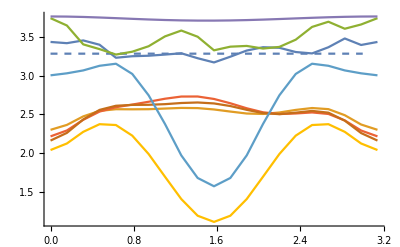

```mathematica
Show[Plot[0*x+c/.{c->3.281937853012085},{x,0,3},PlotStyle->Dashed],ListLinePlot[{fibo16max,fibo16mean,fibo32max,fibo32mean,fibo64max,fibo64mean,fibomax,fibomean}],PlotRange->All]
```

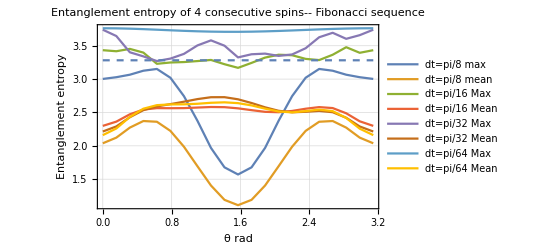

```mathematica
Show[ListLinePlot[{fibomax,fibomean,fibo16max,fibo16mean,fibo32max,fibo32mean,fibo64max,fibo64mean},PlotTheme->"Detailed",PlotLegends->Placed[{"dt=pi/8 max","dt=pi/8 mean ","dt=pi/16 Max","dt=pi/16 Mean","dt=pi/32 Max","dt=pi/32 Mean","dt=pi/64 Max","dt=pi/64 Mean"},{0.8,0.2}]],Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],PlotRange->All,FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[θ rad],None}},PlotLabel->HoldForm[Entanglement entropy of 4 consecutive spins -- Fibonacci sequence],LabelStyle->{FontFamily->"TeX Gyre Pagella",RGBColor[0.,0.,0.]},LabelStyle->{17,GrayLevel[0]}]
```

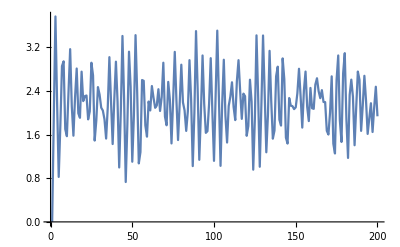

```mathematica
ListLinePlot[fibo64n[[21]]]
```

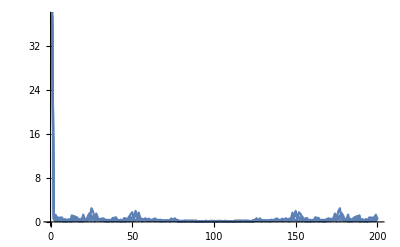

```mathematica
Show[ListLinePlot[Abs[Fourier[fibo64n[[10]]]],PlotRange->All],ListLinePlot[Abs[Fourier[rd64n[[10]]]],PlotRange->All],ListLinePlot[Abs[Fourier[tm64n[[10]]]],PlotRange->All],ListLinePlot[Abs[Fourier[tm16n[[10]]]],PlotRange->All]]
```

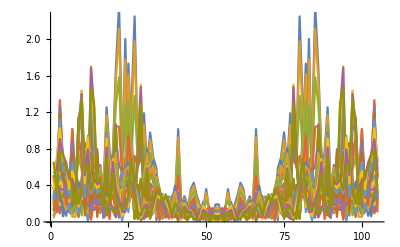

```mathematica
Show[ListLinePlot[Table[Abs[Fourier[Table[Drop[fibo64n[[m]],5][[n]]-fibo64mean[[m]][[2]],{n,1,105}]]],{m,1,10}],PlotRange->All],ListLinePlot[Table[Abs[Fourier[Table[Drop[fibo32n[[m]],5][[n]]-fibo32mean[[m]][[2]],{n,1,105}]]],{m,1,10}],PlotRange->All],ListLinePlot[Table[Abs[Fourier[Table[Drop[fibo16n[[m]],5][[n]]-fibo16mean[[m]][[2]],{n,1,105}]]],{m,1,10}],PlotRange->All]]
```

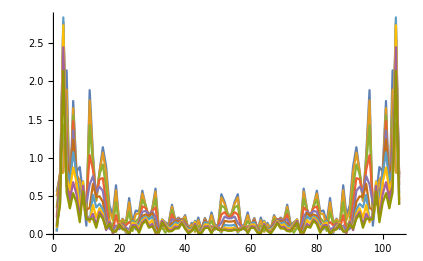

```mathematica
ListLinePlot[Table[Abs[Fourier[Table[Drop[fibon[[m]],5][[n]]-fibomean[[m]][[2]],{n,1,105}]]],{m,1,10}],PlotRange->All]
```

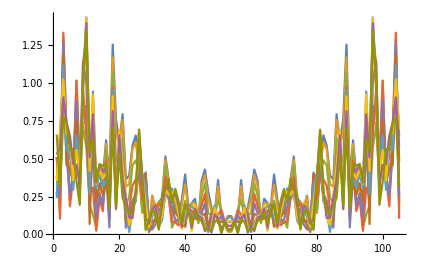

```mathematica
ListLinePlot[Table[Abs[Fourier[Table[Drop[fibo16n[[m]],5][[n]]-fibo16mean[[m]][[2]],{n,1,105}]]],{m,1,10}],PlotRange->All]
```

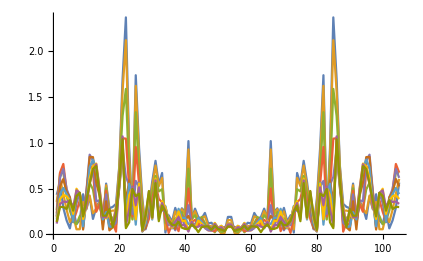

```mathematica
ListLinePlot[Table[Abs[Fourier[Table[Drop[fibo32n[[m]],5][[n]]-fibo32mean[[m]][[2]],{n,1,105}]]],{m,1,10}],PlotRange->All]
```

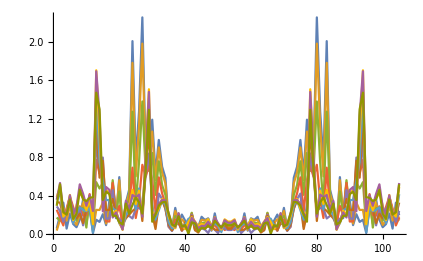

```mathematica
ListLinePlot[Table[Abs[Fourier[Table[Drop[fibo64n[[m]],5][[n]]-fibo64mean[[m]][[2]],{n,1,105}]]],{m,1,10}],PlotRange->All]
```

## dt = pi/4

#### data

```mathematica
fibo4=Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/fibo4.dat"]]
```

{}

## Kicked interaction term

## dt = pi/8

#### data

```mathematica
data8={-0.000000000000000000*10^+00,1.201752073385713215*10^+00,-1.922055902288951571*10^-15,1.201752073385713659*10^+00,1.404764034988924770*10^+00,1.201752073385712993*10^+00,1.404764034988926102*10^+00,1.201752073385712993*10^+00,1.404764034988926991*10^+00,1.624883029461677175*10^+00,1.404764034988926991*10^+00,1.624883029461677175*10^+00,1.593851164854307889*10^+00,1.624883029461680506*10^+00,1.593851164854311442*10^+00,1.624883029461686057*10^+00,1.593851164854315883*10^+00,8.216731072033597316*10^-01,1.593851164854314995*10^+00,8.216731072033574002*10^-01,1.593851164854315217*10^+00,8.216731072033552907*10^-01,1.290544393841768223*10^+00,8.216731072033532923*10^-01,1.290544393841769111*10^+00,4.495892585821167908*10^-01,1.290544393841767334*10^+00,4.495892585821136267*10^-01,1.290544393841766446*10^+00,4.495892585821117393*10^-01,1.171533725585264474*10^+00,4.495892585821109066*10^-01,1.171533725585266250*10^+00,1.700309114777321717*10^+00,1.171533725585267138*10^+00,1.700309114777323938*10^+00,1.171533725585268471*10^+00,1.700309114777325714*10^+00,1.273741385706500973*10^+00,1.700309114777325714*10^+00,1.273741385706498530*10^+00,1.700309114777324382*10^+00,1.273741385706494977*10^+00,1.435086477961441620*10^+00,1.273741385706495644*10^+00,1.435086477961442730*10^+00,7.942844088297775773*10^-01,1.435086477961441398*10^+00,7.942844088297733585*10^-01,1.435086477961439622*10^+00,7.942844088297695837*10^-01,1.574682138150321098*10^+00,7.942844088297691396*10^-01,1.574682138150323096*10^+00,7.942844088297698057*10^-01,1.574682138150324651*10^+00,1.004172845183166185*10^+00,1.574682138150326427*10^+00,1.004172845183166851*10^+00,8.407056156422155757*10^-01,1.004172845183166851*10^+00,8.407056156422145765*10^-01,1.004172845183165963*10^+00,8.407056156422132442*10^-01,1.573483708331500308*10^+00,8.407056156422154647*10^-01,1.573483708331501196*10^+00,8.025282191919659303*10^-01,1.573483708331500530*10^+00,8.025282191919624886*10^-01,1.573483708331498976*10^+00,8.025282191919590469*10^-01,1.516506993800252445*10^+00,8.025282191919579367*10^-01,1.516506993800255776*10^+00,8.025282191919566044*10^-01,1.516506993800258440*10^+00,1.299173967532553542*10^+00,1.516506993800258885*10^+00,1.299173967532554652*10^+00,1.588692277252789831*10^+00,1.299173967532553098*10^+00,1.588692277252789165*10^+00,1.299173967532550655*10^+00,1.588692277252789387*10^+00,1.223541710382038739*10^+00,1.588692277252792051*10^+00,1.223541710382039849*10^+00,2.808572368304490530*10^-01,1.223541710382039849*10^+00,2.808572368304477207*10^-01,1.223541710382039849*10^+00,2.808572368304454447*10^-01,1.273880544614202526*10^+00,2.808572368304442790*10^-01,1.273880544614202748*10^+00,2.808572368304400602*10^-01,1.273880544614203192*10^+00,1.067643082990746617*10^+00,1.273880544614202304*10^+00,1.067643082990744174*10^+00,1.717197516560081461*10^+00,1.067643082990743286*10^+00,1.717197516560083015*10^+00,1.067643082990742398*10^+00,1.717197516560084569*10^+00,1.542862855958116342*10^+00,1.717197516560089010*10^+00,1.542862855958120338*10^+00,1.717197516560093007*10^+00,1.542862855958124335*10^+00,1.171833367822170846*10^+00,1.542862855958122781*10^+00,1.171833367822170402*10^+00,1.201319257815542718*10^+00,1.171833367822171068*10^+00,1.201319257815542940*10^+00,1.171833367822171290*10^+00,1.201319257815543384*10^+00,1.029728895711623238*10^-01,1.201319257815541608*10^+00,1.029728895711564535*10^-01,1.201771017359967386*10^+00,1.029728895711539416*10^-01,1.201771017359968940*10^+00,1.029728895711511244*10^-01,1.201771017359969829*10^+00,1.596379878908960048*10^+00,1.201771017359970273*10^+00,1.596379878908961603*10^+00,1.201771017359970939*10^+00,1.596379878908962713*10^+00,1.644026116717737462*10^+00,1.596379878908962713*10^+00,1.644026116717736130*10^+00,1.476051951883194713*10^+00,1.644026116717741015*10^+00,1.476051951883197377*10^+00,1.644026116717746122*10^+00,1.476051951883199598*10^+00,6.300917220024216947*10^-01,1.476051951883197377*10^+00,6.300917220024179199*10^-01,1.476051951883197155*10^+00,6.300917220024147003*10^-01,1.347384800099503233*10^+00,6.300917220024124799*10^-01,1.347384800099505231*10^+00,6.734784066409523762*10^-01,1.347384800099504787*10^+00,6.734784066409515990*10^-01,1.347384800099503677*10^+00,6.734784066409520431*10^-01,1.118983825496075113*10^+00,6.734784066409512659*10^-01,1.118983825496075557*10^+00,1.779825274544859948*10^+00,1.118983825496077333*10^+00,1.779825274544862612*10^+00,1.118983825496078888*10^+00,1.779825274544866387*10^+00,1.196918368099465724*10^+00,1.779825274544866165*10^+00,1.196918368099465058*10^+00,1.779825274544866831*10^+00,1.196918368099464836*10^+00,1.413613574138928630*10^+00,1.196918368099465058*10^+00,1.413613574138928852*10^+00,7.853968091773084748*10^-01,1.413613574138927298*10^+00,7.853968091773050331*10^-01,1.413613574138925966*10^+00,7.853968091773017024*10^-01,1.542048532575353681*10^+00,7.853968091773025906*10^-01,1.542048532575356345*10^+00,1.193550880858220253*10^+00,1.542048532575357456*10^+00,1.193550880858219809*10^+00,1.542048532575358344*10^+00,1.193550880858220697*10^+00,7.358226898921034209*10^-01,1.193550880858221364*10^+00,7.358226898921031989*10^-01,1.193550880858220697*10^+00,7.358226898921017556*10^-01,1.541426793484410585*10^+00,7.358226898921025327*10^-01,1.541426793484412139*10^+00,8.399863456988028165*10^-01,1.541426793484410585*10^+00,8.399863456987988197*10^-01,1.541426793484409252*10^+00,8.399863456987943788*10^-01,1.617288949663863384*10^+00,8.399863456987910482*10^-01,1.617288949663866271*10^+00,8.399863456987889387*10^-01,1.617288949663868713*10^+00,2.722912528242654327*10^-14,1.157960598926154550*10^+00,2.594775468090060106*10^-14,1.157960598926154772*10^+00,1.354187576380420088*10^+00,1.157960598926153217*10^+00,1.354187576380418534*10^+00,1.157960598926152329*10^+00,1.354187576380419200*10^+00,1.600940457377414416*10^+00,1.354187576380419866*10^+00,1.600940457377413528*10^+00,1.627287299271845900*10^+00,1.600940457377417525*10^+00,1.627287299271849896*10^+00,1.600940457377422632*10^+00,1.627287299271853005*10^+00,9.471409948758617858*10^-01,1.627287299271851895*10^+00,9.471409948758563457*10^-01,1.627287299271849008*10^+00,9.471409948758513497*10^-01,1.381424898542062962*10^+00,9.471409948758495734*10^-01,1.381424898542062962*10^+00,6.117533077139740705*10^-01,1.381424898542062296*10^+00,6.117533077139722941*10^-01,1.381424898542060742*10^+00,6.117533077139718500*10^-01,1.276055676427986674*10^+00,6.117533077139704067*10^-01,1.276055676427987784*10^+00,1.648359785954858658*10^+00,1.276055676427987562*10^+00,1.648359785954860879*10^+00,1.276055676427987340*10^+00,1.648359785954861323*10^+00,1.239541052132851817*10^+00,1.648359785954860657*10^+00,1.239541052132849597*10^+00,1.648359785954859325*10^+00,1.239541052132848709*10^+00,1.429661395172578509*10^+00,1.239541052132847598*10^+00,1.429661395172578064*10^+00,7.484305579237989781*10^-01,1.429661395172576954*10^+00,7.484305579237972017*10^-01,1.429661395172574956*10^+00,7.484305579237933159*10^-01,1.516617465218491168*10^+00,7.484305579237928718*10^-01,1.516617465218492944*10^+00,7.484305579237912065*10^-01,1.516617465218492944*10^+00,1.018286735112367225*10^+00,1.516617465218493610*10^+00,1.018286735112367225*10^+00,9.167665905746894550*10^-01,1.018286735112366115*10^+00,9.167665905746888999*10^-01,1.018286735112364783*10^+00,9.167665905746902322*10^-01,1.566276817892252149*10^+00,9.167665905746915644*10^-01,1.566276817892253037*10^+00,8.822957320730006048*10^-01,1.566276817892253259*10^+00,8.822957320729987174*10^-01,1.566276817892252593*10^+00,8.822957320729964970*10^-01,1.524034925008677099*10^+00,8.822957320729938324*10^-01,1.524034925008679098*10^+00,8.822957320729902797*10^-01,1.524034925008681762*10^+00,1.395264504262495375*10^+00,1.524034925008680874*10^+00,1.395264504262496263*10^+00,1.631038888904447814*10^+00,1.395264504262494487*10^+00,1.631038888904448259*10^+00,1.395264504262493155*10^+00,1.631038888904447814*10^+00,1.252647916630836855*10^+00,1.631038888904449813*10^+00,1.252647916630838854*10^+00,4.005904579171699065*10^-01,1.252647916630837077*10^+00,4.005904579171638002*10^-01,1.252647916630834191*10^+00,4.005904579171585822*10^-01,1.310489617419849262*10^+00,4.005904579171580826*10^-01,1.310489617419849706*10^+00,4.005904579171554736*10^-01,1.310489617419848818*10^+00,1.021394426799546062*10^+00,1.310489617419847264*10^+00,1.021394426799543176*10^+00,1.686109769195959007*10^+00,1.021394426799540511*10^+00,1.686109769195959229*10^+00,1.021394426799539401*10^+00,1.686109769195961228*10^+00,1.598566912232003201*10^+00,1.686109769195965669*10^+00,1.598566912232004977*10^+00,1.686109769195968333*10^+00,1.598566912232008086*10^+00,1.272358964556114636*10^+00,1.598566912232007420*10^+00,1.272358964556114191*10^+00,1.297838058333246725*10^+00,1.272358964556114858*10^+00,1.297838058333247391*10^+00,1.272358964556116634*10^+00,1.297838058333249167*10^+00,2.714670737929518740*10^-01,1.297838058333247169*10^+00,2.714670737929470445*10^-01,1.279108758236806587*10^+00,2.714670737929464339*10^-01,1.279108758236807697*10^+00,2.714670737929462674*10^-01,1.279108758236808807*10^+00,1.628956799245442566*10^+00,1.279108758236808585*10^+00,1.628956799245442344*10^+00,1.279108758236808363*10^+00,1.628956799245442788*10^+00,1.662647384940975748*10^+00,1.628956799245443676*10^+00,1.662647384940975304*10^+00,1.500974101945544259*10^+00,1.662647384940978856*10^+00,1.500974101945546924*10^+00,1.662647384940983741*10^+00,1.500974101945550032*10^+00,7.016864015795034604*10^-01,1.500974101945550476*10^+00,7.016864015795004628*10^-01,1.500974101945548922*10^+00,7.016864015794974652*10^-01,1.364344536023777810*10^+00,7.016864015794950227*10^-01,1.364344536023778698*10^+00,6.656747988368441060*10^-01,1.364344536023778254*10^+00,6.656747988368423297*10^-01,1.364344536023777810*10^+00,6.656747988368421076*10^-01,1.149225090964741236*10^+00,6.656747988368416635*10^-01,1.149225090964742346*10^+00,1.757148392914550161*10^+00,1.149225090964743901*10^+00,1.757148392914552604*10^+00,1.149225090964745455*10^+00,1.757148392914555046*10^+00,1.250227480584856998*10^+00,1.757148392914552382*10^+00,1.250227480584853001*10^+00,1.757148392914551716*10^+00,1.250227480584849227*10^+00,1.478608387871149565*10^+00,1.250227480584849227*10^+00,1.478608387871149787*10^+00,9.302625286723682496*10^-01,1.478608387871147789*10^+00,9.302625286723629205*10^-01,1.478608387871145347*10^+00,9.302625286723580356*10^-01,1.584139022434710053*10^+00,9.302625286723580356*10^-01,1.584139022434710942*10^+00,1.284476244719538807*10^+00,1.584139022434710942*10^+00,1.284476244719540139*10^+00,1.584139022434713384*10^+00,1.284476244719541027*10^+00,8.612647897823394461*10^-01,1.284476244719541915*10^+00,8.612647897823395571*10^-01,1.284476244719542137*10^+00,8.612647897823393350*10^-01,1.541792766126381053*10^+00,8.612647897823413334*10^-01,1.541792766126382386*10^+00,8.491350418527088273*10^-01,1.541792766126381498*10^+00,8.491350418527049415*10^-01,1.541792766126380165*10^+00,8.491350418527022770*10^-01,1.603133487757220976*10^+00,8.491350418526992794*10^-01,1.603133487757223641*10^+00,8.491350418526959487*10^-01,1.603133487757224751*10^+00,-9.610279511444755881*10^-16,1.033390542523312527*10^+00,4.805139755722374982*10^-16,1.033390542523312305*10^+00,1.221949211164784721*10^+00,1.033390542523310751*10^+00,1.221949211164785609*10^+00,1.033390542523309197*10^+00,1.221949211164782723*10^+00,1.535324982625510870*10^+00,1.221949211164783611*10^+00,1.535324982625510426*10^+00,1.690624636963498961*10^+00,1.535324982625513313*10^+00,1.690624636963502514*10^+00,1.535324982625515755*10^+00,1.690624636963506067*10^+00,1.193393155189210741*10^+00,1.690624636963505845*10^+00,1.193393155189211630*10^+00,1.690624636963508287*10^+00,1.193393155189210519*10^+00,1.492742957808424586*10^+00,1.193393155189209187*10^+00,1.492742957808425697*10^+00,9.602870581271435446*10^-01,1.492742957808424142*10^+00,9.602870581271408801*10^-01,1.492742957808422144*10^+00,9.602870581271388817*10^-01,1.460892347312861439*10^+00,9.602870581271408801*10^-01,1.460892347312864548*10^+00,1.581581842653891901*10^+00,1.460892347312866990*10^+00,1.581581842653893899*10^+00,1.460892347312868988*10^+00,1.581581842653895453*10^+00,1.254477586730411653*10^+00,1.581581842653894565*10^+00,1.254477586730408989*10^+00,1.581581842653891234*10^+00,1.254477586730406991*10^+00,1.463402689591172479*10^+00,1.254477586730406768*10^+00,1.463402689591171146*10^+00,7.060262793902594147*10^-01,1.463402689591170258*10^+00,7.060262793902557510*10^-01,1.463402689591168482*10^+00,7.060262793902525313*10^-01,1.445815846543469840*10^+00,7.060262793902513101*10^-01,1.445815846543470951*10^+00,7.060262793902503109*10^-01,1.445815846543472949*10^+00,1.133247279526740758*10^+00,1.445815846543473615*10^+00,1.133247279526742313*10^+00,1.130328214970782952*10^+00,1.133247279526741425*10^+00,1.130328214970782286*10^+00,1.133247279526740536*10^+00,1.130328214970782730*10^+00,1.596519051282909718*10^+00,1.130328214970782952*10^+00,1.596519051282912383*10^+00,1.084405507449696326*10^+00,1.596519051282911938*10^+00,1.084405507449694106*10^+00,1.596519051282911716*10^+00,1.084405507449692108*10^+00,1.562623150609863121*10^+00,1.084405507449687445*10^+00,1.562623150609865119*10^+00,1.084405507449685224*10^+00,1.562623150609867562*10^+00,1.598574993529473742*10^+00,1.562623150609865785*10^+00,1.598574993529475297*10^+00,1.755905476986531433*10^+00,1.598574993529476407*10^+00,1.755905476986531433*10^+00,1.598574993529476185*10^+00,1.755905476986532321*10^+00,1.393735098407410611*10^+00,1.755905476986535430*10^+00,1.393735098407412831*10^+00,7.149647377034495932*10^-01,1.393735098407411499*10^+00,7.149647377034482609*10^-01,1.393735098407411277*10^+00,7.149647377034473728*10^-01,1.398243552957666225*10^+00,7.149647377034443751*10^-01,1.398243552957666669*10^+00,7.149647377034429319*10^-01,1.398243552957668001*10^+00,9.778714725567391186*10^-01,1.398243552957666447*10^+00,9.778714725567384525*10^-01,1.690208214598817760*10^+00,9.778714725567372312*10^-01,1.690208214598817982*10^+00,9.778714725567363431*10^-01,1.690208214598819980*10^+00,1.752834798814231876*10^+00,1.690208214598822201*10^+00,1.752834798814235207*10^+00,1.690208214598823755*10^+00,1.752834798814237427*10^+00,1.531496463050975088*10^+00,1.752834798814236095*10^+00,1.531496463050975532*10^+00,1.515754643745117924*10^+00,1.531496463050976198*10^+00,1.515754643745118369*10^+00,1.531496463050977530*10^+00,1.515754643745120367*10^+00,6.719551458982223613*10^-01,1.515754643745119479*10^+00,6.719551458982193637*10^-01,1.394677335377618732*10^+00,6.719551458982180314*10^-01,1.394677335377619842*10^+00,6.719551458982172543*10^-01,1.394677335377621619*10^+00,1.707631098803442438*10^+00,1.394677335377621619*10^+00,1.707631098803443548*10^+00,1.394677335377623395*10^+00,1.707631098803444436*10^+00,1.742854740154473836*10^+00,1.707631098803444880*10^+00,1.742854740154474058*10^+00,1.588879139727462864*10^+00,1.742854740154477611*10^+00,1.588879139727465528*10^+00,1.742854740154481386*10^+00,1.588879139727468637*10^+00,9.215577329205868473*10^-01,1.588879139727466416*10^+00,9.215577329205834056*10^-01,1.588879139727464640*10^+00,9.215577329205795198*10^-01,1.412037283144204514*10^+00,9.215577329205761892*10^-01,1.412037283144204736*10^+00,6.805442415930942346*10^-01,1.412037283144206290*10^+00,6.805442415930931244*10^-01,1.412037283144205624*10^+00,6.805442415930922362*10^-01,1.200102615918702043*10^+00,6.805442415930937905*10^-01,1.200102615918705595*10^+00,1.696653146948738478*10^+00,1.200102615918705151*10^+00,1.696653146948738922*10^+00,1.200102615918706039*10^+00,1.696653146948740698*10^+00,1.381482097914331408*10^+00,1.696653146948742030*10^+00,1.381482097914331408*10^+00,1.696653146948742030*10^+00,1.381482097914330520*10^+00,1.603634434583275592*10^+00,1.381482097914329632*10^+00,1.603634434583276480*10^+00,1.178473083875698046*10^+00,1.603634434583274260*10^+00,1.178473083875695160*10^+00,1.603634434583273816*10^+00,1.178473083875691163*10^+00,1.643909995443675776*10^+00,1.178473083875691829*10^+00,1.643909995443675776*10^+00,1.447766951068834018*10^+00,1.643909995443677552*10^+00,1.447766951068834240*10^+00,1.643909995443679550*10^+00,1.447766951068836017*10^+00,1.113000262700309051*10^+00,1.447766951068836239*10^+00,1.113000262700309717*10^+00,1.447766951068837127*10^+00,1.113000262700309939*10^+00,1.536029622438283671*10^+00,1.113000262700312382*10^+00,1.536029622438286113*10^+00,9.434122309147415786*10^-01,1.536029622438284337*10^+00,9.434122309147382479*10^-01,1.536029622438284115*10^+00,9.434122309147369156*10^-01,1.597797469598064790*10^+00,9.434122309147332519*10^-01,1.597797469598066122*10^+00,9.434122309147294771*10^-01,1.597797469598067455*10^+00,9.610279511444749964*10^-16,8.474263344968486766*10^-01,-6.086510357248356435*10^-15,8.474263344968471223*10^-01,1.054831036137992450*10^+00,8.474263344968467893*10^-01,1.054831036137993339*10^+00,8.474263344968474554*10^-01,1.054831036137994005*10^+00,1.486339494964282748*10^+00,1.054831036137992895*10^+00,1.486339494964283414*10^+00,1.722189931713453914*10^+00,1.486339494964285635*10^+00,1.722189931713457689*10^+00,1.486339494964288299*10^+00,1.722189931713461242*10^+00,1.480923794119038961*10^+00,1.722189931713462352*10^+00,1.480923794119038517*10^+00,1.722189931713464128*10^+00,1.480923794119038517*10^+00,1.616538443860542129*10^+00,1.480923794119036963*10^+00,1.616538443860543905*10^+00,1.304112293644603904*10^+00,1.616538443860541907*10^+00,1.304112293644600795*10^+00,1.616538443860540353*10^+00,1.304112293644599907*10^+00,1.638199709963368944*10^+00,1.304112293644599907*10^+00,1.638199709963373607*10^+00,1.646292484561453717*10^+00,1.638199709963375827*10^+00,1.646292484561455494*10^+00,1.638199709963374939*10^+00,1.646292484561458158*10^+00,1.480233277618917764*10^+00,1.646292484561454383*10^+00,1.480233277618915322*10^+00,1.646292484561452607*10^+00,1.480233277618913323*10^+00,1.600570145905262809*10^+00,1.480233277618913323*10^+00,1.600570145905263253*10^+00,7.861499049313811494*10^-01,1.600570145905260144*10^+00,7.861499049313773746*10^-01,1.600570145905259700*10^+00,7.861499049313724896*10^-01,1.517477423093684497*10^+00,7.861499049313708243*10^-01,1.517477423093683164*10^+00,7.861499049313698251*10^-01,1.517477423093686273*10^+00,1.358557776299870845*10^+00,1.517477423093687161*10^+00,1.358557776299873066*10^+00,1.411547593009240043*10^+00,1.358557776299870179*10^+00,1.411547593009239376*10^+00,1.358557776299869069*10^+00,1.411547593009238710*10^+00,1.667785277755063245*10^+00,1.411547593009238266*10^+00,1.667785277755065021*10^+00,1.385321852002265652*10^+00,1.667785277755064577*10^+00,1.385321852002264986*10^+00,1.667785277755064133*10^+00,1.385321852002263432*10^+00,1.650376973447430506*10^+00,1.385321852002259657*10^+00,1.650376973447432727*10^+00,1.385321852002258991*10^+00,1.650376973447432727*10^+00,1.784559887011982982*10^+00,1.650376973447432949*10^+00,1.784559887011983648*10^+00,1.907324393395973150*10^+00,1.784559887011984092*10^+00,1.907324393395972928*10^+00,1.784559887011983648*10^+00,1.907324393395974260*10^+00,1.677340426999866407*10^+00,1.907324393395977813*10^+00,1.677340426999868628*10^+00,1.075022185769579419*10^+00,1.677340426999867962*10^+00,1.075022185769576755*10^+00,1.677340426999866629*10^+00,1.075022185769574534*10^+00,1.542065238009806549*10^+00,1.075022185769573202*10^+00,1.542065238009808770*10^+00,1.075022185769574312*10^+00,1.542065238009808992*10^+00,1.069881106766099377*10^+00,1.542065238009806993*10^+00,1.069881106766097378*10^+00,1.810767322034035898*10^+00,1.069881106766096712*10^+00,1.810767322034037896*10^+00,1.069881106766095824*10^+00,1.810767322034039672*10^+00,1.904714586047786984*10^+00,1.810767322034042337*10^+00,1.904714586047789648*10^+00,1.810767322034044335*10^+00,1.904714586047792757*10^+00,1.823078327542897004*10^+00,1.904714586047791869*10^+00,1.823078327542897004*10^+00,1.758639173457294147*10^+00,1.823078327542895449*10^+00,1.758639173457295257*10^+00,1.823078327542896115*10^+00,1.758639173457295701*10^+00,1.111728531367547790*10^+00,1.758639173457295257*10^+00,1.111728531367543793*10^+00,1.482582951465378995*10^+00,1.111728531367543571*10^+00,1.482582951465379661*10^+00,1.111728531367543349*10^+00,1.482582951465381216*10^+00,1.800382595822133336*10^+00,1.482582951465382104*10^+00,1.800382595822134668*10^+00,1.482582951465381660*10^+00,1.800382595822135556*10^+00,1.901636896928785569*10^+00,1.800382595822135334*10^+00,1.901636896928785792*10^+00,1.708206352451334453*10^+00,1.901636896928790454*10^+00,1.708206352451336452*10^+00,1.901636896928793563*10^+00,1.708206352451341337*10^+00,1.121264891165944189*10^+00,1.708206352451339782*10^+00,1.121264891165942856*10^+00,1.708206352451338006*10^+00,1.121264891165940192*10^+00,1.454385932875439824*10^+00,1.121264891165939748*10^+00,1.454385932875440712*10^+00,7.158085897249578666*10^-01,1.454385932875442711*10^+00,7.158085897249575336*10^-01,1.454385932875442711*10^+00,7.158085897249566454*10^-01,1.215520491200853037*10^+00,7.158085897249553131*10^-01,1.215520491200854591*10^+00,1.616005825457775824*10^+00,1.215520491200855036*10^+00,1.616005825457776046*10^+00,1.215520491200855258*10^+00,1.616005825457777156*10^+00,1.547492540105335213*10^+00,1.616005825457777600*10^+00,1.547492540105334990*10^+00,1.616005825457775824*10^+00,1.547492540105335213*10^+00,1.756424841469914178*10^+00,1.547492540105332992*10^+00,1.756424841469916176*10^+00,1.435862603823934380*10^+00,1.756424841469914844*10^+00,1.435862603823932160*10^+00,1.756424841469915510*10^+00,1.435862603823929717*10^+00,1.707636538113913582*10^+00,1.435862603823927941*10^+00,1.707636538113912916*10^+00,1.652039203414096935*10^+00,1.707636538113914471*10^+00,1.652039203414097379*10^+00,1.707636538113914471*10^+00,1.652039203414097823*10^+00,1.344919931561073589*10^+00,1.652039203414099600*10^+00,1.344919931561075366*10^+00,1.652039203414101376*10^+00,1.344919931561076698*10^+00,1.578518252590228155*10^+00,1.344919931561077586*10^+00,1.578518252590229709*10^+00,1.147869961978228659*10^+00,1.578518252590226822*10^+00,1.147869961978226883*10^+00,1.578518252590226378*10^+00,1.147869961978226216*10^+00,1.653187059910505186*10^+00,1.147869961978224218*10^+00,1.653187059910508960*10^+00,1.147869961978221998*10^+00,1.653187059910510515*10^+00,4.805139755722374982*10^-16,6.289791881778438176*10^-01,9.610279511444749964*10^-16,6.289791881778451499*10^-01,9.038853705994700505*10^-01,6.289791881778444838*10^-01,9.038853705994694954*10^-01,6.289791881778444838*10^-01,9.038853705994707166*10^-01,1.477065462886882674*10^+00,9.038853705994702725*10^-01,1.477065462886884006*10^+00,1.733455949730731804*10^+00,1.477065462886884228*10^+00,1.733455949730735135*10^+00,1.477065462886885783*10^+00,1.733455949730737577*10^+00,1.711733765382827066*10^+00,1.733455949730738910*10^+00,1.711733765382827510*10^+00,1.733455949730741352*10^+00,1.711733765382828620*10^+00,1.751258672372667968*10^+00,1.711733765382825734*10^+00,1.751258672372669967*10^+00,1.582003024577644412*10^+00,1.751258672372667080*10^+00,1.582003024577641526*10^+00,1.751258672372665748*10^+00,1.582003024577639083*10^+00,1.785375895893138942*10^+00,1.582003024577639083*10^+00,1.785375895893141607*10^+00,1.849809462360430201*10^+00,1.785375895893142495*10^+00,1.849809462360432422*10^+00,1.785375895893142051*10^+00,1.849809462360432422*10^+00,1.809787676485842267*10^+00,1.849809462360429979*10^+00,1.809787676485840713*10^+00,1.849809462360428203*10^+00,1.809787676485838714*10^+00,1.784218789616904166*10^+00,1.809787676485840047*10^+00,1.784218789616905720*10^+00,9.618037075433782945*10^-01,1.784218789616901502*10^+00,9.618037075433755190*10^-01,1.784218789616901946*10^+00,9.618037075433740757*10^-01,1.651671650066041552*10^+00,9.618037075433727434*10^-01,1.651671650066042218*10^+00,9.618037075433722993*10^-01,1.651671650066042663*10^+00,1.590038276368892056*10^+00,1.651671650066044439*10^+00,1.590038276368895831*10^+00,1.638385162727981292*10^+00,1.590038276368894277*10^+00,1.638385162727981292*10^+00,1.590038276368893833*10^+00,1.638385162727983069*10^+00,1.752824964302413635*10^+00,1.638385162727981736*10^+00,1.752824964302414745*10^+00,1.712255216635794719*10^+00,1.752824964302414967*10^+00,1.712255216635795385*10^+00,1.752824964302413413*10^+00,1.712255216635794719*10^+00,1.765848322120959102*10^+00,1.712255216635791388*10^+00,1.765848322120960656*10^+00,1.712255216635791832*10^+00,1.765848322120961100*10^+00,1.904977414474407604*10^+00,1.765848322120961766*10^+00,1.904977414474408492*10^+00,2.058469578806402467*10^+00,1.904977414474409603*10^+00,2.058469578806402911*10^+00,1.904977414474409381*10^+00,2.058469578806403355*10^+00,2.002645443809293102*10^+00,2.058469578806406020*10^+00,2.002645443809296211*10^+00,1.393088230444414100*10^+00,2.002645443809293990*10^+00,1.393088230444412101*10^+00,2.002645443809293990*10^+00,1.393088230444411657*10^+00,1.693734481042145523*10^+00,1.393088230444411657*10^+00,1.693734481042146411*10^+00,1.393088230444412545*10^+00,1.693734481042147966*10^+00,1.249893434541358817*10^+00,1.693734481042145301*10^+00,1.249893434541357484*10^+00,1.938118799430912143*10^+00,1.249893434541356152*10^+00,1.938118799430914141*10^+00,1.249893434541353932*10^+00,1.938118799430915029*10^+00,2.035279195471559444*10^+00,1.938118799430917472*10^+00,2.035279195471561664*10^+00,1.938118799430920136*10^+00,2.035279195471563440*10^+00,2.059748980415435415*10^+00,2.035279195471564329*10^+00,2.059748980415436304*10^+00,1.983816008746395188*10^+00,2.059748980415436748*10^+00,1.983816008746396076*10^+00,2.059748980415437636*10^+00,1.983816008746396520*10^+00,1.498574690788569086*10^+00,1.983816008746396520*10^+00,1.498574690788568198*10^+00,1.558191508606274978*10^+00,1.498574690788569530*10^+00,1.558191508606274978*10^+00,1.498574690788567310*10^+00,1.558191508606277198*10^+00,1.844179491319727582*10^+00,1.558191508606277198*10^+00,1.844179491319728470*10^+00,1.558191508606276754*10^+00,1.844179491319728914*10^+00,2.043761351691160133*10^+00,1.844179491319729580*10^+00,2.043761351691161465*10^+00,1.829804810577969842*10^+00,2.043761351691165018*10^+00,1.829804810577972507*10^+00,2.043761351691167683*10^+00,1.829804810577976060*10^+00,1.274808635254439659*10^+00,1.829804810577974061*10^+00,1.274808635254437217*10^+00,1.829804810577973395*10^+00,1.274808635254438549*10^+00,1.499655123460161388*10^+00,1.274808635254438549*10^+00,1.499655123460162054*10^+00,8.068711713417822118*10^-01,1.499655123460164940*10^+00,8.068711713417812126*10^-01,1.499655123460164718*10^+00,8.068711713417805464*10^-01,1.207586407611893398*10^+00,8.068711713417821008*10^-01,1.207586407611897172*10^+00,1.566183857844545502*10^+00,1.207586407611896728*10^+00,1.566183857844544614*10^+00,1.207586407611896728*10^+00,1.566183857844545724*10^+00,1.731030294896087840*10^+00,1.566183857844544614*10^+00,1.731030294896088728*10^+00,1.566183857844544391*10^+00,1.731030294896088950*10^+00,1.919136531638073073*10^+00,1.731030294896086730*10^+00,1.919136531638074183*10^+00,1.670431315040308951*10^+00,1.919136531638074850*10^+00,1.670431315040309173*10^+00,1.919136531638074850*10^+00,1.670431315040309173*10^+00,1.805981042299631856*10^+00,1.670431315040305398*10^+00,1.805981042299632522*10^+00,1.838394046808669469*10^+00,1.805981042299632522*10^+00,1.838394046808668802*10^+00,1.805981042299633854*10^+00,1.838394046808669469*10^+00,1.582495066158014385*10^+00,1.838394046808669913*10^+00,1.582495066158016161*10^+00,1.838394046808671911*10^+00,1.582495066158017272*10^+00,1.664473522160802688*10^+00,1.582495066158018160*10^+00,1.664473522160804020*10^+00,1.428574798577567417*10^+00,1.664473522160801133*10^+00,1.428574798577564309*10^+00,1.664473522160799801*10^+00,1.428574798577560534*10^+00,1.772821241148093030*10^+00,1.428574798577560312*10^+00,1.772821241148095472*10^+00,1.428574798577558980*10^+00,1.772821241148098137*10^+00,3.203426503814917641*10^-16,4.115261085513831629*10^-01,2.722912528242677283*10^-15,4.115261085513856054*10^-01,8.813230580469832987*10^-01,4.115261085513843842*10^-01,8.813230580469834097*10^-01,4.115261085513837735*10^-01,8.813230580469831876*10^-01,1.505257948120920730*10^+00,8.813230580469815223*10^-01,1.505257948120921174*10^+00,1.761054294362025097*10^+00,1.505257948120922062*10^+00,1.761054294362027095*10^+00,1.505257948120923395*10^+00,1.761054294362029982*10^+00,1.951314137955960426*10^+00,1.761054294362032202*10^+00,1.951314137955961980*10^+00,1.761054294362033978*10^+00,1.951314137955962869*10^+00,1.903347374701459760*10^+00,1.951314137955960648*10^+00,1.903347374701459760*10^+00,1.765912117735660924*10^+00,1.903347374701458428*10^+00,1.765912117735660036*10^+00,1.903347374701456651*10^+00,1.765912117735658260*10^+00,1.944470466543930964*10^+00,1.765912117735658704*10^+00,1.944470466543933407*10^+00,2.075211394106776908*10^+00,1.944470466543933629*10^+00,2.075211394106779128*10^+00,1.944470466543934517*10^+00,2.075211394106779572*10^+00,2.122142959505416648*10^+00,2.075211394106776464*10^+00,2.122142959505415760*10^+00,2.075211394106775131*10^+00,2.122142959505414428*10^+00,1.960632154589473819*10^+00,2.122142959505416648*10^+00,1.960632154589475373*10^+00,1.163845894300378436*10^+00,1.960632154589471821*10^+00,1.163845894300376660*10^+00,1.960632154589471376*10^+00,1.163845894300375328*10^+00,1.753215613742600709*10^+00,1.163845894300374217*10^+00,1.753215613742600931*10^+00,1.163845894300371775*10^+00,1.753215613742600265*10^+00,1.793960447295010807*10^+00,1.753215613742600487*10^+00,1.793960447295011695*10^+00,1.772392665324544314*10^+00,1.793960447295011695*10^+00,1.772392665324544758*10^+00,1.793960447295011251*10^+00,1.772392665324545424*10^+00,1.827311436948270806*10^+00,1.772392665324544536*10^+00,1.827311436948270806*10^+00,1.998003200138317004*10^+00,1.827311436948270806*10^+00,1.998003200138316338*10^+00,1.827311436948271250*10^+00,1.998003200138316782*10^+00,1.884178941906937244*10^+00,1.998003200138314339*10^+00,1.884178941906937688*10^+00,1.998003200138315893*10^+00,1.884178941906939242*10^+00,1.939378398315414920*10^+00,1.884178941906939464*10^+00,1.939378398315416252*10^+00,2.196190887422055038*10^+00,1.939378398315414476*10^+00,2.196190887422055038*10^+00,1.939378398315414032*10^+00,2.196190887422054594*10^+00,2.245571233852633242*10^+00,2.196190887422056814*10^+00,2.245571233852635018*10^+00,1.599190298444292502*10^+00,2.245571233852635018*10^+00,1.599190298444292946*10^+00,2.245571233852634130*10^+00,1.599190298444292946*10^+00,1.786532790078734223*10^+00,1.599190298444293390*10^+00,1.786532790078735555*10^+00,1.599190298444293834*10^+00,1.786532790078736666*10^+00,1.405859891285550445*10^+00,1.786532790078734223*10^+00,1.405859891285549779*10^+00,1.964546085017500721*10^+00,1.405859891285548890*10^+00,1.964546085017501831*10^+00,1.405859891285548224*10^+00,1.964546085017504051*10^+00,2.099655582224182915*10^+00,1.964546085017505828*10^+00,2.099655582224185135*10^+00,1.964546085017507826*10^+00,2.099655582224186912*10^+00,2.177893328250037897*10^+00,2.099655582224186912*10^+00,2.177893328250040117*10^+00,2.124505539459100145*10^+00,2.177893328250039229*10^+00,2.124505539459101477*10^+00,2.177893328250040561*10^+00,2.124505539459102366*10^+00,1.774216246654014562*10^+00,2.124505539459101922*10^+00,1.774216246654015450*10^+00,1.576788788068276270*10^+00,1.774216246654015894*10^+00,1.576788788068276936*10^+00,1.774216246654015672*10^+00,1.576788788068276714*10^+00,1.883788931776065212*10^+00,1.576788788068278047*10^+00,1.883788931776066100*10^+00,1.576788788068278713*10^+00,1.883788931776066766*10^+00,2.172408240167229998*10^+00,1.883788931776067654*10^+00,2.172408240167230442*10^+00,1.932119837932493089*10^+00,2.172408240167232663*10^+00,1.932119837932493311*10^+00,2.172408240167233995*10^+00,1.932119837932495088*10^+00,1.387043222374588325*10^+00,1.932119837932496198*10^+00,1.387043222374587437*10^+00,1.932119837932495532*10^+00,1.387043222374587437*10^+00,1.575305453562839020*10^+00,1.387043222374588103*10^+00,1.575305453562839908*10^+00,9.266994450974878061*10^-01,1.575305453562843683*10^+00,9.266994450974874731*10^-01,1.575305453562843683*10^+00,9.266994450974853637*10^-01,1.184226882526070002*10^+00,9.266994450974881392*10^-01,1.184226882526072888*10^+00,1.609548431259958612*10^+00,1.184226882526072222*10^+00,1.609548431259958390*10^+00,1.184226882526071778*10^+00,1.609548431259958834*10^+00,1.933465669066363413*10^+00,1.609548431259957502*10^+00,1.933465669066364079*10^+00,1.609548431259957058*10^+00,1.933465669066363857*10^+00,2.077996519227645056*10^+00,1.933465669066362080*10^+00,2.077996519227645056*10^+00,1.910889346460684646*10^+00,2.077996519227645056*10^+00,1.910889346460685534*10^+00,2.077996519227646832*10^+00,1.910889346460686422*10^+00,1.951198148491806172*10^+00,1.910889346460683536*10^+00,1.951198148491804840*10^+00,2.002813310120774126*10^+00,1.951198148491805284*10^+00,2.002813310120774126*10^+00,1.951198148491806172*10^+00,2.002813310120773238*10^+00,1.810558829176119655*10^+00,2.002813310120775014*10^+00,1.810558829176121431*10^+00,2.002813310120775459*10^+00,1.810558829176122986*10^+00,1.830966570717510233*10^+00,1.810558829176122986*10^+00,1.830966570717510900*10^+00,1.715575462322367351*10^+00,1.830966570717508679*10^+00,1.715575462322365796*10^+00,1.830966570717507569*10^+00,1.715575462322364242*10^+00,1.894641330498778364*10^+00,1.715575462322364020*10^+00,1.894641330498779253*10^+00,1.715575462322362466*10^+00,1.894641330498780807*10^+00,-9.610279511444755881*10^-16,2.237564860125470512*10^-01,1.441541926716712396*10^-15,2.237564860125491606*10^-01,9.222185508746373328*10^-01,2.237564860125481891*10^-01,9.222185508746369997*10^-01,2.237564860125468846*10^-01,9.222185508746381100*10^-01,1.540334155404883720*10^+00,9.222185508746371108*10^-01,1.540334155404885053*10^+00,1.842158550126084648*10^+00,1.540334155404885497*10^+00,1.842158550126086425*10^+00,1.540334155404887939*10^+00,1.842158550126087979*10^+00,2.206958929457861984*10^+00,1.842158550126089311*10^+00,2.206958929457863317*10^+00,1.842158550126089755*10^+00,2.206958929457864205*10^+00,2.042989799844426191*10^+00,2.206958929457861096*10^+00,2.042989799844427079*10^+00,1.890076319638668956*10^+00,2.042989799844425747*10^+00,1.890076319638668956*10^+00,2.042989799844425303*10^+00,1.890076319638668956*10^+00,2.106054697205789417*10^+00,1.890076319638668734*10^+00,2.106054697205789861*10^+00,2.278314371377104575*10^+00,2.106054697205789417*10^+00,2.278314371377104575*10^+00,2.106054697205789861*10^+00,2.278314371377105463*10^+00,2.353318389999810023*10^+00,2.278314371377102354*10^+00,2.353318389999810023*10^+00,2.278314371377102354*10^+00,2.353318389999810023*10^+00,2.106636879681871743*10^+00,2.353318389999811355*10^+00,2.106636879681871743*10^+00,1.341221533274250310*10^+00,2.106636879681870411*10^+00,1.341221533274250977*10^+00,2.106636879681871299*10^+00,1.341221533274251199*10^+00,1.765505494626190108*10^+00,1.341221533274250310*10^+00,1.765505494626189886*10^+00,1.341221533274249422*10^+00,1.765505494626190330*10^+00,1.942267121122247975*10^+00,1.765505494626190108*10^+00,1.942267121122249085*10^+00,1.836220550283483632*10^+00,1.942267121122248419*10^+00,1.836220550283483632*10^+00,1.942267121122247975*10^+00,1.836220550283482744*10^+00,1.923295271163666165*10^+00,1.836220550283482966*10^+00,1.923295271163667053*10^+00,2.219937802526603221*10^+00,1.923295271163667275*10^+00,2.219937802526604109*10^+00,1.923295271163667275*10^+00,2.219937802526603665*10^+00,1.976446842263543724*10^+00,2.219937802526601445*10^+00,1.976446842263544168*10^+00,2.219937802526602777*10^+00,1.976446842263545056*10^+00,2.003163871461475232*10^+00,1.976446842263544834*10^+00,2.003163871461476120*10^+00,2.314887948203041557*10^+00,2.003163871461474344*10^+00,2.314887948203040668*10^+00,2.003163871461473899*10^+00,2.314887948203041113*10^+00,2.360017447201844476*10^+00,2.314887948203042445*10^+00,2.360017447201845364*10^+00,1.691077968594632441*10^+00,2.360017447201844032*10^+00,1.691077968594632663*10^+00,2.360017447201845364*10^+00,1.691077968594632885*10^+00,1.804595257042443501*10^+00,1.691077968594633552*10^+00,1.804595257042443723*10^+00,1.691077968594635550*10^+00,1.804595257042446166*10^+00,1.486742355765344303*10^+00,1.804595257042441725*10^+00,1.486742355765344747*10^+00,1.848474159871290157*10^+00,1.486742355765344081*10^+00,1.848474159871291711*10^+00,1.486742355765344081*10^+00,1.848474159871293043*10^+00,2.080938266287214677*10^+00,1.848474159871295264*10^+00,2.080938266287216454*10^+00,1.848474159871296596*10^+00,2.080938266287217786*10^+00,2.194782502812413050*10^+00,2.080938266287217786*10^+00,2.194782502812413494*10^+00,2.197731817474871008*10^+00,2.194782502812415270*10^+00,2.197731817474871896*10^+00,2.194782502812416602*10^+00,2.197731817474872784*10^+00,1.960292920322681987*10^+00,2.197731817474873228*10^+00,1.960292920322681542*10^+00,1.581253631732660203*10^+00,1.960292920322681987*10^+00,1.581253631732659759*10^+00,1.960292920322683097*10^+00,1.581253631732660425*10^+00,1.938110095860056781*10^+00,1.581253631732661091*10^+00,1.938110095860057669*10^+00,1.581253631732661757*10^+00,1.938110095860059223*10^+00,2.300249970307446379*10^+00,1.938110095860057669*10^+00,2.300249970307445935*10^+00,2.037762290678869714*10^+00,2.300249970307446823*10^+00,2.037762290678870158*10^+00,2.300249970307447711*10^+00,2.037762290678869714*10^+00,1.524479059196542918*10^+00,2.037762290678870603*10^+00,1.524479059196542918*10^+00,2.037762290678871047*10^+00,1.524479059196542252*10^+00,1.675369351740868318*10^+00,1.524479059196543140*10^+00,1.675369351740869428*10^+00,1.054641763952143263*10^+00,1.675369351740874091*10^+00,1.054641763952142819*10^+00,1.675369351740874313*10^+00,1.054641763952142375*10^+00,1.181667717983151178*10^+00,1.054641763952144817*10^+00,1.181667717983153842*10^+00,1.768488754991532241*10^+00,1.181667717983152732*10^+00,1.768488754991531797*10^+00,1.181667717983152510*10^+00,1.768488754991532019*10^+00,2.110105125925069380*10^+00,1.768488754991531131*10^+00,2.110105125925069380*10^+00,1.768488754991529577*10^+00,2.110105125925069380*10^+00,2.199169406000300420*10^+00,2.110105125925068492*10^+00,2.199169406000301308*10^+00,2.151798396138899339*10^+00,2.199169406000302640*10^+00,2.151798396138901559*10^+00,2.199169406000304416*10^+00,2.151798396138903335*10^+00,2.080009642793120950*10^+00,2.151798396138900671*10^+00,2.080009642793120062*10^+00,2.128066885030487576*10^+00,2.080009642793120506*10^+00,2.128066885030488908*10^+00,2.080009642793121394*10^+00,2.128066885030488908*10^+00,2.014122958755955928*10^+00,2.128066885030488464*10^+00,2.014122958755956816*10^+00,2.128066885030488464*10^+00,2.014122958755957704*10^+00,1.984013571405262022*10^+00,2.014122958755958148*10^+00,1.984013571405262022*10^+00,1.936004460237578995*10^+00,1.984013571405259579*10^+00,1.936004460237577440*10^+00,1.984013571405258691*10^+00,1.936004460237576552*10^+00,1.973642662708314344*10^+00,1.936004460237577884*10^+00,1.973642662708315676*10^+00,1.936004460237577440*10^+00,1.973642662708317452*10^+00,-3.203426503814917641*10^-16,9.553703179852437999*10^-02,3.363597829005659431*10^-15,9.553703179852804372*10^-02,1.024507413963472890*10^+00,9.553703179852668370*10^-02,1.024507413963473557*10^+00,9.553703179852465754*10^-02,1.024507413963473557*10^+00,1.564226316812372675*10^+00,1.024507413963473779*10^+00,1.564226316812373341*10^+00,1.948801089694974786*10^+00,1.564226316812376005*10^+00,1.948801089694975452*10^+00,1.564226316812377560*10^+00,1.948801089694976785*10^+00,2.415623313598095567*10^+00,1.948801089694977229*10^+00,2.415623313598097788*10^+00,1.948801089694978783*10^+00,2.415623313598098676*10^+00,2.144284249877187243*10^+00,2.415623313598096455*10^+00,2.144284249877188131*10^+00,1.961509006948209510*10^+00,2.144284249877187243*10^+00,1.961509006948210843*10^+00,2.144284249877188131*10^+00,1.961509006948211509*10^+00,2.241047360580132430*10^+00,1.961509006948210843*10^+00,2.241047360580133763*10^+00,2.438566211643060644*10^+00,2.241047360580133319*10^+00,2.438566211643061088*10^+00,2.241047360580133763*10^+00,2.438566211643061088*10^+00,2.473247815049344212*10^+00,2.438566211643060644*10^+00,2.473247815049344212*10^+00,2.438566211643058423*10^+00,2.473247815049343767*10^+00,2.196687591598191602*10^+00,2.473247815049344656*10^+00,2.196687591598192046*10^+00,1.460635070007028080*10^+00,2.196687591598190714*10^+00,1.460635070007028080*10^+00,2.196687591598191602*10^+00,1.460635070007028968*10^+00,1.723047957414739262*10^+00,1.460635070007029190*10^+00,1.723047957414739484*10^+00,1.460635070007029412*10^+00,1.723047957414739262*10^+00,2.064710353916539010*10^+00,1.723047957414740594*10^+00,2.064710353916540786*10^+00,1.871170974524363873*10^+00,2.064710353916540786*10^+00,1.871170974524363206*10^+00,2.064710353916539010*10^+00,1.871170974524363428*10^+00,2.037664360354668247*10^+00,1.871170974524362540*10^+00,2.037664360354668691*10^+00,2.388343966475402702*10^+00,2.037664360354668247*10^+00,2.388343966475404923*10^+00,2.037664360354668247*10^+00,2.388343966475405367*10^+00,2.055580822063373780*10^+00,2.388343966475402702*10^+00,2.055580822063373780*10^+00,2.388343966475403590*10^+00,2.055580822063372892*10^+00,2.088321134834093762*10^+00,2.055580822063374224*10^+00,2.088321134834095982*10^+00,2.432853057290801146*10^+00,2.088321134834092874*10^+00,2.432853057290800258*10^+00,2.088321134834091541*10^+00,2.432853057290801591*10^+00,2.378991336846673743*10^+00,2.432853057290801591*10^+00,2.378991336846674631*10^+00,1.721809653607478729*10^+00,2.378991336846674187*10^+00,1.721809653607478063*10^+00,2.378991336846674631*10^+00,1.721809653607478285*10^+00,1.760210140971988357*10^+00,1.721809653607480062*10^+00,1.760210140971989690*10^+00,1.721809653607481616*10^+00,1.760210140971991466*10^+00,1.467797536579991124*10^+00,1.760210140971985915*10^+00,1.467797536579992457*10^+00,1.664804957912255690*10^+00,1.467797536579993345*10^+00,1.664804957912257244*10^+00,1.467797536579992901*10^+00,1.664804957912258798*10^+00,2.073409016557658635*10^+00,1.664804957912259464*10^+00,2.073409016557659967*10^+00,1.664804957912260797*10^+00,2.073409016557662188*10^+00,2.173631192213823393*10^+00,2.073409016557662188*10^+00,2.173631192213823393*10^+00,2.249754919683009113*10^+00,2.173631192213824725*10^+00,2.249754919683009557*10^+00,2.173631192213827390*10^+00,2.249754919683009557*10^+00,2.092834513665159157*10^+00,2.249754919683010002*10^+00,2.092834513665160046*10^+00,1.626723135313126622*10^+00,2.092834513665160046*10^+00,1.626723135313126400*10^+00,2.092834513665161378*10^+00,1.626723135313125956*10^+00,2.054138394525264477*10^+00,1.626723135313126622*10^+00,2.054138394525266254*10^+00,1.626723135313127289*10^+00,2.054138394525268474*10^+00,2.426429450544850042*10^+00,2.054138394525266698*10^+00,2.426429450544849598*10^+00,2.126649182749855260*10^+00,2.426429450544849598*10^+00,2.126649182749855260*10^+00,2.426429450544850930*10^+00,2.126649182749854816*10^+00,1.682245461075711601*10^+00,2.126649182749854816*10^+00,1.682245461075711379*10^+00,2.126649182749854816*10^+00,1.682245461075710935*10^+00,1.764287176604985907*10^+00,1.682245461075711823*10^+00,1.764287176604986573*10^+00,1.180448840620149653*10^+00,1.764287176604990126*10^+00,1.180448840620149875*10^+00,1.764287176604991902*10^+00,1.180448840620150541*10^+00,1.206956677199226391*10^+00,1.180448840620151874*10^+00,1.206956677199227945*10^+00,1.964314000760064793*10^+00,1.206956677199225947*10^+00,1.964314000760065460*10^+00,1.206956677199226169*10^+00,1.964314000760066126*10^+00,2.250650776354991223*10^+00,1.964314000760064127*10^+00,2.250650776354991223*10^+00,1.964314000760063905*10^+00,2.250650776354991667*10^+00,2.301253425281280851*10^+00,2.250650776354991223*10^+00,2.301253425281280407*10^+00,2.337708367059241787*10^+00,2.301253425281281295*10^+00,2.337708367059243564*10^+00,2.301253425281283072*10^+00,2.337708367059245340*10^+00,2.154081602161863174*10^+00,2.337708367059243120*10^+00,2.154081602161861841*10^+00,2.216465338259848039*10^+00,2.154081602161862286*10^+00,2.216465338259848039*10^+00,2.154081602161862730*10^+00,2.216465338259848927*10^+00,2.153601195977500105*10^+00,2.216465338259847595*10^+00,2.153601195977501437*10^+00,2.216465338259847151*10^+00,2.153601195977502325*10^+00,2.076131001956286859*10^+00,2.153601195977503213*10^+00,2.076131001956286859*10^+00,2.041749954523164323*10^+00,2.076131001956285971*10^+00,2.041749954523164767*10^+00,2.076131001956284639*10^+00,2.041749954523162991*10^+00,1.981383316552886686*10^+00,2.041749954523165655*10^+00,1.981383316552887797*10^+00,2.041749954523166100*10^+00,1.981383316552888019*10^+00,-3.203426503814917641*10^-16,2.557510288561427175*10^-02,3.844111804577896041*10^-15,2.557510288561819223*10^-02,1.117120824752976471*10^+00,2.557510288561583300*10^-02,1.117120824752977359*10^+00,2.557510288561321704*10^-02,1.117120824752977803*10^+00,1.577745941655044337*10^+00,1.117120824752979580*10^+00,1.577745941655045891*10^+00,2.061000192617680860*10^+00,1.577745941655047002*10^+00,2.061000192617682192*10^+00,1.577745941655048778*10^+00,2.061000192617681748*10^+00,2.568887649335807488*10^+00,2.061000192617683524*10^+00,2.568887649335809709*10^+00,2.061000192617684856*10^+00,2.568887649335811041*10^+00,2.204767420169423175*10^+00,2.568887649335807932*10^+00,2.204767420169423175*10^+00,2.026970561850548247*10^+00,2.204767420169424064*10^+00,2.026970561850549135*10^+00,2.204767420169424064*10^+00,2.026970561850550023*10^+00,2.331116624377041813*10^+00,2.026970561850548691*10^+00,2.331116624377041813*10^+00,2.537932308990084262*10^+00,2.331116624377042257*10^+00,2.537932308990085151*10^+00,2.331116624377042257*10^+00,2.537932308990086039*10^+00,2.517590721150272159*10^+00,2.537932308990083374*10^+00,2.517590721150271271*10^+00,2.537932308990082930*10^+00,2.517590721150269495*10^+00,2.231878447705466506*10^+00,2.517590721150270827*10^+00,2.231878447705466506*10^+00,1.524439633535745964*10^+00,2.231878447705466062*10^+00,1.524439633535747296*10^+00,2.231878447705467394*10^+00,1.524439633535748850*10^+00,1.659745701192196110*10^+00,1.524439633535748628*10^+00,1.659745701192195888*10^+00,1.524439633535748406*10^+00,1.659745701192195000*10^+00,2.150999922610998372*10^+00,1.659745701192195666*10^+00,2.150999922610999704*10^+00,1.897722716924300723*10^+00,2.150999922611000148*10^+00,1.897722716924300057*10^+00,2.150999922610998816*10^+00,1.897722716924299835*10^+00,2.137029796082928090*10^+00,1.897722716924299391*10^+00,2.137029796082927646*10^+00,2.501038661599904511*10^+00,2.137029796082927202*10^+00,2.501038661599905844*10^+00,2.137029796082927646*10^+00,2.501038661599906732*10^+00,2.124306169599685656*10^+00,2.501038661599905844*10^+00,2.124306169599684324*10^+00,2.501038661599907620*10^+00,2.124306169599684324*10^+00,2.195332579359380976*10^+00,2.124306169599686100*10^+00,2.195332579359383196*10^+00,2.509258095835701141*10^+00,2.195332579359380532*10^+00,2.509258095835701141*10^+00,2.195332579359380087*10^+00,2.509258095835702029*10^+00,2.347062110556125347*10^+00,2.509258095835702917*10^+00,2.347062110556126235*10^+00,1.704642634008348479*10^+00,2.347062110556126679*10^+00,1.704642634008348701*10^+00,2.347062110556125347*10^+00,1.704642634008347368*10^+00,1.685403850857844832*10^+00,1.704642634008350033*10^+00,1.685403850857845942*10^+00,1.704642634008351809*10^+00,1.685403850857847941*10^+00,1.393942499889021969*10^+00,1.685403850857840835*10^+00,1.393942499889022413*10^+00,1.495204076576548635*10^+00,1.393942499889023079*10^+00,1.495204076576551522*10^+00,1.393942499889024633*10^+00,1.495204076576552410*10^+00,2.054931184387699172*10^+00,1.495204076576554186*10^+00,2.054931184387700505*10^+00,1.495204076576553742*10^+00,2.054931184387702281*10^+00,2.149545351668368021*10^+00,2.054931184387702725*10^+00,2.149545351668369353*10^+00,2.309456529590622420*10^+00,2.149545351668369797*10^+00,2.309456529590622420*10^+00,2.149545351668370241*10^+00,2.309456529590621532*10^+00,2.203927843919392338*10^+00,2.309456529590621976*10^+00,2.203927843919392338*10^+00,1.696587346692033815*10^+00,2.203927843919392782*10^+00,1.696587346692033815*10^+00,2.203927843919393226*10^+00,1.696587346692033815*10^+00,2.176647986668918566*10^+00,1.696587346692034259*10^+00,2.176647986668921231*10^+00,1.696587346692035814*10^+00,2.176647986668923451*10^+00,2.521701806573353188*10^+00,2.176647986668921675*10^+00,2.521701806573352300*10^+00,2.214353186176913457*10^+00,2.521701806573353188*10^+00,2.214353186176911237*10^+00,2.521701806573353188*10^+00,2.214353186176910349*10^+00,1.804880506789042993*10^+00,2.214353186176911681*10^+00,1.804880506789042105*10^+00,2.214353186176910793*10^+00,1.804880506789041883*10^+00,1.826931279730459767*10^+00,1.804880506789042105*10^+00,1.826931279730461100*10^+00,1.270446565913606607*10^+00,1.826931279730464652*10^+00,1.270446565913606385*10^+00,1.826931279730464874*10^+00,1.270446565913605497*10^+00,1.249542786938968808*10^+00,1.270446565913607273*10^+00,1.249542786938969696*10^+00,2.141138791950170539*10^+00,1.249542786938968808*10^+00,2.141138791950170983*10^+00,1.249542786938967920*10^+00,2.141138791950171427*10^+00,2.332558895317733860*10^+00,2.141138791950170983*10^+00,2.332558895317733860*10^+00,2.141138791950170095*10^+00,2.332558895317735193*10^+00,2.374840047813629784*10^+00,2.332558895317733416*10^+00,2.374840047813629340*10^+00,2.456024879398510219*10^+00,2.374840047813630672*10^+00,2.456024879398513772*10^+00,2.374840047813633337*10^+00,2.456024879398517324*10^+00,2.188387204157411503*10^+00,2.456024879398514216*10^+00,2.188387204157410615*10^+00,2.253535884832679859*10^+00,2.188387204157411503*10^+00,2.253535884832680303*10^+00,2.188387204157412391*10^+00,2.253535884832681191*10^+00,2.217492973668218514*10^+00,2.253535884832680747*10^+00,2.217492973668218958*10^+00,2.253535884832678526*10^+00,2.217492973668221179*10^+00,2.121790229221112156*10^+00,2.217492973668221179*10^+00,2.121790229221112156*10^+00,2.056632120720553125*10^+00,2.121790229221110380*10^+00,2.056632120720552681*10^+00,2.121790229221109048*10^+00,2.056632120720552237*10^+00,1.935002888018664713*10^+00,2.056632120720554013*10^+00,1.935002888018666045*10^+00,2.056632120720555346*10^+00,1.935002888018667822*10^+00,-9.610279511444755881*10^-16,2.159872206139905944*10^-04,3.523769154196404968*10^-15,2.159872206171935445*10^-04,1.179809048416030848*10^+00,2.159872206151116324*10^-04,1.179809048416032402*10^+00,2.159872206127094469*10^-04,1.179809048416033068*10^+00,1.585061929621496724*10^+00,1.179809048416035289*10^+00,1.585061929621498500*10^+00,2.143695664959294866*10^+00,1.585061929621499610*10^+00,2.143695664959295755*10^+00,1.585061929621500720*10^+00,2.143695664959296199*10^+00,2.658497147976969899*10^+00,2.143695664959297087*10^+00,2.658497147976974340*10^+00,2.143695664959298419*10^+00,2.658497147976975228*10^+00,2.234307458981916739*10^+00,2.658497147976972563*10^+00,2.234307458981915850*10^+00,2.062756801720376565*10^+00,2.234307458981916739*10^+00,2.062756801720377897*10^+00,2.234307458981916739*10^+00,2.062756801720378785*10^+00,2.376892689839216644*10^+00,2.062756801720378341*10^+00,2.376892689839218420*10^+00,2.589123938068545350*10^+00,2.376892689839218864*10^+00,2.589123938068546682*10^+00,2.376892689839219752*10^+00,2.589123938068548902*10^+00,2.525544414701167639*10^+00,2.589123938068546682*10^+00,2.525544414701166307*10^+00,2.589123938068544906*10^+00,2.525544414701164975*10^+00,2.239192929602213500*10^+00,2.525544414701166751*10^+00,2.239192929602213944*10^+00,1.542214751118736960*10^+00,2.239192929602213056*10^+00,1.542214751118737848*10^+00,2.239192929602216608*10^+00,1.542214751118740956*10^+00,1.614089215128420296*10^+00,1.542214751118740290*10^+00,1.614089215128419408*10^+00,1.542214751118740290*10^+00,1.614089215128419852*10^+00,2.208283728166631210*10^+00,1.614089215128419186*10^+00,2.208283728166634319*10^+00,1.916872749189707514*10^+00,2.208283728166633431*10^+00,1.916872749189707292*10^+00,2.208283728166633875*10^+00,1.916872749189707514*10^+00,2.220315586138864816*10^+00,1.916872749189707070*10^+00,2.220315586138863040*10^+00,2.569130598121728948*10^+00,2.220315586138863928*10^+00,2.569130598121731612*10^+00,2.220315586138863928*10^+00,2.569130598121732945*10^+00,2.168280924211379190*10^+00,2.569130598121730724*10^+00,2.168280924211378302*10^+00,2.569130598121731612*10^+00,2.168280924211377858*10^+00,2.277475319114519170*10^+00,2.168280924211380079*10^+00,2.277475319114523167*10^+00,2.543016304809047057*10^+00,2.277475319114519614*10^+00,2.543016304809049277*10^+00,2.277475319114520502*10^+00,2.543016304809051498*10^+00,2.318113487357854385*10^+00,2.543016304809052386*10^+00,2.318113487357856606*10^+00,1.677937042275036372*10^+00,2.318113487357855274*10^+00,1.677937042275035040*10^+00,2.318113487357854385*10^+00,1.677937042275034374*10^+00,1.629970029544308474*10^+00,1.677937042275037038*10^+00,1.629970029544310695*10^+00,1.677937042275039037*10^+00,1.629970029544313581*10^+00,1.328129743526991868*10^+00,1.629970029544305588*10^+00,1.328129743526992979*10^+00,1.387072375194342566*10^+00,1.328129743526993423*10^+00,1.387072375194343676*10^+00,1.328129743526994089*10^+00,1.387072375194345231*10^+00,2.046554837252162251*10^+00,1.387072375194344787*10^+00,2.046554837252163139*10^+00,1.387072375194343898*10^+00,2.046554837252163583*10^+00,2.143131681153796819*10^+00,2.046554837252165804*10^+00,2.143131681153797263*10^+00,2.365385502793806438*10^+00,2.143131681153796819*10^+00,2.365385502793805106*10^+00,2.143131681153797263*10^+00,2.365385502793803774*10^+00,2.283364639025993625*10^+00,2.365385502793803774*10^+00,2.283364639025995402*10^+00,1.751588107595285049*10^+00,2.283364639025995846*10^+00,1.751588107595285493*10^+00,2.283364639025997178*10^+00,1.751588107595285715*10^+00,2.268116502989597993*10^+00,1.751588107595286381*10^+00,2.268116502989601102*10^+00,1.751588107595287713*10^+00,2.268116502989603767*10^+00,2.587588731753018401*10^+00,2.268116502989602878*10^+00,2.587588731753018401*10^+00,2.287971539030742463*10^+00,2.587588731753018845*10^+00,2.287971539030742019*10^+00,2.587588731753018401*10^+00,2.287971539030740686*10^+00,1.890149242248962080*10^+00,2.287971539030741130*10^+00,1.890149242248960748*10^+00,2.287971539030741575*10^+00,1.890149242248960526*10^+00,1.858969862861274081*10^+00,1.890149242248960970*10^+00,1.858969862861274969*10^+00,1.327954534363841921*10^+00,1.858969862861276523*10^+00,1.327954534363841921*10^+00,1.858969862861277633*10^+00,1.327954534363841921*10^+00,1.289676970947424062*10^+00,1.327954534363843031*10^+00,1.289676970947425838*10^+00,2.254054327319864104*10^+00,1.289676970947423618*10^+00,2.254054327319864548*10^+00,1.289676970947422951*10^+00,2.254054327319865436*10^+00,2.376593162755193944*10^+00,2.254054327319866324*10^+00,2.376593162755193944*10^+00,2.254054327319865436*10^+00,2.376593162755193944*10^+00,2.433846815959588739*10^+00,2.376593162755192612*10^+00,2.433846815959585630*10^+00,2.524722567175133214*10^+00,2.433846815959588294*10^+00,2.524722567175137655*10^+00,2.433846815959590071*10^+00,2.524722567175140320*10^+00,2.195215840310670075*10^+00,2.524722567175138543*10^+00,2.195215840310668742*10^+00,2.275173086340946504*10^+00,2.195215840310669630*10^+00,2.275173086340948281*10^+00,2.195215840310669186*10^+00,2.275173086340948725*10^+00,2.231221410591222032*10^+00,2.275173086340948281*10^+00,2.231221410591222920*10^+00,2.275173086340947393*10^+00,2.231221410591224696*10^+00,2.125375290226198199*10^+00,2.231221410591225585*10^+00,2.125375290226200420*10^+00,2.030320042284564419*10^+00,2.125375290226197311*10^+00,2.030320042284563531*10^+00,2.125375290226195091*10^+00,2.030320042284563975*10^+00,1.878884036147188130*10^+00,2.030320042284564863*10^+00,1.878884036147189240*10^+00,2.030320042284566640*10^+00,1.878884036147191239*10^+00,-0.000000000000000000*10^+00,3.844111804577896041*10^-15,3.683940479387150899*10^-15,8.168737584728017255*10^-15,1.201752073385713437*10^+00,5.285653731294603901*10^-15,1.201752073385712993*10^+00,2.242398552670440672*10^-15,1.201752073385712771*10^+00,1.587563349636250232*10^+00,1.201752073385712993*10^+00,1.587563349636251120*10^+00,2.173790848086060823*10^+00,1.587563349636251120*10^+00,2.173790848086059935*10^+00,1.587563349636251564*10^+00,2.173790848086058602*10^+00,2.687465309453836770*10^+00,2.173790848086058602*10^+00,2.687465309453837214*10^+00,2.173790848086060379*10^+00,2.687465309453837659*10^+00,2.242926212658261420*10^+00,2.687465309453838991*10^+00,2.242926212658260976*10^+00,2.072821012824537235*10^+00,2.242926212658260976*10^+00,2.072821012824537235*10^+00,2.242926212658261420*10^+00,2.072821012824538567*10^+00,2.390071971728019218*10^+00,2.072821012824537679*10^+00,2.390071971728020106*10^+00,2.604776864635619749*10^+00,2.390071971728019218*10^+00,2.604776864635621525*10^+00,2.390071971728019218*10^+00,2.604776864635622413*10^+00,2.525096768879468545*10^+00,2.604776864635619749*10^+00,2.525096768879466325*10^+00,2.604776864635617528*10^+00,2.525096768879464992*10^+00,2.249436589392358243*10^+00,2.525096768879464548*10^+00,2.249436589392356911*10^+00,1.545113722215652796*10^+00,2.249436589392359132*10^+00,1.545113722215654573*10^+00,2.249436589392362684*10^+00,1.545113722215657681*10^+00,1.602924529733333436*10^+00,1.545113722215657015*10^+00,1.602924529733332548*10^+00,1.545113722215656349*10^+00,1.602924529733333214*10^+00,2.228895811456869769*10^+00,1.602924529733332548*10^+00,2.228895811456871101*10^+00,1.924033996837329452*10^+00,2.228895811456871101*10^+00,1.924033996837328786*10^+00,2.228895811456870657*10^+00,1.924033996837328786*10^+00,2.249488768240521352*10^+00,1.924033996837326788*10^+00,2.249488768240518688*10^+00,2.591958567904662836*10^+00,2.249488768240519576*10^+00,2.591958567904662836*10^+00,2.249488768240518688*10^+00,2.591958567904662836*10^+00,2.188212802199402507*10^+00,2.591958567904662836*10^+00,2.188212802199402063*10^+00,2.591958567904664612*10^+00,2.188212802199402063*10^+00,2.304132163410293366*10^+00,2.188212802199404727*10^+00,2.304132163410296030*10^+00,2.552743025925321430*10^+00,2.304132163410295142*10^+00,2.552743025925323206*10^+00,2.304132163410294254*10^+00,2.552743025925322762*10^+00,2.301684057683332618*10^+00,2.552743025925324094*10^+00,2.301684057683334395*10^+00,1.665754876488022340*10^+00,2.301684057683331730*10^+00,1.665754876488021008*10^+00,2.301684057683330398*10^+00,1.665754876488019676*10^+00,1.604765430259287529*10^+00,1.665754876488017899*10^+00,1.604765430259287307*10^+00,1.665754876488016567*10^+00,1.604765430259286418*10^+00,1.302867205908250892*10^+00,1.604765430259286640*10^+00,1.302867205908251336*10^+00,1.351177277078242644*10^+00,1.302867205908253334*10^+00,1.351177277078244199*10^+00,1.302867205908254222*10^+00,1.351177277078246419*10^+00,2.055410954753928099*10^+00,1.351177277078243755*10^+00,2.055410954753926767*10^+00,1.351177277078241978*10^+00,2.055410954753925878*10^+00,2.143463654121620543*10^+00,2.055410954753925878*10^+00,2.143463654121621431*10^+00,2.388678399185645063*10^+00,2.143463654121620099*10^+00,2.388678399185643286*10^+00,2.143463654121617878*10^+00,2.388678399185641954*10^+00,2.307981619624272618*10^+00,2.388678399185641510*10^+00,2.307981619624271730*10^+00,1.777012343425639518*10^+00,2.307981619624272618*10^+00,1.777012343425639518*10^+00,2.307981619624273506*10^+00,1.777012343425638630*10^+00,2.301482091771355876*10^+00,1.777012343425639962*10^+00,2.301482091771359428*10^+00,1.777012343425641738*10^+00,2.301482091771362093*10^+00,2.609343081755171490*10^+00,2.301482091771362093*10^+00,2.609343081755171045*10^+00,2.310268657167212858*10^+00,2.609343081755169713*10^+00,2.310268657167212858*10^+00,2.609343081755168825*10^+00,2.310268657167211970*10^+00,1.918415426141369728*10^+00,2.310268657167210637*10^+00,1.918415426141368174*10^+00,2.310268657167210637*10^+00,1.918415426141368618*10^+00,1.868035176549276422*10^+00,1.918415426141368618*10^+00,1.868035176549275755*10^+00,1.347855373461948947*10^+00,1.868035176549276422*10^+00,1.347855373461949613*10^+00,1.868035176549277532*10^+00,1.347855373461949835*10^+00,1.306175311578710030*10^+00,1.347855373461950723*10^+00,1.306175311578710918*10^+00,2.292490096310650483*10^+00,1.306175311578709808*10^+00,2.292490096310650483*10^+00,1.306175311578708031*10^+00,2.292490096310651371*10^+00,2.390740633668376525*10^+00,2.292490096310650927*10^+00,2.390740633668375636*10^+00,2.292490096310651815*10^+00,2.390740633668375636*10^+00,2.452047697226136691*10^+00,2.390740633668374748*10^+00,2.452047697226134915*10^+00,2.541899379944225323*10^+00,2.452047697226137579*10^+00,2.541899379944228432*10^+00,2.452047697226137579*10^+00,2.541899379944229764*10^+00,2.205238797821105656*10^+00,2.541899379944230208*10^+00,2.205238797821104324*10^+00,2.276997433108816526*10^+00,2.205238797821105656*10^+00,2.276997433108817859*10^+00,2.205238797821106100*10^+00,2.276997433108819191*10^+00,2.230542256236375920*10^+00,2.276997433108817859*10^+00,2.230542256236375920*10^+00,2.276997433108816526*10^+00,2.230542256236376808*10^+00,2.118300112322504702*10^+00,2.230542256236375476*10^+00,2.118300112322503814*10^+00,2.014411518075795549*10^+00,2.118300112322501594*10^+00,2.014411518075795993*10^+00,2.118300112322499817*10^+00,2.014411518075794660*10^+00,1.854758136114833311*10^+00,2.014411518075793328*10^+00,1.854758136114833089*10^+00,2.014411518075793328*10^+00,1.854758136114832201*10^+00,-3.203426503814917641*10^-16,2.159872206139905944*10^-04,2.722912528242677283*10^-15,2.159872206167131074*10^-04,1.179809048416032846*10^+00,2.159872206135101573*10^-04,1.179809048416034400*10^+00,2.159872206112681086*10^-04,1.179809048416035955*10^+00,1.585061929621500276*10^+00,1.179809048416037953*10^+00,1.585061929621502497*10^+00,2.143695664959298419*10^+00,1.585061929621503385*10^+00,2.143695664959297975*10^+00,1.585061929621503385*10^+00,2.143695664959296643*10^+00,2.658497147976970787*10^+00,2.143695664959298863*10^+00,2.658497147976975228*10^+00,2.143695664959300196*10^+00,2.658497147976977892*10^+00,2.234307458981918515*10^+00,2.658497147976974340*10^+00,2.234307458981916739*10^+00,2.062756801720377453*10^+00,2.234307458981917183*10^+00,2.062756801720377009*10^+00,2.234307458981918071*10^+00,2.062756801720378785*10^+00,2.376892689839219752*10^+00,2.062756801720377897*10^+00,2.376892689839220640*10^+00,2.589123938068550679*10^+00,2.376892689839221973*10^+00,2.589123938068553343*10^+00,2.376892689839222861*10^+00,2.589123938068554232*10^+00,2.525544414701174301*10^+00,2.589123938068553343*10^+00,2.525544414701172524*10^+00,2.589123938068550235*10^+00,2.525544414701171192*10^+00,2.239192929602217941*10^+00,2.525544414701171636*10^+00,2.239192929602217941*10^+00,1.542214751118735183*10^+00,2.239192929602217497*10^+00,1.542214751118738292*10^+00,2.239192929602220605*10^+00,1.542214751118740068*10^+00,1.614089215128418298*10^+00,1.542214751118740068*10^+00,1.614089215128418076*10^+00,1.542214751118739180*10^+00,1.614089215128417631*10^+00,2.208283728166636539*10^+00,1.614089215128417631*10^+00,2.208283728166637871*10^+00,1.916872749189712177*10^+00,2.208283728166639648*10^+00,1.916872749189713510*10^+00,2.208283728166640536*10^+00,1.916872749189714398*10^+00,2.220315586138871033*10^+00,1.916872749189712399*10^+00,2.220315586138869257*10^+00,2.569130598121739162*10^+00,2.220315586138869701*10^+00,2.569130598121741382*10^+00,2.220315586138869701*10^+00,2.569130598121743603*10^+00,2.168280924211386296*10^+00,2.569130598121741826*10^+00,2.168280924211385408*10^+00,2.569130598121742270*10^+00,2.168280924211383631*10^+00,2.277475319114524943*10^+00,2.168280924211387184*10^+00,2.277475319114528496*10^+00,2.543016304809051054*10^+00,2.277475319114526719*10^+00,2.543016304809052830*10^+00,2.277475319114526719*10^+00,2.543016304809054606*10^+00,2.318113487357861491*10^+00,2.543016304809055939*10^+00,2.318113487357863267*10^+00,1.677937042275038371*10^+00,2.318113487357861935*10^+00,1.677937042275036150*10^+00,2.318113487357859714*10^+00,1.677937042275035040*10^+00,1.629970029544306920*10^+00,1.677937042275037038*10^+00,1.629970029544309362*10^+00,1.677937042275038371*10^+00,1.629970029544311361*10^+00,1.328129743526995199*10^+00,1.629970029544303145*10^+00,1.328129743526995865*10^+00,1.387072375194345675*10^+00,1.328129743526997419*10^+00,1.387072375194346341*10^+00,1.328129743526997864*10^+00,1.387072375194348339*10^+00,2.046554837252168468*10^+00,1.387072375194347007*10^+00,2.046554837252170245*10^+00,1.387072375194345897*10^+00,2.046554837252171133*10^+00,2.143131681153799928*10^+00,2.046554837252173353*10^+00,2.143131681153803036*10^+00,2.365385502793817540*10^+00,2.143131681153802592*10^+00,2.365385502793816208*10^+00,2.143131681153802148*10^+00,2.365385502793814876*10^+00,2.283364639026005172*10^+00,2.365385502793814432*10^+00,2.283364639026006504*10^+00,1.751588107595293931*10^+00,2.283364639026005616*10^+00,1.751588107595294375*10^+00,2.283364639026006948*10^+00,1.751588107595294597*10^+00,2.268116502989613092*10^+00,1.751588107595295263*10^+00,2.268116502989616201*10^+00,1.751588107595296595*10^+00,2.268116502989618866*10^+00,2.587588731753034832*10^+00,2.268116502989618866*10^+00,2.587588731753035276*10^+00,2.287971539030752677*10^+00,2.587588731753035720*10^+00,2.287971539030752233*10^+00,2.587588731753035720*10^+00,2.287971539030751345*10^+00,1.890149242248964301*10^+00,2.287971539030750456*10^+00,1.890149242248963413*10^+00,2.287971539030750012*10^+00,1.890149242248961858*10^+00,1.858969862861272304*10^+00,1.890149242248963191*10^+00,1.858969862861273192*10^+00,1.327954534363844141*10^+00,1.858969862861274081*10^+00,1.327954534363844363*10^+00,1.858969862861274969*10^+00,1.327954534363845918*10^+00,1.289676970947424728*10^+00,1.327954534363846806*10^+00,1.289676970947425616*10^+00,2.254054327319875206*10^+00,1.289676970947423840*10^+00,2.254054327319875650*10^+00,1.289676970947422063*10^+00,2.254054327319876538*10^+00,2.376593162755211708*10^+00,2.254054327319876538*10^+00,2.376593162755211708*10^+00,2.254054327319876982*10^+00,2.376593162755213484*10^+00,2.433846815959606946*10^+00,2.376593162755212596*10^+00,2.433846815959605614*10^+00,2.524722567175142096*10^+00,2.433846815959608278*10^+00,2.524722567175144761*10^+00,2.433846815959609611*10^+00,2.524722567175149202*10^+00,2.195215840310672739*10^+00,2.524722567175147425*10^+00,2.195215840310672295*10^+00,2.275173086340955386*10^+00,2.195215840310672739*10^+00,2.275173086340955830*10^+00,2.195215840310672739*10^+00,2.275173086340957607*10^+00,2.231221410591235799*10^+00,2.275173086340957163*10^+00,2.231221410591238019*10^+00,2.275173086340955830*10^+00,2.231221410591240240*10^+00,2.125375290226206193*10^+00,2.231221410591239795*10^+00,2.125375290226207525*10^+00,2.030320042284564419*10^+00,2.125375290226204417*10^+00,2.030320042284564419*10^+00,2.125375290226201308*10^+00,2.030320042284562199*10^+00,1.878884036147181025*10^+00,2.030320042284564863*10^+00,1.878884036147183467*10^+00,2.030320042284564863*10^+00,1.878884036147184133*10^+00,9.610279511444749964*10^-16,2.557510288561543402*10^-02,4.324625780150133047*10^-15,2.557510288561806039*10^-02,1.117120824752978692*10^+00,2.557510288561628750*10^-02,1.117120824752980468*10^+00,2.557510288561418849*10^-02,1.117120824752982244*10^+00,1.577745941655048556*10^+00,1.117120824752984243*10^+00,1.577745941655051887*10^+00,2.061000192617683968*10^+00,1.577745941655051887*10^+00,2.061000192617683080*10^+00,1.577745941655051665*10^+00,2.061000192617683524*10^+00,2.568887649335806600*10^+00,2.061000192617683968*10^+00,2.568887649335808820*10^+00,2.061000192617685300*10^+00,2.568887649335811929*10^+00,2.204767420169423175*10^+00,2.568887649335810153*10^+00,2.204767420169422731*10^+00,2.026970561850546471*10^+00,2.204767420169422731*10^+00,2.026970561850546471*10^+00,2.204767420169424064*10^+00,2.026970561850547359*10^+00,2.331116624377044033*10^+00,2.026970561850546915*10^+00,2.331116624377045365*10^+00,2.537932308990090480*10^+00,2.331116624377046254*10^+00,2.537932308990091368*10^+00,2.331116624377047142*10^+00,2.537932308990092256*10^+00,2.517590721150279709*10^+00,2.537932308990091812*10^+00,2.517590721150279265*10^+00,2.537932308990090480*10^+00,2.517590721150277489*10^+00,2.231878447705471391*10^+00,2.517590721150277489*10^+00,2.231878447705470059*10^+00,1.524439633535743521*10^+00,2.231878447705469171*10^+00,1.524439633535744631*10^+00,2.231878447705471391*10^+00,1.524439633535745520*10^+00,1.659745701192192335*10^+00,1.524439633535746186*10^+00,1.659745701192192335*10^+00,1.524439633535745298*10^+00,1.659745701192192113*10^+00,2.150999922611005921*10^+00,1.659745701192191447*10^+00,2.150999922611008142*10^+00,1.897722716924309383*10^+00,2.150999922611009474*10^+00,1.897722716924310049*10^+00,2.150999922611009918*10^+00,1.897722716924310271*10^+00,2.137029796082938748*10^+00,1.897722716924309161*10^+00,2.137029796082936972*10^+00,2.501038661599922719*10^+00,2.137029796082937416*10^+00,2.501038661599924495*10^+00,2.137029796082937416*10^+00,2.501038661599925828*10^+00,2.124306169599695426*10^+00,2.501038661599924051*10^+00,2.124306169599694982*10^+00,2.501038661599923607*10^+00,2.124306169599694094*10^+00,2.195332579359387637*10^+00,2.124306169599696315*10^+00,2.195332579359389413*10^+00,2.509258095835702917*10^+00,2.195332579359388525*10^+00,2.509258095835705138*10^+00,2.195332579359388081*10^+00,2.509258095835706026*10^+00,2.347062110556133341*10^+00,2.509258095835706914*10^+00,2.347062110556136005*10^+00,1.704642634008349589*10^+00,2.347062110556134673*10^+00,1.704642634008348923*10^+00,2.347062110556134229*10^+00,1.704642634008347368*10^+00,1.685403850857837504*10^+00,1.704642634008348256*10^+00,1.685403850857838837*10^+00,1.704642634008350255*10^+00,1.685403850857841945*10^+00,1.393942499889025743*10^+00,1.685403850857834618*10^+00,1.393942499889026632*10^+00,1.495204076576549523*10^+00,1.393942499889028186*10^+00,1.495204076576550634*10^+00,1.393942499889029296*10^+00,1.495204076576552410*10^+00,2.054931184387707610*10^+00,1.495204076576551966*10^+00,2.054931184387708054*10^+00,1.495204076576551522*10^+00,2.054931184387709386*10^+00,2.149545351668371573*10^+00,2.054931184387711163*10^+00,2.149545351668373350*10^+00,2.309456529590635299*10^+00,2.149545351668372462*10^+00,2.309456529590635299*10^+00,2.149545351668373350*10^+00,2.309456529590633966*10^+00,2.203927843919410545*10^+00,2.309456529590634410*10^+00,2.203927843919410989*10^+00,1.696587346692044251*10^+00,2.203927843919410101*10^+00,1.696587346692044918*10^+00,2.203927843919411433*10^+00,1.696587346692044251*10^+00,2.176647986668941659*10^+00,1.696587346692044918*10^+00,2.176647986668943435*10^+00,1.696587346692045806*10^+00,2.176647986668945656*10^+00,2.521701806573376281*10^+00,2.176647986668945656*10^+00,2.521701806573378501*10^+00,2.214353186176927224*10^+00,2.521701806573378501*10^+00,2.214353186176926336*10^+00,2.521701806573378057*10^+00,2.214353186176925448*10^+00,1.804880506789043881*10^+00,2.214353186176925004*10^+00,1.804880506789043437*10^+00,2.214353186176925004*10^+00,1.804880506789041883*10^+00,1.826931279730457769*10^+00,1.804880506789042993*10^+00,1.826931279730458435*10^+00,1.270446565913612824*10^+00,1.826931279730461544*10^+00,1.270446565913612824*10^+00,1.826931279730461322*10^+00,1.270446565913614823*10^+00,1.249542786938966366*10^+00,1.270446565913615489*10^+00,1.249542786938967698*10^+00,2.141138791950190079*10^+00,1.249542786938966366*10^+00,2.141138791950190523*10^+00,1.249542786938964811*10^+00,2.141138791950190079*10^+00,2.332558895317762726*10^+00,2.141138791950190523*10^+00,2.332558895317763614*10^+00,2.141138791950190967*10^+00,2.332558895317764502*10^+00,2.374840047813652877*10^+00,2.332558895317763614*10^+00,2.374840047813651545*10^+00,2.456024879398520877*10^+00,2.374840047813652877*10^+00,2.456024879398523986*10^+00,2.374840047813656430*10^+00,2.456024879398527538*10^+00,2.188387204157407506*10^+00,2.456024879398524430*10^+00,2.188387204157405730*10^+00,2.253535884832684744*10^+00,2.188387204157406174*10^+00,2.253535884832686076*10^+00,2.188387204157405730*10^+00,2.253535884832686520*10^+00,2.217492973668234946*10^+00,2.253535884832685188*10^+00,2.217492973668236278*10^+00,2.253535884832684744*10^+00,2.217492973668237166*10^+00,2.121790229221124591*10^+00,2.217492973668237610*10^+00,2.121790229221125479*10^+00,2.056632120720548240*10^+00,2.121790229221123258*10^+00,2.056632120720547796*10^+00,2.121790229221121038*10^+00,2.056632120720547352*10^+00,1.935002888018650058*10^+00,2.056632120720548240*10^+00,1.935002888018650946*10^+00,2.056632120720549572*10^+00,1.935002888018652722*10^+00,4.805139755722374982*10^-16,9.553703179852345018*10^-02,2.402569877861186209*10^-15,9.553703179852639227*10^-02,1.024507413963475555*10^+00,9.553703179852433836*10^-02,1.024507413963477109*10^+00,9.553703179852396365*10^-02,1.024507413963478220*10^+00,1.564226316812377782*10^+00,1.024507413963478664*10^+00,1.564226316812380668*10^+00,1.948801089694978561*10^+00,1.564226316812381112*10^+00,1.948801089694977673*10^+00,1.564226316812380890*10^+00,1.948801089694978117*10^+00,2.415623313598098676*10^+00,1.948801089694979449*10^+00,2.415623313598100452*10^+00,1.948801089694981226*10^+00,2.415623313598102229*10^+00,2.144284249877187687*10^+00,2.415623313598099564*10^+00,2.144284249877187243*10^+00,1.961509006948207290*10^+00,2.144284249877187687*10^+00,1.961509006948208178*10^+00,2.144284249877187243*10^+00,1.961509006948208622*10^+00,2.241047360580132430*10^+00,1.961509006948207734*10^+00,2.241047360580133763*10^+00,2.438566211643066861*10^+00,2.241047360580133319*10^+00,2.438566211643068193*10^+00,2.241047360580133763*10^+00,2.438566211643069082*10^+00,2.473247815049350873*10^+00,2.438566211643067749*10^+00,2.473247815049350429*10^+00,2.438566211643066417*10^+00,2.473247815049350429*10^+00,2.196687591598195599*10^+00,2.473247815049350429*10^+00,2.196687591598194711*10^+00,1.460635070007026970*10^+00,2.196687591598191602*10^+00,1.460635070007027636*10^+00,2.196687591598193823*10^+00,1.460635070007028080*10^+00,1.723047957414730602*10^+00,1.460635070007028524*10^+00,1.723047957414730824*10^+00,1.460635070007027858*10^+00,1.723047957414730380*10^+00,2.064710353916545227*10^+00,1.723047957414730602*10^+00,2.064710353916547891*10^+00,1.871170974524368535*10^+00,2.064710353916548335*10^+00,1.871170974524369424*10^+00,2.064710353916547891*10^+00,1.871170974524368980*10^+00,2.037664360354674908*10^+00,1.871170974524367869*10^+00,2.037664360354674020*10^+00,2.388343966475422242*10^+00,2.037664360354674020*10^+00,2.388343966475423130*10^+00,2.037664360354673576*10^+00,2.388343966475425351*10^+00,2.055580822063385771*10^+00,2.388343966475422242*10^+00,2.055580822063385771*10^+00,2.388343966475423574*10^+00,2.055580822063385771*10^+00,2.088321134834100867*10^+00,2.055580822063387103*10^+00,2.088321134834102644*10^+00,2.432853057290796706*10^+00,2.088321134834101755*10^+00,2.432853057290796706*10^+00,2.088321134834101755*10^+00,2.432853057290798482*10^+00,2.378991336846678628*10^+00,2.432853057290799814*10^+00,2.378991336846680404*10^+00,1.721809653607476287*10^+00,2.378991336846679516*10^+00,1.721809653607474733*10^+00,2.378991336846678628*10^+00,1.721809653607475177*10^+00,1.760210140971975701*10^+00,1.721809653607476287*10^+00,1.760210140971976811*10^+00,1.721809653607476287*10^+00,1.760210140971978587*10^+00,1.467797536579999118*10^+00,1.760210140971973480*10^+00,1.467797536580000228*10^+00,1.664804957912253247*10^+00,1.467797536580001116*10^+00,1.664804957912256134*10^+00,1.467797536580001783*10^+00,1.664804957912256800*10^+00,2.073409016557664408*10^+00,1.664804957912257022*10^+00,2.073409016557665741*10^+00,1.664804957912256800*10^+00,2.073409016557666185*10^+00,2.173631192213819840*10^+00,2.073409016557667073*10^+00,2.173631192213821173*10^+00,2.249754919683015331*10^+00,2.173631192213822061*10^+00,2.249754919683015331*10^+00,2.173631192213822061*10^+00,2.249754919683015331*10^+00,2.092834513665176921*10^+00,2.249754919683014442*10^+00,2.092834513665177365*10^+00,1.626723135313131063*10^+00,2.092834513665176033*10^+00,1.626723135313131063*10^+00,2.092834513665176921*10^+00,1.626723135313131063*10^+00,2.054138394525293343*10^+00,1.626723135313131063*10^+00,2.054138394525295119*10^+00,1.626723135313131507*10^+00,2.054138394525296007*10^+00,2.426429450544873578*10^+00,2.054138394525296007*10^+00,2.426429450544875799*10^+00,2.126649182749873468*10^+00,2.426429450544875355*10^+00,2.126649182749871692*10^+00,2.426429450544875799*10^+00,2.126649182749870359*10^+00,1.682245461075707382*10^+00,2.126649182749872136*10^+00,1.682245461075706050*10^+00,2.126649182749870803*10^+00,1.682245461075706938*10^+00,1.764287176604984797*10^+00,1.682245461075706494*10^+00,1.764287176604985241*10^+00,1.180448840620162976*10^+00,1.764287176604987462*10^+00,1.180448840620163198*10^+00,1.764287176604987684*10^+00,1.180448840620164530*10^+00,1.206956677199218841*10^+00,1.180448840620165418*10^+00,1.206956677199220840*10^+00,1.964314000760089440*10^+00,1.206956677199218619*10^+00,1.964314000760088552*10^+00,1.206956677199217065*10^+00,1.964314000760087886*10^+00,2.250650776355023197*10^+00,1.964314000760088330*10^+00,2.250650776355024529*10^+00,1.964314000760088330*10^+00,2.250650776355026306*10^+00,2.301253425281299947*10^+00,2.250650776355024973*10^+00,2.301253425281299947*10^+00,2.337708367059253778*10^+00,2.301253425281301723*10^+00,2.337708367059257331*10^+00,2.301253425281303500*10^+00,2.337708367059259551*10^+00,2.154081602161844522*10^+00,2.337708367059256442*10^+00,2.154081602161844522*10^+00,2.216465338259848927*10^+00,2.154081602161843190*10^+00,2.216465338259849371*10^+00,2.154081602161843190*10^+00,2.216465338259849815*10^+00,2.153601195977510319*10^+00,2.216465338259848927*10^+00,2.153601195977512095*10^+00,2.216465338259848927*10^+00,2.153601195977513427*10^+00,2.076131001956292632*10^+00,2.153601195977513427*10^+00,2.076131001956293076*10^+00,2.041749954523158106*10^+00,2.076131001956289523*10^+00,2.041749954523156774*10^+00,2.076131001956289079*10^+00,2.041749954523156774*10^+00,1.981383316552862039*10^+00,2.041749954523157218*10^+00,1.981383316552863816*10^+00,2.041749954523157218*10^+00,1.981383316552864926*10^+00,4.805139755722374982*10^-16,2.237564860125472177*10^-01,2.082227227479694741*10^-15,2.237564860125491606*10^-01,9.222185508746394422*10^-01,2.237564860125485222*10^-01,9.222185508746409965*10^-01,2.237564860125479116*10^-01,9.222185508746421068*10^-01,1.540334155404887273*10^+00,9.222185508746419957*10^-01,1.540334155404888605*10^+00,1.842158550126085981*10^+00,1.540334155404888605*10^+00,1.842158550126086425*10^+00,1.540334155404889938*10^+00,1.842158550126086869*10^+00,2.206958929457861096*10^+00,1.842158550126088201*10^+00,2.206958929457862428*10^+00,1.842158550126088201*10^+00,2.206958929457864205*10^+00,2.042989799844421306*10^+00,2.206958929457860208*10^+00,2.042989799844422194*10^+00,1.890076319638666735*10^+00,2.042989799844422194*10^+00,1.890076319638667623*10^+00,2.042989799844421306*10^+00,1.890076319638667623*10^+00,2.106054697205784976*10^+00,1.890076319638666291*10^+00,2.106054697205784976*10^+00,2.278314371377106351*10^+00,2.106054697205784976*10^+00,2.278314371377106795*10^+00,2.106054697205784976*10^+00,2.278314371377107239*10^+00,2.353318389999814020*10^+00,2.278314371377105463*10^+00,2.353318389999814020*10^+00,2.278314371377104575*10^+00,2.353318389999814908*10^+00,2.106636879681870855*10^+00,2.353318389999814020*10^+00,2.106636879681871299*10^+00,1.341221533274248756*10^+00,2.106636879681867303*10^+00,1.341221533274248978*10^+00,2.106636879681868191*10^+00,1.341221533274248534*10^+00,1.765505494626174787*10^+00,1.341221533274248534*10^+00,1.765505494626175675*10^+00,1.341221533274248090*10^+00,1.765505494626175009*10^+00,1.942267121122250417*10^+00,1.765505494626175231*10^+00,1.942267121122252416*10^+00,1.836220550283483854*10^+00,1.942267121122252416*10^+00,1.836220550283484521*10^+00,1.942267121122251305*10^+00,1.836220550283484965*10^+00,1.923295271163666831*10^+00,1.836220550283482078*10^+00,1.923295271163665943*10^+00,2.219937802526621429*10^+00,1.923295271163666165*10^+00,2.219937802526622317*10^+00,1.923295271163666165*10^+00,2.219937802526622761*10^+00,1.976446842263547499*10^+00,2.219937802526621429*10^+00,1.976446842263548831*10^+00,2.219937802526621873*10^+00,1.976446842263548387*10^+00,2.003163871461470791*10^+00,1.976446842263549719*10^+00,2.003163871461470791*10^+00,2.314887948203018464*10^+00,2.003163871461469903*10^+00,2.314887948203019352*10^+00,2.003163871461469903*10^+00,2.314887948203019352*10^+00,2.360017447201838703*10^+00,2.314887948203020684*10^+00,2.360017447201840479*10^+00,1.691077968594629555*10^+00,2.360017447201838703*10^+00,1.691077968594629333*10^+00,2.360017447201838259*10^+00,1.691077968594628445*10^+00,1.804595257042424183*10^+00,1.691077968594629777*10^+00,1.804595257042425738*10^+00,1.691077968594630221*10^+00,1.804595257042426626*10^+00,1.486742355765350965*10^+00,1.804595257042423073*10^+00,1.486742355765351409*10^+00,1.848474159871277056*10^+00,1.486742355765351631*10^+00,1.848474159871277944*10^+00,1.486742355765352297*10^+00,1.848474159871279277*10^+00,2.080938266287205352*10^+00,1.848474159871279277*10^+00,2.080938266287206240*10^+00,1.848474159871281053*10^+00,2.080938266287207572*10^+00,2.194782502812394398*10^+00,2.080938266287208016*10^+00,2.194782502812394398*10^+00,2.197731817474860794*10^+00,2.194782502812394842*10^+00,2.197731817474861238*10^+00,2.194782502812395286*10^+00,2.197731817474862126*10^+00,1.960292920322693089*10^+00,2.197731817474861682*10^+00,1.960292920322694421*10^+00,1.581253631732645104*10^+00,1.960292920322693089*10^+00,1.581253631732645104*10^+00,1.960292920322693089*10^+00,1.581253631732645326*10^+00,1.938110095860071214*10^+00,1.581253631732644438*10^+00,1.938110095860071880*10^+00,1.581253631732645104*10^+00,1.938110095860072768*10^+00,2.300249970307457037*10^+00,1.938110095860072990*10^+00,2.300249970307457481*10^+00,2.037762290678875043*10^+00,2.300249970307457481*10^+00,2.037762290678874599*10^+00,2.300249970307457481*10^+00,2.037762290678875043*10^+00,1.524479059196532482*10^+00,2.037762290678874599*10^+00,1.524479059196532038*10^+00,2.037762290678875488*10^+00,1.524479059196532038*10^+00,1.675369351740862545*10^+00,1.524479059196531816*10^+00,1.675369351740861656*10^+00,1.054641763952168354*10^+00,1.675369351740866319*10^+00,1.054641763952168354*10^+00,1.675369351740866319*10^+00,1.054641763952169020*10^+00,1.181667717983139632*10^+00,1.054641763952170130*10^+00,1.181667717983140964*10^+00,1.768488754991551115*10^+00,1.181667717983138965*10^+00,1.768488754991550005*10^+00,1.181667717983137189*10^+00,1.768488754991549561*10^+00,2.110105125925100467*10^+00,1.768488754991549783*10^+00,2.110105125925102687*10^+00,1.768488754991549783*10^+00,2.110105125925104907*10^+00,2.199169406000306637*10^+00,2.110105125925103575*10^+00,2.199169406000307969*10^+00,2.151798396138913994*10^+00,2.199169406000308413*10^+00,2.151798396138914438*10^+00,2.199169406000310190*10^+00,2.151798396138916658*10^+00,2.080009642793082314*10^+00,2.151798396138913549*10^+00,2.080009642793082758*10^+00,2.128066885030473809*10^+00,2.080009642793081426*10^+00,2.128066885030473365*10^+00,2.080009642793080538*10^+00,2.128066885030473809*10^+00,2.014122958755955928*10^+00,2.128066885030473365*10^+00,2.014122958755957260*10^+00,2.128066885030472477*10^+00,2.014122958755958592*10^+00,1.984013571405252474*10^+00,2.014122958755957704*10^+00,1.984013571405252696*10^+00,1.936004460237572111*10^+00,1.984013571405251142*10^+00,1.936004460237571667*10^+00,1.984013571405249809*10^+00,1.936004460237570779*10^+00,1.973642662708271489*10^+00,1.936004460237572111*10^+00,1.973642662708272599*10^+00,1.936004460237570335*10^+00,1.973642662708273487*10^+00,-9.610279511444755881*10^-16,4.115261085513814421*10^-01,-6.406853007629837254*10^-16,4.115261085513822192*10^-01,8.813230580469830766*10^-01,4.115261085513818307*10^-01,8.813230580469835207*10^-01,4.115261085513806094*10^-01,8.813230580469839648*10^-01,1.505257948120920508*10^+00,8.813230580469829656*10^-01,1.505257948120922951*10^+00,1.761054294362022432*10^+00,1.505257948120922062*10^+00,1.761054294362024653*10^+00,1.505257948120921618*10^+00,1.761054294362025541*10^+00,1.951314137955959094*10^+00,1.761054294362026873*10^+00,1.951314137955960870*10^+00,1.761054294362025985*10^+00,1.951314137955962646*10^+00,1.903347374701452432*10^+00,1.951314137955957095*10^+00,1.903347374701453099*10^+00,1.765912117735659814*10^+00,1.903347374701451988*10^+00,1.765912117735659370*10^+00,1.903347374701450434*10^+00,1.765912117735659148*10^+00,1.944470466543923637*10^+00,1.765912117735658038*10^+00,1.944470466543923859*10^+00,2.075211394106773355*10^+00,1.944470466543923859*10^+00,2.075211394106773799*10^+00,1.944470466543922749*10^+00,2.075211394106773799*10^+00,2.122142959505418869*10^+00,2.075211394106771579*10^+00,2.122142959505418869*10^+00,2.075211394106771134*10^+00,2.122142959505418869*10^+00,1.960632154589468712*10^+00,2.122142959505420645*10^+00,1.960632154589470266*10^+00,1.163845894300377770*10^+00,1.960632154589464049*10^+00,1.163845894300377992*10^+00,1.960632154589464493*10^+00,1.163845894300377548*10^+00,1.753215613742584722*10^+00,1.163845894300376660*10^+00,1.753215613742584944*10^+00,1.163845894300375328*10^+00,1.753215613742584056*10^+00,1.793960447295009475*10^+00,1.753215613742583390*10^+00,1.793960447295011251*10^+00,1.772392665324539429*10^+00,1.793960447295010807*10^+00,1.772392665324539429*10^+00,1.793960447295009253*10^+00,1.772392665324541206*10^+00,1.827311436948260148*10^+00,1.772392665324538763*10^+00,1.827311436948259926*10^+00,1.998003200138333657*10^+00,1.827311436948259926*10^+00,1.998003200138334989*10^+00,1.827311436948259704*10^+00,1.998003200138335655*10^+00,1.884178941906927696*10^+00,1.998003200138332325*10^+00,1.884178941906929916*10^+00,1.998003200138333213*10^+00,1.884178941906931248*10^+00,1.939378398315398044*10^+00,1.884178941906929916*10^+00,1.939378398315398710*10^+00,2.196190887422018179*10^+00,1.939378398315398044*10^+00,2.196190887422019067*10^+00,1.939378398315398044*10^+00,2.196190887422019511*10^+00,2.245571233852623472*10^+00,2.196190887422020399*10^+00,2.245571233852625248*10^+00,1.599190298444298275*10^+00,2.245571233852622584*10^+00,1.599190298444298053*10^+00,2.245571233852621695*10^+00,1.599190298444298497*10^+00,1.786532790078716459*10^+00,1.599190298444299163*10^+00,1.786532790078718236*10^+00,1.599190298444298941*10^+00,1.786532790078718902*10^+00,1.405859891285565322*10^+00,1.786532790078716015*10^+00,1.405859891285566210*10^+00,1.964546085017482735*10^+00,1.405859891285565766*10^+00,1.964546085017483623*10^+00,1.405859891285565322*10^+00,1.964546085017484511*10^+00,2.099655582224153605*10^+00,1.964546085017486510*10^+00,2.099655582224155825*10^+00,1.964546085017486732*10^+00,2.099655582224156714*10^+00,2.177893328250013028*10^+00,2.099655582224158046*10^+00,2.177893328250013916*10^+00,2.124505539459081938*10^+00,2.177893328250013472*10^+00,2.124505539459083270*10^+00,2.177893328250014804*10^+00,2.124505539459083714*10^+00,1.774216246654030549*10^+00,2.124505539459083270*10^+00,1.774216246654031881*10^+00,1.576788788068237634*10^+00,1.774216246654030105*10^+00,1.576788788068237634*10^+00,1.774216246654030327*10^+00,1.576788788068238745*10^+00,1.883788931776057662*10^+00,1.576788788068237857*10^+00,1.883788931776058995*10^+00,1.576788788068237857*10^+00,1.883788931776059439*10^+00,2.172408240167222448*10^+00,1.883788931776058995*10^+00,2.172408240167223781*10^+00,1.932119837932479767*10^+00,2.172408240167224669*10^+00,1.932119837932479767*10^+00,2.172408240167224669*10^+00,1.932119837932481321*10^+00,1.387043222374579887*10^+00,1.932119837932480211*10^+00,1.387043222374579221*10^+00,1.932119837932481765*10^+00,1.387043222374579221*10^+00,1.575305453562823921*10^+00,1.387043222374579221*10^+00,1.575305453562823921*10^+00,9.266994450975147846*10^-01,1.575305453562827918*10^+00,9.266994450975152287*10^-01,1.575305453562827696*10^+00,9.266994450975157838*10^-01,1.184226882526047353*10^+00,9.266994450975161168*10^-01,1.184226882526048241*10^+00,1.609548431259949286*10^+00,1.184226882526047131*10^+00,1.609548431259948842*10^+00,1.184226882526046243*10^+00,1.609548431259948620*10^+00,1.933465669066395165*10^+00,1.609548431259948398*10^+00,1.933465669066397163*10^+00,1.609548431259948398*10^+00,1.933465669066398718*10^+00,2.077996519227645944*10^+00,1.933465669066396941*10^+00,2.077996519227647276*10^+00,1.910889346460700633*10^+00,2.077996519227648164*10^+00,1.910889346460701077*10^+00,2.077996519227648164*10^+00,1.910889346460701965*10^+00,1.951198148491750217*10^+00,1.910889346460699301*10^+00,1.951198148491749773*10^+00,2.002813310120751478*10^+00,1.951198148491748441*10^+00,2.002813310120751922*10^+00,1.951198148491747775*10^+00,2.002813310120751478*10^+00,1.810558829176108553*10^+00,2.002813310120750590*10^+00,1.810558829176109885*10^+00,2.002813310120749701*10^+00,1.810558829176111439*10^+00,1.830966570717479591*10^+00,1.810558829176110773*10^+00,1.830966570717480923*10^+00,1.715575462322369793*10^+00,1.830966570717478703*10^+00,1.715575462322369571*10^+00,1.830966570717477371*10^+00,1.715575462322370237*10^+00,1.894641330498723519*10^+00,1.715575462322369127*10^+00,1.894641330498724185*10^+00,1.715575462322368239*10^+00,1.894641330498725740*10^+00,-0.000000000000000000*10^+00,6.289791881778430405*10^-01,-0.000000000000000000*10^+00,6.289791881778432625*10^-01,9.038853705994692733*10^-01,6.289791881778417082*10^-01,9.038853705994693843*10^-01,6.289791881778417082*10^-01,9.038853705994704946*10^-01,1.477065462886882230*10^+00,9.038853705994688292*10^-01,1.477065462886884228*10^+00,1.733455949730724699*10^+00,1.477065462886883118*10^+00,1.733455949730727585*10^+00,1.477065462886883562*10^+00,1.733455949730730028*10^+00,1.711733765382823513*10^+00,1.733455949730730028*10^+00,1.711733765382823291*10^+00,1.733455949730730250*10^+00,1.711733765382824846*10^+00,1.751258672372656644*10^+00,1.711733765382820405*10^+00,1.751258672372657976*10^+00,1.582003024577645078*10^+00,1.751258672372655978*10^+00,1.582003024577644634*10^+00,1.751258672372653979*10^+00,1.582003024577643746*10^+00,1.785375895893124287*10^+00,1.582003024577643524*10^+00,1.785375895893124953*10^+00,1.849809462360417989*10^+00,1.785375895893124731*10^+00,1.849809462360418433*10^+00,1.785375895893124065*10^+00,1.849809462360419321*10^+00,1.809787676485841823*10^+00,1.849809462360417101*10^+00,1.809787676485842267*10^+00,1.849809462360415102*10^+00,1.809787676485841157*10^+00,1.784218789616893952*10^+00,1.809787676485842711*10^+00,1.784218789616895506*10^+00,9.618037075433859551*10^-01,1.784218789616890621*10^+00,9.618037075433854000*10^-01,1.784218789616890177*10^+00,9.618037075433848448*10^-01,1.651671650066025121*10^+00,9.618037075433834016*10^-01,1.651671650066024455*10^+00,9.618037075433811811*10^-01,1.651671650066023345*10^+00,1.590038276368888059*10^+00,1.651671650066023567*10^+00,1.590038276368889836*10^+00,1.638385162727973743*10^+00,1.590038276368887837*10^+00,1.638385162727974631*10^+00,1.590038276368886727*10^+00,1.638385162727975519*10^+00,1.752824964302392097*10^+00,1.638385162727973743*10^+00,1.752824964302393651*10^+00,1.712255216635810706*10^+00,1.752824964302393207*10^+00,1.712255216635811816*10^+00,1.752824964302392985*10^+00,1.712255216635812261*10^+00,1.765848322120934899*10^+00,1.712255216635808708*10^+00,1.765848322120936675*10^+00,1.712255216635810040*10^+00,1.765848322120937564*10^+00,1.904977414474374520*10^+00,1.765848322120937119*10^+00,1.904977414474375630*10^+00,2.058469578806350064*10^+00,1.904977414474375408*10^+00,2.058469578806350064*10^+00,1.904977414474374298*10^+00,2.058469578806350953*10^+00,2.002645443809276227*10^+00,2.058469578806351841*10^+00,2.002645443809276671*10^+00,1.393088230444440079*10^+00,2.002645443809275339*10^+00,1.393088230444441633*10^+00,2.002645443809274006*10^+00,1.393088230444441411*10^+00,1.693734481042132867*10^+00,1.393088230444440967*10^+00,1.693734481042133755*10^+00,1.393088230444440745*10^+00,1.693734481042135087*10^+00,1.249893434541390791*10^+00,1.693734481042132867*10^+00,1.249893434541391235*10^+00,1.938118799430887940*10^+00,1.249893434541391013*10^+00,1.938118799430889272*10^+00,1.249893434541389681*10^+00,1.938118799430889050*10^+00,2.035279195471505265*10^+00,1.938118799430890604*10^+00,2.035279195471508817*10^+00,1.938118799430891714*10^+00,2.035279195471511482*10^+00,2.059748980415408326*10^+00,2.035279195471510150*10^+00,2.059748980415409214*10^+00,1.983816008746371429*10^+00,2.059748980415407438*10^+00,1.983816008746372095*10^+00,2.059748980415407438*10^+00,1.983816008746372761*10^+00,1.498574690788607944*10^+00,1.983816008746372983*10^+00,1.498574690788608610*10^+00,1.558191508606222353*10^+00,1.498574690788607944*10^+00,1.558191508606223241*10^+00,1.498574690788607944*10^+00,1.558191508606223685*10^+00,1.844179491319693831*10^+00,1.558191508606222575*10^+00,1.844179491319694275*10^+00,1.558191508606221909*10^+00,1.844179491319695163*10^+00,2.043761351691139261*10^+00,1.844179491319694275*10^+00,2.043761351691137929*10^+00,1.829804810577929430*10^+00,2.043761351691139261*10^+00,1.829804810577931651*10^+00,2.043761351691141037*10^+00,1.829804810577932761*10^+00,1.274808635254446099*10^+00,1.829804810577931429*10^+00,1.274808635254446321*10^+00,1.829804810577932317*10^+00,1.274808635254446543*10^+00,1.499655123460136519*10^+00,1.274808635254445432*10^+00,1.499655123460137185*10^+00,8.068711713418029730*10^-01,1.499655123460139405*10^+00,8.068711713418037501*10^-01,1.499655123460139405*10^+00,8.068711713418039722*10^-01,1.207586407611863644*10^+00,8.068711713418035281*10^-01,1.207586407611864754*10^+00,1.566183857844491767*10^+00,1.207586407611863644*10^+00,1.566183857844491989*10^+00,1.207586407611862533*10^+00,1.566183857844492211*10^+00,1.731030294896120481*10^+00,1.566183857844491989*10^+00,1.731030294896120703*10^+00,1.566183857844490657*10^+00,1.731030294896122035*10^+00,1.919136531638052423*10^+00,1.731030294896120481*10^+00,1.919136531638053755*10^+00,1.670431315040327380*10^+00,1.919136531638054199*10^+00,1.670431315040328268*10^+00,1.919136531638054421*10^+00,1.670431315040329157*10^+00,1.805981042299549921*10^+00,1.670431315040325826*10^+00,1.805981042299550587*10^+00,1.838394046808635718*10^+00,1.805981042299549699*10^+00,1.838394046808636162*10^+00,1.805981042299547923*10^+00,1.838394046808635274*10^+00,1.582495066158004615*10^+00,1.838394046808634608*10^+00,1.582495066158006169*10^+00,1.838394046808634164*10^+00,1.582495066158007058*10^+00,1.664473522160747399*10^+00,1.582495066158006169*10^+00,1.664473522160748065*10^+00,1.428574798577600724*10^+00,1.664473522160746066*10^+00,1.428574798577600280*10^+00,1.664473522160744734*10^+00,1.428574798577599836*10^+00,1.772821241148014870*10^+00,1.428574798577598948*10^+00,1.772821241148015314*10^+00,1.428574798577596949*10^+00,1.772821241148016647*10^+00,-1.281370601525967648*10^-15,8.474263344968483436*10^-01,-2.562741203051936479*10^-15,8.474263344968482325*10^-01,1.054831036137989564*10^+00,8.474263344968478995*10^-01,1.054831036137990896*10^+00,8.474263344968469003*10^-01,1.054831036137991784*10^+00,1.486339494964282082*10^+00,1.054831036137990896*10^+00,1.486339494964282748*10^+00,1.722189931713444810*10^+00,1.486339494964283858*10^+00,1.722189931713448141*10^+00,1.486339494964284302*10^+00,1.722189931713451028*10^+00,1.480923794119036074*10^+00,1.722189931713451028*10^+00,1.480923794119037185*10^+00,1.722189931713450806*10^+00,1.480923794119036518*10^+00,1.616538443860530583*10^+00,1.480923794119033854*10^+00,1.616538443860531915*10^+00,1.304112293644605902*10^+00,1.616538443860529251*10^+00,1.304112293644604570*10^+00,1.616538443860528584*10^+00,1.304112293644604792*10^+00,1.638199709963353623*10^+00,1.304112293644603238*10^+00,1.638199709963356066*10^+00,1.646292484561434843*10^+00,1.638199709963354733*10^+00,1.646292484561435288*10^+00,1.638199709963354067*10^+00,1.646292484561436842*10^+00,1.480233277618919541*10^+00,1.646292484561433511*10^+00,1.480233277618920651*10^+00,1.646292484561431291*10^+00,1.480233277618918653*10^+00,1.600570145905253039*10^+00,1.480233277618917764*10^+00,1.600570145905253927*10^+00,7.861499049313963594*10^-01,1.600570145905250374*10^+00,7.861499049313962484*10^-01,1.600570145905249486*10^+00,7.861499049313953602*10^-01,1.517477423093664957*10^+00,7.861499049313940279*10^-01,1.517477423093664068*10^+00,7.861499049313922516*10^-01,1.517477423093664513*10^+00,1.358557776299862851*10^+00,1.517477423093663624*10^+00,1.358557776299864406*10^+00,1.411547593009235158*10^+00,1.358557776299861963*10^+00,1.411547593009236046*10^+00,1.358557776299859965*10^+00,1.411547593009236934*10^+00,1.667785277755041484*10^+00,1.411547593009234713*10^+00,1.667785277755043705*10^+00,1.385321852002298293*10^+00,1.667785277755042594*10^+00,1.385321852002297849*10^+00,1.667785277755041706*10^+00,1.385321852002298293*10^+00,1.650376973447400974*10^+00,1.385321852002294740*10^+00,1.650376973447402529*10^+00,1.385321852002294740*10^+00,1.650376973447404083*10^+00,1.784559887011942791*10^+00,1.650376973447403639*10^+00,1.784559887011944124*10^+00,1.907324393395918749*10^+00,1.784559887011942791*10^+00,1.907324393395919415*10^+00,1.784559887011942347*10^+00,1.907324393395920969*10^+00,1.677340426999852419*10^+00,1.907324393395920747*10^+00,1.677340426999854195*10^+00,1.075022185769643812*10^+00,1.677340426999851974*10^+00,1.075022185769643590*10^+00,1.677340426999850864*10^+00,1.075022185769642924*10^+00,1.542065238009803663*10^+00,1.075022185769642924*10^+00,1.542065238009804773*10^+00,1.075022185769641592*10^+00,1.542065238009806549*10^+00,1.069881106766144896*10^+00,1.542065238009802552*10^+00,1.069881106766145784*10^+00,1.810767322034011917*10^+00,1.069881106766143564*10^+00,1.810767322034012805*10^+00,1.069881106766141787*10^+00,1.810767322034013249*10^+00,1.904714586047721703*10^+00,1.810767322034014803*10^+00,1.904714586047724589*10^+00,1.810767322034015692*10^+00,1.904714586047727698*10^+00,1.823078327542884125*10^+00,1.904714586047726588*10^+00,1.823078327542884569*10^+00,1.758639173457267502*10^+00,1.823078327542883681*10^+00,1.758639173457268168*10^+00,1.823078327542882793*10^+00,1.758639173457269722*10^+00,1.111728531367623951*10^+00,1.758639173457269056*10^+00,1.111728531367623507*10^+00,1.482582951465321930*10^+00,1.111728531367622619*10^+00,1.482582951465323262*10^+00,1.111728531367622175*10^+00,1.482582951465324372*10^+00,1.800382595822076270*10^+00,1.482582951465323706*10^+00,1.800382595822077381*10^+00,1.482582951465323262*10^+00,1.800382595822078713*10^+00,1.901636896928757592*10^+00,1.800382595822078491*10^+00,1.901636896928759590*10^+00,1.708206352451277832*10^+00,1.901636896928759812*10^+00,1.708206352451280496*10^+00,1.901636896928761589*10^+00,1.708206352451282051*10^+00,1.121264891165995703*10^+00,1.708206352451281607*10^+00,1.121264891165995925*10^+00,1.708206352451281163*10^+00,1.121264891165995703*10^+00,1.454385932875413845*10^+00,1.121264891165995037*10^+00,1.454385932875414067*10^+00,7.158085897249840679*10^-01,1.454385932875415399*10^+00,7.158085897249850671*10^-01,1.454385932875415843*10^+00,7.158085897249851781*10^-01,1.215520491200833275*10^+00,7.158085897249845120*10^-01,1.215520491200833275*10^+00,1.616005825457702105*10^+00,1.215520491200833053*10^+00,1.616005825457703438*10^+00,1.215520491200832165*10^+00,1.616005825457704548*10^+00,1.547492540105382730*10^+00,1.616005825457703216*10^+00,1.547492540105384506*10^+00,1.616005825457702549*10^+00,1.547492540105384506*10^+00,1.756424841469883980*10^+00,1.547492540105383840*10^+00,1.756424841469885090*10^+00,1.435862603823976569*10^+00,1.756424841469885534*10^+00,1.435862603823977679*10^+00,1.756424841469884424*10^+00,1.435862603823979011*10^+00,1.707636538113832092*10^+00,1.435862603823976347*10^+00,1.707636538113832536*10^+00,1.652039203414055857*10^+00,1.707636538113831648*10^+00,1.652039203414055635*10^+00,1.707636538113830760*10^+00,1.652039203414056301*10^+00,1.344919931561095350*10^+00,1.652039203414055191*10^+00,1.344919931561096682*10^+00,1.652039203414054302*10^+00,1.344919931561097792*10^+00,1.578518252590172866*10^+00,1.344919931561098014*10^+00,1.578518252590174198*10^+00,1.147869961978316145*10^+00,1.578518252590171977*10^+00,1.147869961978316145*10^+00,1.578518252590171089*10^+00,1.147869961978315256*10^+00,1.653187059910423251*10^+00,1.147869961978313702*10^+00,1.653187059910424139*10^+00,1.147869961978313480*10^+00,1.653187059910424805*10^+00,-6.406853007629837254*10^-16,1.033390542523310973*10^+00,-3.844111804577906297*10^-15,1.033390542523311417*10^+00,1.221949211164782501*10^+00,1.033390542523309419*10^+00,1.221949211164784277*10^+00,1.033390542523307642*10^+00,1.221949211164786053*10^+00,1.535324982625516421*10^+00,1.221949211164784277*10^+00,1.535324982625516421*10^+00,1.690624636963492300*10^+00,1.535324982625517976*10^+00,1.690624636963496075*10^+00,1.535324982625518864*10^+00,1.690624636963499627*10^+00,1.193393155189223176*10^+00,1.690624636963498961*10^+00,1.193393155189222954*10^+00,1.690624636963498073*10^+00,1.193393155189222954*10^+00,1.492742957808419924*10^+00,1.193393155189220289*10^+00,1.492742957808420368*10^+00,9.602870581271527595*10^-01,1.492742957808418591*10^+00,9.602870581271532036*10^-01,1.492742957808415927*10^+00,9.602870581271514272*10^-01,1.460892347312851669*10^+00,9.602870581271502060*10^-01,1.460892347312853001*10^+00,1.581581842653871472*10^+00,1.460892347312851225*10^+00,1.581581842653873693*10^+00,1.460892347312851225*10^+00,1.581581842653875247*10^+00,1.254477586730418315*10^+00,1.581581842653873915*10^+00,1.254477586730417871*10^+00,1.581581842653871028*10^+00,1.254477586730418315*10^+00,1.463402689591163153*10^+00,1.254477586730418093*10^+00,1.463402689591164929*10^+00,7.060262793902813971*10^-01,1.463402689591161820*10^+00,7.060262793902812861*10^-01,1.463402689591160488*10^+00,7.060262793902802869*10^-01,1.445815846543450078*10^+00,7.060262793902789547*10^-01,1.445815846543449856*10^+00,7.060262793902778444*10^-01,1.445815846543449634*10^+00,1.133247279526724105*10^+00,1.445815846543449634*10^+00,1.133247279526725215*10^+00,1.130328214970779621*10^+00,1.133247279526722995*10^+00,1.130328214970780287*10^+00,1.133247279526721440*10^+00,1.130328214970781620*10^+00,1.596519051282888402*10^+00,1.130328214970780509*10^+00,1.596519051282891066*10^+00,1.084405507449741179*10^+00,1.596519051282889290*10^+00,1.084405507449742068*10^+00,1.596519051282887514*10^+00,1.084405507449740957*10^+00,1.562623150609830258*10^+00,1.084405507449738071*10^+00,1.562623150609832257*10^+00,1.084405507449737849*10^+00,1.562623150609834477*10^+00,1.598574993529427557*10^+00,1.562623150609833145*10^+00,1.598574993529429111*10^+00,1.755905476986469704*10^+00,1.598574993529427779*10^+00,1.755905476986470148*10^+00,1.598574993529426225*10^+00,1.755905476986470592*10^+00,1.393735098407382633*10^+00,1.755905476986470370*10^+00,1.393735098407383521*10^+00,7.149647377035373008*10^-01,1.393735098407381301*10^+00,7.149647377035369678*10^-01,1.393735098407378858*10^+00,7.149647377035384110*10^-01,1.398243552957670000*10^+00,7.149647377035367457*10^-01,1.398243552957671332*10^+00,7.149647377035359685*10^-01,1.398243552957672886*10^+00,9.778714725567823063*10^-01,1.398243552957670444*10^+00,9.778714725567830834*10^-01,1.690208214598780900*10^+00,9.778714725567800858*10^-01,1.690208214598781566*10^+00,9.778714725567791977*10^-01,1.690208214598781344*10^+00,1.752834798814141060*10^+00,1.690208214598782899*10^+00,1.752834798814144390*10^+00,1.690208214598783565*10^+00,1.752834798814148387*10^+00,1.531496463050967982*10^+00,1.752834798814146611*10^+00,1.531496463050969092*10^+00,1.515754643745091279*10^+00,1.531496463050966650*10^+00,1.515754643745091945*10^+00,1.531496463050966206*10^+00,1.515754643745092611*10^+00,6.719551458983207270*10^-01,1.515754643745090613*10^+00,6.719551458983190617*10^-01,1.394677335377570770*10^+00,6.719551458983183956*10^-01,1.394677335377572325*10^+00,6.719551458983177294*10^-01,1.394677335377573879*10^+00,1.707631098803367831*10^+00,1.394677335377573435*10^+00,1.707631098803369607*10^+00,1.394677335377571881*10^+00,1.707631098803370051*10^+00,1.742854740154434090*10^+00,1.707631098803369163*10^+00,1.742854740154434978*10^+00,1.588879139727377598*10^+00,1.742854740154436755*10^+00,1.588879139727379153*10^+00,1.742854740154438087*10^+00,1.588879139727382483*10^+00,9.215577329206636747*10^-01,1.588879139727381151*10^+00,9.215577329206627866*10^-01,1.588879139727380041*10^+00,9.215577329206621204*10^-01,1.412037283144169875*10^+00,9.215577329206610102*10^-01,1.412037283144170541*10^+00,6.805442415931040046*10^-01,1.412037283144171429*10^+00,6.805442415931035605*10^-01,1.412037283144169653*10^+00,6.805442415931024502*10^-01,1.200102615918674509*10^+00,6.805442415931004518*10^-01,1.200102615918674509*10^+00,1.696653146948642110*10^+00,1.200102615918674509*10^+00,1.696653146948644997*10^+00,1.200102615918674065*10^+00,1.696653146948648105*10^+00,1.381482097914382701*10^+00,1.696653146948646773*10^+00,1.381482097914383145*10^+00,1.696653146948645219*10^+00,1.381482097914382923*10^+00,1.603634434583213197*10^+00,1.381482097914380924*10^+00,1.603634434583215196*10^+00,1.178473083875726912*10^+00,1.603634434583213420*10^+00,1.178473083875727578*10^+00,1.603634434583212531*10^+00,1.178473083875727578*10^+00,1.643909995443573857*10^+00,1.178473083875726690*10^+00,1.643909995443574523*10^+00,1.447766951068790942*10^+00,1.643909995443573413*10^+00,1.447766951068790497*10^+00,1.643909995443571415*10^+00,1.447766951068792274*10^+00,1.113000262700341469*10^+00,1.447766951068790497*10^+00,1.113000262700343024*10^+00,1.447766951068788499*10^+00,1.113000262700344356*10^+00,1.536029622438217279*10^+00,1.113000262700344578*10^+00,1.536029622438218611*10^+00,9.434122309148422758*10^-01,1.536029622438217945*10^+00,9.434122309148427199*10^-01,1.536029622438215503*10^+00,9.434122309148413876*10^-01,1.597797469597960429*10^+00,9.434122309148398333*10^-01,1.597797469597960873*10^+00,9.434122309148388341*10^-01,1.597797469597962650*10^+00,2.690878263204505772*10^-14,1.157960598926154994*10^+00,2.386552745342093867*10^-14,1.157960598926154772*10^+00,1.354187576380416980*10^+00,1.157960598926153217*10^+00,1.354187576380418978*10^+00,1.157960598926151441*10^+00,1.354187576380421199*10^+00,1.600940457377421300*10^+00,1.354187576380418534*10^+00,1.600940457377421744*10^+00,1.627287299271839460*10^+00,1.600940457377422410*10^+00,1.627287299271841903*10^+00,1.600940457377423298*10^+00,1.627287299271846566*10^+00,9.471409948758781061*10^-01,1.627287299271846122*10^+00,9.471409948758776620*10^-01,1.627287299271844123*10^+00,9.471409948758785502*10^-01,1.381424898542066071*10^+00,9.471409948758764408*10^-01,1.381424898542067847*10^+00,6.117533077140024922*10^-01,1.381424898542065627*10^+00,6.117533077140014930*10^-01,1.381424898542062740*10^+00,6.117533077140031583*10^-01,1.276055676427983787*10^+00,6.117533077140007158*10^-01,1.276055676427985119*10^+00,1.648359785954843559*10^+00,1.276055676427984675*10^+00,1.648359785954845780*10^+00,1.276055676427983565*10^+00,1.648359785954848444*10^+00,1.239541052132870469*10^+00,1.648359785954847112*10^+00,1.239541052132870025*10^+00,1.648359785954845114*10^+00,1.239541052132870025*10^+00,1.429661395172577620*10^+00,1.239541052132869359*10^+00,1.429661395172579175*10^+00,7.484305579238457184*10^-01,1.429661395172577176*10^+00,7.484305579238450523*10^-01,1.429661395172575844*10^+00,7.484305579238452744*10^-01,1.516617465218478955*10^+00,7.484305579238423878*10^-01,1.516617465218479843*10^+00,7.484305579238416106*10^-01,1.516617465218480509*10^+00,1.018286735112366559*10^+00,1.516617465218479177*10^+00,1.018286735112367225*10^+00,9.167665905747042210*10^-01,1.018286735112364338*10^+00,9.167665905747055533*10^-01,1.018286735112362118*10^+00,9.167665905747057753*10^-01,1.566276817892241047*10^+00,9.167665905747052202*10^-01,1.566276817892243489*10^+00,8.822957320730763220*10^-01,1.566276817892241713*10^+00,8.822957320730755448*10^-01,1.566276817892240159*10^+00,8.822957320730745456*10^-01,1.524034925008660890*10^+00,8.822957320730733244*10^-01,1.524034925008662000*10^+00,8.822957320730731023*10^-01,1.524034925008663777*10^+00,1.395264504262466732*10^+00,1.524034925008663111*10^+00,1.395264504262468508*10^+00,1.631038888904399187*10^+00,1.395264504262466065*10^+00,1.631038888904400297*10^+00,1.395264504262463845*10^+00,1.631038888904400963*10^+00,1.252647916630826197*10^+00,1.631038888904400075*10^+00,1.252647916630826641*10^+00,4.005904579172980817*10^-01,1.252647916630824643*10^+00,4.005904579172975821*10^-01,1.252647916630822644*10^+00,4.005904579172974156*10^-01,1.310489617419871688*10^+00,4.005904579172958613*10^-01,1.310489617419873687*10^+00,4.005904579172951951*10^-01,1.310489617419875685*10^+00,1.021394426799606681*10^+00,1.310489617419873465*10^+00,1.021394426799606681*10^+00,1.686109769195917263*10^+00,1.021394426799604682*10^+00,1.686109769195918151*10^+00,1.021394426799603572*10^+00,1.686109769195919039*10^+00,1.598566912231913051*10^+00,1.686109769195920594*10^+00,1.598566912231917270*10^+00,1.686109769195921704*10^+00,1.598566912231920600*10^+00,1.272358964556129957*10^+00,1.598566912231918602*10^+00,1.272358964556131067*10^+00,1.297838058333243172*10^+00,1.272358964556129513*10^+00,1.297838058333244504*10^+00,1.272358964556128402*10^+00,1.297838058333245170*10^+00,2.714670737931058064*10^-01,1.297838058333242728*10^+00,2.714670737931038635*10^-01,1.279108758236789489*10^+00,2.714670737931038635*10^-01,1.279108758236791044*10^+00,2.714670737931017541*10^-01,1.279108758236792154*10^+00,1.628956799245371734*10^+00,1.279108758236791044*10^+00,1.628956799245373954*10^+00,1.279108758236790155*10^+00,1.628956799245375731*10^+00,1.662647384940942441*10^+00,1.628956799245373954*10^+00,1.662647384940941553*10^+00,1.500974101945467210*10^+00,1.662647384940942663*10^+00,1.500974101945468764*10^+00,1.662647384940945106*10^+00,1.500974101945470984*10^+00,7.016864015796357990*10^-01,1.500974101945469430*10^+00,7.016864015796359100*10^-01,1.500974101945468764*10^+00,7.016864015796352438*10^-01,1.364344536023746723*10^+00,7.016864015796340226*10^-01,1.364344536023747168*10^+00,6.656747988368914015*10^-01,1.364344536023745169*10^+00,6.656747988368912905*10^-01,1.364344536023744059*10^+00,6.656747988368918456*10^-01,1.149225090964716589*10^+00,6.656747988368896252*10^-01,1.149225090964717921*10^+00,1.757148392914430701*10^+00,1.149225090964717477*10^+00,1.757148392914434476*10^+00,1.149225090964717255*10^+00,1.757148392914437363*10^+00,1.250227480584922723*10^+00,1.757148392914436030*10^+00,1.250227480584923168*10^+00,1.757148392914434698*10^+00,1.250227480584923834*10^+00,1.478608387871090279*10^+00,1.250227480584922946*10^+00,1.478608387871092722*10^+00,9.302625286724759412*10^-01,1.478608387871090724*10^+00,9.302625286724750531*10^-01,1.478608387871089835*10^+00,9.302625286724761633*10^-01,1.584139022434599919*10^+00,9.302625286724747200*10^-01,1.584139022434600363*10^+00,1.284476244719485072*10^+00,1.584139022434598809*10^+00,1.284476244719485294*10^+00,1.584139022434597699*10^+00,1.284476244719485294*10^+00,8.612647897824272647*10^-01,1.284476244719483295*10^+00,8.612647897824280419*10^-01,1.284476244719481519*10^+00,8.612647897824290411*10^-01,1.541792766126320213*10^+00,8.612647897824294851*10^-01,1.541792766126323100*10^+00,8.491350418528711419*10^-01,1.541792766126321546*10^+00,8.491350418528705868*10^-01,1.541792766126319991*10^+00,8.491350418528702537*10^-01,1.603133487757113063*10^+00,8.491350418528686994*10^-01,1.603133487757113729*10^+00,8.491350418528672561*10^-01,1.603133487757115283*10^+00,-0.000000000000000000*10^+00,1.201752073385713437*10^+00,-1.281370601525967648*10^-15,1.201752073385713437*10^+00,1.404764034988922772*10^+00,1.201752073385711883*10^+00,1.404764034988924326*10^+00,1.201752073385710773*10^+00,1.404764034988926324*10^+00,1.624883029461679840*10^+00,1.404764034988924326*10^+00,1.624883029461680284*10^+00,1.593851164854297897*10^+00,1.624883029461682504*10^+00,1.593851164854301894*10^+00,1.624883029461683837*10^+00,1.593851164854305003*10^+00,8.216731072033676142*10^-01,1.593851164854301672*10^+00,8.216731072033672811*10^-01,1.593851164854302116*10^+00,8.216731072033662819*10^-01,1.290544393841765780*10^+00,8.216731072033656158*10^-01,1.290544393841766668*10^+00,4.495892585821272269*10^-01,1.290544393841764670*10^+00,4.495892585821270604*10^-01,1.290544393841762449*10^+00,4.495892585821269494*10^-01,1.171533725585251151*10^+00,4.495892585821256171*10^-01,1.171533725585252483*10^+00,1.700309114777293740*10^+00,1.171533725585251817*10^+00,1.700309114777296626*10^+00,1.171533725585250929*10^+00,1.700309114777299957*10^+00,1.273741385706505858*10^+00,1.700309114777297737*10^+00,1.273741385706505636*10^+00,1.700309114777296626*10^+00,1.273741385706505636*10^+00,1.435086477961426743*10^+00,1.273741385706505858*10^+00,1.435086477961427631*10^+00,7.942844088298115501*10^-01,1.435086477961425855*10^+00,7.942844088298106620*10^-01,1.435086477961424967*10^+00,7.942844088298098848*10^-01,1.574682138150294897*10^+00,7.942844088298093297*10^-01,1.574682138150296007*10^+00,7.942844088298079974*10^-01,1.574682138150296895*10^+00,1.004172845183152862*10^+00,1.574682138150295785*10^+00,1.004172845183153528*10^+00,8.407056156422215709*10^-01,1.004172845183151974*10^+00,8.407056156422223481*10^-01,1.004172845183150198*10^+00,8.407056156422235693*10^-01,1.573483708331479214*10^+00,8.407056156422225701*10^-01,1.573483708331481878*10^+00,8.025282191920379837*10^-01,1.573483708331480102*10^+00,8.025282191920353192*10^-01,1.573483708331478770*10^+00,8.025282191920367625*10^-01,1.516506993800224468*10^+00,8.025282191920345420*10^-01,1.516506993800224690*10^+00,8.025282191920325436*10^-01,1.516506993800227132*10^+00,1.299173967532506246*10^+00,1.516506993800227576*10^+00,1.299173967532509133*10^+00,1.588692277252725438*10^+00,1.299173967532506691*10^+00,1.588692277252725660*10^+00,1.299173967532504248*10^+00,1.588692277252726326*10^+00,1.223541710382016090*10^+00,1.588692277252725660*10^+00,1.223541710382016978*10^+00,2.808572368305730094*10^-01,1.223541710382014314*10^+00,2.808572368305729539*10^-01,1.223541710382012315*10^+00,2.808572368305725098*10^-01,1.273880544614208521*10^+00,2.808572368305715106*10^-01,1.273880544614209409*10^+00,2.808572368305697342*10^-01,1.273880544614210741*10^+00,1.067643082990781034*10^+00,1.273880544614208965*10^+00,1.067643082990781034*10^+00,1.717197516560009740*10^+00,1.067643082990778369*10^+00,1.717197516560010628*10^+00,1.067643082990778369*10^+00,1.717197516560012183*10^+00,1.542862855957998436*10^+00,1.717197516560012849*10^+00,1.542862855958003543*10^+00,1.717197516560016179*10^+00,1.542862855958006429*10^+00,1.171833367822165961*10^+00,1.542862855958005541*10^+00,1.171833367822167071*10^+00,1.201319257815530062*10^+00,1.171833367822165517*10^+00,1.201319257815530950*10^+00,1.171833367822163074*10^+00,1.201319257815531838*10^+00,1.029728895713139247*10^-01,1.201319257815528951*10^+00,1.029728895713136888*10^-01,1.201771017359935634*10^+00,1.029728895713126480*10^-01,1.201771017359937632*10^+00,1.029728895713110937*10^-01,1.201771017359939187*10^+00,1.596379878908860794*10^+00,1.201771017359937632*10^+00,1.596379878908861683*10^+00,1.201771017359936744*10^+00,1.596379878908864569*10^+00,1.644026116717676622*10^+00,1.596379878908862349*10^+00,1.644026116717675290*10^+00,1.476051951883089908*10^+00,1.644026116717677066*10^+00,1.476051951883091906*10^+00,1.644026116717678399*10^+00,1.476051951883095681*10^+00,6.300917220025299414*10^-01,1.476051951883093460*10^+00,6.300917220025298304*10^-01,1.476051951883092572*10^+00,6.300917220025294974*10^-01,1.347384800099450608*10^+00,6.300917220025280541*10^-01,1.347384800099452384*10^+00,6.734784066409676972*10^-01,1.347384800099450164*10^+00,6.734784066409678083*10^-01,1.347384800099448610*10^+00,6.734784066409676972*10^-01,1.118983825496023821*10^+00,6.734784066409660319*10^-01,1.118983825496024709*10^+00,1.779825274544718727*10^+00,1.118983825496024931*10^+00,1.779825274544721614*10^+00,1.118983825496024487*10^+00,1.779825274544724945*10^+00,1.196918368099507690*10^+00,1.779825274544723168*10^+00,1.196918368099509022*10^+00,1.779825274544721614*10^+00,1.196918368099508356*10^+00,1.413613574138848694*10^+00,1.196918368099508800*10^+00,1.413613574138850026*10^+00,7.853968091773989579*10^-01,1.413613574138848694*10^+00,7.853968091773998461*10^-01,1.413613574138846918*10^+00,7.853968091773998461*10^-01,1.542048532575217568*10^+00,7.853968091774001792*10^-01,1.542048532575218456*10^+00,1.193550880858137653*10^+00,1.542048532575216679*10^+00,1.193550880858137653*10^+00,1.542048532575216457*10^+00,1.193550880858138763*10^+00,7.358226898921494952*10^-01,1.193550880858137209*10^+00,7.358226898921502723*10^-01,1.193550880858134766*10^+00,7.358226898921510495*10^-01,1.541426793484340863*10^+00,7.358226898921502723*10^-01,1.541426793484343527*10^+00,8.399863456989375976*10^-01,1.541426793484342639*10^+00,8.399863456989374866*10^-01,1.541426793484341307*10^+00,8.399863456989371535*10^-01,1.617288949663725273*10^+00,8.399863456989358212*10^-01,1.617288949663726605*10^+00,8.399863456989338228*10^-01,1.617288949663727937*10^+00};
```

#### plotting

```mathematica
wfibon=Table[Drop[Drop[data8,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
wfibomax=Table[{0.05*(n-1)*Pi,Max[wfibon[[n]]]},{n,1,21}]
```

{{0.,1.77982527454486683},{0.15708,1.75714839291455505},{0.314159,1.75590547698653543},{0.471239,1.90732439339597781},{0.628319,2.05974898041543764},{0.785398,2.24557123385263502},{0.942478,2.36001744720184536},{1.09956,2.47324781504934466},{1.25664,2.56888764933581104},{1.41372,2.65849714797697523},{1.5708,2.68746530945383899},{1.72788,2.65849714797697789},{1.88496,2.56888764933581193},{2.04204,2.47324781504935087},{2.19911,2.36001744720184048},{2.35619,2.24557123385262525},{2.51327,2.05974898041540921},{2.67035,1.90732439339592097},{2.82743,1.75590547698647059},{2.98451,1.75714839291443736},{3.14159,1.77982527454472495}}

```mathematica
wfibomean=Table[{0.05 (n-1) Pi,Mean[wfibon[[n]]]},{n,1,21}]
```

{{0.,1.19637686770961694},{0.15708,1.23385580269350984},{0.314159,1.33148742120275723},{0.471239,1.47109111229909071},{0.628319,1.61924683638218229},{0.785398,1.75081377660240492},{0.942478,1.85548302883584811},{1.09956,1.93318390950202578},{1.25664,1.98291892043374575},{1.41372,2.01158415910344811},{1.5708,2.02096499806962025},{1.72788,2.01158415910345349},{1.88496,1.98291892043375226},{2.04204,1.93318390950203062},{2.19911,1.85548302883584598},{2.35619,1.75081377660239651},{2.51327,1.61924683638216817},{2.67035,1.47109111229908112},{2.82743,1.33148742120274565},{2.98451,1.23385580269351449},{3.14159,1.19637686770960449}}

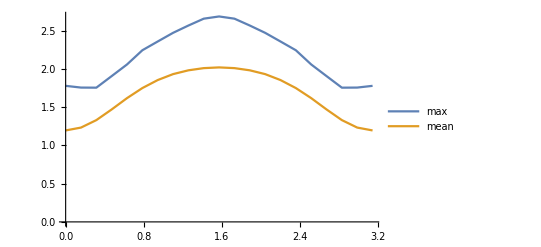

```mathematica
ListLinePlot[{wfibomax,wfibomean},PlotLegends->{"max","mean"}]
```

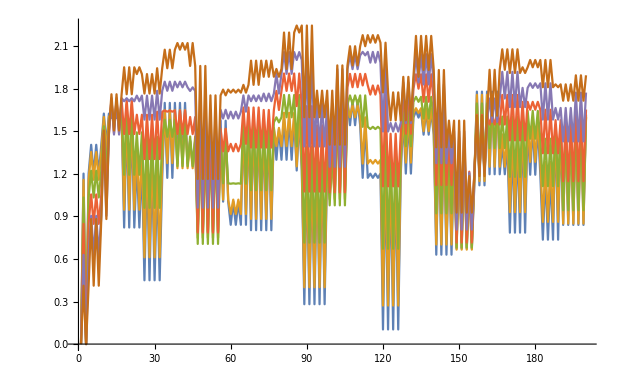

```mathematica
ListLinePlot[Table[wfibon[[n]],{n,1,6}]]
```

## dt = pi/8 kick*after

#### data

```mathematica
wfibdata={-0.000000000000000000*10^+00,1.201752073385713215*10^+00,-1.922055902288951571*10^-15,1.201752073385713659*10^+00,2.000000000000004441*10^+00,1.201752073385710329*10^+00,2.000000000000006217*10^+00,1.201752073385709663*10^+00,1.404764034988924548*10^+00,2.233645517748451770*10^+00,1.404764034988926102*10^+00,1.624883029461670070*10^+00,2.278389197645123598*10^+00,1.624883029461671180*10^+00,2.278389197645124931*10^+00,1.624883029461673178*10^+00,1.593851164854303004*10^+00,2.318686453377661216*10^+00,1.593851164854307445*10^+00,2.318686453377664769*10^+00,1.593851164854311442*10^+00,8.216731072033420791*10^-01,1.749038421972467949*10^+00,8.216731072033385264*10^-01,1.290544393841764226*10^+00,2.089530831627532059*10^+00,1.290544393841766002*10^+00,2.089530831627534280*10^+00,1.290544393841767334*10^+00,4.495892585821109066*10^-01,1.488990341577738130*10^+00,4.495892585821077425*10^-01,1.171533725585264918*10^+00,1.942452612208710905*10^+00,1.171533725585268026*10^+00,1.942452612208713347*10^+00,1.171533725585270913*10^+00,1.700309114777335040*10^+00,2.493355630380266863*10^+00,1.700309114777339481*10^+00,2.493355630380270860*10^+00,1.700309114777341701*10^+00,1.273741385706492535*10^+00,1.937350260308900562*10^+00,1.273741385706492979*10^+00,1.435086477961448725*10^+00,2.245029186645513430*10^+00,1.435086477961450058*10^+00,2.245029186645515207*10^+00,1.435086477961452944*10^+00,7.942844088297776883*10^-01,1.775180077087650909*10^+00,7.942844088297735805*10^-01,1.775180077087650021*10^+00,7.942844088297691396*10^-01,1.574682138150338417*10^+00,2.221290082262274979*10^+00,1.574682138150340860*10^+00,1.004172845183178842*10^+00,1.976616262901572441*10^+00,1.004172845183180618*10^+00,1.976616262901574883*10^+00,1.004172845183181950*10^+00,8.407056156422060278*10^-01,1.708280343770434362*10^+00,8.407056156422078042*10^-01,1.573483708331498754*10^+00,2.346979640273418877*10^+00,1.573483708331501418*10^+00,2.346979640273421541*10^+00,1.573483708331503861*10^+00,8.025282191919544950*10^-01,1.620637524211087754*10^+00,8.025282191919513863*10^-01,1.620637524211088198*10^+00,8.025282191919484998*10^-01,1.516506993800269099*10^+00,2.297089548104695567*10^+00,1.516506993800271985*10^+00,1.299173967532567975*10^+00,2.100628378913883321*10^+00,1.299173967532571083*10^+00,2.100628378913886873*10^+00,1.299173967532572638*10^+00,1.588692277252797602*10^+00,2.238971263931348155*10^+00,1.588692277252800489*10^+00,1.223541710382053838*10^+00,2.185991632120940054*10^+00,1.223541710382055392*10^+00,2.185991632120943606*10^+00,1.223541710382057612*10^+00,2.808572368304213529*10^-01,1.346155323498708700*10^+00,2.808572368304182443*10^-01,1.346155323498711143*10^+00,2.808572368304160238*10^-01,1.273880544614205856*10^+00,2.095491548592069542*10^+00,1.273880544614207411*10^+00,1.067643082990754388*10^+00,1.925586195203589090*10^+00,1.067643082990751502*10^+00,1.925586195203589757*10^+00,1.067643082990748837*10^+00,1.717197516560094783*10^+00,2.379358343560262323*10^+00,1.717197516560097670*10^+00,2.379358343560264988*10^+00,1.717197516560100556*10^+00,1.542862855958129220*10^+00,2.267553881959106121*10^+00,1.542862855958134771*10^+00,1.171833367822162852*10^+00,1.956536146535438947*10^+00,1.171833367822163963*10^+00,1.956536146535442500*10^+00,1.171833367822164185*10^+00,1.201319257815546937*10^+00,2.098340352191563341*10^+00,1.201319257815547603*10^+00,1.029728895711485848*10^-01,1.237412499359116236*10^+00,1.029728895711456982*10^-01,1.237412499359116680*10^+00,1.029728895711424924*10^-01,1.201771017359970495*10^+00,1.999562003659769660*10^+00,1.201771017359973381*10^+00,1.999562003659772325*10^+00,1.201771017359975602*10^+00,1.596379878908969818*10^+00,2.411377138872818016*10^+00,1.596379878908972039*10^+00,1.644026116717743680*10^+00,2.232370562718693829*10^+00,1.644026116717743236*10^+00,2.232370562718696050*10^+00,1.644026116717743013*10^+00,1.476051951883191160*10^+00,2.268698336180749120*10^+00,1.476051951883195823*10^+00,2.268698336180752229*10^+00,1.476051951883198932*10^+00,6.300917220023936061*10^-01,1.644286996698017367*10^+00,6.300917220023914966*10^-01,1.347384800099507007*10^+00,2.076028569547221814*10^+00,1.347384800099508784*10^+00,2.076028569547223146*10^+00,1.347384800099510338*10^+00,6.734784066409580383*10^-01,1.654092990286361253*10^+00,6.734784066409564840*10^-01,1.118983825496085327*10^+00,1.905885876377229060*10^+00,1.118983825496087992*10^+00,1.905885876377231725*10^+00,1.118983825496090878*10^+00,1.779825274544887037*10^+00,2.517742309724745109*10^+00,1.779825274544891478*10^+00,2.517742309724749994*10^+00,1.779825274544895031*10^+00,1.196918368099461283*10^+00,1.857437845966346313*10^+00,1.196918368099460395*10^+00,1.413613574138938400*10^+00,2.250583271291563214*10^+00,1.413613574138941287*10^+00,2.250583271291565435*10^+00,1.413613574138944173*10^+00,7.853968091772852711*10^-01,1.771223962097935534*10^+00,7.853968091772819404*10^-01,1.542048532575378328*10^+00,2.219975167223513068*10^+00,1.542048532575380992*10^+00,2.219975167223515733*10^+00,1.542048532575383657*10^+00,1.193550880858247343*10^+00,2.107923453341593589*10^+00,1.193550880858250007*10^+00,2.107923453341596254*10^+00,1.193550880858251340*10^+00,7.358226898920917636*10^-01,1.679880068112529878*10^+00,7.358226898920909864*10^-01,1.541426793484414581*10^+00,2.294360645750060268*10^+00,1.541426793484417690*10^+00,2.294360645750062044*10^+00,1.541426793484419910*10^+00,8.399863456987917143*10^-01,1.686241078649283631*10^+00,8.399863456987893828*10^-01,1.686241078649284297*10^+00,8.399863456987849419*10^-01,1.617288949663909126*10^+00,2.722912528242654327*10^-14,1.157960598926154550*10^+00,2.594775468090060106*10^-14,1.201752073385715214*10^+00,1.999999999999912514*10^+00,1.201752073385711217*10^+00,1.999999999999914513*10^+00,1.201752073385709441*10^+00,1.404881290126554383*10^+00,2.217273218841611104*10^+00,1.404881290126556159*10^+00,1.618334329357088430*10^+00,2.240807294759564527*10^+00,1.618334329357088430*10^+00,2.240807294759566304*10^+00,1.618334329357089096*10^+00,1.645520976853166006*10^+00,2.331761817342354881*10^+00,1.645520976853171558*10^+00,2.331761817342359322*10^+00,1.645520976853176887*10^+00,9.378152660583684019*10^-01,1.844405106131138838*10^+00,9.378152660583674027*10^-01,1.374841989669169262*10^+00,2.134032730713424364*10^+00,1.374841989669169484*10^+00,2.134032730713425252*10^+00,1.374841989669171927*10^+00,6.350030155206010107*10^-01,1.624441516090942450*10^+00,6.350030155205970139*10^-01,1.273222589904081214*10^+00,2.064499275381215249*10^+00,1.273222589904084767*10^+00,2.064499275381218357*10^+00,1.273222589904088098*10^+00,1.766083073301567774*10^+00,2.523756959855879778*10^+00,1.766083073301571105*10^+00,2.523756959855883331*10^+00,1.766083073301575546*10^+00,1.322262145390636245*10^+00,1.961133084385587866*10^+00,1.322262145390635357*10^+00,1.435231864097198606*10^+00,2.216816192899175864*10^+00,1.435231864097198162*10^+00,2.216816192899177640*10^+00,1.435231864097200827*10^+00,7.791932221332774633*10^-01,1.724586324622844113*10^+00,7.791932221332730224*10^-01,1.724586324622843669*10^+00,7.791932221332690256*10^-01,1.568554283331614840*10^+00,2.214954313243020056*10^+00,1.568554283331618171*10^+00,1.081069009270353876*10^+00,1.998005610737349391*10^+00,1.081069009270356096*10^+00,1.998005610737352278*10^+00,1.081069009270358983*10^+00,8.921539728222175336*10^-01,1.739481543470876801*10^+00,8.921539728222207533*10^-01,1.631949169494217866*10^+00,2.355204280709664033*10^+00,1.631949169494220975*10^+00,2.355204280709665809*10^+00,1.631949169494224305*10^+00,9.429264282671108166*10^-01,1.714535690965175441*10^+00,9.429264282671081521*10^-01,1.714535690965176551*10^+00,9.429264282671059316*10^-01,1.564812932264126211*10^+00,2.331448417873486889*10^+00,1.564812932264129763*10^+00,1.340613573160178706*10^+00,2.115861346178624647*10^+00,1.340613573160179595*10^+00,2.115861346178627311*10^+00,1.340613573160181149*10^+00,1.583544774771686425*10^+00,2.233796239028720265*10^+00,1.583544774771688202*10^+00,1.314806472533986748*10^+00,2.202928098004431234*10^+00,1.314806472533990078*10^+00,2.202928098004434343*10^+00,1.314806472533991411*10^+00,4.117174519277653211*10^-01,1.452656985138201184*10^+00,4.117174519277653211*10^-01,1.452656985138203183*10^+00,4.117174519277648770*10^-01,1.303975017075308607*10^+00,2.068792516468247022*10^+00,1.303975017075310383*10^+00,1.055339837172389439*10^+00,1.879970805323696759*10^+00,1.055339837172388107*10^+00,1.879970805323697203*10^+00,1.055339837172386552*10^+00,1.726592662816338386*10^+00,2.366460712818523771*10^+00,1.726592662816341051*10^+00,2.366460712818526435*10^+00,1.726592662816343049*10^+00,1.505706891696985128*10^+00,2.253789852665255999*10^+00,1.505706891696990013*10^+00,1.145887754229412359*10^+00,1.930195222197571780*10^+00,1.145887754229412581*10^+00,1.930195222197573557*10^+00,1.145887754229413691*10^+00,1.283246309975135890*10^+00,2.109779479227276155*10^+00,1.283246309975137667*10^+00,3.020860573936913207*10^-01,1.361979461044603212*10^+00,3.020860573936882676*10^-01,1.361979461044603656*10^+00,3.020860573936842153*10^-01,1.272286018993571854*10^+00,2.059218118778490592*10^+00,1.272286018993575407*10^+00,2.059218118778492812*10^+00,1.272286018993578294*10^+00,1.617373380023978680*10^+00,2.418109799031281426*10^+00,1.617373380023980234*10^+00,1.633114162225013599*10^+00,2.187779094139875813*10^+00,1.633114162225015598*10^+00,2.187779094139878477*10^+00,1.633114162225016708*10^+00,1.453014157919721328*10^+00,2.260902716849185534*10^+00,1.453014157919726212*10^+00,2.260902716849189531*10^+00,1.453014157919730209*10^+00,6.193692571156635962*10^-01,1.632041601205261205*10^+00,6.193692571156594884*10^-01,1.291664719389503446*10^+00,1.992397144731886005*10^+00,1.291664719389504778*10^+00,1.992397144731887337*10^+00,1.291664719389506555*10^+00,6.654893184029558872*10^-01,1.606679353885980932*10^+00,6.654893184029568864*10^-01,1.162134853714831495*10^+00,1.970409981297535973*10^+00,1.162134853714834160*10^+00,1.970409981297539304*10^+00,1.162134853714837046*10^+00,1.724195957455930683*10^+00,2.480144157523249682*10^+00,1.724195957455934680*10^+00,2.480144157523254567*10^+00,1.724195957455938455*10^+00,1.190130867892462252*10^+00,1.842712390807048184*10^+00,1.190130867892459809*10^+00,1.468673996275792426*10^+00,2.265717004296069259*10^+00,1.468673996275792648*10^+00,2.265717004296071480*10^+00,1.468673996275795979*10^+00,9.144976172709005091*10^-01,1.844597585519076155*10^+00,9.144976172708981776*10^-01,1.557600479284567019*10^+00,2.236745695847987658*10^+00,1.557600479284569239*10^+00,2.236745695847990323*10^+00,1.557600479284572792*10^+00,1.290641357731723282*10^+00,2.138705159798800715*10^+00,1.290641357731723504*10^+00,2.138705159798803379*10^+00,1.290641357731725947*10^+00,8.711784562108964014*10^-01,1.773931674100758249*10^+00,8.711784562108968455*10^-01,1.580157672907805289*10^+00,2.318884846144441791*10^+00,1.580157672907807287*10^+00,2.318884846144443568*10^+00,1.580157672907811284*10^+00,8.869946023406155566*10^-01,1.714442684366148439*10^+00,8.869946023406107827*10^-01,1.714442684366149994*10^+00,8.869946023406073410*10^-01,1.614821617012775601*10^+00,-9.610279511444755881*10^-16,1.033390542523312527*10^+00,4.805139755722374982*10^-16,1.201752073385713881*10^+00,2.000000000000003553*10^+00,1.201752073385710773*10^+00,2.000000000000005773*10^+00,1.201752073385710107*10^+00,1.406549003615071181*10^+00,2.171656847108323074*10^+00,1.406549003615072069*10^+00,1.607378642142081260*10^+00,2.144042017716828230*10^+00,1.607378642142080594*10^+00,2.144042017716830451*10^+00,1.607378642142081482*10^+00,1.764401103105457169*10^+00,2.376043501783324796*10^+00,1.764401103105463386*10^+00,2.376043501783329237*10^+00,1.764401103105467827*10^+00,1.153545603088919069*10^+00,2.016956638704877403*10^+00,1.153545603088918403*10^+00,1.473534182783539759*10^+00,2.211272218508040233*10^+00,1.473534182783542423*10^+00,2.211272218508042897*10^+00,1.473534182783546864*10^+00,1.013775559648700586*10^+00,1.875833994140055472*10^+00,1.013775559648699032*10^+00,1.516307800591846444*10^+00,2.257523825774125026*10^+00,1.516307800591850663*10^+00,2.257523825774128134*10^+00,1.516307800591853994*10^+00,1.908739026000679573*10^+00,2.597780872935014695*10^+00,1.908739026000682459*10^+00,2.597780872935019136*10^+00,1.908739026000685346*10^+00,1.415712099628197551*10^+00,1.996927081881736621*10^+00,1.415712099628198439*10^+00,1.459416556188320335*10^+00,2.150221013976715945*10^+00,1.459416556188322556*10^+00,2.150221013976717277*10^+00,1.459416556188323888*10^+00,7.909368414544520887*10^-01,1.640605411643811351*10^+00,7.909368414544486470*10^-01,1.640605411643810685*10^+00,7.909368414544450943*10^-01,1.577791488532282127*10^+00,2.227038406208786014*10^+00,1.577791488532284792*10^+00,1.245519046759130166*10^+00,2.025698600497597646*10^+00,1.245519046759131498*10^+00,2.025698600497600310*10^+00,1.245519046759133275*10^+00,1.100783816395684234*10^+00,1.868440931075096678*10^+00,1.100783816395686676*10^+00,1.761192212067350660*10^+00,2.397193321684819800*10^+00,1.761192212067354212*10^+00,2.397193321684823353*10^+00,1.761192212067356877*10^+00,1.220664723057163670*10^+00,1.891881991868521240*10^+00,1.220664723057161893*10^+00,1.891881991868522128*10^+00,1.220664723057158785*10^+00,1.672896941124421888*10^+00,2.394268759092400778*10^+00,1.672896941124425663*10^+00,1.503188479069263339*10^+00,2.209585878782966528*10^+00,1.503188479069265782*10^+00,2.209585878782968749*10^+00,1.503188479069267336*10^+00,1.635964816635302688*10^+00,2.274605705537447342*10^+00,1.635964816635306018*10^+00,1.518314247390168514*10^+00,2.244216381678097338*10^+00,1.518314247390168958*10^+00,2.244216381678100447*10^+00,1.518314247390171623*10^+00,7.388856856297271181*10^-01,1.659981754970222267*10^+00,7.388856856297268960*10^-01,1.659981754970222489*10^+00,7.388856856297261189*10^-01,1.389166861556717425*10^+00,2.097303170624255308*10^+00,1.389166861556718979*10^+00,1.092408387649761670*10^+00,1.817222739886969141*10^+00,1.092408387649760559*10^+00,1.817222739886969363*10^+00,1.092408387649760115*10^+00,1.781476214270113267*10^+00,2.343818711648040232*10^+00,1.781476214270115266*10^+00,2.343818711648042008*10^+00,1.781476214270117708*10^+00,1.530747594116974586*10^+00,2.260622047846052141*10^+00,1.530747594116979027*10^+00,1.173762902156167742*10^+00,1.940959143228614181*10^+00,1.173762902156166854*10^+00,1.940959143228615957*10^+00,1.173762902156167298*10^+00,1.434035539047912700*10^+00,2.179154101546209699*10^+00,1.434035539047914476*10^+00,7.247696878838355561*10^-01,1.604231521239571245*10^+00,7.247696878838342238*10^-01,1.604231521239571467*10^+00,7.247696878838337797*10^-01,1.383941019401139449*10^+00,2.199999646141697962*10^+00,1.383941019401143002*10^+00,2.199999646141700627*10^+00,1.383941019401146555*10^+00,1.701796363668428569*10^+00,2.426998187191866219*10^+00,1.701796363668432122*10^+00,1.616545110713411226*10^+00,2.097326468176001768*10^+00,1.616545110713411892*10^+00,2.097326468176004433*10^+00,1.616545110713412559*10^+00,1.437753885165428347*10^+00,2.230022545978610271*10^+00,1.437753885165432344*10^+00,2.230022545978612936*10^+00,1.437753885165436785*10^+00,6.546482880551420802*10^-01,1.658259127857825144*10^+00,6.546482880551381944*10^-01,1.197797829854353235*10^+00,1.831950481730532099*10^+00,1.197797829854354568*10^+00,1.831950481730533209*10^+00,1.197797829854355234*10^+00,6.790610274837574067*10^-01,1.476987116396780042*10^+00,6.790610274837582949*10^-01,1.270690090373628234*10^+00,2.053238372708697579*10^+00,1.270690090373629344*10^+00,2.053238372708701576*10^+00,1.270690090373633563*10^+00,1.679567514421459906*10^+00,2.420338344439375788*10^+00,1.679567514421465013*10^+00,2.420338344439380229*10^+00,1.679567514421469676*10^+00,1.225137465121139080*10^+00,1.844298737210629646*10^+00,1.225137465121139080*10^+00,1.597311480105645831*10^+00,2.307147436132237939*10^+00,1.597311480105647608*10^+00,2.307147436132238827*10^+00,1.597311480105648274*10^+00,1.119979231615257476*10^+00,1.986721547207998206*10^+00,1.119979231615255477*10^+00,1.573870631139046461*10^+00,2.287403428002933836*10^+00,1.573870631139048681*10^+00,2.287403428002938277*10^+00,1.573870631139050680*10^+00,1.448822683983103321*10^+00,2.196423497027406135*10^+00,1.448822683983102877*10^+00,2.196423497027408356*10^+00,1.448822683983104875*10^+00,1.128529151819778420*10^+00,1.900260831668173722*10^+00,1.128529151819781307*10^+00,1.648860726699491241*10^+00,2.379297492491747157*10^+00,1.648860726699494350*10^+00,2.379297492491748489*10^+00,1.648860726699497903*10^+00,1.009829657420438398*10^+00,1.781557486279670588*10^+00,1.009829657420435955*10^+00,1.781557486279671698*10^+00,1.009829657420432847*10^+00,1.589623792948608338*10^+00,9.610279511444749964*10^-16,8.474263344968486766*10^-01,-6.086510357248356435*10^-15,1.201752073385712993*10^+00,2.000000000000005773*10^+00,1.201752073385709885*10^+00,2.000000000000007550*10^+00,1.201752073385708997*10^+00,1.413071973816220517*10^+00,2.117344506457182085*10^+00,1.413071973816222071*10^+00,1.624417752822832961*10^+00,2.029545287444448398*10^+00,1.624417752822834071*10^+00,2.029545287444450619*10^+00,1.624417752822834515*10^+00,1.900682337109399045*10^+00,2.460683167584329922*10^+00,1.900682337109403486*10^+00,2.460683167584333475*10^+00,1.900682337109407261*10^+00,1.410136432185750355*10^+00,2.182888377335068242*10^+00,1.410136432185750355*10^+00,1.564338917123462513*10^+00,2.229242440389812785*10^+00,1.564338917123464956*10^+00,2.229242440389815449*10^+00,1.564338917123467843*10^+00,1.378500964482408220*10^+00,2.096694725427810546*10^+00,1.378500964482406221*10^+00,1.761019844372832432*10^+00,2.442721650975133940*10^+00,1.761019844372836429*10^+00,2.442721650975138381*10^+00,1.761019844372839760*10^+00,2.061217223971957946*10^+00,2.676800310440683006*10^+00,2.061217223971962387*10^+00,2.676800310440686559*10^+00,2.061217223971965939*10^+00,1.495214233195174547*10^+00,2.013485385930565474*10^+00,1.495214233195174547*10^+00,1.526270358307610708*10^+00,2.069264138065439962*10^+00,1.526270358307612263*10^+00,2.069264138065441294*10^+00,1.526270358307613817*10^+00,8.992519798086066052*10^-01,1.631699097735066717*10^+00,8.992519798086022753*10^-01,1.631699097735066051*10^+00,8.992519798085997218*10^-01,1.634351859515356553*10^+00,2.303294576265823679*10^+00,1.634351859515357663*10^+00,1.427904168671201290*10^+00,1.991588421075155546*10^+00,1.427904168671203067*10^+00,1.991588421075157322*10^+00,1.427904168671205287*10^+00,1.416960461607333244*10^+00,2.054508249975016021*10^+00,1.416960461607334576*10^+00,1.930236333058134024*10^+00,2.487374966065193149*10^+00,1.930236333058138243*10^+00,2.487374966065195814*10^+00,1.930236333058141129*10^+00,1.490696674157714563*10^+00,2.054291433623558039*10^+00,1.490696674157714119*10^+00,2.054291433623559371*10^+00,1.490696674157714785*10^+00,1.793257193890152479*10^+00,2.390119883359180797*10^+00,1.793257193890155143*10^+00,1.769413861870235305*10^+00,2.392257464723991589*10^+00,1.769413861870237303*10^+00,2.392257464723994254*10^+00,1.769413861870239746*10^+00,1.781186723300815844*10^+00,2.404279423995084652*10^+00,1.781186723300819619*10^+00,1.760727734354671448*10^+00,2.284069825139483534*10^+00,1.760727734354674556*10^+00,2.284069825139486642*10^+00,1.760727734354676111*10^+00,1.103026082008555342*10^+00,1.873462442344169476*10^+00,1.103026082008554454*10^+00,1.873462442344171475*10^+00,1.103026082008554454*10^+00,1.585527411422289035*10^+00,2.224650626218036553*10^+00,1.585527411422290811*10^+00,1.243935964085123302*10^+00,1.854542243682438807*10^+00,1.243935964085122858*10^+00,1.854542243682439473*10^+00,1.243935964085121304*10^+00,1.910707503110226968*10^+00,2.355413639485340216*10^+00,1.910707503110228966*10^+00,2.355413639485342436*10^+00,1.910707503110231409*10^+00,1.696914750106951031*10^+00,2.318931707098618400*10^+00,1.696914750106955694*10^+00,1.412661839622360915*10^+00,2.137338323591881917*10^+00,1.412661839622360915*10^+00,2.137338323591883249*10^+00,1.412661839622362470*10^+00,1.564310431553074032*10^+00,2.232403016019747888*10^+00,1.564310431553075365*10^+00,1.116441430125890477*10^+00,1.734301204487800563*10^+00,1.116441430125888701*10^+00,1.734301204487802117*10^+00,1.116441430125888701*10^+00,1.541098077805090227*10^+00,2.315344494218462668*10^+00,1.541098077805093114*10^+00,2.315344494218466220*10^+00,1.541098077805096223*10^+00,1.832025338860013175*10^+00,2.458771940828013314*10^+00,1.832025338860013619*10^+00,1.623717787954820135*10^+00,1.982013107600231860*10^+00,1.623717787954821024*10^+00,1.982013107600235413*10^+00,1.623717787954822800*10^+00,1.511288274263982379*10^+00,2.186016717551750865*10^+00,1.511288274263984599*10^+00,2.186016717551754418*10^+00,1.511288274263986819*10^+00,8.087403316988304169*10^-01,1.770348405388831647*10^+00,8.087403316988275304*10^-01,1.153261591888162130*10^+00,1.719563831258142939*10^+00,1.153261591888162796*10^+00,1.719563831258144493*10^+00,1.153261591888163906*10^+00,7.131733601250084265*10^-01,1.301116356738324376*10^+00,7.131733601250086485*10^-01,1.423383031867065940*10^+00,2.141505376349492451*10^+00,1.423383031867067938*10^+00,2.141505376349495560*10^+00,1.423383031867068604*10^+00,1.741018083716593390*10^+00,2.446048192768842000*10^+00,1.741018083716596276*10^+00,2.446048192768848217*10^+00,1.741018083716598275*10^+00,1.374709125413922983*10^+00,1.927244836060593602*10^+00,1.374709125413922095*10^+00,1.759259205085608846*10^+00,2.349384130675307603*10^+00,1.759259205085610178*10^+00,2.349384130675308935*10^+00,1.759259205085610844*10^+00,1.390371060142240545*10^+00,2.102692141340716248*10^+00,1.390371060142237880*10^+00,1.605529437033979212*10^+00,2.336149379982556784*10^+00,1.605529437033980988*10^+00,2.336149379982560781*10^+00,1.605529437033982099*10^+00,1.584758604626071543*10^+00,2.213537175790507128*10^+00,1.584758604626070433*10^+00,2.213537175790510236*10^+00,1.584758604626071321*10^+00,1.349396355407773695*10^+00,1.980937345973403652*10^+00,1.349396355407775694*10^+00,1.733383157276395803*10^+00,2.451709947163672076*10^+00,1.733383157276397579*10^+00,2.451709947163674297*10^+00,1.733383157276400466*10^+00,1.113950415546977268*10^+00,1.847880679541561877*10^+00,1.113950415546974604*10^+00,1.847880679541562765*10^+00,1.113950415546972161*10^+00,1.528444614390271683*10^+00,4.805139755722374982*10^-16,6.289791881778438176*10^-01,9.610279511444749964*10^-16,1.201752073385714326*10^+00,2.000000000000002665*10^+00,1.201752073385710773*10^+00,2.000000000000004441*10^+00,1.201752073385710329*10^+00,1.428059645285718160*10^+00,2.048374937697136300*10^+00,1.428059645285718826*10^+00,1.666480003267419407*10^+00,1.936669214298420982*10^+00,1.666480003267421184*10^+00,1.936669214298423203*10^+00,1.666480003267421184*10^+00,2.052740825892118703*10^+00,2.575678823581577070*10^+00,2.052740825892121812*10^+00,2.575678823581580623*10^+00,2.052740825892125365*10^+00,1.643080743007849120*10^+00,2.329562480692122239*10^+00,1.643080743007847566*10^+00,1.661812934626159199*10^+00,2.224860856919451901*10^+00,1.661812934626161642*10^+00,2.224860856919453678*10^+00,1.661812934626164306*10^+00,1.669578063197820761*10^+00,2.236214893465047648*10^+00,1.669578063197819429*10^+00,2.011341502612078891*10^+00,2.596435293352727491*10^+00,2.011341502612081111*10^+00,2.596435293352731488*10^+00,2.011341502612084664*10^+00,2.225174366208895638*10^+00,2.714323652577605550*10^+00,2.225174366208897414*10^+00,2.714323652577609103*10^+00,2.225174366208900523*10^+00,1.568629442330339296*10^+00,2.038177140251275610*10^+00,1.568629442330338630*10^+00,1.598180771851150928*10^+00,1.976455092461274043*10^+00,1.598180771851152038*10^+00,1.976455092461275820*10^+00,1.598180771851153148*10^+00,1.099215509153185000*10^+00,1.680082127236138145*10^+00,1.099215509153183001*10^+00,1.680082127236138367*10^+00,1.099215509153180337*10^+00,1.743392302981368269*10^+00,2.449594284653719534*10^+00,1.743392302981369379*10^+00,1.559490479226775417*10^+00,1.893460839953331032*10^+00,1.559490479226777415*10^+00,1.893460839953332586*10^+00,1.559490479226778525*10^+00,1.719729840347237859*10^+00,2.217589099897411486*10^+00,1.719729840347239858*10^+00,2.087054693594601940*10^+00,2.623960573916727324*10^+00,2.087054693594605048*10^+00,2.623960573916729988*10^+00,2.087054693594607713*10^+00,1.677325289876739678*10^+00,2.137442733207359336*10^+00,1.677325289876738346*10^+00,2.137442733207359780*10^+00,1.677325289876737457*10^+00,1.895601850088362017*10^+00,2.303402682238722576*10^+00,1.895601850088364015*10^+00,2.041702731046826980*10^+00,2.580181317070768809*10^+00,2.041702731046829644*10^+00,2.580181317070770142*10^+00,2.041702731046832309*10^+00,1.947540874315141890*10^+00,2.571789225646474719*10^+00,1.947540874315144332*10^+00,1.928669697051803800*10^+00,2.251791733934028983*10^+00,1.928669697051806464*10^+00,2.251791733934030759*10^+00,1.928669697051807796*10^+00,1.414979072549146011*10^+00,2.028570467872238048*10^+00,1.414979072549146677*10^+00,2.028570467872239824*10^+00,1.414979072549147121*10^+00,1.769621291439797961*10^+00,2.334886221687929808*10^+00,1.769621291439798627*10^+00,1.431671625038407836*10^+00,1.941426713874133902*10^+00,1.431671625038407614*10^+00,1.941426713874134347*10^+00,1.431671625038406503*10^+00,2.048877545280598067*10^+00,2.396356471811920574*10^+00,2.048877545280599843*10^+00,2.396356471811922795*10^+00,2.048877545280602064*10^+00,1.905898861908916331*10^+00,2.364660758464964374*10^+00,1.905898861908919439*10^+00,1.721753365578136741*10^+00,2.357681884575008269*10^+00,1.721753365578138073*10^+00,2.357681884575010933*10^+00,1.721753365578139183*10^+00,1.695784766866610838*10^+00,2.323088051196129378*10^+00,1.695784766866611060*10^+00,1.366068422744514343*10^+00,1.733468928395907049*10^+00,1.366068422744513455*10^+00,1.733468928395909492*10^+00,1.366068422744513233*10^+00,1.717025473761189858*10^+00,2.408874064624134892*10^+00,1.717025473761192966*10^+00,2.408874064624138001*10^+00,1.717025473761196075*10^+00,2.013387006629461684*10^+00,2.581552290606164757*10^+00,2.013387006629463460*10^+00,1.655839518788641662*10^+00,1.881117484230596881*10^+00,1.655839518788643661*10^+00,1.881117484230599324*10^+00,1.655839518788644771*10^+00,1.624803528184849633*10^+00,2.090309114927147771*10^+00,1.624803528184850521*10^+00,2.090309114927151324*10^+00,1.624803528184852963*10^+00,1.034677182158263431*10^+00,1.934888039409201399*10^+00,1.034677182158259212*10^+00,1.144432860523158846*10^+00,1.708468858018938219*10^+00,1.144432860523159956*10^+00,1.708468858018938885*10^+00,1.144432860523159734*10^+00,7.825347422979141987*10^-01,1.161729989193382995*10^+00,7.825347422979151979*10^-01,1.597216252275104997*10^+00,2.256703567918548092*10^+00,1.597216252275105219*10^+00,2.256703567918549869*10^+00,1.597216252275106552*10^+00,1.893798950468386089*10^+00,2.504499892727713117*10^+00,1.893798950468389197*10^+00,2.504499892727717558*10^+00,1.893798950468391640*10^+00,1.596659373066399823*10^+00,2.090090237311547305*10^+00,1.596659373066400711*10^+00,1.924416303023618768*10^+00,2.396849694059039138*10^+00,1.924416303023619879*10^+00,2.396849694059040026*10^+00,1.924416303023621433*10^+00,1.655904321596708861*10^+00,2.188965876835538449*10^+00,1.655904321596707529*10^+00,1.708571235956205747*10^+00,2.433058158848932173*10^+00,1.708571235956208634*10^+00,2.433058158848934838*10^+00,1.708571235956210632*10^+00,1.713554260732940371*10^+00,2.245695012940211566*10^+00,1.713554260732939927*10^+00,2.245695012940213342*10^+00,1.713554260732941037*10^+00,1.555775689254564442*10^+00,2.003508595836314576*10^+00,1.555775689254565108*10^+00,1.850500648984809482*10^+00,2.514426886327285171*10^+00,1.850500648984811258*10^+00,2.514426886327287836*10^+00,1.850500648984813479*10^+00,1.215316286182638095*10^+00,1.893606080803897473*10^+00,1.215316286182636096*10^+00,1.893606080803899250*10^+00,1.215316286182635208*10^+00,1.426987733093468602*10^+00,3.203426503814917641*10^-16,4.115261085513831629*10^-01,2.722912528242677283*10^-15,1.201752073385713881*10^+00,2.000000000000002220*10^+00,1.201752073385711217*10^+00,2.000000000000003997*10^+00,1.201752073385710329*10^+00,1.453383295463393843*10^+00,1.986421649466675099*10^+00,1.453383295463394287*10^+00,1.748614537443927919*10^+00,1.916475494221602016*10^+00,1.748614537443929029*10^+00,1.916475494221603793*10^+00,1.748614537443929695*10^+00,2.221389124509347557*10^+00,2.698530892929134950*10^+00,2.221389124509349777*10^+00,2.698530892929137615*10^+00,2.221389124509351998*10^+00,1.837127007711984561*10^+00,2.416697868959981843*10^+00,1.837127007711983673*10^+00,1.757349002284556594*10^+00,2.239489442481742643*10^+00,1.757349002284558814*10^+00,2.239489442481744863*10^+00,1.757349002284561257*10^+00,1.901827820795305435*10^+00,2.349940150490229307*10^+00,1.901827820795304769*10^+00,2.220488014376547969*10^+00,2.714132242322057742*10^+00,2.220488014376549302*10^+00,2.714132242322060851*10^+00,2.220488014376552410*10^+00,2.362144652008642431*10^+00,2.680525310162727326*10^+00,2.362144652008644208*10^+00,2.680525310162729102*10^+00,2.362144652008646872*10^+00,1.707074637235559411*10^+00,2.132615857538296300*10^+00,1.707074637235557635*10^+00,1.633272119240439135*10^+00,1.899406002537094906*10^+00,1.633272119240439579*10^+00,1.899406002537094906*10^+00,1.633272119240441356*10^+00,1.303415355141543275*10^+00,1.694543870415825548*10^+00,1.303415355141542609*10^+00,1.694543870415826436*10^+00,1.303415355141542609*10^+00,1.865659873289988058*10^+00,2.646913703179912591*10^+00,1.865659873289988946*10^+00,1.647009139095108043*10^+00,1.797889300330266726*10^+00,1.647009139095109820*10^+00,1.797889300330268503*10^+00,1.647009139095109820*10^+00,1.937100605888939286*10^+00,2.293883696691312757*10^+00,1.937100605888939953*10^+00,2.212262353807593396*10^+00,2.778547328696836072*10^+00,2.212262353807595616*10^+00,2.778547328696837848*10^+00,2.212262353807597393*10^+00,1.779054418474142141*10^+00,2.186320192654828798*10^+00,1.779054418474141919*10^+00,2.186320192654829686*10^+00,1.779054418474141253*10^+00,1.975332836371034073*10^+00,2.175140873905850647*10^+00,1.975332836371037182*10^+00,2.258768822480599514*10^+00,2.716581926451024032*10^+00,2.258768822480600846*10^+00,2.716581926451026696*10^+00,2.258768822480603955*10^+00,2.068561316085276047*10^+00,2.709067882727205667*10^+00,2.068561316085278268*10^+00,1.973652782834261155*10^+00,2.135798328451072869*10^+00,1.973652782834263375*10^+00,2.135798328451075090*10^+00,1.973652782834265818*10^+00,1.595742703411402452*10^+00,2.099210064679711163*10^+00,1.595742703411404451*10^+00,2.099210064679712495*10^+00,1.595742703411404007*10^+00,1.815916958003274573*10^+00,2.356182438550776137*10^+00,1.815916958003276349*10^+00,1.564403111805729552*10^+00,1.933852050113136656*10^+00,1.564403111805730662*10^+00,1.933852050113137988*10^+00,1.564403111805730884*10^+00,2.149951781878612245*10^+00,2.473823930505887336*10^+00,2.149951781878612689*10^+00,2.473823930505889557*10^+00,2.149951781878613577*10^+00,2.049937436268855606*10^+00,2.341320059587901348*10^+00,2.049937436268859159*10^+00,1.977520888005549260*10^+00,2.476090525680414878*10^+00,1.977520888005551924*10^+00,2.476090525680416654*10^+00,1.977520888005551702*10^+00,1.811639293690827213*10^+00,2.465682796280112665*10^+00,1.811639293690828545*10^+00,1.485210957737070236*10^+00,1.663258243030055539*10^+00,1.485210957737069792*10^+00,1.663258243030057537*10^+00,1.485210957737070903*10^+00,1.871428718850752349*10^+00,2.444687507280246308*10^+00,1.871428718850754791*10^+00,2.444687507280249417*10^+00,1.871428718850757900*10^+00,2.193807633008190372*10^+00,2.720244530024860996*10^+00,2.193807633008191260*10^+00,1.723157989827720948*10^+00,1.869378485403604184*10^+00,1.723157989827722059*10^+00,1.869378485403605739*10^+00,1.723157989827723391*10^+00,1.723211471951415552*10^+00,1.975683684674202745*10^+00,1.723211471951416884*10^+00,1.975683684674204077*10^+00,1.723211471951418883*10^+00,1.268384121006608023*10^+00,2.069663660433330055*10^+00,1.268384121006606025*10^+00,1.149625635683891423*10^+00,1.774001059928657087*10^+00,1.149625635683892311*10^+00,1.774001059928658197*10^+00,1.149625635683892533*10^+00,8.819469278461081752*10^-01,1.065008637034897232*10^+00,8.819469278461108397*10^-01,1.780475501044975983*10^+00,2.386419838173350794*10^+00,1.780475501044976872*10^+00,2.386419838173352570*10^+00,1.780475501044978426*10^+00,2.063672090079438970*10^+00,2.549411480967499255*10^+00,2.063672090079440302*10^+00,2.549411480967501475*10^+00,2.063672090079442079*10^+00,1.842594668890293441*10^+00,2.250807562740502643*10^+00,1.842594668890293885*10^+00,2.112180570620253661*10^+00,2.483409444527203469*10^+00,2.112180570620254549*10^+00,2.483409444527202581*10^+00,2.112180570620254549*10^+00,1.882260052674677331*10^+00,2.234996358911632619*10^+00,1.882260052674676443*10^+00,1.858443218115851892*10^+00,2.553387308185705251*10^+00,1.858443218115853668*10^+00,2.553387308185707916*10^+00,1.858443218115855444*10^+00,1.871824108913525242*10^+00,2.353450500519115973*10^+00,1.871824108913523910*10^+00,2.353450500519117750*10^+00,1.871824108913524798*10^+00,1.745984027575242958*10^+00,2.042070603203510082*10^+00,1.745984027575244957*10^+00,2.002096612801119058*10^+00,2.551106947812048276*10^+00,2.002096612801120834*10^+00,2.551106947812050496*10^+00,2.002096612801121278*10^+00,1.379254429178752739*10^+00,1.968111267543072751*10^+00,1.379254429178751185*10^+00,1.968111267543073861*10^+00,1.379254429178751851*10^+00,1.347036267037984292*10^+00,-9.610279511444755881*10^-16,2.237564860125470512*10^-01,1.441541926716712396*10^-15,1.201752073385713437*10^+00,2.000000000000002665*10^+00,1.201752073385710995*10^+00,2.000000000000004441*10^+00,1.201752073385710107*10^+00,1.487677940272440269*10^+00,1.940331161890363143*10^+00,1.487677940272442045*10^+00,1.861035877711271436*10^+00,1.978944081452327586*10^+00,1.861035877711272768*10^+00,1.978944081452328252*10^+00,1.861035877711272324*10^+00,2.393291438267874049*10^+00,2.803383891238553360*10^+00,2.393291438267877158*10^+00,2.803383891238556025*10^+00,2.393291438267878934*10^+00,1.988070457439239380*10^+00,2.475525042698715428*10^+00,1.988070457439238936*10^+00,1.862412899360303964*10^+00,2.303440148546776367*10^+00,1.862412899360306628*10^+00,2.303440148546779476*10^+00,1.862412899360307961*10^+00,2.088449030630394443*10^+00,2.475987551161883182*10^+00,2.088449030630393999*10^+00,2.389401774213649965*10^+00,2.801178590615885700*10^+00,2.389401774213651741*10^+00,2.801178590615888364*10^+00,2.389401774213654406*10^+00,2.460494815986067341*10^+00,2.600287636358308063*10^+00,2.460494815986067785*10^+00,2.600287636358310728*10^+00,2.460494815986069561*10^+00,1.884084955142635298*10^+00,2.254258645627076785*10^+00,1.884084955142635742*10^+00,1.641198049710930640*10^+00,1.921448169832240982*10^+00,1.641198049710931528*10^+00,1.921448169832241426*10^+00,1.641198049710932638*10^+00,1.458154003057571924*10^+00,1.662034523536852770*10^+00,1.458154003057572812*10^+00,1.662034523536852770*10^+00,1.458154003057571702*10^+00,1.985659666083075647*10^+00,2.845356068948687867*10^+00,1.985659666083077646*10^+00,1.721321959119736178*10^+00,1.801136199078626987*10^+00,1.721321959119736844*10^+00,1.801136199078627875*10^+00,1.721321959119737954*10^+00,2.066937625539980949*10^+00,2.290317215827578412*10^+00,2.066937625539980061*10^+00,2.323854604119993006*10^+00,2.895267018576252127*10^+00,2.323854604119993450*10^+00,2.895267018576253459*10^+00,2.323854604119995226*10^+00,1.873128442655044523*10^+00,2.221169202385983255*10^+00,1.873128442655042303*10^+00,2.221169202385984143*10^+00,1.873128442655040971*10^+00,2.061460814101219174*10^+00,2.117479090007268638*10^+00,2.061460814101221395*10^+00,2.409464132676784942*10^+00,2.790790024062446140*10^+00,2.409464132676784942*10^+00,2.790790024062449692*10^+00,2.409464132676788495*10^+00,2.170981323082466385*10^+00,2.807134955664928100*10^+00,2.170981323082469494*10^+00,1.917824198844824357*10^+00,2.007101089280648232*10^+00,1.917824198844825911*10^+00,2.007101089280649564*10^+00,1.917824198844827244*10^+00,1.676312840098239221*10^+00,2.079377412930718982*10^+00,1.676312840098241219*10^+00,2.079377412930719426*10^+00,1.676312840098241885*10^+00,1.727969082089393149*10^+00,2.318906227261297914*10^+00,1.727969082089393593*10^+00,1.592208872858349666*10^+00,1.807974134137642519*10^+00,1.592208872858350333*10^+00,1.807974134137642963*10^+00,1.592208872858351665*10^+00,2.182806233097812854*10^+00,2.546768267015806053*10^+00,2.182806233097812409*10^+00,2.546768267015807385*10^+00,2.182806233097813742*10^+00,2.125360072046585724*10^+00,2.302196160238128453*10^+00,2.125360072046587945*10^+00,2.143322533762170856*10^+00,2.480208942537794670*10^+00,2.143322533762171300*10^+00,2.480208942537796002*10^+00,2.143322533762172188*10^+00,1.947098766299143247*10^+00,2.619797884820497913*10^+00,1.947098766299142580*10^+00,1.542561879570670147*10^+00,1.650955407312529211*10^+00,1.542561879570670147*10^+00,1.650955407312531875*10^+00,1.542561879570670369*10^+00,2.011916377943350209*10^+00,2.448493594567679565*10^+00,2.011916377943353762*10^+00,2.448493594567683118*10^+00,2.011916377943356871*10^+00,2.351750912456167519*10^+00,2.846285136573216246*10^+00,2.351750912456167519*10^+00,1.840661037255164612*10^+00,1.987337422801852993*10^+00,1.840661037255164612*10^+00,1.987337422801853659*10^+00,1.840661037255166388*10^+00,1.785951153938824421*10^+00,1.913468267404946799*10^+00,1.785951153938825531*10^+00,1.913468267404947909*10^+00,1.785951153938827307*10^+00,1.472802216699947264*10^+00,2.131824322505367686*10^+00,1.472802216699945932*10^+00,1.186001784557944472*10^+00,1.919862330954909435*10^+00,1.186001784557945138*10^+00,1.919862330954911434*10^+00,1.186001784557945360*10^+00,1.010725180636613318*10^+00,1.048532284493459255*10^+00,1.010725180636614651*10^+00,1.952232223696514612*10^+00,2.523172757322161175*10^+00,1.952232223696515945*10^+00,2.523172757322163395*10^+00,1.952232223696516389*10^+00,2.194674399042225943*10^+00,2.557433107845489495*10^+00,2.194674399042227275*10^+00,2.557433107845492160*10^+00,2.194674399042228607*10^+00,2.085672751838379746*10^+00,2.375155702119543299*10^+00,2.085672751838379746*10^+00,2.274349006191535238*10^+00,2.622774673966689285*10^+00,2.274349006191536571*10^+00,2.622774673966690617*10^+00,2.274349006191537903*10^+00,2.046284113602429233*10^+00,2.270832879769541179*10^+00,2.046284113602427901*10^+00,2.033283921081624257*10^+00,2.659749454939445368*10^+00,2.033283921081625589*10^+00,2.659749454939447588*10^+00,2.033283921081627810*10^+00,2.025868734003754223*10^+00,2.503739121632612807*10^+00,2.025868734003753779*10^+00,2.503739121632615472*10^+00,2.025868734003755556*10^+00,1.918450180600029142*10^+00,2.119766561715789255*10^+00,1.918450180600030697*10^+00,2.098738359323106373*10^+00,2.570467127716684175*10^+00,2.098738359323108149*10^+00,2.570467127716685507*10^+00,2.098738359323109037*10^+00,1.574764393274380669*10^+00,2.053457012588235209*10^+00,1.574764393274381558*10^+00,2.053457012588236541*10^+00,1.574764393274381780*10^+00,1.329830947919315776*10^+00,-3.203426503814917641*10^-16,9.553703179852437999*10^-02,3.363597829005659431*10^-15,1.201752073385713881*10^+00,2.000000000000001776*10^+00,1.201752073385711217*10^+00,2.000000000000003109*10^+00,1.201752073385710773*10^+00,1.526103014899141019*10^+00,1.912845086145950502*10^+00,1.526103014899142574*10^+00,1.971399730312926923*10^+00,2.099805201290816381*10^+00,1.971399730312928922*10^+00,2.099805201290816381*10^+00,1.971399730312928700*10^+00,2.521027606955422051*10^+00,2.882704358110249387*10^+00,2.521027606955424716*10^+00,2.882704358110251164*10^+00,2.521027606955426048*10^+00,2.101129875800694435*10^+00,2.523359168099640115*10^+00,2.101129875800693547*10^+00,1.959710304887296584*10^+00,2.407254684500369279*10^+00,1.959710304887296362*10^+00,2.407254684500371056*10^+00,1.959710304887297472*10^+00,2.230622420592331068*10^+00,2.598444318752812787*10^+00,2.230622420592332400*10^+00,2.495817798787717035*10^+00,2.842390166068907487*10^+00,2.495817798787718811*10^+00,2.842390166068908819*10^+00,2.495817798787721919*10^+00,2.521761854475405240*10^+00,2.546753632306453241*10^+00,2.521761854475404796*10^+00,2.546753632306454129*10^+00,2.521761854475405684*10^+00,2.040856484066877030*10^+00,2.339390819780236441*10^+00,2.040856484066876142*10^+00,1.616179870530797702*10^+00,2.062130364597241083*10^+00,1.616179870530799922*10^+00,2.062130364597242416*10^+00,1.616179870530801255*10^+00,1.562176364545055485*10^+00,1.595875118075680055*10^+00,1.562176364545056151*10^+00,1.595875118075681165*10^+00,1.562176364545056373*10^+00,2.095271628664531871*10^+00,3.006834166926592999*10^+00,2.095271628664533203*10^+00,1.798836462444145967*10^+00,1.868140769639116128*10^+00,1.798836462444147077*10^+00,1.868140769639117682*10^+00,1.798836462444147521*10^+00,2.144181971949185694*10^+00,2.281048354646411092*10^+00,2.144181971949184806*10^+00,2.436926660970327063*10^+00,2.987417284757912128*10^+00,2.436926660970326175*10^+00,2.987417284757912572*10^+00,2.436926660970328395*10^+00,1.976271212747604977*10^+00,2.313256321152188377*10^+00,1.976271212747602979*10^+00,2.313256321152189265*10^+00,1.976271212747601425*10^+00,2.131042314940051696*10^+00,2.200932428290845788*10^+00,2.131042314940054361*10^+00,2.481045525795056328*10^+00,2.836396589381262157*10^+00,2.481045525795057216*10^+00,2.836396589381265709*10^+00,2.481045525795059881*10^+00,2.237529661355967647*10^+00,2.834629247689731013*10^+00,2.237529661355969424*10^+00,1.824721221247082248*10^+00,1.938105312420155046*10^+00,1.824721221247081804*10^+00,1.938105312420156157*10^+00,1.824721221247082692*10^+00,1.676895186634408397*10^+00,1.975919822617156152*10^+00,1.676895186634409285*10^+00,1.975919822617156596*10^+00,1.676895186634411283*10^+00,1.576973975179633225*10^+00,2.277523613539196745*10^+00,1.576973975179632781*10^+00,1.531945908905660847*10^+00,1.612236481464705218*10^+00,1.531945908905661735*10^+00,1.612236481464705884*10^+00,1.531945908905663511*10^+00,2.146167833892084431*10^+00,2.579147029162315974*10^+00,2.146167833892083099*10^+00,2.579147029162317306*10^+00,2.146167833892083987*10^+00,2.138358878620417070*10^+00,2.289068559877742270*10^+00,2.138358878620418402*10^+00,2.246181195910298634*10^+00,2.467264347254346291*10^+00,2.246181195910298189*10^+00,2.467264347254346735*10^+00,2.246181195910298189*10^+00,2.077466920978080722*10^+00,2.751087022616131250*10^+00,2.077466920978081166*10^+00,1.592818336924284317*10^+00,1.786240566359803328*10^+00,1.592818336924284317*10^+00,1.786240566359805104*10^+00,1.592818336924285649*10^+00,2.120281053194144061*10^+00,2.456718100559705409*10^+00,2.120281053194147169*10^+00,2.456718100559708517*10^+00,2.120281053194150278*10^+00,2.473071853038387502*10^+00,2.922055278178335769*10^+00,2.473071853038388834*10^+00,2.004437445244597438*10^+00,2.192631729596903334*10^+00,2.004437445244598770*10^+00,2.192631729596904222*10^+00,2.004437445244597882*10^+00,1.828372623966313171*10^+00,1.944522206799600639*10^+00,1.828372623966312061*10^+00,1.944522206799601971*10^+00,1.828372623966313393*10^+00,1.644558315490090683*10^+00,2.116527647481733609*10^+00,1.644558315490091793*10^+00,1.233994612404796243*10^+00,2.119564215125788298*10^+00,1.233994612404797131*10^+00,2.119564215125789630*10^+00,1.233994612404797353*10^+00,1.121647225779142332*10^+00,1.092210132170663650*10^+00,1.121647225779144552*10^+00,2.104567484182645387*10^+00,2.632878887862933670*10^+00,2.104567484182646275*10^+00,2.632878887862935446*10^+00,2.104567484182647608*10^+00,2.275501989596321106*10^+00,2.573822442959713630*10^+00,2.275501989596321550*10^+00,2.573822442959714962*10^+00,2.275501989596323327*10^+00,2.261921494666469190*10^+00,2.438977128657784821*10^+00,2.261921494666470522*10^+00,2.403771613583601585*10^+00,2.757096886561502203*10^+00,2.403771613583603362*10^+00,2.757096886561503535*10^+00,2.403771613583605138*10^+00,2.137783562228982692*10^+00,2.341978085991021974*10^+00,2.137783562228980472*10^+00,2.174630277550897439*10^+00,2.724442637245085841*10^+00,2.174630277550899216*10^+00,2.724442637245088061*10^+00,2.174630277550900992*10^+00,2.142148603934294293*10^+00,2.647249353546483608*10^+00,2.142148603934294737*10^+00,2.647249353546487161*10^+00,2.142148603934295181*10^+00,2.040215678412068634*10^+00,2.194171040071506429*10^+00,2.040215678412069522*10^+00,2.126884856460640627*10^+00,2.559989224055013057*10^+00,2.126884856460641515*10^+00,2.559989224055013501*10^+00,2.126884856460642403*10^+00,1.739092472056319671*10^+00,2.069599381798238102*10^+00,1.739092472056320116*10^+00,2.069599381798240767*10^+00,1.739092472056322336*10^+00,1.358734225233861892*10^+00,-3.203426503814917641*10^-16,2.557510288561427175*10^-02,3.844111804577896041*10^-15,1.201752073385713881*10^+00,2.000000000000001332*10^+00,1.201752073385711439*10^+00,2.000000000000002665*10^+00,1.201752073385710773*10^+00,1.552483386138086452*10^+00,1.900812325766370048*10^+00,1.552483386138088894*10^+00,2.083683543438702657*10^+00,2.230507312013918053*10^+00,2.083683543438702657*10^+00,2.230507312013918053*10^+00,2.083683543438701768*10^+00,2.613652111868169925*10^+00,2.935472471267582151*10^+00,2.613652111868171701*10^+00,2.935472471267583927*10^+00,2.613652111868175254*10^+00,2.181008944482462741*10^+00,2.593422680017068327*10^+00,2.181008944482461409*10^+00,2.025448474767624685*10^+00,2.523301540409493171*10^+00,2.025448474767626017*10^+00,2.523301540409495836*10^+00,2.025448474767626905*10^+00,2.323134623202006033*10^+00,2.702831056047880764*10^+00,2.323134623202006033*10^+00,2.559519720590134995*10^+00,2.854739830763216357*10^+00,2.559519720590137215*10^+00,2.854739830763216801*10^+00,2.559519720590139880*10^+00,2.527447576910613058*10^+00,2.565430649314017764*10^+00,2.527447576910612170*10^+00,2.565430649314017764*10^+00,2.527447576910610838*10^+00,2.161213525762953225*10^+00,2.366225606944202031*10^+00,2.161213525762954113*10^+00,1.582744596671404436*10^+00,2.240644151451495425*10^+00,1.582744596671407100*10^+00,2.240644151451499422*10^+00,1.582744596671407766*10^+00,1.599026998136654276*10^+00,1.531919801546756776*10^+00,1.599026998136654498*10^+00,1.531919801546756776*10^+00,1.599026998136654054*10^+00,2.169098341439959388*10^+00,3.111744588718887705*10^+00,2.169098341439960276*10^+00,1.863373802384926226*10^+00,1.967080390461833472*10^+00,1.863373802384926226*10^+00,1.967080390461834360*10^+00,1.863373802384927336*10^+00,2.197961668486439812*10^+00,2.287742266663416846*10^+00,2.197961668486438036*10^+00,2.520160100935811442*10^+00,3.040179606081366614*10^+00,2.520160100935813663*10^+00,3.040179606081367503*10^+00,2.520160100935814995*10^+00,2.076297764115202504*10^+00,2.438829306152749954*10^+00,2.076297764115199840*10^+00,2.438829306152750398*10^+00,2.076297764115198952*10^+00,2.217192041488496024*10^+00,2.335104646487411895*10^+00,2.217192041488499132*10^+00,2.528252597036449334*10^+00,2.880179353943334686*10^+00,2.528252597036449778*10^+00,2.880179353943338683*10^+00,2.528252597036451554*10^+00,2.283699752049496823*10^+00,2.811420402733152191*10^+00,2.283699752049500376*10^+00,1.747365150378953569*10^+00,1.941497549410792001*10^+00,1.747365150378953569*10^+00,1.941497549410792889*10^+00,1.747365150378954235*10^+00,1.654991759534438556*10^+00,1.822951288951833337*10^+00,1.654991759534440110*10^+00,1.822951288951834448*10^+00,1.654991759534441886*10^+00,1.433483005309656777*10^+00,2.265526368885018904*10^+00,1.433483005309657221*10^+00,1.445193573543270382*10^+00,1.450567967550002502*10^+00,1.445193573543272603*10^+00,1.450567967550002946*10^+00,1.445193573543273047*10^+00,2.104512870364799504*10^+00,2.601499031242183513*10^+00,2.104512870364797728*10^+00,2.601499031242184401*10^+00,2.104512870364796395*10^+00,2.138112367109895384*10^+00,2.316208200256464345*10^+00,2.138112367109897605*10^+00,2.318883254496908464*10^+00,2.451524742272997326*10^+00,2.318883254496908464*10^+00,2.451524742272997326*10^+00,2.318883254496906687*10^+00,2.194927894311511363*10^+00,2.853704142625012707*10^+00,2.194927894311511363*10^+00,1.686047647174744535*10^+00,1.999459159298603295*10^+00,1.686047647174743869*10^+00,1.999459159298605515*10^+00,1.686047647174744979*10^+00,2.211384546106757387*10^+00,2.486616053776108615*10^+00,2.211384546106761384*10^+00,2.486616053776112611*10^+00,2.211384546106764493*10^+00,2.556209367176232483*10^+00,2.972546185232414651*10^+00,2.556209367176233371*10^+00,2.160194511874254708*10^+00,2.400839564582186281*10^+00,2.160194511874253820*10^+00,2.400839564582188057*10^+00,2.160194511874254264*10^+00,1.874683416016356130*10^+00,2.057895560254372036*10^+00,1.874683416016356130*10^+00,2.057895560254371148*10^+00,1.874683416016356574*10^+00,1.765007407170463560*10^+00,2.037452899434681441*10^+00,1.765007407170464448*10^+00,1.289659764317053092*10^+00,2.321466387428198441*10^+00,1.289659764317053980*10^+00,2.321466387428201106*10^+00,1.289659764317054647*10^+00,1.221931219529634349*10^+00,1.194002661358027240*10^+00,1.221931219529636348*10^+00,2.208428238081885375*10^+00,2.696082393757688322*10^+00,2.208428238081885819*10^+00,2.696082393757689211*10^+00,2.208428238081888040*10^+00,2.339892327870999100*10^+00,2.638493904765706333*10^+00,2.339892327871000877*10^+00,2.638493904765708553*10^+00,2.339892327871000877*10^+00,2.365371294332497598*10^+00,2.473427142026016767*10^+00,2.365371294332497598*10^+00,2.481558005450418491*10^+00,2.863808663861183490*10^+00,2.481558005450422044*10^+00,2.863808663861187043*10^+00,2.481558005450425597*10^+00,2.187831267833469262*10^+00,2.441336312636479988*10^+00,2.187831267833468374*10^+00,2.245164406681356084*10^+00,2.721407268565444237*10^+00,2.245164406681357860*10^+00,2.721407268565446902*10^+00,2.245164406681360081*10^+00,2.214639416424383889*10^+00,2.752453658380192625*10^+00,2.214639416424383445*10^+00,2.752453658380196178*10^+00,2.214639416424383889*10^+00,2.096664758038419674*10^+00,2.219145164655621283*10^+00,2.096664758038421450*10^+00,2.095420674134897077*10^+00,2.540244181113849198*10^+00,2.095420674134897077*10^+00,2.540244181113850086*10^+00,2.095420674134896188*10^+00,1.827239867639381954*10^+00,2.004212543359684240*10^+00,1.827239867639383730*10^+00,2.004212543359686016*10^+00,1.827239867639385729*10^+00,1.403770195241019092*10^+00,-9.610279511444755881*10^-16,2.159872206139905944*10^-04,3.523769154196404968*10^-15,1.201752073385714104*10^+00,2.000000000000000888*10^+00,1.201752073385711439*10^+00,2.000000000000001776*10^+00,1.201752073385711217*10^+00,1.578293733661893850*10^+00,1.897727205265707262*10^+00,1.578293733661896514*10^+00,2.150662878977814607*10^+00,2.337941026762211383*10^+00,2.150662878977814607*10^+00,2.337941026762210939*10^+00,2.150662878977813719*10^+00,2.669051283241061334*10^+00,2.965921340319660260*10^+00,2.669051283241062666*10^+00,2.965921340319661592*10^+00,2.669051283241066663*10^+00,2.227795338049236129*10^+00,2.651259734751631125*10^+00,2.227795338049234353*10^+00,2.059314712917450052*10^+00,2.610946798387131729*10^+00,2.059314712917451384*10^+00,2.610946798387133949*10^+00,2.059314712917452717*10^+00,2.378028619338715011*10^+00,2.755163133144236554*10^+00,2.378028619338714567*10^+00,2.593700244120862308*10^+00,2.854941378047552547*10^+00,2.593700244120864529*10^+00,2.854941378047555212*10^+00,2.593700244120866305*10^+00,2.526864508275952659*10^+00,2.623732821929387171*10^+00,2.526864508275951327*10^+00,2.623732821929387171*10^+00,2.526864508275949106*10^+00,2.220662299754022406*10^+00,2.354620948941455350*10^+00,2.220662299754022850*10^+00,1.555524875646304483*10^+00,2.381320616371822574*10^+00,1.555524875646306482*10^+00,2.381320616371827015*10^+00,1.555524875646309146*10^+00,1.604370490948468841*10^+00,1.501126760553229911*10^+00,1.604370490948468841*10^+00,1.501126760553230133*10^+00,1.604370490948467953*10^+00,2.213798741881503496*10^+00,3.157262804808530721*10^+00,2.213798741881503940*10^+00,1.905288814191988145*10^+00,2.054498813407230173*10^+00,1.905288814191988811*10^+00,2.054498813407231061*10^+00,1.905288814191989477*10^+00,2.235410146861431357*10^+00,2.308109709192252446*10^+00,2.235410146861429137*10^+00,2.573591456185806425*10^+00,3.068695106724141475*10^+00,2.573591456185807314*10^+00,3.068695106724142363*10^+00,2.573591456185808646*10^+00,2.158155865527687567*10^+00,2.539004195513003381*10^+00,2.158155865527684014*10^+00,2.539004195513004269*10^+00,2.158155865527683126*10^+00,2.282816527577351096*10^+00,2.448112458569192462*10^+00,2.282816527577355536*10^+00,2.547047784067045573*10^+00,2.918552326642783967*10^+00,2.547047784067046017*10^+00,2.918552326642784855*10^+00,2.547047784067046905*10^+00,2.298684935189122314*10^+00,2.770276852543311907*10^+00,2.298684935189124978*10^+00,1.687335008982856488*10^+00,1.995178768690215376*10^+00,1.687335008982856266*10^+00,1.995178768690215820*10^+00,1.687335008982854490*10^+00,1.619718658838845471*10^+00,1.685245001892118122*10^+00,1.619718658838848135*10^+00,1.685245001892119232*10^+00,1.619718658838850800*10^+00,1.336635597248049034*10^+00,2.288281440586519278*10^+00,1.336635597248049034*10^+00,1.376604059754779730*10^+00,1.358553832483039292*10^+00,1.376604059754780840*10^+00,1.358553832483040180*10^+00,1.376604059754781506*10^+00,2.065362239813364198*10^+00,2.597559680387206971*10^+00,2.065362239813363310*10^+00,2.597559680387207859*10^+00,2.065362239813361533*10^+00,2.141093547024834454*10^+00,2.342759697526552554*10^+00,2.141093547024837562*10^+00,2.369607849944907585*10^+00,2.459703879562030071*10^+00,2.369607849944906697*10^+00,2.459703879562028295*10^+00,2.369607849944905364*10^+00,2.277866946183285002*10^+00,2.917464016460202814*10^+00,2.277866946183286334*10^+00,1.749549361458304642*10^+00,2.189580841651197929*10^+00,1.749549361458304197*10^+00,2.189580841651200149*10^+00,1.749549361458304197*10^+00,2.277008041406052286*10^+00,2.523892495291386151*10^+00,2.277008041406055838*10^+00,2.523892495291389704*10^+00,2.277008041406059391*10^+00,2.603718364536261820*10^+00,3.003793961594992901*10^+00,2.603718364536259600*10^+00,2.271298321627175376*10^+00,2.532013374587112509*10^+00,2.271298321627174044*10^+00,2.532013374587112953*10^+00,2.271298321627172712*10^+00,1.906987931037984030*10^+00,2.179506125522860049*10^+00,1.906987931037984252*10^+00,2.179506125522860494*10^+00,1.906987931037984030*10^+00,1.842822941686733884*10^+00,1.960940097763310908*10^+00,1.842822941686734994*10^+00,1.332268593796428480*10^+00,2.460155718422061710*10^+00,1.332268593796430478*10^+00,2.460155718422064819*10^+00,1.332268593796429812*10^+00,1.284943169606019620*10^+00,1.293460558254476034*10^+00,1.284943169606021174*10^+00,2.271380004236563721*10^+00,2.731981408435973258*10^+00,2.271380004236564165*10^+00,2.731981408435975478*10^+00,2.271380004236564609*10^+00,2.376677763969652801*10^+00,2.726620368717634246*10^+00,2.376677763969654134*10^+00,2.726620368717636467*10^+00,2.376677763969655022*10^+00,2.432644748289674919*10^+00,2.478227277871875689*10^+00,2.432644748289672698*10^+00,2.530027276958867422*10^+00,2.917582501738066547*10^+00,2.530027276958870974*10^+00,2.917582501738070988*10^+00,2.530027276958874527*10^+00,2.201802836865747182*10^+00,2.549456788637206817*10^+00,2.201802836865744517*10^+00,2.271436757821288843*10^+00,2.704905259562123021*10^+00,2.271436757821289287*10^+00,2.704905259562125686*10^+00,2.271436757821292396*10^+00,2.230205390427122403*10^+00,2.814498129950578686*10^+00,2.230205390427121515*10^+00,2.814498129950580019*10^+00,2.230205390427121959*10^+00,2.118746484824224563*10^+00,2.214470622832873214*10^+00,2.118746484824226783*10^+00,2.040182197108141970*10^+00,2.534194064319606365*10^+00,2.040182197108141526*10^+00,2.534194064319605921*10^+00,2.040182197108142415*10^+00,1.852747058804782077*10^+00,1.913422726881793823*10^+00,1.852747058804784963*10^+00,1.913422726881795377*10^+00,1.852747058804786962*10^+00,1.424517678610922600*10^+00,-0.000000000000000000*10^+00,3.844111804577896041*10^-15,3.683940479387150899*10^-15,1.201752073385712549*10^+00,2.000000000000000444*10^+00,1.201752073385711883*10^+00,2.000000000000001776*10^+00,1.201752073385711661*10^+00,1.587563349636249121*10^+00,1.897510145302720108*10^+00,1.587563349636251120*10^+00,2.173790848086062599*10^+00,2.374234827928917824*10^+00,2.173790848086061267*10^+00,2.374234827928916491*10^+00,2.173790848086059491*10^+00,2.687465309453839879*10^+00,2.976051518966627896*10^+00,2.687465309453839879*10^+00,2.976051518966631004*10^+00,2.687465309453840767*10^+00,2.242926212658261420*10^+00,2.673764479424869389*10^+00,2.242926212658261864*10^+00,2.072821012824537679*10^+00,2.634283739565851157*10^+00,2.072821012824539011*10^+00,2.634283739565852933*10^+00,2.072821012824540343*10^+00,2.390071971728023215*10^+00,2.768686525891123740*10^+00,2.390071971728023215*10^+00,2.604776864635623745*10^+00,2.854152363635597212*10^+00,2.604776864635624634*10^+00,2.854152363635597656*10^+00,2.604776864635625522*10^+00,2.525096768879470766*10^+00,2.646210702354587774*10^+00,2.525096768879468989*10^+00,2.646210702354585997*10^+00,2.525096768879468101*10^+00,2.249436589392360464*10^+00,2.341651330037516576*10^+00,2.249436589392359132*10^+00,1.545113722215651242*10^+00,2.433359452180035909*10^+00,1.545113722215653684*10^+00,2.433359452180039906*10^+00,1.545113722215656571*10^+00,1.602924529733330994*10^+00,1.504327255141794328*10^+00,1.602924529733330994*10^+00,1.504327255141794328*10^+00,1.602924529733330772*10^+00,2.228895811456872877*10^+00,3.169694327423122182*10^+00,2.228895811456874210*10^+00,1.924033996837331006*10^+00,2.085439158402030646*10^+00,1.924033996837329452*10^+00,2.085439158402030646*10^+00,1.924033996837329008*10^+00,2.249488768240524461*10^+00,2.320034696667941709*10^+00,2.249488768240522241*10^+00,2.591958567904665944*10^+00,3.078217295187152480*10^+00,2.591958567904665056*10^+00,3.078217295187153368*10^+00,2.591958567904665944*10^+00,2.188212802199404727*10^+00,2.578333425975386728*10^+00,2.188212802199402951*10^+00,2.578333425975387616*10^+00,2.188212802199402951*10^+00,2.304132163410294254*10^+00,2.497869932325363251*10^+00,2.304132163410297807*10^+00,2.552743025925325426*10^+00,2.930681430129793430*10^+00,2.552743025925327203*10^+00,2.930681430129796095*10^+00,2.552743025925326315*10^+00,2.301684057683334395*10^+00,2.750691929213420206*10^+00,2.301684057683336615*10^+00,1.665754876488022340*10^+00,2.017489602664789050*10^+00,1.665754876488021674*10^+00,2.017489602664789494*10^+00,1.665754876488019232*10^+00,1.604765430259286640*10^+00,1.629786778011770298*10^+00,1.604765430259286418*10^+00,1.629786778011770298*10^+00,1.604765430259285974*10^+00,1.302867205908242898*10^+00,2.295196674488933830*10^+00,1.302867205908244230*10^+00,1.351177277078236205*10^+00,1.323893247111938010*10^+00,1.351177277078236871*10^+00,1.323893247111938454*10^+00,1.351177277078238426*10^+00,2.055410954753924102*10^+00,2.594238778284082780*10^+00,2.055410954753923658*10^+00,2.594238778284083224*10^+00,2.055410954753922770*10^+00,2.143463654121618767*10^+00,2.355000843419153611*10^+00,2.143463654121618767*10^+00,2.388678399185646395*10^+00,2.466299565644555880*10^+00,2.388678399185645951*10^+00,2.466299565644553660*10^+00,2.388678399185644619*10^+00,2.307981619624276615*10^+00,2.938695711905471075*10^+00,2.307981619624275282*10^+00,1.777012343425641960*10^+00,2.255107729459008503*10^+00,1.777012343425642849*10^+00,2.255107729459010280*10^+00,1.777012343425642626*10^+00,2.301482091771362537*10^+00,2.540884156600108135*10^+00,2.301482091771366090*10^+00,2.540884156600110799*10^+00,2.301482091771368310*10^+00,2.609343081755179483*10^+00,3.017615870195038408*10^+00,2.609343081755180371*10^+00,2.310268657167219963*10^+00,2.587297153413085748*10^+00,2.310268657167219075*10^+00,2.587297153413083972*10^+00,2.310268657167217299*10^+00,1.918415426141375058*10^+00,2.229556230457891974*10^+00,1.918415426141374613*10^+00,2.229556230457892863*10^+00,1.918415426141375058*10^+00,1.868035176549279974*10^+00,1.927569309767859673*10^+00,1.868035176549279974*10^+00,1.347855373461944506*10^+00,2.524190955665895686*10^+00,1.347855373461944728*10^+00,2.524190955665897906*10^+00,1.347855373461945394*10^+00,1.306175311578705145*10^+00,1.333265660695822419*10^+00,1.306175311578706033*10^+00,2.292490096310654035*10^+00,2.737871309434814382*10^+00,2.292490096310654035*10^+00,2.737871309434816158*10^+00,2.292490096310654479*10^+00,2.390740633668381854*10^+00,2.765305642781243023*10^+00,2.390740633668380966*10^+00,2.765305642781243911*10^+00,2.390740633668382298*10^+00,2.452047697226142908*10^+00,2.479478534130028500*10^+00,2.452047697226142020*10^+00,2.541899379944228876*10^+00,2.933334906855530999*10^+00,2.541899379944231541*10^+00,2.933334906855535884*10^+00,2.541899379944233317*10^+00,2.205238797821106989*10^+00,2.590922411709053907*10^+00,2.205238797821105656*10^+00,2.276997433108817859*10^+00,2.690817760609276466*10^+00,2.276997433108820079*10^+00,2.690817760609277354*10^+00,2.276997433108820967*10^+00,2.230542256236381249*10^+00,2.832384292369960921*10^+00,2.230542256236382137*10^+00,2.832384292369963585*10^+00,2.230542256236382137*10^+00,2.118300112322506035*10^+00,2.203655389588474733*10^+00,2.118300112322504702*10^+00,2.014411518075788887*10^+00,2.527890026447055405*10^+00,2.014411518075788443*10^+00,2.527890026447054517*10^+00,2.014411518075789331*10^+00,1.854758136114823541*10^+00,1.872161337919924673*10^+00,1.854758136114822875*10^+00,1.872161337919924007*10^+00,1.854758136114821987*10^+00,1.430425702495189189*10^+00,-3.203426503814917641*10^-16,2.159872206139905944*10^-04,2.722912528242677283*10^-15,1.201752073385714104*10^+00,2.000000000000000888*10^+00,1.201752073385711439*10^+00,2.000000000000001776*10^+00,1.201752073385711439*10^+00,1.578293733661893850*10^+00,1.897727205265706818*10^+00,1.578293733661896736*10^+00,2.150662878977813719*10^+00,2.337941026762211383*10^+00,2.150662878977812831*10^+00,2.337941026762210939*10^+00,2.150662878977811943*10^+00,2.669051283241061334*10^+00,2.965921340319659372*10^+00,2.669051283241063111*10^+00,2.965921340319662036*10^+00,2.669051283241064887*10^+00,2.227795338049235685*10^+00,2.651259734751631569*10^+00,2.227795338049233909*10^+00,2.059314712917451384*10^+00,2.610946798387133061*10^+00,2.059314712917451828*10^+00,2.610946798387135726*10^+00,2.059314712917452272*10^+00,2.378028619338713234*10^+00,2.755163133144234777*10^+00,2.378028619338713234*10^+00,2.593700244120861420*10^+00,2.854941378047554323*10^+00,2.593700244120861864*10^+00,2.854941378047555656*10^+00,2.593700244120862752*10^+00,2.526864508275950438*10^+00,2.623732821929383618*10^+00,2.526864508275949994*10^+00,2.623732821929381842*10^+00,2.526864508275947330*10^+00,2.220662299754022406*10^+00,2.354620948941458458*10^+00,2.220662299754022406*10^+00,1.555524875646304706*10^+00,2.381320616371827015*10^+00,1.555524875646307814*10^+00,2.381320616371830567*10^+00,1.555524875646309146*10^+00,1.604370490948468619*10^+00,1.501126760553229467*10^+00,1.604370490948468397*10^+00,1.501126760553229467*10^+00,1.604370490948468619*10^+00,2.213798741881503496*10^+00,3.157262804808533829*10^+00,2.213798741881503052*10^+00,1.905288814191985480*10^+00,2.054498813407228397*10^+00,1.905288814191986368*10^+00,2.054498813407228841*10^+00,1.905288814191986813*10^+00,2.235410146861431357*10^+00,2.308109709192253334*10^+00,2.235410146861429137*10^+00,2.573591456185805981*10^+00,3.068695106724141475*10^+00,2.573591456185807758*10^+00,3.068695106724144139*10^+00,2.573591456185808646*10^+00,2.158155865527688455*10^+00,2.539004195513003825*10^+00,2.158155865527686235*10^+00,2.539004195513005158*10^+00,2.158155865527685346*10^+00,2.282816527577352428*10^+00,2.448112458569196903*10^+00,2.282816527577355981*10^+00,2.547047784067048237*10^+00,2.918552326642783523*10^+00,2.547047784067047793*10^+00,2.918552326642784855*10^+00,2.547047784067048237*10^+00,2.298684935189120981*10^+00,2.770276852543313240*10^+00,2.298684935189123202*10^+00,1.687335008982849605*10^+00,1.995178768690209825*10^+00,1.687335008982847606*10^+00,1.995178768690210269*10^+00,1.687335008982845164*10^+00,1.619718658838843028*10^+00,1.685245001892118788*10^+00,1.619718658838844361*10^+00,1.685245001892119676*10^+00,1.619718658838847025*10^+00,1.336635597248046370*10^+00,2.288281440586519722*10^+00,1.336635597248047036*10^+00,1.376604059754775511*10^+00,1.358553832483033519*10^+00,1.376604059754776843*10^+00,1.358553832483034407*10^+00,1.376604059754777953*10^+00,2.065362239813361978*10^+00,2.597559680387207415*10^+00,2.065362239813360201*10^+00,2.597559680387208303*10^+00,2.065362239813360201*10^+00,2.141093547024832233*10^+00,2.342759697526549001*10^+00,2.141093547024834454*10^+00,2.369607849944903144*10^+00,2.459703879562025186*10^+00,2.369607849944900924*10^+00,2.459703879562023410*10^+00,2.369607849944899147*10^+00,2.277866946183278785*10^+00,2.917464016460204590*10^+00,2.277866946183279229*10^+00,1.749549361458298424*10^+00,2.189580841651193044*10^+00,1.749549361458297980*10^+00,2.189580841651195264*10^+00,1.749549361458298646*10^+00,2.277008041406050065*10^+00,2.523892495291391036*10^+00,2.277008041406052286*10^+00,2.523892495291393701*10^+00,2.277008041406055838*10^+00,2.603718364536262264*10^+00,3.003793961594987572*10^+00,2.603718364536261820*10^+00,2.271298321627177152*10^+00,2.532013374587128496*10^+00,2.271298321627176264*10^+00,2.532013374587128052*10^+00,2.271298321627174932*10^+00,1.906987931037986028*10^+00,2.179506125522863158*10^+00,1.906987931037986028*10^+00,2.179506125522863602*10^+00,1.906987931037983586*10^+00,1.842822941686735438*10^+00,1.960940097763316459*10^+00,1.842822941686736993*10^+00,1.332268593796428924*10^+00,2.460155718422074145*10^+00,1.332268593796430034*10^+00,2.460155718422076365*10^+00,1.332268593796430700*10^+00,1.284943169606016067*10^+00,1.293460558254469372*10^+00,1.284943169606016733*10^+00,2.271380004236567274*10^+00,2.731981408435985692*10^+00,2.271380004236567718*10^+00,2.731981408435986580*10^+00,2.271380004236567718*10^+00,2.376677763969653689*10^+00,2.726620368717628473*10^+00,2.376677763969653245*10^+00,2.726620368717629361*10^+00,2.376677763969653689*10^+00,2.432644748289670034*10^+00,2.478227277871879686*10^+00,2.432644748289668701*10^+00,2.530027276958868754*10^+00,2.917582501738071432*10^+00,2.530027276958872307*10^+00,2.917582501738074985*10^+00,2.530027276958876747*10^+00,2.201802836865742297*10^+00,2.549456788637196158*10^+00,2.201802836865740076*10^+00,2.271436757821284402*10^+00,2.704905259562126574*10^+00,2.271436757821285291*10^+00,2.704905259562128794*10^+00,2.271436757821286179*10^+00,2.230205390427120182*10^+00,2.814498129950570693*10^+00,2.230205390427118850*10^+00,2.814498129950571581*10^+00,2.230205390427118406*10^+00,2.118746484824225007*10^+00,2.214470622832879432*10^+00,2.118746484824227228*10^+00,2.040182197108140194*10^+00,2.534194064319604145*10^+00,2.040182197108139750*10^+00,2.534194064319603701*10^+00,2.040182197108138862*10^+00,1.852747058804779412*10^+00,1.913422726881789382*10^+00,1.852747058804780966*10^+00,1.913422726881791380*10^+00,1.852747058804781854*10^+00,1.424517678610910831*10^+00,9.610279511444749964*10^-16,2.557510288561543402*10^-02,4.324625780150133047*10^-15,1.201752073385714326*10^+00,2.000000000000000000*10^+00,1.201752073385712105*10^+00,2.000000000000000888*10^+00,1.201752073385711661*10^+00,1.552483386138085786*10^+00,1.900812325766368716*10^+00,1.552483386138087562*10^+00,2.083683543438701768*10^+00,2.230507312013915389*10^+00,2.083683543438699992*10^+00,2.230507312013915389*10^+00,2.083683543438699992*10^+00,2.613652111868167705*10^+00,2.935472471267580818*10^+00,2.613652111868171701*10^+00,2.935472471267583483*10^+00,2.613652111868172589*10^+00,2.181008944482462297*10^+00,2.593422680017067439*10^+00,2.181008944482461409*10^+00,2.025448474767626017*10^+00,2.523301540409494947*10^+00,2.025448474767626017*10^+00,2.523301540409496724*10^+00,2.025448474767626017*10^+00,2.323134623202004256*10^+00,2.702831056047876324*10^+00,2.323134623202003368*10^+00,2.559519720590131442*10^+00,2.854739830763215913*10^+00,2.559519720590133218*10^+00,2.854739830763217245*10^+00,2.559519720590134106*10^+00,2.527447576910611282*10^+00,2.565430649314009326*10^+00,2.527447576910609950*10^+00,2.565430649314008882*10^+00,2.527447576910608618*10^+00,2.161213525762955001*10^+00,2.366225606944206916*10^+00,2.161213525762955001*10^+00,1.582744596671404880*10^+00,2.240644151451498534*10^+00,1.582744596671407100*10^+00,2.240644151451502530*10^+00,1.582744596671409099*10^+00,1.599026998136653388*10^+00,1.531919801546756332*10^+00,1.599026998136654054*10^+00,1.531919801546756776*10^+00,1.599026998136653388*10^+00,2.169098341439960276*10^+00,3.111744588718892590*10^+00,2.169098341439959832*10^+00,1.863373802384922673*10^+00,1.967080390461828143*10^+00,1.863373802384922229*10^+00,1.967080390461828809*10^+00,1.863373802384923339*10^+00,2.197961668486439812*10^+00,2.287742266663419954*10^+00,2.197961668486438036*10^+00,2.520160100935811442*10^+00,3.040179606081368391*10^+00,2.520160100935813219*10^+00,3.040179606081370167*10^+00,2.520160100935814995*10^+00,2.076297764115206057*10^+00,2.438829306152753507*10^+00,2.076297764115204281*10^+00,2.438829306152753951*10^+00,2.076297764115204281*10^+00,2.217192041488500465*10^+00,2.335104646487422109*10^+00,2.217192041488502685*10^+00,2.528252597036452887*10^+00,2.880179353943337794*10^+00,2.528252597036452443*10^+00,2.880179353943339127*10^+00,2.528252597036453331*10^+00,2.283699752049494602*10^+00,2.811420402733157076*10^+00,2.283699752049495935*10^+00,1.747365150378939136*10^+00,1.941497549410778678*10^+00,1.747365150378938026*10^+00,1.941497549410777346*10^+00,1.747365150378935805*10^+00,1.654991759534433227*10^+00,1.822951288951833559*10^+00,1.654991759534435225*10^+00,1.822951288951835558*10^+00,1.654991759534436113*10^+00,1.433483005309651448*10^+00,2.265526368885013575*10^+00,1.433483005309651004*10^+00,1.445193573543263055*10^+00,1.450567967549986292*10^+00,1.445193573543264165*10^+00,1.450567967549987625*10^+00,1.445193573543265497*10^+00,2.104512870364795507*10^+00,2.601499031242188842*10^+00,2.104512870364793287*10^+00,2.601499031242190174*10^+00,2.104512870364792843*10^+00,2.138112367109890943*10^+00,2.316208200256456351*10^+00,2.138112367109893164*10^+00,2.318883254496905799*10^+00,2.451524742272992441*10^+00,2.318883254496903579*10^+00,2.451524742272990220*10^+00,2.318883254496902691*10^+00,2.194927894311501593*10^+00,2.853704142625019813*10^+00,2.194927894311502037*10^+00,1.686047647174732322*10^+00,1.999459159298598188*10^+00,1.686047647174731656*10^+00,1.999459159298599964*10^+00,1.686047647174732544*10^+00,2.211384546106751170*10^+00,2.486616053776112167*10^+00,2.211384546106753390*10^+00,2.486616053776113944*10^+00,2.211384546106755167*10^+00,2.556209367176235592*10^+00,2.972546185232410210*10^+00,2.556209367176234259*10^+00,2.160194511874258705*10^+00,2.400839564582215147*10^+00,2.160194511874258261*10^+00,2.400839564582215591*10^+00,2.160194511874257373*10^+00,1.874683416016360127*10^+00,2.057895560254374701*10^+00,1.874683416016358795*10^+00,2.057895560254373812*10^+00,1.874683416016358128*10^+00,1.765007407170472442*10^+00,2.037452899434695652*10^+00,1.765007407170473330*10^+00,1.289659764317050428*10^+00,2.321466387428214873*10^+00,1.289659764317051316*10^+00,2.321466387428216205*10^+00,1.289659764317051094*10^+00,1.221931219529627022*10^+00,1.194002661358010808*10^+00,1.221931219529628132*10^+00,2.208428238081893813*10^+00,2.696082393757710083*10^+00,2.208428238081893369*10^+00,2.696082393757710971*10^+00,2.208428238081893369*10^+00,2.339892327870995103*10^+00,2.638493904765690345*10^+00,2.339892327870996436*10^+00,2.638493904765691234*10^+00,2.339892327870996880*10^+00,2.365371294332495822*10^+00,2.473427142026018988*10^+00,2.365371294332494045*10^+00,2.481558005450422044*10^+00,2.863808663861201254*10^+00,2.481558005450425597*10^+00,2.863808663861204806*10^+00,2.481558005450428261*10^+00,2.187831267833460380*10^+00,2.441336312636455119*10^+00,2.187831267833459492*10^+00,2.245164406681348979*10^+00,2.721407268565446458*10^+00,2.245164406681349867*10^+00,2.721407268565446458*10^+00,2.245164406681350755*10^+00,2.214639416424379892*10^+00,2.752453658380185075*10^+00,2.214639416424378560*10^+00,2.752453658380185963*10^+00,2.214639416424379004*10^+00,2.096664758038418341*10^+00,2.219145164655628388*10^+00,2.096664758038417897*10^+00,2.095420674134890415*10^+00,2.540244181113841204*10^+00,2.095420674134890859*10^+00,2.540244181113841204*10^+00,2.095420674134890415*10^+00,1.827239867639381732*10^+00,2.004212543359681131*10^+00,1.827239867639382620*10^+00,2.004212543359682908*10^+00,1.827239867639383508*10^+00,1.403770195240998442*10^+00,4.805139755722374982*10^-16,9.553703179852345018*10^-02,2.402569877861186209*10^-15,1.201752073385713881*10^+00,2.000000000000000444*10^+00,1.201752073385711883*10^+00,2.000000000000000888*10^+00,1.201752073385711661*10^+00,1.526103014899140131*10^+00,1.912845086145948725*10^+00,1.526103014899141019*10^+00,1.971399730312926479*10^+00,2.099805201290814605*10^+00,1.971399730312925591*10^+00,2.099805201290814605*10^+00,1.971399730312924703*10^+00,2.521027606955419831*10^+00,2.882704358110247611*10^+00,2.521027606955421163*10^+00,2.882704358110248943*10^+00,2.521027606955424272*10^+00,2.101129875800695768*10^+00,2.523359168099640115*10^+00,2.101129875800696212*10^+00,1.959710304887295695*10^+00,2.407254684500369724*10^+00,1.959710304887296584*10^+00,2.407254684500370612*10^+00,1.959710304887297028*10^+00,2.230622420592330180*10^+00,2.598444318752807458*10^+00,2.230622420592330180*10^+00,2.495817798787712594*10^+00,2.842390166068904822*10^+00,2.495817798787713926*10^+00,2.842390166068905266*10^+00,2.495817798787713926*10^+00,2.521761854475400355*10^+00,2.546753632306441695*10^+00,2.521761854475399467*10^+00,2.546753632306441695*10^+00,2.521761854475399023*10^+00,2.040856484066881915*10^+00,2.339390819780247099*10^+00,2.040856484066880583*10^+00,1.616179870530797036*10^+00,2.062130364597240195*10^+00,1.616179870530798812*10^+00,2.062130364597242416*10^+00,1.616179870530800589*10^+00,1.562176364545055485*10^+00,1.595875118075681609*10^+00,1.562176364545056151*10^+00,1.595875118075682941*10^+00,1.562176364545055929*10^+00,2.095271628664531427*10^+00,3.006834166926597440*10^+00,2.095271628664531427*10^+00,1.798836462444137307*10^+00,1.868140769639106136*10^+00,1.798836462444137529*10^+00,1.868140769639107246*10^+00,1.798836462444138640*10^+00,2.144181971949186583*10^+00,2.281048354646413756*10^+00,2.144181971949185250*10^+00,2.436926660970323510*10^+00,2.987417284757911240*10^+00,2.436926660970324399*10^+00,2.987417284757912572*10^+00,2.436926660970326175*10^+00,1.976271212747605199*10^+00,2.313256321152189265*10^+00,1.976271212747604533*10^+00,2.313256321152190154*10^+00,1.976271212747604533*10^+00,2.131042314940051696*10^+00,2.200932428290852449*10^+00,2.131042314940054361*10^+00,2.481045525795056328*10^+00,2.836396589381261268*10^+00,2.481045525795055884*10^+00,2.836396589381263933*10^+00,2.481045525795057216*10^+00,2.237529661355965871*10^+00,2.834629247689731457*10^+00,2.237529661355966759*10^+00,1.824721221247060488*10^+00,1.938105312420135951*10^+00,1.824721221247060043*10^+00,1.938105312420135506*10^+00,1.824721221247059599*10^+00,1.676895186634406842*10^+00,1.975919822617159038*10^+00,1.676895186634407953*10^+00,1.975919822617160593*10^+00,1.676895186634409729*10^+00,1.576973975179623899*10^+00,2.277523613539182090*10^+00,1.576973975179623233*10^+00,1.531945908905652187*10^+00,1.612236481464681015*10^+00,1.531945908905653519*10^+00,1.612236481464681681*10^+00,1.531945908905653964*10^+00,2.146167833892076438*10^+00,2.579147029162322191*10^+00,2.146167833892075993*10^+00,2.579147029162323079*10^+00,2.146167833892075993*10^+00,2.138358878620407300*10^+00,2.289068559877720510*10^+00,2.138358878620409964*10^+00,2.246181195910300854*10^+00,2.467264347254346291*10^+00,2.246181195910299966*10^+00,2.467264347254345402*10^+00,2.246181195910299078*10^+00,2.077466920978066955*10^+00,2.751087022616132582*10^+00,2.077466920978068732*10^+00,1.592818336924268774*10^+00,1.786240566359790227*10^+00,1.592818336924268552*10^+00,1.786240566359792226*10^+00,1.592818336924269218*10^+00,2.120281053194130738*10^+00,2.456718100559698748*10^+00,2.120281053194132959*10^+00,2.456718100559700968*10^+00,2.120281053194134735*10^+00,2.473071853038387946*10^+00,2.922055278178328219*10^+00,2.473071853038386614*10^+00,2.004437445244602323*10^+00,2.192631729596943302*10^+00,2.004437445244603211*10^+00,2.192631729596944190*10^+00,2.004437445244603211*10^+00,1.828372623966315169*10^+00,1.944522206799587982*10^+00,1.828372623966314503*10^+00,1.944522206799588648*10^+00,1.828372623966313615*10^+00,1.644558315490109335*10^+00,2.116527647481758478*10^+00,1.644558315490110445*10^+00,1.233994612404786029*10^+00,2.119564215125802065*10^+00,1.233994612404786695*10^+00,2.119564215125803841*10^+00,1.233994612404786917*10^+00,1.121647225779134560*10^+00,1.092210132170634118*10^+00,1.121647225779135670*10^+00,2.104567484182659598*10^+00,2.632878887862965644*10^+00,2.104567484182659154*10^+00,2.632878887862964756*10^+00,2.104567484182659154*10^+00,2.275501989596313557*10^+00,2.573822442959685652*10^+00,2.275501989596315333*10^+00,2.573822442959686985*10^+00,2.275501989596316221*10^+00,2.261921494666479404*10^+00,2.438977128657795035*10^+00,2.261921494666478516*10^+00,2.403771613583612687*10^+00,2.757096886561534621*10^+00,2.403771613583614908*10^+00,2.757096886561537730*10^+00,2.403771613583617572*10^+00,2.137783562228979140*10^+00,2.341978085990991332*10^+00,2.137783562228977807*10^+00,2.174630277550890334*10^+00,2.724442637245084953*10^+00,2.174630277550891666*10^+00,2.724442637245084953*10^+00,2.174630277550891222*10^+00,2.142148603934290740*10^+00,2.647249353546472506*10^+00,2.142148603934290296*10^+00,2.647249353546474282*10^+00,2.142148603934289408*10^+00,2.040215678412073519*10^+00,2.194171040071521084*10^+00,2.040215678412073963*10^+00,2.126884856460634854*10^+00,2.559989224055004620*10^+00,2.126884856460634854*10^+00,2.559989224055005508*10^+00,2.126884856460633966*10^+00,1.739092472056319227*10^+00,2.069599381798233662*10^+00,1.739092472056319894*10^+00,2.069599381798235438*10^+00,1.739092472056321448*10^+00,1.358734225233827919*10^+00,4.805139755722374982*10^-16,2.237564860125472177*10^-01,2.082227227479694741*10^-15,1.201752073385714326*10^+00,2.000000000000000444*10^+00,1.201752073385711883*10^+00,2.000000000000000888*10^+00,1.201752073385711661*10^+00,1.487677940272438715*10^+00,1.940331161890358702*10^+00,1.487677940272439825*10^+00,1.861035877711268771*10^+00,1.978944081452323589*10^+00,1.861035877711268549*10^+00,1.978944081452324477*10^+00,1.861035877711268327*10^+00,2.393291438267869609*10^+00,2.803383891238546255*10^+00,2.393291438267871385*10^+00,2.803383891238548031*10^+00,2.393291438267873161*10^+00,1.988070457439243821*10^+00,2.475525042698717204*10^+00,1.988070457439243377*10^+00,1.862412899360303076*10^+00,2.303440148546771926*10^+00,1.862412899360303076*10^+00,2.303440148546773258*10^+00,1.862412899360303520*10^+00,2.088449030630391334*10^+00,2.475987551161873412*10^+00,2.088449030630390002*10^+00,2.389401774213642415*10^+00,2.801178590615875041*10^+00,2.389401774213641527*10^+00,2.801178590615875041*10^+00,2.389401774213641971*10^+00,2.460494815986056238*10^+00,2.600287636358288079*10^+00,2.460494815986056238*10^+00,2.600287636358288523*10^+00,2.460494815986057127*10^+00,1.884084955142639961*10^+00,2.254258645627081226*10^+00,1.884084955142641515*10^+00,1.641198049710928863*10^+00,1.921448169832225883*10^+00,1.641198049710929974*10^+00,1.921448169832227437*10^+00,1.641198049710930862*10^+00,1.458154003057574810*10^+00,1.662034523536853658*10^+00,1.458154003057575254*10^+00,1.662034523536854325*10^+00,1.458154003057574366*10^+00,1.985659666083070318*10^+00,2.845356068948687867*10^+00,1.985659666083071428*10^+00,1.721321959119721079*10^+00,1.801136199078602118*10^+00,1.721321959119720635*10^+00,1.801136199078604783*10^+00,1.721321959119721523*10^+00,2.066937625539979617*10^+00,2.290317215827577080*10^+00,2.066937625539978285*10^+00,2.323854604119982792*10^+00,2.895267018576239693*10^+00,2.323854604119984568*10^+00,2.895267018576239693*10^+00,2.323854604119986345*10^+00,1.873128442655036974*10^+00,2.221169202385976149*10^+00,1.873128442655036086*10^+00,2.221169202385977481*10^+00,1.873128442655036308*10^+00,2.061460814101206296*10^+00,2.117479090007261533*10^+00,2.061460814101208072*10^+00,2.409464132676776504*10^+00,2.790790024062442143*10^+00,2.409464132676776948*10^+00,2.790790024062444807*10^+00,2.409464132676777837*10^+00,2.170981323082465053*10^+00,2.807134955664923215*10^+00,2.170981323082465941*10^+00,1.917824198844795491*10^+00,2.007101089280617146*10^+00,1.917824198844795269*10^+00,2.007101089280617146*10^+00,1.917824198844794603*10^+00,1.676312840098242773*10^+00,2.079377412930721203*10^+00,1.676312840098244328*10^+00,2.079377412930722535*10^+00,1.676312840098245438*10^+00,1.727969082089378050*10^+00,2.318906227261262387*10^+00,1.727969082089377162*10^+00,1.592208872858343005*10^+00,1.807974134137613653*10^+00,1.592208872858345670*10^+00,1.807974134137614097*10^+00,1.592208872858345670*10^+00,2.182806233097791981*10^+00,2.546768267015802056*10^+00,2.182806233097791981*10^+00,2.546768267015803833*10^+00,2.182806233097791537*10^+00,2.125360072046566629*10^+00,2.302196160238075606*10^+00,2.125360072046567961*10^+00,2.143322533762177962*10^+00,2.480208942537798666*10^+00,2.143322533762176629*10^+00,2.480208942537798222*10^+00,2.143322533762175741*10^+00,1.947098766299116823*10^+00,2.619797884820480594*10^+00,1.947098766299118155*10^+00,1.542561879570645278*10^+00,1.650955407312497902*10^+00,1.542561879570645056*10^+00,1.650955407312499901*10^+00,1.542561879570645278*10^+00,2.011916377943326228*10^+00,2.448493594567652032*10^+00,2.011916377943327561*10^+00,2.448493594567652920*10^+00,2.011916377943328449*10^+00,2.351750912456153753*10^+00,2.846285136573194485*10^+00,2.351750912456152420*10^+00,1.840661037255161725*10^+00,1.987337422801880971*10^+00,1.840661037255161503*10^+00,1.987337422801881637*10^+00,1.840661037255160837*10^+00,1.785951153938817981*10^+00,1.913468267404906165*10^+00,1.785951153938818869*10^+00,1.913468267404906387*10^+00,1.785951153938817981*10^+00,1.472802216699984568*10^+00,2.131824322505400104*10^+00,1.472802216699985234*10^+00,1.186001784557930927*10^+00,1.919862330954912100*10^+00,1.186001784557930705*10^+00,1.919862330954912988*10^+00,1.186001784557930261*10^+00,1.010725180636612652*10^+00,1.048532284493422395*10^+00,1.010725180636613096*10^+00,1.952232223696528823*10^+00,2.523172757322184268*10^+00,1.952232223696528157*10^+00,2.523172757322184268*10^+00,1.952232223696527935*10^+00,2.194674399042209512*10^+00,2.557433107845439313*10^+00,2.194674399042210844*10^+00,2.557433107845440201*10^+00,2.194674399042211288*10^+00,2.085672751838400618*10^+00,2.375155702119550849*10^+00,2.085672751838399730*10^+00,2.274349006191541456*10^+00,2.622774673966700831*10^+00,2.274349006191543232*10^+00,2.622774673966704384*10^+00,2.274349006191545453*10^+00,2.046284113602435006*10^+00,2.270832879769502100*10^+00,2.046284113602435006*10^+00,2.033283921081604717*10^+00,2.659749454939431601*10^+00,2.033283921081604717*10^+00,2.659749454939432489*10^+00,2.033283921081604273*10^+00,2.025868734003743121*10^+00,2.503739121632584830*10^+00,2.025868734003742233*10^+00,2.503739121632587050*10^+00,2.025868734003742233*10^+00,1.918450180600032695*10^+00,2.119766561715792363*10^+00,1.918450180600032695*10^+00,2.098738359323094826*10^+00,2.570467127716663303*10^+00,2.098738359323094826*10^+00,2.570467127716664635*10^+00,2.098738359323095271*10^+00,1.574764393274384888*10^+00,2.053457012588224551*10^+00,1.574764393274385998*10^+00,2.053457012588226327*10^+00,1.574764393274386887*10^+00,1.329830947919265371*10^+00,-9.610279511444755881*10^-16,4.115261085513814421*10^-01,-6.406853007629837254*10^-16,1.201752073385713215*10^+00,2.000000000000000888*10^+00,1.201752073385711883*10^+00,2.000000000000001776*10^+00,1.201752073385711661*10^+00,1.453383295463391622*10^+00,1.986421649466670658*10^+00,1.453383295463391400*10^+00,1.748614537443927697*10^+00,1.916475494221598463*10^+00,1.748614537443927031*10^+00,1.916475494221598685*10^+00,1.748614537443927031*10^+00,2.221389124509343116*10^+00,2.698530892929125180*10^+00,2.221389124509346225*10^+00,2.698530892929128289*10^+00,2.221389124509346669*10^+00,1.837127007711992110*10^+00,2.416697868959986284*10^+00,1.837127007711992110*10^+00,1.757349002284552153*10^+00,2.239489442481730652*10^+00,1.757349002284553041*10^+00,2.239489442481731096*10^+00,1.757349002284552597*10^+00,1.901827820795305435*10^+00,2.349940150490218205*10^+00,1.901827820795303436*10^+00,2.220488014376542196*10^+00,2.714132242322045308*10^+00,2.220488014376542196*10^+00,2.714132242322046196*10^+00,2.220488014376542640*10^+00,2.362144652008629997*10^+00,2.680525310162699348*10^+00,2.362144652008629997*10^+00,2.680525310162700681*10^+00,2.362144652008630885*10^+00,1.707074637235563408*10^+00,2.132615857538300741*10^+00,1.707074637235562076*10^+00,1.633272119240433362*10^+00,1.899406002537064708*10^+00,1.633272119240434250*10^+00,1.899406002537066263*10^+00,1.633272119240435583*10^+00,1.303415355141553489*10^+00,1.694543870415829989*10^+00,1.303415355141553267*10^+00,1.694543870415830655*10^+00,1.303415355141553045*10^+00,1.865659873289979842*10^+00,2.646913703179908151*10^+00,1.865659873289979842*10^+00,1.647009139095087615*10^+00,1.797889300330233420*10^+00,1.647009139095088281*10^+00,1.797889300330233198*10^+00,1.647009139095088059*10^+00,1.937100605888943061*10^+00,2.293883696691307872*10^+00,1.937100605888941729*10^+00,2.212262353807573856*10^+00,2.778547328696805430*10^+00,2.212262353807576076*10^+00,2.778547328696806318*10^+00,2.212262353807577853*10^+00,1.779054418474121935*10^+00,2.186320192654813255*10^+00,1.779054418474122601*10^+00,2.186320192654813699*10^+00,1.779054418474123045*10^+00,1.975332836370998324*10^+00,2.175140873905813788*10^+00,1.975332836370999212*10^+00,2.258768822480583083*10^+00,2.716581926451012041*10^+00,2.258768822480583083*10^+00,2.716581926451014262*10^+00,2.258768822480585303*10^+00,2.068561316085271606*10^+00,2.709067882727194565*10^+00,2.068561316085272495*10^+00,1.973652782834231623*10^+00,2.135798328451026684*10^+00,1.973652782834232511*10^+00,2.135798328451026240*10^+00,1.973652782834232733*10^+00,1.595742703411425323*10^+00,2.099210064679721377*10^+00,1.595742703411425767*10^+00,2.099210064679722709*10^+00,1.595742703411426211*10^+00,1.815916958003261694*10^+00,2.356182438550731284*10^+00,1.815916958003262138*10^+00,1.564403111805730884*10^+00,1.933852050113110899*10^+00,1.564403111805731328*10^+00,1.933852050113112675*10^+00,1.564403111805733770*10^+00,2.149951781878578494*10^+00,2.473823930505873125*10^+00,2.149951781878578938*10^+00,2.473823930505874458*10^+00,2.149951781878578938*10^+00,2.049937436268831625*10^+00,2.341320059587830738*10^+00,2.049937436268834290*10^+00,1.977520888005569466*10^+00,2.476090525680430865*10^+00,1.977520888005569244*10^+00,2.476090525680431309*10^+00,1.977520888005568578*10^+00,1.811639293690793906*10^+00,2.465682796280071365*10^+00,1.811639293690794572*10^+00,1.485210957737053361*10^+00,1.663258243030002470*10^+00,1.485210957737052251*10^+00,1.663258243030003580*10^+00,1.485210957737053139*10^+00,1.871428718850714823*10^+00,2.444687507280200123*10^+00,1.871428718850715489*10^+00,2.444687507280201011*10^+00,1.871428718850715711*10^+00,2.193807633008157509*10^+00,2.720244530024825025*10^+00,2.193807633008157953*10^+00,1.723157989827692305*10^+00,1.869378485403597967*10^+00,1.723157989827691861*10^+00,1.869378485403599743*10^+00,1.723157989827693193*10^+00,1.723211471951397122*10^+00,1.975683684674133689*10^+00,1.723211471951398455*10^+00,1.975683684674134577*10^+00,1.723211471951399121*10^+00,1.268384121006672194*10^+00,2.069663660433373575*10^+00,1.268384121006672860*10^+00,1.149625635683874769*10^+00,1.774001059928638213*10^+00,1.149625635683873437*10^+00,1.774001059928637325*10^+00,1.149625635683874103*10^+00,8.819469278461165018*10^-01,1.065008637034858152*10^+00,8.819469278461176120*10^-01,1.780475501044987308*10^+00,2.386419838173359231*10^+00,1.780475501044987308*10^+00,2.386419838173359231*10^+00,1.780475501044987308*10^+00,2.063672090079415433*10^+00,2.549411480967405108*10^+00,2.063672090079417654*10^+00,2.549411480967407773*10^+00,2.063672090079419430*10^+00,1.842594668890330745*10^+00,2.250807562740509749*10^+00,1.842594668890329856*10^+00,2.112180570620243003*10^+00,2.483409444527179044*10^+00,2.112180570620243891*10^+00,2.483409444527180376*10^+00,2.112180570620245224*10^+00,1.882260052674705308*10^+00,2.234996358911601977*10^+00,1.882260052674705308*10^+00,1.858443218115818585*10^+00,2.553387308185675941*10^+00,1.858443218115819917*10^+00,2.553387308185675941*10^+00,1.858443218115819029*10^+00,1.871824108913501483*10^+00,2.353450500519050692*10^+00,1.871824108913500151*10^+00,2.353450500519051580*10^+00,1.871824108913501039*10^+00,1.745984027575249398*10^+00,2.042070603203498536*10^+00,1.745984027575248732*10^+00,2.002096612801096853*10^+00,2.551106947811994097*10^+00,2.002096612801097297*10^+00,2.551106947811994097*10^+00,2.002096612801097297*10^+00,1.379254429178747632*10^+00,1.968111267543052101*10^+00,1.379254429178747632*10^+00,1.968111267543053655*10^+00,1.379254429178748520*10^+00,1.347036267037896362*10^+00,-0.000000000000000000*10^+00,6.289791881778430405*10^-01,-0.000000000000000000*10^+00,1.201752073385713881*10^+00,2.000000000000000888*10^+00,1.201752073385712327*10^+00,2.000000000000000888*10^+00,1.201752073385712105*10^+00,1.428059645285717050*10^+00,2.048374937697131415*10^+00,1.428059645285717938*10^+00,1.666480003267419185*10^+00,1.936669214298417652*10^+00,1.666480003267419185*10^+00,1.936669214298417208*10^+00,1.666480003267418297*10^+00,2.052740825892115151*10^+00,2.575678823581563748*10^+00,2.052740825892116483*10^+00,2.575678823581565968*10^+00,2.052740825892118703*10^+00,1.643080743007858890*10^+00,2.329562480692129345*10^+00,1.643080743007859112*10^+00,1.661812934626151428*10^+00,2.224860856919431473*10^+00,1.661812934626150984*10^+00,2.224860856919431473*10^+00,1.661812934626153204*10^+00,1.669578063197822315*10^+00,2.236214893465033438*10^+00,1.669578063197819651*10^+00,2.011341502612072230*10^+00,2.596435293352715057*10^+00,2.011341502612072674*10^+00,2.596435293352715501*10^+00,2.011341502612072674*10^+00,2.225174366208875654*10^+00,2.714323652577572243*10^+00,2.225174366208876986*10^+00,2.714323652577573576*10^+00,2.225174366208879206*10^+00,1.568629442330345958*10^+00,2.038177140251279162*10^+00,1.568629442330345958*10^+00,1.598180771851146265*10^+00,1.976455092461242735*10^+00,1.598180771851147153*10^+00,1.976455092461243401*10^+00,1.598180771851148041*10^+00,1.099215509153208536*10^+00,1.680082127236144585*10^+00,1.099215509153207870*10^+00,1.680082127236145251*10^+00,1.099215509153208092*10^+00,1.743392302981356279*10^+00,2.449594284653701326*10^+00,1.743392302981356945*10^+00,1.559490479226752990*10^+00,1.893460839953277297*10^+00,1.559490479226752768*10^+00,1.893460839953278185*10^+00,1.559490479226752990*10^+00,1.719729840347247851*10^+00,2.217589099897407934*10^+00,1.719729840347246963*10^+00,2.087054693594570409*10^+00,2.623960573916680694*10^+00,2.087054693594573074*10^+00,2.623960573916682915*10^+00,2.087054693594573962*10^+00,1.677325289876716807*10^+00,2.137442733207331802*10^+00,1.677325289876716807*10^+00,2.137442733207333578*10^+00,1.677325289876717251*10^+00,1.895601850088308726*10^+00,2.303402682238655075*10^+00,1.895601850088310059*10^+00,2.041702731046800778*10^+00,2.580181317070739944*10^+00,2.041702731046801222*10^+00,2.580181317070742164*10^+00,2.041702731046802999*10^+00,1.947540874315117687*10^+00,2.571789225646449406*10^+00,1.947540874315120130*10^+00,1.928669697051772047*10^+00,2.251791733933958373*10^+00,1.928669697051773380*10^+00,2.251791733933959705*10^+00,1.928669697051773380*10^+00,1.414979072549201300*10^+00,2.028570467872257588*10^+00,1.414979072549201966*10^+00,2.028570467872258032*10^+00,1.414979072549200856*10^+00,1.769621291439791300*10^+00,2.334886221687878738*10^+00,1.769621291439792410*10^+00,1.431671625038428708*10^+00,1.941426713874114807*10^+00,1.431671625038429596*10^+00,1.941426713874117249*10^+00,1.431671625038430040*10^+00,2.048877545280554546*10^+00,2.396356471811875277*10^+00,2.048877545280554102*10^+00,2.396356471811876609*10^+00,2.048877545280554990*10^+00,1.905898861908888575*10^+00,2.364660758464868895*10^+00,1.905898861908889019*10^+00,1.721753365578170936*10^+00,2.357681884575042464*10^+00,1.721753365578171824*10^+00,2.357681884575042464*10^+00,1.721753365578172046*10^+00,1.695784766866564652*10^+00,2.323088051196051218*10^+00,1.695784766866565541*10^+00,1.366068422744519228*10^+00,1.733468928395853315*10^+00,1.366068422744518784*10^+00,1.733468928395853759*10^+00,1.366068422744518784*10^+00,1.717025473761136345*10^+00,2.408874064624061173*10^+00,1.717025473761136789*10^+00,2.408874064624061173*10^+00,1.717025473761136567*10^+00,2.013387006629397735*10^+00,2.581552290606070610*10^+00,2.013387006629398623*10^+00,1.655839518788582154*10^+00,1.881117484230542702*10^+00,1.655839518788581266*10^+00,1.881117484230542924*10^+00,1.655839518788581932*10^+00,1.624803528184814994*10^+00,2.090309114927044742*10^+00,1.624803528184816548*10^+00,2.090309114927045187*10^+00,1.624803528184816326*10^+00,1.034677182158356912*10^+00,1.934888039409255134*10^+00,1.034677182158357356*10^+00,1.144432860523140638*10^+00,1.708468858018888925*10^+00,1.144432860523141304*10^+00,1.708468858018889147*10^+00,1.144432860523141748*10^+00,7.825347422979407330*10^-01,1.161729989193325041*10^+00,7.825347422979405110*10^-01,1.597216252275098558*10^+00,2.256703567918517450*10^+00,1.597216252275098114*10^+00,2.256703567918517450*10^+00,1.597216252275097226*10^+00,1.893798950468343456*10^+00,2.504499892727563015*10^+00,1.893798950468345232*10^+00,2.504499892727565680*10^+00,1.893798950468347009*10^+00,1.596659373066455556*10^+00,2.090090237311548194*10^+00,1.596659373066456000*10^+00,1.924416303023587460*10^+00,2.396849694058952096*10^+00,1.924416303023588348*10^+00,2.396849694058953872*10^+00,1.924416303023588570*10^+00,1.655904321596760820*10^+00,2.188965876835509139*10^+00,1.655904321596761708*10^+00,1.708571235956151568*10^+00,2.433058158848861119*10^+00,1.708571235956152012*10^+00,2.433058158848862007*10^+00,1.708571235956151790*10^+00,1.713554260732864876*10^+00,2.245695012940074342*10^+00,1.713554260732862655*10^+00,2.245695012940075230*10^+00,1.713554260732863987*10^+00,1.555775689254572214*10^+00,2.003508595836289263*10^+00,1.555775689254572214*10^+00,1.850500648984761520*10^+00,2.514426886327192356*10^+00,1.850500648984761520*10^+00,2.514426886327193245*10^+00,1.850500648984761742*10^+00,1.215316286182644756*10^+00,1.893606080803861502*10^+00,1.215316286182645200*10^+00,1.893606080803862834*10^+00,1.215316286182645644*10^+00,1.426987733093356692*10^+00,-1.281370601525967648*10^-15,8.474263344968483436*10^-01,-2.562741203051936479*10^-15,1.201752073385713437*10^+00,2.000000000000001332*10^+00,1.201752073385711661*10^+00,2.000000000000001776*10^+00,1.201752073385711661*10^+00,1.413071973816218296*10^+00,2.117344506457175868*10^+00,1.413071973816220517*10^+00,1.624417752822834959*10^+00,2.029545287444440405*10^+00,1.624417752822834071*10^+00,2.029545287444442181*10^+00,1.624417752822834293*10^+00,1.900682337109391939*10^+00,2.460683167584308606*10^+00,1.900682337109393494*10^+00,2.460683167584310826*10^+00,1.900682337109396824*10^+00,1.410136432185761013*10^+00,2.182888377335070018*10^+00,1.410136432185760125*10^+00,1.564338917123452077*10^+00,2.229242440389787028*10^+00,1.564338917123452743*10^+00,2.229242440389787916*10^+00,1.564338917123452743*10^+00,1.378500964482411106*10^+00,2.096694725427794559*10^+00,1.378500964482410218*10^+00,1.761019844372824217*10^+00,2.442721650975117509*10^+00,1.761019844372825549*10^+00,2.442721650975118397*10^+00,1.761019844372825549*10^+00,2.061217223971931300*10^+00,2.676800310440639041*10^+00,2.061217223971933965*10^+00,2.676800310440640818*10^+00,2.061217223971934853*10^+00,1.495214233195177433*10^+00,2.013485385930558813*10^+00,1.495214233195177433*10^+00,1.526270358307602493*10^+00,2.069264138065404879*10^+00,1.526270358307604713*10^+00,2.069264138065405323*10^+00,1.526270358307604713*10^+00,8.992519798086381355*10^-01,1.631699097735072268*10^+00,8.992519798086366922*10^-01,1.631699097735073600*10^+00,8.992519798086373584*10^-01,1.634351859515336347*10^+00,2.303294576265792593*10^+00,1.634351859515337679*10^+00,1.427904168671176866*10^+00,1.991588421075093152*10^+00,1.427904168671177310*10^+00,1.991588421075096704*10^+00,1.427904168671178642*10^+00,1.416960461607348343*10^+00,2.054508249975015577*10^+00,1.416960461607347455*10^+00,1.930236333058091613*10^+00,2.487374966065126536*10^+00,1.930236333058094278*10^+00,2.487374966065128312*10^+00,1.930236333058096942*10^+00,1.490696674157704349*10^+00,2.054291433623532726*10^+00,1.490696674157705903*10^+00,2.054291433623532726*10^+00,1.490696674157705903*10^+00,1.793257193890083645*10^+00,2.390119883359099529*10^+00,1.793257193890083867*10^+00,1.769413861870200000*10^+00,2.392257464723945848*10^+00,1.769413861870200666*10^+00,2.392257464723948068*10^+00,1.769413861870202886*10^+00,1.781186723300774100*10^+00,2.404279423995041576*10^+00,1.781186723300774544*10^+00,1.760727734354636587*10^+00,2.284069825139395604*10^+00,1.760727734354637919*10^+00,2.284069825139396048*10^+00,1.760727734354638807*10^+00,1.103026082008646824*10^+00,1.873462442344204559*10^+00,1.103026082008645492*10^+00,1.873462442344204781*10^+00,1.103026082008644604*10^+00,1.585527411422288813*10^+00,2.224650626217980154*10^+00,1.585527411422290367*10^+00,1.243935964085148171*10^+00,1.854542243682412384*10^+00,1.243935964085148393*10^+00,1.854542243682413938*10^+00,1.243935964085149726*10^+00,1.910707503110163685*10^+00,2.355413639485268273*10^+00,1.910707503110164573*10^+00,2.355413639485268718*10^+00,1.910707503110164573*10^+00,1.696914750106901515*10^+00,2.318931707098531803*10^+00,1.696914750106904179*10^+00,1.412661839622397997*10^+00,2.137338323591919220*10^+00,1.412661839622397331*10^+00,2.137338323591919220*10^+00,1.412661839622397553*10^+00,1.564310431553024294*10^+00,2.232403016019637754*10^+00,1.564310431553025627*10^+00,1.116441430125929557*10^+00,1.734301204487778136*10^+00,1.116441430125929335*10^+00,1.734301204487779469*10^+00,1.116441430125930001*10^+00,1.541098077805026723*10^+00,2.315344494218373406*10^+00,1.541098077805026945*10^+00,2.315344494218373850*10^+00,1.541098077805027389*10^+00,1.832025338859917696*10^+00,2.458771940827864100*10^+00,1.832025338859918584*10^+00,1.623717787954733316*10^+00,1.982013107600163027*10^+00,1.623717787954733982*10^+00,1.982013107600163693*10^+00,1.623717787954733094*10^+00,1.511288274263925535*10^+00,2.186016717551626964*10^+00,1.511288274263925979*10^+00,2.186016717551627853*10^+00,1.511288274263927534*10^+00,8.087403316989303370*10^-01,1.770348405388883162*10^+00,8.087403316989302260*10^-01,1.153261591888138593*10^+00,1.719563831258069442*10^+00,1.153261591888138149*10^+00,1.719563831258068776*10^+00,1.153261591888138593*10^+00,7.131733601250264121*10^-01,1.301116356738252433*10^+00,7.131733601250258570*10^-01,1.423383031867033743*10^+00,2.141505376349437384*10^+00,1.423383031867033521*10^+00,2.141505376349437384*10^+00,1.423383031867033299*10^+00,1.741018083716516784*10^+00,2.446048192768635055*10^+00,1.741018083716519449*10^+00,2.446048192768638607*10^+00,1.741018083716521447*10^+00,1.374709125413984712*10^+00,1.927244836060584054*10^+00,1.374709125413984490*10^+00,1.759259205085557110*10^+00,2.349384130675189031*10^+00,1.759259205085558886*10^+00,2.349384130675191695*10^+00,1.759259205085559996*10^+00,1.390371060142289616*10^+00,2.102692141340673171*10^+00,1.390371060142290061*10^+00,1.605529437033901718*10^+00,2.336149379982447094*10^+00,1.605529437033901941*10^+00,2.336149379982446650*10^+00,1.605529437033901941*10^+00,1.584758604625976508*10^+00,2.213537175790305067*10^+00,1.584758604625975176*10^+00,2.213537175790305955*10^+00,1.584758604625975842*10^+00,1.349396355407801007*10^+00,1.980937345973399655*10^+00,1.349396355407800563*10^+00,1.733383157276319642*10^+00,2.451709947163541070*10^+00,1.733383157276321640*10^+00,2.451709947163543291*10^+00,1.733383157276322528*10^+00,1.113950415547007911*10^+00,1.847880679541509918*10^+00,1.113950415547007688*10^+00,1.847880679541511695*10^+00,1.113950415547007911*10^+00,1.528444614390138900*10^+00,-6.406853007629837254*10^-16,1.033390542523310973*10^+00,-3.844111804577906297*10^-15,1.201752073385713437*10^+00,2.000000000000001332*10^+00,1.201752073385711217*10^+00,2.000000000000001776*10^+00,1.201752073385711883*10^+00,1.406549003615068294*10^+00,2.171656847108319965*10^+00,1.406549003615070514*10^+00,1.607378642142084146*10^+00,2.144042017716824233*10^+00,1.607378642142084146*10^+00,2.144042017716824233*10^+00,1.607378642142083480*10^+00,1.764401103105451618*10^+00,2.376043501783301704*10^+00,1.764401103105454727*10^+00,2.376043501783305700*10^+00,1.764401103105457391*10^+00,1.153545603088934612*10^+00,2.016956638704882732*10^+00,1.153545603088934834*10^+00,1.473534182783533319*10^+00,2.211272218508011811*10^+00,1.473534182783534208*10^+00,2.211272218508012255*10^+00,1.473534182783534430*10^+00,1.013775559648711466*10^+00,1.875833994140047256*10^+00,1.013775559648711022*10^+00,1.516307800591836230*10^+00,2.257523825774107706*10^+00,1.516307800591836674*10^+00,2.257523825774109039*10^+00,1.516307800591837118*10^+00,1.908739026000642935*10^+00,2.597780872934958296*10^+00,1.908739026000645378*10^+00,2.597780872934960961*10^+00,1.908739026000647154*10^+00,1.415712099628202214*10^+00,1.996927081881730626*10^+00,1.415712099628201326*10^+00,1.459416556188311231*10^+00,2.150221013976682194*10^+00,1.459416556188312564*10^+00,2.150221013976682638*10^+00,1.459416556188314118*10^+00,7.909368414544937220*10^-01,1.640605411643816680*10^+00,7.909368414544938330*10^-01,1.640605411643817346*10^+00,7.909368414544939441*10^-01,1.577791488532260367*10^+00,2.227038406208747379*10^+00,1.577791488532260811*10^+00,1.245519046759110626*10^+00,2.025698600497534141*10^+00,1.245519046759110626*10^+00,2.025698600497537250*10^+00,1.245519046759112847*10^+00,1.100783816395702663*10^+00,1.868440931075098455*10^+00,1.100783816395701997*10^+00,1.761192212067307139*10^+00,2.397193321684743861*10^+00,1.761192212067309582*10^+00,2.397193321684745637*10^+00,1.761192212067312912*10^+00,1.220664723057181877*10^+00,1.891881991868508806*10^+00,1.220664723057181877*10^+00,1.891881991868510804*10^+00,1.220664723057182099*10^+00,1.672896941124359271*10^+00,2.394268759092314180*10^+00,1.672896941124360604*10^+00,1.503188479069233141*10^+00,2.209585878782908352*10^+00,1.503188479069234029*10^+00,2.209585878782910129*10^+00,1.503188479069236028*10^+00,1.635964816635253838*10^+00,2.274605705537397604*10^+00,1.635964816635254948*10^+00,1.518314247390132543*10^+00,2.244216381677987204*10^+00,1.518314247390134542*10^+00,2.244216381677988537*10^+00,1.518314247390135430*10^+00,7.388856856298556819*10^-01,1.659981754970269119*10^+00,7.388856856298547937*10^-01,1.659981754970270895*10^+00,7.388856856298542386*10^-01,1.389166861556718757*10^+00,2.097303170624181146*10^+00,1.389166861556719867*10^+00,1.092408387649800527*10^+00,1.817222739886924288*10^+00,1.092408387649801416*10^+00,1.817222739886925842*10^+00,1.092408387649803636*10^+00,1.781476214270039327*10^+00,2.343818711647951858*10^+00,1.781476214270039105*10^+00,2.343818711647952746*10^+00,1.781476214270039105*10^+00,1.530747594116907306*10^+00,2.260622047845931348*10^+00,1.530747594116909971*10^+00,1.173762902156208376*10^+00,1.940959143228635941*10^+00,1.173762902156207932*10^+00,1.940959143228637274*10^+00,1.173762902156207488*10^+00,1.434035539047882724*10^+00,2.179154101546065370*10^+00,1.434035539047883168*10^+00,7.247696878839449131*10^-01,1.604231521239586788*10^+00,7.247696878839444690*10^-01,1.604231521239588343*10^+00,7.247696878839442469*10^-01,1.383941019401101258*10^+00,2.199999646141601595*10^+00,1.383941019401101702*10^+00,2.199999646141601595*10^+00,1.383941019401102146*10^+00,1.701796363668321987*10^+00,2.426998187191645062*10^+00,1.701796363668322654*10^+00,1.616545110713320410*10^+00,2.097326468175912062*10^+00,1.616545110713320188*10^+00,2.097326468175913394*10^+00,1.616545110713320854*10^+00,1.437753885165355516*10^+00,2.230022545978468607*10^+00,1.437753885165356849*10^+00,2.230022545978471271*10^+00,1.437753885165358403*10^+00,6.546482880552711991*10^-01,1.658259127857876214*10^+00,6.546482880552704220*10^-01,1.197797829854334362*10^+00,1.831950481730433289*10^+00,1.197797829854335028*10^+00,1.831950481730431957*10^+00,1.197797829854335250*10^+00,6.790610274837669547*10^-01,1.476987116396684785*10^+00,6.790610274837681759*10^-01,1.270690090373580938*10^+00,2.053238372708622084*10^+00,1.270690090373580938*10^+00,2.053238372708622528*10^+00,1.270690090373581604*10^+00,1.679567514421319796*10^+00,2.420338344439149303*10^+00,1.679567514421322905*10^+00,2.420338344439151967*10^+00,1.679567514421324681*10^+00,1.225137465121200808*10^+00,1.844298737210628314*10^+00,1.225137465121199476*10^+00,1.597311480105588988*10^+00,2.307147436132093610*10^+00,1.597311480105589876*10^+00,2.307147436132095386*10^+00,1.597311480105589876*10^+00,1.119979231615332971*10^+00,1.986721547207943805*10^+00,1.119979231615333637*10^+00,1.573870631138947429*10^+00,2.287403428002790839*10^+00,1.573870631138947651*10^+00,2.287403428002791284*10^+00,1.573870631138948095*10^+00,1.448822683982992743*10^+00,2.196423497027151228*10^+00,1.448822683982992299*10^+00,2.196423497027152116*10^+00,1.448822683982993853*10^+00,1.128529151819826604*10^+00,1.900260831668211914*10^+00,1.128529151819826604*10^+00,1.648860726699400203*10^+00,2.379297492491577515*10^+00,1.648860726699401313*10^+00,2.379297492491578403*10^+00,1.648860726699403756*10^+00,1.009829657420539206*10^+00,1.781557486279658153*10^+00,1.009829657420540538*10^+00,1.781557486279659930*10^+00,1.009829657420540761*10^+00,1.589623792948461345*10^+00,2.690878263204505772*10^-14,1.157960598926154994*10^+00,2.386552745342093867*10^-14,1.201752073385712993*10^+00,1.999999999999910960*10^+00,1.201752073385710995*10^+00,1.999999999999910738*10^+00,1.201752073385710995*10^+00,1.404881290126553273*10^+00,2.217273218841609328*10^+00,1.404881290126555049*10^+00,1.618334329357093759*10^+00,2.240807294759558754*10^+00,1.618334329357092871*10^+00,2.240807294759560531*10^+00,1.618334329357092427*10^+00,1.645520976853160677*10^+00,2.331761817342335341*10^+00,1.645520976853163786*10^+00,2.331761817342337562*10^+00,1.645520976853166673*10^+00,9.378152660583871647*10^-01,1.844405106131145278*10^+00,9.378152660583863875*10^-01,1.374841989669164599*10^+00,2.134032730713396830*10^+00,1.374841989669164377*10^+00,2.134032730713397719*10^+00,1.374841989669166153*10^+00,6.350030155206156657*10^-01,1.624441516090936677*10^+00,6.350030155206142224*10^-01,1.273222589904076330*10^+00,2.064499275381199705*10^+00,1.273222589904076996*10^+00,2.064499275381201038*10^+00,1.273222589904077662*10^+00,1.766083073301532691*10^+00,2.523756959855812276*10^+00,1.766083073301534467*10^+00,2.523756959855815385*10^+00,1.766083073301536910*10^+00,1.322262145390650678*10^+00,1.961133084385584535*10^+00,1.322262145390650900*10^+00,1.435231864097184618*10^+00,2.216816192899134563*10^+00,1.435231864097186394*10^+00,2.216816192899136784*10^+00,1.435231864097187726*10^+00,7.791932221333189856*10^-01,1.724586324622841005*10^+00,7.791932221333188746*10^-01,1.724586324622842781*10^+00,7.791932221333182085*10^-01,1.568554283331585975*10^+00,2.214954313242968986*10^+00,1.568554283331586641*10^+00,1.081069009270336334*10^+00,1.998005610737277671*10^+00,1.081069009270336334*10^+00,1.998005610737280557*10^+00,1.081069009270337000*10^+00,8.921539728222471766*10^-01,1.739481543470883906*10^+00,8.921539728222469545*10^-01,1.631949169494185448*10^+00,2.355204280709592091*10^+00,1.631949169494188112*10^+00,2.355204280709593867*10^+00,1.631949169494189888*10^+00,9.429264282671672159*10^-01,1.714535690965185433*10^+00,9.429264282671668829*10^-01,1.714535690965186987*10^+00,9.429264282671668829*10^-01,1.564812932264076029*10^+00,2.331448417873412726*10^+00,1.564812932264076917*10^+00,1.340613573160134298*10^+00,2.115861346178544267*10^+00,1.340613573160135630*10^+00,2.115861346178546931*10^+00,1.340613573160138516*10^+00,1.583544774771629582*10^+00,2.233796239028660313*10^+00,1.583544774771629804*10^+00,1.314806472533950332*10^+00,2.202928098004312663*10^+00,1.314806472533951887*10^+00,2.202928098004314883*10^+00,1.314806472533952775*10^+00,4.117174519279098721*10^-01,1.452656985138260914*10^+00,4.117174519279082068*10^-01,1.452656985138261359*10^+00,4.117174519279061529*10^-01,1.303975017075301945*10^+00,2.068792516468167086*10^+00,1.303975017075302389*10^+00,1.055339837172428963*10^+00,1.879970805323633920*10^+00,1.055339837172430295*10^+00,1.879970805323635252*10^+00,1.055339837172430739*10^+00,1.726592662816256452*10^+00,2.366460712818425183*10^+00,1.726592662816257562*10^+00,2.366460712818426515*10^+00,1.726592662816256896*10^+00,1.505706891696888317*10^+00,2.253789852665105009*10^+00,1.505706891696891647*10^+00,1.145887754229431899*10^+00,1.930195222197572669*10^+00,1.145887754229432787*10^+00,1.930195222197574001*10^+00,1.145887754229431899*10^+00,1.283246309975119903*10^+00,2.109779479227140708*10^+00,1.283246309975120347*10^+00,3.020860573938506932*10^-01,1.361979461044663164*10^+00,3.020860573938496385*10^-01,1.361979461044664941*10^+00,3.020860573938473070*10^-01,1.272286018993540102*10^+00,2.059218118778415096*10^+00,1.272286018993540102*10^+00,2.059218118778415096*10^+00,1.272286018993540990*10^+00,1.617373380023865437*10^+00,2.418109799031046059*10^+00,1.617373380023868323*10^+00,1.633114162224925003*10^+00,2.187779094139774561*10^+00,1.633114162224925447*10^+00,2.187779094139775893*10^+00,1.633114162224925447*10^+00,1.453014157919621852*10^+00,2.260902716849008787*10^+00,1.453014157919624072*10^+00,2.260902716849011895*10^+00,1.453014157919626070*10^+00,6.193692571158143645*10^-01,1.632041601205330927*10^+00,6.193692571158131432*10^-01,1.291664719389472804*10^+00,1.992397144731755443*10^+00,1.291664719389474136*10^+00,1.992397144731755887*10^+00,1.291664719389473914*10^+00,6.654893184029596620*10^-01,1.606679353885874129*10^+00,6.654893184029596620*10^-01,1.162134853714770211*10^+00,1.970409981297450486*10^+00,1.162134853714769545*10^+00,1.970409981297450930*10^+00,1.162134853714770433*10^+00,1.724195957455759487*10^+00,2.480144157522974346*10^+00,1.724195957455761929*10^+00,2.480144157522977455*10^+00,1.724195957455764372*10^+00,1.190130867892561950*10^+00,1.842712390807063283*10^+00,1.190130867892560840*10^+00,1.468673996275707827*10^+00,2.265717004295905390*10^+00,1.468673996275708049*10^+00,2.265717004295905390*10^+00,1.468673996275708715*10^+00,9.144976172709737838*10^-01,1.844597585519024641*10^+00,9.144976172709730067*10^-01,1.557600479284416251*10^+00,2.236745695847815796*10^+00,1.557600479284417805*10^+00,2.236745695847816240*10^+00,1.557600479284419581*10^+00,1.290641357731609151*10^+00,2.138705159798520938*10^+00,1.290641357731609373*10^+00,2.138705159798523159*10^+00,1.290641357731610483*10^+00,8.711784562109682328*10^-01,1.773931674100795775*10^+00,8.711784562109667895*10^-01,1.580157672907714694*10^+00,2.318884846144250389*10^+00,1.580157672907716471*10^+00,2.318884846144251277*10^+00,1.580157672907718469*10^+00,8.869946023407678792*10^-01,1.714442684366153768*10^+00,8.869946023407679903*10^-01,1.714442684366154435*10^+00,8.869946023407681013*10^-01,1.614821617012608179*10^+00,-0.000000000000000000*10^+00,1.201752073385713437*10^+00,-1.281370601525967648*10^-15,1.201752073385713659*10^+00,2.000000000000000888*10^+00,1.201752073385711439*10^+00,2.000000000000000888*10^+00,1.201752073385711439*10^+00,1.404764034988920329*10^+00,2.233645517748443332*10^+00,1.404764034988921440*10^+00,1.624883029461678285*10^+00,2.278389197645116937*10^+00,1.624883029461678730*10^+00,2.278389197645116937*10^+00,1.624883029461676731*10^+00,1.593851164854297675*10^+00,2.318686453377635903*10^+00,1.593851164854299896*10^+00,2.318686453377639456*10^+00,1.593851164854303226*10^+00,8.216731072033726102*10^-01,1.749038421972477275*10^+00,8.216731072033722771*10^-01,1.290544393841767556*10^+00,2.089530831627503638*10^+00,1.290544393841767778*10^+00,2.089530831627504082*10^+00,1.290544393841768667*10^+00,4.495892585821277820*10^-01,1.488990341577726584*10^+00,4.495892585821266718*10^-01,1.171533725585259589*10^+00,1.942452612208693807*10^+00,1.171533725585259589*10^+00,1.942452612208694251*10^+00,1.171533725585259589*10^+00,1.700309114777295294*10^+00,2.493355630380188703*10^+00,1.700309114777297292*10^+00,2.493355630380190036*10^+00,1.700309114777299291*10^+00,1.273741385706514517*10^+00,1.937350260308901451*10^+00,1.273741385706514517*10^+00,1.435086477961433626*10^+00,2.245029186645464581*10^+00,1.435086477961436291*10^+00,2.245029186645466357*10^+00,1.435086477961438067*10^+00,7.942844088298203209*10^-01,1.775180077087641139*10^+00,7.942844088298213201*10^-01,1.775180077087641806*10^+00,7.942844088298206540*10^-01,1.574682138150304223*10^+00,2.221290082262215471*10^+00,1.574682138150305777*10^+00,1.004172845183157303*10^+00,1.976616262901490728*10^+00,1.004172845183157969*10^+00,1.976616262901493837*10^+00,1.004172845183159080*10^+00,8.407056156422362259*10^-01,1.708280343770426146*10^+00,8.407056156422356707*10^-01,1.573483708331486097*10^+00,2.346979640273348267*10^+00,1.573483708331488762*10^+00,2.346979640273350487*10^+00,1.573483708331490316*10^+00,8.025282191920489749*10^-01,1.620637524211111957*10^+00,8.025282191920470876*10^-01,1.620637524211113512*10^+00,8.025282191920476427*10^-01,1.516506993800230241*10^+00,2.297089548104622292*10^+00,1.516506993800231351*10^+00,1.299173967532523344*10^+00,2.100628378913790506*10^+00,1.299173967532525786*10^+00,2.100628378913792726*10^+00,1.299173967532527119*10^+00,1.588692277252740315*10^+00,2.238971263931278877*10^+00,1.588692277252740537*10^+00,1.223541710382023195*10^+00,2.185991632120818373*10^+00,1.223541710382024084*10^+00,2.185991632120820594*10^+00,1.223541710382024528*10^+00,2.808572368305952138*10^-01,1.346155323498775314*10^+00,2.808572368305939371*10^-01,1.346155323498776868*10^+00,2.808572368305926603*10^-01,1.273880544614214738*10^+00,2.095491548591999820*10^+00,1.273880544614216515*10^+00,1.067643082990799019*10^+00,1.925586195203515150*10^+00,1.067643082990797243*10^+00,1.925586195203517370*10^+00,1.067643082990798575*10^+00,1.717197516560015513*10^+00,2.379358343560150857*10^+00,1.717197516560015069*10^+00,2.379358343560151745*10^+00,1.717197516560015291*10^+00,1.542862855958022639*10^+00,2.267553881958931150*10^+00,1.542862855958027080*10^+00,1.171833367822183058*10^+00,1.956536146535445164*10^+00,1.171833367822183947*10^+00,1.956536146535446274*10^+00,1.171833367822184391*10^+00,1.201319257815540720*10^+00,2.098340352191411018*10^+00,1.201319257815541164*10^+00,1.029728895713480225*10^-01,1.237412499359184181*10^+00,1.029728895713462183*10^-01,1.237412499359185514*10^+00,1.029728895713449693*10^-01,1.201771017359944516*10^+00,1.999562003659675957*10^+00,1.201771017359944516*10^+00,1.999562003659676179*10^+00,1.201771017359945182*10^+00,1.596379878908861460*10^+00,2.411377138872590198*10^+00,1.596379878908862349*10^+00,1.644026116717675068*10^+00,2.232370562718586804*10^+00,1.644026116717674402*10^+00,2.232370562718589024*10^+00,1.644026116717674180*10^+00,1.476051951883101010*10^+00,2.268698336180557273*10^+00,1.476051951883103897*10^+00,2.268698336180560382*10^+00,1.476051951883103674*10^+00,6.300917220025687993*10^-01,1.644286996698086423*10^+00,6.300917220025672449*10^-01,1.347384800099463931*10^+00,2.076028569547069047*10^+00,1.347384800099465263*10^+00,2.076028569547068159*10^+00,1.347384800099465929*10^+00,6.734784066409891246*10^-01,1.654092990286251563*10^+00,6.734784066409889025*10^-01,1.118983825496043139*10^+00,1.905885876377164223*10^+00,1.118983825496043361*10^+00,1.905885876377164223*10^+00,1.118983825496043139*10^+00,1.779825274544720726*10^+00,2.517742309724451122*10^+00,1.779825274544724278*10^+00,2.517742309724454230*10^+00,1.779825274544726721*10^+00,1.196918368099532115*10^+00,1.857437845966357415*10^+00,1.196918368099531449*10^+00,1.413613574138865348*10^+00,2.250583271291385579*10^+00,1.413613574138866236*10^+00,2.250583271291386467*10^+00,1.413613574138867346*10^+00,7.853968091774582438*10^-01,1.771223962097897786*10^+00,7.853968091774574667*10^-01,1.542048532575239328*10^+00,2.219975167223325663*10^+00,1.542048532575239772*10^+00,2.219975167223324775*10^+00,1.542048532575240660*10^+00,1.193550880858155860*10^+00,2.107923453341303599*10^+00,1.193550880858156527*10^+00,2.107923453341307596*10^+00,1.193550880858156971*10^+00,7.358226898921895742*10^-01,1.679880068112553415*10^+00,7.358226898921890191*10^-01,1.541426793484360624*10^+00,2.294360645749861316*10^+00,1.541426793484363067*10^+00,2.294360645749862204*10^+00,1.541426793484365732*10^+00,8.399863456989784538*10^-01,1.686241078649294733*10^+00,8.399863456989794530*10^-01,1.686241078649296732*10^+00,8.399863456989797861*10^-01,1.617288949663739039*10^+00};
```

#### plotting

```mathematica
wkafibon=Table[Drop[Drop[wfibdata,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
wkafibomax=Table[{0.05*(n-1)*Pi,Max[wkafibon[[n]]]},{n,1,21}]
```

{{0.,2.51774230972474999},{0.15708,2.52375695985588333},{0.314159,2.59778087293501914},{0.471239,2.67680031044068656},{0.628319,2.7143236525776091},{0.785398,2.77854732869683785},{0.942478,2.89526701857625346},{1.09956,3.006834166926593},{1.25664,3.11174458871888771},{1.41372,3.15726280480853072},{1.5708,3.16969432742312218},{1.72788,3.15726280480853383},{1.88496,3.11174458871889259},{2.04204,3.00683416692659744},{2.19911,2.89526701857623969},{2.35619,2.77854732869680632},{2.51327,2.71432365257757358},{2.67035,2.67680031044064082},{2.82743,2.59778087293496096},{2.98451,2.52375695985581539},{3.14159,2.51774230972445423}}

```mathematica
wkafibomean=Table[{0.05 (n-1) Pi,Mean[wkafibon[[n]]]},{n,1,21}]
```

{{0.,1.51202570417127253},{0.15708,1.54415944932182017},{0.314159,1.62298236402764075},{0.471239,1.7320241294067435},{0.628319,1.84484981742213549},{0.785398,1.94200729812624669},{0.942478,2.02370973890036066},{1.09956,2.0881894234219491},{1.25664,2.13790562355644314},{1.41372,2.16925683083829158},{1.5708,2.17977341669561303},{1.72788,2.1692568308382908},{1.88496,2.13790562355644169},{2.04204,2.08818942342194673},{2.19911,2.02370973890035234},{2.35619,1.94200729812623207},{2.51327,1.84484981742211183},{2.67035,1.73202412940671167},{2.82743,1.62298236402760769},{2.98451,1.54415944932178519},{3.14159,1.51202570417124229}}

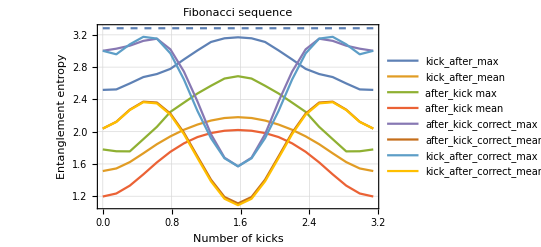

```mathematica
Show[ListLinePlot[{wkafibomax,wkafibomean,wfibomax,wfibomean,fibomax,fibomean,kacfibomax,kacfibomean},PlotTheme->"Detailed",PlotLegends->{"kick_after_max","kick_after_mean","after_kick max","after_kick mean","after_kick_correct_max","after_kick_correct_mean","kick_after_correct_max","kick_after_correct_mean"}],Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of kicks],None}},PlotLabel->HoldForm["Fibonacci sequence"],LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]},PlotRange->All]
```

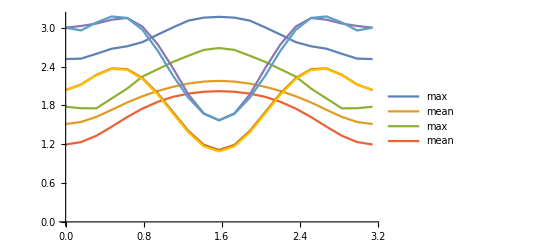

```mathematica
ListLinePlot[{wkafibomax,wkafibomean,wfibomax,wfibomean,fibomax,fibomean,kacfibomax,kacfibomean},PlotLegends->{"max","mean","max","mean"}]
```